# Time using Andes

Corrolate time actually used with time reported on questionnaire.
Spring 2007 has no questionnaires and the log file does not have the header fields.

Needs to be chopped up?

```mathematica
questions={{"Year","Semester","School","Section","CourseID","Name","Date","Time","1","2","3","4","5","6","7","8A","8B","9","10","11A","11B","11C","11D","11E","11F","11G","11H","11I","11J","11K","11L","12A","12B","12C","12D","12E","13A","13B","13C","13D","14","15","16A","16B","16C","16D","16E","17","18A","18B","18C","18D","19","20","21","22","23A","23B","23C","23D","23E","24","25","26","27","28","29","30","30A","30B","30C","30D"},
{2006,,,"Dec42006",,"bobh","04 Dec 2006","14:02:53",5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,,5,"NA",5,"NA",5,5,5,5,5,5,5,5,5,5,5,5,5,"N","N","N","N",,,5,5,"on","on","on","on","on","Question24","Question25","Question26","Question27",5,5,"NA","[Q30A]","[Q30B]","[Q30C]","[Q30D]"},
{2006,,,"instructor",,"tmwilbur","04 Dec 2006","15:36:17",1,3,"[Q3]","[Q4]","[Q5]",3,4,"[Q8A]","[Q8B]","[Q9]","[Q10]",1,1,2,4,2,3,2,5,4,3,2,,2,3,2,"NA",1,1,2,4,"[Q13D]",1,4,1,1,2,1,1,"NA","[Q18A]","[Q18B]","[Q18C]","[Q18D]","5-6 mins","3-4 then 1-2",5,"[Q22]","[Q23A]","[Q23B]","[Q23C]","[Q23D]","[Q23E]","Requiring 1.the use of symbolic equations, 2. the student toalways explicitly identify vectors and 3. defining a cordinate system.\nBut later on, when a student draaws irrelevant (but real and existing)\nforces, Andes turns \"Red\"","Lack of help in the energy section.","Define all relevant vectors on a FBD, independent of whetherthe force is required to solve the particular problem.","Can' think of any.  It is fairly stragith forward.",3,"NA",1,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,12334,,"xxxxx","04 Dec 2006","16:07:58",1,2,3,4,5,1,2,3,4,5,1,1,2,3,4,5,1,2,3,4,5,1,,2,3,4,5,"NA",1,2,3,4,5,1,2,3,4,5,1,2,"Y","N","Y","N",84.372,0.529,3,1,"on","[Q23B]","on","on","[Q23E]","Nothing!","Having to use it!","Delete it!","An ignore butto n.",1,3,3,"[Q30A]","[Q30B]","[Q30C]","on"},
{2006,,,4321,,"yyyy","04 Dec 2006","16:28:47",5,4,3,2,1,5,4,3,2,1,5,4,3,2,1,"NA",5,4,3,2,1,5,,4,3,2,1,"NA",5,4,3,2,1,5,4,3,2,1,5,4,"Y","Y","N","N",0.238,15,5,4,"on","on","on","[Q23D]","[Q23E]","Pretty pictures.","I had to actually do problems to completion.  What a bummer.","Yes.  I couldn't write on the screen.","A few funny problems.  There has to be some humor somewhere inPhysics.",1,2,3,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,13579,,"TTTTT","04 Dec 2006","16:43:03",1,2,3,4,5,4,3,2,1,3,4,5,"NA",5,4,3,2,1,2,3,4,5,,"NA",4,3,2,1,2,3,4,5,4,3,2,1,2,3,4,5,"N","Y","N","Y",53.7,1.13,1,5,"on","on","on","on","[Q23E]","It seemed to give a collection of different responses to thesame question???","Same as above.","Free-hand graphics.","Better next step help.",3,3,3,"on","[Q30B]","[Q30C]","[Q30D]"},
{2006,,,1234,,"bobh","05 Dec 2006","08:44:03",3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,"Y","Y","Y","Y",12,23,3,3,"on","on","on","on","on","question24","question25","question26","question27",3,3,3,"on","on","on","on"},
{2006,,,1234,,"bobh","05 Dec 2006","08:44:57",3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,"Y","Y","Y","Y",12,23,3,3,"on","on","on","on","on","question24","question25","question26","question27",3,3,3,"on","on","on","on"},
{2006,,,3324,,"092178","05 Dec 2006","10:12:29",5,5,5,3,5,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,1,1,1,3,3,3,2,"N","N","N","N",10,5,3,5,"on","on","on","on","[Q23E]",,,,,5,5,5,"[Q30A]","on","on","[Q30D]"},
{2006,,,3324,,"092586","05 Dec 2006","10:12:38",1,4,2,3,2,4,5,2,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,4,3,2,4,2,2,2,2,2,3,1,4,4,3,2,5,3,"Y","Y","N","N",4,"1-2",4,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]",,"limited understanding of user inputs.  Requires more work bedone than really necessary",,,3,2,2,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,3324,,"m096378","05 Dec 2006","10:12:11",2,3,4,2,3,1,5,2,4,2,2,1,1,1,1,1,1,1,1,1,1,1,1,3,5,4,2,2,2,1,3,2,3,4,2,2,2,2,2,4,"N","N","N","N",15,4,5,1,"[Q23A]","[Q23B]","[Q23C]","[Q23D]","[Q23E]",,,,,3,3,3,"[Q30A]","on","on","[Q30D]"},
{2006,,,3324,,"m093546","05 Dec 2006","10:12:37",2,4,2,4,2,1,4,2,2,3,2,2,3,2,2,3,2,2,3,2,3,2,3,1,1,1,2,2,2,2,2,2,2,3,2,2,1,1,2,3,"Y","Y","N","N",5,2,3,2,"[Q23A]","on","on","[Q23D]","[Q23E]","Helping you figure out how to do problems.","Not being able to solve problems with variables in them.","Solve problems with variables.","SOlve problems with variables.",3,2,2,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,3324,,"095370","05 Dec 2006","10:14:22",5,4,4,2,3,3,4,4,4,3,3,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,4,2,2,2,2,2,2,2,2,2,2,3,"N","N","N","N",20,6,4,3,"[Q23A]","on","[Q23C]","on","[Q23E]",,"Andes doesn't really allow me to learn the physics material,but rather just to put in variables and equations that I don't actually\nunderstand.  If I would have done these problems on paper I would have\nbeen able to comprehend the material better.  Also the amount of time I\nspent doing andes was rediculous and left little time for other homework.\nBy the end of the semester, I had lost all motivation to do andes because\nI simply did not have the time and didn't feel any benefit from doing the\nproblems.",,,5,5,3,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,3324,,"095730","05 Dec 2006","10:15:23",4,3,4,5,2,2,3,2,3,5,5,1,1,2,5,3,4,3,3,4,1,3,4,2,2,2,2,2,5,5,5,5,1,2,2,2,2,2,3,2,"N","N","Y","Y",10,"2+",2,1,"on","on","[Q23C]","[Q23D]","[Q23E]","you rarly get stuck, you can keep going","sensitivity of program (syntax)...etc","no","no",3,3,1,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,3324,,"090600","05 Dec 2006","10:15:54",2,3,1,4,1,2,2,2,1,3,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,4,4,2,4,4,3,2,3,1,1,1,1,1,4,"Y","Y","Y","Y",15,2,3,1,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","The concept of breaking to concepts down into thefundamentals.","Figuring out how to enter parts of the problem.  You couldknow what you had to put in, but not know the proper format for entering\nit.","Calculate the solution on our own.","Make entering values, givens, and variables easier and moreuser-friendly.",3,1,2,"[Q30A]","on","on","[Q30D]"},
{2006,,,3324,,"094836","05 Dec 2006","10:16:50",5,5,5,3,2,2,5,4,4,5,5,3,3,3,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,2,2,1,3,2,"NA","N","N","N","N","10 to 15","2-3",3,3,"[Q23A]","on","on","[Q23D]","[Q23E]","Repition and proression of difficulty","Teaches more how to manipulate a computer program, not dophysics","NO","Not in particluar...maybe be allowed to copy and past eqn'sfrom the review eqn's sheet into problems",5,4,5,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,3324,,"095532","05 Dec 2006","10:18:31",1,5,4,4,1,2,4,2,2,3,2,2,2,2,3,3,3,2,2,2,2,2,2,2,2,3,1,3,3,3,3,2,1,2,1,2,1,1,1,3,"N","N","Y","Y",40,3,1,2,"on","on","[Q23C]","[Q23D]","[Q23E]","Instant feedback.","Syntax.","directly copy equation from equation page",,2,3,1,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,3324,,"081308","05 Dec 2006","10:16:56",2,3,3,5,2,1,4,3,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,3,2,3,4,1,1,1,2,2,2,"N","N","N","N",18,2,5,2,"on","[Q23B]","[Q23C]","[Q23D]","[Q23E]","I liked having the help button because you could use it anumber of times when you didn't understand the problem and then when you\nfinished it you had something to go back to and learn how to do it.","It is extremely inconvient when there are errors in the systemand you have to go find your professor to fix them.","No","No",3,3,2,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,3324,,"090366","05 Dec 2006","10:18:00",1,3,1,5,1,1,5,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,3,3,1,1,3,1,1,1,1,4,1,1,1,1,1,5,"Y","Y","Y","Y",30,"1-2",5,2,"on","on","[Q23C]","[Q23D]","[Q23E]","light bulb and whats wrong function","being a computer","be a more open interface wiht problems","see above",3,1,1,"[Q30A]","on","on","[Q30D]"},
{2006,,,3324,,"091650","05 Dec 2006","10:18:50",5,4,5,2,4,1,5,3,3,4,2,1,2,2,2,3,4,2,2,2,2,3,4,2,2,2,3,3,4,2,5,3,3,3,1,1,3,3,2,5,"N","N","N","N","20+","4-5",3,5,"[Q23A]","on","[Q23C]","on","[Q23E]","Concept teachings.","Very difficult to do when habits for Physics from high schoolhas already been in place.","N/A","Would much rather not do Andes.",5,5,3,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,3324,,"094626","05 Dec 2006","10:15:51",1,3,2,4,1,1,3,1,3,3,2,1,1,1,1,2,"NA","NA","NA","NA","NA","NA","NA",1,2,2,"NA",2,2,1,3,3,3,4,2,2,2,2,2,5,"N","N","N","N",30,2,4,4,"[Q23A]","on","on","[Q23D]","[Q23E]","Definitely the Tutor","Learning the syntax","No","No",5,2,2,"[Q30A]","on","on","[Q30D]"},
{2006,,,3324,,"092808","05 Dec 2006","10:19:58",4,3,4,3,2,3,3,4,4,3,4,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,1,3,1,1,4,3,2,2,1,1,4,4,1,1,"N","N","N","N",10,3,4,5,"on","[Q23B]","[Q23C]","on","[Q23E]","It helped to visually see the problem.","I don't think learning this program was a good method tolearning physics. I already had difficulties in physics and then adding a\nnew program to learn made it more difficult. I would've rather done\nregular book homework when I can work out the problem. Andes makes it more\ndifficult to figure out concepts. Andes would frequently not be able to\nhelp with the hints and it was more confusing to use it.",,,5,5,4,"[Q30A]","on","on","[Q30D]"},
{2006,,,3324,,"094968","05 Dec 2006","10:20:08",3,4,3,5,1,1,4,5,4,3,3,3,3,3,3,3,3,3,3,3,3,4,3,"NA",2,2,"NA","NA",1,1,2,2,3,3,1,1,1,2,1,3,"N","N","N","N",15,1,3,5,"on","[Q23B]","on","on","[Q23E]","The help functions helped me greatly","The syntax.  the first problem of each section always took along time because I didnt know what the program wanted. once i figured out\nwhat it wanted, i was able to get through the rest of the problems much\nquicker",,"Have more obvious variables already defined",5,3,5,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,3324,,"096342","05 Dec 2006","10:20:18",5,4,4,4,1,2,4,3,4,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,3,2,2,3,4,3,2,2,2,1,4,3,3,3,3,3,"Y","N","N","N",12,2,3,2,"on","on","[Q23C]","on","[Q23E]","Andes was useful in determining the method to solve problemsin which the student was unsure.  The help function was useful to teach\nthe method.","The greatest weakness of Andes was its inconsistency.  Manytimes there would be a point in the problem that Andes would become\nconfused, or you would need to enter a value for a constant, such as the\nacceleration due to gravity, and it would not allow it.  This would force\nme to then do twice the work, as I would have to solve the problem by\npencil and paper.","Often program in constants, such as gravity.  I also wish theconstants were just programmed in to begin with, so there would be more\nconsistent symbolic equations throughout the class, in case there is a\nquestion, it would be easier for everyone to see where they went wrong.","I would like to see the capability of the solve fuctionexpanded so that it could handle some of the larger numbers that were\nencountered.",5,4,3,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,3324,,"093756","05 Dec 2006","10:22:29",5,3,5,2,1,2,4,1,4,5,5,1,1,1,2,2,2,2,2,3,3,3,3,4,3,5,2,3,4,2,3,1,3,3,1,1,2,2,2,3,"Y","Y","N","N",15,5,2,4,"on","[Q23B]","[Q23C]","on","[Q23E]",,,,,3,3,2,"[Q30A]","on","on","[Q30D]"},
{2006,,,3324,,"095400","05 Dec 2006","10:20:27",3,3,2,3,2,2,3,2,3,4,2,1,1,1,2,2,3,4,4,4,2,2,2,2,5,4,3,3,4,3,3,3,3,4,2,2,3,4,1,3,"N","N","N","N",30,10,4,3,"[Q23A]","on","on","[Q23D]","[Q23E]","the tutor.","the light bulb often did not answer tghe question i wanted toask. sometimes i woujld be 3/4 the wayh done with the problem and get\nstuck. i would then go to the light bulb menu and it would make me go\nthrough all the steps that i already went through. I.E. i hit the lgiht\nbulb and it told me to define an equuation for this problem. i told it\nwhat equation and it said\" very good, you have already defined this\nequation and you can move on to the next step\". i already know that i have\ndefined that equation so why even bother telling me that i have.","N/A","for 3D problems it would be nice to see the diagrams that wehave to draw in 3D. if that is possible.",3,3,3,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,3324,,"m090228","05 Dec 2006","10:20:28",2,3,2,4,1,2,2,2,2,3,2,1,2,2,1,3,3,4,4,4,2,1,2,1,1,4,"NA",5,2,4,4,1,1,2,1,1,2,3,1,"NA","Y","Y","Y","Y",3,1,4,4,"on","[Q23B]","[Q23C]","on","[Q23E]","Making us use symbolic equations.","Sometimes the problem can be solved without every symbolicequation that applies.  With Andes, you can't progress unless you enter in\neverything it's looking for.  Then of course there seem to be occassional\nglitches that hinder particular problem.  That's understandable, but needs\nto be fixed.","I wish I could write exponents as actual superscripts.  I finda tendency to write ^2 when doing work on paper now, which I don't like.","The light-bulb could be cumbersome.  If you just need the nextstep, and little hints won't help, there should be a button for that.  If\nI don't know what equation to use, I have to pick 2 random equations from\nthe window, then Andes will just give me what I need.  Also, the sound\nequations are not on there (I=Iref*10^(db/10) or whatever it is).",2,1,1,"[Q30A]","[Q30B]","on","[Q30D]"},
{2006,,,3324,,"090816","05 Dec 2006","10:20:15",5,5,5,1,5,1,5,4,5,5,4,2,4,3,3,3,5,3,3,3,2,2,2,3,4,3,2,3,4,2,5,2,4,5,1,1,1,1,1,4,"N","N","N","N","too long","too long",4,5,"[Q23A]","on","on","on","[Q23E]","The automatic solver.","The tediousness of it.","I would have like to skip around from time to time.","Allow students to go on the another problem if they are unableto do another.",5,5,4,"[Q30A]","on","[Q30C]","on"},
{2006,,,3324,,"093216","05 Dec 2006","10:20:55",4,4,5,2,4,3,4,4,3,4,4,2,2,2,3,3,3,3,3,3,4,4,4,5,3,5,3,4,4,4,5,3,3,3,2,2,2,2,3,3,"Y","N","N","N",20,3,3,5,"[Q23A]","on","on","on","[Q23E]","Diagrams","The format for inputing what I know.","Put in the right equations","Some of the feedback was very vague.",5,5,3,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,3324,,"095874","05 Dec 2006","10:21:58",1,4,2,5,2,1,5,1,1,3,2,3,3,3,3,3,3,3,3,3,3,3,3,5,1,1,1,"NA",2,2,1,1,1,3,1,1,5,5,1,3,"Y","Y","Y","Y",20,5,3,4,"[Q23A]","on","[Q23C]","[Q23D]","[Q23E]",,,,,5,1,1,"[Q30A]","on","on","[Q30D]"},
{2006,,,3324,,"092244","05 Dec 2006","10:29:34",5,3,5,1,4,3,3,5,5,5,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,4,4,5,4,5,3,1,2,4,4,4,1,"Y","N","N","N",20,3,3,2,"[Q23A]","on","on","on","[Q23E]","pretty pictures","all the computer equations","no",,5,5,5,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,"M5B",,"rommelk","05 Dec 2006","13:14:26",1,3,2,4,1,1,5,2,2,2,3,2,2,2,2,2,2,2,2,"NA","NA",2,,1,1,1,3,3,2,2,3,1,1,2,1,1,2,2,1,4,"N","Y","Y","Y",20,5,3,3,"on","on","[Q23C]","[Q23D]","[Q23E]","The light bulb and equations page.","Sometimes it did not know where to go next on a hint or couldnot figure out what was wrong.","Not that I can think of.","Simple and doesn't worry about making it all colorful andpretty.  Easy and to the point.",1,1,1,"on","on","[Q30C]","on"},
{2006,,,5524,,"096708","05 Dec 2006","13:45:04",1,3,1,5,2,1,5,1,1,1,1,1,1,1,1,1,2,1,2,1,1,2,2,2,2,1,1,1,1,2,3,1,1,4,1,1,1,1,2,3,"Y","Y","Y","Y",9,3,5,1,"[Q23A]","on","[Q23C]","[Q23D]","[Q23E]","It helped me to actually learn physics, not just memorizeequations. It gives good help and feedback, I could see what I needed to\nwork on. I liked the problem sets, by the end of each one I knew the topic\nthat was being covered pretty well.","Sometimes defining variables wa a pain to figure out how andeswanted it, and sometimes it made me do things that was not necessary for\nthe problem. But overall it is a great program I want to use it next\nsemester.","no","nothing",1,1,1,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,5524,,"093822","05 Dec 2006","13:45:50",1,4,2,4,1,1,4,1,1,3,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,4,"NA",1,2,1,1,1,1,2,1,1,1,1,1,4,"Y","Y","Y","Y","10-20","3-4",4,3,"[Q23A]","on","[Q23C]","[Q23D]","[Q23E]","The red and green highlighting feature that showed if the userwas correct in the text that he entered.","The lack of help it gave when the user asked to \"Explainfurther\"","No.","I would like to see more help provided to the user when heasks for the program to \"Explain further\" Also, sometimes when the program\ntold the user to draw a body diagram and the diagram was drawn, the\nprogram would say it was incorrect.",2,1,1,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,5524,,"091608","05 Dec 2006","13:44:04",4,4,4,4,1,2,5,2,3,3,5,1,2,2,2,3,3,3,2,2,3,3,3,2,2,2,4,3,3,2,2,3,3,3,2,2,1,2,3,3,"Y","N","N","N",30,3,1,5,"[Q23A]","on","on","on","[Q23E]","It was good that it would solve the problems algebraically.","The equations had to be entered in perfectly symbolically towhat Andes wanted/needed.","N/A","N/A",5,4,4,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,5524,,"091620","05 Dec 2006","13:44:38",4,4,4,3,2,4,3,2,4,4,4,3,3,3,3,2,3,2,2,2,4,5,4,2,3,2,4,3,4,1,4,1,2,3,2,2,4,5,4,2,"Y","Y","Y","Y",15,2,3,2,"on","on","on","on","[Q23E]","Help when you get stuck, but only when it actually worked.","Too obscure, type in equations and out pops an answer.","See what numbers and values were used during calculations onanswers.",,4,4,3,"[Q30A]","on","on","[Q30D]"},
{2006,,,5524,,"090756","05 Dec 2006","13:44:51",4,4,2,4,4,2,3,4,5,4,3,3,2,2,2,3,2,2,3,3,3,4,3,4,3,3,3,4,4,3,4,3,3,2,4,2,3,3,2,1,"Y","N","N","Y",25,1,4,2,"[Q23A]","on","[Q23C]","on","[Q23E]","Having me use various equations I may not have previouslyknown how to use","The precision of the Andes program on certain problems. Small,useless information was required to be entered to proceed, or the program\nwould not be able to solve the answer after I spent 30 minutes on the\nquestion.","Jump between problems.","no",4,2,2,"[Q30A]","[Q30B]","on","[Q30D]"},
{2006,,,5525,,"091704","05 Dec 2006","13:46:31",3,3,2,5,1,1,5,1,4,5,3,2,1,1,2,2,2,1,1,1,2,2,2,3,3,3,3,3,5,5,5,4,2,3,1,1,2,2,1,4,"N","N","N","N",15,3,3,3,"on","[Q23B]","[Q23C]","[Q23D]","[Q23E]","You are allowed to learn by seeing the correct solutions andmethods and not shown the wrong methods which can sometimes be confusing\nwhen stored in your memory. It also allowed you to understand every step\nof the problem and why every solution resulted and what from to help you\nunderstand how to put all the equations together for larger aspects.","The misunderstanding of a computer program at first andgetting to know the language","no","Give better hints and not ones that are irrelevant that say togo on and solve the problem but it won't let you",5,3,1,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,5524,,"095364","05 Dec 2006","13:44:11",4,3,5,1,5,4,2,5,5,5,5,2,4,3,4,3,3,4,4,2,2,3,3,2,2,2,3,5,3,2,3,3,4,2,4,2,3,5,2,1,"N","N","N","N",10,"3-4",5,5,"on","[Q23B]","on","on","on","It didn't require handwriting.","They were not fun or easy, so I didnt care what I learned aslong as I finished the problem.","Solve for the answer everytime, and not worry about casesenstive variables.","The whole program, becuase it didnt teach me anything.",5,5,4,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,5524,,"095418","05 Dec 2006","13:49:25",4,3,4,4,2,2,5,2,3,3,3,2,3,3,"NA",3,3,2,4,4,3,4,4,2,1,2,2,4,3,2,3,3,2,2,4,3,2,2,1,4,"Y","N","Y","N",30,2,5,1,"[Q23A]","on","on","[Q23D]","[Q23E]","It is very visual and has the option to \"Review PhysicsEquations\"","It is still in its early stages so it does not have drawingsthat are to scale nor enough organization to really \"see\" what is going on","Drawings to scaleInput review equations by clicking on them (instead of having to retype)\nAutomatic axes","It needs to be used on tests if it is used on homework.  Itwas hard to transistion from Andes to pencil and paper for the tests",4,2,3,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,5524,,"093564","05 Dec 2006","13:49:25",3,3,4,3,1,1,5,3,4,4,2,3,3,3,3,3,3,3,3,3,3,3,3,5,5,5,5,5,4,4,5,3,4,1,4,1,1,1,2,3,"N","N","N","N",10,1,3,3,"[Q23A]","on","on","on","[Q23E]","Andes explains to you how to do a problem if you're not sure.It also helps you to figure out what you're doing wrong.","Confusing syntax and the long, tedious process of defininglots of variables, some of which aren't always needed for the problem, but\nANDES needed them anyway.","work faster on easy problems or do them in my head.","Get rid of the tutor.",5,5,2,"[Q30A]","on","on","[Q30D]"},
{2006,,,5524,,"097140","05 Dec 2006","13:46:06",3,4,3,4,1,1,5,1,3,3,2,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,1,1,2,1,3,2,2,2,1,2,2,1,"N","N","N","N",10,"1-2",5,4,"[Q23A]","on","on","on","[Q23E]","Lightbulb/solve.","Gated problems and those damn survey questions.","In a later version, it would be cool to make an object and (ifa box was sliding across a table) have the object actually move along the\nvelocity arrow to display motion.","Get rid of the gated questions.",1,1,1,"[Q30A]","on","on","[Q30D]"},
{2006,,,5524,,"095826","05 Dec 2006","13:50:21",2,3,2,3,1,1,4,1,2,1,1,1,1,2,1,2,3,2,2,2,2,2,2,4,5,3,3,3,2,2,4,2,1,3,2,1,1,1,1,2,"N","N","Y","Y",15,2,4,1,"[Q23A]","[Q23B]","on","on","[Q23E]","Instant feedback","The failure of Andes to recognize when a line of code is closeto being right and then provide us with irrelevant hints.","no","add a feature that will let me know if my line of code iscorrect but not necessary",3,3,1,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,5524,,"096060","05 Dec 2006","13:42:31",2,3,3,4,1,1,4,2,2,3,1,2,2,1,2,2,1,2,2,3,1,2,1,2,2,1,4,3,2,2,4,3,2,2,1,1,2,1,1,3,"Y","Y","Y","Y",15,3,3,3,"on","on","[Q23C]","[Q23D]","[Q23E]","Helping get across the ideas of the physics lessons we weretrying to learn.","Sometimes the syntax was hard to conquer and at times the helpfeature wasnt that helpful.","No, other than more help features when i got stuck.","No.",2,1,1,"[Q30A]","on","on","on"},
{2006,,,5524,,"097134","05 Dec 2006","13:49:19",4,4,4,2,3,1,4,3,3,4,3,2,3,2,2,4,3,4,4,3,2,2,2,2,4,2,3,3,2,3,2,2,2,4,3,2,1,1,4,4,"N","N","N","N",20,"2-3",5,4,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","Symbolic equations and the equation solver eliminatedmathematical errors.","Too time consuming to do problems and harder to tranlate topencil and paper for quizzes and tests.","Gated problems were frustrated and made me get really farbehind on problems when I couldn't solve one.","I would like a quicker way to declare variables.  Especiallyduring the Work problems, declaring KE and PE took inordinate amounts of\ntime.",4,3,2,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,5524,,"m092142","05 Dec 2006","13:50:55",2,3,2,4,2,2,4,2,3,3,1,1,1,2,1,1,2,2,1,1,2,1,1,3,2,2,"NA",1,1,1,2,1,2,3,2,1,2,1,2,5,"Y","Y","Y","Y",25,2,4,2,"[Q23A]","on","[Q23C]","on","[Q23E]","Andes was really good at showing a variety of problems andproviding help with them.","There are limitations to technology.","It was a very good tool and I cannot think of anything that Iwould like to change as of now.","Only upgrading the help as time goes on but that will comewith time; only so much can be done as of this point I think.",1,2,2,"[Q30A]","on","on","[Q30D]"},
{2006,,,5524,,"092478","05 Dec 2006","13:51:44",3,3,3,4,2,2,4,2,2,2,2,2,2,2,3,3,3,2,2,2,2,3,3,2,2,2,3,3,3,3,4,3,2,4,2,3,3,2,3,"NA","Y","Y","Y","Y",15,2.5,4,2,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","It is a great tool to practice.  It provides an alternative tosimply writing.  It is organized and helps students to understand a\nproblem through individual steps.","DIfficult to define variables and write equations.","I wish there were a tool that showed a few more methods froentering equations.  Many were displayed on the equations pages, but\nfunctions such as log were not included.","NA",3,"NA",2,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,5524,,"094200","05 Dec 2006","13:49:35",2,4,4,5,1,4,4,2,2,3,1,2,2,2,2,2,3,2,2,2,2,3,3,3,3,3,1,1,3,4,3,1,2,2,1,1,2,2,1,3,"N","N","N","N",10,3,4,1,"[Q23A]","[Q23B]","on","on","[Q23E]","The solve function made it more enjoyable to do the homeworkbecause I didnt have to break out my calculator and crunch numbers, but it\nalso didnt help me get used to rearranging equations to actually solve for\nanswers like i had to do on tests.","It took off points when I made simple typos or mistakes madefrom not understanding how to work andes. It was frustrating having to do\neverything exactly how andes wants it, which can sometimes be more\ncomplicated.",,,4,3,2,"[Q30A]","on","on","[Q30D]"},
{2006,,,5524,,"093990","05 Dec 2006","13:47:26",2,3,2,4,2,1,3,2,1,2,2,1,2,1,1,2,3,2,3,3,3,2,2,2,2,1,1,3,2,1,3,1,1,4,1,1,2,1,1,5,"N","Y","Y","Y",30,6,3,1,"[Q23A]","on","[Q23C]","on","[Q23E]","When you hit the help or light bulb, it will go through how tofigure out this certain problem.  You are then able to judge what concepts\ngo with what type of problems. It also forced me to use the variables\n(though annoying) which helped me understand where equations derive from","just some questions, some bugs","N/A","N/a",2,1,2,"[Q30A]","on","on","[Q30D]"},
{2006,,,5524,,"096600","05 Dec 2006","13:49:13",2,4,1,5,1,1,5,1,1,2,2,1,2,1,2,2,2,1,2,2,2,1,2,1,1,1,2,1,3,2,3,1,3,4,1,1,1,1,1,3,"Y","Y","Y","Y",10,2.5,3,1,"[Q23A]","on","[Q23C]","[Q23D]","[Q23E]","The lightbulb option which helped tutor me when I was stuck oncertain problems.","Defining variables was hard sometimes because the directionsweren't specific.","No.","No.",2,1,1,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,5524,,"092904","05 Dec 2006","13:49:40",3,4,3,2,2,3,2,2,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,3,3,2,2,3,1,2,3,2,2,4,3,3,4,"N","N","Y","Y","20 min","6-7",2,4,"on","on","[Q23C]","[Q23D]","[Q23E]","It helped you if you didn't know what the the question wasasking or if you were just lost.","It solved the problem for you. It didn't let you solve themyourself.","Nope","Nope",2,1,1,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,5524,,"094104","05 Dec 2006","13:55:26",5,3,5,1,2,4,1,4,4,4,2,3,3,3,3,2,4,3,3,3,5,5,4,3,2,1,2,3,5,2,4,3,4,2,1,1,4,4,2,2,"N","N","N","N",35,7,5,4,"on","[Q23B]","on","on","[Q23E]","The help function","The do not explain the equations well.  The survey doneafter/before the problem should be done during the problem.","Not take away so many points during questions.","More help to allow the student solve the problem own his orher own.",5,4,2,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,5524,,"094062","05 Dec 2006","13:52:00",2,3,2,4,1,3,3,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,5,2,1,2,1,2,4,3,4,3,3,2,4,"N","Y","Y","Y","10-15",3,3,1,"on","[Q23B]","[Q23C]","[Q23D]","[Q23E]","It provided assistance early on, which saved time and helpedto grasp a better understanding of the problem.","The Explanation's were too long and sometimes did notadequately answer the problem.","Use my own form of equations.  Things had to be very specificand I wish I could input my own form of the equation to solve the problem.\nSometimes this was easier than actually letting Andes solve it for me.",,3,1,1,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,5524,,"096618","05 Dec 2006","13:56:29",1,3,1,4,1,2,3,1,2,2,1,2,2,1,4,2,3,2,2,3,3,3,3,2,3,3,"NA","NA",2,1,2,"[Q13D]",2,3,4,2,3,1,1,5,"N","N","Y","Y",20,10,4,1,"[Q23A]","on","[Q23C]","on","[Q23E]","The equations page, and a good portion of the light bulb help,but not all of it.","The fact that I had to define every single variable, even ifit wasn't going to be used, to get the light bulb help to tell me anything\nuseful. And many times it would tell me to do something I already did, but\nAndes told me was wrong. It seemed to sometimes get into an endless loop.\nThere was one problem that I wasn't able to complete because the light\nbulb kept telling to to redefine variables, and change things, but then\ntold me it was all wrong.","Without using the lightbulb, I would like to be able to clickon the review phyiscs equations page, and have one of the equations drop\ndown after clicking on it, or stay open, so that I would not get penalized\nsince I know the equation I want to use. This would allow me to see the\nequation, just as though it were my paper equations sheet, and type in\nvariables in that format without having to waste time on the light bulb\nhelp.",,1,1,1,"[Q30A]","on","on","[Q30D]"},
{2006,,,5524,,"092406","05 Dec 2006","14:02:37",1,3,1,5,1,1,5,1,1,"[Q9]",1,1,1,2,2,2,2,1,1,3,1,1,1,3,2,2,2,2,2,1,1,"[Q13D]",3,4,1,1,1,1,2,5,"Y","Y","Y","Y",15,3,5,1,"[Q23A]","[Q23B]","[Q23C]","[Q23D]","[Q23E]","Seeing the concepts and problems visually, being able to takemy time learning the concepts and ideas behind a problem, and having hints\nimmediately available.","It took a couple weeks to get the hang of how to use it.","Chemistry, statics, calculus, and western civilization.","Expanded equations page.",1,1,1,"[Q30A]","[Q30B]","on","[Q30D]"},
{2006,,,"m4a",,"mayorj","05 Dec 2006","14:54:11",2,3,2,3,3,4,4,3,3,3,4,2,2,2,3,3,2,4,4,5,5,5,,2,3,2,3,2,2,3,3,3,2,2,2,1,3,4,4,2,"N","N","N","N",5,1,2,3,"on","[Q23B]","[Q23C]","[Q23D]","[Q23E]",,,,,2,3,4,"on","[Q30B]","[Q30C]","[Q30D]"},
{2006,,,"M4",,"ludviceke","05 Dec 2006","16:20:26",4,3,3,5,1,1,5,1,1,4,4,2,2,2,2,2,2,2,2,2,2,3,,5,2,1,2,"NA",2,2,2,2,2,2,1,1,4,4,3,1,"Y","Y","N","N",5,.5,4,5,"on","on","[Q23C]","[Q23D]","on","Drawing diagrams - helped visualize the problem better.","The problems were never like those in GRs.","No.","No.",2,3,3,"on","on","[Q30C]","on"},
{2006,,,"M5C",,"freys","05 Dec 2006","16:19:04",4,3,4,5,1,1,5,2,1,2,2,5,5,5,5,5,5,5,5,5,5,5,,1,2,2,"NA",2,2,2,3,3,1,3,2,2,4,4,1,1,"Y","N","N","N",10,2,4,4,"on","[Q23B]","[Q23C]","on","[Q23E]","-The forced problem solving strategy.","-Frequent updates and drastic change sin problemprocedure/syntax that had to be learned for a particular problem set to go\nsmoothly.","N/A","-Make it possible to solve portions on ones own.",4,2,2,"on","on","[Q30C]","[Q30D]"},
{2006,,,"M5C",,"hutchisonl","05 Dec 2006","16:33:17",2,3,2,5,1,1,5,3,2,3,3,2,3,3,3,2,3,2,3,3,4,4,,1,1,1,1,1,4,4,5,3,2,2,1,1,1,1,3,1,"Y","Y","N","N",15,1.5,2,4,"on","on","on","[Q23D]","[Q23E]","Drawings","Difficulty of computer skills","NO","No",3,1,1,"[Q30A]","[Q30B]","[Q30C]","on"},
{2006,,,"M5C",,"davom87","05 Dec 2006","17:22:31",3,3,4,2,2,1,5,2,3,2,4,2,"NA",4,3,1,"NA",3,3,3,"NA",1,,1,1,1,2,4,3,1,3,3,4,4,4,2,2,1,1,3,"N","Y","Y","Y",15,2,3,"NA","on","[Q23B]","on","on","[Q23E]","You can see the step by step process of each problem","The syntax can be confusing sometimes","Not really.","Sometimes the hints didnt work, but it was pretty good most ofthe time",1,2,2,"on","[Q30B]","[Q30C]","[Q30D]"},
{2006,,,"T5C",,"hultins","05 Dec 2006","18:22:50",3,3,2,4,1,3,3,2,3,2,2,2,2,2,2,1,1,1,2,2,2,2,,1,3,2,3,3,2,3,3,4,3,2,2,2,1,1,3,1,"N","N","Y","Y",20,"2-3",4,1,"on","on","[Q23C]","[Q23D]","[Q23E]","Its ability to give you a definite answer for the solution,with the proper steps in between.","The lack of repeating doesn't make the information moreconcrete","Have a better explanation of everything we just did after wesolved for the answer.","Fewer errors.",4,3,1,"on","[Q30B]","[Q30C]","on"},
{2006,,,"M3A",,"TubmanW","05 Dec 2006","23:06:42",2,3,3,2,2,2,4,3,3,2,2,2,2,2,2,2,2,2,2,2,"NA","NA",,2,2,2,3,3,3,2,2,1,2,2,3,4,3,3,3,2,"N","N","N","N",10,2,4,5,"[Q23A]","on","[Q23C]","[Q23D]","[Q23E]","Being able to help you right there when you were stuck","Stupid syntax errors that you couldve gotten docked points for","Type the equations when the equation sheet was open.",,3,1,1,"on","on","[Q30C]","[Q30D]"},
{2006,,,"M6A",,"kinchen","06 Dec 2006","01:07:29",1,2,1,5,1,1,5,3,2,4,3,1,1,1,1,1,1,1,1,1,1,1,,2,1,1,3,2,1,1,1,1,1,4,1,1,1,1,1,3,"Y","Y","Y","Y",10,1.5,3,4,"[Q23A]","[Q23B]","[Q23C]","[Q23D]","[Q23E]","Working out problems completely from beginning to end.","N/A","N/A","N/A",1,5,1,"on","on","[Q30C]","[Q30D]"},
{2006,,,001,,"Steven Chong","06 Dec 2006","09:29:16",3,3,4,3,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,4,2,3,3,2,4,2,2,3,4,1,1,4,3,2,"NA","Y","Y","Y","Y",20,4,3,3,"on","on","[Q23C]","on","[Q23E]","it forces you to know everything about the problem and work itout until you solve it.","sometimes the help option does not help. it would not givehelp, instead it would repeat the same phrases over and over.","none comes to mind","g=9.8m/s^2 should be a constant",2,3,"NA","[Q30A]","[Q30B]","on","[Q30D]"},
{2006,,,001,,"phy111","06 Dec 2006","09:28:55",3,3,4,3,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,4,2,3,3,2,4,2,2,3,4,1,1,4,3,2,"NA","Y","Y","Y","Y",20,4,3,3,"on","on","[Q23C]","on","[Q23E]","it forces you to know everything about the problem and work itout until you solve it.","sometimes the help option does not help. it would not givehelp, instead it would repeat the same phrases over and over.","none comes to mind","g=9.8m/s^2 should be a constant",2,3,"NA","[Q30A]","[Q30B]","on","[Q30D]"},
{2006,,,001,,"kal srour","06 Dec 2006","11:55:05",2,3,2,4,1,3,3,1,1,2,1,2,2,1,2,2,1,2,2,2,1,"NA",4,2,2,"NA",2,"NA",2,3,3,2,2,2,1,1,1,1,1,"NA","Y","Y","Y","N","15 min",10,5,2,"[Q23A]","on","on","[Q23D]","[Q23E]","Algebra solving, Freebody-diagrams and force students todefine variables.","i cant thin of 1.","Sometimes Andes require students to put the Y-axis if theproblem is only an x-axis problem, i think this is not very important. it\nwould be great if andes can answer the question required","Sometimes Andes require students to put the Y-axis if theproblem is only an x-axis problem, i think this is not very important. it\nwould be great if andes can answer the question required.i think it is the\nsame problem i have.",1,2,"NA","[Q30A]","[Q30B]","[Q30C]","[Q30D]"},
{2006,,,001,,"David Enosr","06 Dec 2006","21:59:08",2,4,2,5,1,1,2,2,1,2,2,2,2,1,2,3,3,1,1,1,2,"NA","NA",3,2,1,3,3,3,5,4,2,2,5,2,2,2,2,4,"NA","N","N","Y","Y",30,2,2,2,"[Q23A]","on","on","[Q23D]","[Q23E]","making you define every little thing","The right click and not accepting some defined items","some variables were known to me but andes would not let me dothem","No",2,2,2,"on","[Q30B]","on","[Q30D]"},
{2006,,,"M5",,"kassemis","07 Dec 2006","08:21:23",4,4,4,4,2,2,2,3,4,5,5,4,4,4,4,4,"NA",2,2,4,4,"NA",,3,3,3,3,3,4,3,3,3,3,2,3,3,1,1,3,3,"N","N","N","N","15-30","2-3",2,3,"on","on","on","[Q23D]","[Q23E]",,,,,5,"NA",4,"on","on","[Q30C]","[Q30D]"},
{2006,,,"M5C",,"popek","07 Dec 2006","09:43:58",3,1,2,5,1,1,5,1,1,2,1,2,2,3,2,2,"NA","NA","NA","NA",1,1,,1,2,1,1,2,3,2,2,2,3,4,1,2,2,2,1,2,"Y","Y","Y","Y",40,4,3,2,"on","[Q23B]","on","[Q23D]","[Q23E]","The hints and the equation page.  Plus it allows us to workstep-by-step throught the problem and not jump around confused.","I think that the weakness what the instructions for individualproblems.  That might just be me because i have diffuculity with Physics,\nbut sometime I had no idea what the question was asking!  I think that one\nidea would be for those problems that you have to draw something for, that\nthe problem should have a star or something to let the user know that for\nthis problem to be solve completely you must draw.","n/a","see number 25",1,1,1,"on","on","[Q30C]","[Q30D]"},
{2006,,,3446,,"096168","07 Dec 2006","10:09:21",5,3,5,2,3,2,4,4,4,3,4,"[Q11A]","[Q11B]","[Q11C]","[Q11D]","[Q11E]","[Q11F]","[Q11G]","[Q11H]","[Q11I]","[Q11J]","[Q11K]","[Q11L]","[Q12A]","[Q12B]","[Q12C]","[Q12D]","[Q12E]","[Q13A]","[Q13B]","[Q13C]","[Q13D]","[Q14]","[Q15]","[Q16A]","[Q16B]","[Q16C]","[Q16D]","[Q16E]","[Q17]","[Q18A]","[Q18B]","[Q18C]","[Q18D]",,,"[Q21]","[Q22]","[Q23A]","[Q23B]","[Q23C]","[Q23D]","[Q23E]",,,,,"[Q28]","[Q29]","[Q30]","[Q30A]","[Q30B]","[Q30C]","[Q30D]"},
{2006,,,4346,,"094326","07 Dec 2006","10:16:15",5,5,5,2,4,4,"[Q7]",5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,2,2,2,5,5,5,5,5,5,5,5,5,5,5,5,5,"NA","N","N","N","N",,,"[Q21]",5,"[Q23A]","[Q23B]","[Q23C]","[Q23D]","[Q23E]",,,,,5,5,"NA","[Q30A]","[Q30B]","[Q30C]","[Q30D]"},
{2006,,,4346,,"095556","07 Dec 2006","10:20:26",3,3,2,4,3,1,5,2,3,5,5,3,3,3,3,3,3,3,3,3,3,3,3,4,4,3,3,4,4,3,5,4,3,2,2,2,1,2,3,5,"N","N","N","N",30,3,3,5,"on","[Q23B]","on","on","[Q23E]","its ability to work through the solution with the student","it was only able to solve problems if certain values wereentered into the line/command interface; too many times i received the\n\"cannot understand what is wrong\"",,,5,3,3,"[Q30A]","on","on","[Q30D]"},
{2006,,,4346,,"095688","07 Dec 2006","10:21:52",5,3,"[Q3]","[Q4]","[Q5]","[Q6]","[Q7]","[Q8A]","[Q8B]","[Q9]","[Q10]","[Q11A]","[Q11B]","[Q11C]","[Q11D]","[Q11E]","[Q11F]","[Q11G]","[Q11H]","[Q11I]","[Q11J]","[Q11K]","[Q11L]","[Q12A]","[Q12B]","[Q12C]","[Q12D]","[Q12E]","[Q13A]","[Q13B]","[Q13C]","[Q13D]","[Q14]","[Q15]","[Q16A]","[Q16B]","[Q16C]","[Q16D]","[Q16E]","[Q17]","[Q18A]","[Q18B]","[Q18C]","[Q18D]",,,"[Q21]","[Q22]","[Q23A]","[Q23B]","[Q23C]","[Q23D]","[Q23E]",,,,,"[Q28]","[Q29]","[Q30]","[Q30A]","[Q30B]","[Q30C]","[Q30D]"},
{2006,,,4346,,"095496","07 Dec 2006","10:22:16",2,3,2,3,2,1,4,1,2,2,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,2,2,1,1,1,1,2,2,1,1,2,2,2,1,"Y","Y","Y","Y",25,3,4,3,"[Q23A]","[Q23B]","on","[Q23D]","[Q23E]","the interface","the time it requires","nope","no",2,2,1,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,4346,,"091188","07 Dec 2006","10:21:38",1,2,1,4,1,1,3,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,3,2,4,2,3,3,1,1,3,3,2,4,"N","N","N","N",10,1,4,2,"[Q23A]","on","[Q23C]","[Q23D]","[Q23E]","Help Functions","Not showing how to input variables","Manipulate equations","No",1,1,1,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,4346,,"m094416","07 Dec 2006","10:23:21",2,3,3,2,2,2,4,2,2,2,2,2,2,2,2,2,2,3,3,3,3,2,2,2,3,3,3,3,2,2,3,3,2,2,3,3,4,2,3,"NA","Y","Y","N","N",10,1.5,3,4,"[Q23A]","on","[Q23C]","on","[Q23E]","Eliminated meaningless number crunching. I could type in theequations and the variables value and it would do all of the arithmetic.","Often times a solution that I used was not in the 'acceptableform' that Andes wanted, thus leaving me with a bad score but the right\nanswer.","No","No, the interface was fine.",2,2,1,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,4346,,"093462","07 Dec 2006","10:24:10",3,3,3,2,2,2,4,3,3,3,3,2,2,3,3,2,3,2,3,3,2,2,3,2,2,2,2,2,3,2,3,3,3,4,2,2,2,2,2,3,"N","N","N","Y","15-20",1,3,3,"[Q23A]","[Q23B]","on","on","[Q23E]","the solve button and drawing diagrams","so many equations and variable","skip simple steps","not really",3,3,2,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,4346,,"m091764","07 Dec 2006","10:24:22",1,3,1,5,1,1,5,1,1,1,1,1,1,1,1,1,1,1,1,"NA",3,1,1,1,2,2,2,1,2,2,4,2,1,5,1,1,1,1,1,5,"N","N","N","N",30,2,3,3,"[Q23A]","on","[Q23C]","[Q23D]","[Q23E]","Immidate feedback and tutor","Notation. If one didn't define fine in component wise, itwould not solves.",,,1,1,1,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,4346,,"093012","07 Dec 2006","10:24:29",1,3,1,5,1,1,5,1,1,4,2,3,3,3,2,2,2,1,1,1,1,1,1,1,1,1,1,3,2,2,2,2,3,2,1,1,1,1,1,1,"Y","Y","Y","N",40,6,4,"NA","[Q23A]","on","[Q23C]","on","[Q23E]","made you define everything before you could start","confusing, took too long to type out.","no","don't type so much",5,5,1,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,4346,,"094068","07 Dec 2006","10:25:37",4,3,4,3,2,1,5,3,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,3,3,3,4,2,4,3,2,5,1,1,2,1,2,4,"Y","Y","Y","Y",30,3,4,5,"[Q23A]","[Q23B]","on","on","[Q23E]","the hints","because it solved everything for you, you never got practicemanipulating equations and substituting like you have to on tests and\nquizzes.",,,3,2,4,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,4346,,"095262","07 Dec 2006","10:26:58",3,3,4,2,3,1,4,3,4,3,3,3,3,3,3,4,4,4,4,3,3,4,4,3,3,2,"[Q12D]",3,3,4,5,4,3,2,2,3,1,1,1,3,"N","N","N","Y",15,1.2,4,5,"[Q23A]","on","[Q23C]","on","[Q23E]","solve function","too inflexible","yes","tools were very rigid",4,4,3,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,4346,,"092784","07 Dec 2006","10:27:52",5,3,5,3,1,1,5,3,5,5,5,3,3,3,3,3,3,3,3,3,3,3,3,1,1,2,3,3,3,3,3,4,3,5,1,2,2,2,2,"NA","N","N","N","N",10,2,3,5,"on","on","[Q23C]","[Q23D]","[Q23E]","The diagrams.","The syntax was burdensome.","No","No",5,4,4,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,4346,,"091494","07 Dec 2006","10:26:34",5,3,5,1,3,2,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,2,1,1,1,3,4,4,5,2,4,4,3,3,5,5,5,1,"[Q18A]","[Q18B]","[Q18C]","[Q18D]",120,2,1,5,"[Q23A]","on","[Q23C]","on","[Q23E]","The light bulb..other than that Andes has no strengths.","It does not teach Physics so much as it teaches students touse Andes.",,"Difficulty in setting up problems, eqautions, and definingvariables.","[Q28]","[Q29]",5,"[Q30A]","on","on","[Q30D]"},
{2006,,,4346,,"095892","07 Dec 2006","10:22:09",1,4,3,5,1,4,5,2,2,2,3,2,2,2,3,4,"NA",3,1,5,2,2,2,1,5,2,5,3,2,2,2,1,2,1,3,2,1,1,5,2,"Y","Y","N","N",10,1,3,4,"[Q23A]","on","[Q23C]","[Q23D]","[Q23E]",,,,,2,2,1,"on","on","on","on"},
{2006,,,4346,,"090894","07 Dec 2006","10:26:05",1,2,1,4,1,1,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,2,1,1,1,1,1,5,"Y","Y","Y","Y","20-30",3,5,3,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","THe solve button","Sometimes it confused the variables and came up with the wronganswer","No","NO",1,1,1,"[Q30A]","[Q30B]","on","[Q30D]"},
{2006,,,4346,,"094116","07 Dec 2006","10:28:04",5,3,4,1,2,2,5,5,2,4,5,4,4,4,4,4,4,4,4,4,4,4,4,2,1,2,3,3,4,4,5,4,2,5,5,5,4,3,2,3,"Y","N","N","N",25,"3-4",4,"NA","[Q23A]","on","[Q23C]","on","[Q23E]","the understanding of variables","needing to use exact computer terms to make the programunderstand, even though many steps could have been assumed.","answer the problem without going through ALL of the steps,many of the problems could have been answered in only a few","be slightly more lenient with the language if possible",5,3,5,"[Q30A]","on","on","[Q30D]"},
{2006,,,4346,,"092730","07 Dec 2006","10:23:39",1,3,3,5,1,1,5,1,"[Q8B]",1,1,"[Q11A]",1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,2,1,1,3,3,1,4,1,1,1,1,"[Q16E]",1,"Y","N","N","N",16,3,3,5,"on","on","on","[Q23D]","[Q23E]","it was concerned primarily with concepts rathe than plug andchug numbers. also, it was very useful in presenting variables as vectors","it took awhile to master the system","no","no",3,3,1,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,4346,,"091728","07 Dec 2006","10:27:11",5,3,5,1,5,5,1,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,2,2,2,4,4,5,5,5,5,5,1,5,5,5,5,5,"NA","N","N","N","N",10,1,1,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]",,,,,5,5,5,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,4346,,"096786","07 Dec 2006","10:29:23",2,3,2,4,1,2,5,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,"NA",2,2,2,1,3,2,2,4,3,1,4,2,2,3,2,2,4,"Y","Y","Y","Y",15,1.5,5,2,"[Q23A]","[Q23B]","on","[Q23D]","[Q23E]","Removes frustration.","Artificial intelligence as opposed to an instructor's feedbackand adaptability.","Remove vectors and values that are equal to zero.","Just what I've already mentioned.",2,1,1,"[Q30A]","on","on","[Q30D]"},
{2006,,,4346,,"091014","07 Dec 2006","10:27:13",5,3,4,1,3,2,4,4,4,4,4,3,3,2,3,"[Q11E]","[Q11F]",2,2,3,4,2,3,"NA",1,1,4,3,4,3,4,2,4,5,2,2,4,3,4,"NA","N","N","N","N",20,"2-3",3,5,"[Q23A]","on","on","on","[Q23E]","physics assignment","notbeing about to understand the problem even after i got aright answer","nothin","havin to type unnecessary of variables",4,3,5,"[Q30A]","on","on","[Q30D]"},
{2006,,,4346,,"091788","07 Dec 2006","10:25:43",2,3,3,2,1,1,5,3,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,3,2,3,1,2,5,2,2,2,2,2,3,"N","N","N","N",45,3,4,4,"[Q23A]","on","on","on","[Q23E]","Visually see the problem in depth.","Very picky and anal about variables and equations, made itdiffuclt to type in.","Not off the top of my head.","Bigger picture window so it won't get so cluttered with theaxes/vectors.",4,3,3,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,6546,,"094236","07 Dec 2006","13:41:57",3,3,2,5,2,2,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,"NA","NA",3,3,3,3,3,3,3,3,3,3,3,"NA","N","N","N","N",20,3,3,"NA","on","[Q23B]","[Q23C]","[Q23D]","[Q23E]",,,,,2,3,2,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,6546,,"096054","07 Dec 2006","13:38:29",3,3,3,2,2,1,5,2,2,4,2,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,1,2,1,1,3,3,2,2,2,2,1,1,1,5,"N","N","N","N",15,1.5,5,2,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","The solve function and the reliance on symbols and equations.","The interface is not very user friendly; drawing diagrams wasburdomesome.","More freedom",,5,3,5,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,6546,,"090888","07 Dec 2006","13:42:35",4,4,4,2,3,3,4,3,3,4,3,3,4,4,4,3,3,3,3,4,3,3,4,3,4,4,4,4,4,3,4,4,3,3,2,2,3,3,3,2,"N","N","N","N",15,1,2,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","picture","format","simpler means of answering the questions","no",5,5,4,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,6546,,"m090234","07 Dec 2006","13:46:03",1,3,1,4,1,1,4,1,4,2,1,1,1,1,1,1,3,1,1,1,1,4,1,1,1,1,3,3,2,2,3,1,1,2,1,1,1,1,2,3,"N","N","N","N",7,1,4,3,"[Q23A]","on","[Q23C]","[Q23D]","[Q23E]","Clear feedback on what was correct and incorrect, taught howdo do various types of problems","Unclear setup of rotational kinematics and angular momentum","no","Get rid of inability to determine what was wrong with aproblem and remove need for equations in \"simplest form\"",1,1,1,"[Q30A]","on","on","[Q30D]"},
{2006,,,6546,,"092988","07 Dec 2006","13:43:21",5,3,5,3,2,5,3,4,5,5,3,4,4,4,4,4,4,4,4,4,4,4,4,4,3,4,4,3,5,4,4,3,2,5,5,5,4,5,1,5,"N","N","N","N",2,.5,5,5,"[Q23A]","[Q23B]","on","on","[Q23E]","The problems were simple and conceptual","It was difficult to use","no","no comment",5,3,5,"[Q30A]","on","on","[Q30D]"},
{2006,,,6546,,"095082","07 Dec 2006","13:44:29",2,3,2,3,2,1,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,2,2,2,2,2,2,2,4,2,2,3,2,2,2,2,2,3,"N","Y","Y","Y",6.41,1,5,3,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","learning algebraic equations without numbers","confusing andes language","solve problens earlier without all the minipiulation if youdidnt need it","not really",3,3,2,"[Q30A]","on","on","[Q30D]"},
{2006,,,6546,,"097290","07 Dec 2006","13:46:02",5,4,5,1,4,4,3,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,3,3,4,4,4,3,3,3,3,3,3,3,3,2,"N","N","N","N",40,"too many",3,4,"on","on","[Q23C]","on","[Q23E]",,,,,5,5,5,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,6546,,"096042","07 Dec 2006","13:46:04",2,3,2,4,1,1,5,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,4,2,3,2,4,1,1,5,2,2,1,2,3,4,"N","N","N","N",10,1,5,3,"on","[Q23B]","[Q23C]","on","[Q23E]","forced the user to break things down methodically","it was confusing at points","nope","Make it a little more user friendly",1,1,1,"[Q30A]","on","on","[Q30D]"},
{2006,,,6546,,"096396","07 Dec 2006","13:41:19",5,3,5,3,3,3,3,3,3,3,3,"NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA",3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,"N","N","N","N",,,3,3,"on","on","[Q23C]","on","[Q23E]",,,,,5,5,3,"[Q30A]","[Q30B]","[Q30C]","[Q30D]"},
{2006,,,6546,,"094428","07 Dec 2006","13:43:54",5,5,5,1,5,1,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,3,4,5,4,5,5,5,5,5,5,5,5,5,5,5,2,"N","N","N","N",50,"5-6",1,5,"[Q23A]","on","[Q23C]","on","[Q23E]","It was naot a good program.","Took way too long to complete.","Many times there is more than one way to complete a problem.Andes only knew one way.","Don't use it in the future.",5,5,3,"[Q30A]","on","on","[Q30D]"},
{2006,,,6546,,"090252","07 Dec 2006","13:44:42",5,4,4,4,3,3,3,3,3,3,3,"NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA",3,3,3,3,3,3,3,3,3,3,3,3,"N","N","N","N",,,1,"NA","[Q23A]","[Q23B]","on","[Q23D]","[Q23E]",,,,,5,"NA",3,"[Q30A]","on","on","[Q30D]"},
{2006,,,6546,,"095322","07 Dec 2006","13:50:51",5,5,5,5,1,4,3,3,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,2,"[Q16A]","[Q16B]","[Q16C]","[Q16D]","[Q16E]",1,"N","N","N","N",15,2,1,5,"[Q23A]","on","[Q23C]","on","[Q23E]","It could help you out when stuck","You could just click the lightbulb button when stuck","No","None",5,5,5,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,6546,,"093432","07 Dec 2006","13:51:41",4,3,4,1,2,2,4,4,4,4,4,3,3,2,3,3,2,3,2,3,3,3,3,2,2,2,2,2,4,2,4,4,4,3,3,3,3,2,2,3,"N","N","N","N",25,3,2,5,"on","[Q23B]","on","on","[Q23E]","had to do problems in sequence, can't skip steps","takes too long, doesn't not always work properly","solve problems thru shortcut","less strick on writing equations",5,3,5,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,6546,,"m093036","07 Dec 2006","13:47:04",2,3,2,3,1,2,3,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,1,2,2,2,2,3,2,2,3,2,2,3,2,2,2,2,2,5,"N","Y","Y","Y",10,2,1,2,"[Q23A]","[Q23B]","on","on","[Q23E]",,,,,2,5,2,"[Q30A]","[Q30B]","on","[Q30D]"},
{2006,,,6546,,"096096","07 Dec 2006","13:48:05",3,3,4,4,2,2,5,3,3,2,2,2,2,2,2,2,3,3,2,1,2,2,4,2,2,2,4,3,2,2,4,2,2,3,2,2,2,1,3,5,"N","N","N","N",15,1.2,4,5,"on","[Q23B]","[Q23C]","on","[Q23E]","It made you write out every little step so you wouldunderstand the theory later.","It made you write out every little step every time so if youdidnt know the right steps it would take forever to figure it out.","no",,3,2,2,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,6546,,"090594","07 Dec 2006","13:46:21",1,4,1,4,1,1,5,1,2,2,1,1,1,1,2,2,1,1,1,2,2,1,1,3,4,4,1,2,1,1,1,1,1,1,1,2,1,1,1,2,"N","N","N","N",60,3,3,4,"on","[Q23B]","on","[Q23D]","[Q23E]","using symbolic equations instead of numeric ones","light bulb","wouldn't give you full credit unless you did a problem theexact way it wants","points system",2,2,1,"[Q30A]","on","on","on"},
{2006,,,6546,,"093519","07 Dec 2006","13:37:38",2,3,2,3,3,3,3,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,"Y","[Q18B]","[Q18C]","[Q18D]","?",2,4,4,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","walked you through a problem, and explained things to you, theviedo also were straight foward and expliand physics as well","sometimes you would jump a step and it would freak iut and notlet you finish the problem",,,5,3,2,"[Q30A]","on","on","[Q30D]"},
{2006,,,6546,,"093090","07 Dec 2006","14:07:11",3,5,5,3,2,2,5,4,3,3,3,"NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA",3,2,4,3,3,3,4,2,4,3,4,4,4,2,3,3,4,"Y","N","Y","N",89,6,3,3,"on","on","on","on","[Q23E]","the solve function","technicality it judged solutions as well as the amount","be more free flowing with hints that didn't provide solutions,but straight and useful methods with explanations on how theory applies.","the whole step process should be revised",5,5,5,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,6546,,"095736","07 Dec 2006","13:59:32",1,3,2,4,1,2,5,2,3,2,3,"NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA",4,4,4,4,4,2,2,4,2,1,3,2,2,2,2,2,2,"N","N","N","N",5,1,5,2,"[Q23A]","on","[Q23C]","[Q23D]","[Q23E]","vector drawing","help button giving misleading hints","work my own formulas","no",3,2,1,"[Q30A]","on","on","[Q30D]"},
{2006,,,6546,,"094470","07 Dec 2006","14:01:37",1,4,1,1,1,1,1,1,1,1,1,"[Q11A]","[Q11B]","[Q11C]","[Q11D]","[Q11E]","[Q11F]","[Q11G]","[Q11H]","[Q11I]","[Q11J]","[Q11K]","[Q11L]",1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,"Y","Y","Y","Y",20,3,2,1,"[Q23A]","[Q23B]","on","on","[Q23E]","stressed procedure over number crunching","in the age of the caculator, andes is perfect in all regards\nonly weakness is that it takes longer to solve each question","skip over the obvious like x=x_z when the x is in the zdirection only",,1,1,1,"[Q30A]","on","on","on"},
{2006,,,6546,,"090672","07 Dec 2006","14:13:02",4,3,4,1,4,3,3,5,5,4,5,5,5,5,5,5,5,5,5,5,4,5,5,4,4,4,4,4,4,2,5,3,4,3,3,3,4,3,5,5,"N","N","N","N",20,3,5,5,"[Q23A]","on","on","on","[Q23E]","The videos that showed you how to solve the problems","everything else","finish without having to derive and explain every singlestrategy/equation i used",,5,5,4,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,"M6",,"saedw","07 Dec 2006","17:53:02",5,4,5,1,2,3,3,4,5,4,5,3,3,"[Q11C]",3,3,3,3,3,3,3,3,,2,1,1,2,4,3,4,4,2,4,3,4,4,3,2,3,1,"N","N","N","N",20,3,4,5,"on","on","on","[Q23D]","[Q23E]","the light bulb function","it's online, and the tests are on paper, it doesn't make senseto practice problems online if we don't take the tests that way","no","no",5,5,5,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,"8-9am",,"tanisha bogans","07 Dec 2006","18:27:28",1,3,1,5,1,1,5,1,1,3,2,2,1,1,3,3,"NA",1,1,1,1,2,4,2,3,3,2,2,3,2,2,1,2,4,1,1,1,4,4,"NA","Y","Y","Y","Y",40,3,3,1,"on","[Q23B]","[Q23C]","[Q23D]","[Q23E]","I liked the fact that I could get help when I needed it.  Itwas almost like having a live-in tutor. The help was always there when you\nasked for it. After solving the questions, I would print a copy, and make\nnotecards out of them. This helped a lot.","It is very \"picky\". It pays too much attention to details thatare not required of the professor.","no","no",1,1,"NA","on","[Q30B]","[Q30C]","[Q30D]"},
{2006,,,"8-9am",,"dymestatus","07 Dec 2006","18:26:50",1,3,1,5,1,1,5,1,1,3,2,2,1,1,3,3,"NA",1,1,1,1,2,4,2,3,3,2,2,3,2,2,1,2,4,1,1,1,4,4,"NA","Y","Y","Y","Y",40,3,3,1,"on","[Q23B]","[Q23C]","[Q23D]","[Q23E]","I liked the fact that I could get help when I needed it.  Itwas almost like having a live-in tutor. The help was always there when you\nasked for it. After solving the questions, I would print a copy, and make\nnotecards out of them. This helped a lot.","It is very \"picky\". It pays too much attention to details thatare not required of the professor.","no","no",1,1,"NA","on","[Q30B]","[Q30C]","[Q30D]"},
{2006,,,001,,"djwaclawski","07 Dec 2006","18:40:43",3,2,4,2,1,4,2,2,5,3,3,2,2,3,3,4,4,2,2,3,3,3,4,3,4,3,3,3,4,4,5,5,2,4,2,2,5,4,2,"NA","N","Y","N","N",25,6,5,4,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","it consatntly made you define variables","the syntax","n/a","n/a",4,2,2,"[Q30A]","[Q30B]","[Q30C]","on"},
{2006,,,"M3C",,"masonj","07 Dec 2006","20:39:29",3,3,3,4,1,1,5,2,4,4,4,2,2,4,2,2,4,2,3,3,3,3,,2,2,2,1,3,4,2,5,3,3,5,3,2,1,2,1,4,"N","N","N","N",15,1,5,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","The greatest strength of Andes was that it made you go throughall the steps to solve the problem so if you accidentally skipped a step\nyou couldn't go forward until it was done.","The weakness of Andes that it is not very intuitive.  You haveto solve the problem one way and if you want to add some more information\nto the drawing, you can't do it because it is not in the official\nsolution.  Also the syntax is very weird and it is really hard to write\ndown equations even if you know what it is and you can solve the problem\neasily on paper.",,"If you drew too much information on the graphs then it wouldso that your problem is wrong.",4,2,2,"on","[Q30B]","[Q30C]","[Q30D]"},
{2006,,,001,,"hmmiller1","07 Dec 2006","20:54:36",4,4,4,4,2,3,3,5,5,5,5,"NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA",2,2,3,1,4,3,3,4,3,3,2,1,1,1,1,1,"NA","N","N","N","N",45,8,4,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","It have you hints on how to solve a problem, so you couldfigure it out and solve the problem\n\n","Not working the problems out myself. If I don't do it myself,how am I suppose to learn it?",,"I would like to see more versatile problems. I understand thatthis program was designed around the Naval Academy, but not everyone needs\nto how an airplane or a submarine operates. My major is in medicine and\nit's hard to picture something being used in that field, if a problem or\nexample isn't implicating that.",5,"NA","NA","[Q30A]","[Q30B]","[Q30C]","[Q30D]"},
{2006,2,,"m4a",,"selzerb","08 Dec 2006","00:02:06",3,3,3,2,4,2,2,2,2,3,2,3,3,2,2,4,4,2,2,2,4,5,,2,3,2,3,2,2,2,2,3,2,3,2,2,3,2,2,3,"Y","N","N","Y",15,2,4,2,"on","on","on","[Q23D]","[Q23E]","having to work through the whole problem","tooo detailed","no","no",2,2,2,"on","on","[Q30C]","[Q30D]"},
{2006,2,,"M3A",,"devonstanko","08 Dec 2006","00:17:55",4,3,5,1,1,1,5,3,5,5,5,3,3,3,3,3,3,3,3,3,3,3,,1,1,1,1,1,4,4,5,2,5,1,3,3,3,3,5,3,"N","N","N","N",40,4,5,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]"," It was more intuitive and comprehensive than the Mastering Physics\nProgram. I would recommend Andes over Mastering Physics."," The set up in general. I spent more time working the Andes program than\nthe actual physics problem. I could look at a light problem and\nimmediately recongnize Snell's law as the correct equation, and begin to\nsolve with the given values. It took almost 20 min. to set up all the\nlittle nitpicky Andes parts to finally come to the conclusion that yes, it\nwas in fact Snell's law that was needed. I also would rather solve the\nmathematics of the problem myself, thus giving me practice for a test\nwhere math errors could hurt, than list a slew of basic equations, pick a\ncrucial one out of a list, and have a computer program solve it all for\nme. Despite the fact that this program is superior to Mastering Physics,\nall Andes taught me to do was learn to set up the physics problem the\nAndes way- not to solve it."," No.","  The lightbulb feature was a lifesaver, if only to help with the\nfrustration of setting up the problem in Andes speak. It did not help\nsubstantially in solving the actual physics problem.",5,1,2,"on","[Q30B]","[Q30C]","[Q30D]"},
{2006,,,001,,"cspence","08 Dec 2006","12:01:59",3,2,3,2,4,4,1,1,2,1,2,1,1,1,1,1,1,2,1,2,3,"NA","NA",3,4,2,5,2,2,1,2,1,2,5,1,1,4,2,3,"NA","Y","Y","N","N",25,40,5,1,"[Q23A]","on","[Q23C]","on","[Q23E]","The tutorials/demo's for particular type problems given. Itseems as though this was only provided to help the user identify and\nmanipulate syntax to solve problems regarding an entire subset of physics.\nI understand the man-hours that went into them, total, were many. However,\nif it were possible to have more demo's geared at providing some more\nunderstanding to problem solving strategy to more varied and strategically\ndifferent problems, this would be the single greatest improvement, in my\nmind, that could take place... It's result would undoubtedly free-up a\nstudents contempt for some of the more obtuse problems that allow for only\none-route-to-solve reasoning.","Many instances vectors and variables/unknowns were not allowedto be assigned values because Andes perceived them as irrelevant to\nsolving, although, necessary in a similar (but not incorrect) approach.\nSeveral ramp problems with respect to energy conservation come to mind,\nvaguely.","Re-write fundamental equations within our ability to do sothat fit the problem-statement situation. Each student has there own\nability in this department, and if an equation is correct then that\nmanipulation (many times simple deduction) should not be penalized for\npoints at problem completion.","-Help: more specific to problem types and points in thatprocess of solving.\n-Substitution/Calculations of Algebraic manipulation: Make as a help\nfeature, less a right-click-gimme.\n",2,3,"NA","[Q30A]","[Q30B]","[Q30C]","[Q30D]"},
{2006,,,"M7A",,"Holetsr","08 Dec 2006","13:42:36",1,4,1,5,1,3,3,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,,2,2,1,2,1,3,3,3,3,1,5,1,2,2,2,1,4,"Y","Y","Y","Y",10,1.5,4,2,"on","on","on","[Q23D]","[Q23E]","Making me solve a problem systematically every time.","Many times, the problems were extremely simliar so theypresented no challange after the first one or two.","Sometimes the equations were so simple it took much longer todo a simple problem rather than just putting in a few quick numbers and\nsolving.","No, I think overall it is a solid program.",1,1,1,"on","on","[Q30C]","[Q30D]"},
{2006,,,"M3C",,"abrahamd","08 Dec 2006","13:44:21",1,3,1,5,1,1,5,1,1,1,1,1,2,1,1,2,2,1,1,1,1,1,,3,2,1,3,3,3,3,4,1,1,4,1,1,1,1,1,5,"N","N","N","N",10,2,4,2,"on","[Q23B]","[Q23C]","[Q23D]","[Q23E]","Immediate feedback was really useful in determining mistakesand correcting them. Also I liked the diagrams that were required.","Sometimes it was hard to determine all the quantities weneeded to define.",,,1,1,1,"on","on","[Q30C]","[Q30D]"},
{2006,,,"m4a",,"selzerb","08 Dec 2006","17:39:54",3,3,2,4,3,3,2,3,3,3,2,2,2,3,3,4,2,2,3,3,2,2,,2,2,3,3,2,3,4,3,3,3,3,3,3,3,2,2,3,"Y","Y","Y","N",15,2,4,3,"on","on","[Q23C]","on","[Q23E]","Making us do the whole problem instead of just figuring outthe answer","How hard it was most of the time... it took forever","no","no",3,3,3,"on","on","[Q30C]","[Q30D]"},
{2006,,,"M3C (M4)",,"beenen","09 Dec 2006","15:45:10",2,3,3,4,1,1,5,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,,1,1,1,3,1,1,1,1,1,3,3,4,4,2,2,3,3,"N","N","Y","Y",20,2,4,3,"[Q23A]","on","on","[Q23D]","[Q23E]","Explaining each step of the problem.","Computer errors","Nope","Nope",2,2,1,"on","on","[Q30C]","[Q30D]"},
{2006,2,,"m3b",,"koepkem","10 Dec 2006","11:16:00",4,3,2,4,1,1,5,2,2,"[Q9]",3,2,2,2,2,2,2,2,2,2,2,2,,2,2,1,2,3,3,4,4,3,3,5,2,2,2,2,2,4,"N","N","N","N","10-15","1-2",2,4,"on","[Q23B]","[Q23C]","on","[Q23E]","learning concepts","syntax, numerous steps",,,3,3,1,"on","[Q30B]","[Q30C]","[Q30D]"},
{2006,,,"M3A",,"mlewis","10 Dec 2006","19:40:06",3,3,3,3,2,3,2,4,3,2,3,1,1,1,2,2,1,3,1,"[Q11I]",2,2,,2,1,2,2,2,2,2,1,3,2,3,1,1,1,2,2,3,"N","N","N","N",25,1.5,4,5,"[Q23A]","[Q23B]","on","[Q23D]","[Q23E]","light bulb help tool","problems with software that didnt allow me to finish problemseven though i was finished.","no","no",3,3,1,"on","on","on","on"},
{2006,,,451,,"mgilbert","10 Dec 2006","22:41:24",2,1,3,4,2,1,5,3,1,3,5,1,3,1,1,2,3,2,3,3,"[Q11J]","NA","[Q11L]","NA","NA","NA","NA","NA",2,1,4,1,3,2,1,1,1,1,1,"NA","Y","Y","N","N",45,8,3,5,"on","on","on","on","[Q23E]","The help button","The syntax, and if you solve using one less step you have togo back and define variables that you did not need to use.","It should be easier to drop down \"algebraic\" equations since afew problems I did and I reached the final step of \"use algebraic\nknowledge to complete the problem\" and since I am not good at algebra I\nwas stuck without writing an answer in the box (which would have turned\ngreen) and I lost points.","Add more than one tutorial, since there are more than one waysto solve a problem.",2,2,"NA","[Q30A]","[Q30B]","[Q30C]","[Q30D]"},
{2006,,,"m3a",,"catoirea","11 Dec 2006","13:22:58",4,3,3,3,1,2,3,3,4,2,3,"NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA",,2,2,2,2,2,2,2,2,2,3,4,3,2,2,2,3,3,"N","N","N","N","10-15",15,4,3,"[Q23A]","[Q23B]","on","[Q23D]","[Q23E]","it teaches the equations needed for certain principles.","you could be doing the problem correctly and the programwouldn't always understand it.  doesn't require you to write anything\ndown, which usually helps people to remember.","N/A","N/A",3,3,3,"[Q30A]","[Q30B]","[Q30C]","[Q30D]"},
{2006,,,"M3A",,"longa","11 Dec 2006","13:24:19",1,3,2,3,1,1,5,2,2,1,1,1,1,1,1,1,1,1,1,"NA",1,1,,4,3,2,1,5,1,2,3,3,1,5,4,2,1,1,1,2,"N","Y","Y","N",5,1,5,"NA","[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","Teaches to work with variables and not numbers","It was sometimes cumbersome to work with.","N/A","There were just a few bugs; several times I entered a variablewith a known value and it said the value was unknown so the first equation\nI had to set the value.",2,4,1,"on","on","[Q30C]","on"},
{2006,,,3324,,"095178","11 Dec 2006","16:16:51",2,3,2,4,2,1,4,2,1,2,1,1,1,1,1,1,1,1,2,2,1,2,2,2,3,2,"NA",2,1,1,1,1,1,3,1,1,1,1,1,4,"N","Y","N","N",8,2,5,3,"on","[Q23B]","[Q23C]","[Q23D]","[Q23E]","The solve function","Sometimes there is more than one way to solve the problem, butandes only had one way","no","better explaining feature",2,1,1,"[Q30A]","on","on","on"},
{2006,,,5531,,"m094680","11 Dec 2006","16:29:49",2,3,2,4,1,1,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,3,3,3,3,2,4,3,2,4,1,1,1,1,3,4,"N","N","N","N",15,1,4,4,"[Q23A]","on","on","[Q23D]","[Q23E]","The greatest strength was the immediate feedback aspect of it.If you weren't doing something properly, you knew immediately rather than\ncontinuing to do something wrong.","The greatest weakness is having to learn the syntax.","No.","No.",2,2,1,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,5531,,"096024","11 Dec 2006","19:32:54",4,5,4,2,3,2,4,4,4,4,5,2,3,2,4,4,2,2,2,2,3,2,2,4,3,5,1,2,4,2,5,2,4,2,1,1,4,5,5,1,"N","N","N","N",25,5,2,5,"[Q23A]","on","on","on","[Q23E]","Andes never lets you procede with a problem until you havedefined certain vaiables and certain equations that were essential to the\nsolution. Gave you immediate results.","Too time consuming and not an effective learning tool. Didn'thave the same learning effects as would have written problems.","I really can't think of a better way to do a computer solvingphysics homework program.","Yes, having to define so many variables at the beginning. Thisis a huge time consuming event that usually loses you on the point of the\nproblem.",5,5,4,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,5531,,"091968","11 Dec 2006","20:05:47",3,4,2,3,2,1,5,2,2,2,2,2,2,2,2,2,2,2,2,2,2,5,5,4,4,4,4,4,3,2,4,3,2,2,1,1,1,1,1,2,"N","N","Y","Y","15 min","3 hrs",4,"NA","[Q23A]","[Q23B]","on","on","[Q23E]","Helped remind me the importance of components and defining andkeeping track of my variables.","Loading it on my computer.","No.","There were times when Andes said I just had to click 'SolveFor', but when I did, it said I had enough equations but for 'some reason'\nit couldn't solve it.  That frustrated the heck out of me.",4,3,2,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,5531,,"097056","11 Dec 2006","19:40:41",2,5,2,5,1,1,5,1,2,3,1,1,1,1,1,2,2,2,2,3,4,3,3,"NA",2,2,"NA","NA",1,1,2,1,1,2,1,1,1,1,1,3,"N","N","Y","Y",10,3,3,2,"[Q23A]","on","on","on","on","The ability to have ninst on problems instaed of just gettingstuck like in book work.","Some problems were far to complicated and too confusing. Thefact that you couldnt just skip that problem was very very frustrating.","I wish you didnt have to certify so many variables such as","I wish you could go into the equation sheet and have it putthe equation into the box for you adn then you could manipulate it. This\nwould have helped get problems done quicker.",2,3,2,"[Q30A]","on","on","on"},
{2006,,,5531,,"094098","11 Dec 2006","18:01:03",3,4,4,2,1,2,3,1,4,2,2,2,2,2,2,4,4,4,4,4,4,4,4,5,2,2,1,4,5,4,3,1,3,2,2,2,2,2,1,"NA","N","N","N","N",10,1,3,"NA","[Q23A]","[Q23B]","on","[Q23D]","[Q23E]","It could sometimes see what's wrong with your train of thoughtabout the problem.","Trying to figure out what's missing because you have solvesthe problem on paper a long time ago.","none.","Hints should be free.",5,2,4,"[Q30A]","on","on","on"},
{2006,,,"M3A",,"cultrab","11 Dec 2006","20:18:41",1,3,2,4,1,1,4,1,1,1,1,1,1,1,1,1,1,1,1,"[Q11I]",1,1,,1,1,1,1,1,2,2,2,2,3,4,1,1,2,1,1,5,"N","N","N","N","10-15",1.5,4,4,"on","[Q23B]","[Q23C]","[Q23D]","[Q23E]","Andes does a good job of explaining problems and offershelpful hints to solving them.","Some of the Andes dialogue wasn't clear and specific as towhat needed to be done to satisfy the problem.","No","No",2,2,1,"on","on","[Q30C]","on"},
{2006,,,5531,,"091782","11 Dec 2006","20:58:39",3,5,4,4,1,2,5,2,3,"[Q9]",1,2,4,3,3,4,4,4,4,4,3,2,4,5,5,5,5,4,4,4,5,5,4,3,1,1,2,2,2,"NA","N","N","N","Y",20,2,5,4,"[Q23A]","on","[Q23C]","on","[Q23E]","Instant feedback","trying to enter the equations into andes.  Learning to operatethe program was horrible.","systems of equations","put equations into the program non-linearly.  Such as in the'Maple' math program",5,3,3,"[Q30A]","on","on","[Q30D]"},
{2006,2,,"m3b",,"athertonj","11 Dec 2006","22:09:58",4,4,4,2,4,3,4,3,3,3,3,3,3,3,3,2,2,5,5,5,5,5,,3,3,3,4,4,4,4,4,4,4,2,3,3,3,3,3,4,"N","N","N","N",40,2,4,5,"on","[Q23B]","[Q23C]","[Q23D]","[Q23E]","nothing","everything","no","no",3,3,3,"on","[Q30B]","[Q30C]","[Q30D]"},
{2006,,,"M5C",,"Dursteina","12 Dec 2006","02:55:28",3,3,4,2,1,2,4,2,4,1,2,1,1,2,2,2,1,1,2,5,2,2,,1,1,1,3,1,1,1,1,2,2,5,1,1,1,3,1,2,"Y","Y","N","N",5,.5,5,"NA","[Q23A]","[Q23B]","on","[Q23D]","[Q23E]","The table of equations they had was incredibly useful. I evenended up going to those equations to put on my notecard for the test and\nit worked out well.","The flaw that allows you to just whip through the helpstatements in order to get the homework done quicker","Not really.","To much help is not always a good thing because then peoplewon't learn. They'll just learn to press buttons. Limit the help on the\nproblems that way they'll be forced to think more on the problems. Those\nwho are having trouble completing the assignment... that's what the EI\nroom is for.",2,2,2,"on","[Q30B]","[Q30C]","[Q30D]"},
{2006,,,5531,,"094050","12 Dec 2006","09:42:57",2,3,2,2,2,3,3,4,1,1,1,1,1,1,1,1,2,1,1,3,1,4,3,4,5,2,"NA",3,3,2,4,3,1,2,1,1,1,1,4,4,"Y","Y","Y","Y",10,1,3,4,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","Drawing pictures and then filling in variables really helpedme decide what equations I could use and I brought that skill to tests and\nquizzes.","Typing in long equations was difficult if you made onemistake.  Sometimes I had to solve problems on paper and just enter the\nanswer because I could not figure out how to do it on the computer or it\njust took a lot longer that way.","No.","Give better hints and make it easier to type in equations.",3,2,2,"[Q30A]","[Q30B]","on","[Q30D]"},
{2006,,,5531,,"096702","12 Dec 2006","11:46:01",4,4,3,3,2,3,5,3,3,3,3,2,2,2,2,3,4,3,3,2,2,2,3,2,2,2,2,2,4,4,4,2,3,3,3,3,2,2,2,2,"N","N","N","N","15-20",2.5,3,4,"[Q23A]","on","[Q23C]","on","[Q23E]","Helped in defining things in equations.","learning new language, and it took so much time","n/a","n/a",5,5,4,"[Q30A]","on","[Q30C]","on"},
{2006,,,"m5c",,"chlebekr","12 Dec 2006","12:21:21",2,3,3,4,2,2,4,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,,2,1,1,2,3,2,1,4,2,2,2,2,2,2,2,2,3,"N","N","N","N",10,2,3,3,"on","[Q23B]","[Q23C]","[Q23D]","[Q23E]","The help feature and instant feedback","Bugs and system errors","no","no",4,2,2,"on","[Q30B]","[Q30C]","[Q30D]"},
{2006,,,5531,,"092508","12 Dec 2006","11:46:29",4,3,4,1,3,1,5,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,2,3,2,2,2,2,3,4,3,2,3,1,4,2,2,2,2,"N","N","N","N",,,4,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","Keeping the equations in variable form until the end.","Getting everything to turn green so you can actually solve theproblem is rediculously hard and should not be.","Make it blow itself up.","Make it more user friendly.  The free body diagrams are toodificult to complete correctly for the computer to understand everything.",5,2,3,"[Q30A]","on","on","[Q30D]"},
{2006,,,"Physics 215 - M5C",,"bkroeger","12 Dec 2006","13:59:00",1,3,1,5,1,1,5,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,,2,1,1,2,2,2,2,2,3,3,2,1,1,2,2,1,5,"N","N","Y","Y",10,1,3,3,"on","on","on","[Q23D]","[Q23E]","It walks you through problems and it focuses on the process,not the right answer","forgot my login information","no","no",1,1,1,"on","on","[Q30C]","[Q30D]"},
{2006,,,"M4C",,"adambergoo","12 Dec 2006","14:13:41",2,3,2,4,1,1,4,2,2,3,2,3,3,3,3,3,3,3,3,3,3,3,,2,4,2,1,3,2,2,3,2,3,3,2,2,2,1,1,4,"N","N","Y","Y",5,2,5,3,"[Q23A]","on","[Q23C]","[Q23D]","[Q23E]","feedback","draw tools","nope","drawing/defoning vectors",4,2,1,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,"T5C",,"Jason.Koller","12 Dec 2006","15:07:30",5,4,5,3,4,5,3,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,,5,5,5,5,5,5,5,5,5,5,3,5,5,5,5,5,2,"N","N","N","N",40,2,4,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","Makes it easier for instructors to grade","difficult to learn","no","no",5,5,5,"[Q30A]","[Q30B]","on","[Q30D]"},
{2006,,,"M3C",,"Justin.Borgerding","12 Dec 2006","17:19:48",1,3,2,4,1,2,4,1,1,2,2,1,1,1,1,1,1,1,1,1,1,1,,3,1,2,1,1,3,2,2,2,3,3,1,1,2,2,1,3,"N","Y","Y","Y",15,1,4,"NA","on","[Q23B]","[Q23C]","[Q23D]","[Q23E]","The help tool.","Sometimes the help tool said it couldn't help for unknownreasons.","No.","Once I got the hang of the program I new how to work it.",1,1,1,"on","[Q30B]","[Q30C]","[Q30D]"},
{2006,,,"M3C",,"schuettec","12 Dec 2006","17:27:33",3,3,4,2,2,1,5,2,3,4,4,2,2,2,2,2,2,2,2,2,2,2,,3,3,3,"NA",2,1,1,3,2,2,3,2,2,1,3,1,2,"Y","Y","N","N",40,1,3,5,"on","[Q23B]","[Q23C]","[Q23D]","[Q23E]","The diagrams are good visuals and forcing us to draw vectorsis very helpful in understanding the physical situation.","The lightbulb helps too much.  After a couple clicks itbasically gives you the answer.","No.","I can't think of any right now.",4,3,4,"on","on","[Q30C]","on"},
{2006,,,"m3C",,"dunnb","12 Dec 2006","17:22:56",4,4,4,5,2,3,4,4,2,2,5,3,3,4,3,3,3,3,3,3,3,3,,3,2,2,5,4,2,3,2,3,3,2,4,2,2,2,2,2,"Y","Y","N","N",15,1,5,4,"[Q23A]","[Q23B]","[Q23C]","[Q23D]","[Q23E]",,,,,3,"[Q29]",3,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,"M3C",,"clintonwalls","12 Dec 2006","20:06:22",2,3,4,4,2,2,4,5,3,2,2,3,3,3,3,3,3,3,3,3,3,3,,1,1,1,4,4,4,3,5,3,4,2,4,4,2,2,2,2,"N","N","N","N",5,.5,1,"NA","[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","Help function.","Trying to figure out how to type what I mean into Andes.","Make my own steps towards the solution that weren't on the\"Andes path to solving the problem\"","What I mentioned in 25 & 26.",5,4,2,"on","on","[Q30C]","on"},
{2006,,,"M3A",,"GnazzoD","12 Dec 2006","22:30:20",2,3,1,4,1,1,4,2,2,2,1,2,2,2,3,2,2,3,2,2,3,2,,1,2,2,2,2,2,2,3,2,2,2,2,1,1,1,2,2,"Y","Y","Y","Y",20,2,4,3,"on","on","on","on","[Q23E]","Drawing picture","sometimes i got stuck, also the downloading of new versions","nope","no",1,2,1,"on","[Q30B]","[Q30C]","[Q30D]"},
{2006,,,"M3A",,"mcguirev","12 Dec 2006","22:26:11",1,3,1,5,1,1,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,,1,1,1,1,1,3,1,1,1,1,4,1,1,1,1,1,3,"Y","Y","Y","Y",20,2.5,5,4,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","I learned everything through andes. Through doing the problemsI was able to figure stuff out.","Nothing.","No.","No.",1,1,1,"on","on","[Q30C]","on"},
{2006,,,"M3A",,"EverettJ","13 Dec 2006","01:07:11",4,3,4,1,2,2,3,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,,5,1,2,3,3,2,2,3,3,4,4,4,4,3,4,2,2,"Y","N","N","N",20,"2-3",1,5,"on","[Q23B]","[Q23C]","on","[Q23E]","it made you show all your work","drawing diagrams was confusing, and starting from scratchwould get you nowhere","get more than 30 points for getting a correct answer, nomatter how you got there","maybe make the syntax a little less touchy and case specific",5,3,5,"on","[Q30B]","[Q30C]","[Q30D]"},
{2006,,,"M3A",,"montgomery e3","13 Dec 2006","01:52:04",3,3,4,4,1,2,4,3,2,3,2,2,2,2,2,2,"NA",2,2,"NA","NA",2,,1,1,1,3,2,2,2,4,4,2,5,3,3,2,2,1,2,"Y","Y","N","N","5-10",1,2,4,"on","[Q23B]","on","[Q23D]","[Q23E]","immediate feedback","technology- downloads and occasional error messages","solve problems straight-up without having to type stuff in ifi knew how to do it on my own without losing points","no",2,2,2,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,5531,,"091194","13 Dec 2006","13:22:22",4,3,5,3,2,1,2,4,4,5,5,2,2,2,2,2,3,4,4,4,3,4,4,2,2,2,3,2,3,3,3,3,3,2,4,3,5,5,3,"NA","N","N","N","N","10-15","2-3",4,5,"on","[Q23B]","on","[Q23D]","[Q23E]","Allowed students to immediately know what they did wrong andcorrect for that.","See comments above","n/a","More compatability with actualy classroom enviroment.",5,5,4,"[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,"M6C",,"hockingn","13 Dec 2006","18:15:40",5,3,5,2,3,2,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,,4,3,3,3,4,3,4,4,3,3,2,3,2,3,4,4,4,"N","N","N","N",25,1,2,4,"on","on","on","on","[Q23E]","Didn't need a teacher or student around to get \"help\" althoughthe \"help\" was not very useful most of the time","its hard to use","no",,5,2,4,"on","[Q30B]","[Q30C]","[Q30D]"},
{2006,,,5531,,"091326","13 Dec 2006","23:31:34",4,5,3,3,2,1,5,2,3,3,3,2,3,3,3,4,3,2,2,2,4,4,3,2,2,2,4,3,4,4,5,4,4,2,2,3,1,1,4,1,"N","N","N","Y",12,5,4,4,"on","on","[Q23C]","on","[Q23E]","The solution function and Help tools were very useful.","the syntax of Andes was very hard to master.","No, besides write equations the way we learned them in class(with regards to the syntax).","the equation page was not very helpful.  It was too broad andlong to decifer and look through.",3,2,2,"[Q30A]","on","on","[Q30D]"},
{2006,,,5531,,"097260","14 Dec 2006","16:14:13",1,3,2,5,1,1,5,1,1,2,2,2,1,1,1,1,1,1,1,1,1,1,1,3,4,3,1,4,3,3,3,3,1,3,1,1,1,1,1,5,"Y","Y","Y","Y",10,2,5,4,"[Q23A]","[Q23B]","on","[Q23D]","[Q23E]","The immediate feedback is the huge advantage that Andes hasover more conventional ways of doing homework.  You can see exactly where\nand how you made a mistake instead of doing a problem and wondering if\nit's right and having to wait a few days to get the homework back to see\nhow you did.","The initial time it takes to learn how Andes works and learnthe correct Andes syntax and all of those little details.  The Andes\nsyntax is pretty ugly and mades the equations more difficult to follow,\nespecially when reviewing and when doing long problems with many\nequations.","no","Figure out a way to change the syntax so the equations aremore readable and just more pleasing to the eye instead of all the\nunderscores and ^'s and *'s. Make the equations you type in look more like\nan equation would actually look if you were to right it on paper.",2,1,2,"[Q30A]","on","on","[Q30D]"},
{2006,,,5531,,"093870","14 Dec 2006","17:44:15",4,3,4,4,2,2,4,4,4,4,4,2,3,1,4,4,3,1,1,2,1,5,5,1,1,1,1,2,5,5,5,3,2,5,1,1,1,1,1,"NA","N","N","N","N",15,3,5,4,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","If its goal was to teach computer language then it did a greatjob.","You have to use everything in code, rather then just what itis.  It is very difficult for me to do problems, no matter what subject on\nthe computer.  I really learn best when it is right in front of me on a\npiece of paper and I can work with it-erase it scratch things out, try\nthings with my hands rather than a mouse.","No","No",5,5,5,"[Q30A]","[Q30B]","on","[Q30D]"},
{2006,,,5331,,"m093072","14 Dec 2006","18:24:11","[Q1]","[Q2]","[Q3]","[Q4]","[Q5]","[Q6]","[Q7]","[Q8A]","[Q8B]","[Q9]","[Q10]","[Q11A]","[Q11B]","[Q11C]","[Q11D]","[Q11E]","[Q11F]","[Q11G]","[Q11H]","[Q11I]","[Q11J]","[Q11K]","[Q11L]","[Q12A]","[Q12B]","[Q12C]","[Q12D]","[Q12E]","[Q13A]","[Q13B]","[Q13C]","[Q13D]","[Q14]","[Q15]","[Q16A]","[Q16B]","[Q16C]","[Q16D]","[Q16E]","[Q17]","[Q18A]","[Q18B]","[Q18C]","[Q18D]",,,"[Q21]","[Q22]","[Q23A]","[Q23B]","[Q23C]","[Q23D]","[Q23E]",,,,,"[Q28]","[Q29]","[Q30]","[Q30A]","[Q30B]","[Q30C]","[Q30D]"},
{2006,,,5531,,"095898","14 Dec 2006","21:11:39",4,4,4,2,4,3,4,3,2,3,3,3,3,2,2,2,4,4,4,4,3,2,2,4,4,"[Q12C]",3,4,4,4,4,2,3,5,4,3,2,2,3,5,"N","N","N","N",8,1.5,4,4,"[Q23A]","on","[Q23C]","on","[Q23E]","It reinforced writing out the equations and setting u theproblem.","Not knowing how to translate the problem into \"Andes Talk\" wasmore of an impediment in solving the problems than actual understanding of\nthe physical concepts or ideas.",,"A less generic \"what's wrong with this function.\"  It alwaysstarted out with having to go through th esame question.  For example,\n\"are these variables defined?\"  I would have found it more useful the\nprogram gave me specific information for my problem and my error from the\nbeginning.",3,2,3,"[Q30A]","on","on","[Q30D]"},
{2006,,,5531,,"m093072","14 Dec 2006","22:32:25",2,4,3,1,1,2,2,4,3,4,2,2,2,1,3,3,4,2,1,2,2,4,3,2,3,3,"NA","NA",2,3,4,2,4,2,2,1,2,2,1,2,"Y","[Q18B]","[Q18C]","[Q18D]",1,3,3,2,"[Q23A]","on","on","[Q23D]","[Q23E]","ExplainationsOverall problem clarity","Ability to move onto new sectionsGrading system","Move onto another problem before finishing the current one.","Not being able to move onto the next question when you don'thave the correct answer.",3,2,"[Q30]","[Q30A]","on","[Q30C]","[Q30D]"},
{2006,,,5531,,"090942","14 Dec 2006","23:24:50",4,4,2,3,1,2,3,1,2,4,2,1,2,1,1,2,3,4,4,2,2,4,4,2,2,1,3,1,2,1,2,1,2,5,1,1,2,2,5,3,"Y","Y","N","N",7,3,5,4,"[Q23A]","on","[Q23C]","[Q23D]","[Q23E]","You really learn the fundamentals.","The number of problems you can finish on andes in a given timeis very small compared to the number of book problems you could solve in\nthe same amount of time.\nAlso, tests are always on paper, converting computer typing to paper\nwriting is sometimes difficult.","NO","Not that I can think of.",5,5,4,"[Q30A]","[Q30B]","[Q30C]","on"},
{2006,,,5531,,"092436","15 Dec 2006","10:46:11",3,3,4,3,1,2,4,1,1,2,1,1,1,1,1,2,3,1,1,4,1,5,5,2,1,2,3,3,4,4,4,4,3,2,1,1,2,2,2,1,"Y","Y","Y","N","20-30","3-4",5,5,"[Q23A]","on","[Q23C]","on","[Q23E]","immediate responses","took WAY too long","go faster","no",2,2,3,"[Q30A]","on","on","[Q30D]"},
{2006,,,5531,,"091062","15 Dec 2006","11:50:38",1,5,1,5,1,1,5,5,1,4,4,1,2,1,1,2,1,1,1,2,4,3,3,1,1,1,1,4,4,4,5,4,2,4,1,1,1,1,1,2,"N","Y","Y","Y","30 min","4 hours",5,5,"[Q23A]","on","[Q23C]","[Q23D]","[Q23E]","It helps to visualize what is going on","It is confusing and very time consuming","no","not really",1,1,1,"on","on","on","[Q30D]"},
{2006,,,5531,,"090846","16 Dec 2006","00:04:44",3,4,5,5,2,1,5,3,2,3,4,3,3,2,3,3,3,2,2,2,2,4,4,1,1,4,1,1,4,3,5,1,3,1,4,4,2,2,1,3,"Y","N","N","N",30,4,5,3,"[Q23A]","on","on","on","[Q23E]","It shows you how to apply the equations to practical problems.","It is difficult to use it.  The syntax is hard to adjust to.","It often wouldn't understand the syntax I was using, so Iwouldn't be able to use the solve function.","Make it easier to put equations in",4,2,5,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","M5B","Physics 110","wardm","26 Apr 2007","15:14:29",4,3,3,2,2,2,5,3,3,4,4,2,2,2,2,2,2,2,2,2,2,2,2,3,3,2,4,3,3,2,3,3,3,5,2,2,2,3,4,2,"N","N","N","N",40,1,5,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","Andes was good for setting up problems.","It takes too long to do a problem that you already know how tosolve quickly on paper.","No","No",5,4,2,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","M1A","Physics 110","hinesj","26 Apr 2007","15:18:56",5,3,3,3,2,3,5,5,5,5,5,"[Q11A]","[Q11B]","[Q11C]","[Q11D]","[Q11E]","[Q11F]","[Q11G]","[Q11H]","[Q11I]","[Q11J]","[Q11K]","[Q11L]",4,2,2,5,4,5,5,4,5,4,4,5,4,2,2,4,4,"N","N","N","N",20,90,5,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","clues/hints","takes too long to define all of the equations that areintuative and i consider basic assuptions.",,,5,5,3,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","T1B","Physics 110","favingerm","26 Apr 2007","20:31:51",3,4,2,5,2,4,4,2,2,2,3,2,2,2,3,4,4,2,2,3,3,3,2,4,2,1,"NA",3,2,2,2,2,2,2,2,2,2,2,4,3,"N","N","Y","Y",25,3,"[Q21]","NA","[Q23A]","on","on","[Q23D]","[Q23E]","It walked us through the problems.","Whenever you didn't know what it wanted, it was ard to please.Sometimes the \"light bulb\" hints weren't exactly clear, and then it would\njust give you the equation.","Sometimes it couldn't solve.  It would say it has allnecessary infomation, but couldn't do it.",,2,2,1,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","T1B","Physics 110","tortugad","26 Apr 2007","20:50:23",5,3,2,1,1,2,4,2,5,5,3,2,4,2,2,3,3,2,2,5,1,3,"NA",1,1,1,5,5,5,5,2,2,5,2,3,2,3,5,5,5,"N","N","N","Y",35,"2.5-3.5",5,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]",,"difficult to define own variables","define own variables, flexibility in defining any requiredinformation","equations on help file are entered as if in input syntax, veryhard to read. More problems should walk you through the process of the\nproblem (e.g. blanks to fill in) as you go, and not have you completely\nrely on entering equations on your own. Just have blanks entering\ninformation you need. And have separate questions as you step through the\nproblem.",2,4,2,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","T1B","Physics 110","morinc","26 Apr 2007","22:18:52",5,3,5,1,1,5,1,5,5,5,5,3,3,3,3,3,3,3,3,3,3,3,3,"NA","NA","NA","NA","NA",5,5,5,5,5,3,2,2,5,5,3,5,"N","N","N","N",3,1,5,"[Q22]","[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","Instant Feedback","The instant feedback didn't work 90% of the time","No","No",5,2,5,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","T1B","Physics 110","fedorchikm","26 Apr 2007","22:52:43",5,5,5,1,1,1,5,5,5,5,5,5,5,5,5,5,5,5,"[Q11H]",5,5,5,5,5,5,5,5,5,5,1,5,5,5,2,5,5,1,1,5,1,"N","N","N","N",15,"1.5-2",1,5,"[Q23A]","on","[Q23C]","on","[Q23E]","Andes could solve for the variable, saving me calculator work.Andes also let me know if I calculated the wrong answer.","The problems take too long.  Andes wants the problems in Andesformat and when Andes asks for the equation.  I cannot let my logic guide\nme through the problem like I can writing, calculating, and drawing on\npaper.","Write the equations in my own format.","I would like to see Andes abandoned.",5,5,3,"[Q30A]","on","[Q30C]","on"},
{2007,"Spring","USAFA","T3B","Physics 110","weilerj","26 Apr 2007","23:15:17",2,3,2,5,1,1,5,3,4,4,4,3,3,3,3,3,3,3,3,"NA","NA",3,"NA",2,1,1,2,2,4,3,4,2,3,5,3,3,2,2,3,4,"N","N","N","N","30-45","2-3",2,5,"on","[Q23B]","on","[Q23D]","[Q23E]","It helps you if you don't know what to do next.  This is anawesome function!","The syntax was hard to pick up at first and it was verycomplicated how to solve the problems, but after that it was straightened\nout.","Be able to have choices of what kind of questions to ask andrespond to it with.  Like when you push the lightbulb, but you don't want\nthe whole answer, or you want to go down another path, or you just want\nsome more info, there should be options.  Otherwise, I can't think of\nanything.","The interface itself was well laid out, I don't think that youneed to change anything.",3,4,3,"on","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","T1B","Physics 110","aaron.price","27 Apr 2007","00:19:21",3,4,3,2,3,2,4,5,5,4,5,1,2,1,2,2,2,3,3,"NA",2,2,"NA",3,3,3,3,3,3,3,3,3,3,4,2,2,1,3,3,1,"Y","N","N","N",5,1,4,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","it solves the equations for you","Its very tidius and it is quicker to solve a lot of theproblems on paper rather than inputting every little equation.  On paper\nyou can skip steps that you already know, but Andes forces you to input\nall equations before it will solve for things.","No","No",4,5,3,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","M1A","Physics 110","walkerv","27 Apr 2007","00:41:01",3,4,3,4,2,2,4,2,4,3,3,2,2,2,2,2,2,2,2,2,2,2,2,4,3,3,1,3,4,2,4,4,3,5,2,2,1,2,2,5,"Y","N","N","N",15,2,4,5,"[Q23A]","[Q23B]","on","on","[Q23E]","THe Remember Physics Equation","The trivial stuff (putting every equation possible)","NO","NO",3,3,1,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","T1B","Physics 110","burdittr","27 Apr 2007","01:48:28",3,3,3,2,1,5,3,2,4,2,2,2,2,1,2,2,2,2,2,"NA",2,2,"NA",2,"NA",2,3,3,5,5,5,5,5,5,2,2,5,5,3,5,"Y","N","N","N",10,1.5,4,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","I really appreciated the immediate feedback that Andesprovided.  That way, I knew right away if I solved a problem correctly or\nif I needed to rework the problem.  The help functions were also nice\nbecause if I didn't know what was wrong with my answer, Andes could help\nme determine that.","I experienced great difficulty in getting Andes to acceptequations.  After struggling with that issue, I finally gave up using\nAndes to actually solve the problem.  I simply solved the problems on\npaper and then input the answer in to Andes.","Not that I can think of.","No",3,2,3,"[Q30A]","on","[Q30C]","on"},
{2007,"Spring","USAFA","T1B","Physics 110","scheglovm","29 Apr 2007","20:47:21",5,4,5,3,3,3,5,5,4,5,5,2,2,4,3,3,5,4,4,"NA",3,5,4,2,2,1,3,3,4,3,1,3,3,2,3,2,1,2,3,1,"N","N","N","N",13,1,2,5,"on","[Q23B]","[Q23C]","on","on","The greatest strength of Andes was the fact that it provided aphysical representation of the problem.","The greatest weakness of Andes was the fact that often timesit was burdensome in providing answers to solutions and conforming to what\nthe user wanted.","Many times I wanted to define my variables differently to helpme better remember what I was solving for.","There should be solutions for every problem in Andes, not justsome (including those that may have variables in them).",5,5,5,"[Q30A]","on","[Q30C]","on"},
{2007,"Spring","USAFA","M5B","Physics 110","hans","30 Apr 2007","03:05:07",4,4,4,2,3,2,5,5,4,4,4,2,2,3,3,3,3,3,3,3,3,3,"NA",2,1,1,2,2,2,3,5,2,4,3,2,1,2,2,3,1,"N","N","N","N",20,2,3,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]",,,,,5,5,5,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","M1A","Physics 110","c10tyler.beal","30 Apr 2007","13:33:53",4,3,4,2,2,2,4,3,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,"NA",3,4,2,4,4,3,2,4,3,3,1,3,3,"Y","N","N","N",20,1,3,5,"[Q23A]","on","on","on","[Q23E]","it knew what you were trying to do and helped you do it","learning the format for solving the problems was the hardestpart.  i found that for most of the assignments, i could solve it very\neasily on paper or in my head, but couldn't figure out the formatting to\nmake it work in andes",,,5,3,3,"[Q30A]","on","[Q30C]","on"},
{2007,"Spring","USAFA","M5B","Physics 110","kstaples","30 Apr 2007","13:45:38",2,4,3,1,3,4,3,2,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,5,"[Q12D]",4,5,5,5,5,5,2,"[Q16A]","[Q16B]","[Q16C]","[Q16D]","[Q16E]",2,"N","N","N","N",20,3,4,5,"[Q23A]","on","[Q23C]","on","[Q23E]","The fact that you could keep trying until you got the answerwrite.","It is ridiculously hard to learn to use.","I wished I had known from the beginning that I didn't actuallyhave to type the equations in.","Typing in the equations is a waste of time.",5,3,3,"on","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","M5B","Physics 110","pakm","30 Apr 2007","18:13:19",3,4,2,2,2,2,4,2,2,2,3,2,2,3,2,2,2,2,2,3,4,3,"NA",2,3,1,4,2,2,2,2,2,2,4,2,3,2,2,4,2,"Y","Y","N","N",20,2,4,4,"on","[Q23B]","on","[Q23D]","[Q23E]","The repitition involved with drawing out coordinate axes anddrawing the problems.  Helped for test and homework journal preparation.","The fact that after you've input all variables, you couldstill lose points from hitting the hint button, or the technicalities with\nthe system itself.","Define variables without writing out every minor detail.","The hint system and it's user operability.",2,2,2,"on","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","M5B","Physics 110","HarmonM","30 Apr 2007","19:13:29",3,3,5,3,5,5,3,3,2,5,5,2,2,3,3,3,3,2,3,3,3,"NA","NA",5,5,4,4,3,5,3,5,3,4,2,1,1,5,3,4,1,"Y","Y","N","N",20,1.5,5,1,"[Q23A]","on","[Q23C]","on","[Q23E]","Andes was great in drawing free body diagrams and definingvarious forces.  If I has stuck I could push the help button and hopeful\nfurther my understanding of the problem a hand.  It was a nice way of\ntracking what might come next.","Andes was horrible when it came to definning variables.Often, I did the work on  my own and then inputed my answer so I wouldn't\nhave to list 20 equations just to define vriables so I could find the\nanswer.","At times it was putting variables in and defining what theymeant for my word.  Meaning, I hated definine every variable in their\nterms.","Keep the help buttons and menus because they do help some.",3,2,2,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","m5b","Physics 110","trann","30 Apr 2007","19:50:22",5,5,5,1,5,5,3,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,1,5,5,5,5,5,1,"N","N","N","N",10,1,5,5,"[Q23A]","[Q23B]","[Q23C]","[Q23D]","[Q23E]","None","Very inflexible-had to do exactly what they wanted but thereIS more than one solution to a problem and more than one syntax.","Flexibility--write equations the way I want to.","The required equations editor",5,5,5,"[Q30A]","[Q30B]","on","[Q30D]"},
{2007,"Spring","USAFA","M5B","Physics 110","skellyd","01 May 2007","00:38:01",4,3,3,4,1,1,4,2,3,3,3,3,2,2,3,3,4,4,4,4,2,3,3,3,2,2,3,2,3,2,4,2,3,4,2,1,1,2,2,5,"Y","Y","N","N",20,2,3,4,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","It helped you set up the problem if you were totally lost.","It wanted too much information, if it was possible to solvethe problem, Andes still wanted the basic equations.","No","none",2,1,2,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","M5B","Physics 110","rubinc","01 May 2007","09:53:52",5,5,5,2,2,1,3,4,3,4,3,1,2,2,3,2,3,2,2,3,3,3,3,2,2,2,2,2,4,3,5,1,3,2,2,2,3,4,4,1,"N","N","N","N",10,2,5,5,"[Q23A]","[Q23B]","on","on","[Q23E]","The diagrams along with various drawing tools were good forvisualizing the problem.","All of the problems it has with the help system andoccasionally not being able to finish a problem without additional\ninformation that it does not tell you it needs.","No","No",5,5,5,"[Q30A]","on","[Q30C]","on"},
{2007,"Spring","USAFA","m1a","Physics 110","blankenbergera","01 May 2007","13:12:57",4,4,5,2,2,1,4,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,4,4,4,3,3,2,3,3,2,2,2,2,3,2,"N","N","N","N",10,2,1,4,"on","on","on","[Q23D]","[Q23E]","easily showing the diagrams and solving equations","making you define useless equations when it's obvious","no","no",4,3,2,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","T5B","Physics 110","bassettn","01 May 2007","17:58:13",2,3,3,4,4,3,3,3,2,3,4,1,1,1,2,2,4,4,4,"NA",3,3,"NA",4,2,3,4,5,4,3,3,2,3,3,2,2,3,3,3,1,"N","N","N","N",10,1.5,5,5,"[Q23A]","on","on","on","[Q23E]","Drawing the coordinates and vectors with the green and redcolors to determine appropriateness of vector.","Not very helpful in more complicated physics problems. Vectorsvs. enegry or work.","Have a dialogue that explains why the answer or path taken iswrong and hint at what the correct answer should look like visually.","No.",4,2,5,"[Q30A]","[Q30B]","[Q30C]","on"},
{2007,"Spring","USAFA","T3B","Physics 110","willetr","02 May 2007","01:11:01",5,4,5,3,5,3,5,2,5,5,5,3,3,3,3,3,3,3,3,3,3,3,3,"NA",5,4,5,5,5,5,5,1,5,3,5,5,5,5,5,3,"N","N","N","N",20,1,4,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","It gives you immediate answers.","Too formal. Everything has to be perfect and in line with howthe computer wants it.","no.","The identify what type of problem this is and all the variableidentification was burdensome.",5,3,5,"on","[Q30B]","[Q30C]","[Q30D]"},
{2007,"Spring","AACC",001,"PHY-111","Ben Truong","02 May 2007","09:19:14",4,3,2,4,2,2,1,2,2,3,3,1,1,1,2,2,1,4,2,2,1,1,2,2,1,1,1,3,3,1,2,1,1,3,1,1,1,2,3,3,"N","N","N","N","5-20","2-5",4,3,"on","[Q23B]","on","[Q23D]","[Q23E]","equation solving, diagram ...","You have to give up your point of view in Physic and followendes.","Yes, many of them, but i cant think of 1 right now. We haveroom for improvement.","Yes, you should have solution demo to all the problems, So wecan watch it in case we got stucked.",3,3,2,"[Q30A]","[Q30B]","[Q30C]","on"},
{2007,"Spring","AACC",001,"PHY-111","Allison","02 May 2007","09:19:57",2,3,2,4,2,1,4,2,3,3,3,1,2,2,2,2,2,1,1,2,2,2,2,1,2,2,3,3,3,2,4,1,3,2,1,1,2,2,3,"NA","Y","N","N","N",15,3,4,4,"[Q23A]","[Q23B]","on","on","[Q23E]","You had to do the problem correctly or you couldn't get theproblem right.","Sometimes when it said you had enough information it stillcouldn't solve the problem.","no","Get the bugs out.",1,1,"NA","on","on","on","on"},
{2007,"Spring","AACC",003,"PHY-111","srtaylor2","02 May 2007","09:20:52",3,4,2,3,1,2,2,1,2,1,2,3,3,2,5,1,1,3,3,3,3,3,3,1,1,1,1,1,3,1,5,3,1,3,1,1,1,3,3,3,"Y","Y","N","N",10,25,3,3,"on","on","[Q23C]","[Q23D]","[Q23E]","The helpful hints were great and helping you go through theproblem to see what you did wrong.","I think the forms of the equations could have been the onesthat were used in the classroom could be more helpful in using Andes to do\nthe assigned homework.","Again, the way you set up the equations in the classrom iswhat I tried to do when it came to the homework in Andes or on paper.","I think Andes is set up pretty well.",3,3,3,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","AACC",001,"PHY-111","jrmasimore","02 May 2007","09:24:07",1,3,2,5,1,1,5,1,3,3,3,1,2,2,2,2,2,1,1,2,2,2,3,1,1,1,1,1,2,2,2,2,3,3,1,1,1,2,5,"NA","Y","Y","N","N",15,3,4,3,"[Q23A]","[Q23B]","[Q23C]","[Q23D]","on","It helped me with different kinds of questions that might beasked on a test.","The equation sheet and how you couldnt copy and paste from thequation sheet.","no",,2,1,1,"[Q30A]","on","[Q30C]","on"},
{2007,"Spring","AACC","PHY111","PHY-111","tjcolvin","02 May 2007","09:32:20",1,2,2,4,3,3,2,1,2,3,2,1,1,1,1,1,2,2,1,1,1,2,2,3,2,2,3,2,4,2,4,2,2,2,1,1,3,1,1,"NA","N","Y","Y","Y",5,7,3,4,"[Q23A]","on","[Q23C]","[Q23D]","[Q23E]","You can check your answers after you do a problem, so thatimmediate feedback is given.","At the same time, providing the answer for the problem whenthe program is asked does not help in the learning process if the student\nis just doing the work for the grade and not the instructional value.","It would be better if there were links to videos of labsdemonstrating the topics, or even just to demonstrate the concepts in a\nmore 3 dimensional view, since some people grasp ideas best in this way\nrather than flat representative drawings.",,2,1,"[Q30]","[Q30A]","[Q30B]","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","M1A","Physics 110","mcdowells","02 May 2007","18:35:25",3,3,4,2,1,1,5,3,2,3,3,1,1,1,1,1,2,2,2,"NA",1,2,1,1,1,1,1,1,3,1,4,3,2,5,1,1,1,1,1,4,"Y","Y","Y","Y",10,.75,5,4,"[Q23A]","on","[Q23C]","on","[Q23E]","It is convenient to get immediate feedback and hints to solvethe problems.","It was difficult to enter equations, etc. in Andes in perfectsyntax",,"Perhaps more hints regarding proper xyntax",3,2,3,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","t3b","Physics 110","weberk","02 May 2007","21:50:45",5,3,5,3,2,1,3,4,3,2,3,3,3,3,3,3,3,3,3,3,3,3,3,1,1,1,1,1,3,3,4,3,3,4,3,3,3,3,3,2,"N","N","N","N",15,2,1,5,"on","[Q23B]","[Q23C]","on","[Q23E]","The Light Bulb","Syntax","I wouldn't use the program","no",5,3,5,"[Q30A]","on","on","on"},
{2007,"Spring","USAFA","T1B","Physics 110","yeea","03 May 2007","01:32:28",3,2,4,1,2,2,4,3,4,5,4,"NA",1,1,"NA","NA","NA",2,2,"NA","NA","NA","NA",4,5,3,3,2,4,4,4,1,4,2,3,5,2,1,4,3,"Y","N","N","N",40,3.5,3,4,"on","on","on","on","[Q23E]","Great helper tool to assist along the way; if you TRULYunderstand ANDES (along with the physics), then you would get ANDES\nperfectly","The syntax is horrible and despicable","use a piece of paper and pencil to solve the problems a lotbetter","not really...",4,3,5,"[Q30A]","on","on","[Q30D]"},
{2007,"Spring","AACC",100,"PHY-111","Jason Bennett","03 May 2007","12:25:02",3,3,4,5,2,1,5,2,3,5,4,1,1,1,1,4,4,3,3,2,2,3,2,1,2,3,1,3,1,1,4,1,5,4,1,2,2,4,1,"NA","Y","Y","Y","Y","20-30","2-3",4,5,"on","on","[Q23C]","[Q23D]","[Q23E]","the rules that kept me on the right path to solving anequation were exceptionally helpful, as were the help topics(equations\nsection).","1. syntax2. infelxibility =>variable names","variable name changes","variable customization",2,2,2,"[Q30A]","[Q30B]","on","[Q30D]"},
{2007,"Spring","USAFA","T1B","Physics 110","martinw","03 May 2007","14:48:07",5,3,3,4,2,5,3,5,5,2,3,2,2,"NA","NA","NA","NA","NA","NA","NA",2,2,"NA",5,5,4,5,5,5,5,5,2,5,5,4,1,5,5,5,5,"N","N","N","N",5,1,5,5,"on","on","on","on","[Q23E]","the ability to see if you your answer was right","the complexity, i needed like a whole extra class period tolearn how to use just the andes program","no","no",5,5,5,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","AACC",001,"PHY-111","Awkinsley","03 May 2007","18:41:31",2,3,5,5,1,1,5,2,2,4,4,2,3,1,2,3,3,3,1,2,3,3,3,1,2,1,3,3,2,3,3,2,2,3,2,4,3,3,2,3,"[Q18A]","Y","[Q18C]","[Q18D]",45,48,3,3,"[Q23A]","on","[Q23C]","[Q23D]","[Q23E]",,,,,"[Q28]",3,"[Q30]","[Q30A]","[Q30B]","[Q30C]","[Q30D]"},
{2007,"Spring","AACC",001,"PHY-111","danmarley","03 May 2007","22:24:09",3,4,4,4,1,1,4,4,3,2,3,1,2,2,2,2,1,2,2,1,1,2,1,2,1,"[Q12C]",4,3,4,3,4,1,3,5,1,1,1,1,4,"NA","N","N","N","N",15,4,4,2,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","Helped you learn which equations to use when.  Instantfeedback on whether you were correct.","Tedious to work with.  Sometimes you knew how to do problembut couldn't get it to work in Andes.","No.","No.",5,3,"NA","[Q30A]","[Q30B]","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","M1A","Physics 110","ludwigm","03 May 2007","22:51:24",4,3,4,4,1,4,5,2,5,4,4,1,1,2,1,1,2,2,1,2,1,3,2,2,4,4,5,4,1,2,3,3,4,5,3,3,4,4,5,5,"N","N","N","N",2,.5,1,5,"[Q23A]","on","on","[Q23D]","[Q23E]","Ability to work out the process if you can't get it all atonce.  Ability to submit infinitely.","If you already know the answer without having to do theprocess, it is annoying to try to figure out what Andes wnats.  Most of\nthe time I just plugged in the answer that I found on paper.  Also, if you\njust plug in enough equations, Andes will tell you the answer, instead of\nactually working through the process.","Work more with graphs than just multiple choice analysis.","Multiple choice questions were really easy.","[Q28]",3,4,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","M1A","Physics 110","illigj","04 May 2007","00:52:11",5,3,5,1,3,1,1,4,4,5,5,3,3,2,2,3,3,2,3,3,3,3,3,1,1,1,2,2,4,1,2,1,3,3,2,2,4,3,3,4,"N","N","N","N","15-20","2+",2,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","A lot of the questions in sets were similar so it was goodpractice.","The number of variables and their names got confusing.",,,5,2,5,"[Q30A]","[Q30B]","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","M1A","Physics 110","quacoa","04 May 2007","11:04:08",3,3,4,5,2,1,5,2,3,5,5,1,1,2,2,2,2,"NA","NA","NA",2,2,"NA",1,1,1,4,4,2,1,2,2,3,2,1,1,2,2,3,2,"Y","N","N","N",20,1.5,3,4,"on","[Q23B]","[Q23C]","on","[Q23E]","That we were told right then if the answer was correct andthat if we needed help, it was given to us in the hints.","That if we couldn't figure out the problem, it was too easy toget the program to basically tell you the answer through the hints.","no","Maybe we could first pick the equation that we want to use sothat we understand what kind of problem it is.",3,1,2,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","AACC","wilbur","PHY-111","daporter","04 May 2007","17:03:44",4,3,5,1,1,1,5,2,3,3,3,3,3,3,3,3,3,"NA","NA","NA",1,2,"NA",1,"NA",3,4,4,4,5,5,3,2,2,1,1,1,1,4,3,"N","Y","Y","Y",300,6,5,4,"[Q23A]","[Q23B]","on","[Q23D]","[Q23E]",,,,,3,1,2,"[Q30A]","[Q30B]","on","[Q30D]"},
{2007,"Spring","USAFA","T1B","Physics 110","sunigas","05 May 2007","19:44:53",4,3,5,4,2,2,5,5,5,5,5,3,3,3,3,3,3,3,3,3,3,3,3,2,1,2,"NA",3,4,4,3,3,5,3,3,3,2,1,3,2,"N","N","N","N","10-15",1,1,5,"on","on","on","on","[Q23E]",,,,,5,3,5,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","M5B","Physics 110","nettism","06 May 2007","02:57:56",4,3,4,1,1,2,5,3,4,4,4,2,2,"NA",3,4,4,"[Q11G]",4,"NA",3,2,"NA",1,1,1,4,4,5,2,4,4,2,2,3,3,3,3,5,4,"N","N","N","N",5,1.25,5,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","Andes forced the student to continue working a problem untilthey were able to determine the solution and the proper method to solve a\nproblem. Other online programs only allowed a certain amount of attempts\nbefore the problem was marked entirely wrong and no explanation for the\nsolution was provided.","The amount of variables required, and extensive equations thatneeded to be defined in order to determine a solution detracted from the\nunderstanding of the general principles of a problem.","At times I wished Andes would let me define variablesaccording to the axis that I established, rather than always forcing\nangles to be defined with zero degrees on the horizontal.","When defining angles for variables, the default angles wouldusually be 271 or 2 or 89 degrees. Andes should simply define the defualt\nangles as the closest standard angle.",3,3,1,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","M1A","Physics 110","hartt","06 May 2007","18:31:43",4,3,4,3,2,1,5,3,3,4,4,1,1,1,1,3,3,3,3,3,5,5,5,2,2,2,3,2,3,2,4,3,2,2,3,2,1,1,2,4,"Y","N","N","N",15,1,3,5,"[Q23A]","[Q23B]","on","on","[Q23E]","Its ability to solve for numbers and perform calculationsbeing given only symbols.","The need to define so many variables and given equations.","Simplify the entry of equations to prepare a solution bylinking them to the menu of available principle equations so that one can\nclick on an equation and it appears in the dialogue box for entering an\nequation.","The defining of variables was sometimes in the variables menuand sometimes on the side.  There should be one specific method to selecti\nng variables.",3,2,1,"[Q30A]","[Q30B]","[Q30C]","on"},
{2007,"Spring","AACC",001,"PHY-111","Derek","06 May 2007","21:23:34",2,3,2,2,"[Q5]",1,1,1,2,3,4,1,1,1,"NA","NA","NA",3,2,3,"NA","NA","NA",1,5,3,"NA","NA",3,1,3,1,3,5,1,2,3,4,4,"NA","N","Y","Y","N",15,4,1,3,"[Q23A]","[Q23B]","on","[Q23D]","[Q23E]","The program was extremly good at getting people who do notthink analytically to do so. I have alwayse had trouble understanding and\napplying higher math and physics problems, but andes helped me to better\nunderstand (visually and logically) how to apply those problems.","The ambiguity of the \"help\" responses.","1) Selecte equasions off of the \"equaion sheet\" and  pastethem directly into the line i was working on.\n\n2) Find answers on my own ocassionally via my calculator. As long as i was\ncorrect, i should be allowd to enter the data.",,3,2,"NA","[Q30A]","[Q30B]","[Q30C]","[Q30D]"},
{2007,"Spring","AACC",001,"PHY-111","Sarah","06 May 2007","21:51:33",3,3,2,2,4,2,5,1,1,3,1,1,1,2,1,2,2,2,1,2,1,1,2,2,3,2,3,2,2,2,2,1,2,5,2,2,2,2,3,"NA","N","Y","Y","Y","2-15","1-3",3,1,"[Q23A]","on","[Q23C]","[Q23D]","[Q23E]","It tought the basics of physics; it outlined a good techniqquefor solving physics problems; sometimes it helped to clear-up any\nquestions regarding a problem solving technique.","The helpful hints were not always helpful, sometimes not atall.","By the end of the semester, I found it tideous to draw outevery vector, force, write in every variable, every equation, etc. on the\ndiagram, I found that I could solve the problems faster with paper and\npencil than with Andes. I wish that there could be short cuts in solving\nsome of the problems, so that the time would not have to be spent typing\naway on the computer.","see 26.",2,3,3,"[Q30A]","[Q30B]","on","[Q30D]"},
{2007,"Spring","USAFA","T1B","Physics 110","dmattei","06 May 2007","22:33:01",5,4,5,3,3,3,3,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,3,2,5,2,5,3,3,2,1,1,2,3,2,3,"N","N","N","N",35,2,2,5,"[Q23A]","on","on","on","[Q23E]","It helped work with you through the problem.  It showed youwhat was wrong and tried to explain why.","Getting all of the equations to fit perfectly just to solve toproblem.  Working it on paper is much easier and doesn't have the same\nheadaceh associated with the Andes syntax.","Use equations that would work, but weren't necessarily theexact'perfect' Andes fitting equations.","Just get rid of Andes.  Assigning problems out of the bookworks better and helps you learn more.",5,3,4,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","m1a","Physics 110","fullertonm","07 May 2007","11:14:08",2,3,3,3,1,1,3,2,4,2,3,2,2,2,2,2,4,3,3,"NA",2,3,3,4,3,3,4,2,1,1,2,3,3,3,2,2,2,2,4,4,"N","N","N","N",15,1.5,5,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","The green and red lettering allowing me to know if I was ontrack.","It was unable to realize alternate solutions as correct or ontrack.","Not have to define certain variables, mostly when working withenergy.","I dislike the variable interface, and how if your variable is'a', Andes fails to realize its in an equation if left like that and not\n'a_y' or 'a_x'.",2,3,2,"on","on","[Q30C]","[Q30D]"},
{2007,"Spring","AACC",001,"PHY-111","hmmiller1","07 May 2007","14:59:50","[Q1]","[Q2]","[Q3]","[Q4]","[Q5]","[Q6]","[Q7]","[Q8A]","[Q8B]","[Q9]","[Q10]","[Q11A]","[Q11B]","[Q11C]","[Q11D]","[Q11E]","[Q11F]","[Q11G]","[Q11H]","[Q11I]","[Q11J]","[Q11K]","[Q11L]","[Q12A]","[Q12B]","[Q12C]","[Q12D]","[Q12E]","[Q13A]","[Q13B]","[Q13C]","[Q13D]","[Q14]","[Q15]","[Q16A]","[Q16B]","[Q16C]","[Q16D]","[Q16E]","[Q17]","[Q18A]","[Q18B]","[Q18C]","[Q18D]",,,"[Q21]","[Q22]","[Q23A]","[Q23B]","[Q23C]","[Q23D]","[Q23E]",,,,,"[Q28]","[Q29]","[Q30]","[Q30A]","[Q30B]","[Q30C]","[Q30D]"},
{2007,"Spring","AACC",111,"PHY-111","hmmiller1","07 May 2007","15:05:46",5,3,3,1,3,1,4,3,3,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,2,4,2,4,2,1,1,1,3,1,5,"N","N","N","N",20,1,4,5,"[Q23A]","[Q23B]","on","[Q23D]","[Q23E]",,,,,5,"NA",3,"[Q30A]","[Q30B]","[Q30C]","on"},
{2007,"Spring","USAFA","M5B","Physics 110","C10Gregory.Edmonds","08 May 2007","01:00:25",4,3,4,2,3,4,3,3,4,4,3,3,2,3,4,2,3,2,3,3,2,3,3,"NA","NA","NA","NA","NA",5,2,5,2,3,4,3,3,5,4,5,5,"N","N","Y","Y",30,1,3,"NA","[Q23A]","on","[Q23C]","on","[Q23E]","The ability to provide instant Feedback about your answer andprovide different types of problems to practice.","The program itself.  If you have the time to figure out how itworks and what it wants to solve the problem then it might be effective.\nHowever, with the amount of time we have here at the academy, it is very\ndifficult to sit down and learn the program.\nThe Equations, vectors, etc.","I really didn't use the program so I can not give effectivefeedback.","the need for exact equations.  you should be able to defineyour own variables and input eqautions how they make sense to you.",3,4,3,"on","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","m5b","Physics 110","weakleym","08 May 2007","17:48:07",2,3,3,3,2,2,4,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,4,4,4,4,2,5,2,2,2,2,3,5,"Y","Y","N","N",25,2.5,5,4,"[Q23A]","[Q23B]","on","on","[Q23E]","Andes really made the student break down the problems andallowed for the learning of the different components of physics problems\nin general.","It's interface is not user friendly and it frustrates thestudent when the equation entered is correct on paper, but written\nincorrectly.",,"See question 25",4,3,2,"[Q30A]","on","[Q30C]","on"},
{2007,"Spring","USAFA","M5B","Physics 110","masiellom","10 May 2007","12:12:28",3,3,4,3,1,1,4,4,2,4,4,2,2,1,2,3,2,2,3,3,3,2,2,2,1,2,2,2,2,2,3,3,2,2,1,1,1,1,1,5,"Y","Y","N","N",15,2,3,4,"[Q23A]","[Q23B]","on","on","[Q23E]","The help function, if I got stuck on a problem, the helpfunction was there to pull me out.","Towards the end of the semester, Andes seemed to encounter alot errors and not let me finish the problem.  Also, some problems where\ntoo vague in that i dont know know what it was asking for.","No","No, i liked the tool bars.",2,"NA",3,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","T3B","Physics 110","poolee","10 May 2007","13:46:16",4,4,5,3,2,1,4,3,3,3,3,1,1,2,2,2,2,2,2,2,2,2,3,2,2,2,3,4,4,3,4,3,3,4,3,2,1,1,3,1,"N","N","N","N",5,1.5,2,"NA","[Q23A]","on","on","on","[Q23E]","The help function.","Syntax",,,5,5,3,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","T3","Physics 110","azabs","10 May 2007","13:53:27",4,4,4,2,4,1,4,3,3,4,4,1,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,2,2,2,2,4,4,1,1,4,1,4,4,"N","N","N","N",15,2,1,5,"on","on","on","on","on","Drawings","it gave you the answer","rotate graphs","rotation of graphs",5,5,5,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","M5B","Physics 110","wojciechowiczm","10 May 2007","13:36:20",2,4,3,4,2,2,4,1,3,4,4,2,2,2,1,2,4,3,3,3,2,4,3,2,2,1,3,3,4,2,2,2,3,1,2,2,2,2,2,4,"Y","Y","Y","Y",20,3,3,4,"on","on","on","on","on","Visual diagrams make sense when applied to the physics.","Having all the equations and then being told that it can't besolved.","Insert equations rather than typing them from a list to avoidsyntax errors.","You should be able to use help and type equations at the sametime if equations cannot be inserted.",1,2,3,"[Q30A]","on","[Q30C]","on"},
{2007,"Spring","USAFA","T3-B","Physics 110","sprangerk","10 May 2007","13:47:03",3,3,"[Q3]",4,2,4,2,3,4,4,4,2,2,3,"NA",3,2,3,3,"NA",2,3,3,2,2,4,2,1,5,4,5,3,3,4,3,2,2,2,3,4,"Y","Y","Y","Y",25,3,5,4,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","Presenting a problem providing a work place to draw vectorsand such then a right or wrong response to my answer","Having a select number of ways to solve a problem. IE i had touse an Andes equation which differed from the one i learned and used in\nclass","Instead of entering equations and varibles line by line havean actual workplace where i can flow from equation to equation without\nstopping at everyline and re-evaluating the equaiton.","how the equations are entered. Should be more versitile",3,2,3,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","T1B","Physics 110","jordym","10 May 2007","13:42:59",4,3,4,2,2,1,5,3,3,4,4,2,2,2,4,4,3,3,4,4,3,4,3,2,1,2,"NA",3,5,2,5,1,4,2,2,2,3,3,4,1,"Y","N","N","N",25,2,2,5,"[Q23A]","on","on","on","[Q23E]","The Andes Tutor","Andes Sytax was extremly difficult to use, and it becamefrustrating when I wrote equations that I thought indirectly applied to\nthe problem, but Andes claimed they were wrong and would not let me use\nthem in MY solution.","Define equations which I had manipulated.","Ease of use.",4,4,4,"[Q30A]","on","[Q30C]","on"},
{2007,"Spring","USAFA","T3B","Physics 110","landeckerz","10 May 2007","15:00:22",4,3,5,4,4,1,5,5,5,5,5,2,2,2,2,2,2,2,2,"[Q11I]",2,2,2,1,1,3,1,3,5,2,5,1,5,4,1,1,4,4,3,5,"N","N","N","N",60,1,1,5,"[Q23A]","[Q23B]","on","on","[Q23E]","The type of questions asked were very relevant to the topicsat hand.","Difficulty in implementing specific Andes \"equations.\"","Moving diagrams.","Equations; use textbook equations to diminish difficulty.",5,3,3,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","M5B","Physics 110","pakm","10 May 2007","15:01:12","[Q1]","[Q2]","[Q3]","[Q4]","[Q5]","[Q6]","[Q7]","[Q8A]","[Q8B]","[Q9]","[Q10]","[Q11A]","[Q11B]","[Q11C]","[Q11D]","[Q11E]","[Q11F]","[Q11G]","[Q11H]","[Q11I]","[Q11J]","[Q11K]","[Q11L]","[Q12A]","[Q12B]","[Q12C]","[Q12D]","[Q12E]","[Q13A]","[Q13B]","[Q13C]","[Q13D]","[Q14]","[Q15]","[Q16A]","[Q16B]","[Q16C]","[Q16D]","[Q16E]","[Q17]","[Q18A]","[Q18B]","[Q18C]","[Q18D]",,,"[Q21]","[Q22]","[Q23A]","[Q23B]","[Q23C]","[Q23D]","[Q23E]",,,,,"[Q28]","[Q29]","[Q30]","[Q30A]","[Q30B]","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","T1B","Physics 110","favingerm","10 May 2007","15:07:52",2,4,2,4,2,2,4,2,3,2,2,2,2,2,3,2,2,2,2,2,2,2,3,1,2,2,"NA","NA",3,2,4,3,4,2,4,3,4,2,1,2,"N","Y","Y","N",25,90,4,5,"[Q23A]","[Q23B]","on","on","[Q23E]",,"None of the problems coorelated with the Homework JournalProblems.","It wouldn't solve some of the problems, but it said that wehad all of the necessary equations.",,2,2,1,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","T3B","Physics 110","c10ralph.hale","10 May 2007","15:10:44",4,3,5,1,1,1,5,3,5,3,3,1,1,1,3,3,3,2,2,3,3,3,3,1,1,1,1,1,1,1,5,1,5,5,1,1,1,1,1,5,"Y","N","N","N",5,"<1",4,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","It's ability to evaluate the problems and help developsolution processes","Its difference from our learned solution process and confusingsyntax, as well as the inability to understand what it thought we needed\nto input.","No","Yes, it would be nice for it to be easier to have Andes followthe process we did so it doesn't make us restart solving the whole\nproblem.",5,5,5,"on","[Q30B]","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","M5B","Physics 110","watsonb","10 May 2007","17:29:53",4,3,4,3,2,2,3,3,4,3,4,3,3,3,3,3,3,3,3,3,3,3,3,4,2,2,"NA",4,4,1,4,3,3,4,2,2,4,3,4,4,"Y","Y","N","N",20,1.5,4,5,"[Q23A]","[Q23B]","on","on","[Q23E]","Immediate feedback of whether the answer was correct or not","Syntax and what Andes was looking for in the textbox.","Define vectors and variables of my own that are true and Andeswill accept them, not count them as incorrect because they aren't\nnecessarily involved with that problem.","(none)",5,4,5,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","m1a","Physics 110","depaolisd","10 May 2007","17:51:42",5,3,5,1,4,3,4,4,4,3,3,2,2,2,3,3,3,3,"[Q11H]",3,3,3,3,1,3,2,2,2,4,3,4,1,4,2,2,2,2,2,2,2,"Y","N","N","N",55,3,4,5,"on","on","[Q23C]","on","[Q23E]",,,,,3,2,2,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","T1B","Physics 110","peterss","10 May 2007","18:20:34",2,3,1,5,1,1,5,3,1,2,2,2,2,2,2,2,2,2,2,"NA",4,2,3,2,2,2,3,2,1,1,1,1,3,4,2,2,2,2,2,4,"Y","Y","N","N",20,"1-2",5,4,"[Q23A]","on","on","[Q23D]","[Q23E]","Making sure you are using the correct equation; on paper it'sreally easy to just go ahead with an equation, and you may never know\nwhether it's the right equation. Andes helped me get off on the right foot","Sometimes Andes went about solving a problem in a really weirdway, when it could have been solved very easily a different way. Also, it\noften took points away for not putting an equation into vector components,\neven when the values were exactly the same and components weren't really\nneeded.","Not really, it seemed like you could do whatever you wanted todo with Andes as long as you know the syntax.","No, it was pretty easy to understand",3,3,1,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","T3B","Physics 110","lopezj","10 May 2007","20:40:05",5,4,4,4,4,3,3,2,4,4,4,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,5,5,5,5,1,4,1,1,1,5,5,5,1,"Y","N","N","N",15,1,4,5,"[Q23A]","[Q23B]","on","on","[Q23E]","Pictures","Syntax, the interface was very unfrendly","Move stuff and define it with out everything having to fallunder certain syntax.. I wish andes was smarter.","The idea is great the interface should be scraped and redone.",1,2,4,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","T3B","Physics 110","ottenadr","10 May 2007","20:59:19",5,3,5,1,1,1,1,3,5,5,5,1,3,2,3,3,3,1,1,3,4,5,5,1,1,2,3,4,5,1,5,1,3,2,1,1,2,3,2,5,"N","N","N","N",10,3,1,5,"[Q23A]","[Q23B]","on","on","[Q23E]","visualizing","syntax","write the equations we learned in class",,5,5,5,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","M1A","Physics 110","jschafer","10 May 2007","21:47:08",3,3,3,2,1,2,5,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,"[Q12E]",4,2,3,3,3,2,2,2,2,2,4,4,"N","N","N","N",8,1.5,5,5,"[Q23A]","on","[Q23C]","[Q23D]","[Q23E]","Since they were graded, they were additional forces on thestudents to look over physics principles... so it added some variety to\nwhat we HAD to do for the class.  When students are pressed for time, they\nusually do what gets them points.  Good stuff.","Learning the system.  It was time-consuming to learn thenuances of Andes.","A lot of the problems have more than one way to solve, andAndes only recognized a set way.  I wished there was a little more variety\nin solving methods.","See 26.",2,2,2,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","M5B","Physics 110","roloffz","10 May 2007","23:47:09",3,3,2,5,1,1,5,2,3,2,2,1,2,1,2,2,3,5,4,"NA",1,3,3,3,2,2,4,2,3,2,2,1,3,4,1,2,1,1,4,3,"Y","Y","N","N",25,3,1,4,"on","[Q23B]","[Q23C]","on","[Q23E]","The solving and the Free Body Digrams helped visulize betterthan my drawings","Not to sovle focres because they want the x value even thoughyou told it the the force equals the x value","Solve Work problems","When change the axis have all the degrees change too so you donot have to add the angle plus the tilt of the axis",1,3,3,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","M1A","Physics 110","WrightN","11 May 2007","00:09:37",4,4,3,4,3,3,3,2,3,2,3,3,2,3,2,2,4,2,3,2,2,4,3,4,4,4,1,2,2,2,3,4,3,5,3,4,4,3,2,4,"N","Y","Y","N",,,4,4,"[Q23A]","[Q23B]","on","on","[Q23E]",,,,,2,2,4,"on","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","T3B","Physics 110","avrettj","11 May 2007","01:13:15",4,5,4,3,4,5,4,5,5,5,5,4,3,3,4,3,4,4,3,5,5,3,2,3,3,4,4,4,5,3,4,3,5,3,4,4,2,4,4,1,"N","N","N","N",20,3,3,5,"on","on","on","on","[Q23E]","Immidiate feedback on correct/incorrect answers.","It was very difficult to use, and I felt that I did not learnmore by using it.","no","Make it more user friendly.",5,2,4,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","T1B","Physics 110","walzj","11 May 2007","02:40:11",5,5,5,2,1,1,5,5,5,5,5,3,3,3,3,3,3,3,3,3,3,3,3,1,1,2,4,4,4,4,4,2,5,1,5,5,5,5,5,3,"Y","N","N","N",20,2.5,1,5,"on","on","on","on","[Q23E]",,,,,5,5,5,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","T3B","Physics 110","hopej","11 May 2007","12:57:19",5,5,5,1,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,1,5,5,5,5,5,1,"N","N","N","N","too long","too many",1,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","i dont like andes","everything","no","no",5,5,5,"[Q30A]","[Q30B]","[Q30C]","on"},
{2007,"Spring","USAFA","M1A","Physics 110","HartmanC","11 May 2007","17:24:28",5,4,5,3,1,4,2,3,4,3,4,2,2,2,3,2,2,2,2,4,4,2,2,1,2,3,2,4,4,3,1,1,4,4,3,3,4,1,1,5,"Y","Y","N","N",30,"2-4",1,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","The ability to help along a student who doesnt know where heis going.","Sometimes I think that it can lead you too long, and since Ididn't have classmates using the program it was hard to find any help in\nknowing how to solve the problem.","No","No",3,2,4,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","t1b","Physics 110","dominick","12 May 2007","13:13:38","[Q1]","[Q2]","[Q3]","[Q4]","[Q5]","[Q6]","[Q7]","[Q8A]","[Q8B]","[Q9]","[Q10]","[Q11A]","[Q11B]","[Q11C]","[Q11D]","[Q11E]","[Q11F]","[Q11G]","[Q11H]","[Q11I]","[Q11J]","[Q11K]","[Q11L]","[Q12A]","[Q12B]","[Q12C]","[Q12D]","[Q12E]","[Q13A]","[Q13B]","[Q13C]","[Q13D]","[Q14]","[Q15]","[Q16A]","[Q16B]","[Q16C]","[Q16D]","[Q16E]","[Q17]","[Q18A]","[Q18B]","[Q18C]","[Q18D]",,,"[Q21]","[Q22]","[Q23A]","[Q23B]","[Q23C]","[Q23D]","[Q23E]",,,,,"[Q28]","[Q29]","[Q30]","[Q30A]","[Q30B]","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","t1b","Physics 110","Totino","12 May 2007","13:27:26",5,5,5,1,3,3,4,4,4,4,4,3,3,4,3,2,3,3,3,3,2,2,2,"NA",1,1,"NA","NA",5,5,5,3,4,5,5,5,1,2,1,"NA","N","N","N","N",45,,1,"NA","[Q23A]","on","on","on","[Q23E]","the light bulb button","syntax, and putting in the equations in he right order","just put in the answer and give me full credit","none, it has a good set up",5,5,5,"on","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","M5B","Physics 110","sullivanb","12 May 2007","15:30:25",4,3,5,1,1,1,3,4,4,3,3,3,3,4,3,2,3,3,3,3,3,3,3,2,2,2,2,2,4,3,4,4,3,4,2,3,2,3,2,2,"N","N","N","N",10,3,2,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","Andes did have good quick solving problems.","The syntax is hard to pick up , and the problems are reallydifficult when they become longer.","As a computer program the user firendlyness was the hardestpart about it and it is hard to fix something like that.","No.",4,2,4,"on","[Q30B]","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","T3B","Physics 110","williamsr","12 May 2007","18:45:11",4,5,4,2,2,2,5,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,3,3,2,2,2,2,2,4,2,2,2,2,2,4,"Y","Y","N","N",10,2,5,5,"[Q23A]","on","on","[Q23D]","[Q23E]","Drawing everything out with immediate feedback.","If you don't know how to do a problem, the hint system cantake WAY too long to finally lead you to a solution. Had you known how to\ndo the problem, it might have taken under 60 seconds to do on paper, but\ndoing it step by step with hints on certain problems can be extremely long\nand frustrating.",,"The delete key doesn't work for deleting characters in frontof the caret.",2,3,4,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","M1A","Physics 110","richardsond","12 May 2007","20:27:58",4,3,4,2,1,2,4,2,3,2,2,1,1,1,1,2,2,2,2,2,3,3,3,2,2,2,"NA",2,2,2,2,1,2,3,1,1,1,1,1,5,"Y","Y","Y","Y",15,2,3,3,"[Q23A]","on","on","on","[Q23E]","Being able to get help if you get stuck.","Not being able to solve for the final answer for someproblems.","No","No",4,2,2,"[Q30A]","on","[Q30C]","on"},
{2007,"Spring","USAFA","M5B","Physics 110","mccarthyk","12 May 2007","20:25:01",4,5,4,1,4,1,1,4,4,4,4,5,5,5,5,5,5,5,5,"NA",5,5,5,4,5,5,4,3,4,4,4,4,5,1,3,3,3,3,3,1,"N","N","N","N",10,2,4,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]","the fact that andes guided you through the process","it did not make you go through the entire process in order toget the problem done.","no","not really anything too bothersome.",3,3,2,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","T3B","Physics 110","vantimmerena","12 May 2007","22:16:27",5,3,5,1,4,3,4,4,4,4,5,2,2,2,3,3,3,2,2,2,3,2,3,2,2,2,2,2,5,5,2,2,4,3,3,3,2,3,3,2,"N","N","N","N",20,1,3,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]",,"Cant get person to person feedback, teaches you syntax vs theactual physics",,,5,5,3,"[Q30A]","on","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","M5B","Physics 110","mohrh","13 May 2007","02:52:55",4,4,5,2,4,2,4,4,4,4,4,5,4,4,3,4,3,3,4,4,5,4,5,4,3,3,3,3,3,3,3,3,3,4,4,3,3,4,4,1,"N","N","N","N",5,1,1,3,"on","on","on","on","[Q23E]","solution light bulb thing","being a computer program and only knowing certain ways to dothings.","no","no",5,5,5,"on","[Q30B]","[Q30C]","[Q30D]"},
{2007,"Spring","USAFA","T1B","Physics 110","burdittr","13 May 2007","20:42:19",3,3,4,4,1,3,3,2,4,5,4,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,3,5,3,5,1,4,5,1,1,3,3,3,5,"Y","Y","N","N",10,"1 to 2",4,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]",,"Difficult to input equations correctly so that Andes couldsolve the system of equations for the problem solution.",,,3,2,5,"[Q30A]","on","[Q30C]","on"},
{2007,"Spring","USAFA","T3B","Physics 110","c10christopher.edlund","16 May 2007","15:47:13",5,5,4,1,4,2,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,2,4,5,5,5,5,3,2,2,2,4,4,4,4,"N","N","N","N",25,2,1,5,"[Q23A]","on","[Q23C]","on","[Q23E]","It is powerful and can solve problems.","WAY TOO COMPLICATED...the way andes works is not the wayphysics problems are solved in the real world.  It was more like writing a\ncomputer program than doing a physics problem.  It usually made me forget\nwhat I was there to do, because I ended up so confused at how to make the\nprogram work.","It wouldn't allow any answers except those it had programmedin.  Often, I would have an answer that was within one or two percent of\nthe actual answer but it wouldn't take it because it wasn't exactly as it\nknew the answer.","No more programming equations, it defeats the purpose andwastes time.  Simple 5 minute calculations turn into 30 minute ordeals\nbecause you have to tell the computer everything every time.",5,5,5,"on","on","[Q30C]","[Q30D]"},
{2007,"Fall","USNA",1234,"SP211","bobh","14 Nov 2007","16:38:03",1,2,3,4,5,4,3,2,1,2,3,4,5,"NA",5,4,3,2,1,2,3,4,5,"NA",5,4,3,2,1,2,3,4,5,4,3,2,1,2,3,4,"Y","N","Y","N",1,2,1,2,"on","on","on","on","on","asdf","asdf","asdf","asdf",3,4,5,"on","on","on","on"},
{2007,"Fall","USNA",2011,"SP211","123","19 Nov 2007","20:36:08",1,2,,3,4,5,4,3,2,1,2,3,4,5,4,3,2,1,2,3,4,5,4,3,2,1,2,3,4,5,4,3,2,1,2,3,4,5,4,5,"N","Y","N","Y",20,2,1,2,"on","on","on","on","on","order","syntax","4-6",,4,3,3,"on",,"on",},
{2007,"Fall","USNA",1234,"SP211","bobh","20 Nov 2007","08:22:52",1,2,3,4,5,4,3,2,1,2,3,,4,5,"NA",5,4,3,2,1,2,3,4,5,"NA",5,4,3,2,1,2,3,4,5,4,3,2,1,2,3,"Y","N","Y","N",12,13,1,2,"on","on","on","on","on","What was the greatest strength of Andes?","What was the greatest weakness of Andes?","none","waste of time",3,4,5,"on","on","on","on"},
{2007,"Fall","USNA",3011,"SP211","12345","20 Nov 2007","09:55:14",2,1,3,2,5,4,2,1,5,3,4,1,2,3,4,3,5,5,4,3,3,4,2,1,2,3,4,"NA",5,4,3,2,1,3,1,2,3,4,5,3,"Y","N","Y","N",25,3,4,5,"on","on","on",,"on","jajajajja","too much time required","1-3","usually helpful",,4,,"on",,,"on"},
{2007,"Fall","USNA",9332,"SP211","113654","27 Nov 2007","13:39:02",4,3,4,1,4,1,5,4,2,4,2,2,2,3,2,2,2,1,3,3,1,4,4,4,4,4,3,2,4,2,4,2,3,2,4,5,1,1,1,4,"N","N","N","N",5,2,5,4,,,"on","on",,"Established an effective method for problem-solving (i.e. developed a pattern for solving problems within various areas of physics).","The interface was tedious and informal, continually requiring unneeded information to successfully complete a problem.","1-3","waste of time",5,5,5,,,"on",},
{2007,"Fall","USNA",9332,"SP211","106042","27 Nov 2007","13:40:24",5,3,5,4,4,1,5,2,2,5,3,1,1,2,3,4,5,1,1,2,1,2,2,2,1,1,5,4,4,1,5,4,2,1,1,1,2,2,1,3,"N","N","N","N",15,1,5,5,"on","on",,,,"The light bulb.","The syntax, as well as its inabiity to solve certain types of algebra problems.","1-3","waste of time",5,5,"NA",,,,},
{2007,"Fall","USNA",9332,"SP211","106576","27 Nov 2007","13:50:55",3,4,4,1,4,2,5,2,4,4,2,2,2,2,2,2,3,2,2,2,2,2,2,1,2,2,3,3,3,5,5,2,2,4,4,2,1,1,3,"NA","Y","Y","N","N",20,3,5,5,,,,"on",,"solve function","having to imput the equations it wants you to use to solve it the way it wants you to, rather than just knowing how to solve it and doing it","none","NA",3,1,"NA",,,,},
{2007,"Fall","USNA",9332,"SP211","102856","27 Nov 2007","13:57:50",4,3,4,3,2,2,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,2,2,"NA",4,4,2,3,2,2,4,1,1,1,2,2,"NA","N","N","N","N",15,4,5,3,,"on","on","on",,"Visually seeing a problem and its step by step process","Input system of equations","1-3","sometimes helpful",5,3,4,,,,"on"},
{2007,"Fall","USNA",9332,"SP211","112064","27 Nov 2007","14:01:55",5,5,5,1,5,1,5,4,4,4,3,2,2,2,2,2,2,3,2,4,2,2,2,1,5,1,5,5,4,4,5,2,5,5,2,2,1,5,5,"NA","N","N","N","N",30,4,5,5,,,,"on",,"it helps people who dont have a basic concept of how to approach and work through a problem, but is a hindrance to those that actually know what they are doing.","Just about everything.  i think i swore more at Andes than anything else in my entire life.  ask my roommate.  he knows how much I hate Andes and knows all the flaws with the program as I discovered them with time.  I love how it gives you the option to define an angle from an axis other than the positive x, but Andes doesnt recognize it so the angle is worthless in your equations.  not being able to use the delete key is just annoying.  It is just great when a given value that you didnt even have to type in is marked wrong(atmospheric pressure in the fluids section) and when you define a given and it is marked wrong, yet when it is not even written but used in an equation it is correct(the value for c in the waves section).Demo videos were only helpful to figure out how Andes needs you to write your equations and draw your diagrams, not to actually learn physics.\n\nOverall, the goal of Andes seems noble, but falls very short of teachers actually putting in the effort to grade hand written homework and make extra instruction available.  Anyway, if something like this works, teachers should worry about job security.","4-6",">essential",5,5,5,,"on",,},
{2007,"Fall","USNA",9332,"SP211","101350","27 Nov 2007","17:22:17",2,3,2,4,2,3,4,2,2,2,2,3,2,2,3,2,2,1,1,1,1,3,3,3,2,2,3,2,3,2,4,2,3,3,2,2,1,1,3,4,"Y","Y","Y","Y",20,3,3,2,"on",,,,,"It helped you understand the general concepts of physics.","When it wouldnt solve the equation for you after you entered in all the work","4-6","usually helpful",3,2,1,,,,"on"},
{2007,"Fall","USNA",8131,"SP211","104470","28 Nov 2007","07:58:57",3,3,3,3,3,3,4,4,3,2,3,3,3,3,3,3,3,3,3,4,2,3,3,3,4,2,2,3,3,4,4,2,4,2,2,2,2,3,3,1,"N","N","N","N",30,7,2,4,"on",,"on","on",,"Visual representations","Computer problems","none","sometimes helpful",3,3,2,,"on","on",},
{2007,"Fall","USNA",8131,"SP211","102130","28 Nov 2007","08:00:46",4,4,4,3,1,2,3,2,3,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,},
{2007,"Fall","USNA",8131,"SP211","102379","28 Nov 2007","08:03:03",5,5,5,1,4,4,5,4,5,4,3,3,3,3,3,3,3,3,3,3,4,4,4,4,3,3,"NA",3,4,5,4,3,4,3,4,5,4,4,3,2,"N","N","N","N",20,7,5,5,,"on","on","on",,"its online so I did not need to waste paper","IT did not help me to learn physics any better. I learned more by reading the book for 15 min than doing andes for 2 hrs","4-6","waste of time",5,4,4,,"on",,},
{2007,"Fall","USNA",8131,"SP211","106636","28 Nov 2007","08:03:28",4,3,4,4,4,4,2,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,2,3,3,3,4,4,3,4,2,3,5,2,3,3,2,3,5,"N","N","N","N",15,1,5,5,,,"on","on",,"Its ability to work you through a problem.","I felt I was spending 75% of my time trying to figure out how to use Andes rather than doing the actual physics problem.","1-3","sometimes helpful",4,4,4,,"on",,},
{2007,"Fall","USNA",8131,"SP211","102334","28 Nov 2007","08:03:22",2,4,2,4,2,1,5,2,2,3,3,3,3,3,3,3,3,3,3,4,2,3,3,2,2,2,4,3,1,1,2,1,3,3,1,1,1,1,2,1,"N","N","N","N",15,4,3,4,,"on","on","on",,"Visual representations","Computer problems","1-3","sometimes helpful",2,2,2,,"on","on",},
{2007,"Fall","USNA",8031,"SP211","106882","28 Nov 2007","08:03:44",2,4,2,4,1,1,5,2,2,3,3,2,2,1,2,2,3,2,1,2,2,3,3,2,2,1,3,2,4,2,3,2,2,4,3,2,2,1,2,3,"Y","Y","Y","N",60,4,5,4,,"on","on",,,"the substitution of numbers for the equations you put in and the varables you defined.  ","Too many problems.","1-3","sometimes helpful",2,2,2,,,,},
{2007,"Fall","USNA",8131,"SP211","102310","28 Nov 2007","08:03:49",3,4,2,4,3,1,5,3,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,2,1,1,3,2,3,5,2,1,3,1,2,2,2,1,1,3,"Y","N","N","Y",15,1,4,"NA",,"on","on",,,"The light bulb and the example problems.","When ANDES said \"could not solve.\"","4-6","sometimes helpful",3,3,2,,,,},
{2007,"Fall","USNA",8131,"SP211","102640","28 Nov 2007","08:03:50",3,3,2,4,2,1,4,2,4,4,3,3,3,2,3,3,3,3,2,3,3,2,3,4,4,3,3,4,4,4,3,2,2,2,2,2,2,2,2,4,"Y","Y","N","N",3,2,5,4,,"on",,,,"solving equations","inability at times to solve problems","none","NA",1,3,1,,,,"on"},
{2007,"Fall","USNA",8131,"SP211","104170","28 Nov 2007","08:05:28",5,5,5,3,2,2,5,5,5,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,"N","N","N","N",45,8,1,"NA","on","on",,"on",,"It is still practice.","I learn better with paper and pencil.",">8","sometimes helpful","NA","NA","NA",,"on",,},
{2007,"Fall","USNA",8131,"SP211","101572","28 Nov 2007","08:06:30",5,4,4,2,3,3,3,4,4,5,5,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,5,2,2,2,3,2,1,1,1,1,1,2,"N","N","N","N",50,"3-4",2,5,"on",,"on","on",,,,"1-3","waste of time",5,5,2,,"on",,},
{2007,"Fall","USNA",8131,"SP211","m104434","28 Nov 2007","08:07:02",4,3,4,3,1,1,5,2,3,3,4,2,2,2,2,2,2,2,2,2,2,"NA","NA",3,2,2,3,4,4,3,3,3,3,1,1,1,1,1,1,"NA","Y","Y","N","N",60,8,3,5,,"on",,"on",,"The greatest strength was its ablity to help solve a problem.","Its not paper and pencil.","1-3","sometimes helpful",3,2,2,,"on","on",},
{2007,"Fall","USNA",8131,"SP211","102130","28 Nov 2007","08:07:30",4,4,4,3,1,2,3,2,3,3,2,2,2,1,2,2,2,"NA","NA","NA","NA","NA","NA",2,2,1,"NA",2,2,1,2,1,3,3,1,1,3,3,2,3,"Y","N","N","N",45,3,1,5,"on",,,"on",,"Helping the student go through the process of completing a physics problem.","You had to complete certain parts to continue on, so if you got stuck, you were stuck.","4-6","sometimes helpful",4,3,4,,,"on","on"},
{2007,"Fall","USNA",8031,"SP211","m102052","28 Nov 2007","08:07:22",5,5,3,5,3,1,5,4,2,2,2,1,1,1,2,3,3,2,2,4,4,4,4,2,1,1,1,1,4,4,5,5,2,1,1,1,1,1,4,2,"Y","Y","N","N",30,7,1,4,,"on","on","on",,,,"4-6","sometimes helpful",5,2,5,,,,"on"},
{2007,"Fall","USNA",8131,"SP211","105382","28 Nov 2007","08:07:37",4,4,4,4,1,1,4,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,1,,2,2,4,3,3,3,3,2,2,2,2,2,2,2,"N","N","N","N",30,1,2,5,"on","on","on","on",,"free body diagramsgiving you which equations you were supposed to use","1. was often confusing2. there was only one way to do the problem\n3. took me a while to initially get the program to work\n4. i would submit the answer, but the dialog box wouldn't appear; so then after getting an email I would have to go back to previous questions I already answered and resubmit my answer along with finally going through the dialog box- after the second time of going through a series of problems and then getting an email telling me I had to go back and fix it- that's when I completely lost interest in Andes","4-6","sometimes helpful",3,3,4,,,"on","on"},
{2007,"Fall","USNA",8131,"SP211","105988","28 Nov 2007","08:07:40",3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,2,2,2,2,2,3,3,3,3,,3,3,3,3,3,3,3,"N","N","N","N",5,2,3,3,,,"on",,"on","None","None","4-6","sometimes helpful",3,3,3,,"on",,},
{2007,"Fall","USNA",8131,"SP211","100162","28 Nov 2007","08:10:43",5,5,5,1,1,1,3,3,3,5,5,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,5,4,3,3,3,3,3,2,"N","N","N","N",35,4,4,5,,"on",,"on",,,"takes a lot of time to complete","1-3","sometimes helpful",5,5,5,,,,"on"},
{2007,"Fall","USNA",8131,"SP211","100702","28 Nov 2007","08:10:07",4,3,5,3,4,2,3,3,4,4,4,3,4,3,3,3,4,4,3,3,3,3,3,5,3,5,4,2,2,2,2,2,2,2,2,2,2,2,3,2,"Y","Y","N","N",20,3,2,5,,,"on","on",,"The program being able to do many simple/complex calcultions saved time in putting the problems into a calculator.  Also knowing if an equation was right or wrong by the color change after it was put in.","Too many programming problems.  I stopped doing them because I got so frustrated with 1 problem being bugged and not allowing me to do any other problems, especially after the problem was supposed to be fixed.","1-3","usually helpful",5,3,5,,,"on","on"},
{2007,"Fall","USNA",8131,"SP211","101782","28 Nov 2007","08:11:38",3,4,3,4,2,1,4,2,2,3,3,2,2,1,2,3,3,3,3,4,"NA","NA","NA",2,2,2,"NA",4,4,4,4,2,3,3,1,1,1,1,1,1,"Y","Y","N","N",20,3,3,5,,"on",,"on",,"Being forced to visually depict the situation.","Poor explanations, problems that required too much to be shown, poor interface, all of these things are very bad weaknesses.",">8","usually helpful",4,2,2,,,,"on"},
{2007,"Fall","USNA",8131,"SP211","101188","28 Nov 2007","08:14:01",3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,"N","N","N","N",25,5,3,3,,"on",,,,"solutions","time consuming","4-6","sometimes helpful",3,3,3,"on","on",,},
{2007,"Fall","USNA",8131,"SP211","105700","28 Nov 2007","08:15:12",5,5,5,3,4,3,3,3,3,5,5,3,3,3,3,3,3,3,3,3,3,3,5,2,2,2,"NA",3,4,3,4,2,5,3,4,4,4,3,4,4,"Y","N","N","N",20,"4-5",1,5,,"on","on","on",,"Interesting concept that might really work for some people...","Didn't work for me.  It was too hard to define x many equations to solve a simple problem.  Sometimes Andes made problems more complicated than they needed to be.  KISS applies here.  I would have been more successful doing traditional homework problems...","1-3","waste of time",5,3,5,,,"on",},
{2007,"Fall","USNA",8131,"SP211","105982","28 Nov 2007","08:16:48",4,5,4,4,3,2,3,4,4,5,5,3,3,3,3,3,3,3,3,3,3,3,3,2,2,3,3,3,4,5,3,2,4,3,3,3,4,4,2,1,"N","N","N","N",25,3,3,5,,"on",,,,"Complicated problems become even more complicated in Andes.","Simple problems should be able to be solved simply. ","none","NA",5,2,5,,,"on",},
{2007,"Fall","USNA",8131,"SP211","105922","28 Nov 2007","09:30:30",5,4,4,4,3,1,5,2,4,2,2,1,1,1,1,2,3,1,1,3,4,4,4,2,1,4,4,5,3,1,3,1,4,1,1,1,1,1,4,1,"N","N","N","N","forver","too many to count",2,5,,,,"on",,"Taught me how to use free body diagrams better.","wanted it broken down way too much for simple equation at the begining","none","NA",5,5,5,,,,"on"},
{2007,"Fall","USNA",9331,"SP211","m101902","28 Nov 2007","09:54:49",3,5,3,2,2,2,3,2,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,"Y","Y","Y","Y",30,5,3,3,,,"on",,,"n/a","n/a","4-6","sometimes helpful",5,5,5,,"on",,},
{2007,"Fall","USNA",9331,"SP211","101800","28 Nov 2007","09:56:07",4,3,4,3,3,1,5,3,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,2,1,1,2,3,2,2,2,1,3,2,3,3,3,,3,2,"N","N","N","N",15,3,3,5,,"on",,,,,"I found it to make simple problems take longer and did not translate well to doing a problem freehand.","1-3","sometimes helpful",5,5,,,,,},
{2007,"Fall","USNA",9331,"SP211","107002","28 Nov 2007","09:57:07",3,3,3,3,3,3,3,3,3,3,3,"NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA",3,3,3,3,3,3,3,3,3,3,3,,"N","N","N","N",,,1,3,,,,,,,,"none","NA","NA","NA","NA",,,,},
{2007,"Fall","USNA",9331,"SP211","102214","28 Nov 2007","09:58:41",3,3,2,4,2,1,3,2,2,2,2,1,1,1,3,3,3,2,2,2,2,2,3,2,2,1,3,3,2,2,3,2,2,3,2,2,2,2,2,2,"Y","Y","Y","Y",10,2,2,4,,,"on","on",,"The instant feedback on problems","The difficulty of inputing syntax","1-3","sometimes helpful",2,2,2,,,,"on"},
{2007,"Fall","USNA",9331,"SP211","105274","28 Nov 2007","09:58:33",3,4,4,3,3,1,5,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,"NA",2,4,3,2,3,3,3,3,3,5,2,2,2,2,2,1,"Y","N","N","N",10,,1,3,,"on","on","on",,"walk-through method","time consuming","1-3","waste of time",3,1,2,,,"on",},
{2007,"Fall","USNA",9331,"SP211","100198","28 Nov 2007","09:58:43",4,5,2,3,2,1,5,3,3,3,3,2,2,3,2,2,2,2,3,3,2,2,3,1,1,1,3,3,4,4,4,4,3,2,3,2,2,1,3,2,"N","N","Y","Y",15,3,3,5,"on","on",,"on",,"The ability to do homework online.","The complex configuration","none","NA",3,2,3,,"on",,},
{2007,"Fall","USNA",9331,"SP211","105244","28 Nov 2007","09:59:31",5,5,3,3,3,3,3,3,3,3,3,2,3,2,2,3,2,3,3,3,2,2,3,5,5,5,5,5,5,4,5,3,5,4,1,2,3,4,5,"NA","Y","Y","N","N",30,4,2,"NA",,,,"on",,"feedback","difficulty","7-8","sometimes helpful",3,3,4,,"on",,"on"},
{2007,"Fall","USNA",9331,"SP211","102580","28 Nov 2007","09:59:39",4,5,4,3,3,2,4,3,4,4,4,2,2,2,3,4,3,2,2,4,3,4,4,4,3,2,4,3,2,2,3,3,3,5,1,1,4,4,5,3,"N","N","N","N",20,1,2,5,,,,"on",,"Making the force diagrams","Having to type out all the equations was to repitive and wasted a lot of time.","1-3","sometimes helpful",4,4,5,,,,"on"},
{2007,"Fall","USNA",9331,"SP211","105082","28 Nov 2007","10:00:16",4,4,3,2,2,2,4,3,2,4,5,4,4,4,4,4,4,4,4,4,4,4,4,2,2,2,4,3,4,3,3,3,3,2,4,4,2,2,4,2,"N","N","N","N",20,"2-3",1,5,,,,"on",,,,"1-3","sometimes helpful",5,5,5,,,,},
{2007,"Fall","USNA",9331,"SP211","106432","28 Nov 2007","10:01:06",5,5,5,1,5,3,3,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,2,"N","N","N","N",30,4,1,5,,"on","on","on",,,,"1-3","sometimes helpful",5,5,3,,"on","on",},
{2007,"Fall","USNA",9331,"SP211","101260","28 Nov 2007","10:01:40",4,4,3,2,2,3,4,3,4,4,4,3,3,2,2,3,2,3,3,3,3,3,3,"NA",3,2,2,2,4,4,3,3,3,4,4,4,2,2,4,"NA","N","N","N","N",5,1,5,5,,"on","on",,,,,"1-3","sometimes helpful",4,4,4,,"on",,},
{2007,"Fall","USNA",9331,"SP211","106510","28 Nov 2007","10:03:25",2,4,3,5,2,1,3,3,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,1,1,1,2,2,3,2,3,3,2,5,1,1,1,1,2,5,"Y","Y","N","N",20,1.5,1,4,"on",,"on","on",,"having help right there whenever it was needed was a big help and eventually i figured out how to do problems when i wouldn't have learned without that help.","some of the equations were hard to figure out. it took me a while to figure out how to enter equations because i wasn't used to entering them that way.","1-3","sometimes helpful",2,3,1,,"on",,},
{2007,"Fall","USNA",9331,"SP211","105835","28 Nov 2007","10:03:36",3,3,3,4,2,2,4,2,3,2,3,2,2,2,2,2,3,3,3,3,3,4,4,4,4,4,4,3,4,3,4,3,2,2,2,2,3,3,4,"NA","N","N","N","N",10,2,3,4,,,,"on",,"Immediate feedback on whether the answer is correct or not.","Having to go through lenghty set up before the problem is solved.","4-6",">essential",3,3,2,,,,"on"},
{2007,"Fall","USNA","SP9331","SP211","106402","28 Nov 2007","10:06:48",3,5,4,2,3,3,4,4,3,3,3,2,3,4,3,3,2,3,4,3,2,3,4,3,3,3,3,3,2,2,,2,3,3,3,3,3,3,3,2,"N","N","N","N",25,,3,4,,"on",,"on",,,,"1-3","NA",4,"NA",,,,,},
{2007,"Fall","USNA",9331,"SP211","100228","28 Nov 2007","10:07:00",1,3,1,5,1,1,3,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,3,"NA","NA",1,2,3,2,1,3,2,1,1,2,1,"NA","Y","Y","Y","Y",15,2.5,4,1,"on",,,,,"The help given to work through problems","I had to solve for a particular variable many times for no reason at all in order to use the \"Solve for\" feature.","1-3","waste of time",1,1,"NA",,,,},
{2007,"Fall","USNA",9331,"SP211","103174","28 Nov 2007","10:09:24",1,5,1,5,1,1,5,1,1,,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,2,1,1,4,1,1,1,1,1,5,"Y","Y","Y","Y",10,2,5,3,,"on","on",,,,,"none","NA",3,1,1,,,,"on"},
{2007,"Fall","USNA",9332,"SP211","106618","28 Nov 2007","11:07:21",2,4,3,4,4,1,5,3,3,2,3,3,3,4,3,4,3,2,2,2,3,3,4,2,2,5,5,3,3,3,3,3,3,1,4,3,1,1,3,5,"N","N","Y","N",15,2,3,4,,"on",,,,"Help provided","sometimes wouldnt give the answer","none","NA",3,5,1,,,,"on"},
{2007,"Fall","USNA",0531,"SP211","102766","28 Nov 2007","13:34:19",5,5,5,3,5,4,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,"N","N","N","N",,00,3,3,,"on",,,"on","etyh","agtr54vfb","none","NA",3,3,3,,"on",,},
{2007,"Fall","USNA",0531,"SP211","100660","28 Nov 2007","13:33:58",5,5,5,1,3,3,5,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,"Y","N","N","N",20,1,4,4,"on","on","on","on",,,,"1-3","sometimes helpful",5,2,3,"on","on",,},
{2007,"Fall","USNA",0531,"SP211","106336","28 Nov 2007","13:34:20",3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,"Y","Y","Y","Y",,,3,3,,,,,,"I was not able to log in to andes... the whole semester. Late addition to class.","I was not able to log in to andes... the whole semester. Late addition to class.","4-6","NA","NA","NA","NA",,,,},
{2007,"Fall","USNA",0531,"SP211","105853","28 Nov 2007","13:34:35",3,4,3,3,3,3,3,3,3,3,3,2,2,3,3,2,3,3,,2,2,3,3,2,"NA",2,"NA","NA",3,3,3,3,3,4,2,2,4,2,2,"NA","N","N","N","N","5-10","2-3",4,"NA",,,"on",,,"Diagrams were good.","Took too long, easier to solve on paper.","1-3","usually helpful","NA",4,3,,"on",,},
{2007,"Fall","USNA",0531,"SP211","104494","28 Nov 2007","13:34:52",2,3,2,3,1,1,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,1,4,1,2,2,1,1,1,1,1,2,"Y","Y","Y","Y",15,2,3,2,"on",,,,,"light bulb, help you figure out what to do for the next step","could not always solve problems even when \"enough information had been given\"","4-6","usually helpful",2,2,1,,,,"on"},
{2007,"Fall","USNA",0531,"SP211","106270","28 Nov 2007","13:35:18",4,3,4,5,2,2,4,3,3,2,3,2,2,2,2,2,"NA","NA","NA","NA","NA","NA","NA",4,2,4,"NA","NA",4,3,4,2,4,4,2,2,2,1,2,3,"Y","N","N","N",15,4,1,5,,"on","on","on",,"it was visual","took a long time. it was confusing on how andes wanted things to be presented such as the various components","1-3","sometimes helpful",5,4,3,,,,"on"},
{2007,"Fall","USNA",0531,"SP211","101290","28 Nov 2007","13:35:43",4,4,4,3,3,1,5,4,4,4,4,3,3,3,3,3,3,3,3,"NA","NA","NA","NA",1,1,1,2,2,3,3,3,3,3,3,2,2,2,2,2,3,"Y","Y","N","N",10,1,1,3,,"on","on","on",,"light bulb explanations","not letting you go futher if you don't get an answer right","1-3","sometimes helpful",5,4,3,,,"on",},
{2007,"Fall","USNA",0531,"SP211","102091","28 Nov 2007","13:35:46",4,3,3,4,2,2,2,2,3,4,3,1,1,1,3,2,3,1,1,1,2,3,3,1,2,3,2,1,3,2,4,1,4,3,1,1,1,1,2,4,"Y","Y","N","N",5,1,4,4,,,,,,,,"4-6","usually helpful",4,4,2,,,,"on"},
{2007,"Fall","USNA",0531,"SP211","104476","28 Nov 2007","13:37:03",2,4,5,4,1,2,4,3,1,2,3,3,3,3,3,3,3,3,3,3,3,3,,2,1,2,5,2,2,2,4,4,4,1,3,3,2,2,5,1,"N","N","N","N",5,4,5,5,,"on","on",,,"It doesn't take that long to do.","It did not teach me very much about how to do the problems on my tests.",">8",">essential",5,5,1,,"on","on","on"},
{2007,"Fall","USNA",0531,"SP211","100378","28 Nov 2007","13:37:37",3,3,4,3,4,3,3,3,4,4,4,"NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA",3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,"N","N","N","N",,,2,3,"on","on","on","on","on",,,"1-3","sometimes helpful",3,3,3,,,"on","on"},
{2007,"Fall","USNA",0531,"SP211","101602","28 Nov 2007","13:38:18",4,4,4,3,3,3,5,3,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,1,"N","N","N","N",15,2,3,"NA",,"on",,"on",,,,"1-3","waste of time",5,5,3,,,,"on"},
{2007,"Fall","USNA",0531,"SP211","102064","28 Nov 2007","13:37:46",5,3,5,2,1,1,5,4,5,5,5,3,"NA","NA","NA","NA","NA","NA","NA",3,3,3,3,2,2,2,4,"NA",2,1,4,4,4,2,1,3,2,2,4,5,"N","N","N","N",5,2,1,5,,"on",,"on",,"It helped me by teaching me to use diagrams to solve the problems, and connect the equations with the questions.","The format. It was so confusing and drawn-out, it didn't help me study at all. Book problems would have been more efficient AND helpful.","1-3","sometimes helpful",5,5,5,,,"on",},
{2007,"Fall","USNA",0531,"SP211","100252","28 Nov 2007","13:38:00",2,3,2,4,2,3,2,1,2,3,2,3,3,3,3,3,3,3,3,3,3,3,3,"NA","NA","NA","NA","NA",2,2,2,2,1,3,1,1,3,2,2,5,"Y","Y","Y","Y",5,"1-2",3,2,,"on",,,,"Using symbols.","Not solving it numerically.","4-6","usually helpful",3,2,4,,,,"on"},
{2007,"Fall","USNA",0531,"SP211","102568","28 Nov 2007","13:38:04",4,4,4,4,5,1,5,2,1,3,2,1,3,3,2,4,1,4,3,2,4,1,3,5,1,3,2,3,4,1,4,1,1,5,3,2,1,1,2,5,"N","N","Y","Y",20,5,5,5,,"on",,"on",,"did algebra for you","hard syntax","7-8","usually helpful",4,2,4,,,,"on"},
{2007,"Fall","USNA",0531,"SP211","102538","28 Nov 2007","13:38:54",5,5,5,1,5,3,5,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,1,1,1,1,1,4,4,4,4,5,1,5,5,5,5,5,3,"N","N","N","N",45,5,4,5,,,,"on",,"The light bulb feature that helped me figure out how to set up the problems in the obscure way required by this program.","The fact that it would only accept solutions created by one specific pipeline and would not even acknowledge correct answers that were found using other methods.","1-3","waste of time",5,5,5,,,,"on"},
{2007,"Fall","USNA",0531,"SP211","100468","28 Nov 2007","13:40:49",4,3,4,2,2,3,2,3,3,4,4,3,3,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,4,"N","N","N","N",10,2,3,5,,"on","on","on",,"list of formulas","required definitions of x and y components","1-3","waste of time",4,4,4,,,"on","on"},
{2007,"Fall","USNA",0531,"SP211","102832","28 Nov 2007","13:42:30",4,4,4,3,2,2,4,3,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,2,3,4,3,3,3,3,3,1,5,4,4,3,4,"NA","N","N","N","N",60,"2-3",2,5,,,,,,,"how frustrating it was ","1-3","waste of time",5,5,5,,"on",,},
{2007,"Fall","USNA",0531,"SP211","105172","28 Nov 2007","13:46:05",2,3,2,4,2,1,5,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,3,2,2,3,2,2,2,3,4,5,"N","Y","Y","Y",12,4,5,5,,,"on",,,,,"1-3","usually helpful",3,3,1,"on","on","on","on"},
{2007,"Fall","USNA",0531,"SP211","101818","28 Nov 2007","13:57:06",1,3,3,5,1,1,5,2,3,4,4,3,3,3,3,3,3,3,3,3,3,3,3,1,1,1,1,1,4,1,3,1,2,5,1,1,2,1,1,2,"N","N","Y","Y",10,6,3,4,"on",,,,,"It was good to have the points from the assignments for our grades. ","I just kept getting bogged down with which equations were used for what.","1-3","usually helpful",1,2,2,,,"on","on"},
{2007,"Fall","USNA",0531,"SP211","105232","28 Nov 2007","14:27:10",1,3,3,5,2,2,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,"NA","Y","Y","Y","Y",20,8,4,5,,"on",,,,"helpful lightbulb","finding your own equation","4-6","usually helpful",3,1,3,,,,"on"},
{2007,"Fall","USNA",9332,"SP211","101122","04 Dec 2007","16:23:33",4,3,4,2,1,1,5,3,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,2,3,1,2,3,4,1,4,3,3,3,1,1,1,1,1,3,"N","N","N","N",20,3,4,4,,"on","on","on",,"It was straight forward","The tutorial at the end of a problem","none","NA",4,4,4,,"on",,},
{2008,,,,,,"08 Jan 2008","14:23:37",4,2,4,4,1,2,2,,,3,2,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,}};
```

## Fall 2005

```mathematica
when="Fall 2005";
```

This was hand - edited after exporting from OpenOffice calc into csv file.  Format for first colums turned to "text." add leading zero to mid numbers.  (Using Import with csv turned the mid numbers back into numbers.)  In emacs, change into Mathematica format.  Copy from emacs and paste into Mathematica.

```mathematica
hourscolumn=39;
q1column=6;
q3column=8;
q4column=9;
q28column=47;
q30column=49;
```

```mathematica
questions={{"alpha","maj","sec","CUM","prof","1","2","3","4","5","6","7","8a","8b","9","10","12a","12b","12c","12d","12e","13a","13b","13c","13d","14","15","16a","16b","16c","16d","16e","17","18a","18b","18c","18d","19","20","21","22","23a","23b","23c","23d","23e","28","29","30"},{"080744","EAS","6543",4.,"WINT",2,3,2,1,2,2,5,2,3,3,2,3,3,2,2,3,2,2,3,4,2,3,2,2,2,2,2,5,0,0,0,0,15,1,5,0,0,0,1,0,3,2,3},{"081476","EAS","3324",3.74,"TREACY",2,4,2,4,2,2,3,2,2,2,2,1,2,2,2,2,2,4,2,4,2,3,2,2,2,2,3,3,0,0,0,0,15,2,3,3,0,1,0,1,0,3,3,2},{"083036","EAS","6543",3.82,"WINT",4,5,2,5,2,1,5,2,4,3,3,3,2,1,1,1,4,2,4,2,3,3,3,1,1,1,3,0,0,0,0,15,1,1,5,0,1,1,1,0,5,3,2},{"083756","EAS","3324",4.,"TREACY",2,2,4,2,4,1,5,3,4,4,3,4,1,2,2,1,1,1,1,3,2,1,1,1,1,3,3,0,0,0,0,15,2,4,5,0,0,1,0,0,1,1,1},{"086618","EAS","3324",3.68,"TREACY",5,3,4,1,2,1,5,4,5,4,4,2,2,2,2,4,2,3,3,3,4,3,3,3,3,3,3,5,0,0,0,0,7.5,3,4,2,0,0,0,1,0,5,5,5},{"087350","EAS","5524",2.91,"TREACY",1,3,4,4,2,2,1,2,2,3,3,2,2,2,4,2,2,2,3,1,3,1,1,2,3,2,2,0,0,1,1,10,1,5,4,0,1,1,0,0,3,4,3},{"080252","EME","3324",2.83,"TREACY",2,3,2,5,1,1,3,2,2,1,1,2,2,2,3,3,3,3,2,3,1,1,1,1,1,5,1,10,2,5,2,0,0,0,0,0,1,1,1},{"080750","EME","5524",3.15,"TREACY",1,5,1,5,1,1,5,1,3,3,1,1,1,1,4,2,1,4,2,2,1,5,1,1,1,1,2,1,0,1,1,1,12.5,3.5,4,1,1,1,1,0,0,1,1,1},{"081470","EME","6543",2.65,"WINT",4,3,5,1,3,5,5,4,4,5,1,2,4,2,1,4,1,5,2,5,3,1,2,4,5,5,1,5,0,0,0,0,15,5,1,2,0,1,1,1,0,5,5,4},{"081614","EME","6543",2.89,"WINT",1,4,2,5,4,1,5,2,5,3,2,2,3,2,3,4,2,5,3,4,5,2,4,4,1,1,3,3,0,0,0,0,25,4,5,0,1,0,0,0,2,2,1},{"083000","EME","5524",2.53,"TREACY",1,3,1,3,1,1,5,1,2,3,1,4,4,2,3,3,3,3,4,3,2,3,3,3,3,3,3,0,0,0,0,10,4,5,5,0,0,0,1,0,2,1,1},{"083636","EME","5524",3.31,"TREACY",4,4,4,5,1,2,2,3,3,3,3,1,1,1,1,2,2,4,4,2,3,2,2,2,4,2,1,3,0,0,0,1,10,3.5,4,4,0,0,0,1,0,4,2,2},{"086600","EME","3324",3.12,"TREACY",1,4,3,2,2,3,3,2,3,2,2,4,4,4,4,2,2,4,3,2,3,3,4,4,4,3,2,3,0,0,0,0,10,3,5,3,0,0,1,0,0,3,3,2},{"086828","EME","5524",3.11,"TREACY",1,3,1,4,1,1,5,2,2,2,1,1,1,1,1,1,4,2,2,1,1,1,5,0,0,0,0,7.5,1.5,4,0,0,1,0,0,1,1,1},{"084542","ENA","3324",2.71,"TREACY",1,3,4,4,1,2,1,2,2,4,3,4,3,2,4,2,1,1,1,1,2,2,2,2,3,3,4,3,1,1,1,1,15,4.5,3,3,1,0,0,0,0,1,1,2},{"086810","ENA","6543",3.32,"WINT",5,5,4,1,2,1,5,4,4,5,4,2,3,2,4,5,2,5,4,4,2,3,2,3,5,5,3,2,1,1,0,0,15,1.5,4,5,0,1,0,1,0,5,4,4},{"080336","EOE","6543",2.56,"WINT",1,3,1,4,1,1,4,2,2,2,2,1,1,1,1,1,1,1,1,1,1,5,1,1,1,1,1,0,0,0,0,25,3,1,1,0,0,1,0,2,1},{"082910","EOE","5524",3.44,"TREACY",3,4,2,1,3,1,5,3,2,2,4,1,5,4,5,2,1,2,1,2,2,3,2,1,1,2,4,2,0,0,0,0,10,1.5,5,4,0,0,0,1,0,4,2,1},{"083798","EOE","5524",4.,"TREACY",2,3,2,3,1,1,2,3,2,3,2,4,5,3,1,3,2,4,3,2,1,1,3,3,4,4,1,1,1,1,6,2,5,3,0,1,0,1,0,3,2,2},{"085982","EOE","6543",3.03,"WINT",1,3,2,4,2,1,5,2,2,3,2,1,1,1,1,1,1,2,3,2,3,2,2,1,2,3,1,1,1,1,15,2.5,4,4,0,0,0,1,0,2,2,1},{"081122","ESE","6543",2.79,"WINT",2,3,2,4,1,2,3,2,2,2,2,4,2,3,2,3,2,4,4,4,2,3,2,2,2,3,2,3,0,0,0,0,30,1.5,2,2,0,1,0,0,0,3,2,2},{"081326","ESE","6543",2.47,"WINT",3,5,4,3,3,4,4,2,3,2,1,4,4,5,3,2,2,5,3,3,2,3,1,1,1,1,3,5,0,0,0,0,10,1,5,3,0,0,0,1,0,4,3,3},{"081686","ESE","3324",2.59,"TREACY",3,3,3,3,4,4,3,2,2,3,3,2,1,1,3,2,1,4,4,4,1,5,1,4,3,4,3,5,1,0,0,0,10,3,5,2,0,0,0,1,0,2,2,2},{"081830","ESE","5524",2.91,"TREACY",2,3,3,3,2,2,4,3,3,3,3,3,3,3,1,3,3,3,3,3,3,5,0,0,0,0,22.5,7,4,3,0,1,1,0,0,3,2,3},{"084308","ESE","3324",3.62,"TREACY",2,3,2,4,1,2,4,2,2,2,2,2,2,2,2,3,3,3,3,1,5,2,2,2,2,2,4,0,0,0,0,15,3,5,2,0,0,0,1,0,3,2,2},{"084398","ESE","6543",2.35,"WINT",5,3,4,1,3,4,4,5,4,5,2,4,4,2,1,5,2,5,5,5,3,3,4,5,1,1,1,4,0,0,0,0,6,1,5,2,0,0,0,1,0,5,2,4},{"084740","ESE","6543",3.03,"WINT",4,4,5,2,4,4,2,4,4,5,5,2,3,3,2,4,4,4,2,4,5,2,4,5,5,5,2,4,0,0,0,0,20,3,2,0,0,0,1,0,5,5,4},{"085364","ESE","3324",2.82,"TREACY",3,3,4,5,2,2,3,2,2,3,3,3,2,2,3,2,4,3,3,3,3,2,2,2,1,1,2,1,1,1,0,0,5,2,0,0,0,1,0,4,2,2},{"086006","ESE","3324",2.97,"TREACY",2,4,1,4,1,1,4,2,3,2,2,4,4,3,2,2,1,1,1,1,1,1,1,2,2,1,4,1,1,0,0,10,3,5,4,0,1,1,0,0,3,2,1},{"086888","ESE","3324",2.65,"TREACY",2,3,2,4,1,2,2,2,2,3,2,4,2,2,3,2,2,3,3,2,1,2,3,4,2,2,4,1,1,1,1,10,1.5,4,4,0,0,0,1,0,2,2,1},{"080168","FEC","5524",3.15,"TREACY",1,3,1,5,1,1,5,2,2,3,2,3,4,3,2,2,3,2,3,2,2,2,2,3,3,1,3,1,0,0,1,17.5,1,5,2,1,0,1,0,0,1,2,2},{"082664","FEC","3324",2.18,"TREACY",3,5,4,1,3,5,5,3,1,3,3,3,3,3,5,2,5,3,4,3,3,1,1,5,5,5,1,0,0,0,0,20,3.5,4,5,1,0,1,1,0,5,5,5},{"085910","FEC","5524",2.1,"TREACY",4,3,4,2,2,3,3,2,3,3,2,4,4,4,3,4,2,4,3,4,2,2,3,2,3,4,3,1,1,0,0,35,3.5,5,3,0,2,2,2,0,3,2,2},{"087254","FEC","5524",1.97,"TREACY",2,3,2,5,1,1,4,1,3,3,2,2,2,2,1,2,1,3,3,4,2,3,1,1,1,1,3,3,1,1,1,1,15,2,3,4,1,0,1,0,0,2,2,2},{"080576","FPS","3324",2.94,"TREACY",4,4,5,1,3,4,3,4,4,4,4,3,3,3,3,3,3,3,3,3,4,2,3,3,3,3,3,3,0,0,0,0,5,0.5,1,5,0,0,1,1,0,4,4,3},{"084026","FPS","3324",2.73,"TREACY",5,4,5,1,4,5,2,4,4,5,5,3,3,2,3,5,2,3,3,4,3,3,3,2,3,3,3,4,0,0,0,0,15,2.5,4,5,1,1,0,1,0,5,4,5},{"085157","FPS","3324",1.5,"TREACY",5,3,5,3,3,1,4,5,3,5,4,3,3,3,3,4,5,5,5,5,2,2,2,2,3,3,1,4,0,0,0,0,15,5,4,5,0,0,1,1,0,5,5,2},{"086498","FPS","5524",1.97,"TREACY",4,4,4,3,2,3,3,4,3,5,4,2,2,2,3,5,4,4,2,3,2,2,1,4,2,4,0,0,0,0,20,10,3,5,1,1,0,1,0,5,5,4},{"080666","HEG","5524",3.76,"TREACY",2,3,1,5,1,1,5,1,1,3,1,2,3,1,3,1,1,2,2,4,1,3,1,1,1,1,2,5,1,1,1,1,6,1,5,3,0,0,0,0,0,4,1,1},{"081083","HEG","6543",3.53,"WINT",5,3,5,3,2,2,5,3,4,4,3,2,3,2,3,2,4,3,3,3,2,3,3,3,3,5,3,1,0,0,0,17.5,3.5,3,5,0,1,0,1,0,5,4,4},{"087326","HEG","6543",2.53,"WINT",4,5,4,3,2,1,5,2,2,5,1,5,4,4,2,2,1,3,1,1,4,1,1,1,1,1,3,4,0,0,0,0,20,8,3,3,1,1,0,1,0,5,3,4},{"081008","HHH","5524",3.41,"TREACY",3,4,4,3,1,1,4,4,3,5,2,4,1,1,4,3,2,4,2,4,3,2,2,2,1,1,3,3,1,1,0,0,10,1,3,3,1,1,1,0,0,3,5,2},{"082298","HHH","3324",2.1,"TREACY",2,4,2,5,1,1,3,2,2,3,2,2,1,1,3,2,2,3,3,4,2,2,2,2,2,2,1,3,1,0,1,1,17.5,2.5,3,2,1,0,0,0,0,2,2,2},{"082640","HHH","5524",2.76,"TREACY",1,4,1,4,1,1,5,2,2,3,3,1,1,1,2,1,1,2,2,3,2,2,2,2,1,1,1,5,1,1,1,1,20,1,3,0,1,1,1,0,1,1,2},{"083126","HHH","6543",2.79,"WINT",5,5,5,3,5,3,3,4,4,3,3,2,2,4,4,3,3,5,4,5,3,4,1,1,3,3,3,3,0,0,0,0,25,2,5,1,1,1,1,0,5,5,4},{"083312","HHH","6543",2.5,"WINT",1,3,1,5,1,2,4,1,1,1,1,5,5,4,1,3,1,5,1,5,1,1,1,1,1,2,1,1,0,1,1,1,15,4,3,4,0,1,0,1,0,2,1,1},{"084350","HHH","3324",3.38,"TREACY",2,3,2,2,2,2,5,2,3,3,2,4,1,1,5,3,3,3,3,3,1,2,2,2,2,1,3,2,1,1,0,0,30,3,3,2,1,1,1,0,0,4,2,1},{"084854","HHH","3324",3.15,"TREACY",2,3,4,4,1,5,2,4,4,4,2,1,1,3,3,3,2,2,2,4,2,2,1,1,5,1,1,1,0,0,0,0,60,5,3,1,0,1,1,1,0,3,5,2},{"085166","HHH","3324",2.38,"TREACY",2,3,2,3,2,2,3,2,3,4,3,4,3,2,3,2,2,2,2,2,3,2,2,3,3,2,4,1,1,1,1,15,2.5,4,3,1,0,0,0,0,2,3,3},{"085322","HHH","6543",1.74,"WINT",2,4,3,4,2,2,5,2,4,3,1,4,3,4,1,3,1,2,4,4,2,4,2,2,1,4,1,4,0,0,0,1,10,1,4,2,0,0,1,0,0,4,3,2},{"085964","HHH","6543",2.32,"WINT",5,5,5,2,3,4,5,5,5,5,5,3,2,2,4,4,1,4,2,5,5,3,1,2,4,4,3,1,0,0,0,30,2,2,5,1,1,1,1,0,5,5,5},{"085988","HHH","6543",2.4,"WINT",2,3,2,5,1,1,5,2,2,3,2,2,2,3,4,2,1,2,3,5,2,3,1,1,3,3,3,0,0,0,0,20,2,5,4,0,0,1,0,0,1,1,1},{"087074","HHH","3324",3.88,"TREACY",2,3,5,3,2,2,3,2,3,2,2,2,2,3,4,4,2,3,2,2,2,2,1,1,1,5,1,1,0.5,0,15,3.5,4,4,1,0,0,0,0,3,3,1},{"087038","INFH","5524",2.62,"TREACY",1,4,2,3,3,1,4,1,2,2,2,3,3,2,3,4,1,2,2,4,2,2,2,2,2,2,2,0,0,0,0,20,5,0,1,0,1,0,2,2,1},{"083438","INFTS","6543",2.47,"WINT",4,5,5,5,4,5,4,5,4,3,3,2,2,2,2,2,2,2,2,2,5,2,3,3,2,2,2,2,0,0,0,0,30,7,5,5,0,1,0,1,0,5,5,5},{"084512","INFTS","5524",2.71,"TREACY",3,4,2,3,2,4,3,2,3,3,2,2,1,2,3,4,1,2,3,4,2,3,2,2,3,3,3,3,0,1,1,1,120,3,2,2,1,1,0,1,0,3,3,3},{"081086","INTFE","5524",2.38,"TREACY",2,5,3,3,2,2,4,2,2,3,1,2,2,2,2,2,4,2,5,3,4,1,2,3,3,2,3,1,1,0,0,25,2,5,4,0,1,1,1,0,4,5,3},{"084116","INTH","5524",3.03,"TREACY",1,5,2,4,1,1,5,2,2,1,1,3,1,2,3,2,1,3,1,3,1,4,1,1,1,1,1,5,1,1,1,1,15,5.5,5,4,0,1,0,0,0,2,1,1},{"086696","ITNSEC","3324",3.09,"TREACY",5,3,5,1,3,5,1,3,5,4,5,3,3,3,2,4,3,3,3,3,4,1,2,2,5,2,3,5,1,0,0,0,20,3,5,2,0,1,1,1,0,5,5,5},{"080078","SCH","3324",2.91,"TREACY",2,4,2,3,1,1,5,3,3,3,1,2,2,1,3,1,1,3,2,4,3,3,2,1,3,2,2,1,1,1,1,20,3.5,4,2,0,1,0,1,0,2,2,1},{"080612","SCH","5524",3.41,"TREACY",1,4,1,5,1,2,5,2,2,3,2,1,2,2,2,3,3,2,2,5,1,4,1,1,1,1,1,5,0,0,1,1,5,2,5,3,0,0,0,1,0,2,3,1},{"083072","SCH","5524",3.76,"TREACY",1,3,1,3,1,4,5,1,1,3,1,2,5,1,3,1,1,1,1,1,3,1,1,1,1,1,0,0,0,0,3,2,4,1,1,0,0,0,0,1,3,3},{"086912","SCH","6543",3.67,"WINT",2,3,2,4,1,1,5,2,3,2,2,2,2,3,4,2,3,3,4,2,3,2,2,1,2,3,5,1,1,1,1,10,10,5,5,0,0,0,1,0,4,2,2},{"083558","SEQ","5524",1.73,"TREACY",3,5,2,5,3,2,3,4,3,4,3,3,1,1,2,4,4,4,4,4,3,3,4,4,1,1,1,3,0,0,1,1,10,2,4,3,0,1,1,0,0,3,3,3},{"081344","SMA","6543",4.,"WINT",2,4,1,3,1,1,4,1,1,2,1,5,5,5,3,2,3,2,1,3,2,3,1,1,1,1,1,3,1,1,1,1,7.5,1.5,5,1,0,1,1,0,0,2,3,2},{"081674","SMA","6543",3.24,"WINT",5,3,5,1,5,1,5,4,5,5,3,3,5,1,1,1,5,5,2,2,2,1,2,2,2,1,0,0,0,3,1.5,5,5,0,0,0,1,0,5,5,5},{"082490","SMA","6543",3.38,"WINT",1,3,2,5,4,4,5,1,1,1,1,4,2,2,2,2,1,1,1,3,2,3,2,2,2,2,1,2,1,1,1,1,10,3,5,2,0,1,0,0,0,3,1,1},{"082700","SMA","6543",3.72,"WINT",5,4,5,1,3,2,5,5,5,4,3,3,3,2,3,3,4,2,5,4,3,4,2,2,0,0,0,0,5,2,5,5,0,1,1,0,0,5,4,5},{"082970","SOC","5524",2.71,"TREACY",4,5,1,5,1,1,5,2,1,3,2,3,2,2,4,1,2,2,3,3,2,1,2,2,1,2,1,3,1,1,1,1,10,6,3,2,1,1,0,1,0,2,1,1},{"085400","SQE","3324",3.28,"TREACY",5,3,3,2,1,5,5,5,5,5,1,1,1,1,4,2,4,4,5,5,2,1,1,2,2,1,1,0,0,0,0,10,2,4,5,1,0,0,1,0,5,5,5},{"085994","SQE","5524",2.71,"TREACY",2,3,4,4,1,1,5,2,3,3,2,3,1,1,2,2,2,2,4,3,3,1,4,2,1,2,2,4,0,0,0,0,20,4,4,2,1,0,0,1,0,5,4,3}};
```

From running onelog.pl on log files.  Changed 08167 to 081674 (both appear in log file).

```mathematica
students={"080078","080168","080252","080336","080576","080612","080666","080744","080750","081008","081083","081086","081122","081326","081344","081470","081476","081614","081674","081686","081830","082298","082490","082640","082664","082700","082910","082970","083000","083036","083072","083126","083312","083438","083558","083636","083756","083798","084026","084116","084146","084308","084350","084398","084512","084542","084614","084740","084854","085157","085166","085322","085364","085400","085910","085964","085982","085988","085994","086006","086498","086600","086618","086696","086810","086828","086888","086912","087038","087074","087194","087326","087350","094530","andersw","mwinter","treacy"};
usage["083126"]={{35,10327},{36,1710},{37,4753},{38,26360},{39,26408},{41,7990},{42,5174},{44,21431},{50,7248}};
usage["085988"]={{34,7613},{36,6484},{37,12741},{38,6862},{39,10850},{40,8335},{41,3191},{42,3765},{43,2559},{44,7353},{45,14224},{48,5},{50,18025}};
usage["087038"]={{34,4668},{35,11435},{36,650},{37,9664},{38,6380},{39,11147},{40,2300},{41,23076},{42,19510},{43,3879},{45,835},{48,9843},{49,3806}};
usage["083438"]={{34,5755},{35,15137},{36,25219},{37,9563},{38,11493},{39,10545},{40,2242},{41,3956},{42,6804},{43,986},{44,5364},{48,4376},{50,12689}};
usage["083636"]={{34,6160},{35,8847},{36,6546},{38,13810},{39,9873},{41,4636},{42,18760},{45,16665},{48,18513},{49,10875},{50,585}};
usage["082640"]={{34,997},{35,6442},{36,7505},{37,5662},{38,26196},{39,11631},{40,10817},{42,3629},{43,11626},{46,367},{48,2972},{49,32295}};
usage["081476"]={{34,5},{35,13464},{36,817},{37,6655},{38,4654},{39,8693},{43,4152},{47,6231},{48,13907}};
usage["084026"]={{34,5},{35,22672},{36,558},{38,80166},{39,25812},{40,3068},{41,3419},{42,29724},{43,34363},{44,8649},{45,15231},{46,1275},{50,29058}};
usage["080750"]={{34,3566},{35,6425},{37,7004},{38,10021},{39,25740},{40,12483},{41,2668},{43,2954},{49,7080}};
usage["mwinter"]={{33,1067},{34,3404},{35,2055},{36,96},{37,599},{39,1314},{41,598},{42,3140}};
usage["081083"]={{34,5020},{35,10249},{36,12631},{37,13237},{38,6611},{39,3180},{40,3233},{41,4127},{42,12036},{43,14199},{44,560},{45,15694},{46,1008},{47,6155},{49,19220},{50,3775}};
usage["086618"]={{35,9613},{36,12488},{37,5625},{38,2907},{39,7691},{42,1479},{43,11945},{45,9008},{49,6231}};
usage["treacy"]={{34,1955},{35,10641},{36,5112},{37,3938},{39,236},{42,7120},{46,981},{49,654}};
usage["087326"]={{34,4449},{35,7205},{36,8523},{37,17743},{38,6708},{39,26614},{41,4781},{42,13687},{44,20046},{46,6986},{48,1783},{50,9895}};
usage["086888"]={{34,1136},{35,12304},{36,13176},{37,16374},{38,4349},{39,7609},{40,5482},{41,12067},{42,7073},{43,8458},{45,12429},{46,7227},{47,1599},{48,2681},{49,9110}};
usage["085157"]={{34,1761},{35,6818},{36,2214},{37,5929},{38,4569},{39,11210},{40,4918},{41,4827},{42,5012},{43,4048},{44,7146},{45,5805},{46,3021},{47,3189},{48,2448},{49,1392}};
usage["086498"]={{34,6454},{35,6998},{36,16826},{37,23440},{38,4330},{39,19360},{40,6614},{41,7456},{42,4850},{43,3672},{45,4804},{46,13691},{49,4852},{50,15303}};
usage["083798"]={{34,2137},{35,12994},{36,4628},{37,10904},{38,5891},{39,6045},{40,215},{41,11995},{42,3278},{43,5247},{48,8601},{49,20074},{50,354}};
usage["081326"]={{34,1257},{35,3624},{38,5881},{39,19670},{44,12578},{50,9815}};
usage["080666"]={{34,3724},{35,10083},{36,3946},{37,9026},{38,4682},{39,10465},{40,4106},{41,10613},{42,539},{43,8967},{44,2876},{45,8379},{46,3218},{49,13614}};
usage["086006"]={{34,459},{35,16688},{36,2576},{37,15312},{38,2104},{39,628},{40,13254},{41,5552},{42,4778},{43,3711},{44,4560},{45,18776},{49,2109}};
usage["081614"]={{34,4958},{35,3638},{37,8036},{39,30222},{41,16441},{42,20316},{44,3090},{45,1727},{48,6318},{49,33413},{50,1504}};
usage["081344"]={{34,3974},{35,3001},{36,3825},{37,10603},{38,1321},{39,22946},{40,6470},{41,3273},{42,6514},{44,15130},{45,3526},{49,2464},{50,15094}};
usage["081470"]={{34,2728},{35,9056},{36,13094},{37,10010},{38,14003},{39,13437},{40,11697},{41,4184},{42,10048},{43,2251},{44,14469},{45,6243},{46,3366},{48,8596},{49,10951},{50,3792}};
usage["084614"]={{35,7499}};
usage["081674"]={{34,2634},{35,7192},{36,2396},{37,4855},{38,12053},{39,6028},{43,5630},{44,10605},{50,22530}};
usage["087074"]={{34,6634},{35,25290},{36,17706},{37,19013},{38,18605},{39,12046},{40,7085},{41,13208},{42,11199},{43,10026},{44,12369},{45,4848},{46,9101},{48,10059},{49,7559},{50,2274}};
usage["084542"]={{34,2401},{35,23509},{36,22433},{37,14471},{38,6201},{39,10234},{40,9534},{41,11169},{42,10971},{43,72},{44,17463},{45,11008},{48,23335},{49,7436}};
usage["081830"]={{34,1494},{35,5334},{36,13225},{37,12019},{39,6366},{40,22446},{44,12459},{45,16523},{49,10459}};
usage["080078"]={{34,2009},{35,16548},{36,16253},{37,7429},{38,8754},{39,20714},{40,2050},{41,5831},{42,6505},{43,8660},{45,3307},{46,15868},{47,1111},{49,31248},{50,1329}};
usage["082700"]={{34,5246},{35,2194},{36,6093},{37,2723},{39,39994},{43,11431},{44,3309},{50,31933}};
usage["085166"]={{34,3258},{35,15675},{36,12882},{37,18464},{38,3747},{39,12138},{40,10813},{41,5352},{42,17948},{43,5163},{44,9853},{45,5638},{46,24459},{48,4738},{49,18422}};
usage["081686"]={{34,1209},{35,21392},{36,10756},{37,9487},{39,25332},{40,9047},{41,4650},{42,449},{43,6450},{44,4483},{46,11934},{47,5222},{49,5958}};
usage["086810"]={{34,2267},{35,5715},{36,959},{37,987},{39,9784},{40,1244},{41,1219},{44,14632},{45,293},{50,10130}};
usage["080744"]={{34,3062},{35,18748},{36,9357},{37,6478},{38,7183},{39,2873},{40,7291},{42,4725},{43,4544},{44,9465},{46,4034},{49,18226}};
usage["082490"]={{34,3413},{36,5620},{37,43354},{38,3946},{39,8991},{41,13158},{42,19902},{44,171},{45,2189},{47,13586},{49,16284},{50,21533}};
usage["085400"]={{34,1127},{35,12411},{36,7959},{37,12305},{38,7638},{39,5548},{40,2364},{41,5830},{42,11607},{43,12305},{44,3280},{45,2426},{46,10414},{47,928},{48,7665},{49,7176},{50,59}};
usage["086828"]={{34,1084},{35,7089},{36,7094},{37,4646},{38,4766},{39,2721},{40,2196},{41,9098},{42,2824},{43,3086},{44,3715},{45,3834},{47,3470},{49,5709}};
usage["083036"]={{34,6096},{35,6322},{36,2751},{37,8488},{39,10206},{42,4817},{44,14917},{49,14263},{50,6926}};
usage["085910"]={{34,2040},{35,4455},{36,12103},{37,18076},{38,12403},{39,21520},{41,6869},{42,10417},{43,4308},{44,5710},{46,7787},{49,2826}};
usage["085964"]={{34,520},{35,8286},{36,4611},{37,7333},{39,31077},{41,5308},{43,5862},{44,19380},{49,22173},{50,23597}};
usage["084740"]={{34,6553},{35,7729},{36,15110},{37,11226},{39,24690},{41,17536},{42,44},{44,16987},{50,44442}};
usage["085994"]={{34,12516},{35,32740},{36,15197},{37,35037},{38,14246},{39,19716},{40,23123},{41,13946},{42,16227},{43,42571},{44,22919},{45,2279},{46,17445},{48,21633},{49,28749}};
usage["080336"]={{34,3271},{35,13399},{37,20278},{38,3014},{39,33202},{41,2909},{42,48137},{43,15568},{44,20527},{45,15293},{46,4654},{48,3590},{49,42617}};
usage["080252"]={{34,9360},{35,7928},{36,11304},{37,8352},{38,6432},{39,6654},{40,5711},{41,5801},{42,9414},{43,2671},{44,4404},{45,3945},{46,7457},{48,5509},{49,3750}};
usage["084350"]={{34,4394},{35,19551},{36,17844},{37,10299},{38,4230},{39,5547},{40,8567},{41,8413},{42,3675},{43,13824},{44,2728},{45,14453},{46,11770},{47,2001},{48,5222},{49,552}};
usage["083072"]={{34,3134},{35,15496},{36,7352},{37,6300},{38,8591},{39,10980},{40,3215},{41,2982},{42,8025},{43,4667},{46,14611},{47,644},{48,4565},{49,8246},{50,1831}};
usage["082970"]={{34,4217},{35,15191},{36,15658},{37,8741},{38,7902},{39,13735},{40,9323},{41,3991},{42,8668},{43,31859},{44,9651},{45,4731},{46,15947},{48,8087},{49,40512},{50,1196}};
usage["andersw"]={{33,28},{35,314},{37,1270},{40,1108},{41,22}};
usage["083558"]={{35,1440},{37,1616},{39,9473},{40,8563},{41,4097},{43,17751},{49,1126}};
usage["094530"]={{41,14198},{42,17415},{44,29814},{45,4134},{46,66266},{50,1573}};
usage["085322"]={{39,4826},{45,3954},{47,1999},{50,1394}};
usage["086696"]={{34,2561},{35,10687},{36,1009},{37,13458},{38,1475},{39,13759},{40,8803},{41,15115},{42,8147},{43,8076},{44,1805},{48,4935},{49,13373},{50,3942}};
usage["084854"]={{34,3569},{35,15371},{36,32300},{37,14787},{38,11708},{39,32075},{40,10981},{41,5113},{42,13188},{43,14991},{44,23813},{45,3440},{46,545},{49,14255},{50,8209}};
usage["084116"]={{34,1736},{35,8751},{36,8311},{37,7312},{39,18156},{40,23209},{41,2231},{42,3615},{43,798},{47,2551},{48,804},{49,15463}};
usage["080168"]={{34,2383},{35,11166},{36,6149},{37,19050},{38,19622},{39,16104},{41,19},{42,8631},{43,12391},{49,26045}};
usage["083312"]={{34,4},{35,5759},{37,9723},{38,11933},{39,3674},{40,6650},{44,3241},{49,16314}};
usage["083000"]={{35,12965},{36,4853},{39,29183},{40,11500},{41,37621},{42,1746},{43,427},{45,19256},{46,1195},{47,6906},{48,23094},{49,13383},{50,1540}};
usage["084308"]={{34,3418},{35,17064},{36,14740},{37,15297},{38,5623},{39,4661},{40,6588},{41,11635},{42,9866},{43,1608},{44,13938},{45,6345},{46,7942},{49,22891}};
usage["082298"]={{34,2283},{35,18401},{36,15404},{37,3885},{39,16515},{40,3552},{41,749},{43,11252},{45,11159},{46,3355},{49,2742},{50,1891}};
usage["080612"]={{34,5239},{35,8139},{36,14132},{37,8916},{38,15617},{39,11607},{40,4544},{41,2033},{42,2980},{43,1896},{44,1779},{45,2621},{46,5010},{47,2656},{48,8363},{49,13858},{50,3530}};
usage["086912"]={{34,1723},{35,12434},{36,5914},{37,11851},{38,6809},{40,5639},{41,4009},{42,10029},{43,2726},{45,5036},{46,2646},{47,15669},{48,4299},{49,1657}};
usage["080576"]={{34,3743},{35,8089},{36,2169},{38,8942},{39,1030},{40,10207},{41,6958},{43,5859},{45,1155}};
usage["081122"]={{34,2031},{35,9102},{36,11471},{39,22260},{43,27722},{44,8492},{48,4675},{50,24}};
usage["082664"]={{34,3198},{35,8567},{36,9917},{37,5101},{38,13257},{39,2327},{40,3485},{41,2861},{42,5610},{43,9382},{45,3273},{46,8726},{49,3805},{50,5367}};
usage["087194"]={{34,2673},{35,7621},{36,23983},{37,6661},{38,5135},{39,13075},{41,4676},{42,11770},{43,10897},{48,8675},{49,24925}};
usage["081086"]={{34,3039},{35,16013},{36,16662},{37,1193},{38,13},{39,9351},{40,864},{44,6174},{49,8397}};
usage["084146"]={{35,14856},{36,12940},{37,2031},{39,28026},{40,2903},{41,3272},{42,5724},{43,14952},{44,8704},{46,707},{48,33221},{49,10825},{50,122}};
usage["084512"]={{34,6634},{35,37777},{36,21687},{37,20141},{38,21353},{39,13771},{40,28284},{41,14147},{42,22878},{43,8941},{44,8289},{45,29466},{46,15291},{48,28040},{49,23727}};
usage["086600"]={{34,1758},{35,16787},{36,8359},{37,11423},{38,3328},{39,11312},{40,3418},{43,10842},{45,2210},{48,14290}};
usage["085364"]={{34,4824},{35,5936},{36,1559},{37,7212},{39,30568},{40,19426},{43,6951},{49,5008},{50,2402}};
usage["087350"]={{34,1496},{35,20207},{36,8413},{37,15175},{38,9793},{39,5568},{40,7171},{41,5610},{42,1789},{43,14638},{44,8591},{45,3071},{46,4970},{47,3063},{48,3437},{49,4556}};
usage["082910"]={{34,2581},{35,29297},{36,6421},{37,8194},{39,13463},{40,1959},{43,25972},{45,11146},{49,29346}};
usage["084398"]={{37,19101},{40,11426},{44,11975},{49,6509},{50,31030}};
usage["081008"]={{34,9709},{35,14467},{36,9657},{37,1746},{38,3361},{39,23499},{40,6764},{42,3016},{43,10676},{46,5063},{48,2911},{49,34818},{50,7032}};
usage["085982"]={{35,21030},{36,5463},{37,2590},{38,22173},{39,24625},{41,4362},{42,111},{44,28422},{48,4550},{50,11382}};
usage["083756"]={{34,8661},{35,11002},{36,12730},{37,13641},{38,3529},{39,2391},{40,10084},{41,10},{42,9206},{43,3782},{45,7877},{46,8710},{48,4703},{49,13994}};
totalusage={{33,5,1095},{34,1,4788},{34,2,1391},{34,3,41323},{34,4,133735},{34,5,37169},{34,6,14981},{35,0,214689},{35,1,129273},{35,2,157856},{35,3,183550},{35,4,129615},{35,5,42802},{35,6,4866},{36,0,4671},{36,1,218454},{36,2,142352},{36,3,99385},{36,4,125072},{36,5,27036},{36,6,20560},{37,0,194247},{37,1,129064},{37,2,101683},{37,3,119189},{37,4,113366},{37,5,27009},{37,6,33995},{38,0,75724},{38,1,71747},{38,2,118200},{38,3,116617},{38,4,59015},{38,5,29474},{38,6,71903},{39,0,486436},{39,1,125668},{39,2,151117},{39,3,61565},{39,4,99241},{39,5,77142},{39,6,21552},{40,0,92585},{40,1,91138},{40,2,108529},{40,3,38697},{40,4,53803},{40,5,26836},{40,6,4783},{41,0,26402},{41,1,87383},{41,2,139364},{41,3,42988},{41,4,85146},{41,5,25061},{41,6,4514},{42,0,106569},{42,1,109484},{42,2,83195},{42,3,39479},{42,4,82948},{42,5,69677},{42,6,27159},{43,0,317500},{43,1,116564},{43,2,34509},{43,3,24314},{43,4,19512},{43,5,8867},{43,6,12978},{44,0,82243},{44,1,36199},{44,2,107031},{44,3,92651},{44,4,115919},{44,5,50200},{44,6,13073},{45,0,141298},{45,1,73495},{45,2,48823},{45,3,38854},{45,4,4339},{45,5,21864},{45,6,9583},{46,0,37288},{46,1,83021},{46,2,83088},{46,3,31147},{46,4,56659},{46,5,35844},{47,0,22513},{47,1,36381},{47,2,16975},{47,3,1111},{48,0,25749},{48,1,63689},{48,2,50708},{48,3,89617},{48,4,52126},{48,5,32616},{48,6,5938},{49,0,90944},{49,1,144335},{49,2,167503},{49,3,123180},{49,4,156098},{49,5,78371},{49,6,16891},{50,0,44268},{50,1,178761},{50,2,120307},{50,3,26574},{50,4,4445}};
adjustedusage["080078"]={{34,1741},{35,14601},{36,8671},{37,6404},{38,6257},{39,17098},{40,1935},{41,4825},{42,3759},{43,7426},{45,1935},{46,6882},{47,906},{49,24677},{50,1304}};
adjustedusage["080168"]={{34,2263},{35,7516},{36,2705},{37,11853},{38,14430},{39,10158},{41,19},{42,3744},{43,9251},{49,10773}};
adjustedusage["080252"]={{34,6652},{35,6152},{36,10234},{37,7684},{38,6102},{39,6251},{40,4763},{41,4937},{42,7155},{43,1178},{44,2431},{45,3277},{46,6166},{48,4358},{49,3509}};
adjustedusage["080336"]={{34,2126},{35,5102},{37,9525},{38,2534},{39,23716},{41,1556},{42,18173},{43,6386},{44,5114},{45,6232},{46,2432},{48,1644},{49,20410}};
adjustedusage["080576"]={{34,1514},{35,6283},{36,1134},{38,6968},{39,428},{40,4924},{41,4349},{43,1411},{45,360}};
adjustedusage["080612"]={{34,2964},{35,6828},{36,10826},{37,7237},{38,12173},{39,9600},{40,4011},{41,1970},{42,2971},{43,1384},{44,1582},{45,2104},{46,3899},{47,2544},{48,7406},{49,13194},{50,209}};
adjustedusage["080666"]={{34,2175},{35,8785},{36,3661},{37,6931},{38,4522},{39,8035},{40,3215},{41,9906},{42,472},{43,6617},{44,1659},{45,5793},{46,2591},{49,10572}};
adjustedusage["080744"]={{34,2545},{35,16251},{36,8993},{37,6074},{38,6933},{39,2713},{40,7253},{42,3324},{43,3545},{44,9437},{46,2867},{49,15904}};
adjustedusage["080750"]={{34,1072},{35,4614},{37,2535},{38,4656},{39,18131},{40,5654},{41,2023},{43,2363},{49,5529}};
adjustedusage["081008"]={{34,4109},{35,7459},{36,6848},{37,1413},{38,2251},{39,15216},{40,4581},{42,2482},{43,8164},{46,2343},{48,1977},{49,15974},{50,5779}};
adjustedusage["081083"]={{34,4221},{35,9659},{36,10833},{37,12283},{38,6150},{39,2500},{40,2047},{41,3895},{42,8699},{43,11315},{44,300},{45,7942},{46,953},{47,5729},{49,12083},{50,717}};
adjustedusage["081086"]={{34,2192},{35,12385},{36,12798},{37,398},{38,13},{39,7731},{40,771},{44,5442},{49,6228}};
adjustedusage["081122"]={{34,1320},{35,6074},{36,8278},{39,16749},{43,15947},{44,5013},{48,2},{50,24}};
adjustedusage["081326"]={{34,1171},{35,3218},{38,4790},{39,16396},{44,11631},{50,9024}};
adjustedusage["081344"]={{34,1955},{35,1958},{36,3601},{37,7205},{38,1321},{39,19128},{40,5699},{41,2200},{42,4884},{44,9695},{45,2858},{49,2379},{50,11058}};
adjustedusage["081470"]={{34,2314},{35,6746},{36,11420},{37,7610},{38,11237},{39,5349},{40,5000},{41,3539},{42,8631},{43,1803},{44,10269},{45,5067},{46,2774},{48,4446},{49,6815},{50,3571}};
adjustedusage["081476"]={{34,5},{35,12259},{36,817},{37,6598},{38,4099},{39,8581},{43,3168},{47,6040},{48,12374}};
adjustedusage["081614"]={{34,3425},{35,3109},{37,3968},{39,14346},{41,12334},{42,10825},{44,1506},{45,1559},{48,1885},{49,19480},{50,1158}};
adjustedusage["081674"]={{34,1935},{35,6487},{36,2285},{37,4492},{38,11703},{39,5996},{43,5574},{44,10387},{50,19453}};
adjustedusage["081686"]={{34,558},{35,10998},{36,5720},{37,8125},{39,13402},{40,3378},{41,3090},{42,449},{43,3016},{44,3532},{46,5134},{47,3381},{49,4882}};
adjustedusage["081830"]={{34,1182},{35,3825},{36,12117},{37,10574},{39,3970},{40,18930},{44,10078},{45,13848},{49,8564}};
adjustedusage["082298"]={{34,1773},{35,8948},{36,7098},{37,3403},{39,11105},{40,1289},{41,558},{43,6099},{45,6871},{46,1871},{49,2358},{50,1854}};
adjustedusage["082490"]={{34,1654},{36,2909},{37,19100},{38,2732},{39,6177},{41,11754},{42,12496},{44,8},{45,1571},{47,6384},{49,8801},{50,11092}};
adjustedusage["082640"]={{34,896},{35,4901},{36,5537},{37,2616},{38,13494},{39,9366},{40,8394},{42,1659},{43,4640},{46,265},{48,2720},{49,24371}};
adjustedusage["082664"]={{34,2619},{35,6846},{36,7303},{37,4715},{38,11193},{39,2320},{40,3341},{41,2783},{42,5220},{43,6500},{45,2739},{46,7632},{49,1976},{50,4978}};
adjustedusage["082700"]={{34,3235},{35,1865},{36,5925},{37,1949},{39,19378},{43,9775},{44,1818},{50,18116}};
adjustedusage["082910"]={{34,2520},{35,11839},{36,5323},{37,7328},{39,11099},{40,1801},{43,17778},{45,8901},{49,20513}};
adjustedusage["082970"]={{34,2060},{35,9068},{36,8066},{37,5634},{38,6270},{39,9778},{40,4815},{41,3643},{42,4538},{43,16187},{44,5800},{45,1862},{46,10026},{48,4875},{49,21452},{50,914}};
adjustedusage["083000"]={{35,11340},{36,4823},{39,26445},{40,8067},{41,25583},{42,1665},{43,427},{45,13369},{46,1194},{47,6555},{48,13070},{49,9495},{50,1540}};
adjustedusage["083036"]={{34,4045},{35,5747},{36,2467},{37,7175},{39,9205},{42,3048},{44,12346},{49,10735},{50,5808}};
adjustedusage["083072"]={{34,2968},{35,13615},{36,6648},{37,6083},{38,8250},{39,8297},{40,3091},{41,2858},{42,6739},{43,3222},{46,12523},{47,602},{48,4482},{49,6402},{50,1334}};
adjustedusage["083126"]={{35,7455},{36,515},{37,3842},{38,10988},{39,15199},{41,5692},{42,3806},{44,15703},{50,5374}};
adjustedusage["083312"]={{34,2},{35,4974},{37,3017},{38,9669},{39,1764},{40,3217},{44,2703},{49,12700}};
adjustedusage["083438"]={{34,3764},{35,13060},{36,17462},{37,5810},{38,10143},{39,8541},{40,2044},{41,3858},{42,4782},{43,979},{44,4351},{48,4269},{50,10849}};
adjustedusage["083558"]={{35,1437},{37,929},{39,8280},{40,7664},{41,3621},{43,17290},{49,1060}};
adjustedusage["083636"]={{34,4273},{35,8530},{36,6219},{38,10396},{39,7597},{41,4556},{42,10189},{45,12732},{48,8995},{49,8120},{50,222}};
adjustedusage["083756"]={{34,3741},{35,7055},{36,5936},{37,6332},{38,2710},{39,1006},{40,6333},{41,8},{42,6157},{43,2247},{45,7079},{46,3399},{48,4487},{49,7702}};
adjustedusage["083798"]={{34,1734},{35,9541},{36,4003},{37,8305},{38,5836},{39,3693},{40,215},{41,10597},{42,2519},{43,5123},{48,3907},{49,17673},{50,354}};
adjustedusage["084026"]={{34,5},{35,11763},{36,558},{38,46971},{39,17808},{40,3068},{41,2189},{42,11251},{43,30706},{44,5225},{45,13452},{46,1251},{50,23783}};
adjustedusage["084116"]={{34,1210},{35,2262},{36,7609},{37,4199},{39,12039},{40,15288},{41,1664},{42,1703},{43,777},{47,2506},{48,727},{49,14379}};
adjustedusage["084146"]={{35,13641},{36,10798},{37,2027},{39,25204},{40,2838},{41,3263},{42,5210},{43,12226},{44,8352},{46,681},{48,26388},{49,5846},{50,43}};
adjustedusage["084308"]={{34,3391},{35,11437},{36,12664},{37,14181},{38,5521},{39,4508},{40,3163},{41,11430},{42,7795},{43,1274},{44,11024},{45,5151},{46,4461},{49,17027}};
adjustedusage["084350"]={{34,3092},{35,14426},{36,10132},{37,7900},{38,3386},{39,3601},{40,7486},{41,6445},{42,3010},{43,5173},{44,2551},{45,8216},{46,6127},{47,1903},{48,4243},{49,550}};
adjustedusage["084398"]={{37,15852},{40,8813},{44,8700},{49,3156},{50,22872}};
adjustedusage["084512"]={{34,3168},{35,24328},{36,16451},{37,15126},{38,15616},{39,11114},{40,13556},{41,4669},{42,11797},{43,1151},{44,1546},{45,23957},{46,10455},{48,13269},{49,15596}};
adjustedusage["084542"]={{34,1179},{35,12377},{36,7869},{37,9582},{38,5583},{39,3398},{40,6971},{41,2324},{42,3158},{43,72},{44,7445},{45,4368},{48,5831},{49,5897}};
adjustedusage["084614"]={{35,5383}};
adjustedusage["084740"]={{34,4956},{35,7193},{36,11394},{37,8726},{39,17919},{41,13293},{42,38},{44,10609},{50,29812}};
adjustedusage["084854"]={{34,1570},{35,6823},{36,21274},{37,6675},{38,8235},{39,16046},{40,2878},{41,1531},{42,4208},{43,5132},{44,7810},{45,1025},{46,536},{49,6687},{50,5056}};
adjustedusage["085157"]={{34,1446},{35,5916},{36,1651},{37,5319},{38,3049},{39,6744},{40,4514},{41,4077},{42,4371},{43,2819},{44,5319},{45,4570},{46,2943},{47,3137},{48,1578},{49,1382}};
adjustedusage["085166"]={{34,1903},{35,12381},{36,11850},{37,14305},{38,3745},{39,8573},{40,9358},{41,2628},{42,11385},{43,3428},{44,8742},{45,5443},{46,12473},{48,2965},{49,13336}};
adjustedusage["085322"]={{39,2327},{45,3232},{47,1883},{50,740}};
adjustedusage["085364"]={{34,3490},{35,3983},{36,568},{37,2683},{39,16603},{40,11612},{43,2387},{49,3797},{50,1445}};
adjustedusage["085400"]={{34,1118},{35,12051},{36,7216},{37,12003},{38,7312},{39,4022},{40,2219},{41,3470},{42,3865},{43,4440},{44,2698},{45,2335},{46,5157},{47,928},{48,3709},{49,1022},{50,59}};
adjustedusage["085910"]={{34,1576},{35,3300},{36,5389},{37,5852},{38,6856},{39,8181},{41,2297},{42,5998},{43,3286},{44,2253},{46,5232},{49,1892}};
adjustedusage["085964"]={{34,499},{35,4811},{36,3867},{37,6212},{39,24460},{41,3871},{43,4021},{44,15584},{49,14590},{50,16848}};
adjustedusage["085982"]={{35,7641},{36,4386},{37,1909},{38,9113},{39,18837},{41,4010},{42,111},{44,12008},{48,1072},{50,7241}};
adjustedusage["085988"]={{34,3753},{36,5808},{37,9358},{38,5993},{39,4552},{40,2902},{41,2203},{42,3479},{43,2246},{44,6485},{45,8251},{48,3},{50,13194}};
adjustedusage["085994"]={{34,5565},{35,15637},{36,8625},{37,12748},{38,6363},{39,6908},{40,10854},{41,4693},{42,4613},{43,11559},{44,9246},{45,1610},{46,5039},{48,5177},{49,11676}};
adjustedusage["086006"]={{34,439},{35,9838},{36,1739},{37,6273},{38,1588},{39,439},{40,6944},{41,3332},{42,3573},{43,1988},{44,1171},{45,5634},{49,442}};
adjustedusage["086498"]={{34,2735},{35,4403},{36,10621},{37,11952},{38,3853},{39,9568},{40,3096},{41,6178},{42,2115},{43,168},{45,3816},{46,7346},{49,3668},{50,12250}};
adjustedusage["086600"]={{34,1607},{35,16103},{36,6438},{37,9214},{38,3328},{39,9255},{40,3418},{43,9876},{45,2139},{48,11829}};
adjustedusage["086618"]={{35,9257},{36,5632},{37,4485},{38,2285},{39,5468},{42,1400},{43,11380},{45,8244},{49,5929}};
adjustedusage["086696"]={{34,1304},{35,9827},{36,967},{37,10898},{38,1475},{39,10637},{40,6854},{41,11028},{42,5599},{43,5328},{44,1445},{48,4021},{49,9409},{50,40}};
adjustedusage["086810"]={{34,800},{35,3978},{36,959},{37,865},{39,8925},{40,1244},{41,847},{44,10224},{45,293},{50,6616}};
adjustedusage["086828"]={{34,1083},{35,6616},{36,6031},{37,4607},{38,3744},{39,2695},{40,1912},{41,5935},{42,2824},{43,3025},{44,3712},{45,3769},{47,3419},{49,5678}};
adjustedusage["086888"]={{34,1025},{35,6725},{36,9971},{37,12401},{38,2865},{39,3977},{40,2862},{41,8085},{42,3386},{43,4144},{45,8518},{46,3141},{47,1510},{48,2306},{49,2938}};
adjustedusage["086912"]={{34,1121},{35,10736},{36,5073},{37,10654},{38,6633},{40,5313},{41,3678},{42,4700},{43,2466},{45,2993},{46,401},{47,11022},{48,3530},{49,1635}};
adjustedusage["087038"]={{34,2512},{35,7578},{36,650},{37,7925},{38,4182},{39,8879},{40,733},{41,8334},{42,8085},{43,1976},{45,644},{48,1194},{49,3057}};
adjustedusage["087074"]={{34,1896},{35,13746},{36,6871},{37,11070},{38,5066},{39,5570},{40,2478},{41,5480},{42,5264},{43,8134},{44,4627},{45,2474},{46,3913},{48,5985},{49,2546},{50,235}};
adjustedusage["087194"]={{34,2664},{35,6936},{36,22085},{37,6638},{38,5125},{39,10996},{41,4527},{42,11770},{43,10663},{48,7633},{49,23877}};
adjustedusage["087326"]={{34,2515},{35,3721},{36,6430},{37,5121},{38,4613},{39,19635},{41,4119},{42,8117},{44,10709},{46,2502},{48,820},{50,8343}};
adjustedusage["087350"]={{34,1492},{35,17000},{36,7768},{37,10683},{38,7475},{39,5354},{40,6930},{41,5330},{42,1772},{43,7848},{44,5199},{45,2980},{46,4716},{47,2838},{48,3436},{49,3864}};
adjustedusage["094530"]={{41,7662},{42,9257},{44,19265},{45,3689},{46,26580},{50,1522}};
adjustedusage["andersw"]={{33,28},{35,314},{37,244},{40,790},{41,22}};
adjustedusage["mwinter"]={{33,364},{34,1218},{35,2025},{36,95},{37,599},{39,1305},{41,598},{42,216}};
adjustedusage["treacy"]={{34,1948},{35,6362},{36,4419},{37,3061},{39,236},{42,2631},{46,981},{49,654}};
adjustedtotalusage={{33,5,392},{34,1,3335},{34,2,783},{34,3,22492},{34,4,88081},{34,5,22749},{34,6,7563},{35,0,148326},{35,1,96688},{35,2,109238},{35,3,119854},{35,4,87419},{35,5,32401},{35,6,3122},{36,0,4491},{36,1,151635},{36,2,96831},{36,3,71623},{36,4,98313},{36,5,14401},{36,6,17739},{37,0,133488},{37,1,82696},{37,2,61286},{37,3,74114},{37,4,85320},{37,5,14260},{37,6,27330},{38,0,45724},{38,1,53232},{38,2,86614},{38,3,81536},{38,4,42862},{38,5,13789},{38,6,54038},{39,0,335184},{39,1,93066},{39,2,96128},{39,3,38239},{39,4,66506},{39,5,52750},{39,6,18654},{40,0,61314},{40,1,65978},{40,2,65239},{40,3,25035},{40,4,32796},{40,5,16210},{40,6,3954},{41,0,21593},{41,1,62790},{41,2,100403},{41,3,34985},{41,4,37436},{41,5,17725},{41,6,4434},{42,0,61418},{42,1,59318},{42,2,51744},{42,3,24137},{42,4,45287},{42,5,29459},{42,6,19724},{43,0,205688},{43,1,62766},{43,2,18302},{43,3,20357},{43,4,11847},{43,5,6369},{43,6,11179},{44,0,57889},{44,1,21968},{44,2,70107},{44,3,65282},{44,4,58060},{44,5,30487},{44,6,8961},{45,0,92133},{45,1,55389},{45,2,27877},{45,3,27900},{45,4,3405},{45,5,17676},{45,6,8522},{46,0,16903},{46,1,39199},{46,2,51518},{46,3,20166},{46,4,33153},{46,5,15947},{47,0,19770},{47,1,25806},{47,2,14805},{47,3,906},{48,0,18819},{48,1,38075},{48,2,33761},{48,3,47919},{48,4,24321},{48,5,20693},{48,6,3025},{49,0,65515},{49,1,105433},{49,2,107894},{49,3,77087},{49,4,98408},{49,5,50471},{49,6,10053},{50,0,29785},{50,1,118940},{50,2,93329},{50,3,19076},{50,4,3701}};
(* format:  {week, confusion time (time bracketed by assistance),
incorrect entries, hints, bottom-out hints, correct entries} *)
assistance["083126"]={{35,728,16,42,1,69},{36,13,2,2,0,10},{37,379,9,15,0,38},{38,1584,37,124,0,178},{39,5196,71,512,32,329},{41,925,18,69,1,78},{42,1390,12,91,7,52},{44,3471,64,213,6,317},{50,830,36,113,15,152}};
assistance["085988"]={{34,451,7,72,7,78},{36,1345,26,93,3,152},{37,1930,34,194,8,299},{38,1281,29,182,6,174},{39,738,31,66,2,113},{40,642,5,20,2,42},{41,229,13,24,0,107},{42,838,27,109,11,106},{43,263,11,22,1,45},{44,957,17,163,9,205},{45,3391,23,130,9,141},{48,0,0,0,0,0},{50,2894,33,523,48,402}};
assistance["087038"]={{34,610,12,39,1,42},{35,1499,48,88,0,196},{36,90,1,12,0,10},{37,2004,42,158,1,157},{38,949,19,94,1,84},{39,2829,76,234,7,186},{40,159,4,11,0,22},{41,1406,25,110,1,177},{42,2124,64,136,0,212},{43,375,9,34,0,57},{45,127,5,11,1,8},{48,381,14,34,2,30},{49,1110,16,48,0,56}};
assistance["083438"]={{34,66,2,8,0,31},{35,3403,36,144,3,160},{36,4760,37,176,3,155},{37,1233,18,110,6,117},{38,2042,35,215,6,151},{39,1182,38,113,2,181},{40,204,6,39,1,56},{41,535,16,54,1,136},{42,453,17,77,0,177},{43,9,4,2,0,21},{44,181,15,22,0,104},{48,400,23,47,2,148},{50,186,38,15,0,303}};
assistance["083636"]={{34,1291,15,78,3,110},{35,2727,36,213,8,180},{36,1808,18,182,0,158},{38,3264,47,469,18,280},{39,1826,43,254,6,178},{41,870,19,84,4,162},{42,1908,53,292,14,366},{45,3018,55,448,14,336},{48,2497,48,368,16,318},{49,1721,33,273,17,224},{50,0,0,0,0,0}};
assistance["082640"]={{34,27,2,7,0,30},{35,1121,34,66,2,87},{36,1653,41,113,9,122},{37,634,7,49,1,40},{38,3332,54,285,15,263},{39,2177,34,241,8,268},{40,383,19,41,2,159},{42,393,6,36,1,47},{43,981,18,93,6,138},{46,66,3,7,0,8},{48,1258,7,64,4,54},{49,5259,117,616,42,701}};
assistance["081476"]={{34,0,0,0,0,0},{35,2878,41,166,11,224},{36,38,3,2,0,30},{37,1431,14,80,1,162},{38,366,19,33,0,120},{39,1263,44,115,4,230},{43,773,17,46,1,73},{47,1926,55,101,3,140},{48,1552,51,152,6,294}};
assistance["084026"]={{34,0,0,0,0,0},{35,1676,24,60,1,117},{36,17,3,0,0,10},{38,9148,70,512,10,547},{39,3836,30,254,8,240},{40,1550,7,53,1,31},{41,118,5,7,0,42},{42,1415,23,127,7,199},{43,4481,23,144,9,145},{44,1674,24,85,6,65},{45,2701,38,123,8,169},{46,463,8,24,2,7},{50,5795,56,314,34,324}};
assistance["080750"]={{34,159,4,8,0,14},{35,530,19,40,1,90},{37,1001,12,58,1,33},{38,291,18,25,0,127},{39,3858,56,378,15,356},{40,595,16,71,4,172},{41,550,11,70,8,56},{43,540,3,87,11,70},{49,1152,22,143,15,143}};
assistance["mwinter"]={{33,236,0,14,0,0},{34,10,2,1,0,19},{35,171,8,6,0,70},{36,0,0,0,0,2},{37,0,1,0,0,19},{39,118,5,9,0,39},{41,79,3,4,0,15},{42,44,1,4,0,7}};
assistance["081083"]={{34,371,14,45,0,84},{35,3460,48,161,7,88},{36,2456,31,173,3,215},{37,2961,58,270,4,253},{38,935,21,111,2,168},{39,57,9,13,0,17},{40,283,5,36,2,61},{41,717,13,54,2,70},{42,2319,44,211,5,247},{43,2131,29,255,10,258},{44,0,0,0,0,0},{45,1821,34,218,5,215},{46,281,7,14,0,20},{47,1020,26,165,10,208},{49,3178,35,350,19,224},{50,0,0,0,0,0}};
assistance["086618"]={{35,1769,27,269,33,232},{36,2004,11,361,36,129},{37,958,27,217,25,142},{38,385,11,72,6,80},{39,1489,27,266,25,138},{42,380,4,55,4,44},{43,1781,37,309,31,392},{45,2195,40,308,19,223},{49,1317,24,244,33,184}};
assistance["treacy"]={{34,76,3,12,1,17},{35,69,3,13,2,94},{36,159,1,11,0,42},{37,357,12,10,0,53},{39,0,0,1,0,5},{42,445,2,20,0,39},{46,34,5,0,0,25},{49,164,2,9,1,11}};
assistance["087326"]={{34,484,19,26,1,29},{35,701,8,53,2,80},{36,930,7,81,2,152},{37,1344,13,97,4,101},{38,1266,11,75,2,45},{39,3090,50,206,4,305},{41,532,3,29,0,56},{42,1352,37,118,0,177},{44,1730,31,175,2,176},{46,310,15,53,0,81},{48,186,1,34,1,15},{50,1209,44,158,1,279}};
assistance["086888"]={{34,310,10,16,1,12},{35,1823,38,114,3,121},{36,2819,59,267,9,197},{37,3261,54,373,23,181},{38,733,9,81,7,91},{39,1028,26,135,6,111},{40,255,8,21,2,72},{41,1734,35,234,15,171},{42,634,9,84,4,85},{43,781,26,91,3,88},{45,3277,73,259,24,148},{46,819,17,111,15,73},{47,268,5,58,6,31},{48,887,15,100,13,58},{49,846,7,93,6,66}};
assistance["085157"]={{34,10,2,2,0,31},{35,512,12,32,0,155},{36,444,4,63,0,41},{37,888,26,99,2,186},{38,155,12,24,0,153},{39,992,27,97,3,185},{40,668,20,41,0,77},{41,612,11,114,12,110},{42,710,11,72,1,150},{43,286,17,42,1,113},{44,1717,15,151,9,94},{45,639,16,138,16,87},{46,322,7,26,0,100},{47,825,8,104,7,62},{48,115,2,9,0,63},{49,59,6,16,1,44}};
assistance["086498"]={{34,240,4,11,1,30},{35,136,4,15,0,72},{36,2276,22,84,1,133},{37,3297,21,235,8,174},{38,1129,7,111,5,58},{39,2062,17,308,16,241},{40,825,13,105,4,94},{41,1599,30,231,25,197},{42,392,2,62,4,73},{43,5,0,3,0,2},{45,679,6,55,4,103},{46,1911,17,247,24,152},{49,1027,10,152,11,81},{50,3704,21,555,77,332}};
assistance["083798"]={{34,49,5,6,0,36},{35,2396,37,93,0,172},{36,525,6,48,0,80},{37,2573,41,144,0,137},{38,1754,31,105,0,116},{39,783,14,73,3,68},{40,27,2,5,0,8},{41,2141,38,150,1,182},{42,502,9,47,0,50},{43,698,16,45,0,80},{48,735,24,56,0,90},{49,3216,90,296,6,404},{50,0,0,0,0,0}};
assistance["081326"]={{34,79,1,10,0,30},{35,398,22,13,0,100},{38,1366,24,59,0,137},{39,4622,113,452,12,552},{44,2443,53,286,13,450},{50,2448,77,358,14,308}};
assistance["080666"]={{34,0,1,2,0,34},{35,1186,25,54,0,221},{36,156,9,15,0,92},{37,1534,32,63,1,172},{38,575,9,40,0,107},{39,643,11,54,3,222},{40,241,6,18,0,57},{41,986,25,101,2,290},{42,12,3,4,0,22},{43,476,9,56,5,230},{44,292,9,29,0,52},{45,850,19,91,1,165},{46,209,15,20,0,101},{49,1759,25,163,7,271}};
assistance["086006"]={{34,240,2,26,2,4},{35,1525,45,177,9,303},{36,264,3,38,0,68},{37,977,31,213,10,254},{38,169,11,24,1,36},{39,19,2,10,0,23},{40,801,30,143,10,244},{41,699,12,147,10,129},{42,272,10,52,2,107},{43,549,12,99,8,72},{44,287,10,38,2,39},{45,1217,34,244,17,194},{49,143,3,39,5,10}};
assistance["081614"]={{34,338,3,13,0,59},{35,922,15,40,1,29},{37,775,12,46,1,50},{39,2402,36,196,2,327},{41,2135,46,186,5,305},{42,1541,30,103,0,263},{44,0,1,3,0,33},{45,325,3,43,0,32},{48,293,11,25,0,44},{49,3807,67,285,7,448},{50,536,4,30,1,7}};
assistance["081344"]={{34,26,1,11,0,63},{35,190,3,3,0,49},{36,0,2,2,0,100},{37,245,2,14,0,124},{38,34,2,4,0,16},{39,2568,46,138,0,444},{40,1272,17,44,0,137},{41,253,6,15,0,71},{42,871,15,33,0,132},{44,913,20,82,0,201},{45,462,16,31,1,50},{49,595,17,30,0,49},{50,2145,104,197,5,504}};
assistance["081470"]={{34,369,9,21,0,30},{35,1457,18,51,0,76},{36,3020,35,175,1,211},{37,2300,24,194,2,126},{38,3176,38,298,4,289},{39,526,3,36,0,31},{40,1117,14,73,1,84},{41,937,22,100,1,76},{42,2606,19,161,1,201},{43,281,8,27,0,38},{44,2586,36,313,6,201},{45,1558,18,128,2,120},{46,769,12,67,1,42},{48,1048,13,126,7,124},{49,1786,28,176,6,135},{50,591,21,76,1,118}};
assistance["084614"]={{35,1282,11,70,3,56}};
assistance["081674"]={{34,35,1,3,0,41},{35,564,18,29,0,176},{36,653,8,15,0,47},{37,596,13,40,0,109},{38,1452,35,76,0,273},{39,370,14,34,0,163},{43,502,15,38,0,220},{44,783,32,95,0,341},{50,2811,92,220,4,549}};
assistance["087074"]={{34,0,0,3,0,56},{35,3696,31,134,5,228},{36,1600,11,160,1,165},{37,2741,50,292,15,243},{38,985,33,120,5,184},{39,678,23,83,2,170},{40,319,11,28,0,83},{41,1184,24,153,7,162},{42,975,13,135,8,141},{43,1167,37,176,6,342},{44,1014,19,160,4,145},{45,641,9,129,6,72},{46,1053,26,164,10,140},{48,2010,34,224,9,148},{49,666,12,126,12,77},{50,0,0,0,0,0}};
assistance["084542"]={{34,169,7,11,0,30},{35,5090,43,419,31,212},{36,3033,13,492,26,151},{37,3994,56,525,21,211},{38,2105,42,386,19,169},{39,1099,12,147,6,76},{40,2359,49,340,19,210},{41,759,11,158,11,79},{42,1282,10,138,8,68},{43,0,0,1,0,0},{44,3203,27,222,11,102},{45,1363,26,215,16,138},{48,1888,28,276,15,177},{49,988,12,141,10,55}};
assistance["081830"]={{34,83,7,3,0,20},{35,749,14,29,0,79},{36,2060,31,145,1,189},{37,4712,45,232,9,154},{39,449,7,32,1,25},{40,4263,68,538,42,470},{44,912,45,78,0,241},{45,1871,49,214,2,338},{49,482,48,62,0,398}};
assistance["080078"]={{34,193,7,11,0,30},{35,4929,35,237,6,210},{36,3114,22,228,8,155},{37,980,19,122,2,118},{38,1106,11,94,4,114},{39,2663,38,306,25,319},{40,3,3,2,0,45},{41,867,7,72,6,76},{42,979,22,121,16,90},{43,2014,15,199,14,178},{45,514,2,47,5,21},{46,2057,31,171,10,97},{47,72,1,9,0,16},{49,7183,65,597,44,397},{50,422,10,26,2,3}};
assistance["082700"]={{34,512,4,14,0,96},{35,0,2,2,0,32},{36,1159,38,57,1,180},{37,245,5,31,0,81},{39,3789,117,349,7,524},{43,1629,57,151,1,394},{44,405,12,81,8,74},{50,4361,120,819,104,665}};
assistance["085166"]={{34,426,8,12,0,29},{35,2957,51,130,4,160},{36,1716,29,167,1,164},{37,3747,47,300,20,202},{38,419,4,70,7,65},{39,2656,30,153,8,137},{40,1363,26,119,6,145},{41,565,12,91,8,49},{42,2198,37,178,8,223},{43,154,12,23,1,70},{44,1097,28,140,8,103},{45,1570,14,67,5,59},{46,1830,33,158,2,233},{48,343,10,52,4,45},{49,1614,30,151,8,167}};
assistance["081686"]={{34,5,1,1,0,1},{35,2154,28,70,2,117},{36,1948,7,47,0,38},{37,2908,22,152,4,82},{39,3711,29,394,41,214},{40,575,2,40,3,18},{41,1249,6,103,13,28},{42,0,0,0,0,0},{43,1619,2,24,0,1},{44,1007,4,34,0,16},{46,467,4,19,0,4},{47,312,9,6,0,4},{49,1270,3,40,0,2}};
assistance["086810"]={{34,48,7,7,0,10},{35,481,17,54,1,112},{36,9,2,2,0,18},{37,296,4,27,1,11},{39,563,38,82,2,376},{40,0,2,3,0,64},{41,16,4,2,0,45},{44,312,50,45,0,606},{45,2,3,1,0,18},{50,367,23,49,0,318}};
assistance["080744"]={{34,172,12,9,0,34},{35,2922,33,67,0,254},{36,448,8,35,0,173},{37,1587,22,45,1,111},{38,622,5,55,2,171},{39,252,5,20,0,28},{40,706,11,42,1,187},{42,462,9,32,1,82},{43,1186,6,66,2,40},{44,901,14,68,1,195},{46,104,13,6,0,63},{49,2407,47,176,7,346}};
assistance["082490"]={{34,430,7,37,3,30},{36,999,14,91,10,59},{37,5914,106,501,31,482},{38,744,28,57,3,76},{39,1438,43,143,2,145},{41,857,19,99,3,202},{42,3203,54,304,20,250},{44,0,0,0,0,0},{45,533,9,60,4,42},{47,1182,22,222,23,183},{49,2562,36,301,31,180},{50,4145,69,581,27,278}};
assistance["085400"]={{34,135,1,8,0,42},{35,1888,26,105,0,198},{36,1118,20,113,0,118},{37,2826,28,286,6,267},{38,1865,34,193,9,166},{39,652,21,54,1,127},{40,259,7,34,1,43},{41,589,25,72,3,171},{42,592,10,52,3,117},{43,718,15,128,10,111},{44,421,6,85,3,78},{45,490,19,72,2,105},{46,784,20,140,14,146},{47,19,5,6,0,59},{48,1074,4,147,12,62},{49,0,2,4,0,44},{50,0,0,0,0,0}};
assistance["086828"]={{34,8,7,5,0,36},{35,1362,25,135,6,211},{36,2000,26,138,4,117},{37,765,10,163,11,155},{38,724,19,158,14,136},{39,524,11,81,8,77},{40,62,10,17,1,102},{41,1336,23,174,21,160},{42,453,12,52,1,103},{43,396,5,83,10,94},{44,629,21,65,2,122},{45,626,26,99,11,90},{47,739,35,75,9,89},{49,1252,17,179,34,67}};
assistance["083036"]={{34,1030,16,33,0,98},{35,1121,23,82,0,171},{36,172,9,23,0,61},{37,1541,37,176,0,209},{39,2456,66,266,0,241},{42,434,10,51,1,73},{44,2032,55,235,4,431},{49,3146,59,263,1,317},{50,378,18,59,0,145}};
assistance["085910"]={{34,283,8,29,0,32},{35,969,21,97,6,57},{36,2112,34,98,10,44},{37,1256,27,167,10,86},{38,2075,36,274,11,151},{39,1683,61,220,6,206},{41,1068,24,79,5,31},{42,2038,27,93,0,93},{43,469,30,61,3,100},{44,1154,23,56,5,20},{46,1471,34,77,3,59},{49,210,15,27,0,53}};
assistance["085964"]={{34,225,0,10,0,4},{35,612,11,28,0,72},{36,1818,17,59,2,18},{37,2198,21,132,6,55},{39,7617,70,615,16,378},{41,992,15,67,2,68},{43,1135,18,87,4,64},{44,3959,50,311,18,274},{49,4600,47,474,18,249},{50,3712,89,365,7,497}};
assistance["084740"]={{34,391,6,16,0,153},{35,3031,22,171,8,90},{36,4437,35,223,4,137},{37,1532,25,120,2,143},{39,5862,87,417,16,332},{41,3070,45,397,30,356},{42,0,0,0,0,0},{44,3632,35,257,6,178},{50,9939,132,1015,31,589}};
assistance["085994"]={{34,832,3,14,0,30},{35,3927,79,273,22,211},{36,2044,43,117,4,149},{37,3483,37,202,9,157},{38,1245,29,67,5,164},{39,197,23,26,0,125},{40,2001,43,128,2,203},{41,1045,23,88,1,73},{42,1405,19,115,4,50},{43,1161,20,100,4,82},{44,2675,30,178,4,151},{45,0,0,0,0,0},{46,1077,15,134,4,136},{48,1582,31,119,2,89},{49,1449,39,102,2,171}};
assistance["080336"]={{34,309,3,13,0,42},{35,629,10,28,0,78},{37,3197,45,122,5,173},{38,445,4,22,0,15},{39,5198,86,391,7,510},{41,210,7,30,2,57},{42,4334,92,307,5,437},{43,1823,21,143,3,131},{44,112,5,1,0,4},{45,1601,27,154,4,138},{46,506,16,25,2,45},{48,400,14,52,5,26},{49,4768,79,373,15,344}};
assistance["080252"]={{34,1204,24,54,3,95},{35,1340,26,116,8,153},{36,2941,31,193,2,154},{37,1211,29,140,7,170},{38,1030,16,141,9,158},{39,2421,32,126,9,101},{40,810,24,86,8,121},{41,1003,27,179,17,165},{42,1398,31,180,15,191},{43,232,11,32,1,36},{44,617,18,74,4,69},{45,456,24,71,2,105},{46,1299,36,222,21,191},{48,942,26,134,13,123},{49,405,17,46,1,87}};
assistance["084350"]={{34,1206,12,53,1,30},{35,3978,64,569,77,211},{36,4106,67,602,78,183},{37,2867,23,655,83,212},{38,1374,7,241,33,67},{39,918,17,277,43,85},{40,1242,14,302,39,162},{41,2128,26,503,61,175},{42,785,5,203,22,72},{43,1384,19,347,45,123},{44,1043,1,189,24,41},{45,2747,35,1014,181,262},{46,2035,34,549,84,186},{47,488,5,155,20,60},{48,1449,27,406,68,108},{49,29,2,5,0,0}};
assistance["083072"]={{34,279,6,42,1,70},{35,3319,38,274,18,272},{36,1383,20,121,1,129},{37,1483,26,152,0,131},{38,1065,51,126,1,288},{39,726,35,106,1,197},{40,685,9,49,0,73},{41,547,26,58,0,92},{42,487,25,67,0,195},{43,704,10,61,2,69},{46,2458,33,318,5,359},{47,116,3,22,0,18},{48,1179,13,164,4,136},{49,217,29,47,1,157},{50,0,0,1,0,0}};
assistance["082970"]={{34,502,15,46,6,38},{35,2309,44,282,27,186},{36,2080,40,365,42,165},{37,1173,21,224,18,177},{38,745,30,174,14,120},{39,1129,28,218,31,106},{40,685,20,132,17,174},{41,381,7,109,16,68},{42,311,14,62,7,56},{43,2347,36,542,79,281},{44,618,11,95,9,51},{45,838,8,145,13,46},{46,2009,35,636,100,332},{48,1625,22,267,31,131},{49,3456,44,537,82,129},{50,0,0,0,0,0}};
assistance["andersw"]={{33,0,0,0,0,2},{35,0,0,0,0,0},{37,14,0,6,0,10},{40,104,0,34,2,10},{41,0,0,0,0,0}};
assistance["083558"]={{35,58,1,6,0,20},{37,96,2,13,0,42},{39,1152,48,136,1,317},{40,1739,24,146,16,172},{41,1498,4,244,47,59},{43,4449,41,804,134,292},{49,242,0,46,5,25}};
assistance["094530"]={{41,906,38,98,3,131},{42,1611,53,179,1,169},{44,4007,136,390,10,526},{45,555,24,70,0,148},{46,3062,149,331,4,862},{50,140,15,22,0,61}};
assistance["085322"]={{39,155,3,29,2,60},{45,645,20,31,1,86},{47,483,10,37,2,30},{50,315,1,13,0,11}};
assistance["086696"]={{34,58,1,3,0,26},{35,1604,30,86,0,146},{36,62,2,8,0,20},{37,3022,29,138,0,121},{38,190,10,4,0,15},{39,1856,24,86,1,89},{40,318,26,41,0,168},{41,4332,34,154,1,151},{42,1549,25,63,1,119},{43,992,27,54,1,141},{44,88,8,12,0,19},{48,837,5,51,0,43},{49,3649,40,68,0,62},{50,0,1,0,0,0}};
assistance["084854"]={{34,46,7,8,0,30},{35,1737,33,73,2,88},{36,8632,84,387,15,251},{37,2772,22,244,8,87},{38,1961,28,206,8,147},{39,3685,54,435,27,332},{40,871,15,79,5,72},{41,380,4,23,2,23},{42,1274,16,121,10,70},{43,1651,21,198,14,99},{44,2173,20,224,10,137},{45,101,2,17,0,13},{46,162,0,16,0,9},{49,2669,33,214,17,79},{50,1103,31,143,6,127}};
assistance["084116"]={{34,186,8,8,0,30},{35,779,12,35,3,46},{36,1977,49,106,1,137},{37,1699,22,111,7,86},{39,3788,45,355,14,242},{40,3478,94,363,12,534},{41,126,2,9,0,20},{42,205,7,24,0,58},{43,209,1,26,1,21},{47,1113,21,175,4,75},{48,116,3,30,1,22},{49,4060,55,685,49,446}};
assistance["080168"]={{34,584,5,42,1,30},{35,1868,16,114,2,101},{36,786,10,45,0,32},{37,3059,41,238,10,204},{38,3773,41,211,4,213},{39,2968,28,136,1,179},{41,0,0,0,0,0},{42,317,8,28,1,106},{43,2937,36,97,3,93},{49,1748,32,210,18,165}};
assistance["083312"]={{34,0,0,0,0,0},{35,533,19,40,1,90},{37,472,9,52,0,64},{38,1813,42,156,1,288},{39,452,5,34,0,36},{40,146,10,30,0,144},{44,395,12,25,0,94},{49,1693,56,122,0,207}};
assistance["083000"]={{35,4243,32,99,1,96},{36,822,19,23,0,116},{39,7547,91,303,7,343},{40,1260,26,77,0,133},{41,6583,69,231,1,311},{42,770,5,36,0,19},{43,0,1,0,0,17},{45,1929,42,83,0,233},{46,294,12,7,0,20},{47,917,39,32,0,151},{48,2824,54,110,0,194},{49,3949,56,101,0,126},{50,0,0,1,0,0}};
assistance["084308"]={{34,1236,13,40,0,29},{35,1108,25,79,1,204},{36,2019,27,125,1,159},{37,3284,40,155,1,228},{38,811,21,46,0,111},{39,138,16,15,0,157},{40,200,8,15,0,74},{41,3082,31,151,3,250},{42,1373,14,88,1,137},{43,204,5,18,0,37},{44,3406,32,166,2,196},{45,1271,22,98,1,67},{46,630,14,43,0,113},{49,4671,54,234,7,309}};
assistance["082298"]={{34,210,9,13,0,29},{35,1526,45,155,4,224},{36,1607,25,158,4,151},{37,1080,3,55,2,57},{39,1836,44,223,13,306},{40,47,11,8,0,78},{41,0,0,0,0,9},{43,222,27,34,1,318},{45,625,22,44,0,231},{46,69,11,14,1,70},{49,41,7,7,0,92},{50,60,5,1,0,85}};
assistance["080612"]={{34,396,11,17,0,62},{35,472,28,42,0,167},{36,2510,59,233,1,180},{37,1993,23,208,0,138},{38,2533,55,316,4,228},{39,3851,59,181,1,128},{40,1134,29,63,1,103},{41,232,11,25,0,62},{42,1137,23,96,4,65},{43,35,9,14,0,47},{44,484,17,36,3,40},{45,287,6,37,1,68},{46,691,18,92,0,118},{47,736,16,97,2,58},{48,2223,55,188,4,184},{49,4212,125,307,5,202},{50,0,0,0,0,0}};
assistance["086912"]={{34,201,6,11,0,30},{35,1797,48,78,0,244},{36,721,11,55,0,136},{37,2467,59,199,7,288},{38,2486,23,116,3,132},{40,461,22,47,0,216},{41,846,11,83,1,91},{42,491,22,51,2,193},{43,687,13,44,0,73},{45,591,19,30,1,73},{46,85,0,11,0,8},{47,2333,44,189,6,290},{48,626,18,46,0,86},{49,535,8,28,1,31}};
assistance["080576"]={{34,526,5,18,1,6},{35,798,34,58,0,161},{36,283,14,13,0,28},{38,1502,22,184,3,146},{39,6,1,4,0,17},{40,225,3,26,0,11},{41,886,18,120,3,112},{43,225,0,9,0,1},{45,106,8,12,0,2}};
assistance["081122"]={{34,43,3,6,0,30},{35,1466,29,68,3,116},{36,2215,18,164,9,209},{39,3348,72,342,26,451},{43,3558,57,278,13,396},{44,1139,23,104,7,107},{48,0,0,0,0,0},{50,0,0,0,0,0}};
assistance["082664"]={{34,652,8,38,3,30},{35,2539,48,372,47,131},{36,2356,51,415,53,180},{37,2015,23,422,54,125},{38,3369,57,633,89,330},{39,654,10,185,25,78},{40,731,14,150,19,119},{41,675,13,155,23,85},{42,1594,23,391,54,173},{43,1912,22,385,60,188},{45,1122,6,203,20,59},{46,445,39,64,3,280},{49,497,10,37,4,58},{50,196,17,25,1,208}};
assistance["087194"]={{34,136,4,7,0,35},{35,1051,13,55,2,73},{36,5424,30,271,23,279},{37,1574,15,128,8,110},{38,1262,9,88,4,73},{39,1856,35,223,20,288},{41,829,12,65,7,114},{42,1685,32,183,10,256},{43,3206,25,280,17,212},{48,1464,20,144,6,163},{49,4808,66,526,52,506}};
assistance["081086"]={{34,290,3,16,0,45},{35,2033,22,96,0,184},{36,3250,16,171,3,129},{37,0,0,0,0,0},{38,0,0,0,0,1},{39,142,29,37,0,398},{40,92,3,10,0,28},{44,70,19,18,0,292},{49,398,43,65,0,452}};
assistance["084146"]={{35,2487,35,253,24,298},{36,1948,34,189,10,186},{37,352,6,86,3,57},{39,6208,69,850,95,612},{40,323,4,45,2,97},{41,707,10,144,13,112},{42,886,16,154,17,175},{43,955,21,268,27,429},{44,2948,23,239,22,199},{46,155,5,15,1,19},{48,5177,91,906,86,525},{49,817,15,143,19,41},{50,0,0,0,0,0}};
assistance["084512"]={{34,133,4,10,0,32},{35,7716,46,281,4,213},{36,4993,40,143,2,125},{37,4624,32,255,7,158},{38,3258,30,291,14,263},{39,2735,29,172,6,102},{40,3335,35,186,10,166},{41,1226,9,73,4,57},{42,2546,16,188,11,116},{43,0,0,0,0,0},{44,9,1,2,0,0},{45,4374,48,337,33,349},{46,1273,17,139,19,120},{48,5182,22,445,59,171},{49,1983,8,181,25,95}};
assistance["086600"]={{34,360,8,17,1,32},{35,3324,35,211,9,308},{36,1419,7,112,4,70},{37,1664,35,120,2,236},{38,151,5,31,0,117},{39,1228,28,94,2,260},{40,95,0,9,0,14},{43,797,27,103,0,299},{45,0,1,0,0,5},{48,3295,52,266,4,243}};
assistance["085364"]={{34,122,3,12,0,70},{35,95,4,10,0,136},{36,24,4,1,0,8},{37,500,13,22,1,60},{39,3349,60,253,14,428},{40,1795,26,133,8,285},{43,908,6,53,9,37},{49,614,12,37,0,70},{50,239,11,23,0,45}};
assistance["087350"]={{34,213,4,21,0,36},{35,2167,48,113,1,290},{36,1951,13,100,0,81},{37,1793,33,92,0,257},{38,1622,32,59,1,130},{39,314,15,16,0,162},{40,1687,24,81,0,111},{41,963,17,54,3,113},{42,378,11,17,0,47},{43,1893,26,162,10,143},{44,841,17,73,1,138},{45,663,18,21,0,39},{46,979,26,73,4,132},{47,320,7,28,2,53},{48,797,10,42,0,76},{49,935,12,52,1,82}};
assistance["082910"]={{34,131,4,15,0,42},{35,1784,28,98,3,181},{36,217,7,41,2,135},{37,1721,6,92,7,127},{39,1691,30,157,4,281},{40,51,5,12,1,64},{43,2082,34,136,8,348},{45,811,25,83,0,216},{49,3135,40,204,17,379}};
assistance["084398"]={{37,1631,55,120,1,297},{40,2307,35,204,6,193},{44,1031,21,113,1,242},{49,657,14,81,6,58},{50,5919,77,614,34,546}};
assistance["081008"]={{34,553,3,24,1,63},{35,2273,30,128,9,103},{36,1990,20,171,2,130},{37,513,9,41,1,41},{38,1026,7,77,3,33},{39,2672,53,411,16,404},{40,582,22,51,1,153},{42,604,10,69,4,84},{43,2189,35,337,14,262},{46,772,8,104,5,49},{48,571,7,71,2,56},{49,3451,88,490,30,476},{50,0,0,0,0,4}};
assistance["085982"]={{35,1817,20,60,1,96},{36,772,15,28,0,92},{37,278,8,12,0,26},{38,3076,49,128,2,171},{39,2651,62,131,0,313},{41,300,8,31,0,53},{42,89,1,2,0,0},{44,2865,41,143,2,195},{48,653,4,33,1,10},{50,2557,24,199,1,121}};
assistance["083756"]={{34,742,7,62,6,71},{35,1235,22,81,3,180},{36,1365,16,111,8,134},{37,692,17,92,7,185},{38,128,5,28,1,102},{39,59,4,14,0,22},{40,984,16,99,10,241},{41,0,0,0,0,0},{42,926,19,117,10,192},{43,196,2,44,5,75},{45,859,27,97,3,215},{46,343,16,32,1,88},{48,1227,9,120,15,103},{49,1089,9,106,9,169}};
```

## Spring 2006

```mathematica
when="Spring 2006";
```

This was hand - edited after exporting from OpenOffice calc into csv file.  Format for first colums turned to "text." add leading zero to mid numbers.  (Using Import with csv turned the mid numbers back into numbers.)  In emacs, change into Mathematica format.  Copy from emacs and paste into Mathematica.

```mathematica
hourscolumn=39;
q1column=6;
q3column=8;
q4column=9;
q28column=47;
q30column=49;
```

```mathematica
questions={{"alpha","maj","sec","CUM","prof","1","2","3","4","5","6","7","8a","8b","9","10","12a","12b","12c","12d","12e","13a","13b","13c","13d","14","15","16a","16b","16c","16d","16e","17","18a","18b","18c","18d","19","20","21","22","23a","23b","23c","23d","23e","28","29","30"},{"081572","EAS","3324","3.89","TREACY",1,3,1,4,5,1,5,2,5,5,5,5,5,5,5,5,1,1,1,1,1,1,4,3,1,1,1,5,1,1,1,0,10,2,5,5,0,0,1,1,0,3,3,3},{"084416","EAS","3324","3.43","TREACY",2,4,3,3,1,1,5,2,2,2,2,2,2,2,2,3,3,2,4,2,2,2,2,2,2,2,3,3,0,0,0,0,12.5,2.5,4,5,0,1,0,1,0,4,3,2},{"084734","EAS","6546","2.54","WINT",4,3,4,2,3,1,2,3,3,3,2,2,1,2,3,3,3,3,4,2,2,3,2,2,1,1,2,3,0,0,0,0,10,1,4,2,0,1,0,0,0,5,5,4},{"085244","EAS","6546","3.55","WINT",3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,0,0,0,0,60,1,3,3,0,0,0,1,0,3,3,3},{"081470","EME","5524","2.59","TREACY",3,3,2,5,2,4,1,2,2,3,2,2,2,1,2,2,3,1,3,1,1,2,1,1,4,4,1,5,1,1,1,1,15,2,4,1,0,1,0,0,0,5,2,2},{"081614","EME","6546","2.73","WINT",1,3,1,4,1,2,4,2,2,4,1,2,2,4,1,5,2,2,4,5,3,2,4,4,1,1,2,5,0,1,0,1,5,1,5,1,0,1,0,0,0,1,1,1},{"081782","EME","3324","3.83","TREACY",4,5,5,2,2,1,5,3,5,5,5,1,1,1,1,1,3,5,5,5,2,2,5,5,1,1,1,1,0,0,0,0,3,,1,5,0,0,0,1,0,5,5,3},{"082274","EME","5524","3","TREACY",4,4,4,3,2,1,5,3,2,3,2,4,2,2,2,2,5,2,4,4,2,3,5,5,2,2,2,4,0,0,1,1,10,2,4,2,0,0,0,1,0,3,3,3},{"082748","EME","3324","2.93","TREACY",3,4,4,5,1,2,4,3,3,4,2,2,1,1,3,4,4,2,4,2,3,2,3,3,3,1,2,3,0,0,0,0,17.5,2,3,2,1,1,0,1,0,4,3,2},{"083000","EME","5524","2.57","TREACY",1,3,1,5,1,1,5,1,1,3,1,3,4,3,3,,3,3,4,2,1,3,1,1,1,1,1,4,0,0,1,1,10,1,5,,1,1,0,0,0,1,1,1},{"083414","EME","3324","3.41","TREACY",2,3,2,4,2,1,4,2,2,2,3,4,2,2,3,4,3,3,4,4,2,2,2,2,1,1,1,1,0,0,1,1,7.5,1,5,4,0,0,1,0,0,2,,1},{"083636","EME","5524","3.19","TREACY",2,3,2,4,1,4,1,2,2,2,2,2,1,1,1,,5,3,4,1,1,1,1,2,5,5,1,3,1,1,1,1,10,2,5,1,1,0,1,0,0,1,1,1},{"084608","EME","6546","3.48","WINT",2,4,4,1,3,5,5,4,2,3,3,5,,5,2,5,4,4,4,4,4,5,4,4,2,2,2,5,0,0,0,0,5,1,5,3,0,0,0,1,0,3,3,3},{"085784","EME","3324","3.71","TREACY",1,3,2,3,1,1,5,1,1,5,5,1,1,1,,,5,3,5,3,2,4,3,3,1,1,1,5,0,1,1,1,15,1,5,1,1,1,0,1,0,5,1,2},{"087350","EME","3324","3.85","TREACY",3,3,3,5,2,1,3,2,4,3,3,2,3,3,,2,3,2,2,2,2,3,1,1,2,2,1,1,1,1,1,0,5,1,4,5,0,0,1,0,0,5,4,4},{"087482","EME","5524","3.57","TREACY",1,3,1,3,1,1,5,1,1,2,2,4,2,2,2,4,4,4,4,1,2,2,2,2,2,1,1,1,0,0,1,1,10,1.5,3,2,0,1,0,0,0,2,2,1},{"081362","ENA","6546","2.14","WINT",3,3,3,2,2,3,3,2,3,2,2,3,3,3,2,,1,1,1,1,2,2,2,2,2,2,1,3,0,0,0,0,10,2,5,3,0,0,1,0,0,3,3,2},{"084542","ENA","5524","3.1","TREACY",5,3,5,3,1,5,1,2,2,3,2,3,4,3,2,1,3,,,,4,2,3,3,4,4,3,2,1,1,1,1,10,1.5,4,2,1,0,0,1,0,2,2,1},{"086810","ENA","6546","3.18","WINT",2,4,2,2,3,1,5,2,3,2,3,3,2,3,5,4,5,2,4,3,3,3,4,4,3,3,3,2,1,0,0,0,10,2,3,5,0,0,0,1,0,4,2,3},{"087092","EOE","3324","3.47","TREACY",3,4,2,4,1,2,4,2,4,3,2,2,2,1,,4,1,1,1,1,2,3,2,3,1,1,1,5,0,0,0,0,15,1,2,3,0,1,1,0,0,4,3,2},{"080216","ESE","3324","3.62","TREACY",1,4,1,4,1,1,5,1,2,2,2,2,2,2,3,3,2,1,4,4,2,4,2,2,2,2,2,4,0,0,1,1,10,1,4,2,0,1,0,0,0,2,1,1},{"080648","ESE","5524","2.45","TREACY",1,3,1,4,1,1,4,2,2,2,2,2,1,2,1,2,1,1,2,2,2,4,2,2,1,1,1,4,0,1,0,0,15,1.5,4,1,1,0,1,1,0,2,2,1},{"081230","ESE","3324","3.15","TREACY",1,3,1,5,1,1,5,1,2,3,3,3,2,2,,4,2,3,2,1,2,2,4,4,,,1,4,0,0,0,0,10,1.5,2,3,0,0,0,1,0,3,2,1},{"081866","ESE","5524","3.36","TREACY",3,3,4,4,2,4,4,2,2,4,3,3,3,3,4,4,4,4,4,4,5,1,5,5,3,3,3,3,0,0,0,0,5,0,5,0,0,0,0,1,0,4,3,1},{"082196","ESE","5524","3.51","TREACY",2,3,1,4,1,1,4,2,2,3,3,2,3,2,2,4,2,2,4,1,2,3,2,2,3,2,2,2,0,0,0,0,5,,3,4,0,1,1,0,0,4,3,1},{"085148","ESE","3324","3","TREACY",2,4,3,4,2,1,2,2,2,3,2,1,1,1,2,,3,2,4,4,2,3,2,4,3,2,2,5,0,0,1,1,12.5,1.75,4,4,0,1,1,0,0,4,3,3},{"086888","ESE","3324","2.66","TREACY",2,3,2,4,1,1,3,2,2,2,2,3,2,2,2,3,1,2,2,2,1,3,4,3,2,2,1,3,1,1,1,1,7.5,1.5,4,4,1,0,0,1,0,2,2,1},{"084872","FAP","6546","3.43","WINT",1,3,1,4,4,2,4,3,2,1,2,,,,,,3,1,5,5,1,2,3,3,1,1,1,2,0,0,1,1,19,2,2,2,1,0,0,1,0,1,2,1},{"082328","FCP","6546","4","WINT",2,3,3,4,2,1,5,1,1,2,2,4,2,2,2,2,2,2,3,2,3,1,1,1,1,1,5,1,1,1,1,1,5,1.5,5,3,0,1,1,0,0,1,1,1},{"080720","FEC","6546","2.49","WINT",1,4,1,5,1,1,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,1,1,1,1,5,1,1,1,1,10,1.5,5,1,0,1,0,0,0,1,1,1},{"087500","FIR","6546","3.44","WINT",1,3,1,4,1,1,5,2,2,3,3,5,5,4,1,,3,,,,2,3,1,1,1,2,1,5,1,1,1,1,20,,3,1,0,1,0,0,0,2,1,2},{"080396","FPS","3324","2.44","TREACY",5,5,5,1,5,5,5,5,5,5,5,2,3,4,4,5,5,5,5,5,5,1,5,5,5,5,5,4,0,0,0,0,30,10,1,5,0,0,0,1,0,5,5,5},{"080666","HEG","5524","3.78","TREACY",1,4,1,4,1,1,5,1,1,3,1,1,1,1,,2,1,1,2,1,1,3,2,2,1,1,1,5,1,1,1,1,7.5,1,5,2,0,1,1,0,0,1,2,2},{"082640","HHH","6546","2.84","WINT",3,4,3,4,2,2,4,2,2,4,4,2,2,2,,,2,2,2,2,2,3,2,2,2,3,1,4,1,1,0,0,10,1,3,4,0,1,1,0,0,2,2,2},{"082730","HHH","3324","2.42","TREACY",4,4,4,2,1,4,2,3,4,4,4,2,2,2,2,2,2,2,4,3,3,,3,3,3,3,2,5,0,0,0,0,10,1.5,4,5,1,1,1,1,0,5,5,4},{"085322","HHH","6546","1.92","WINT",3,4,2,4,1,1,5,3,3,4,1,2,3,4,3,3,3,2,4,3,2,3,2,2,2,3,3,2,0,0,0,0,10,3,3,3,0,0,1,0,0,3,3,2},{"085988","HHH","6546","2.91","WINT",1,3,1,5,1,2,5,2,1,2,1,1,1,2,1,2,3,1,2,1,2,3,1,1,1,1,1,3,0,1,1,1,15,2,5,2,0,0,1,0,0,2,1,1},{"086132","HHH","6546","3.54","WINT",5,4,5,2,4,5,5,5,5,5,5,4,4,4,4,5,3,3,5,3,5,2,2,2,4,4,5,4,0,0,0,0,20,1.5,4,5,0,0,0,1,0,5,5,5},{"087038","INFT","3324","2.62","TREACY",1,3,2,4,1,1,4,1,1,3,2,1,1,1,2,2,1,1,2,1,1,4,3,2,1,1,1,3,1,0,0,0,5,1,4,3,0,0,1,0,0,1,2,1},{"080228","IT","6546","3","WINT",1,3,1,3,1,1,5,1,1,1,1,4,4,2,2,4,1,2,2,4,1,2,1,1,1,1,3,5,1,1,1,1,10,1,5,1,0,0,0,1,0,1,1,1},{"082706","IT","6546","1.96","WINT",1,3,1,5,1,1,4,1,1,3,1,4,2,2,2,3,1,1,5,3,1,2,2,2,2,2,2,5,1,1,1,1,15,2,3,1,0,1,0,0,0,2,1,1},{"083690","IT","6546","2.93","WINT",1,3,1,4,1,1,5,1,2,2,1,3,3,3,3,3,3,2,2,3,2,3,2,2,2,2,2,3,1,1,1,1,15,1.5,5,1,0,1,0,0,0,2,1,1},{"080078","SCH","5524","2.75","TREACY",1,2,2,5,1,2,5,1,2,1,1,2,2,2,3,4,2,1,2,3,3,2,1,1,2,2,1,2,1,1,1,1,3,2,3,3,1,0,0,1,0,1,1,2},{"081062","SCH","3324","3.44","TREACY",1,3,2,2,2,2,4,1,1,1,1,1,1,1,1,3,3,3,3,3,1,5,1,1,2,3,1,4,0,0,1,1,10,2.5,4,2,0,1,0,0,0,2,1,2},{"082094","SCH","5524","2.59","TREACY",2,3,2,5,1,1,3,1,1,4,2,3,3,1,1,3,1,4,4,1,1,2,1,2,2,1,1,3,,,,,10,1.5,5,1,1,0,0,0,0,3,2,1},{"082496","SCH","5524","3.21","TREACY",1,3,1,4,1,1,5,1,1,1,1,1,2,3,2,4,3,2,3,2,2,2,3,3,1,1,1,3,0,1,1,1,10,1.5,5,3,0,0,1,0,0,1,2,2},{"083072","SCH","5524","3.58","TREACY",2,3,1,5,1,2,4,1,1,4,1,4,4,2,,,1,1,1,1,1,1,3,2,3,3,3,2,1,1,1,1,5,2,5,2,0,0,1,0,0,1,1,2},{"084698","SCH","5524","4","TREACY",4,,3,2,1,1,5,2,3,4,2,3,2,3,1,3,1,1,3,3,2,4,2,2,1,1,1,3,1,1,1,1,12.5,1.5,5,3,0,1,0,0,0,3,3,3},{"085082","SCH","5524","2.49","TREACY",1,3,3,5,1,1,5,1,5,5,4,2,4,3,1,,2,2,4,3,1,1,4,3,1,1,1,4,0,0,1,1,8,2,5,2,0,1,0,0,0,3,3,1},{"085628","SCH","5524","3.36","TREACY",3,3,4,2,1,2,5,3,4,5,4,2,1,1,3,3,3,2,3,2,3,4,3,2,2,1,2,5,1,0,0,0,7,1,3,4,0,0,0,1,0,5,5,3},{"086912","SCH","6546","3.79","WINT",1,3,4,5,1,4,5,1,1,1,1,2,2,3,3,3,2,2,2,2,2,2,3,3,2,2,3,5,1,1,1,1,5,1,5,4,0,0,0,1,0,3,2,3},{"087014","SCH","3324","3.77","TREACY",1,3,1,5,1,1,3,1,2,4,2,3,2,2,2,2,1,2,3,2,2,4,2,2,1,1,2,4,1,1,1,1,7.5,1.75,4,1,0,1,1,0,0,2,1,2},{"081488","SCS","3324","2.42","TREACY",3,4,3,2,1,2,4,3,3,3,3,1,1,1,3,3,4,3,4,2,2,5,2,3,1,2,2,4,1,0,0,0,15,4,2,3,1,1,1,1,1,3,3,2},{"084344","SEQ","3324","3.29","TREACY",2,3,3,4,2,1,5,2,3,3,3,3,4,4,4,5,5,2,4,3,3,2,2,2,2,2,2,2,0,0,0,0,6,2,4,5,0,1,0,1,0,3,3,2},{"081200","SMA","5524","2.46","TREACY",4,3,2,4,1,3,5,2,2,3,3,1,2,2,3,3,2,1,2,1,2,4,1,2,2,1,1,3,0,0,1,1,7.5,1.5,3,3,0,1,1,0,0,3,1,1},{"081344","SMA","6546","3.94","WINT",1,3,1,4,3,2,4,1,2,2,1,2,2,2,3,3,2,2,4,4,,3,2,2,1,1,1,3,1,1,1,1,10,1,5,1,0,0,1,0,0,1,2,1},{"082334","SMA","5524","2.46","TREACY",1,3,2,3,3,4,4,2,2,2,2,3,3,4,3,3,2,2,4,4,4,,,,,,,4,0,0,1,1,5,1.5,5,2,0,1,0,0,0,2,2,1},{"084518","SMA","5524","2.4","TREACY",2,3,1,5,1,2,3,3,2,4,4,2,1,3,3,2,2,1,4,3,2,3,2,2,1,1,1,4,0,0,1,1,10,3,3,2,1,1,1,0,0,2,2,2},{"087164","SMA","5524","3.69","TREACY",1,4,1,4,1,1,4,2,2,4,1,3,2,2,3,,1,1,1,1,2,4,2,2,1,1,1,5,1,1,0,1,5,1,4,1,0,1,1,0,0,1,1,2},{"087452","SMA","6546","3.75","WINT",1,3,2,3,2,1,3,2,3,3,2,4,4,3,2,2,1,1,1,2,2,1,2,2,2,2,2,5,0,0,0,0,5,1,5,4,0,0,0,0,0,3,2,1},{"080816","SOC","3324","2.5","TREACY",1,3,4,3,1,1,4,2,3,2,2,1,1,1,2,1,2,1,2,2,2,4,3,2,1,1,1,4,1,1,1,1,13,2,4,1,1,1,0,0,0,3,2,2},{"082970","SOC","5524","3.02","TREACY",1,2,5,5,1,2,4,2,2,3,4,3,2,2,3,3,2,3,5,4,2,2,2,3,2,2,1,3,1,1,1,1,10,3,4,2,1,1,0,0,0,2,1,1},{"080366","SQE","5524","4","TREACY",1,3,1,5,1,1,5,1,1,1,1,1,1,2,1,1,2,2,2,2,2,4,1,1,1,1,1,4,1,1,0,0,10,2,4,5,1,0,0,0,0,3,1,1}};
```

```mathematica
students={"0084542","080078","080216","080228","080366","080648","080666","080720","080816","081062","081200","081230","081344","081362","081470","081488","081572","081614","081698","081716","081782","081866","082094","082196","082274","082298","082328","082334","082400","082496","082640","082706","082730","082748","082970","083000","083072","083414","083636","083690","084344","084416","084518","084542","084608","084698","084734","084872","085082","085148","085244","085322","085628","085784","085934","085988","086132","086810","086828","086888","086912","087014","087038","087092","087164","087350","087452","087482","087500","094530","andersw","bodycark","mwinter","treacy"};
usage["085988"]={{01,3006},{02,3407},{03,10962},{04,4116},{05,755},{06,5804},{07,17},{09,4877},{11,3908},{12,5645},{13,6206},{14,911},{15,9061},{16,219},{17,7060}};
usage["084518"]={{01,14304},{02,14662},{03,10176},{04,2264},{06,8420},{07,9621},{08,5234},{11,11032},{12,4105},{13,24346},{14,16},{15,2652},{16,17839},{17,5595}};
usage["087038"]={{01,196},{02,901},{03,2790},{05,3536},{06,2411},{08,10521},{12,3459},{13,21288},{15,6409},{16,2515}};
usage["082400"]={{01,1981},{02,2889},{07,4243},{12,3018},{13,266},{15,3198},{17,7060}};
usage["081572"]={{01,3271},{02,9764},{03,2355},{05,4561},{07,4394},{08,325},{09,2398},{11,3419},{12,6276},{13,924},{14,66},{15,8883},{16,1036}};
usage["083414"]={{01,13299},{02,6382},{03,972},{04,10447},{05,864},{07,8673},{09,3299},{11,3130},{12,17796},{15,6594},{16,4138}};
usage["083690"]={{01,2477},{02,4592},{03,11028},{04,9005},{05,11451},{06,28408},{07,31},{08,1147},{09,3686},{11,7531},{13,9793},{14,16164},{15,9701},{16,3513},{17,7624}};
usage["082730"]={{01,4819},{02,4865},{03,8693},{07,4304},{15,2905},{16,5445},{17,4936}};
usage["083636"]={{01,2248},{02,6422},{03,3315},{04,670},{05,5015},{06,785},{08,989},{12,5211},{13,18531},{16,10845}};
usage["082640"]={{01,1892},{02,75},{03,7242},{04,1952},{07,4850},{13,10903}};
usage["085784"]={{01,7689},{02,9322},{03,469},{06,8468},{07,530},{08,7180},{13,22880},{15,1821},{16,12404}};
usage["082094"]={{01,4766},{02,504},{03,13804},{04,634},{05,1361},{07,4088},{11,2092},{12,12949},{13,21577},{14,1387},{16,11867},{17,2947}};
usage["080648"]={{01,9368},{02,11076},{03,8527},{04,2353},{05,1814},{06,1853},{07,4137},{08,1219},{11,7889},{12,13108},{13,284},{14,6666},{15,343},{16,2372}};
usage["mwinter"]={{01,6371},{02,197},{03,866},{04,2300},{05,3686},{07,2717},{09,2881},{12,12},{13,31},{14,878},{15,432},{16,2343}};
usage["085082"]={{01,1550},{02,14197},{03,1332},{04,2490},{05,4470},{06,404},{07,2073},{08,11898},{12,11310},{13,9619},{14,8456},{15,5331},{16,1028}};
usage["treacy"]={{01,5423},{09,13708},{14,1952},{15,6840},{16,369},{17,279},{20,42}};
usage["086888"]={{01,9419},{02,3682},{03,4889},{04,6135},{06,1695},{08,16157},{09,1124},{11,2325},{12,7813},{14,4967},{15,10248},{16,15683}};
usage["082706"]={{01,3569},{02,6932},{03,3642},{05,3166},{06,18130},{07,1411},{08,1450},{09,2647},{12,6820},{14,8027},{15,850},{16,8075}};
usage["080666"]={{01,2425},{02,4937},{03,595},{04,8148},{06,3810},{07,2435},{12,14322},{13,13154},{14,2639},{16,7769}};
usage["082748"]={{01,7079},{02,11493},{03,14005},{04,993},{05,6569},{06,259},{07,663},{08,7061},{09,5279},{11,2348},{12,6650},{13,20795},{14,5029},{15,7368},{16,2698}};
usage["081614"]={{01,1807},{02,47},{06,9645},{07,1271},{12,8238},{16,5374},{17,118}};
usage["081344"]={{01,2766},{03,556},{05,10505},{06,5960},{07,3228},{09,1341},{13,18171},{14,2848},{15,639},{16,9768}};
usage["081470"]={{01,2686},{02,1822},{03,7739},{04,561},{05,5805},{06,1933},{07,1256},{08,8246},{12,8839},{13,5546},{15,10883},{16,586}};
usage["087500"]={{01,10445},{02,4394},{03,14492},{04,18353},{05,1171},{06,15506},{09,20729},{11,5281},{13,1121},{16,14459}};
usage["080366"]={{01,6244},{02,5385},{03,3026},{04,2345},{05,6668},{06,2957},{07,5347},{08,4184},{11,1104},{12,9282},{13,4749},{14,21419},{15,806},{16,12615}};
usage["084542"]={{01,3557},{02,8760},{03,9604},{04,3173},{05,6149},{06,4709},{07,1639},{08,5589},{11,5758},{12,19277},{13,10093},{14,1062},{15,14022},{16,11635}};
usage["081716"]={{01,4179},{02,3553},{06,9616}};
usage["082334"]={{01,5923},{02,14562},{03,11862},{04,9486},{06,6326},{07,9256},{11,6776},{12,6007},{14,1601},{15,5711},{16,8044},{17,1775}};
usage["080078"]={{01,5300},{02,11893},{03,553},{04,1687},{05,2492},{06,9380},{07,866},{08,5375},{09,451},{11,4766},{12,10256},{13,14118},{14,3574},{15,4388},{16,10578}};
usage["082328"]={{01,4904},{02,5038},{03,6264},{04,6852},{05,8839},{08,14299},{11,3727},{12,1394},{16,10960}};
usage["086810"]={{01,1104},{02,67},{03,324},{06,2992},{07,24418},{09,222},{11,2047},{13,22},{14,9670},{17,8791}};
usage["081362"]={{01,1772},{04,4230},{05,3747},{06,7558},{07,2017},{13,6045},{14,5074},{16,13734}};
usage["087452"]={{01,9481},{03,6725},{04,6896},{05,1422},{06,2476},{07,6017},{09,565},{10,3308},{12,684},{15,4290},{16,4058}};
usage["086828"]={{01,1417},{02,3106},{03,1974},{06,3261},{13,9885},{16,5043}};
usage["084734"]={{01,1953},{02,5358},{03,1090},{05,4969},{06,2203},{08,1378},{09,1562},{12,3127},{13,8344},{16,2358},{17,1799}};
usage["084344"]={{01,13864},{02,12578},{04,6372},{05,6116},{06,1853},{08,2586},{09,15719},{11,3122},{12,5026},{13,6272},{15,13291},{16,13920}};
usage["085148"]={{01,3848},{02,3423},{03,4533},{04,3840},{05,3063},{07,6317},{08,3276},{15,14086},{16,22074}};
usage["081200"]={{01,4087},{02,1425},{03,160},{04,6817},{05,2202},{06,14898},{07,425},{11,9509},{12,3394},{14,14645},{15,11120}};
usage["087482"]={{01,10492},{02,4295},{03,27569},{04,805},{05,3178},{06,2138},{07,456},{08,6032},{11,17982},{12,8739},{13,9840},{15,12522},{16,565}};
usage["084698"]={{01,4451},{02,11602},{03,7404},{04,3709},{05,3592},{07,1218},{08,1712},{09,23070},{11,4975},{12,9760},{13,5429},{14,2293},{15,4493},{16,8759}};
usage["080228"]={{01,7772},{02,1449},{06,7285},{07,5580},{09,1885},{11,11181},{13,9688},{14,465},{15,1504},{16,6081},{17,872}};
usage["bodycark"]={{01,4},{02,13796},{03,15550},{04,8109},{05,6741},{06,4878},{07,5716},{08,11988},{09,27},{11,8690},{14,23667}};
usage["081062"]={{01,4078},{02,19607},{03,478},{04,10704},{07,6340},{08,9},{12,18754},{13,14627},{15,2079},{16,19541}};
usage["087164"]={{01,5004},{02,9088},{03,79},{04,7610},{05,1919},{06,6256},{07,7457},{08,20456},{09,1906},{11,7302},{13,24057},{15,5997},{16,13747}};
usage["083072"]={{01,2135},{02,3307},{03,7632},{04,4741},{05,205},{06,2221},{07,3156},{08,877},{11,1571},{12,6617},{13,11730},{16,11155}};
usage["082970"]={{01,7150},{02,19819},{03,8248},{04,21681},{05,1038},{06,7388},{07,14606},{08,4882},{11,569},{12,4597},{13,21576},{14,10058},{16,14054}};
usage["andersw"]={{01,912},{05,6},{07,2142},{09,384},{13,696},{15,54},{24,364}};
usage["084416"]={{01,4191},{02,10028},{03,5178},{05,2348},{12,7076},{14,3804},{15,15716},{16,1643},{17,1613}};
usage["094530"]={{01,15},{04,115},{16,46959},{17,20085}};
usage["085322"]={{01,1759},{06,292},{07,40},{09,4896},{13,99},{14,452},{15,918},{17,6115}};
usage["085934"]={{01,4738},{02,3606},{03,29055},{04,18177},{06,12412},{07,8887},{11,29410},{12,2235},{13,1456},{14,6281},{15,1569},{16,7433},{17,1958}};
usage["081488"]={{07,16764},{13,2902}};
usage["081782"]={{01,4720},{03,12774},{16,31205},{17,3442}};
usage["080216"]={{02,15394},{03,2158},{04,559},{05,3222},{06,138},{07,1572},{08,306},{13,14339},{14,1887},{15,10430},{16,10953}};
usage["082496"]={{01,7028},{02,7406},{03,3166},{04,4758},{05,1570},{06,2937},{07,1045},{08,5065},{11,2366},{12,20926},{13,428},{14,2},{15,6362},{16,7443}};
usage["084872"]={{01,7394},{02,4222},{03,10312},{04,6035},{05,5474},{06,6084},{07,3720},{08,4720},{09,2766},{11,4552},{12,7891},{13,4725},{14,456},{15,3791},{16,3608},{17,3735}};
usage["083000"]={{01,6366},{02,977},{03,4976},{04,6082},{06,1710},{07,19233},{08,4191},{11,23109},{12,5379},{13,14485},{14,2863},{16,14371},{17,3919}};
usage["082196"]={{01,2149},{02,1375},{03,5913},{04,2585},{06,2467},{15,9370},{16,44720}};
usage["081230"]={{01,2891},{02,12776},{03,7040},{04,3344},{05,3343},{06,1318},{07,4469},{12,22715},{13,2597},{14,1979},{15,14953},{16,9}};
usage["082298"]={{01,4093},{04,5726},{05,1112},{07,8645}};
usage["086912"]={{01,8793},{02,322},{03,2275},{04,4753},{05,3634},{08,9542},{11,7386},{12,486},{14,29},{15,3112},{16,4473}};
usage["082274"]={{01,2305},{03,728},{04,4185},{06,4407},{07,565},{13,1737},{15,14974},{16,11932}};
usage["0084542"]={{01,8}};
usage["086132"]={{01,4806},{02,2878},{03,1421},{04,4548},{05,2474},{06,3015},{08,7611},{09,136},{12,5266},{13,984},{16,7633}};
usage["081698"]={{01,2671},{02,5335},{03,10865},{04,695},{05,745},{06,2360},{07,2558},{08,5342},{09,4238},{11,554},{12,6150},{13,10018},{14,7692},{15,2961},{16,2704},{17,13}};
usage["087092"]={{01,3209},{02,5851},{03,3874},{04,6333},{05,824},{06,6755},{07,1821},{13,2525},{16,12333}};
usage["084608"]={{01,4028},{02,5167},{03,2813},{04,3168},{05,3280},{06,824},{08,7791},{11,491},{12,680},{13,2946},{16,10164},{17,150}};
usage["085244"]={{01,4195},{02,6590},{03,5268},{04,7893},{05,6840},{08,9133},{12,5156},{13,1384},{14,352},{16,11512},{17,679}};
usage["081866"]={{01,9778},{02,14000},{03,8681},{04,515},{06,3352},{11,2773},{12,4856},{13,15225},{15,8788},{16,3171}};
usage["080816"]={{01,4094},{02,10475},{03,3798},{04,10456},{06,1999},{07,10119},{13,12736},{14,10176},{16,15988}};
usage["087350"]={{01,1265},{02,12461},{03,1274},{04,1980},{05,3735},{09,6643},{11,7217},{12,17481},{13,3710},{14,4398},{16,4911}};
usage["085628"]={{01,4748},{02,4576},{03,3609},{04,10209},{05,1302},{07,2357},{08,1103},{11,2664},{12,1441},{13,3802},{14,974},{15,14391},{16,11424}};
usage["087014"]={{01,4865},{02,7248},{03,11053},{04,7106},{05,12245},{06,4244},{07,5970},{08,1605},{09,16065},{11,6660},{12,12097},{13,5175},{14,12357},{15,697},{16,6586},{17,4385}};
usage["080720"]={{01,12926},{02,6893},{03,14009},{04,8560},{05,8049},{06,6846},{08,26757},{11,7720},{12,1048},{13,3105},{15,5544},{16,11173},{17,2}};
totalusage={{01,0,783},{01,1,3154},{01,2,2188},{01,3,78164},{01,4,182788},{01,5,56831},{01,6,21614},{02,0,28367},{02,1,49052},{02,2,93765},{02,3,76240},{02,4,92071},{02,5,50826},{02,6,27932},{03,0,43570},{03,1,95510},{03,2,89260},{03,3,39605},{03,4,83070},{03,5,33641},{03,6,7108},{04,0,97557},{04,1,30373},{04,2,80894},{04,3,39571},{04,4,19523},{04,5,11533},{04,6,17809},{05,0,42057},{05,1,42852},{05,2,29032},{05,3,25176},{05,4,24605},{05,5,9932},{05,6,13618},{06,0,36653},{06,1,32970},{06,2,28421},{06,3,47927},{06,4,81296},{06,5,38851},{06,6,6928},{07,0,15164},{07,1,94484},{07,2,76427},{07,3,50102},{07,4,10156},{07,5,1173},{07,6,3174},{08,0,38266},{08,1,42528},{08,2,35119},{08,3,20353},{08,4,47133},{08,5,25063},{08,6,28774},{09,0,59449},{09,1,25212},{09,2,26986},{09,3,10229},{09,4,12865},{09,5,7763},{10,1,3308},{11,1,16121},{11,2,55764},{11,3,34991},{11,4,76096},{11,5,17337},{11,6,32627},{12,0,39792},{12,1,43268},{12,2,46172},{12,3,53920},{12,4,68216},{12,5,30842},{12,6,81158},{13,0,187143},{13,1,104024},{13,2,51286},{13,3,36402},{13,4,61442},{13,5,20689},{13,6,5998},{14,0,73103},{14,1,21961},{14,2,41193},{14,3,11328},{14,4,20573},{14,5,16144},{14,6,22934},{15,0,34989},{15,1,37361},{15,2,61309},{15,3,54627},{15,4,44226},{15,5,10927},{15,6,58658},{16,0,94387},{16,1,93066},{16,2,176862},{16,3,141396},{16,4,70050},{16,5,24317},{16,6,11536},{17,0,11327},{17,1,3128},{17,2,5012},{17,3,12504},{17,4,20377},{17,5,37381},{17,6,5223},{20,1,13},{20,4,29},{24,2,346},{24,3,18}};
adjustedusage["0084542"]={{01,0}};
adjustedusage["080078"]={{01,4141},{02,9053},{03,244},{04,1522},{05,975},{06,6733},{07,367},{08,5101},{09,334},{11,4010},{12,8378},{13,12269},{14,2423},{15,3140},{16,5813}};
adjustedusage["080216"]={{02,14010},{03,2004},{04,487},{05,3088},{06,68},{07,1572},{08,270},{13,13974},{14,12},{15,5172},{16,8090}};
adjustedusage["080228"]={{01,7320},{02,1449},{06,7181},{07,3765},{09,1835},{11,6311},{13,6945},{14,324},{15,1495},{16,5760},{17,871}};
adjustedusage["080366"]={{01,3738},{02,5284},{03,2861},{04,1543},{05,5790},{06,2610},{07,1959},{08,1059},{11,1032},{12,5326},{13,4657},{14,17957},{15,802},{16,5820}};
adjustedusage["080648"]={{01,4396},{02,10266},{03,6684},{04,2276},{05,1724},{06,186},{07,701},{08,1055},{11,7408},{12,11338},{13,255},{14,6261},{15,343},{16,2337}};
adjustedusage["080666"]={{01,2296},{02,4231},{03,448},{04,4943},{06,3152},{07,739},{12,8400},{13,10073},{14,692},{16,4903}};
adjustedusage["080720"]={{01,6034},{02,3562},{03,11712},{04,5868},{05,6039},{06,4784},{08,16616},{11,3998},{12,639},{13,1745},{15,4539},{16,5396},{17,2}};
adjustedusage["080816"]={{01,3427},{02,7881},{03,2530},{04,3432},{06,1608},{07,2564},{13,7338},{14,6936},{16,7664}};
adjustedusage["081062"]={{01,3726},{02,18488},{03,94},{04,10349},{07,5768},{08,9},{12,17459},{13,11001},{15,1921},{16,11993}};
adjustedusage["081200"]={{01,3822},{02,1425},{03,126},{04,6577},{05,2188},{06,12601},{07,425},{11,8236},{12,3278},{14,11489},{15,9394}};
adjustedusage["081230"]={{01,2468},{02,10755},{03,6069},{04,3215},{05,1924},{06,1318},{07,3994},{12,18823},{13,2358},{14,1635},{15,8115},{16,9}};
adjustedusage["081344"]={{01,2438},{03,556},{05,6743},{06,4818},{07,3153},{09,1341},{13,11414},{14,2369},{15,621},{16,7606}};
adjustedusage["081362"]={{01,1753},{04,3702},{05,3733},{06,7181},{07,2017},{13,5138},{14,4872},{16,7070}};
adjustedusage["081470"]={{01,2243},{02,1680},{03,5970},{04,118},{05,3870},{06,1616},{07,693},{08,6548},{12,7538},{13,4061},{15,8507},{16,558}};
adjustedusage["081488"]={{07,15228},{13,1438}};
adjustedusage["081572"]={{01,2717},{02,6856},{03,2198},{05,3089},{07,2854},{08,244},{09,2095},{11,3094},{12,5835},{13,480},{14,60},{15,7067},{16,792}};
adjustedusage["081614"]={{01,873},{02,12},{06,8981},{07,1216},{12,7508},{16,4577},{17,118}};
adjustedusage["081698"]={{01,2419},{02,4942},{03,8426},{04,421},{05,734},{06,2360},{07,1931},{08,2368},{09,4155},{11,529},{12,5727},{13,8909},{14,5561},{15,2949},{16,2289},{17,13}};
adjustedusage["081716"]={{01,3797},{02,3485},{06,7649}};
adjustedusage["081782"]={{01,3709},{03,10521},{16,19834},{17,2957}};
adjustedusage["081866"]={{01,6405},{02,6434},{03,7129},{04,514},{06,3050},{11,2661},{12,4400},{13,11719},{15,7166},{16,2356}};
adjustedusage["082094"]={{01,4518},{02,450},{03,13032},{04,484},{05,229},{07,3021},{11,2048},{12,10834},{13,16720},{14,1088},{16,8435},{17,2125}};
adjustedusage["082196"]={{01,2030},{02,1362},{03,3515},{04,1898},{06,2018},{15,2295},{16,20752}};
adjustedusage["082274"]={{01,1934},{03,92},{04,4185},{06,4235},{07,424},{13,1360},{15,11999},{16,8754}};
adjustedusage["082298"]={{01,2762},{04,2983},{05,846},{07,5792}};
adjustedusage["082328"]={{01,4429},{02,3694},{03,4418},{04,4918},{05,3716},{08,7730},{11,3512},{12,943},{16,8283}};
adjustedusage["082334"]={{01,1774},{02,4566},{03,7262},{04,3459},{06,3365},{07,2583},{11,614},{12,2942},{14,817},{15,5095},{16,4580},{17,1618}};
adjustedusage["082400"]={{01,1973},{02,1890},{07,3291},{12,2085},{13,265},{15,2364},{17,1577}};
adjustedusage["082496"]={{01,6754},{02,6796},{03,3155},{04,4286},{05,1559},{06,2929},{07,1007},{08,3753},{11,2219},{12,16258},{13,428},{14,2},{15,5805},{16,3612}};
adjustedusage["082640"]={{01,1892},{02,8},{03,5122},{04,1366},{07,4113},{13,6206}};
adjustedusage["082706"]={{01,3375},{02,4826},{03,3110},{05,2694},{06,10285},{07,1375},{08,1450},{09,2627},{12,5998},{14,5060},{15,585},{16,6713}};
adjustedusage["082730"]={{01,4581},{02,4762},{03,8177},{07,3516},{15,2880},{16,4893},{17,4820}};
adjustedusage["082748"]={{01,6703},{02,5173},{03,11859},{04,944},{05,4984},{06,259},{07,662},{08,6234},{09,4847},{11,2302},{12,6328},{13,18853},{14,4607},{15,7272},{16,1784}};
adjustedusage["082970"]={{01,4462},{02,8598},{03,4921},{04,7372},{05,958},{06,3065},{07,9050},{08,3379},{11,523},{12,3258},{13,14664},{14,5711},{16,8297}};
adjustedusage["083000"]={{01,3934},{02,976},{03,4950},{04,2276},{06,1678},{07,10060},{08,4108},{11,10437},{12,5184},{13,9501},{14,2770},{16,8467},{17,542}};
adjustedusage["083072"]={{01,1822},{02,2480},{03,6052},{04,3215},{05,199},{06,2116},{07,689},{08,738},{11,1566},{12,5618},{13,8516},{16,8208}};
adjustedusage["083414"]={{01,3928},{02,5497},{03,966},{04,10254},{05,864},{07,2889},{09,2334},{11,2841},{12,17473},{15,6542},{16,4058}};
adjustedusage["083636"]={{01,1886},{02,6048},{03,3314},{04,323},{05,2356},{06,755},{08,989},{12,4590},{13,13128},{16,8568}};
adjustedusage["083690"]={{01,1953},{02,2247},{03,6447},{04,2284},{05,3971},{06,10009},{07,31},{08,752},{09,1481},{11,1864},{13,3701},{14,4357},{15,5540},{16,3310},{17,5483}};
adjustedusage["084344"]={{01,7005},{02,11709},{04,5850},{05,5131},{06,1791},{08,2441},{09,10143},{11,2683},{12,5026},{13,5374},{15,8529},{16,8160}};
adjustedusage["084416"]={{01,3920},{02,8480},{03,4395},{05,1792},{12,6577},{14,3292},{15,14129},{16,1485},{17,1249}};
adjustedusage["084518"]={{01,12578},{02,13686},{03,8469},{04,1774},{06,8166},{07,9175},{08,5057},{11,10075},{12,4082},{13,23251},{14,16},{15,1532},{16,14802},{17,4999}};
adjustedusage["084542"]={{01,2943},{02,2689},{03,5254},{04,1220},{05,3253},{06,1752},{07,1048},{08,840},{11,4259},{12,8321},{13,5575},{14,877},{15,5746},{16,5517}};
adjustedusage["084608"]={{01,4009},{02,5105},{03,2756},{04,3159},{05,3280},{06,824},{08,6863},{11,491},{12,680},{13,2615},{16,6257},{17,150}};
adjustedusage["084698"]={{01,4256},{02,8647},{03,3467},{04,3176},{05,3344},{07,1163},{08,1712},{09,16083},{11,4570},{12,9159},{13,5358},{14,2096},{15,4054},{16,5160}};
adjustedusage["084734"]={{01,1694},{02,4849},{03,1066},{05,4799},{06,1271},{08,1366},{09,1557},{12,2928},{13,7861},{16,2223},{17,1786}};
adjustedusage["084872"]={{01,6472},{02,3630},{03,7650},{04,5400},{05,4747},{06,4379},{07,777},{08,4364},{09,2730},{11,4312},{12,4830},{13,3697},{14,308},{15,2452},{16,3608},{17,3735}};
adjustedusage["085082"]={{01,1424},{02,8654},{03,1143},{04,2189},{05,2744},{06,42},{07,1239},{08,10388},{12,7366},{13,5637},{14,7289},{15,2618},{16,695}};
adjustedusage["085148"]={{01,3159},{02,1252},{03,4308},{04,3452},{05,2146},{07,4281},{08,2317},{15,9727},{16,15241}};
adjustedusage["085244"]={{01,4065},{02,5499},{03,4845},{04,6011},{05,6542},{08,6340},{12,5044},{13,1384},{14,297},{16,7410},{17,387}};
adjustedusage["085322"]={{01,625},{06,96},{07,0},{09,4512},{13,99},{14,252},{15,917},{17,803}};
adjustedusage["085628"]={{01,3643},{02,3845},{03,3446},{04,7345},{05,1263},{07,2085},{08,1083},{11,1990},{12,1357},{13,3537},{14,919},{15,12910},{16,10545}};
adjustedusage["085784"]={{01,2796},{02,9183},{03,173},{06,5550},{07,490},{08,4822},{13,17966},{15,1443},{16,9198}};
adjustedusage["085934"]={{01,2397},{02,6},{03,19357},{04,6474},{06,7242},{07,1957},{11,11886},{12,2223},{13,1209},{14,4413},{15,1378},{16,5555},{17,768}};
adjustedusage["085988"]={{01,632},{02,3327},{03,9353},{04,2408},{05,734},{06,5144},{07,5},{09,163},{11,1845},{12,5052},{13,1479},{14,906},{15,2615},{16,168},{17,2785}};
adjustedusage["086132"]={{01,3797},{02,2403},{03,1397},{04,4523},{05,2028},{06,2982},{08,7351},{09,136},{12,5087},{13,984},{16,6255}};
adjustedusage["086810"]={{01,650},{02,0},{03,324},{06,2151},{07,13592},{09,222},{11,1776},{13,0},{14,2687},{17,7823}};
adjustedusage["086828"]={{01,1417},{02,3102},{03,1974},{06,3261},{13,9883},{16,5022}};
adjustedusage["086888"]={{01,3639},{02,2478},{03,4051},{04,4052},{06,826},{08,11221},{09,660},{11,1868},{12,6211},{14,2163},{15,3578},{16,4484}};
adjustedusage["086912"]={{01,7358},{02,99},{03,2234},{04,2821},{05,3270},{08,6459},{11,4788},{12,429},{14,29},{15,2652},{16,4097}};
adjustedusage["087014"]={{01,4091},{02,6826},{03,8498},{04,4486},{05,10616},{06,2825},{07,1343},{08,807},{09,13884},{11,4726},{12,11704},{13,3987},{14,8062},{15,696},{16,5524},{17,4026}};
adjustedusage["087038"]={{01,0},{02,826},{03,2379},{05,2650},{06,1765},{08,8539},{12,2209},{13,6668},{15,3780},{16,2075}};
adjustedusage["087092"]={{01,2958},{02,4224},{03,3482},{04,5632},{05,815},{06,5935},{07,1613},{13,1976},{16,8534}};
adjustedusage["087164"]={{01,3712},{02,5795},{03,1},{04,4165},{05,1508},{06,4815},{07,888},{08,10986},{09,1803},{11,6260},{13,11341},{15,4959},{16,9059}};
adjustedusage["087350"]={{01,1265},{02,4736},{03,1273},{04,1877},{05,3698},{09,2760},{11,5089},{12,7078},{13,3710},{14,4277},{16,3954}};
adjustedusage["087452"]={{01,7548},{03,5231},{04,5327},{05,1075},{06,1073},{07,4030},{09,564},{10,2687},{12,506},{15,2663},{16,3319}};
adjustedusage["087482"]={{01,8598},{02,3978},{03,17492},{04,760},{05,3070},{06,1542},{07,446},{08,4663},{11,12677},{12,3432},{13,7873},{15,9384},{16,539}};
adjustedusage["087500"]={{01,10404},{02,1733},{03,10292},{04,7670},{05,1107},{06,8804},{09,11657},{11,5265},{13,1093},{16,12370}};
adjustedusage["094530"]={{01,0},{04,0},{16,24783},{17,13716}};
adjustedusage["andersw"]={{01,738},{05,6},{07,732},{09,378},{13,48},{15,52},{24,364}};
adjustedusage["bodycark"]={{01,0},{02,11932},{03,9607},{04,6997},{05,2381},{06,3322},{07,1997},{08,4014},{09,27},{11,7449},{14,16780}};
adjustedusage["mwinter"]={{01,6215},{02,197},{03,865},{04,2299},{05,1330},{07,2715},{09,2880},{12,12},{13,31},{14,858},{15,432},{16,2343}};
adjustedusage["treacy"]={{01,5395},{09,12838},{14,1906},{15,6186},{16,369},{17,259},{20,21}};
adjustedtotalusage={{01,0,608},{01,1,3006},{01,2,1988},{01,3,60606},{01,4,130466},{01,5,41451},{01,6,19710},{02,0,15261},{02,1,42579},{02,2,66372},{02,3,61038},{02,4,63661},{02,5,36507},{02,6,22658},{03,0,29443},{03,1,72893},{03,2,64556},{03,3,34294},{03,4,62588},{03,5,28260},{03,6,6712},{04,0,58040},{04,1,25426},{04,2,57873},{04,3,24951},{04,4,12729},{04,5,6162},{04,6,9100},{05,0,26066},{05,1,33015},{05,2,20323},{05,3,18074},{05,4,17815},{05,5,9367},{05,6,10942},{06,0,25168},{06,1,25906},{06,2,24176},{06,3,36569},{06,4,47822},{06,5,25741},{06,6,6786},{07,0,14529},{07,1,50767},{07,2,49270},{07,3,22702},{07,4,6762},{07,5,1089},{07,6,1906},{08,0,28897},{08,1,28747},{08,2,26038},{08,3,10261},{08,4,29139},{08,5,18176},{08,6,22778},{09,0,37896},{09,1,18045},{09,2,19214},{09,3,9213},{09,4,12719},{09,5,6959},{10,1,2687},{11,1,15225},{11,2,43547},{11,3,25616},{11,4,47627},{11,5,11551},{11,6,13648},{12,0,38159},{12,1,28024},{12,2,37107},{12,3,46426},{12,4,48204},{12,5,25062},{12,6,62491},{13,0,139079},{13,1,67641},{13,2,42830},{13,3,25901},{13,4,40584},{13,5,19518},{13,6,4199},{14,0,39921},{14,1,16810},{14,2,29623},{14,3,10194},{14,4,14055},{14,5,10700},{14,6,21127},{15,0,29277},{15,1,27317},{15,2,50283},{15,3,45653},{15,4,22830},{15,5,5669},{15,6,33011},{16,0,64093},{16,1,67752},{16,2,115574},{16,3,90221},{16,4,36431},{16,5,17494},{16,6,8767},{17,0,10505},{17,1,935},{17,2,4043},{17,3,9112},{17,4,16358},{17,5,19857},{17,6,1802},{20,1,0},{20,4,21},{24,2,346},{24,3,18}};
(* format:  {week, confusion time (time bracketed by assistance),
incorrect entries, hints, bottom-out hints, correct entries} *)
assistance["085988"]={{01,28,3,4,1,19},{02,295,0,46,1,98},{03,455,13,92,6,199},{04,176,4,39,1,138},{05,4,2,2,0,21},{06,612,9,137,12,133},{07,0,0,0,0,0},{09,33,0,13,1,6},{11,272,4,106,11,86},{12,875,17,145,14,124},{13,209,8,30,0,66},{14,165,3,76,6,30},{15,332,7,75,6,91},{16,0,0,0,0,0},{17,487,3,91,9,65}};
assistance["084518"]={{01,5779,38,225,13,44},{02,3155,40,231,19,164},{03,2531,28,213,18,116},{04,12,1,8,0,11},{06,2628,23,172,14,120},{07,970,12,102,8,74},{08,1016,10,106,4,53},{11,3729,15,346,23,126},{12,1873,20,151,15,46},{13,7577,77,1018,114,348},{14,0,0,0,0,0},{15,553,4,119,21,32},{16,2953,22,656,98,198},{17,69,4,12,1,1}};
assistance["087038"]={{01,0,0,0,0,0},{02,123,2,16,0,28},{03,588,27,30,1,77},{05,711,20,65,2,85},{06,570,16,26,0,45},{08,2222,34,103,1,193},{12,688,13,74,5,46},{13,1566,34,204,31,116},{15,948,18,158,20,99},{16,502,14,76,6,96}};
assistance["082400"]={{01,120,4,1,0,12},{02,212,5,9,0,24},{07,189,8,43,2,241},{12,134,4,43,3,115},{13,4,0,23,0,44},{15,461,6,33,1,44},{17,177,11,52,6,82}};
assistance["081572"]={{01,550,19,37,0,33},{02,2449,34,174,2,156},{03,452,14,64,0,119},{05,1094,28,90,0,92},{07,707,18,98,0,109},{08,28,1,7,0,11},{09,346,14,48,0,63},{11,1130,28,191,1,122},{12,2353,64,149,0,96},{13,22,0,5,0,1},{14,14,1,3,0,1},{15,1828,42,317,19,213},{16,195,1,53,3,34}};
assistance["083414"]={{01,1074,19,35,0,37},{02,1497,39,81,0,96},{03,352,7,27,0,16},{04,2537,62,136,2,220},{05,494,3,35,0,8},{07,591,13,52,1,67},{09,687,7,62,1,44},{11,910,11,77,3,67},{12,5037,129,417,18,359},{15,1800,35,189,6,186},{16,1408,14,119,7,84}};
assistance["083690"]={{01,0,1,1,0,19},{02,893,21,20,0,13},{03,1355,17,62,0,110},{04,640,12,54,0,41},{05,605,22,32,0,83},{06,2654,28,199,0,110},{07,0,0,0,0,0},{08,2,1,4,0,31},{09,73,3,3,0,22},{11,673,8,51,0,24},{13,654,4,33,0,44},{14,595,10,63,0,72},{15,1444,15,61,0,91},{16,847,16,54,0,38},{17,1013,17,50,0,64}};
assistance["082730"]={{01,319,4,24,0,43},{02,1228,15,125,18,67},{03,815,27,99,5,257},{07,402,13,110,10,129},{15,1197,11,153,31,54},{16,1184,17,163,32,119},{17,1233,28,190,32,145}};
assistance["083636"]={{01,448,7,58,2,53},{02,1076,39,143,3,236},{03,475,9,81,2,165},{04,0,0,0,0,0},{05,856,9,126,1,81},{06,313,0,7,0,2},{08,351,3,50,0,29},{12,1331,27,240,7,158},{13,2995,59,444,16,380},{16,2376,31,318,20,250}};
assistance["082640"]={{01,0,0,1,0,16},{02,0,0,0,0,0},{03,827,18,78,3,121},{04,65,8,6,0,54},{07,1230,11,96,8,104},{13,1731,31,269,8,144}};
assistance["085784"]={{01,747,17,35,3,57},{02,1562,58,116,3,230},{03,0,0,3,0,7},{06,1114,51,94,2,206},{07,0,0,0,0,0},{08,708,13,112,6,128},{13,5238,98,607,56,423},{15,418,6,34,4,27},{16,1292,30,156,8,234}};
assistance["082094"]={{01,2223,48,108,6,60},{02,244,14,10,1,6},{03,4964,150,406,9,305},{04,0,0,0,0,0},{05,117,3,10,0,6},{07,1161,17,98,7,62},{11,591,16,113,5,80},{12,3756,71,422,25,189},{13,4666,78,573,33,267},{14,330,5,32,2,19},{16,2118,38,226,8,206},{17,0,0,0,0,0}};
assistance["080648"]={{01,1140,21,60,2,64},{02,3926,65,461,42,214},{03,1545,50,166,4,148},{04,480,7,72,4,57},{05,496,10,91,7,49},{06,0,0,0,0,0},{07,87,3,23,3,16},{08,338,1,66,5,31},{11,2167,29,426,34,218},{12,3533,59,747,107,269},{13,75,0,28,1,0},{14,1193,25,233,21,192},{15,135,0,28,2,7},{16,420,5,108,10,70}};
assistance["mwinter"]={{01,512,9,30,0,94},{02,0,0,0,0,0},{03,0,0,1,0,42},{04,127,9,10,0,71},{05,37,2,2,0,13},{07,133,15,6,0,104},{09,5,3,9,0,72},{12,0,0,0,0,0},{13,0,0,0,0,0},{14,8,1,4,0,31},{15,13,0,5,0,6},{16,208,5,16,0,53}};
assistance["085082"]={{01,115,7,10,0,61},{02,1286,35,154,11,284},{03,101,8,16,0,42},{04,518,12,50,5,68},{05,633,10,78,8,68},{06,0,0,0,0,0},{07,231,8,27,3,21},{08,2335,36,280,13,255},{12,1678,26,163,7,150},{13,1211,31,125,5,114},{14,1623,22,141,7,188},{15,318,9,47,2,75},{16,0,0,0,0,0}};
assistance["treacy"]={{01,91,11,15,0,72},{09,880,16,62,0,159},{14,295,5,15,0,26},{15,193,6,23,0,108},{16,84,0,12,0,3},{17,87,0,5,0,0},{20,0,0,0,0,0}};
assistance["086888"]={{01,668,23,62,3,73},{02,1040,14,120,4,48},{03,639,33,97,5,153},{04,874,16,84,8,75},{06,225,6,37,6,23},{08,2972,60,357,24,216},{09,33,0,34,0,40},{11,337,7,25,3,28},{12,1815,54,186,11,112},{14,766,18,60,5,36},{15,664,14,102,8,104},{16,1887,25,180,15,86}};
assistance["082706"]={{01,431,8,21,0,25},{02,1058,14,50,2,80},{03,792,13,62,2,39},{05,510,12,41,1,46},{06,1779,18,150,6,200},{07,115,5,10,0,23},{08,182,2,33,2,36},{09,1368,12,140,4,40},{12,2247,21,74,2,36},{14,1588,5,201,9,105},{15,40,4,7,0,22},{16,2029,11,132,10,98}};
assistance["080666"]={{01,429,6,31,1,39},{02,422,12,47,2,122},{03,15,1,7,0,20},{04,184,6,21,0,164},{06,770,4,63,2,73},{07,0,0,0,0,0},{12,3052,39,205,14,161},{13,1625,27,266,20,315},{14,234,3,18,3,16},{16,714,13,119,7,202}};
assistance["082748"]={{01,2735,20,90,6,53},{02,1831,32,110,6,92},{03,3591,78,274,19,222},{04,0,0,0,0,0},{05,1071,13,132,11,76},{06,0,0,0,0,0},{07,0,0,0,0,0},{08,1601,29,194,13,94},{09,1570,24,203,10,92},{11,524,4,52,6,27},{12,1469,32,116,9,87},{13,4786,80,530,46,234},{14,814,11,99,6,126},{15,2406,15,226,8,122},{16,537,7,25,3,0}};
assistance["081614"]={{01,91,0,4,0,11},{02,0,0,0,0,1},{06,672,38,80,0,330},{07,137,6,7,0,30},{12,595,32,60,0,244},{16,774,12,57,2,118},{17,0,0,0,0,0}};
assistance["081344"]={{01,225,2,25,0,38},{03,53,0,7,0,7},{05,909,12,55,0,112},{06,312,15,51,0,174},{07,327,10,52,0,84},{09,245,8,5,0,17},{13,2286,34,154,1,219},{14,712,9,20,0,28},{15,81,1,6,0,26},{16,1456,19,89,3,145}};
assistance["081470"]={{01,340,5,28,1,57},{02,295,7,37,0,64},{03,1605,25,221,4,198},{04,0,0,0,0,0},{05,768,21,114,1,121},{06,390,5,50,1,52},{07,0,0,0,0,0},{08,2085,39,221,2,158},{12,2536,40,304,7,204},{13,766,30,148,12,105},{15,1980,37,308,13,281},{16,0,0,0,0,0}};
assistance["087500"]={{01,1246,21,42,1,99},{02,33,2,7,0,14},{03,2646,25,139,11,108},{04,672,15,55,1,114},{05,99,5,7,0,15},{06,997,17,30,0,64},{09,2086,43,113,2,145},{11,814,25,46,1,79},{13,2,0,4,0,40},{16,2003,31,135,9,169}};
assistance["080366"]={{01,43,3,7,0,58},{02,641,11,24,0,145},{03,559,8,34,1,68},{04,14,0,7,0,15},{05,1403,24,60,0,116},{06,226,11,14,0,76},{07,0,0,2,0,0},{08,62,0,6,0,17},{11,234,0,14,0,9},{12,632,8,48,0,69},{13,1088,26,77,1,94},{14,4150,68,315,5,440},{15,208,4,17,0,22},{16,949,2,84,3,76}};
assistance["084542"]={{01,1759,20,93,9,34},{02,338,16,40,1,92},{03,1559,26,240,7,168},{04,447,10,61,1,29},{05,995,16,119,6,68},{06,589,7,117,10,38},{07,234,3,47,1,33},{08,201,0,11,0,0},{11,1313,13,118,1,69},{12,3139,9,69,0,0},{13,1880,7,63,0,0},{14,202,4,12,0,2},{15,2083,4,100,0,5},{16,3247,3,110,0,0}};
assistance["081716"]={{01,1183,9,13,0,29},{02,317,5,19,0,25},{06,1078,9,23,0,8}};
assistance["082334"]={{01,675,12,31,1,1},{02,496,5,21,0,0},{03,1117,21,36,0,77},{04,0,0,0,0,0},{06,310,9,13,0,43},{07,621,14,12,0,0},{11,0,0,1,0,0},{12,808,19,79,15,27},{14,166,0,5,0,0},{15,872,5,115,0,57},{16,1124,1,35,0,5},{17,271,2,23,0,11}};
assistance["080078"]={{01,935,13,82,4,60},{02,1146,33,120,2,238},{03,11,0,4,0,9},{04,21,1,10,0,14},{05,247,5,27,2,33},{06,1113,22,136,3,180},{07,0,0,0,0,0},{08,1323,8,127,4,118},{09,59,0,14,0,5},{11,849,10,109,12,75},{12,2150,40,190,13,123},{13,2863,38,231,15,183},{14,1046,11,61,5,46},{15,541,14,58,2,85},{16,1444,7,212,29,117}};
assistance["082328"]={{01,0,3,5,0,39},{02,75,14,3,0,79},{03,546,10,41,1,100},{04,1182,18,72,2,108},{05,520,16,39,0,95},{08,1065,25,57,0,122},{11,513,13,39,2,70},{12,0,0,2,0,40},{16,652,14,67,1,185}};
assistance["086810"]={{01,0,1,1,0,11},{02,0,0,0,0,0},{03,0,0,0,0,3},{06,450,10,25,0,56},{07,3400,60,452,53,253},{09,15,0,3,0,9},{11,295,7,29,1,29},{13,0,0,0,0,0},{14,872,12,109,2,116},{17,1376,18,165,9,243}};
assistance["081362"]={{01,0,0,0,0,11},{04,971,5,46,3,38},{05,360,13,26,0,83},{06,1769,37,92,1,208},{07,105,5,7,0,48},{13,1259,9,74,1,97},{14,768,14,69,0,117},{16,1354,26,92,2,176}};
assistance["087452"]={{01,1472,32,74,1,149},{03,1692,40,156,0,106},{04,933,40,111,2,228},{05,196,5,15,0,33},{06,28,2,7,0,2},{07,506,29,55,0,185},{09,0,0,0,0,0},{10,326,28,34,0,66},{12,2,0,8,0,36},{15,571,21,40,0,127},{16,1082,17,103,2,77}};
assistance["086828"]={{01,6,1,6,0,9},{02,410,24,50,3,118},{03,128,14,38,5,89},{06,282,24,23,0,140},{13,2151,27,240,23,227},{16,1041,16,158,16,97}};
assistance["084734"]={{01,0,1,1,0,17},{02,1025,23,86,4,132},{03,76,1,9,1,44},{05,1631,33,260,23,163},{06,222,2,34,4,24},{08,160,5,38,6,57},{09,427,15,52,5,58},{12,1151,18,134,12,95},{13,2310,44,329,20,242},{16,600,11,65,5,101},{17,697,5,93,11,38}};
assistance["084344"]={{01,4475,30,47,2,31},{02,2434,73,216,7,171},{04,1776,28,106,10,102},{05,2314,28,167,9,72},{06,551,11,54,6,18},{08,1435,7,30,0,14},{09,3824,49,189,2,99},{11,76,3,28,1,48},{12,513,14,19,0,12},{13,2119,28,54,0,37},{15,2593,33,189,18,113},{16,2496,25,361,42,168}};
assistance["085148"]={{01,442,16,22,0,37},{02,12,1,4,0,41},{03,289,4,39,1,93},{04,648,13,36,1,62},{05,285,7,23,0,77},{07,880,10,123,12,131},{08,300,5,78,7,60},{15,2018,32,316,39,179},{16,3985,39,654,68,419}};
assistance["081200"]={{01,1973,31,76,3,24},{02,987,3,46,2,8},{03,0,0,3,0,0},{04,1313,14,89,1,210},{05,1044,7,121,15,36},{06,4595,46,536,40,296},{07,0,0,0,0,0},{11,2893,20,404,20,199},{12,1328,8,129,14,57},{14,4193,36,475,31,208},{15,3265,23,423,29,246}};
assistance["087482"]={{01,4057,41,159,17,56},{02,1809,42,86,8,34},{03,6812,101,684,73,333},{04,0,0,0,0,0},{05,819,10,51,3,78},{06,0,0,0,0,0},{07,0,0,0,0,0},{08,929,15,67,3,54},{11,5220,41,574,37,236},{12,1256,10,170,17,73},{13,3038,36,343,27,123},{15,2323,41,230,14,252},{16,0,0,0,0,0}};
assistance["084698"]={{01,1163,23,52,2,41},{02,1678,36,97,0,185},{03,377,12,23,0,91},{04,792,10,35,0,46},{05,427,10,25,0,77},{07,0,0,0,0,0},{08,319,9,12,0,26},{09,546,15,45,0,106},{11,1043,28,49,0,74},{12,2029,29,81,0,170},{13,1383,25,78,1,88},{14,723,7,40,2,27},{15,540,17,44,0,140},{16,922,9,64,1,103}};
assistance["080228"]={{01,1636,17,88,0,39},{02,168,3,17,0,41},{06,1100,20,86,2,91},{07,196,30,21,0,193},{09,364,1,28,0,26},{11,1713,17,112,5,71},{13,1193,10,81,0,113},{14,0,4,0,0,5},{15,258,9,12,0,67},{16,1123,6,105,7,99},{17,0,0,0,0,0}};
assistance["bodycark"]={{01,0,0,0,0,0},{02,3254,79,126,3,87},{03,3674,32,151,3,89},{04,2321,51,148,10,108},{05,627,10,92,16,49},{06,926,20,110,14,54},{07,338,4,79,12,36},{08,1851,18,195,27,58},{09,0,0,0,0,0},{11,2027,27,428,73,198},{14,5848,110,1393,294,447}};
assistance["081062"]={{01,1687,7,123,16,25},{02,5237,21,507,69,209},{03,1,0,5,0,7},{04,1849,31,190,21,167},{07,612,3,152,30,43},{08,0,0,0,0,0},{12,4004,45,527,48,201},{13,1520,28,129,14,85},{15,488,12,74,10,31},{16,2536,17,180,20,190}};
assistance["087164"]={{01,1286,5,49,6,19},{02,1229,1,90,8,20},{03,0,0,0,0,0},{04,389,6,47,5,37},{05,475,5,59,12,27},{06,1394,11,82,13,35},{07,0,0,0,0,0},{08,2653,32,261,16,117},{09,909,6,52,4,13},{11,1100,11,202,23,106},{13,2929,47,197,34,99},{15,1554,25,180,22,101},{16,2679,12,301,41,113}};
assistance["083072"]={{01,144,10,22,0,61},{02,140,10,23,0,151},{03,549,21,113,1,212},{04,251,9,42,0,98},{05,2,0,2,0,12},{06,654,14,85,2,64},{07,0,0,0,0,0},{08,198,5,18,0,20},{11,171,6,48,1,56},{12,1412,32,207,5,211},{13,2087,44,292,9,225},{16,1801,24,279,10,264}};
assistance["082970"]={{01,1079,24,105,12,67},{02,2082,22,401,35,261},{03,926,9,155,8,168},{04,194,12,63,2,79},{05,219,6,66,8,54},{06,826,12,168,12,54},{07,840,33,197,14,118},{08,928,14,186,3,114},{11,205,0,34,3,6},{12,738,11,146,12,76},{13,3283,46,545,41,288},{14,1421,24,398,36,209},{16,1682,20,383,45,184}};
assistance["andersw"]={{01,12,0,8,0,11},{05,0,0,0,0,0},{07,206,8,38,2,8},{09,158,0,12,0,4},{13,0,0,0,0,0},{15,0,0,4,0,5},{24,0,0,0,0,0}};
assistance["084416"]={{01,1531,21,78,7,58},{02,3265,41,332,28,229},{03,1171,31,127,14,167},{05,542,6,71,5,78},{12,1855,33,393,44,264},{14,1001,28,194,31,85},{15,5077,68,1155,170,457},{16,861,1,165,25,33},{17,512,10,84,9,22}};
assistance["094530"]={{01,0,0,0,0,0},{04,0,0,0,0,0},{16,3815,151,418,4,939},{17,1637,89,192,0,450}};
assistance["085322"]={{01,0,2,0,0,11},{06,48,0,3,0,0},{07,0,0,0,0,0},{09,1490,21,223,18,91},{13,0,0,3,0,4},{14,82,0,42,0,32},{15,33,1,9,0,42},{17,172,1,28,3,11}};
assistance["085934"]={{01,1110,2,24,0,19},{02,0,0,0,0,0},{03,4421,43,592,81,285},{04,682,15,149,22,67},{06,1497,23,168,16,93},{07,125,0,36,0,31},{11,1436,33,392,58,248},{12,767,3,186,34,47},{13,116,1,46,4,4},{14,866,15,230,38,86},{15,381,8,91,17,31},{16,726,9,194,26,103},{17,0,0,0,0,0}};
assistance["081488"]={{07,3537,75,410,36,435},{13,173,3,35,10,14}};
assistance["081782"]={{01,1113,12,100,6,36},{03,2483,37,729,144,365},{16,5315,76,3289,703,843},{17,1020,4,448,82,88}};
assistance["080216"]={{02,3297,55,353,20,373},{03,539,9,72,5,72},{04,0,0,0,0,0},{05,985,11,165,6,115},{06,0,0,0,0,0},{07,335,8,63,4,65},{08,2,4,2,0,9},{13,4294,71,689,30,403},{14,0,0,0,0,0},{15,1473,22,248,11,190},{16,2619,27,474,34,185}};
assistance["082496"]={{01,1698,31,75,0,108},{02,1174,16,68,0,122},{03,1332,35,63,3,50},{04,403,20,72,0,141},{05,516,12,38,0,24},{06,1263,5,57,1,40},{07,86,8,8,0,21},{08,1276,23,111,3,77},{11,738,13,44,0,34},{12,4296,85,403,36,307},{13,0,0,0,0,0},{14,0,0,0,0,0},{15,1424,24,166,9,158},{16,713,6,94,8,83}};
assistance["084872"]={{01,1571,9,24,0,35},{02,69,4,9,0,67},{03,642,7,55,2,104},{04,495,9,31,1,119},{05,503,12,29,0,63},{06,0,0,0,0,14},{07,0,0,0,0,0},{08,772,4,18,0,23},{09,211,7,8,0,33},{11,487,20,32,0,63},{12,533,4,41,2,45},{13,64,4,52,0,62},{14,23,2,5,0,6},{15,390,9,25,0,51},{16,228,2,25,0,46},{17,659,1,104,7,56}};
assistance["083000"]={{01,854,21,43,0,54},{02,65,5,5,0,37},{03,582,15,37,1,165},{04,653,12,11,0,52},{06,971,15,24,0,20},{07,2547,20,100,2,144},{08,1002,8,57,0,69},{11,2399,40,95,0,148},{12,1285,27,35,0,63},{13,2331,23,120,4,151},{14,1066,6,62,1,41},{16,1505,22,110,3,198},{17,49,5,2,0,12}};
assistance["082196"]={{01,479,11,40,1,48},{02,139,11,22,0,48},{03,438,19,59,2,127},{04,93,10,19,0,80},{06,461,15,26,0,60},{15,398,15,39,0,75},{16,4058,101,423,15,559}};
assistance["081230"]={{01,597,3,38,6,27},{02,3683,24,434,71,208},{03,1506,21,175,31,165},{04,573,8,40,2,55},{05,492,8,95,15,54},{06,355,4,82,12,23},{07,535,15,79,8,89},{12,4731,52,1324,254,535},{13,1032,8,146,26,29},{14,507,7,94,17,38},{15,2005,20,372,54,238},{16,0,0,0,0,0}};
assistance["082298"]={{01,943,17,27,0,35},{04,252,7,46,1,86},{05,16,1,8,0,28},{07,1969,30,279,31,150}};
assistance["086912"]={{01,2046,10,48,0,117},{02,0,0,0,0,0},{03,165,14,27,0,97},{04,437,18,49,0,137},{05,1171,12,58,1,79},{08,2249,25,140,3,153},{11,489,15,53,2,80},{12,23,0,17,0,40},{14,0,0,0,0,0},{15,716,16,76,5,95},{16,1135,12,123,7,72}};
assistance["082274"]={{01,235,3,13,0,57},{03,11,1,2,0,1},{04,197,7,35,0,138},{06,582,20,51,0,118},{07,96,6,11,0,5},{13,192,7,33,0,55},{15,3286,56,385,23,295},{16,2084,38,275,19,298}};
assistance["0084542"]={{01,0,0,0,0,0}};
assistance["086132"]={{01,404,1,18,1,22},{02,418,10,21,0,50},{03,4,1,4,0,33},{04,897,17,53,2,139},{05,492,4,35,1,37},{06,504,10,36,0,76},{08,1499,19,102,4,159},{09,86,0,6,0,0},{12,1341,7,73,6,72},{13,10,0,4,0,44},{16,711,23,103,7,156}};
assistance["081698"]={{01,382,14,41,2,63},{02,1128,18,92,9,57},{03,2922,43,401,47,218},{04,0,0,0,0,0},{05,272,4,16,1,21},{06,727,10,140,20,60},{07,0,0,0,0,0},{08,886,23,98,13,45},{09,1052,26,164,12,161},{11,90,0,20,1,12},{12,2441,34,355,47,118},{13,2851,45,337,34,183},{14,1728,27,275,23,161},{15,1209,3,163,17,69},{16,320,9,28,4,9},{17,0,0,0,0,0}};
assistance["087092"]={{01,888,10,50,3,38},{02,671,14,71,2,131},{03,1159,21,88,3,62},{04,1029,31,91,0,147},{05,346,4,26,0,13},{06,2236,49,124,1,125},{07,147,3,13,0,10},{13,526,19,43,3,50},{16,2507,35,263,23,234}};
assistance["084608"]={{01,418,4,25,1,38},{02,726,21,42,1,95},{03,527,20,36,0,64},{04,785,21,65,0,82},{05,456,15,21,0,47},{06,22,3,2,0,0},{08,1742,31,57,0,61},{11,76,0,8,0,5},{12,123,0,9,0,10},{13,342,15,25,0,77},{16,1298,7,63,0,60},{17,0,0,0,0,0}};
assistance["085244"]={{01,481,7,14,0,46},{02,569,14,37,1,98},{03,1352,24,92,3,89},{04,1343,35,142,19,179},{05,1819,6,110,9,69},{08,1596,14,158,7,111},{12,547,14,44,0,76},{13,15,2,20,0,54},{14,0,0,0,0,0},{16,1301,15,178,12,162},{17,0,0,0,0,0}};
assistance["081866"]={{01,1798,24,75,1,48},{02,1340,47,75,0,122},{03,2442,81,129,0,173},{04,5,5,2,0,12},{06,954,15,67,4,58},{11,650,9,71,2,38},{12,1470,23,144,11,113},{13,3205,87,552,69,275},{15,2081,36,238,27,187},{16,666,2,72,6,24}};
assistance["080816"]={{01,1644,25,70,6,55},{02,2780,54,321,26,173},{03,757,25,91,3,98},{04,676,18,61,4,74},{06,500,12,103,12,44},{07,350,11,83,12,48},{13,2736,40,382,36,161},{14,3377,48,446,49,147},{16,2548,33,258,21,165}};
assistance["087350"]={{01,109,4,9,0,53},{02,424,29,37,0,142},{03,41,4,9,0,62},{04,139,11,16,0,79},{05,957,35,39,2,84},{09,108,9,23,0,78},{11,783,29,43,0,150},{12,534,36,35,0,137},{13,3099,4,4,0,5},{14,845,15,32,1,84},{16,274,14,46,0,130}};
assistance["085628"]={{01,820,25,39,3,69},{02,1165,17,85,3,126},{03,1460,37,85,4,54},{04,2629,36,163,11,199},{05,726,14,87,8,34},{07,551,14,69,1,70},{08,469,11,48,1,20},{11,258,4,39,0,48},{12,641,14,66,0,24},{13,1424,24,170,10,90},{14,119,0,30,2,47},{15,4433,61,765,119,347},{16,3130,48,710,104,251}};
assistance["087014"]={{01,707,6,34,5,45},{02,948,22,42,1,128},{03,1683,22,94,5,131},{04,127,5,12,0,23},{05,2293,26,239,22,215},{06,1167,10,46,3,33},{07,0,0,0,0,0},{08,363,1,29,2,8},{09,3045,33,273,21,184},{11,929,4,80,7,53},{12,2458,33,303,20,217},{13,869,21,99,7,40},{14,1954,26,219,9,170},{15,489,0,33,2,1},{16,403,1,49,1,55},{17,0,0,0,0,0}};
assistance["080720"]={{01,704,9,33,1,42},{02,903,10,38,0,28},{03,4044,41,146,2,120},{04,1029,16,65,0,110},{05,1014,11,48,0,81},{06,244,4,17,0,8},{08,5676,55,277,14,185},{11,1505,8,66,0,46},{12,4,0,13,0,40},{13,0,0,0,0,0},{15,1119,10,68,3,93},{16,1311,7,93,4,87},{17,0,0,0,0,0}};
```

## Fall 2006

```mathematica
when="Fall 2006";
```

From running onelog.pl on log files.

This was hand - edited after exporting from OpenOffice calc.  Format for first colums turned to "text." remove spaces from names.  (Using Import with csv turned the mid numbers back into numbers.)  Student DD4F0=093519 is a typo of DD4F9=093510.  Student B3B97 is McClanahan (instructor).

```mathematica
questions=Map[ToExpression,ReadList["~/Desktop/andes_docs/questionnaires/Andes_Questionnaire2006-USNA-anon.csv",Word,RecordLists->True,WordSeparators->{","}],{2}]
```

```mathematica
hourscolumn=50;
q1column=5;
q3column=7;
q4column=8;
q28column=58;
q30column=60;
```

```mathematica
questions={{"Name","Section","Date","Time","Q1","Q2","Q3","Q4","Q5","Q6","Q7","Q8A","Q8B","Q9","Q10","Q11A","Q11B","Q11C","Q11D","Q11E","Q11F","Q11G","Q11H","Q11I","Q11J","Q11K","Q11L","Q12A","Q12B","Q12C","Q12D","Q12E","Q13A","Q13B","Q13C","Q13D","Q14","Q15","Q16A","Q16B","Q16C","Q16D","Q16E","Q17","Q18A","Q18B","Q18C","Q18D","Q19","Q20","Q21","Q22","Q23A","Q23B","Q23C","Q23D","Q23E","Q28","Q29","Q30","Q30A","Q30B","Q30C","Q30D"},{"E04A3","3324",-1-Dec,"10:16:56 AM EST",2,3,3,5,2,1,4,3,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,2,3,2,3,4,1,1,1,2,2,2,"N","N","N","N",18,2,5,2,"on","[Q23B]","[Q23C]","[Q23D]","[Q23E]",3,3,2,"[Q30A]","on","[Q30C]","[Q30D]"},{"DE141","3324",-1-Dec,"10:18:00 AM EST",1,3,1,5,1,1,5,1,1,1,1,1,1,1,1,1,2,1,1,1,1,2,1,1,3,3,1,1,3,1,1,1,1,4,1,1,1,1,1,5,"Y","Y","Y","Y",30,"A38719",5,2,"on","on","[Q23C]","[Q23D]","[Q23E]",3,1,1,"[Q30A]","on","on","[Q30D]"},{"DE057","3324",-1-Dec,"10:15:54 AM EST",2,3,1,4,1,2,2,2,1,3,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,3,4,4,2,4,4,3,2,3,1,1,1,1,1,4,"Y","Y","Y","Y",15,2,3,1,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]",3,1,2,"[Q30A]","on","on","[Q30D]"},{"DDF7F","3324",-1-Dec,"10:20:15 AM EST",5,5,5,1,5,1,5,4,5,5,4,2,4,3,3,3,5,3,3,3,2,2,2,3,4,3,2,3,4,2,5,2,4,5,1,1,1,1,1,4,"N","N","N","N","too","too",4,5,"[Q23A]","on","on","on","[Q23E]",5,5,4,"[Q30A]","on","[Q30C]","on"},{"DDC3D","3324",-1-Dec,"10:18:50 AM EST",5,4,5,2,4,1,5,3,3,4,2,1,2,2,2,3,4,2,2,2,2,3,4,2,2,2,3,3,4,2,5,3,3,3,1,1,3,3,2,5,"N","N","N","N",20,"A38812",3,5,"[Q23A]","on","[Q23C]","on","[Q23E]",5,5,3,"[Q30A]","on","[Q30C]","[Q30D]"},{"DDA2D","3324",-1-Dec,"10:12:29 AM EST",5,5,5,3,5,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,1,1,1,3,3,3,2,"N","N","N","N",10,5,3,5,"on","on","on","on","[Q23E]",5,5,5,"[Q30A]","on","on","[Q30D]"},{"DD9EB","3324",-1-Dec,"10:29:34 AM EST",5,3,5,1,4,3,3,5,5,5,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,4,4,5,4,5,3,1,2,4,4,4,1,"Y","N","N","N",20,3,3,2,"[Q23A]","on","on","on","[Q23E]",5,5,5,"[Q30A]","on","[Q30C]","[Q30D]"},{"DD895","3324",-1-Dec,"10:12:38 AM EST",1,4,2,3,2,4,5,2,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,4,3,2,4,2,2,2,2,2,3,1,4,4,3,2,5,3,"Y","Y","N","N",4,"A38719",4,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]",3,2,2,"[Q30A]","on","[Q30C]","[Q30D]"},{"DD7B7","3324",-1-Dec,"10:19:58 AM EST",4,3,4,3,2,3,3,4,4,3,4,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,1,3,1,1,4,3,2,2,1,1,4,4,1,1,"N","N","N","N",10,3,4,5,"on","[Q23B]","[Q23C]","on","[Q23E]",5,5,4,"[Q30A]","on","on","[Q30D]"},{"DD61F","3324",-1-Dec,"10:20:55 AM EST",4,4,5,2,4,3,4,4,3,4,4,2,2,2,3,3,3,3,3,3,4,4,4,5,3,5,3,4,4,4,5,3,3,3,2,2,2,2,3,3,"Y","N","N","N",20,3,3,5,"[Q23A]","on","on","on","[Q23E]",5,5,3,"[Q30A]","on","[Q30C]","[Q30D]"},{"DD403","3324",-1-Dec,"10:22:29 AM EST",5,3,5,2,1,2,4,1,4,5,5,1,1,1,2,2,2,2,2,3,3,3,3,4,3,5,2,3,4,2,3,1,3,3,1,1,2,2,2,3,"Y","Y","N","N",15,5,2,4,"on","[Q23B]","[Q23C]","on","[Q23E]",3,3,2,"[Q30A]","on","on","[Q30D]"},{"DD09D","3324",-1-Dec,"10:15:51 AM EST",1,3,2,4,1,1,3,1,3,3,2,1,1,1,1,2,"NA","NA","NA","NA","NA","NA","NA",1,2,2,"NA",2,2,1,3,3,3,4,2,2,2,2,2,5,"N","N","N","N",30,2,4,4,"[Q23A]","on","on","[Q23D]","[Q23E]",5,2,2,"[Q30A]","on","on","[Q30D]"},{"DCFCB","3324",-1-Dec,"10:16:50 AM EST",5,5,5,3,2,2,5,4,4,5,5,3,3,3,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,2,2,1,3,2,"NA","N","N","N","N",10,"A38751",3,3,"[Q23A]","on","on","[Q23D]","[Q23E]",5,4,5,"[Q30A]","on","[Q30C]","[Q30D]"},{"DCF47","3324",-1-Dec,"10:20:08 AM EST",3,4,3,5,1,1,4,5,4,3,3,3,3,3,3,3,3,3,3,3,3,4,3,"NA",2,2,"NA","NA",1,1,2,2,3,3,1,1,1,2,1,3,"N","N","N","N",15,1,3,5,"on","[Q23B]","on","on","[Q23E]",5,3,5,"[Q30A]","on","[Q30C]","[Q30D]"},{"DCE75","3324",5-Dec,"4:16:51 PM EST",2,3,2,4,2,1,4,2,1,2,1,1,1,1,1,1,1,1,2,2,1,2,2,2,3,2,"NA",2,1,1,1,1,1,3,1,1,1,1,1,4,"N","Y","N","N",8,2,5,3,"on","[Q23B]","[Q23C]","[Q23D]","[Q23E]",2,1,1,"[Q30A]","on","on","on"},{"DCDB5","3324",-1-Dec,"10:14:22 AM EST",5,4,4,2,3,3,4,4,4,3,3,4,4,4,4,4,4,4,4,4,4,4,4,3,3,3,3,3,4,2,2,2,2,2,2,2,2,2,2,3,"N","N","N","N",20,6,4,3,"[Q23A]","on","[Q23C]","on","[Q23E]",5,5,3,"[Q30A]","on","[Q30C]","[Q30D]"},{"DCD97","3324",-1-Dec,"10:20:27 AM EST",3,3,2,3,2,2,3,2,3,4,2,1,1,1,2,2,3,4,4,4,2,2,2,2,5,4,3,3,4,3,3,3,3,4,2,2,3,4,1,3,"N","N","N","N",30,10,4,3,"[Q23A]","on","on","[Q23D]","[Q23E]",3,3,3,"[Q30A]","on","[Q30C]","[Q30D]"},{"DCD13","3324",-1-Dec,"10:18:31 AM EST",1,5,4,4,1,2,4,2,2,3,2,2,2,2,3,3,3,2,2,2,2,2,2,2,2,3,1,3,3,3,3,2,1,2,1,2,1,1,1,3,"N","N","Y","Y",40,3,1,2,"on","on","[Q23C]","[Q23D]","[Q23E]",2,3,1,"[Q30A]","on","[Q30C]","[Q30D]"},{"DCC4D","3324",-1-Dec,"10:15:23 AM EST",4,3,4,5,2,2,3,2,3,5,5,1,1,2,5,3,4,3,3,4,1,3,4,2,2,2,2,2,5,5,5,5,1,2,2,2,2,2,3,2,"N","N","Y","Y",10,2,2,1,"on","on","[Q23C]","[Q23D]","[Q23E]",3,3,1,"[Q30A]","on","[Q30C]","[Q30D]"},{"DCBBD","3324",-1-Dec,"10:21:58 AM EST",1,4,2,5,2,1,5,1,1,3,2,3,3,3,3,3,3,3,3,3,3,3,3,5,1,1,1,"NA",2,2,1,1,1,3,1,1,5,5,1,3,"Y","Y","Y","Y",20,5,3,4,"[Q23A]","on","[Q23C]","[Q23D]","[Q23E]",5,1,1,"[Q30A]","on","on","[Q30D]"},{"DC9E9","3324",-1-Dec,"10:20:18 AM EST",5,4,4,4,1,2,4,3,4,3,3,4,4,4,4,4,4,4,4,4,4,4,4,4,3,2,2,3,4,3,2,2,2,1,4,3,3,3,3,3,"Y","N","N","N",12,2,3,2,"on","on","[Q23C]","on","[Q23E]",5,4,3,"[Q30A]","on","[Q30C]","[Q30D]"},{"DE1CB","3324",-1-Dec,"10:20:28 AM EST",2,3,2,4,1,2,2,2,2,3,2,1,2,2,1,3,3,4,4,4,2,1,2,1,1,4,"NA",5,2,4,4,1,1,2,1,1,2,3,1,"NA","Y","Y","Y","Y",3,1,4,4,"on","[Q23B]","[Q23C]","on","[Q23E]",2,1,1,"[Q30A]","[Q30B]","on","[Q30D]"},{"DD4D5","3324",-1-Dec,"10:12:37 AM EST",2,4,2,4,2,1,4,2,2,3,2,2,3,2,2,3,2,2,3,2,3,2,3,1,1,1,2,2,2,2,2,2,2,3,2,2,1,1,2,3,"Y","Y","N","N",5,2,3,2,"[Q23A]","on","on","[Q23D]","[Q23E]",3,2,2,"[Q30A]","on","[Q30C]","[Q30D]"},{"DC9C5","3324",-1-Dec,"10:12:11 AM EST",2,3,4,2,3,1,5,2,4,2,2,1,1,1,1,1,1,1,1,1,1,1,1,3,5,4,2,2,2,1,3,2,3,4,2,2,2,2,2,4,"N","N","N","N",15,4,5,1,"[Q23A]","[Q23B]","[Q23C]","[Q23D]","[Q23E]",3,3,3,"[Q30A]","on","on","[Q30D]"},{"DCA97","3446",1-Dec,"10:09:21 AM EST",5,3,5,2,3,2,4,4,4,3,4,"[Q11A]","[Q11B]","[Q11C]","[Q11D]","[Q11E]","[Q11F]","[Q11G]","[Q11H]","[Q11I]","[Q11J]","[Q11K]","[Q11L]","[Q12A]","[Q12B]","[Q12C]","[Q12D]","[Q12E]","[Q13A]","[Q13B]","[Q13C]","[Q13D]","[Q14]","[Q15]","[Q16A]","[Q16B]","[Q16C]","[Q16D]","[Q16E]","[Q17]","[Q18A]","[Q18B]","[Q18C]","[Q18D]","[Q21]","[Q22]","[Q23A]","[Q23B]","[Q23C]","[Q23D]","[Q23E]","[Q28]","[Q29]","[Q30]","[Q30A]","[Q30B]","[Q30C]","[Q30D]"},{"DDF31","4346",1-Dec,"10:26:05 AM EST",1,2,1,4,1,1,5,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,2,1,2,1,1,1,1,1,5,"Y","Y","Y","Y",25,3,5,3,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]",1,1,1,"[Q30A]","[Q30B]","on","[Q30D]"},{"DDEB9","4346",1-Dec,"10:27:13 AM EST",5,3,4,1,3,2,4,4,4,4,4,3,3,2,3,"[Q11E]","[Q11F]",2,2,3,4,2,3,"NA",1,1,4,3,4,3,4,2,4,5,2,2,4,3,4,"NA","N","N","N","N",20,"A38751",3,5,"[Q23A]","on","on","on","[Q23E]",4,3,5,"[Q30A]","on","on","[Q30D]"},{"DDE0B","4346",1-Dec,"10:21:38 AM EST",1,2,1,4,1,1,3,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,1,1,1,1,1,3,2,4,2,3,3,1,1,3,3,2,4,"N","N","N","N",10,1,4,2,"[Q23A]","on","[Q23C]","[Q23D]","[Q23E]",1,1,1,"[Q30A]","on","[Q30C]","[Q30D]"},{"DDCD9","4346",1-Dec,"10:26:34 AM EST",5,3,5,1,3,2,5,5,5,5,5,4,4,4,4,4,4,4,4,4,4,4,4,2,1,1,1,3,4,4,5,2,4,4,3,3,5,5,5,1,"[Q18A]","[Q18B]","[Q18C]","[Q18D]",120,2,1,5,"[Q23A]","on","[Q23C]","on","[Q23E]","[Q28]","[Q29]",5,"[Q30A]","on","on","[Q30D]"},{"DDBEF","4346",1-Dec,"10:27:11 AM EST",5,3,5,1,5,5,1,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,2,2,2,4,4,5,5,5,5,5,1,5,5,5,5,5,"NA","N","N","N","N",10,1,1,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]",5,5,5,"[Q30A]","on","[Q30C]","[Q30D]"},{"DDBB3","4346",1-Dec,"10:25:43 AM EST",2,3,3,2,1,1,5,3,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,2,2,3,2,3,1,2,5,2,2,2,2,2,3,"N","N","N","N",45,3,4,4,"[Q23A]","on","on","on","[Q23E]",4,3,3,"[Q30A]","on","[Q30C]","[Q30D]"},{"DD805","4346",1-Dec,"10:23:39 AM EST",1,3,3,5,1,1,5,1,"[Q8B]",1,1,"[Q11A]",1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,2,1,1,3,3,1,4,1,1,1,1,"[Q16E]",1,"Y","N","N","N",16,3,3,5,"on","on","on","[Q23D]","[Q23E]",3,3,1,"[Q30A]","on","[Q30C]","[Q30D]"},{"DD7CF","4346",1-Dec,"10:27:52 AM EST",5,3,5,3,1,1,5,3,5,5,5,3,3,3,3,3,3,3,3,3,3,3,3,1,1,2,3,3,3,3,3,4,3,5,1,2,2,2,2,"NA","N","N","N","N",10,2,3,5,"on","on","[Q23C]","[Q23D]","[Q23E]",5,4,4,"[Q30A]","on","[Q30C]","[Q30D]"},{"DD6EB","4346",1-Dec,"10:24:29 AM EST",1,3,1,5,1,1,5,1,1,4,2,3,3,3,2,2,2,1,1,1,1,1,1,1,1,1,1,3,2,2,2,2,3,2,1,1,1,1,1,1,"Y","Y","Y","N",40,6,4,"NA","[Q23A]","on","[Q23C]","on","[Q23E]",5,5,1,"[Q30A]","on","[Q30C]","[Q30D]"},{"DD529","4346",1-Dec,"10:24:10 AM EST",3,3,3,2,2,2,4,3,3,3,3,2,2,3,3,2,3,2,3,3,2,2,3,2,2,2,2,2,3,2,3,3,3,4,2,2,2,2,2,3,"N","N","N","Y",17.5,1,3,3,"[Q23A]","[Q23B]","on","on","[Q23E]",3,3,2,"[Q30A]","on","[Q30C]","[Q30D]"},{"DD2CB","4346",1-Dec,"10:25:37 AM EST",4,3,4,3,2,1,5,3,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,3,3,3,4,2,4,3,2,5,1,1,2,1,2,4,"Y","Y","Y","Y",30,3,4,5,"[Q23A]","[Q23B]","on","on","[Q23E]",3,2,4,"[Q30A]","on","[Q30C]","[Q30D]"},{"DD29B","4346",1-Dec,"10:28:04 AM EST",5,3,4,1,2,2,5,5,2,4,5,4,4,4,4,4,4,4,4,4,4,4,4,2,1,2,3,3,4,4,5,4,2,5,5,5,4,3,2,3,"Y","N","N","N",25,"A38780",4,"NA","[Q23A]","on","[Q23C]","on","[Q23E]",5,3,5,"[Q30A]","on","on","[Q30D]"},{"DD1C9","4346",1-Dec,"10:16:15 AM EST",5,5,5,2,4,4,"[Q7]",5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,2,2,2,5,5,5,5,5,5,5,5,5,5,5,5,5,"NA","N","N","N","N","[Q21]",5,"[Q23A]","[Q23B]","[Q23C]","[Q23D]","[Q23E]",5,5,"NA","[Q30A]","[Q30B]","[Q30C]","[Q30D]"},{"DCE21","4346",1-Dec,"10:26:58 AM EST",3,3,4,2,3,1,4,3,4,3,3,3,3,3,3,4,4,4,4,3,3,4,4,3,3,2,"[Q12D]",3,3,4,5,4,3,2,2,3,1,1,1,3,"N","N","N","Y",15,1.2,4,5,"[Q23A]","on","[Q23C]","on","[Q23E]",4,4,3,"[Q30A]","on","[Q30C]","[Q30D]"},{"DCD37","4346",1-Dec,"10:22:16 AM EST",2,3,2,3,2,1,4,1,2,2,2,1,1,1,1,1,1,1,1,1,1,1,2,1,1,2,2,2,1,1,1,1,2,2,1,1,2,2,2,1,"Y","Y","Y","Y",25,3,4,3,"[Q23A]","[Q23B]","on","[Q23D]","[Q23E]",2,2,1,"[Q30A]","on","[Q30C]","[Q30D]"},{"DCCFB","4346",1-Dec,"10:20:26 AM EST",3,3,2,4,3,1,5,2,3,5,5,3,3,3,3,3,3,3,3,3,3,3,3,4,4,3,3,4,4,3,5,4,3,2,2,2,1,2,3,5,"N","N","N","N",30,3,3,5,"on","[Q23B]","on","on","[Q23E]",5,3,3,"[Q30A]","on","on","[Q30D]"},{"DCC77","4346",1-Dec,"10:21:52 AM EST",5,3,"[Q3]","[Q4]","[Q5]","[Q6]","[Q7]","[Q8A]","[Q8B]","[Q9]","[Q10]","[Q11A]","[Q11B]","[Q11C]","[Q11D]","[Q11E]","[Q11F]","[Q11G]","[Q11H]","[Q11I]","[Q11J]","[Q11K]","[Q11L]","[Q12A]","[Q12B]","[Q12C]","[Q12D]","[Q12E]","[Q13A]","[Q13B]","[Q13C]","[Q13D]","[Q14]","[Q15]","[Q16A]","[Q16B]","[Q16C]","[Q16D]","[Q16E]","[Q17]","[Q18A]","[Q18B]","[Q18C]","[Q18D]","[Q21]","[Q22]","[Q23A]","[Q23B]","[Q23C]","[Q23D]","[Q23E]","[Q28]","[Q29]","[Q30]","[Q30A]","[Q30B]","[Q30C]","[Q30D]"},{"DCBAB","4346",1-Dec,"10:22:09 AM EST",1,4,3,5,1,4,5,2,2,2,3,2,2,2,3,4,"NA",3,1,5,2,2,2,1,5,2,5,3,2,2,2,1,2,1,3,2,1,1,5,2,"Y","Y","N","N",10,1,3,4,"[Q23A]","on","[Q23C]","[Q23D]","[Q23E]",2,2,1,"on","on","on","on"},{"DC82D","4346",1-Dec,"10:29:23 AM EST",2,3,2,4,1,2,5,2,2,1,2,2,2,2,2,2,2,2,2,2,2,2,"NA",2,2,2,1,3,2,2,4,3,1,4,2,2,3,2,2,4,"Y","Y","Y","Y",15,1.5,5,2,"[Q23A]","[Q23B]","on","[Q23D]","[Q23E]",2,1,1,"[Q30A]","on","on","[Q30D]"},{"DDBCB","4346",1-Dec,"10:24:22 AM EST",1,3,1,5,1,1,5,1,1,1,1,1,1,1,1,1,1,1,1,"NA",3,1,1,1,2,2,2,1,2,2,4,2,1,5,1,1,1,1,1,5,"N","N","N","N",30,2,3,3,"[Q23A]","on","[Q23C]","[Q23D]","[Q23E]",1,1,1,"[Q30A]","on","[Q30C]","[Q30D]"},{"DD16F","4346",1-Dec,"10:23:21 AM EST",2,3,3,2,2,2,4,2,2,2,2,2,2,2,2,2,2,3,3,3,3,2,2,2,3,3,3,3,2,2,3,3,2,2,3,3,4,2,3,"NA","Y","Y","N","N",10,1.5,3,4,"[Q23A]","on","[Q23C]","on","[Q23E]",2,2,1,"[Q30A]","on","[Q30C]","[Q30D]"},{"DD6AF","5331",8-Dec,"6:24:11 PM EST","[Q1]","[Q2]","[Q3]","[Q4]","[Q5]","[Q6]","[Q7]","[Q8A]","[Q8B]","[Q9]","[Q10]","[Q11A]","[Q11B]","[Q11C]","[Q11D]","[Q11E]","[Q11F]","[Q11G]","[Q11H]","[Q11I]","[Q11J]","[Q11K]","[Q11L]","[Q12A]","[Q12B]","[Q12C]","[Q12D]","[Q12E]","[Q13A]","[Q13B]","[Q13C]","[Q13D]","[Q14]","[Q15]","[Q16A]","[Q16B]","[Q16C]","[Q16D]","[Q16E]","[Q17]","[Q18A]","[Q18B]","[Q18C]","[Q18D]","[Q21]","[Q22]","[Q23A]","[Q23B]","[Q23C]","[Q23D]","[Q23E]","[Q28]","[Q29]","[Q30]","[Q30A]","[Q30B]","[Q30C]","[Q30D]"},{"DDFBB","5524",-1-Dec,"1:44:51 PM EST",4,4,2,4,4,2,3,4,5,4,3,3,2,2,2,3,2,2,3,3,3,4,3,4,3,3,3,4,4,3,4,3,3,2,4,2,3,3,2,1,"Y","N","N","Y",25,1,4,2,"[Q23A]","on","[Q23C]","on","[Q23E]",4,2,2,"[Q30A]","[Q30B]","on","[Q30D]"},{"DDC67","5524",-1-Dec,"1:44:04 PM EST",4,4,4,4,1,2,5,2,3,3,5,1,2,2,2,3,3,3,2,2,3,3,3,2,2,2,4,3,3,2,2,3,3,3,2,2,1,2,3,3,"Y","N","N","N",30,3,1,5,"[Q23A]","on","on","on","[Q23E]",5,4,4,"[Q30A]","on","[Q30C]","[Q30D]"},{"DDC5B","5524",-1-Dec,"1:44:38 PM EST",4,4,4,3,2,4,3,2,4,4,4,3,3,3,3,2,3,2,2,2,4,5,4,2,3,2,4,3,4,1,4,1,2,3,2,2,4,5,4,2,"Y","Y","Y","Y",15,2,3,2,"on","on","on","on","[Q23E]",4,4,3,"[Q30A]","on","on","[Q30D]"},{"DD949","5524",-1-Dec,"2:02:37 PM EST",1,3,1,5,1,1,5,1,1,"[Q9]",1,1,1,2,2,2,2,1,1,3,1,1,1,3,2,2,2,2,2,1,1,"[Q13D]",3,4,1,1,1,1,2,5,"Y","Y","Y","Y",15,3,5,1,"[Q23A]","[Q23B]","[Q23C]","[Q23D]","[Q23E]",1,1,1,"[Q30A]","[Q30B]","on","[Q30D]"},{"DD901","5524",-1-Dec,"1:51:44 PM EST",3,3,3,4,2,2,4,2,2,2,2,2,2,2,3,3,3,2,2,2,2,3,3,2,2,2,3,3,3,3,4,3,2,4,2,3,3,2,3,"NA","Y","Y","Y","Y",15,2.5,4,2,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]",3,"NA",2,"[Q30A]","on","[Q30C]","[Q30D]"},{"DD757","5524",-1-Dec,"1:49:40 PM EST",3,4,3,2,2,3,2,2,3,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,3,3,2,2,3,1,2,3,2,2,4,3,3,4,"N","N","Y","Y",20,"A38875",2,4,"on","on","[Q23C]","[Q23D]","[Q23E]",2,1,1,"[Q30A]","on","[Q30C]","[Q30D]"},{"DD4C3","5524",-1-Dec,"1:49:25 PM EST",3,3,4,3,1,1,5,3,4,4,2,3,3,3,3,3,3,3,3,3,3,3,3,5,5,5,5,5,4,4,5,3,4,1,4,1,1,1,2,3,"N","N","N","N",10,1,3,3,"[Q23A]","on","on","on","[Q23E]",5,5,2,"[Q30A]","on","on","[Q30D]"},{"DD3C1","5524",-1-Dec,"1:45:50 PM EST",1,4,2,4,1,1,4,1,1,3,2,2,2,2,2,2,2,2,2,2,2,2,2,4,2,4,"NA",1,2,1,1,1,1,2,1,1,1,1,1,4,"Y","Y","Y","Y","A39010","A38780",4,3,"[Q23A]","on","[Q23C]","[Q23D]","[Q23E]",2,1,1,"[Q30A]","on","[Q30C]","[Q30D]"},{"DD319","5524",-1-Dec,"1:47:26 PM EST",2,3,2,4,2,1,3,2,1,2,2,1,2,1,1,2,3,2,3,3,3,2,2,2,2,1,1,3,2,1,3,1,1,4,1,1,2,1,1,5,"N","Y","Y","Y",30,6,3,1,"[Q23A]","on","[Q23C]","on","[Q23E]",2,1,2,"[Q30A]","on","on","[Q30D]"},{"DD2D1","5524",-1-Dec,"1:52:00 PM EST",2,3,2,4,1,3,3,2,2,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,5,2,1,2,1,2,4,3,4,3,3,2,4,"N","Y","Y","Y","A39005",3,3,1,"on","[Q23B]","[Q23C]","[Q23D]","[Q23E]",3,1,1,"[Q30A]","on","[Q30C]","[Q30D]"},{"DD2A7","5524",-1-Dec,"1:55:26 PM EST",5,3,5,1,2,4,1,4,4,4,2,3,3,3,3,2,4,3,3,3,5,5,4,3,2,1,2,3,5,2,4,3,4,2,1,1,4,4,2,2,"N","N","N","N",35,7,5,4,"on","[Q23B]","on","on","[Q23E]",5,4,2,"[Q30A]","on","[Q30C]","[Q30D]"},{"DD247","5524",-1-Dec,"1:49:35 PM EST",2,4,4,5,1,4,4,2,2,3,1,2,2,2,2,2,3,2,2,2,2,3,3,3,3,3,1,1,3,4,3,1,2,2,1,1,2,2,1,3,"N","N","N","N",10,3,4,1,"[Q23A]","[Q23B]","on","on","[Q23E]",4,3,2,"[Q30A]","on","on","[Q30D]"},{"DCDBB","5524",-1-Dec,"1:44:11 PM EST",4,3,5,1,5,4,2,5,5,5,5,2,4,3,4,3,3,4,4,2,2,3,3,2,2,2,3,5,3,2,3,3,4,2,4,2,3,5,2,1,"N","N","N","N",10,"A38780",5,5,"on","[Q23B]","on","on","on",5,5,4,"[Q30A]","on","[Q30C]","[Q30D]"},{"DCD85","5524",-1-Dec,"1:49:25 PM EST",4,3,4,4,2,2,5,2,3,3,3,2,3,3,"NA",3,3,2,4,4,3,4,4,2,1,2,2,4,3,2,3,3,2,2,4,3,2,2,1,4,"Y","N","Y","N",30,2,5,1,"[Q23A]","on","on","[Q23D]","[Q23E]",4,2,3,"[Q30A]","on","[Q30C]","[Q30D]"},{"DCBED","5524",-1-Dec,"1:50:21 PM EST",2,3,2,3,1,1,4,1,2,1,1,1,1,2,1,2,3,2,2,2,2,2,2,4,5,3,3,3,2,2,4,2,1,3,2,1,1,1,1,2,"N","N","Y","Y",15,2,4,1,"[Q23A]","[Q23B]","on","on","[Q23E]",3,3,1,"[Q30A]","on","[Q30C]","[Q30D]"},{"DCB03","5524",-1-Dec,"1:42:31 PM EST",2,3,3,4,1,1,4,2,2,3,1,2,2,1,2,2,1,2,2,3,1,2,1,2,2,1,4,3,2,2,4,3,2,2,1,1,2,1,1,3,"Y","Y","Y","Y",15,3,3,3,"on","on","[Q23C]","[Q23D]","[Q23E]",2,1,1,"[Q30A]","on","on","on"},{"DC8E7","5524",-1-Dec,"1:49:13 PM EST",2,4,1,5,1,1,5,1,1,2,2,1,2,1,2,2,2,1,2,2,2,1,2,1,1,1,2,1,3,2,3,1,3,4,1,1,1,1,1,3,"Y","Y","Y","Y",10,2.5,3,1,"[Q23A]","on","[Q23C]","[Q23D]","[Q23E]",2,1,1,"[Q30A]","on","[Q30C]","[Q30D]"},{"DC8D5","5524",-1-Dec,"1:56:29 PM EST",1,3,1,4,1,2,3,1,2,2,1,2,2,1,4,2,3,2,2,3,3,3,3,2,3,3,"NA","NA",2,1,2,"[Q13D]",2,3,4,2,3,1,1,5,"N","N","Y","Y",20,10,4,1,"[Q23A]","on","[Q23C]","on","[Q23E]",1,1,1,"[Q30A]","on","on","[Q30D]"},{"DC87B","5524",-1-Dec,"1:45:04 PM EST",1,3,1,5,2,1,5,1,1,1,1,1,1,1,1,1,2,1,2,1,1,2,2,2,2,1,1,1,1,2,3,1,1,4,1,1,1,1,2,3,"Y","Y","Y","Y",9,3,5,1,"[Q23A]","on","[Q23C]","[Q23D]","[Q23E]",1,1,1,"[Q30A]","on","[Q30C]","[Q30D]"},{"DC6D1","5524",-1-Dec,"1:49:19 PM EST",4,4,4,2,3,1,4,3,3,4,3,2,3,2,2,4,3,4,4,3,2,2,2,2,4,2,3,3,2,3,2,2,2,4,3,2,1,1,4,4,"N","N","N","N",20,"A38751",5,4,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]",4,3,2,"[Q30A]","on","[Q30C]","[Q30D]"},{"DC6CB","5524",-1-Dec,"1:46:06 PM EST",3,4,3,4,1,1,5,1,3,3,2,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,1,1,2,1,3,2,2,2,1,2,2,1,"N","N","N","N",10,"A38719",5,4,"[Q23A]","on","on","on","[Q23E]",1,1,1,"[Q30A]","on","on","[Q30D]"},{"DDA51","5524",-1-Dec,"1:50:55 PM EST",2,3,2,4,2,2,4,2,3,3,1,1,1,2,1,1,2,2,1,1,2,1,1,3,2,2,"NA",1,1,1,2,1,2,3,2,1,2,1,2,5,"Y","Y","Y","Y",25,2,4,2,"[Q23A]","on","[Q23C]","on","[Q23E]",1,2,2,"[Q30A]","on","on","[Q30D]"},{"DDC07","5525",-1-Dec,"1:46:31 PM EST",3,3,2,5,1,1,5,1,4,5,3,2,1,1,2,2,2,1,1,1,2,2,2,3,3,3,3,3,5,5,5,4,2,3,1,1,2,2,1,4,"N","N","N","N",15,3,3,3,"on","[Q23B]","[Q23C]","[Q23D]","[Q23E]",5,3,1,"[Q30A]","on","[Q30C]","[Q30D]"},{"DDF61","5531",10-Dec,"12:04:44 AM EST",3,4,5,5,2,1,5,3,2,3,4,3,3,2,3,3,3,2,2,2,2,4,4,1,1,4,1,1,4,3,5,1,3,1,4,4,2,2,1,3,"Y","N","N","N",30,4,5,3,"[Q23A]","on","on","on","[Q23E]",4,2,5,"[Q30A]","on","[Q30C]","[Q30D]"},{"DDF01","5531",8-Dec,"11:24:50 PM EST",4,4,2,3,1,2,3,1,2,4,2,1,2,1,1,2,3,4,4,2,2,4,4,2,2,1,3,1,2,1,2,1,2,5,1,1,2,2,5,3,"Y","Y","N","N",7,3,5,4,"[Q23A]","on","[Q23C]","[Q23D]","[Q23E]",5,5,4,"[Q30A]","[Q30B]","[Q30C]","on"},{"DDE89","5531",9-Dec,"11:50:38 AM EST",1,5,1,5,1,1,5,5,1,4,4,1,2,1,1,2,1,1,1,2,4,3,3,1,1,1,1,4,4,4,5,4,2,4,1,1,1,1,1,2,"N","Y","Y","Y",30,4,5,5,"[Q23A]","on","[Q23C]","[Q23D]","[Q23E]",1,1,1,"on","on","on","[Q30D]"},{"DDE05","5531",7-Dec,"1:22:22 PM EST",4,3,5,3,2,1,2,4,4,5,5,2,2,2,2,2,3,4,4,4,3,4,4,2,2,2,3,2,3,3,3,3,3,2,4,3,5,5,3,"NA","N","N","N","N","A39005","A38751",4,5,"on","[Q23B]","on","[Q23D]","[Q23E]",5,5,4,"[Q30A]","on","[Q30C]","[Q30D]"},{"DDD81","5531",7-Dec,"11:31:34 PM EST",4,5,3,3,2,1,5,2,3,3,3,2,3,3,3,4,3,2,2,2,4,4,3,2,2,2,4,3,4,4,5,4,4,2,2,3,1,1,4,1,"N","N","N","Y",12,5,4,4,"on","on","[Q23C]","on","[Q23E]",3,2,2,"[Q30A]","on","on","[Q30D]"},{"DDBB9","5531",5-Dec,"8:58:39 PM EST",3,5,4,4,1,2,5,2,3,"[Q9]",1,2,4,3,3,4,4,4,4,4,3,2,4,5,5,5,5,4,4,4,5,5,4,3,1,1,2,2,2,"NA","N","N","N","Y",20,2,5,4,"[Q23A]","on","[Q23C]","on","[Q23E]",5,3,3,"[Q30A]","on","on","[Q30D]"},{"DDAFF","5531",5-Dec,"8:05:47 PM EST",3,4,2,3,2,1,5,2,2,2,2,2,2,2,2,2,2,2,2,2,2,5,5,4,4,4,4,4,3,2,4,3,2,2,1,1,1,1,1,2,"N","N","Y","Y",15,3,4,"NA","[Q23A]","[Q23B]","on","on","[Q23E]",4,3,2,"[Q30A]","on","[Q30C]","[Q30D]"},{"DD92B","5531",9-Dec,"10:46:11 AM EST",3,3,4,3,1,2,4,1,1,2,1,1,1,1,1,2,3,1,1,4,1,5,5,2,1,2,3,3,4,4,4,4,3,2,1,1,2,2,2,1,"Y","Y","Y","N",25,"A38780",5,5,"[Q23A]","on","[Q23C]","on","[Q23E]",2,2,3,"[Q30A]","on","on","[Q30D]"},{"DD8E3","5531",6-Dec,"11:46:29 AM EST",4,3,4,1,3,1,5,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,2,3,2,2,2,2,3,4,3,2,3,1,4,2,2,2,2,"N","N","N","N",4,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]",5,2,3,"[Q30A]","on","on","[Q30D]"},{"DD391","5531",8-Dec,"5:44:15 PM EST",4,3,4,4,2,2,4,4,4,4,4,2,3,1,4,4,3,1,1,2,1,5,5,1,1,1,1,2,5,5,5,3,2,5,1,1,1,1,1,"NA","N","N","N","N",15,3,5,4,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]",5,5,5,"[Q30A]","[Q30B]","on","[Q30D]"},{"DD2DD","5531",6-Dec,"9:42:57 AM EST",2,3,2,2,2,3,3,4,1,1,1,1,1,1,1,1,2,1,1,3,1,4,3,4,5,2,"NA",3,3,2,4,3,1,2,1,1,1,1,4,4,"Y","Y","Y","Y",10,1,3,4,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]",3,2,2,"[Q30A]","[Q30B]","on","[Q30D]"},{"DD2AD","5531",5-Dec,"6:01:03 PM EST",3,4,4,2,1,2,3,1,4,2,2,2,2,2,2,4,4,4,4,4,4,4,4,5,2,2,1,4,5,4,3,1,3,2,2,2,2,2,1,"NA","N","N","N","N",10,1,3,"NA","[Q23A]","[Q23B]","on","[Q23D]","[Q23E]",5,2,4,"[Q30A]","on","on","on"},{"DCBA5","5531",8-Dec,"9:11:39 PM EST",4,4,4,2,4,3,4,3,2,3,3,3,3,2,2,2,4,4,4,4,3,2,2,4,4,"[Q12C]",3,4,4,4,4,2,3,5,4,3,2,2,3,5,"N","N","N","N",8,1.5,4,4,"[Q23A]","on","[Q23C]","on","[Q23E]",3,2,3,"[Q30A]","on","on","[Q30D]"},{"DCB27","5531",5-Dec,"7:32:54 PM EST",4,5,4,2,3,2,4,4,4,4,5,2,3,2,4,4,2,2,2,2,3,2,2,4,3,5,1,2,4,2,5,2,4,2,1,1,4,5,5,1,"N","N","N","N",25,5,2,5,"[Q23A]","on","on","on","[Q23E]",5,5,4,"[Q30A]","on","[Q30C]","[Q30D]"},{"DC881","5531",6-Dec,"11:46:01 AM EST",4,4,3,3,2,3,5,3,3,3,3,2,2,2,2,3,4,3,3,2,2,2,3,2,2,2,2,2,4,4,4,2,3,3,3,3,2,2,2,2,"N","N","N","N",15.5,2.5,3,4,"[Q23A]","on","[Q23C]","on","[Q23E]",5,5,4,"[Q30A]","on","[Q30C]","on"},{"DC71F","5531",5-Dec,"7:40:41 PM EST",2,5,2,5,1,1,5,1,2,3,1,1,1,1,1,2,2,2,2,3,4,3,3,"NA",2,2,"NA","NA",1,1,2,1,1,2,1,1,1,1,1,3,"N","N","Y","Y",10,3,3,2,"[Q23A]","on","on","on","on",2,3,2,"[Q30A]","on","on","on"},{"DC653","5531",8-Dec,"4:14:13 PM EST",1,3,2,5,1,1,5,1,1,2,2,2,1,1,1,1,1,1,1,1,1,1,1,3,4,3,1,4,3,3,3,3,1,3,1,1,1,1,1,5,"Y","Y","Y","Y",10,2,5,4,"[Q23A]","[Q23B]","on","[Q23D]","[Q23E]",2,1,2,"[Q30A]","on","on","[Q30D]"},{"DD6AF","5531",8-Dec,"10:32:25 PM EST",2,4,3,1,1,2,2,4,3,4,2,2,2,1,3,3,4,2,1,2,2,4,3,2,3,3,"NA","NA",2,3,4,2,4,2,2,1,2,2,1,2,"Y","[Q18B]","[Q18C]","[Q18D]",1,3,3,2,"[Q23A]","on","on","[Q23D]","[Q23E]",3,2,"[Q30]","[Q30A]","on","[Q30C]","[Q30D]"},{"DD067","5531",5-Dec,"4:29:49 PM EST",2,3,2,4,1,1,4,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,1,1,3,3,3,3,2,4,3,2,4,1,1,1,1,3,4,"N","N","N","N",15,1,4,4,"[Q23A]","on","on","[Q23D]","[Q23E]",2,2,1,"[Q30A]","on","[Q30C]","[Q30D]"},{"DE1B3","6546",1-Dec,"1:44:42 PM EST",5,4,4,4,3,3,3,3,3,3,3,"NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA",3,3,3,3,3,3,3,3,3,3,3,3,"N","N","N","N",0,0,1,"NA","[Q23A]","[Q23B]","on","[Q23D]","[Q23E]",5,"NA",3,"[Q30A]","on","on","[Q30D]"},{"DE05D","6546",1-Dec,"1:46:21 PM EST",1,4,1,4,1,1,5,1,2,2,1,1,1,1,2,2,1,1,1,2,2,1,1,3,4,4,1,2,1,1,1,1,1,1,1,2,1,1,1,2,"N","N","N","N",60,3,3,4,"on","[Q23B]","on","[Q23D]","[Q23E]",2,2,1,"[Q30A]","on","on","on"},{"DE00F","6546",1-Dec,"2:13:02 PM EST",4,3,4,1,4,3,3,5,5,4,5,5,5,5,5,5,5,5,5,5,4,5,5,4,4,4,4,4,4,2,5,3,4,3,3,3,4,3,5,5,"N","N","N","N",20,3,5,5,"[Q23A]","on","on","on","[Q23E]",5,5,4,"[Q30A]","on","[Q30C]","[Q30D]"},{"DDF37","6546",1-Dec,"1:42:35 PM EST",4,4,4,2,3,3,4,3,3,4,3,3,4,4,4,3,3,3,3,4,3,3,4,3,4,4,4,4,4,3,4,4,3,3,2,2,3,3,3,2,"N","N","N","N",15,1,2,5,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]",5,5,4,"[Q30A]","on","[Q30C]","[Q30D]"},{"DD703","6546",1-Dec,"1:43:21 PM EST",5,3,5,3,2,5,3,4,5,5,3,4,4,4,4,4,4,4,4,4,4,4,4,4,3,4,4,3,5,4,4,3,2,5,5,5,4,5,1,5,"N","N","N","N",2,0.5,5,5,"[Q23A]","[Q23B]","on","on","[Q23E]",5,3,5,"[Q30A]","on","on","[Q30D]"},{"DD69D","6546",1-Dec,"2:07:11 PM EST",3,5,5,3,2,2,5,4,3,3,3,"NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA",3,2,4,3,3,3,4,2,4,3,4,4,4,2,3,3,4,"Y","N","Y","N",89,6,3,3,"on","on","on","on","[Q23E]",5,5,5,"[Q30A]","on","[Q30C]","[Q30D]"},{"DD547","6546",1-Dec,"1:51:41 PM EST",4,3,4,1,2,2,4,4,4,4,4,3,3,2,3,3,2,3,2,3,3,3,3,2,2,2,2,2,4,2,4,4,4,3,3,3,3,2,2,3,"N","N","N","N",25,3,2,5,"on","[Q23B]","on","on","[Q23E]",5,3,5,"[Q30A]","on","[Q30C]","[Q30D]"},{"DD4F9","6546",1-Dec,"1:37:38 PM EST",2,3,2,3,3,3,3,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,"Y","[Q18B]","[Q18C]","[Q18D]","?",2,4,4,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]",5,3,2,"[Q30A]","on","on","[Q30D]"},{"DD223","6546",1-Dec,"1:41:57 PM EST",3,3,2,5,2,2,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,"NA","NA",3,3,3,3,3,3,3,3,3,3,3,"NA","N","N","N","N",20,3,3,"NA","on","[Q23B]","[Q23C]","[Q23D]","[Q23E]",2,3,2,"[Q30A]","on","[Q30C]","[Q30D]"},{"DD163","6546",1-Dec,"1:43:54 PM EST",5,5,5,1,5,1,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,3,4,5,4,5,5,5,5,5,5,5,5,5,5,5,2,"N","N","N","N",50,5.5,1,5,"[Q23A]","on","[Q23C]","on","[Q23E]",5,5,3,"[Q30A]","on","on","[Q30D]"},{"DD139","6546",1-Dec,"2:01:37 PM EST",1,4,1,1,1,1,1,1,1,1,1,"[Q11A]","[Q11B]","[Q11C]","[Q11D]","[Q11E]","[Q11F]","[Q11G]","[Q11H]","[Q11I]","[Q11J]","[Q11K]","[Q11L]",1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,"Y","Y","Y","Y",20,3,2,1,"[Q23A]","[Q23B]","on","on","[Q23E]",1,1,1,"[Q30A]","on","on","on"},{"DCED5","6546",1-Dec,"1:44:29 PM EST",2,3,2,3,2,1,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,3,2,2,2,2,2,2,2,4,2,2,3,2,2,2,2,2,3,"N","Y","Y","Y",6.41,1,5,3,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]",3,3,2,"[Q30A]","on","on","[Q30D]"},{"DCDE5","6546",1-Dec,"1:50:51 PM EST",5,5,5,5,1,4,3,3,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,2,"[Q16A]","[Q16B]","[Q16C]","[Q16D]","[Q16E]",1,"N","N","N","N",15,2,1,5,"[Q23A]","on","[Q23C]","on","[Q23E]",5,5,5,"[Q30A]","on","[Q30C]","[Q30D]"},{"DCC47","6546",1-Dec,"1:59:32 PM EST",1,3,2,4,1,2,5,2,3,2,3,"NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA",4,4,4,4,4,2,2,4,2,1,3,2,2,2,2,2,2,"N","N","N","N",5,1,5,2,"[Q23A]","on","[Q23C]","[Q23D]","[Q23E]",3,2,1,"[Q30A]","on","on","[Q30D]"},{"DCB15","6546",1-Dec,"1:46:04 PM EST",2,3,2,4,1,1,5,1,1,1,1,2,2,2,2,2,2,2,2,2,2,2,2,2,1,2,4,2,3,2,4,1,1,5,2,2,1,2,3,4,"N","N","N","N",10,1,5,3,"on","[Q23B]","[Q23C]","on","[Q23E]",1,1,1,"[Q30A]","on","on","[Q30D]"},{"DCB09","6546",1-Dec,"1:38:29 PM EST",3,3,3,2,2,1,5,2,2,4,2,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,1,2,1,1,3,3,2,2,2,2,1,1,1,5,"N","N","N","N",15,1.5,5,2,"[Q23A]","[Q23B]","[Q23C]","on","[Q23E]",5,3,5,"[Q30A]","on","[Q30C]","[Q30D]"},{"DCADF","6546",1-Dec,"1:48:05 PM EST",3,3,4,4,2,2,5,3,3,2,2,2,2,2,2,2,3,3,2,1,2,2,4,2,2,2,4,3,2,2,4,2,2,3,2,2,2,1,3,5,"N","N","N","N",15,1.2,4,5,"on","[Q23B]","[Q23C]","on","[Q23E]",3,2,2,"[Q30A]","on","[Q30C]","[Q30D]"},{"DC9B3","6546",1-Dec,"1:41:19 PM EST",5,3,5,3,3,3,3,3,3,3,3,"NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA",3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,"N","N","N","N",3,3,"on","on","[Q23C]","on","[Q23E]",5,5,3,"[Q30A]","[Q30B]","[Q30C]","[Q30D]"},{"DC635","6546",1-Dec,"1:46:02 PM EST",5,4,5,1,4,4,3,4,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,3,3,4,4,4,3,3,3,3,3,3,3,3,2,"N","N","N","N",40,"too",3,4,"on","on","[Q23C]","on","[Q23E]",5,5,5,"[Q30A]","on","[Q30C]","[Q30D]"}};
```

```mathematica
students={"mcclanahan","DC635","DC653","DC65F","DC6B3","DC6CB","DC6D1","DC71F","DC82D","DC87B","DC881","DC8CF","DC8D5","DC8E7","DC9C5","DC9E9","DCA7F","DCA8B","DCA97","DCADF","DCB03","DCB09","DCB15","DCB27","DCBA5","DCBAB","DCBBD","DCBED","DCC47","DCC4D","DCC77","DCCFB","DCD13","DCD37","DCD97","DCDB5","DCDBB","DCDE5","DCE21","DCE51","DCE75","DCED5","DCF47","DCF59","DCFCB","DD067","DD09D","DD163","DD16F","DD1C9","DD223","DD247","DD29B","DD2A7","DD2AD","DD2CB","DD2D1","DD2DD","DD319","DD391","DD3C1","DD3CD","DD403","DD4C3","DD4D5","DD4F9","DD529","DD547","DD61F","DD69D","DD6AF","DD6D3","DD6EB","DD703","DD757","DD7B7","DD7CF","DD805","DD895","DD8E3","DD901","DD92B","DD949","DD9EB","DDA2D","DDA51","DDAFF","DDBB3","DDBB9","DDBCA","DDBCB","DDBEF","DDC07","DDC3D","DDC5B","DDC67","DDCD9","DDD81","DDE05","DDE0B","DDE89","DDEB9","DDF01","DDF31","DDF37","DDF61","DDF7F","DDFBB","DE00F","DE057","DE05D","DE141","DE1B3","DE1C5","DE1CB","E04A3"};
usage["DE00F"]={{33,9285},{34,12704},{35,4701},{36,6044},{37,14243},{40,26162},{42,4975},{43,10332},{45,5124},{49,158}};
usage["DD29B"]={{33,3010},{34,856},{35,14020},{36,3188},{37,7495},{38,11781},{40,7220},{41,12479},{42,4843},{43,12905},{45,6277},{46,7437}};
usage["DC9C5"]={{33,5287},{34,18889},{35,31098},{36,7463},{37,25143},{38,3115},{39,15139},{40,3916},{41,13044},{42,12983},{43,14962},{44,1394},{45,3249},{46,903},{47,23457},{48,21570}};
usage["DD8E3"]={{33,2738},{34,8509},{35,3993},{39,1925},{40,8337},{42,1271},{49,2728}};
usage["DD403"]={{33,5039},{34,20931},{35,13359},{36,9475},{37,4833},{38,7594},{39,25265},{40,6314},{41,6736},{42,14069},{43,15},{44,2443},{48,14135},{49,29634}};
usage["DCADF"]={{33,2},{35,2553},{36,3734},{37,6728},{39,4798},{40,202},{41,8980},{42,3904}};
usage["DD16F"]={{33,2683},{34,4469},{35,6066},{36,1181},{37,6557},{39,7281},{41,5966},{42,6224},{43,2130},{44,3129}};
usage["DE05D"]={{33,4636},{34,13061},{35,4416},{36,5409},{37,8720},{39,2943},{40,4462},{41,13322},{42,3313},{43,8689},{45,9287}};
usage["DCBBD"]={{33,16774},{34,10076},{35,10463},{36,14757},{37,9664},{38,30794},{39,15614},{40,11635},{41,15318},{42,9225},{43,26263},{44,21527},{45,9471},{46,5},{47,7410},{48,45494},{49,95},{50,3606}};
usage["DDA51"]={{32,16},{33,5192},{35,4037},{36,38245},{37,528},{39,36756},{40,15787},{41,17165},{42,17261},{44,9540},{47,9288},{48,12064},{49,43402}};
usage["DDBCA"]={{33,4794}};
usage["DCE75"]={{33,5321},{34,6019},{35,11314},{36,11112},{37,3189},{38,2533},{39,8659},{40,4870},{41,7538},{42,2171},{43,9301},{44,822},{45,5318},{46,2872},{47,14864},{48,13963},{49,24541}};
usage["DD949"]={{33,22186},{34,17216},{35,9982},{36,14158},{37,14393},{38,5348},{39,2423},{40,12749},{41,7260},{42,14732},{43,12028},{45,7804},{47,4023},{48,19771},{49,17815}};
usage["DCB27"]={{33,3597},{34,12898},{35,19194},{36,7646},{37,15258},{38,688},{40,13226},{42,6153},{43,170},{44,814},{47,15732},{49,842}};
usage["DCFCB"]={{33,5093},{34,14554},{35,9846},{36,9214},{37,6828},{38,4358},{39,6141},{40,7375},{41,21134},{42,3361},{43,16510},{44,1761},{47,7188},{48,15899}};
usage["DCED5"]={{33,1820},{34,7510},{35,1331},{36,8142},{37,5493},{39,7853},{41,5340},{42,1705},{43,5389},{44,1433},{45,3242},{49,146}};
usage["DCC77"]={{33,7355},{34,28873},{35,5961},{36,5335},{37,4196},{41,2942}};
usage["DD69D"]={{49,2401}};
usage["DCDBB"]={{33,7180},{34,9202},{35,11009},{36,15977},{37,7608},{38,6128},{39,4927},{41,19122},{42,4961},{43,8366},{44,8067},{45,5411},{47,3435},{48,11955},{49,278}};
usage["E04A3"]={{33,6547},{34,28881},{35,8981},{36,15527},{37,8292},{38,14391},{39,4108},{40,8808},{41,15829},{42,21279},{43,7128},{44,6592},{45,9363},{46,3914},{47,5957},{48,3002},{49,3376}};
usage["DD61F"]={{33,4264},{34,13599},{35,17615},{36,3384},{37,6900},{38,9790},{41,1615},{42,3387},{43,4480},{48,107},{49,1070}};
usage["DC6B3"]={{33,3079},{34,14091},{35,3079},{36,919},{37,3457},{39,4476},{40,4705},{41,5739},{42,3778},{43,5591},{44,1977},{46,3519}};
usage["DC8E7"]={{33,3780},{34,10311},{35,16253},{36,16507},{37,8101},{38,9871},{39,6860},{40,4742},{41,244},{42,16336},{43,10733},{45,17096},{47,8786},{48,243}};
usage["DD319"]={{33,5199},{34,12742},{35,2703},{36,6669},{37,2674},{38,9042},{40,11770},{41,12974},{42,1825},{43,37323},{44,22235},{45,20912},{46,555},{47,20648},{48,16425},{49,437}};
usage["DC71F"]={{33,1154},{34,13267},{35,9385},{36,14123},{37,13359},{39,10485},{40,6120},{41,15834},{42,12416},{44,2845},{45,5583},{47,5773},{49,18351}};
usage["DC8CF"]={{33,1838},{34,6660},{35,8684},{36,4869},{37,6239},{39,1107},{40,7266},{41,8606},{42,3723},{43,2598},{45,6980},{46,4123}};
usage["DCE51"]={{33,1843},{35,2463},{44,4}};
usage["DC881"]={{33,2120},{34,7040},{35,6518},{36,5161},{37,1758},{38,9346},{41,159},{42,2067},{43,10484},{49,13821}};
usage["DE057"]={{33,8470},{34,7494},{35,12149},{36,16929},{37,14855},{38,17100},{39,3215},{40,13523},{41,11982},{42,21969},{43,2530},{44,9050},{45,10962},{47,8804},{48,21084},{49,5946}};
usage["DDF31"]={{33,9339},{34,12401},{35,9121},{36,697},{37,8617},{39,5691},{40,767},{41,7721},{42,9443},{43,961},{44,3950},{45,2498}};
usage["DD3CD"]={{35,1106}};
usage["DC65F"]={{33,4805},{34,3591},{35,1268},{36,4568},{37,1140},{40,1215}};
usage["DDF01"]={{33,10316},{34,12374},{35,13841},{36,16427},{37,7218},{38,7093},{39,9031},{40,6135},{41,4996},{42,5551},{44,12896},{45,5008},{46,7142},{49,5629}};
usage["DD4C3"]={{33,10111},{34,3009},{35,8983},{36,5345},{37,9703},{38,4069},{40,4478},{41,4094},{43,9436},{44,7059},{48,5105}};
usage["DDF7F"]={{33,4873},{34,2308},{35,11891},{36,8902},{37,86},{38,18855},{39,1767},{43,22051},{48,5158},{49,19890}};
usage["DC6CB"]={{32,1023},{33,3638},{34,2003},{35,1596},{36,15028},{39,18059},{40,20345},{43,3937},{44,5},{49,62}};
usage["DD901"]={{33,4209},{34,23548},{35,16670},{36,21119},{37,6763},{38,6007},{39,17617},{41,17590},{42,7929},{43,2868},{44,9906},{45,6233},{47,7655},{48,9851}};
usage["DDC07"]={{33,4665},{34,25575},{35,25576},{36,13773},{37,11631},{38,11093},{39,7969},{40,12375},{41,7997},{42,16068},{43,20384},{44,1938},{45,25040},{46,2801},{47,21432},{48,1456},{49,43}};
usage["DDBEF"]={{33,1813},{35,19314},{36,2340},{38,3151},{40,4381},{41,3859},{42,1793},{43,6613},{45,3896}};
usage["DC82D"]={{33,1715},{34,3879},{35,5059},{36,3004},{37,5807},{38,902},{39,8517},{41,11057},{42,3928},{43,4139},{44,2131},{45,6353}};
usage["DCD13"]={{33,5180},{34,8047},{35,18421},{36,4455},{37,12956},{38,19862},{39,13673},{41,373},{42,2588},{44,13535},{45,4190},{48,4291}};
usage["DDCD9"]={{33,5360},{34,4122},{35,12022},{36,2582},{37,2885},{39,8407},{40,11732},{41,18162},{42,2900},{43,7345},{44,7050},{45,9048},{46,1615}};
usage["DD9EB"]={{33,11570},{34,756},{35,2183},{36,2294},{39,804},{40,1641},{41,14187},{42,9717},{44,15042},{49,9994}};
usage["DCD37"]={{33,1727},{34,16978},{35,4108},{36,7377},{37,5218},{39,4684},{40,4923},{41,12594},{42,5115},{43,3856},{45,6063},{46,20}};
usage["DCCFB"]={{33,1516},{34,4522},{35,2744},{36,5429},{38,12438},{39,4061},{40,3685},{41,9602},{42,4293},{43,4600},{44,6414},{45,2793},{49,26}};
usage["DD2A7"]={{33,4571},{34,13212},{35,22882},{36,17396},{37,17417},{38,6748},{39,14214},{40,14496},{41,25813},{42,10456},{43,19278},{44,6911},{45,9997},{46,3993},{47,18860},{48,14851},{49,8954}};
usage["DD391"]={{33,2571},{34,23689},{35,14315},{36,1053},{37,1747},{38,2858},{39,11720},{40,405},{41,31486},{42,28740},{43,2331},{44,9215},{45,2111},{49,36712}};
usage["DDC3D"]={{33,11841},{34,15158},{35,19965},{36,4291},{37,2887},{38,2799},{39,10393},{40,4795},{41,4089},{42,8906},{43,3746},{44,455},{46,5976},{47,18536},{48,8104},{49,1737}};
usage["DCE21"]={{33,3311},{34,9298},{35,6412},{36,7586},{37,13437},{38,87},{39,8332},{40,3709},{41,8551},{42,10387},{43,3156},{44,3717},{45,3401}};
usage["DCBAB"]={{33,4038},{34,8529},{35,3908},{36,5455},{37,6050},{38,951},{39,149},{41,10206},{42,5865},{43,8800},{46,124}};
usage["DE1C5"]={{34,1343},{35,6416},{36,4803},{37,10663},{39,8831},{40,5198},{41,15579},{42,5452},{43,3677},{44,6951},{45,1411}};
usage["DCB09"]={{33,4367},{34,10406},{35,9659},{36,2080},{37,7231},{39,5954},{40,14520},{41,12010},{42,3691},{43,908},{45,4625}};
usage["DCF59"]={{33,6584},{34,9099},{35,11641},{36,9728},{37,2811},{38,16275},{41,916},{42,14199},{43,6505},{46,2448},{49,9435}};
usage["DCB15"]={{32,16},{33,1949},{35,2885},{36,2582},{37,6954},{39,4096},{41,3764},{42,12651},{43,2645},{44,3922},{45,2242}};
usage["DC9E9"]={{33,7894},{34,5942},{35,20314},{36,16232},{37,7073},{38,7024},{40,1313},{41,2202},{42,15320},{43,4268},{44,2897},{46,4565},{48,7876},{49,3345}};
usage["DDEB9"]={{33,1978},{34,10289},{35,13788},{36,3282},{37,6537},{39,4957},{40,479},{41,1378},{42,1292},{44,9},{45,896}};
usage["DD247"]={{33,4356},{34,11997},{35,10042},{36,3679},{37,16424},{38,10858},{39,583},{41,8594},{42,14022},{43,2658},{44,12534},{45,1631},{47,30},{49,22152}};
usage["DC6D1"]={{33,6319},{34,7883},{35,12659},{36,13730},{37,5036},{38,3103},{39,6408},{40,6775},{41,16201},{42,944},{43,499},{44,9938},{45,4385},{47,638},{48,15036},{49,7168}};
usage["DD09D"]={{33,3607},{34,7410},{35,7710},{36,7129},{37,11760},{38,23119},{40,7479},{41,4977},{43,1249},{45,814}};
usage["DD757"]={{33,3587},{34,12663},{35,12122},{36,4771},{37,3999},{38,1421},{39,22712},{40,6380},{43,68},{44,18471},{45,11677},{47,3153},{48,15243},{49,14419}};
usage["DD805"]={{33,3478},{34,1461},{35,5777},{36,5605},{37,4992},{38,344},{40,16856},{41,3183},{42,6546},{44,4414},{45,1518}};
usage["DC635"]={{33,1813},{34,1442},{35,2513},{36,3177},{37,133},{41,392},{49,372}};
usage["DDFBB"]={{33,3330},{34,19865},{35,14783},{36,19426},{37,4520},{38,2370},{39,13697},{40,1651},{41,17935},{42,10441},{43,4914},{47,17186},{48,36634},{49,416}};
usage["DD547"]={{33,1946},{34,992},{35,13262},{36,5844},{37,3110},{38,1312},{40,2156},{41,6187},{42,5806},{43,17075},{45,7469},{46,5943},{47,5199},{48,777}};
usage["DD703"]={{33,3144},{34,336},{35,4820},{36,3731},{37,5871},{40,3985},{41,3639},{42,911},{43,4475},{45,1065},{46,1352}};
usage["DD895"]={{33,3866},{34,17739},{35,13006},{36,18247},{37,16001},{38,8807},{40,8314},{41,13226},{42,4151},{43,8477},{44,2729},{45,15685},{46,5107},{47,59},{48,7844}};
usage["DCDE5"]={{33,1915},{34,1118},{35,12307},{36,1411},{37,2814},{40,3278},{41,6254},{42,3282},{43,3136},{45,2769},{46,2320}};
usage["DDF61"]={{33,10120},{34,29296},{35,15703},{36,19675},{37,16553},{38,2989},{39,10043},{40,15637},{41,34275},{42,28896},{43,1801},{44,11080},{45,20014},{46,6777},{47,7101},{48,19633},{49,1125},{50,234}};
usage["DCA8B"]={{33,4091},{34,927},{35,6167},{37,4386},{38,23631},{39,9027},{40,331},{41,16825},{42,132},{43,4481},{44,1151}};
usage["DDE05"]={{33,3562},{34,28622},{35,11908},{36,24964},{37,7723},{38,3373},{39,4634},{40,19618},{41,11515},{42,1710},{44,11377},{45,14165},{46,2173},{47,6020},{48,19201}};
usage["DD2DD"]={{33,7925},{34,12531},{35,11081},{36,7670},{37,9190},{38,4011},{39,10957},{40,1610},{41,14795},{42,8279},{43,4933},{44,6918},{47,3689},{48,8820}};
usage["DD2CB"]={{33,5729},{34,21695},{35,3629},{36,4261},{37,12459},{38,6},{39,15412},{40,12474},{41,12137},{42,3979},{43,5342},{44,2174},{45,15633}};
usage["DCBED"]={{33,16460},{34,22094},{35,19540},{36,18216},{37,5789},{38,23026},{39,58},{40,43},{41,42857},{42,3321},{43,11051},{44,14249},{45,1695},{47,5285},{48,10178},{49,14213}};
usage["DCC47"]={{33,1825},{34,6937},{35,19728},{36,2500},{37,6066},{39,2607},{41,10039},{42,4707},{43,2534},{44,1786},{45,1264}};
usage["DDC5B"]={{33,10712},{34,17084},{35,11778},{36,7328},{37,4144},{38,6584},{39,6248},{40,5275},{41,3043},{42,13370},{43,7651},{44,1803},{45,2755},{48,21133},{49,1168}};
usage["DDE0B"]={{33,2216},{34,5346},{35,4779},{36,9549},{37,6581},{38,3033},{39,2457},{40,398},{41,4831},{42,9770},{43,37},{44,3191},{45,983}};
usage["DD7CF"]={{33,12949},{34,24791},{35,3960},{36,4692},{37,5539},{39,14735},{41,13817},{42,4286},{44,10952},{45,3158}};
usage["DE1CB"]={{33,8139},{34,13367},{35,15600},{36,8990},{37,5542},{38,7580},{39,10299},{40,11064},{41,5425},{42,4494},{43,17123},{44,8799},{45,8003},{47,4570},{48,8407},{49,5739}};
usage["DD2AD"]={{35,3184},{38,22194},{39,1948},{40,182},{45,3545},{48,3704},{49,2649}};
usage["DDD81"]={{33,2926},{34,10239},{35,11159},{36,7070},{37,568},{38,11218},{39,10211},{41,10157},{42,5888},{44,3743},{46,8826},{48,3251},{49,26001}};
usage["DD1C9"]={{33,1806},{34,3775},{35,3191},{36,1946},{37,8802},{39,10844},{40,4622},{41,648},{42,6561},{43,1170},{45,9515}};
usage["DD223"]={{33,7575},{35,4895},{36,13073},{37,12725},{39,8243},{41,1043},{42,23935},{43,2701},{45,16238}};
usage["DD4F9"]={{33,10775},{34,22025},{36,1363},{37,6686},{39,3684},{40,5933},{41,4093},{42,7763},{45,2713},{49,502}};
usage["DC653"]={{33,3721},{34,21994},{35,13622},{36,13713},{37,3096},{38,192},{39,12275},{40,6654},{41,8137},{42,8484},{43,7658},{44,13973},{46,5414},{48,9205},{49,6224}};
usage["DCB03"]={{33,3575},{34,23467},{35,12366},{36,19238},{37,1445},{38,15142},{40,4745},{41,12731},{42,6997},{43,2302},{44,4872},{49,17779}};
usage["DDBB3"]={{33,1831},{34,926},{35,4913},{36,1174},{37,896},{38,4334},{40,8862},{41,8444},{45,811}};
usage["DE141"]={{33,4251},{34,12421},{35,2492},{36,134},{38,5158},{39,5392},{40,4838},{41,224},{42,19115},{44,318},{45,11892},{46,4984},{47,2197}};
usage["DCD97"]={{33,3281},{34,19373},{35,12729},{36,17992},{37,9624},{38,2720},{39,5163},{40,10944},{41,11784},{42,2684},{43,4359},{44,15442},{45,3499},{46,2788},{47,2577},{48,10099},{49,1385}};
usage["DCA7F"]={{33,2459},{34,642},{35,3958},{42,1514}};
usage["DC8D5"]={{33,10425},{34,16122},{35,18424},{36,27366},{37,5743},{38,14948},{39,19450},{40,15804},{41,8153},{42,10185},{43,5702},{44,18399},{45,9828},{47,19332},{48,9601}};
usage["DDBCB"]={{33,6832},{34,7100},{35,936},{36,6053},{37,5252},{38,1687},{39,4229},{40,13026},{41,12004},{43,6696},{45,14237},{46,2175}};
usage["DD3C1"]={{33,4964},{34,16405},{35,18192},{36,7257},{37,3280},{38,10721},{39,14235},{40,7172},{41,3998},{42,18342},{43,9917},{44,3298},{45,11444},{46,673},{47,4231},{48,9054},{49,8854}};
usage["DDC67"]={{33,4052},{34,19128},{35,8367},{36,16401},{37,8408},{38,3947},{39,3675},{40,4107},{41,5529},{42,10397},{43,5148},{44,1037},{45,1805},{49,8333}};
usage["DCC4D"]={{33,9923},{34,7577},{35,20821},{36,19742},{37,10587},{38,34335},{39,16386},{40,10895},{41,22204},{42,33019},{43,19025},{44,4464},{45,14850},{47,4046},{48,45838},{49,7742}};
usage["DDBB9"]={{33,4615},{34,41661},{35,26056},{36,20409},{37,19338},{38,4785},{39,14905},{40,25065},{41,7183},{42,21702},{43,24267},{44,8714},{45,14989},{47,23743},{48,225},{49,1220}};
usage["DD6EB"]={{33,1775},{34,11016},{35,9360},{36,4413},{37,270},{38,6734},{39,11111},{40,1290},{41,11214},{42,10534},{43,107},{44,4906},{45,5277}};
usage["DDE89"]={{33,3522},{34,17077},{35,18245},{37,4812},{39,20782},{40,350},{42,2566},{44,10959},{49,6333}};
usage["DCDB5"]={{33,3805},{34,17049},{35,27279},{36,16075},{37,19292},{38,3714},{39,2055},{40,2017},{41,2756},{42,11321},{43,5560},{44,1914},{47,7926},{48,5720},{49,9796}};
usage["DD6D3"]={{33,1880},{34,3149},{35,2703},{36,1763},{37,2759},{39,5002},{40,8113},{41,5251},{42,2825},{45,2934}};
usage["DD163"]={{33,11747},{34,2586},{35,4475},{36,2303},{37,10247},{45,1074}};
usage["DCBA5"]={{33,5788},{34,19437},{35,17544},{36,3275},{38,3651},{39,8543},{40,5688},{41,5266},{42,13102},{43,2744},{44,22098},{49,17767}};
usage["DCF47"]={{33,4424},{34,5244},{35,19},{36,4508},{37,4246},{38,1986},{39,30448},{40,8584},{41,133},{42,10552},{43,2652},{44,6147},{47,23},{49,20851}};
usage["DDA2D"]={{33,4294},{34,4990},{35,7178},{36,15152},{37,15},{38,17071},{40,747},{42,3331},{43,8525},{44,1576},{49,838}};
usage["DDF37"]={{33,3830},{34,3029},{35,4520},{36,6493},{37,5306},{40,3356},{41,2417},{42,4180},{43,3456},{44,2412},{45,3246},{46,1429}};
usage["DD4D5"]={{33,3082},{34,5168},{35,20131},{36,3528},{37,16233},{38,5027},{40,5298},{41,1839},{43,65},{44,2810},{45,7479},{47,5259},{48,22520},{49,18388}};
usage["DD92B"]={{33,5},{35,14272},{36,16837},{37,6762},{38,11173},{39,22793},{40,9279},{41,8510},{42,7499},{43,2608},{44,6028},{45,493},{47,278},{48,2884},{49,2543}};
usage["DC87B"]={{33,5963},{34,19278},{35,11237},{36,14821},{37,7606},{38,8757},{39,6909},{40,5459},{41,10908},{42,6104},{43,8717},{44,3252},{45,7420},{47,13419},{48,4101}};
usage["DCA97"]={{33,1774},{35,2030},{39,970},{40,16},{41,35},{42,1809},{44,1517}};
usage["DD2D1"]={{33,9645},{34,11826},{35,18356},{36,4060},{37,1231},{38,23404},{39,4573},{41,17759},{42,16325},{43,321},{45,11775},{46,8643},{47,11619},{48,8739}};
usage["DD529"]={{33,1766},{34,2375},{35,6026},{36,3045},{37,7803},{38,3041},{39,907},{40,4751},{41,7308},{42,3597},{43,3239},{45,3345},{46,1493}};
usage["DD067"]={{33,6973},{34,8195},{35,3179},{36,9528},{38,10754},{39,20280},{41,7552},{45,9884},{47,2927},{48,781},{49,26132}};
usage["DD6AF"]={{33,2570},{34,3977},{35,21648},{36,4537},{37,7363},{38,11419},{39,8615},{40,11456},{41,12216},{42,12960},{43,5752},{44,9908},{45,3041},{47,109},{48,67},{49,1753}};
usage["DE1B3"]={{33,4028},{34,6362},{35,2668}};
usage["DD7B7"]={{33,3941},{34,25656},{35,17824},{36,11590},{37,8089},{38,6206},{39,7939},{40,4539},{41,4735},{42,5771},{43,20368},{44,5389},{45,13353},{46,4470},{47,11390},{48,3623}};
usage["DDAFF"]={{35,4223},{36,42},{42,1927},{44,22337},{45,14838},{46,12},{47,16109},{48,17619},{49,19057}};
usage["mcclanahan"]={{33,4641},{34,30332},{35,10922},{36,13761},{37,20745},{38,13045},{39,14804},{40,11668},{41,19312},{42,3953},{43,3849},{44,6292},{45,3025},{51,4786}};
totalusage={{32,1,32},{32,5,1023},{33,1,13981},{33,2,169855},{33,3,44287},{33,4,225072},{33,5,66157},{33,6,50428},{34,0,267000},{34,1,220728},{34,2,208799},{34,3,185212},{34,4,254518},{34,5,66930},{34,6,11940},{35,0,20108},{35,1,159378},{35,2,392954},{35,3,294588},{35,4,224385},{35,5,53319},{35,6,14547},{36,0,123035},{36,1,152017},{36,2,203447},{36,3,136632},{36,4,207144},{36,5,76090},{36,6,37888},{37,0,85155},{37,1,137285},{37,2,94519},{37,3,166822},{37,4,151434},{37,5,69145},{37,6,34843},{38,0,203059},{38,1,146654},{38,2,85136},{38,3,74656},{38,4,62630},{38,5,32990},{38,6,39896},{39,0,257746},{39,1,206674},{39,2,102492},{39,3,83361},{39,4,64785},{39,5,43024},{39,6,7067},{40,0,18110},{40,1,210460},{40,2,91776},{40,3,117159},{40,4,106123},{40,5,32713},{40,6,48224},{41,0,154113},{41,1,216184},{41,2,233901},{41,3,109383},{41,4,147475},{41,5,54277},{41,6,25911},{42,0,277280},{42,1,196322},{42,2,133291},{42,3,103131},{42,4,57540},{42,5,14993},{42,6,25647},{43,0,126051},{43,1,114040},{43,2,34551},{43,3,83495},{43,4,130162},{43,5,73007},{43,6,42537},{44,0,120332},{44,1,74435},{44,2,121868},{44,3,108900},{44,4,27211},{44,5,35993},{44,6,22268},{45,0,61108},{45,1,169135},{45,2,106329},{45,3,79360},{45,4,73725},{45,5,49460},{46,0,24308},{46,1,52185},{46,2,38393},{46,3,798},{46,5,907},{47,0,46194},{47,1,57848},{47,2,107055},{47,3,70268},{47,4,81815},{47,5,16783},{48,0,52532},{48,1,107435},{48,2,193476},{48,3,125219},{48,4,46786},{48,5,22785},{48,6,24108},{49,0,77374},{49,1,99579},{49,2,26420},{49,3,73609},{49,4,225258},{49,5,29547},{50,1,3840},{51,2,418},{51,3,4368}};
adjustedusage["mcclanahan"]={{33,4049},{34,19899},{35,10520},{36,12421},{37,16796},{38,11472},{39,14327},{40,4857},{41,16466},{42,1893},{43,3775},{44,6290},{45,2955},{51,4720}};
adjustedusage["DC635"]={{33,1813},{34,688},{35,1805},{36,1706},{37,119},{41,239},{49,331}};
adjustedusage["DC653"]={{33,2573},{34,19513},{35,13132},{36,13004},{37,2967},{38,191},{39,9899},{40,6349},{41,7983},{42,7700},{43,7547},{44,13007},{46,5211},{48,8016},{49,4122}};
adjustedusage["DC65F"]={{33,3978},{34,3510},{35,1243},{36,4488},{37,1110},{40,1215}};
adjustedusage["DC6B3"]={{33,2427},{34,11818},{35,3079},{36,919},{37,2343},{39,4140},{40,2626},{41,3157},{42,3383},{43,4341},{44,1965},{46,3499}};
adjustedusage["DC6CB"]={{32,1023},{33,2184},{34,1723},{35,1323},{36,10317},{39,15032},{40,15291},{43,137},{44,0},{49,37}};
adjustedusage["DC6D1"]={{33,5279},{34,7143},{35,10561},{36,10442},{37,3840},{38,2906},{39,5720},{40,3334},{41,6322},{42,924},{43,439},{44,8508},{45,4249},{47,633},{48,11452},{49,5018}};
adjustedusage["DC71F"]={{33,1125},{34,12019},{35,8468},{36,10242},{37,9226},{39,6394},{40,5468},{41,9314},{42,9882},{44,2827},{45,5210},{47,5588},{49,13658}};
adjustedusage["DC82D"]={{33,1715},{34,3835},{35,5041},{36,2785},{37,5530},{38,899},{39,8098},{41,9597},{42,3338},{43,3819},{44,1903},{45,5646}};
adjustedusage["DC87B"]={{33,4656},{34,16268},{35,10580},{36,12745},{37,5323},{38,6816},{39,6467},{40,4830},{41,9105},{42,3767},{43,7423},{44,2776},{45,7310},{47,6115},{48,3189}};
adjustedusage["DC881"]={{33,1468},{34,6954},{35,3698},{36,5069},{37,1758},{38,9277},{41,69},{42,1889},{43,9905},{49,13467}};
adjustedusage["DC8CF"]={{33,1328},{34,6060},{35,6332},{36,3553},{37,5548},{39,1048},{40,7203},{41,8349},{42,3070},{43,2346},{45,5935},{46,1732}};
adjustedusage["DC8D5"]={{33,5383},{34,8670},{35,7104},{36,9049},{37,5218},{38,5104},{39,17089},{40,8742},{41,5915},{42,1923},{43,623},{44,7601},{45,6821},{47,8545},{48,6903}};
adjustedusage["DC8E7"]={{33,3339},{34,9113},{35,10944},{36,11677},{37,5641},{38,9621},{39,5394},{40,4739},{41,95},{42,9471},{43,10233},{45,14454},{47,8761},{48,241}};
adjustedusage["DC9C5"]={{33,2555},{34,10281},{35,14683},{36,5287},{37,11569},{38,2449},{39,9689},{40,3432},{41,7658},{42,4229},{43,11046},{44,52},{45,682},{46,322},{47,8764},{48,6592}};
adjustedusage["DC9E9"]={{33,1841},{34,3949},{35,14583},{36,14593},{37,6089},{38,3902},{40,947},{41,1940},{42,13643},{43,4246},{44,2655},{46,4564},{48,6159},{49,3143}};
adjustedusage["DCA7F"]={{33,1059},{34,642},{35,3811},{42,1063}};
adjustedusage["DCA8B"]={{33,3707},{34,927},{35,4057},{37,1303},{38,6974},{39,2160},{40,330},{41,8005},{42,132},{43,2047},{44,428}};
adjustedusage["DCA97"]={{33,1759},{35,1301},{39,380},{40,16},{41,28},{42,1716},{44,928}};
adjustedusage["DCADF"]={{33,2},{35,2292},{36,3601},{37,3438},{39,4400},{40,181},{41,7948},{42,2881}};
adjustedusage["DCB03"]={{33,3142},{34,14450},{35,4451},{36,8782},{37,1132},{38,8575},{40,1413},{41,4707},{42,1847},{43,934},{44,598},{49,9973}};
adjustedusage["DCB09"]={{33,3170},{34,4666},{35,7530},{36,1223},{37,2931},{39,2611},{40,9619},{41,11839},{42,2412},{43,907},{45,4450}};
adjustedusage["DCB15"]={{32,12},{33,1630},{35,2767},{36,2421},{37,6704},{39,2830},{41,2554},{42,11168},{43,2340},{44,2917},{45,1277}};
adjustedusage["DCB27"]={{33,3246},{34,11006},{35,18949},{36,7432},{37,15129},{38,688},{40,12396},{42,6006},{43,170},{44,766},{47,15213},{49,841}};
adjustedusage["DCBA5"]={{33,4613},{34,8769},{35,16756},{36,3002},{38,3566},{39,6244},{40,806},{41,35},{42,9162},{43,1615},{44,9636},{49,8253}};
adjustedusage["DCBAB"]={{33,3737},{34,8140},{35,3487},{36,3501},{37,2300},{38,951},{39,43},{41,5251},{42,1708},{43,3495},{46,124}};
adjustedusage["DCBBD"]={{33,14442},{34,8383},{35,6060},{36,10933},{37,8669},{38,18838},{39,7011},{40,8753},{41,13227},{42,2886},{43,21089},{44,15493},{45,6380},{46,5},{47,5564},{48,29801},{49,95},{50,4}};
adjustedusage["DCBED"]={{33,10313},{34,15099},{35,14331},{36,10003},{37,4482},{38,13821},{39,58},{40,43},{41,28866},{42,2611},{43,10436},{44,11135},{45,1695},{47,4027},{48,8319},{49,14205}};
adjustedusage["DCC47"]={{33,1739},{34,1368},{35,16272},{36,2083},{37,5149},{39,2607},{41,8159},{42,3001},{43,1286},{44,1676},{45,951}};
adjustedusage["DCC4D"]={{33,9493},{34,7568},{35,19287},{36,17423},{37,9839},{38,19333},{39,9483},{40,7368},{41,8799},{42,13896},{43,9358},{44,3178},{45,7676},{47,3825},{48,17613},{49,945}};
adjustedusage["DCC77"]={{33,3543},{34,14412},{35,2341},{36,3293},{37,3148},{41,1614}};
adjustedusage["DCCFB"]={{33,1097},{34,4504},{35,2256},{36,3411},{38,6508},{39,3948},{40,2953},{41,7522},{42,4037},{43,3753},{44,3178},{45,2731},{49,26}};
adjustedusage["DCD13"]={{33,4799},{34,5754},{35,15930},{36,2532},{37,10080},{38,18412},{39,9106},{41,62},{42,563},{44,4343},{45,4084},{48,2925}};
adjustedusage["DCD37"]={{33,1132},{34,7641},{35,3195},{36,3630},{37,4285},{39,2351},{40,1878},{41,10060},{42,4446},{43,3618},{45,5826},{46,20}};
adjustedusage["DCD97"]={{33,2438},{34,12796},{35,8870},{36,13583},{37,7825},{38,2699},{39,4468},{40,7239},{41,10017},{42,1968},{43,3396},{44,10568},{45,3330},{46,2050},{47,2540},{48,9004},{49,316}};
adjustedusage["DCDB5"]={{33,3789},{34,13796},{35,20624},{36,10803},{37,14270},{38,3596},{39,2032},{40,1996},{41,2463},{42,10235},{43,5136},{44,1871},{47,1453},{48,4801},{49,4967}};
adjustedusage["DCDBB"]={{33,2736},{34,8509},{35,10904},{36,15387},{37,7247},{38,5611},{39,4921},{41,18777},{42,4766},{43,5784},{44,6975},{45,5402},{47,3362},{48,10532},{49,238}};
adjustedusage["DCDE5"]={{33,1199},{34,1116},{35,8528},{36,1411},{37,2814},{40,3194},{41,5995},{42,3098},{43,3113},{45,2745},{46,1126}};
adjustedusage["DCE21"]={{33,3085},{34,9221},{35,4957},{36,6537},{37,8414},{38,86},{39,8232},{40,3667},{41,6105},{42,4940},{43,2425},{44,3663},{45,3343}};
adjustedusage["DCE51"]={{33,1321},{35,2462},{44,3}};
adjustedusage["DCE75"]={{33,4411},{34,5959},{35,10276},{36,10906},{37,3097},{38,2489},{39,8634},{40,4779},{41,7408},{42,2171},{43,8791},{44,821},{45,4924},{46,2434},{47,9893},{48,6900},{49,17090}};
adjustedusage["DCED5"]={{33,936},{34,5465},{35,1142},{36,2990},{37,4312},{39,4298},{41,5038},{42,1517},{43,4903},{44,1431},{45,3170},{49,128}};
adjustedusage["DCF47"]={{33,2620},{34,4405},{35,19},{36,4059},{37,3683},{38,5},{39,21953},{40,3171},{41,133},{42,4684},{43,1931},{44,4618},{47,23},{49,13759}};
adjustedusage["DCF59"]={{33,5892},{34,8725},{35,11290},{36,9064},{37,2613},{38,15408},{41,860},{42,12612},{43,6322},{46,2271},{49,8978}};
adjustedusage["DCFCB"]={{33,5000},{34,9911},{35,9299},{36,8732},{37,5644},{38,4234},{39,6141},{40,7001},{41,12359},{42,87},{43,12067},{44,1761},{47,7067},{48,10585}};
adjustedusage["DD067"]={{33,6371},{34,7565},{35,3116},{36,8796},{38,9075},{39,17940},{41,5605},{45,4657},{47,2252},{48,780},{49,22267}};
adjustedusage["DD09D"]={{33,2379},{34,3921},{35,6785},{36,5662},{37,5745},{38,16363},{40,7001},{41,4707},{43,184},{45,443}};
adjustedusage["DD163"]={{33,5246},{34,2372},{35,3519},{36,2302},{37,4626},{45,1074}};
adjustedusage["DD16F"]={{33,2271},{34,2623},{35,4363},{36,670},{37,4979},{39,5415},{41,5075},{42,2793},{43,1730},{44,2970}};
adjustedusage["DD1C9"]={{33,1806},{34,2751},{35,3143},{36,1870},{37,4387},{39,5932},{40,1551},{41,648},{42,5929},{43,904},{45,4821}};
adjustedusage["DD223"]={{33,5494},{35,3313},{36,4611},{37,6507},{39,5066},{41,660},{42,11808},{43,2685},{45,8537}};
adjustedusage["DD247"]={{33,1700},{34,10218},{35,6455},{36,2047},{37,10336},{38,5296},{39,379},{41,5847},{42,9023},{43,681},{44,4582},{45,264},{47,30},{49,15478}};
adjustedusage["DD29B"]={{33,1673},{34,815},{35,5750},{36,2478},{37,2162},{38,4980},{40,5072},{41,9653},{42,3067},{43,3513},{45,4957},{46,2591}};
adjustedusage["DD2A7"]={{33,4448},{34,11451},{35,18721},{36,13570},{37,15040},{38,5687},{39,12334},{40,10599},{41,20428},{42,8669},{43,14437},{44,3986},{45,7442},{46,1894},{47,13388},{48,6923},{49,3115}};
adjustedusage["DD2AD"]={{35,2642},{38,20297},{39,579},{40,182},{45,427},{48,3493},{49,1615}};
adjustedusage["DD2CB"]={{33,5460},{34,15919},{35,3243},{36,2961},{37,8810},{38,6},{39,11159},{40,11380},{41,8947},{42,2469},{43,4087},{44,1499},{45,7308}};
adjustedusage["DD2D1"]={{33,3535},{34,9330},{35,15267},{36,3925},{37,1101},{38,19553},{39,4224},{41,10675},{42,13378},{43,45},{45,9902},{46,6234},{47,9789},{48,7220}};
adjustedusage["DD2DD"]={{33,6289},{34,8307},{35,7510},{36,6656},{37,8380},{38,3349},{39,3975},{40,1511},{41,6127},{42,7684},{43,1889},{44,6591},{47,3166},{48,7767}};
adjustedusage["DD319"]={{33,4292},{34,11965},{35,1484},{36,5852},{37,397},{38,8876},{40,6354},{41,11670},{42,1262},{43,27230},{44,15208},{45,11242},{46,220},{47,13270},{48,13275},{49,368}};
adjustedusage["DD391"]={{33,2555},{34,11957},{35,14098},{36,984},{37,1747},{38,2858},{39,8245},{40,381},{41,24572},{42,24662},{43,2047},{44,6733},{45,2070},{49,27478}};
adjustedusage["DD3C1"]={{33,3323},{34,13135},{35,12188},{36,5881},{37,2924},{38,6341},{39,7344},{40,6800},{41,3697},{42,11067},{43,9125},{44,1774},{45,5510},{46,673},{47,3786},{48,5342},{49,2624}};
adjustedusage["DD3CD"]={{35,1064}};
adjustedusage["DD403"]={{33,3766},{34,9578},{35,8444},{36,7301},{37,3898},{38,5833},{39,22520},{40,3711},{41,4488},{42,9729},{43,8},{44,1104},{48,8860},{49,16609}};
adjustedusage["DD4C3"]={{33,8782},{34,2924},{35,8696},{36,5025},{37,8506},{38,4050},{40,4294},{41,4060},{43,7133},{44,5193},{48,4312}};
adjustedusage["DD4D5"]={{33,2298},{34,2626},{35,13244},{36,3141},{37,10923},{38,4813},{40,4076},{41,1595},{43,47},{44,2747},{45,5548},{47,1666},{48,9758},{49,8607}};
adjustedusage["DD4F9"]={{33,10130},{34,8328},{36,840},{37,5778},{39,3122},{40,1851},{41,3123},{42,6127},{45,2706},{49,498}};
adjustedusage["DD529"]={{33,1754},{34,1578},{35,4663},{36,2006},{37,6364},{38,2997},{39,907},{40,4271},{41,6522},{42,2314},{43,2937},{45,3223},{46,1464}};
adjustedusage["DD547"]={{33,1232},{34,992},{35,9656},{36,5658},{37,2677},{38,1059},{40,1837},{41,5312},{42,3844},{43,5846},{45,4953},{46,2629},{47,2281},{48,112}};
adjustedusage["DD61F"]={{33,3558},{34,1897},{35,10928},{36,2151},{37,5303},{38,8273},{41,701},{42,2007},{43,1664},{48,107},{49,782}};
adjustedusage["DD69D"]={{49,1470}};
adjustedusage["DD6AF"]={{33,1534},{34,3543},{35,19180},{36,4186},{37,4498},{38,9016},{39,7754},{40,9357},{41,8497},{42,4831},{43,4395},{44,6652},{45,1551},{47,109},{48,0},{49,1376}};
adjustedusage["DD6D3"]={{33,789},{34,2574},{35,2094},{36,1741},{37,2721},{39,4723},{40,4837},{41,2802},{42,2733},{45,2888}};
adjustedusage["DD6EB"]={{33,1283},{34,9830},{35,6393},{36,1178},{37,270},{38,5792},{39,8741},{40,1224},{41,9967},{42,9004},{43,104},{44,3475},{45,4321}};
adjustedusage["DD703"]={{33,3134},{34,335},{35,3242},{36,3295},{37,5862},{40,3447},{41,3229},{42,862},{43,4475},{45,1048},{46,1236}};
adjustedusage["DD757"]={{33,3227},{34,9463},{35,10493},{36,4311},{37,3202},{38,517},{39,13656},{40,4471},{43,40},{44,15721},{45,6416},{47,6},{48,10370},{49,9782}};
adjustedusage["DD7B7"]={{33,3243},{34,17005},{35,7463},{36,10629},{37,6413},{38,4202},{39,5300},{40,4459},{41,4520},{42,4245},{43,6200},{44,3345},{45,5697},{46,1683},{47,4287},{48,2061}};
adjustedusage["DD7CF"]={{33,7022},{34,20659},{35,3476},{36,3737},{37,3783},{39,6524},{41,11200},{42,3288},{44,4035},{45,2068}};
adjustedusage["DD805"]={{33,1971},{34,1399},{35,3978},{36,5601},{37,4603},{38,34},{40,16647},{41,2847},{42,5495},{44,4400},{45,1508}};
adjustedusage["DD895"]={{33,3228},{34,9841},{35,10478},{36,11786},{37,4702},{38,5966},{40,5799},{41,5341},{42,3470},{43,8025},{44,1373},{45,7575},{46,4488},{47,59},{48,5277}};
adjustedusage["DD8E3"]={{33,1639},{34,8245},{35,2968},{39,1598},{40,3652},{42,751},{49,2179}};
adjustedusage["DD901"]={{33,3820},{34,16293},{35,15737},{36,19288},{37,6649},{38,5680},{39,17179},{41,16649},{42,7462},{43,2838},{44,9905},{45,5943},{47,7377},{48,9535}};
adjustedusage["DD92B"]={{33,5},{35,13189},{36,15887},{37,6685},{38,10603},{39,22066},{40,8847},{41,8271},{42,7199},{43,2608},{44,6004},{45,493},{47,278},{48,2674},{49,2532}};
adjustedusage["DD949"]={{33,16945},{34,15387},{35,9257},{36,13789},{37,11224},{38,4625},{39,2364},{40,10406},{41,4668},{42,11654},{43,6342},{45,3380},{47,2913},{48,11917},{49,1614}};
adjustedusage["DD9EB"]={{33,3578},{34,448},{35,2171},{36,2222},{39,803},{40,1615},{41,13942},{42,8885},{44,13177},{49,9911}};
adjustedusage["DDA2D"]={{33,3416},{34,3743},{35,6002},{36,4099},{37,15},{38,7282},{40,606},{42,2252},{43,3582},{44,1160},{49,407}};
adjustedusage["DDA51"]={{32,12},{33,3468},{35,3595},{36,25077},{37,119},{39,31020},{40,5212},{41,11431},{42,6991},{44,5228},{47,3427},{48,4289},{49,21228}};
adjustedusage["DDAFF"]={{35,3175},{36,16},{42,812},{44,21989},{45,12356},{46,0},{47,7461},{48,13968},{49,12824}};
adjustedusage["DDBB3"]={{33,1831},{34,926},{35,2814},{36,690},{37,896},{38,4312},{40,6874},{41,7778},{45,811}};
adjustedusage["DDBB9"]={{33,3970},{34,39523},{35,25036},{36,19820},{37,17444},{38,4697},{39,6916},{40,19648},{41,7181},{42,19449},{43,16089},{44,6124},{45,11154},{47,21302},{48,224},{49,1086}};
adjustedusage["DDBCA"]={{33,1670}};
adjustedusage["DDBCB"]={{33,2802},{34,6049},{35,860},{36,4716},{37,4865},{38,1687},{39,3573},{40,9615},{41,8102},{43,5783},{45,9911},{46,2175}};
adjustedusage["DDBEF"]={{33,942},{35,14158},{36,2327},{38,3140},{40,3784},{41,3757},{42,1759},{43,5132},{45,3732}};
adjustedusage["DDC07"]={{33,4017},{34,15757},{35,18051},{36,10564},{37,5543},{38,7036},{39,7068},{40,8743},{41,4979},{42,9813},{43,13762},{44,1772},{45,13548},{46,2368},{47,10475},{48,705},{49,42}};
adjustedusage["DDC3D"]={{33,5408},{34,4955},{35,7650},{36,2026},{37,1066},{38,1974},{39,7977},{40,156},{41,1293},{42,3343},{43,2530},{44,435},{46,3714},{47,7625},{48,2637},{49,1387}};
adjustedusage["DDC5B"]={{33,6045},{34,9160},{35,9214},{36,5567},{37,3534},{38,4930},{39,5610},{40,4215},{41,921},{42,6689},{43,1939},{44,1386},{45,2574},{48,7216},{49,670}};
adjustedusage["DDC67"]={{33,3193},{34,17561},{35,7013},{36,10089},{37,4849},{38,3740},{39,3045},{40,3845},{41,3694},{42,8348},{43,4376},{44,1031},{45,1292},{49,8231}};
adjustedusage["DDCD9"]={{33,2681},{34,2071},{35,3131},{36,1154},{37,2564},{39,1374},{40,4736},{41,6079},{42,2131},{43,2789},{44,44},{45,4104},{46,1408}};
adjustedusage["DDD81"]={{33,2455},{34,10097},{35,5429},{36,6679},{37,260},{38,6036},{39,6836},{41,7635},{42,2209},{44,2797},{46,7405},{48,2770},{49,19625}};
adjustedusage["DDE05"]={{33,2625},{34,17389},{35,10579},{36,11663},{37,5869},{38,2462},{39,4505},{40,17615},{41,9380},{42,1079},{44,9092},{45,8737},{46,1270},{47,5621},{48,12517}};
adjustedusage["DDE0B"]={{33,1629},{34,3296},{35,4507},{36,3932},{37,2995},{38,2725},{39,2051},{40,363},{41,4681},{42,7493},{43,31},{44,2988},{45,754}};
adjustedusage["DDE89"]={{33,3468},{34,11508},{35,10860},{37,3727},{39,17124},{40,350},{42,2566},{44,10858},{49,5967}};
adjustedusage["DDEB9"]={{33,1978},{34,5135},{35,5069},{36,2778},{37,3760},{39,2266},{40,455},{41,1318},{42,717},{44,9},{45,860}};
adjustedusage["DDF01"]={{33,5014},{34,10365},{35,7525},{36,11490},{37,6326},{38,2169},{39,6672},{40,5041},{41,3962},{42,926},{44,8717},{45,4938},{46,3585},{49,4483}};
adjustedusage["DDF31"]={{33,8109},{34,11717},{35,7484},{36,697},{37,8283},{39,5691},{40,767},{41,7621},{42,8133},{43,947},{44,3828},{45,2252}};
adjustedusage["DDF37"]={{33,3108},{34,2942},{35,4414},{36,2035},{37,4512},{40,2906},{41,2396},{42,2071},{43,2688},{44,511},{45,3246},{46,1427}};
adjustedusage["DDF61"]={{33,7392},{34,22683},{35,13248},{36,14581},{37,13127},{38,2495},{39,7818},{40,10819},{41,12864},{42,18660},{43,1411},{44,9317},{45,8975},{46,5939},{47,6124},{48,10552},{49,602},{50,4}};
adjustedusage["DDF7F"]={{33,4782},{34,1670},{35,10773},{36,7176},{37,84},{38,13528},{39,1249},{43,19785},{48,5155},{49,18398}};
adjustedusage["DDFBB"]={{33,2372},{34,15368},{35,13282},{36,12872},{37,3255},{38,1822},{39,4917},{40,1506},{41,12496},{42,6226},{43,3364},{47,8895},{48,25196},{49,272}};
adjustedusage["DE00F"]={{33,5598},{34,7428},{35,1778},{36,2708},{37,11640},{40,17711},{42,4916},{43,5734},{45,3974},{49,157}};
adjustedusage["DE057"]={{33,8101},{34,7266},{35,11437},{36,10057},{37,13234},{38,14690},{39,3136},{40,9520},{41,11367},{42,20029},{43,2367},{44,8683},{45,7727},{47,8649},{48,10497},{49,2282}};
adjustedusage["DE05D"]={{33,1159},{34,7237},{35,3231},{36,3093},{37,2985},{39,2461},{40,4154},{41,7693},{42,2809},{43,6754},{45,6608}};
adjustedusage["DE141"]={{33,4142},{34,11804},{35,2480},{36,73},{38,4819},{39,5311},{40,4544},{41,224},{42,13505},{44,175},{45,8169},{46,4596},{47,2196}};
adjustedusage["DE1B3"]={{33,2143},{34,1174},{35,2419}};
adjustedusage["DE1C5"]={{34,917},{35,3505},{36,3552},{37,7203},{39,5925},{40,751},{41,10289},{42,5175},{43,3121},{44,5572},{45,1357}};
adjustedusage["DE1CB"]={{33,6988},{34,11311},{35,12669},{36,6838},{37,4938},{38,4014},{39,6831},{40,5899},{41,4765},{42,3975},{43,9142},{44,7060},{45,6738},{47,2293},{48,5969},{49,3074}};
adjustedusage["E04A3"]={{33,5894},{34,17196},{35,7734},{36,12777},{37,5545},{38,8168},{39,2582},{40,6486},{41,9297},{42,10256},{43,6680},{44,5649},{45,2411},{46,3602},{47,5279},{48,1838},{49,1245}};
adjustedtotalusage={{32,1,24},{32,5,1023},{33,1,8514},{33,2,119471},{33,3,33300},{33,4,163605},{33,5,44479},{33,6,38574},{34,0,203294},{34,1,154381},{34,2,139555},{34,3,139654},{34,4,166919},{34,5,51322},{34,6,11072},{35,0,18025},{35,1,131399},{35,2,280555},{35,3,231903},{35,4,161704},{35,5,39725},{35,6,10762},{36,0,78402},{36,1,108848},{36,2,145857},{36,3,103422},{36,4,162360},{36,5,58914},{36,6,28419},{37,0,68809},{37,1,96598},{37,2,65797},{37,3,112119},{37,4,118522},{37,5,50872},{37,6,28708},{38,0,135204},{38,1,105255},{38,2,68527},{38,3,47741},{38,4,48667},{38,5,23949},{38,6,32955},{39,0,197608},{39,1,152100},{39,2,69694},{39,3,58425},{39,4,52983},{39,5,31280},{39,6,6925},{40,0,14709},{40,1,144945},{40,2,66503},{40,3,81782},{40,4,78405},{40,5,25013},{40,6,36432},{41,0,119036},{41,1,147441},{41,2,154841},{41,3,78066},{41,4,115876},{41,5,35107},{41,6,20921},{42,0,181648},{42,1,130098},{42,2,100541},{42,3,61635},{42,4,43803},{42,5,11656},{42,6,19387},{43,0,104041},{43,1,80679},{43,2,29387},{43,3,59364},{43,4,71368},{43,5,41122},{43,6,34060},{44,0,83935},{44,1,60050},{44,2,87851},{44,3,70943},{44,4,14107},{44,5,31175},{44,6,20409},{45,0,43183},{45,1,113526},{45,2,74783},{45,3,59454},{45,4,44478},{45,5,30022},{46,0,19345},{46,1,33422},{46,2,29490},{46,3,798},{46,5,904},{47,0,25343},{47,1,34386},{47,2,61818},{47,3,51904},{47,4,62845},{47,5,9081},{48,0,39826},{48,1,69404},{48,2,122018},{48,3,70431},{48,4,24989},{48,5,14826},{48,6,14854},{49,0,44689},{49,1,71330},{49,2,15852},{49,3,60398},{49,4,135756},{49,5,21850},{50,1,8},{51,2,418},{51,3,4302}};
(* format:  {week, confusion time (time bracketed by assistance),
incorrect entries, hints, bottom-out hints, correct entries} *)
assistance["DE00F"]={{33,617,13,30,0,93},{34,574,20,33,0,148},{35,75,4,8,0,11},{36,358,8,42,0,48},{37,5175,19,75,1,108},{40,4056,65,180,1,304},{42,607,8,53,1,77},{43,1329,30,78,0,66},{45,221,6,24,2,62},{49,0,0,0,0,0}};
assistance["DD29B"]={{33,58,0,7,0,6},{34,16,0,2,0,5},{35,1971,16,70,2,30},{36,997,5,26,0,16},{37,692,5,69,3,33},{38,967,8,118,17,100},{40,840,19,89,8,144},{41,2046,11,297,64,200},{42,552,10,36,2,58},{43,896,3,88,4,81},{45,1212,8,176,22,103},{46,462,14,32,2,40}};
assistance["DC9C5"]={{33,358,6,14,0,42},{34,1634,41,106,0,202},{35,3916,36,172,1,191},{36,1097,22,70,0,92},{37,3176,78,205,0,269},{38,338,8,33,0,83},{39,3641,22,88,0,157},{40,978,10,88,0,76},{41,2818,38,108,0,119},{42,1488,17,69,0,44},{43,1584,36,168,0,237},{44,0,0,0,0,0},{45,0,0,0,0,0},{46,78,0,8,0,0},{47,1953,38,51,0,133},{48,719,9,26,0,15}};
assistance["DD8E3"]={{33,185,3,8,0,25},{34,1022,17,45,1,88},{35,423,5,11,0,15},{39,236,14,11,0,30},{40,338,20,38,1,247},{42,284,1,16,0,13},{49,64,10,12,0,89}};
assistance["DD403"]={{33,576,10,27,0,39},{34,1294,16,134,7,180},{35,1413,3,103,9,42},{36,1896,8,201,10,114},{37,699,4,70,3,42},{38,1718,8,85,7,44},{39,4803,42,666,55,472},{40,721,5,123,12,80},{41,1011,7,126,11,63},{42,1484,15,196,20,164},{43,0,0,0,0,0},{44,113,1,14,1,41},{48,2377,26,345,42,181},{49,3918,35,640,63,507}};
assistance["DCADF"]={{33,0,0,0,0,0},{35,645,6,22,0,18},{36,1791,18,193,15,41},{37,1160,11,237,37,91},{39,1552,36,269,36,121},{40,0,0,0,0,0},{41,2193,26,510,76,204},{42,1306,15,197,17,51}};
assistance["DD16F"]={{33,253,4,18,0,29},{34,298,14,22,0,89},{35,1884,55,82,2,51},{36,268,2,33,1,20},{37,1787,14,169,4,91},{39,774,34,95,5,141},{41,1537,27,149,7,161},{42,726,18,73,0,77},{43,357,4,50,0,71},{44,422,17,63,3,109}};
assistance["DE05D"]={{33,0,3,1,0,6},{34,1655,15,115,10,112},{35,767,9,49,6,36},{36,927,7,97,8,50},{37,443,11,43,1,95},{39,665,7,137,19,75},{40,604,6,82,11,74},{41,768,17,93,9,187},{42,405,4,65,5,70},{43,1555,8,112,11,104},{45,948,12,140,10,158}};
assistance["DCBBD"]={{33,922,15,114,11,94},{34,2801,41,248,31,103},{35,1015,0,87,1,25},{36,2884,24,337,43,158},{37,1243,15,120,8,122},{38,1092,16,98,2,129},{39,2398,23,88,6,71},{40,2139,21,183,12,150},{41,2465,21,214,12,151},{42,867,9,74,8,29},{43,883,11,90,9,101},{44,2776,26,264,26,173},{45,647,17,60,4,93},{46,0,0,0,0,0},{47,1023,10,103,13,57},{48,6933,99,462,34,429},{49,0,0,0,0,0},{50,0,0,0,0,0}};
assistance["DDA51"]={{32,0,0,0,0,2},{33,445,14,38,0,95},{35,539,17,39,1,7},{36,8309,71,302,7,294},{37,0,0,0,0,0},{39,9317,156,921,100,730},{40,310,14,23,1,8},{41,1543,38,452,84,306},{42,1853,11,272,43,108},{44,828,6,96,13,50},{47,740,19,114,21,108},{48,993,13,138,21,57},{49,6304,59,1698,325,617}};
assistance["DDBCA"]={{33,24,1,3,0,6}};
assistance["DCE75"]={{33,583,14,27,1,84},{34,1184,16,50,0,148},{35,1323,7,81,0,164},{36,2002,54,68,0,210},{37,271,14,15,0,114},{38,125,7,15,0,76},{39,1820,15,120,0,194},{40,1229,12,78,0,93},{41,704,16,65,1,210},{42,70,7,18,0,107},{43,723,14,72,1,175},{44,48,5,5,0,26},{45,498,26,45,0,172},{46,0,0,0,0,0},{47,359,9,38,0,122},{48,250,6,27,0,78},{49,0,0,0,0,0}};
assistance["DD949"]={{33,5831,82,285,4,159},{34,4529,54,182,0,210},{35,2602,26,153,3,93},{36,3652,39,282,7,148},{37,3018,30,248,12,189},{38,908,32,80,2,123},{39,366,8,38,3,74},{40,2283,35,248,10,259},{41,1344,8,82,0,88},{42,2449,39,261,7,287},{43,473,8,73,5,67},{45,1140,32,85,2,87},{47,999,17,93,2,75},{48,2803,64,247,17,252},{49,4,1,4,0,6}};
assistance["DCB27"]={{33,64,3,8,0,29},{34,1420,20,61,0,160},{35,2059,11,75,0,93},{36,243,8,19,0,124},{37,1145,44,51,0,408},{38,0,0,0,0,0},{40,1046,31,48,0,379},{42,117,5,20,0,168},{43,0,0,0,0,0},{44,47,0,6,0,27},{47,995,47,69,0,542},{49,0,0,0,0,0}};
assistance["DCFCB"]={{33,523,16,40,2,55},{34,1554,43,137,12,216},{35,1451,19,166,13,157},{36,845,28,112,7,195},{37,509,21,76,6,125},{38,183,5,26,0,78},{39,334,16,22,0,140},{40,303,17,22,0,107},{41,1823,33,155,14,123},{42,0,0,0,0,0},{43,2224,43,220,21,106},{44,111,5,13,0,25},{47,1359,38,110,17,97},{48,810,35,137,9,197}};
assistance["DCED5"]={{33,0,1,1,0,6},{34,3338,43,171,19,28},{35,495,7,17,0,24},{36,953,23,94,6,44},{37,1228,17,142,15,72},{39,711,30,95,8,123},{41,91,18,15,0,208},{42,28,4,12,0,81},{43,1701,11,224,27,94},{44,215,5,86,18,33},{45,461,17,118,14,122},{49,0,0,0,0,0}};
assistance["DCC77"]={{33,920,17,35,1,35},{34,5078,50,243,17,120},{35,845,18,45,2,37},{36,1288,6,66,3,42},{37,1199,2,132,19,41},{41,340,1,95,20,33}};
assistance["DD69D"]={{49,267,9,40,6,10}};
assistance["DCDBB"]={{33,109,2,19,0,56},{34,1450,31,96,0,221},{35,2026,20,249,22,194},{36,4179,60,381,26,216},{37,2521,29,291,37,139},{38,687,22,65,2,101},{39,1112,33,191,25,142},{41,3677,86,623,75,467},{42,39,0,3,0,8},{43,1789,42,328,42,118},{44,1718,42,287,38,160},{45,1024,30,157,11,148},{47,789,33,145,32,98},{48,1612,36,258,37,149},{49,0,0,0,0,0}};
assistance["E04A3"]={{33,899,13,87,10,57},{34,5164,27,880,144,298},{35,1620,6,294,40,106},{36,3881,15,810,124,287},{37,1582,4,470,83,166},{38,1127,10,317,64,172},{39,613,0,278,54,77},{40,1264,10,613,136,200},{41,2704,9,723,129,240},{42,2102,6,470,75,167},{43,1129,7,371,75,131},{44,1430,10,432,75,182},{45,656,6,122,18,63},{46,1252,15,295,46,115},{47,1917,13,324,45,144},{48,56,0,17,1,1},{49,0,0,0,0,0}};
assistance["DD61F"]={{33,393,6,16,0,48},{34,740,8,22,0,21},{35,1578,24,121,4,195},{36,351,4,18,0,45},{37,678,24,68,4,151},{38,1175,26,164,15,279},{41,142,8,11,0,16},{42,255,8,23,1,53},{43,428,8,29,0,33},{48,0,0,0,0,0},{49,14,4,5,0,15}};
assistance["DC6B3"]={{33,316,6,39,3,12},{34,4372,45,532,65,163},{35,1367,18,236,27,61},{36,474,3,63,4,15},{37,1120,10,294,48,66},{39,1333,15,410,82,146},{40,701,4,375,82,109},{41,1146,7,251,43,82},{42,981,10,530,100,132},{43,578,7,319,65,78},{44,463,12,349,77,96},{46,413,2,98,14,34}};
assistance["DC8E7"]={{33,103,8,11,0,42},{34,2038,20,169,12,72},{35,2068,30,225,28,129},{36,2846,25,662,104,222},{37,1500,13,304,54,101},{38,2666,38,1145,229,359},{39,1420,19,633,136,175},{40,1172,20,756,165,205},{41,0,0,0,0,0},{42,2259,37,1136,250,313},{43,2535,15,821,161,187},{45,4185,44,1443,311,359},{47,3433,71,978,217,258},{48,0,0,0,0,0}};
assistance["DD319"]={{33,904,19,65,1,42},{34,2769,28,180,16,156},{35,0,0,0,0,0},{36,1893,11,173,17,85},{37,87,1,6,0,4},{38,1679,10,143,5,96},{40,338,14,106,10,125},{41,1080,50,130,4,246},{42,123,1,18,0,7},{43,6275,64,995,158,535},{44,3111,39,520,78,293},{45,2585,37,501,89,259},{46,4,1,2,0,2},{47,4224,37,558,80,326},{48,3042,42,292,23,242},{49,0,0,0,0,0}};
assistance["DC71F"]={{33,98,2,11,0,20},{34,3518,46,378,33,232},{35,1751,16,241,15,155},{36,2726,32,308,12,242},{37,2083,36,262,13,235},{39,1615,26,186,8,166},{40,494,7,68,6,48},{41,2766,34,466,23,262},{42,2091,18,256,8,172},{44,216,2,34,3,33},{45,844,8,106,7,99},{47,1684,17,245,18,158},{49,3368,37,476,52,296}};
assistance["DC8CF"]={{33,24,0,3,0,6},{34,1642,25,83,1,47},{35,3064,26,120,6,46},{36,1826,23,136,9,52},{37,2030,17,219,18,94},{39,615,7,33,2,18},{40,956,22,127,4,180},{41,2480,30,283,12,205},{42,609,25,74,1,85},{43,465,7,42,1,47},{45,1233,21,190,14,121},{46,243,7,32,2,46}};
assistance["DCE51"]={{33,98,2,5,0,8},{35,1145,3,99,18,26},{44,0,0,0,0,0}};
assistance["DC881"]={{33,150,4,8,0,29},{34,326,14,38,0,149},{35,502,4,17,0,28},{36,416,21,68,0,170},{37,37,4,4,0,51},{38,699,33,77,0,340},{41,0,0,0,0,0},{42,30,8,4,0,92},{43,1087,38,107,1,371},{49,1184,79,149,0,503}};
assistance["DE057"]={{33,1589,27,67,3,115},{34,1524,20,92,1,160},{35,1867,16,151,1,197},{36,3006,55,248,4,228},{37,2628,44,221,4,197},{38,3493,51,241,8,345},{39,1357,11,138,5,73},{40,1665,18,236,7,187},{41,2174,41,282,11,295},{42,697,31,92,0,308},{43,104,3,11,1,13},{44,2650,26,339,18,208},{45,2141,49,179,3,189},{47,2625,36,198,8,191},{48,2488,39,145,10,60},{49,59,4,19,2,20}};
assistance["DDF31"]={{33,2038,21,84,1,85},{34,4114,58,210,7,162},{35,1945,16,129,2,99},{36,28,0,3,0,0},{37,3922,8,260,16,111},{39,1854,20,169,13,137},{40,0,0,1,0,33},{41,2273,22,276,26,144},{42,3150,23,195,10,137},{43,286,0,26,1,16},{44,623,20,46,1,103},{45,552,4,20,0,41}};
assistance["DD3CD"]={{35,0,0,0,0,0}};
assistance["DC65F"]={{33,1303,40,58,0,50},{34,953,20,47,0,44},{35,0,0,0,0,0},{36,1137,31,55,0,68},{37,189,2,26,1,26},{40,229,3,24,0,25}};
assistance["DDF01"]={{33,1146,8,26,0,81},{34,1896,34,90,1,138},{35,830,17,42,0,57},{36,2733,43,167,5,182},{37,1420,15,78,4,119},{38,394,2,33,0,34},{39,1459,21,178,11,144},{40,1348,16,120,10,96},{41,731,10,85,10,117},{42,412,4,22,1,16},{44,282,31,54,3,264},{45,574,14,80,6,152},{46,441,7,76,2,106},{49,586,17,61,4,94}};
assistance["DD4C3"]={{33,3008,53,136,8,98},{34,433,22,21,1,78},{35,1357,24,192,25,207},{36,1303,19,194,26,101},{37,1825,31,527,92,286},{38,613,23,101,15,135},{40,667,16,279,59,159},{41,966,10,130,14,144},{43,1401,37,363,58,236},{44,1034,11,491,96,248},{48,747,22,198,38,149}};
assistance["DDF7F"]={{33,319,7,9,0,42},{34,257,1,25,0,18},{35,1337,30,35,0,112},{36,107,15,21,0,140},{37,0,0,0,0,0},{38,1240,22,59,0,183},{39,84,0,6,0,0},{43,252,36,32,0,544},{48,34,9,7,0,114},{49,283,49,44,0,499}};
assistance["DC6CB"]={{32,30,1,3,0,6},{33,62,5,15,0,36},{34,763,10,61,8,36},{35,0,0,1,0,0},{36,1564,24,358,48,307},{39,3764,57,746,100,421},{40,2679,51,488,37,427},{43,83,0,3,0,0},{44,0,0,0,0,0},{49,0,0,2,0,0}};
assistance["DD901"]={{33,65,5,18,0,42},{34,5205,56,155,3,214},{35,3342,34,163,0,188},{36,4215,41,192,1,212},{37,1051,15,65,0,100},{38,1674,31,80,0,81},{39,3120,59,191,0,256},{41,3334,48,179,3,290},{42,1190,12,99,0,113},{43,895,11,57,0,34},{44,3356,26,207,0,141},{45,1484,23,99,1,116},{47,1842,21,101,1,104},{48,2467,22,133,4,83}};
assistance["DDC07"]={{33,334,2,16,0,48},{34,3382,30,172,1,206},{35,3877,34,331,7,245},{36,1728,35,199,7,238},{37,1233,23,103,4,122},{38,869,19,101,4,145},{39,1091,24,143,15,173},{40,2540,34,234,11,168},{41,230,6,59,1,134},{42,1583,16,234,13,174},{43,1930,17,194,5,206},{44,551,13,31,0,19},{45,1411,27,152,18,182},{46,436,4,21,1,10},{47,2124,23,256,30,183},{48,0,0,0,0,0},{49,0,0,0,0,0}};
assistance["DDBEF"]={{33,230,3,15,1,6},{35,3144,67,377,31,416},{36,749,13,82,4,36},{38,1029,14,232,25,81},{40,951,24,434,88,180},{41,779,19,371,71,202},{42,414,9,139,19,73},{43,758,20,242,27,89},{45,755,26,342,61,159}};
assistance["DC82D"]={{33,186,2,5,0,6},{34,686,9,43,3,43},{35,1014,14,74,5,38},{36,601,5,71,2,54},{37,1591,9,118,4,102},{38,0,0,0,0,0},{39,1496,23,176,9,156},{41,1604,20,208,15,210},{42,361,6,53,4,81},{43,453,6,67,1,92},{44,297,1,47,2,49},{45,799,6,121,7,128}};
assistance["DCD13"]={{33,1244,22,53,0,32},{34,2726,18,107,10,47},{35,4485,49,303,30,174},{36,766,4,70,2,38},{37,2618,11,264,31,163},{38,3247,26,346,37,246},{39,1755,9,234,21,176},{41,0,0,1,0,0},{42,412,6,11,0,1},{44,1796,21,63,3,44},{45,669,16,72,8,58},{48,0,0,0,0,0}};
assistance["DDCD9"]={{33,531,5,24,0,18},{34,500,8,51,9,18},{35,1346,18,140,26,38},{36,332,0,118,22,26},{37,1293,7,161,24,44},{39,239,3,76,14,34},{40,1299,12,450,103,126},{41,1907,11,679,145,199},{42,723,3,220,42,52},{43,912,10,332,73,82},{44,8,0,13,2,1},{45,1305,10,441,88,124},{46,496,3,89,17,32}};
assistance["DD9EB"]={{33,1109,22,24,0,30},{34,130,2,7,0,9},{35,0,0,0,0,0},{36,729,0,57,0,24},{39,32,3,4,0,15},{40,0,1,0,0,32},{41,1681,42,73,1,400},{42,730,25,49,0,272},{44,654,40,58,0,507},{49,524,24,38,0,278}};
assistance["DCD37"]={{33,255,4,8,0,6},{34,895,48,56,0,177},{35,1509,36,36,0,31},{36,1641,20,125,2,46},{37,243,10,21,0,74},{39,666,24,51,0,54},{40,70,12,5,0,83},{41,3905,40,220,12,193},{42,1899,21,118,8,69},{43,585,23,46,0,100},{45,945,27,136,17,105},{46,0,0,0,0,0}};
assistance["DCCFB"]={{33,0,0,1,0,6},{34,2097,15,138,5,37},{35,375,17,11,0,32},{36,2209,16,136,3,33},{38,3748,9,218,10,68},{39,1629,15,150,5,89},{40,600,6,90,0,101},{41,2483,15,243,2,179},{42,1605,11,175,5,86},{43,1746,31,194,3,75},{44,945,19,84,2,84},{45,431,4,69,0,111},{49,0,0,0,0,0}};
assistance["DD2A7"]={{33,203,5,9,0,42},{34,3505,35,367,49,147},{35,4124,15,481,54,176},{36,4248,39,457,44,181},{37,4222,13,449,33,199},{38,1151,26,137,13,92},{39,3420,22,457,26,178},{40,3464,18,430,45,166},{41,5291,33,480,25,230},{42,1701,9,235,15,118},{43,3680,28,508,62,169},{44,1688,10,212,23,72},{45,2371,27,328,26,156},{46,556,2,41,5,32},{47,5015,23,341,39,168},{48,1037,9,114,12,51},{49,0,0,0,0,0}};
assistance["DD391"]={{33,117,2,10,0,30},{34,2744,31,113,2,121},{35,4403,21,315,21,107},{36,637,0,68,1,6},{37,28,3,3,0,36},{38,13,1,6,0,38},{39,1975,55,99,1,112},{40,59,0,4,0,0},{41,8714,95,654,28,363},{42,6102,74,538,9,397},{43,931,11,80,2,25},{44,2600,12,119,1,97},{45,759,11,65,2,55},{49,10379,89,1153,41,449}};
assistance["DDC3D"]={{33,877,27,42,1,64},{34,978,30,92,10,79},{35,1528,31,147,6,149},{36,232,8,25,0,38},{37,37,3,4,0,42},{38,243,11,33,1,86},{39,378,25,49,0,275},{40,0,1,0,0,12},{41,105,9,13,0,63},{42,217,18,40,0,135},{43,0,0,0,0,0},{44,0,0,2,0,0},{46,663,29,68,0,152},{47,891,32,103,3,309},{48,408,16,43,1,120},{49,0,0,0,0,0}};
assistance["DCE21"]={{33,611,7,22,1,36},{34,1357,21,62,0,162},{35,1547,16,38,0,34},{36,1815,25,105,0,57},{37,2303,24,106,0,95},{38,0,0,0,0,0},{39,1886,31,112,1,154},{40,1370,17,62,0,51},{41,1018,26,70,0,113},{42,914,21,96,1,100},{43,466,3,46,0,53},{44,876,22,122,10,89},{45,257,8,24,0,42}};
assistance["DCBAB"]={{33,372,10,36,2,60},{34,1087,36,59,0,105},{35,528,14,31,0,30},{36,1607,35,79,2,43},{37,494,31,37,0,62},{38,114,10,4,0,18},{39,0,0,0,0,0},{41,1185,26,72,0,98},{42,400,7,40,0,20},{43,889,12,93,0,92},{46,3,0,2,0,0}};
assistance["DE1C5"]={{34,252,1,12,0,8},{35,1450,21,81,4,34},{36,1429,13,97,0,35},{37,2413,23,161,13,89},{39,1013,39,84,0,136},{40,165,3,16,2,12},{41,3339,43,406,45,195},{42,1779,6,222,35,83},{43,312,14,43,0,73},{44,1601,19,200,34,117},{45,110,5,9,0,32}};
assistance["DCB09"]={{33,785,15,41,1,36},{34,897,24,52,0,68},{35,2155,23,119,2,55},{36,442,9,41,1,21},{37,1244,6,37,0,34},{39,685,18,75,4,57},{40,2753,37,248,23,174},{41,2040,51,262,21,162},{42,699,9,73,0,44},{43,242,5,33,0,21},{45,1040,28,194,21,125}};
assistance["DCF59"]={{33,933,11,36,0,69},{34,2140,15,57,0,150},{35,1772,19,86,0,146},{36,2546,13,59,1,87},{37,283,7,22,0,55},{38,3224,30,134,2,283},{41,79,0,8,0,20},{42,1707,46,89,0,238},{43,2207,9,93,1,79},{46,175,6,17,0,49},{49,3157,16,177,18,149}};
assistance["DCB15"]={{32,0,0,0,0,2},{33,70,2,4,0,6},{35,1088,15,48,0,18},{36,530,8,36,0,35},{37,2591,19,135,5,72},{39,91,3,8,0,29},{41,624,2,20,0,4},{42,1842,7,52,1,44},{43,903,5,43,3,11},{44,239,7,18,2,34},{45,162,1,31,7,19}};
assistance["DC9E9"]={{33,17,5,2,0,30},{34,2061,15,101,14,58},{35,1961,31,162,23,248},{36,3214,38,379,39,377},{37,1985,21,355,24,68},{38,535,20,63,7,122},{40,198,4,31,5,35},{41,712,7,91,15,50},{42,2264,43,541,82,454},{43,151,2,61,12,34},{44,245,12,119,22,99},{46,252,6,165,36,78},{48,1197,20,290,54,139},{49,526,7,254,52,113}};
assistance["DDEB9"]={{33,0,2,1,0,6},{34,636,9,46,1,89},{35,1871,19,86,3,43},{36,397,9,35,0,51},{37,985,15,42,1,48},{39,504,6,44,2,51},{40,26,0,3,0,2},{41,499,6,32,2,18},{42,218,7,40,5,17},{44,0,0,0,0,0},{45,230,2,26,6,12}};
assistance["DD247"]={{33,66,2,8,0,40},{34,1785,35,129,5,235},{35,760,23,85,6,158},{36,447,7,49,1,51},{37,1642,51,209,8,294},{38,271,24,49,0,177},{39,15,2,3,0,35},{41,213,18,50,0,166},{42,587,38,88,0,292},{43,0,0,0,0,0},{44,653,20,89,0,141},{45,50,0,6,0,8},{47,0,0,0,0,0},{49,1060,60,172,0,478}};
assistance["DC6D1"]={{33,99,6,11,0,96},{34,1287,26,54,0,169},{35,2675,19,130,0,123},{36,2838,27,138,10,180},{37,694,6,35,1,106},{38,464,10,48,3,86},{39,1035,29,99,5,193},{40,1164,20,112,10,102},{41,876,13,162,14,218},{42,47,1,7,1,31},{43,75,0,35,6,8},{44,537,9,58,4,124},{45,851,16,72,3,113},{47,211,1,23,3,7},{48,1991,55,267,27,323},{49,885,19,100,5,137}};
assistance["DD09D"]={{33,326,6,5,0,42},{34,1047,13,42,2,61},{35,1471,23,38,3,15},{36,1075,11,122,8,122},{37,1182,17,84,5,81},{38,3091,22,222,15,254},{40,1241,11,115,5,154},{41,1232,4,71,2,55},{43,62,2,8,1,5},{45,0,1,4,0,21}};
assistance["DD757"]={{33,178,2,13,0,42},{34,3643,35,232,19,90},{35,3467,26,362,32,164},{36,961,14,146,10,113},{37,24,3,4,0,0},{38,53,4,2,0,0},{39,5136,49,569,34,227},{40,1363,10,218,18,126},{43,0,0,0,0,0},{44,3035,44,393,21,394},{45,2606,23,322,21,137},{47,0,0,0,0,0},{48,3676,31,518,41,239},{49,3192,16,420,40,193}};
assistance["DD805"]={{33,61,0,3,0,8},{34,293,10,4,0,10},{35,1969,40,72,7,37},{36,2149,12,235,34,53},{37,1737,11,398,68,101},{38,0,0,0,0,0},{40,7029,41,1440,281,403},{41,1290,8,352,55,82},{42,2477,11,423,82,96},{44,1545,22,456,93,130},{45,383,6,117,20,45}};
assistance["DC635"]={{33,97,3,9,0,6},{34,12,0,5,1,3},{35,680,4,8,1,6},{36,642,5,61,7,15},{37,4,3,0,0,0},{41,0,0,1,0,0},{49,34,4,2,0,3}};
assistance["DDFBB"]={{33,350,3,18,0,42},{34,7131,67,217,9,121},{35,3868,31,221,7,135},{36,5359,37,335,21,167},{37,1297,14,131,7,53},{38,412,4,27,1,26},{39,1742,17,243,31,90},{40,14,5,6,0,38},{41,2776,54,313,32,306},{42,1400,17,145,14,152},{43,347,2,18,1,4},{47,2480,25,259,24,170},{48,5405,89,461,30,525},{49,0,0,0,0,0}};
assistance["DD547"]={{33,0,3,2,0,6},{34,492,4,7,0,2},{35,1681,26,80,4,50},{36,2653,14,174,8,48},{37,744,15,61,8,44},{38,141,6,25,1,44},{40,56,6,11,0,122},{41,434,23,53,3,158},{42,274,12,42,2,67},{43,2561,20,441,65,95},{45,1446,9,398,72,131},{46,950,18,72,7,44},{47,0,0,0,0,0},{48,0,0,0,0,0}};
assistance["DD703"]={{33,605,7,13,0,20},{34,0,0,0,0,0},{35,1120,24,9,0,13},{36,1441,8,65,3,24},{37,2689,7,66,1,40},{40,792,11,26,0,73},{41,1141,9,27,0,21},{42,10,3,6,0,6},{43,1196,3,44,0,0},{45,2,0,2,0,1},{46,232,1,6,0,0}};
assistance["DD895"]={{33,0,3,1,0,48},{34,2724,55,143,3,207},{35,2279,29,106,0,163},{36,2142,64,179,10,240},{37,1116,31,139,11,86},{38,998,15,121,12,163},{40,921,27,135,11,145},{41,914,14,115,18,134},{42,433,5,76,7,109},{43,1040,24,99,1,162},{44,395,5,27,1,30},{45,1650,58,126,7,228},{46,1476,19,70,1,69},{47,0,0,0,0,0},{48,634,16,89,8,123}};
assistance["DCDE5"]={{33,0,2,1,0,6},{34,272,9,21,1,9},{35,2724,45,461,60,211},{36,664,1,151,23,35},{37,998,5,402,76,93},{40,707,10,314,67,142},{41,1518,21,714,155,257},{42,516,5,260,48,83},{43,1289,2,494,84,89},{45,806,13,430,86,116},{46,259,3,82,14,45}};
assistance["DDF61"]={{33,1375,5,39,0,95},{34,5007,30,241,4,216},{35,2927,27,133,0,138},{36,3949,48,223,2,228},{37,4146,26,264,6,192},{38,470,16,37,1,82},{39,703,29,42,0,127},{40,4584,25,138,3,134},{41,2780,46,186,1,191},{42,4384,57,388,9,321},{43,0,0,0,0,0},{44,2109,29,110,3,142},{45,1745,16,99,1,64},{46,1483,19,96,3,112},{47,2238,24,128,1,99},{48,1812,26,120,3,141},{49,0,1,0,0,0},{50,0,0,0,0,0}};
assistance["DCA8B"]={{33,874,2,52,1,39},{34,9,0,4,0,15},{35,1619,14,129,12,40},{37,549,5,37,2,11},{38,2366,9,141,11,55},{39,853,1,21,0,0},{40,0,0,0,0,0},{41,2588,11,208,25,73},{42,0,0,0,0,0},{43,86,4,8,0,0},{44,166,1,9,0,1}};
assistance["DDE05"]={{33,448,20,31,0,30},{34,5270,75,378,29,234},{35,2026,13,241,17,177},{36,2987,67,305,25,231},{37,1660,19,230,32,180},{38,390,11,69,5,121},{39,817,24,163,24,188},{40,2748,44,710,98,514},{41,2125,38,333,38,274},{42,305,7,73,10,48},{44,1659,22,434,42,257},{45,1323,12,312,38,205},{46,207,8,80,17,54},{47,1102,13,287,51,175},{48,831,21,205,18,214}};
assistance["DD2DD"]={{33,993,33,113,9,125},{34,2224,63,174,7,217},{35,1626,46,110,1,121},{36,1534,43,149,2,149},{37,3462,52,181,1,98},{38,698,26,61,1,61},{39,860,38,93,0,109},{40,57,6,20,0,67},{41,1560,52,119,1,130},{42,2665,34,162,0,108},{43,541,18,39,0,64},{44,1337,32,183,2,153},{47,975,38,50,1,77},{48,939,32,128,2,229}};
assistance["DD2CB"]={{33,425,5,12,0,43},{34,387,12,37,0,150},{35,816,11,34,0,27},{36,99,5,14,0,50},{37,1584,23,79,0,92},{38,0,0,0,0,0},{39,1110,10,62,0,175},{40,1912,18,140,2,91},{41,1037,17,63,0,135},{42,398,2,41,1,35},{43,560,8,61,1,81},{44,38,5,7,0,43},{45,1258,11,128,3,131}};
assistance["DCBED"]={{33,1817,12,51,1,87},{34,1711,22,73,0,158},{35,1855,32,82,0,187},{36,1721,35,70,0,180},{37,469,10,34,0,95},{38,2276,31,143,6,201},{39,0,0,0,0,0},{40,0,0,0,0,0},{41,2799,50,187,3,454},{42,435,6,31,0,24},{43,937,18,51,1,105},{44,978,32,63,1,140},{45,455,11,20,1,14},{47,385,5,17,0,51},{48,1454,18,39,1,86},{49,2065,23,24,0,130}};
assistance["DCC47"]={{33,0,4,1,0,6},{34,244,7,9,0,15},{35,4183,58,236,17,314},{36,309,11,34,0,42},{37,1829,13,121,3,115},{39,535,11,49,5,66},{41,2053,20,251,36,188},{42,660,8,83,8,67},{43,226,3,34,0,16},{44,193,5,18,1,10},{45,145,0,6,0,0}};
assistance["DDC5B"]={{33,1379,25,244,35,104},{34,3666,50,675,93,181},{35,2512,27,703,103,265},{36,1509,33,405,62,191},{37,950,14,297,42,101},{38,711,9,285,45,101},{39,1229,24,408,59,241},{40,569,14,205,28,110},{41,235,2,111,22,31},{42,1592,10,368,60,199},{43,85,0,29,5,27},{44,506,6,115,15,54},{45,985,5,259,37,79},{48,920,11,355,61,154},{49,188,5,75,17,23}};
assistance["DDE0B"]={{33,349,13,34,3,35},{34,851,19,85,4,59},{35,1340,26,85,1,45},{36,1150,10,126,3,60},{37,637,4,64,1,32},{38,1380,12,178,6,53},{39,486,9,98,5,84},{40,88,0,23,2,15},{41,1437,21,377,13,163},{42,2517,55,306,18,155},{43,0,0,0,0,0},{44,1080,14,232,17,96},{45,136,4,23,2,32}};
assistance["DD7CF"]={{33,1948,22,79,2,70},{34,9194,84,469,26,224},{35,1700,22,76,2,24},{36,1776,22,160,8,52},{37,1084,13,170,16,85},{39,2261,20,414,43,178},{41,3605,30,834,128,318},{42,962,3,278,46,98},{44,1005,14,316,48,119},{45,742,15,62,4,45}};
assistance["DE1CB"]={{33,2060,14,60,0,81},{34,3440,63,133,0,164},{35,2880,31,305,13,206},{36,1675,49,162,3,175},{37,1366,28,125,1,137},{38,629,24,87,2,167},{39,1551,34,183,2,193},{40,1472,25,114,7,146},{41,780,17,82,1,145},{42,799,11,105,1,102},{43,2221,33,183,10,158},{44,1277,31,119,10,113},{45,797,30,100,2,129},{47,476,7,67,4,62},{48,770,17,93,6,99},{49,30,0,3,0,0}};
assistance["DD2AD"]={{35,131,1,14,0,15},{38,3981,54,408,22,444},{39,364,9,23,4,3},{40,3,1,3,0,1},{45,77,5,4,0,4},{48,1234,13,91,6,79},{49,154,6,23,2,67}};
assistance["DDD81"]={{33,819,15,59,5,30},{34,3550,47,217,16,149},{35,576,12,81,9,132},{36,925,16,106,5,114},{37,0,0,2,0,6},{38,1226,44,175,16,215},{39,1620,39,214,23,205},{41,1159,55,182,19,285},{42,616,7,105,13,60},{44,1678,8,99,0,26},{46,327,30,68,3,304},{48,483,7,96,11,86},{49,3464,92,377,31,574}};
assistance["DD1C9"]={{33,0,1,1,0,6},{34,976,17,53,5,36},{35,280,16,9,0,39},{36,182,3,9,0,29},{37,1071,15,129,20,81},{39,2032,21,234,37,89},{40,269,3,40,7,28},{41,101,3,11,1,6},{42,2085,19,199,31,65},{43,0,0,3,0,16},{45,910,10,239,47,112}};
assistance["DD223"]={{33,700,11,63,3,93},{35,1125,10,64,5,31},{36,2044,14,204,11,68},{37,1712,19,215,16,92},{39,837,18,140,18,75},{41,222,2,20,2,15},{42,2807,47,553,85,320},{43,841,13,92,10,54},{45,4489,15,275,56,147}};
assistance["DD4F9"]={{33,2137,69,111,5,118},{34,2437,56,152,1,170},{36,54,2,8,0,24},{37,2033,22,115,7,78},{39,391,21,29,0,85},{40,877,26,15,0,0},{41,1247,16,119,23,40},{42,1904,22,204,19,67},{45,1104,9,124,22,36},{49,0,0,0,0,0}};
assistance["DC653"]={{33,70,5,7,0,44},{34,3913,33,183,0,266},{35,1402,20,127,0,165},{36,1708,29,126,0,265},{37,332,10,36,0,86},{38,0,0,0,0,0},{39,652,7,64,0,206},{40,1090,20,90,0,145},{41,1348,14,76,2,125},{42,1114,21,88,0,175},{43,785,9,91,2,100},{44,3075,32,88,2,185},{46,804,29,69,1,166},{48,1235,15,76,3,115},{49,46,3,20,0,46}};
assistance["DCB03"]={{33,49,1,14,0,42},{34,3158,32,460,63,257},{35,660,6,178,26,101},{36,2415,16,722,136,285},{37,294,2,116,21,46},{38,1669,21,793,158,366},{40,459,4,158,32,57},{41,852,5,464,101,196},{42,157,6,105,23,53},{43,243,3,54,7,35},{44,187,3,39,5,15},{49,3361,43,1232,286,373}};
assistance["DDBB3"]={{33,180,1,6,0,6},{34,138,3,5,0,13},{35,442,13,26,0,15},{36,436,5,17,2,4},{37,241,6,5,0,9},{38,1789,12,299,50,82},{40,1896,33,357,54,179},{41,1874,19,417,66,206},{45,188,3,17,2,13}};
assistance["DE141"]={{33,322,13,15,1,42},{34,2287,14,186,21,105},{35,177,3,41,3,55},{36,35,0,2,0,0},{38,1616,14,139,18,59},{39,575,3,82,1,32},{40,1485,8,100,6,49},{41,28,0,8,1,4},{42,3403,35,252,11,157},{44,12,1,2,0,1},{45,3583,13,112,5,80},{46,1485,18,61,6,56},{47,653,8,52,2,38}};
assistance["DCD97"]={{33,0,2,2,0,42},{34,3725,41,105,2,179},{35,1932,16,148,4,142},{36,3671,37,239,21,198},{37,1359,34,146,2,189},{38,473,12,30,0,68},{39,779,18,66,3,97},{40,1484,34,134,9,186},{41,1920,31,135,1,163},{42,291,4,37,4,53},{43,50,7,14,0,30},{44,2443,43,149,4,222},{45,663,33,24,2,76},{46,208,6,10,0,29},{47,753,22,51,3,47},{48,2267,26,140,1,155},{49,0,0,0,0,0}};
assistance["DCA7F"]={{33,0,3,1,0,6},{34,0,0,0,0,4},{35,2497,25,176,27,24},{42,623,4,36,3,8}};
assistance["DC8D5"]={{33,1196,22,35,0,71},{34,1213,29,92,0,84},{35,2067,18,167,4,65},{36,3708,34,486,0,69},{37,1336,32,46,0,70},{38,1347,21,107,2,50},{39,4861,63,531,33,212},{40,1476,41,223,26,273},{41,1032,34,157,11,186},{42,164,3,29,2,39},{43,0,0,1,0,3},{44,1977,32,282,29,196},{45,1578,26,312,39,180},{47,2232,45,314,39,170},{48,1745,30,301,41,149}};
assistance["DDBCB"]={{33,340,15,30,1,48},{34,1374,20,75,7,75},{35,83,6,7,0,13},{36,539,12,46,3,35},{37,999,7,50,2,45},{38,100,1,17,0,19},{39,794,20,90,3,73},{40,2176,17,228,10,139},{41,1052,30,153,8,158},{43,1101,20,111,11,98},{45,1027,17,134,11,115},{46,118,6,29,1,46}};
assistance["DD3C1"]={{33,52,1,8,0,30},{34,2143,17,124,4,204},{35,3031,13,244,5,179},{36,1064,10,127,2,166},{37,738,9,112,8,93},{38,1019,14,86,1,166},{39,735,9,72,2,209},{40,965,11,127,4,158},{41,543,6,53,0,102},{42,1866,27,203,3,288},{43,1244,16,147,3,218},{44,724,14,52,2,31},{45,1475,27,155,3,156},{46,138,4,17,0,21},{47,975,18,112,2,99},{48,1574,14,190,5,133},{49,793,15,69,2,55}};
assistance["DDC67"]={{33,120,11,12,0,42},{34,5856,76,752,108,291},{35,2009,17,399,48,103},{36,3515,40,665,106,238},{37,1220,16,553,99,191},{38,812,15,263,48,154},{39,706,28,249,44,134},{40,702,21,350,76,156},{41,1013,20,296,59,102},{42,2936,40,727,135,259},{43,1207,13,390,76,98},{44,318,1,166,32,43},{45,445,2,168,31,37},{49,2349,50,957,204,259}};
assistance["DCC4D"]={{33,2836,43,225,20,98},{34,2091,30,255,35,82},{35,5707,34,900,89,284},{36,6317,56,816,64,260},{37,3611,26,566,46,147},{38,1222,17,230,20,154},{39,2671,34,520,56,176},{40,1382,16,285,38,167},{41,1660,19,271,28,131},{42,3116,28,373,26,174},{43,2419,47,392,49,162},{44,839,8,176,23,74},{45,2253,37,379,40,169},{47,1100,31,147,20,95},{48,1824,15,306,40,126},{49,13,0,7,2,9}};
assistance["DDBB9"]={{33,483,5,17,0,37},{34,5613,74,122,0,258},{35,6519,39,110,0,182},{36,2037,18,63,0,115},{37,520,20,45,0,191},{38,157,11,22,0,76},{39,1551,16,60,0,111},{40,1996,44,111,0,196},{41,969,4,36,0,112},{42,3474,54,137,0,192},{43,2609,45,111,0,177},{44,1040,21,84,0,101},{45,3739,24,62,0,93},{47,1521,35,83,0,160},{48,0,0,0,0,0},{49,0,0,0,0,0}};
assistance["DD6EB"]={{33,0,1,2,0,6},{34,1835,13,62,1,137},{35,412,18,35,0,221},{36,20,2,4,0,38},{37,65,6,0,0,12},{38,247,6,27,1,85},{39,2037,35,157,8,154},{40,139,8,17,0,25},{41,3114,38,296,23,202},{42,2418,24,267,16,176},{43,0,0,0,0,0},{44,545,7,112,19,83},{45,425,10,52,1,76}};
assistance["DDE89"]={{33,1413,14,30,1,27},{34,1453,26,70,1,152},{35,1851,24,99,0,90},{37,1055,0,108,2,71},{39,3957,100,290,10,392},{40,161,1,14,0,6},{42,0,2,1,0,19},{44,1230,49,178,3,482},{49,963,43,100,1,162}};
assistance["DCDB5"]={{33,104,7,12,0,42},{34,3685,54,110,2,188},{35,4924,24,247,3,167},{36,2787,22,161,6,127},{37,4860,39,267,9,122},{38,581,11,72,6,163},{39,396,7,82,9,75},{40,234,12,22,1,52},{41,368,13,61,5,56},{42,1521,24,301,39,262},{43,1103,19,114,12,101},{44,478,11,109,16,72},{47,154,2,107,23,37},{48,967,12,193,23,154},{49,1317,14,159,19,148}};
assistance["DD6D3"]={{33,0,1,2,0,6},{34,446,8,126,22,73},{35,954,6,98,16,35},{36,474,1,147,25,51},{37,668,4,217,37,101},{39,2451,5,307,73,148},{40,1258,10,690,166,229},{41,806,6,238,41,93},{42,721,3,252,45,97},{45,959,10,487,104,130}};
assistance["DD163"]={{33,375,7,66,11,61},{34,433,5,40,4,41},{35,557,12,17,1,25},{36,875,6,173,25,47},{37,1268,12,205,30,107},{45,564,0,80,13,12}};
assistance["DCBA5"]={{33,439,20,15,0,100},{34,1170,31,62,0,162},{35,2373,44,109,1,155},{36,569,8,62,0,56},{38,665,15,51,0,25},{39,1639,15,78,0,84},{40,273,6,20,0,23},{41,17,0,3,0,0},{42,2252,24,77,0,97},{43,32,2,4,0,6},{44,1780,13,125,2,93},{49,1754,10,64,0,23}};
assistance["DCF47"]={{33,498,10,35,1,42},{34,1054,27,70,6,68},{35,0,0,0,0,0},{36,600,19,52,4,82},{37,264,18,24,0,115},{38,0,0,0,0,0},{39,7831,153,517,20,421},{40,744,34,53,2,101},{41,30,0,6,0,1},{42,1616,37,213,19,118},{43,509,2,96,7,40},{44,1354,22,133,11,89},{47,0,0,0,0,0},{49,3880,75,435,34,261}};
assistance["DDA2D"]={{33,643,10,44,0,42},{34,778,13,75,4,39},{35,461,13,46,0,137},{36,372,14,47,3,124},{37,0,0,0,0,1},{38,302,35,63,0,310},{40,6,6,1,0,32},{42,192,24,20,0,109},{43,199,13,30,0,116},{44,225,2,41,0,44},{49,6,1,5,0,4}};
assistance["DDF37"]={{33,284,6,45,7,36},{34,774,9,152,27,58},{35,1515,9,133,27,38},{36,712,3,182,36,52},{37,2070,13,339,62,93},{40,591,6,226,42,100},{41,601,10,275,60,96},{42,530,8,217,42,70},{43,585,6,304,62,70},{44,83,1,39,8,15},{45,633,10,385,89,116},{46,392,7,113,23,45}};
assistance["DD4D5"]={{33,0,1,1,0,40},{34,460,7,11,0,56},{35,2573,36,216,10,245},{36,657,18,96,3,89},{37,2785,48,277,22,217},{38,682,10,186,25,170},{40,839,11,79,12,110},{41,156,5,62,13,49},{43,26,0,3,0,0},{44,293,9,93,14,117},{45,640,13,191,31,229},{47,222,4,25,3,1},{48,2214,28,317,44,236},{49,1952,41,264,34,233}};
assistance["DD92B"]={{33,0,0,0,0,0},{35,1948,19,112,9,166},{36,3838,30,273,20,228},{37,1648,12,104,2,99},{38,2524,13,89,1,60},{39,4600,55,364,12,482},{40,2276,23,141,3,148},{41,847,13,78,0,158},{42,840,5,67,0,133},{43,506,6,82,3,47},{44,814,10,93,2,92},{45,115,0,10,0,5},{47,259,0,10,0,0},{48,845,18,48,3,32},{49,1168,1,33,1,22}};
assistance["DC87B"]={{33,1382,17,40,0,40},{34,4915,43,337,40,242},{35,4363,16,449,28,189},{36,3137,51,358,19,306},{37,1104,13,159,12,150},{38,720,20,114,6,143},{39,1589,22,298,23,165},{40,640,8,137,9,135},{41,2361,30,319,27,191},{42,768,6,168,16,108},{43,1507,7,214,15,141},{44,466,11,89,7,83},{45,1608,26,284,29,211},{47,1691,22,323,42,183},{48,601,7,155,25,74}};
assistance["DCA97"]={{33,53,1,5,0,6},{35,0,1,1,0,26},{39,48,1,9,0,7},{40,0,0,0,0,0},{41,0,0,1,0,2},{42,424,5,23,0,12},{44,364,5,10,0,10}};
assistance["DD2D1"]={{33,1119,24,58,0,52},{34,2623,27,105,3,60},{35,6202,61,888,110,264},{36,1356,16,254,28,92},{37,526,0,17,0,18},{38,6554,76,928,136,460},{39,1035,20,182,23,137},{41,2914,48,592,80,305},{42,4985,80,668,77,373},{43,0,0,0,0,2},{45,3394,43,719,102,245},{46,1612,36,260,34,185},{47,2384,22,404,53,240},{48,2190,30,326,32,156}};
assistance["DD529"]={{33,318,2,2,0,6},{34,552,15,20,0,10},{35,1837,35,64,0,51},{36,459,4,45,0,39},{37,3501,36,271,0,85},{38,2385,15,112,0,23},{39,471,8,33,0,19},{40,1024,15,222,30,151},{41,1576,25,350,46,198},{42,858,5,199,29,77},{43,1172,12,268,37,88},{45,929,7,376,63,127},{46,522,8,51,4,44}};
assistance["DD067"]={{33,559,10,32,0,73},{34,1859,40,92,1,99},{35,433,2,14,0,11},{36,3089,18,141,2,122},{38,2305,23,161,0,161},{39,4207,26,319,4,256},{41,1848,15,110,0,107},{45,2283,4,581,0,51},{47,38,12,8,0,71},{48,43,8,2,0,24},{49,3961,94,312,5,520}};
assistance["DD6AF"]={{33,0,3,3,0,25},{34,338,7,38,2,29},{35,3639,48,226,5,231},{36,1106,25,93,0,69},{37,1529,20,128,1,83},{38,1999,46,202,3,212},{39,1261,52,193,9,246},{40,1474,43,175,0,228},{41,904,35,107,3,171},{42,623,21,75,2,107},{43,644,12,89,0,104},{44,838,27,110,0,151},{45,505,3,68,2,26},{47,84,0,2,0,0},{48,0,0,0,0,0},{49,483,5,32,0,2}};
assistance["DE1B3"]={{33,56,9,2,0,6},{34,47,7,2,0,25},{35,818,13,29,0,26}};
assistance["DD7B7"]={{33,657,3,65,2,54},{34,5041,65,437,25,289},{35,1024,9,218,11,156},{36,2556,18,414,40,220},{37,986,25,214,23,126},{38,623,18,134,19,150},{39,841,25,217,29,139},{40,670,12,210,28,164},{41,1187,15,132,20,99},{42,981,24,170,14,126},{43,1362,21,274,31,186},{44,577,3,86,13,30},{45,1317,30,225,30,190},{46,277,8,41,3,41},{47,953,8,135,13,97},{48,441,10,92,16,48}};
assistance["DDAFF"]={{35,196,3,9,0,44},{36,0,0,0,0,0},{42,254,3,13,0,3},{44,4658,32,379,20,353},{45,1786,21,195,4,309},{46,0,0,0,0,0},{47,2294,27,199,6,119},{48,3439,39,417,17,351},{49,2408,19,344,8,261}};
assistance["mcclanahan"]={{33,553,2,36,1,22},{34,7900,58,251,12,113},{35,1763,31,100,0,68},{36,4706,31,192,4,96},{37,5541,39,163,4,65},{38,3882,35,197,7,119},{39,4130,55,290,20,151},{40,627,8,43,2,66},{41,3203,51,190,9,175},{42,192,5,20,1,0},{43,1243,16,61,2,42},{44,1979,18,161,8,50},{45,548,8,42,0,40},{51,537,10,49,4,53}};
```

## Fall 2007

```mathematica
when="Fall 2007";
```

In operoffice, deleted date and time columns, formatted lots of columns to text, formatted first row to "text", exported to csv.  In emacs, removed extra stuff at end, made into Mathematica array.  Copied and pasted into Mathematica.

```mathematica
hourscolumn=52;
q1column=7;
q3column=9;
q4column=9;
q28column=64;
q30column=66;
```

```mathematica
questions={{"Name","Section","School","Year","Semester","CourseID","Q1","Q2","Q3","Q4","Q5","Q6","Q7","Q8A","Q8B","Q9","Q10","Q11A","Q11B","Q11C","Q11D","Q11E","Q11F","Q11G","Q11H","Q11I","Q11J","Q11K","Q11L","Q12A","Q12B","Q12C","Q12D","Q12E","Q13A","Q13B","Q13C","Q13D","Q14","Q15","Q16A","Q16B","Q16C","Q16D","Q16E","Q17","Q18A","Q18B","Q18C","Q18D","Q19","Q20","Q21","Q22","Q23A","Q23B","Q23C","Q23D","Q23E","Q24","Q25","Q26","Q27","Q28","Q29","Q30","Q30A","Q30B","Q30C","Q30D"},{"D8649",9332,"USNA",2007,"Fall","SP211",4,3,4,1,4,1,5,4,2,4,2,2,2,3,2,2,2,1,3,3,1,4,4,4,4,4,3,2,4,2,4,2,3,2,4,5,1,1,1,4,"N","N","N","N",5,2,5,4,,,"on","on",,"Established an effective method for problem-solving (i.e. developed a pattern for solving problems within various areas of physics).","The interface was tedious and informal, continually requiring unneeded information to successfully complete a problem.","39085","waste of time",5,5,5,,,"on",},{"DA405",9332,"USNA",2007,"Fall","SP211",5,3,5,4,4,1,5,2,2,5,3,1,1,2,3,4,5,1,1,2,1,2,2,2,1,1,5,4,4,1,5,4,2,1,1,1,2,2,1,3,"N","N","N","N",15,1,5,5,"on","on",,,,"The light bulb.","The syntax, as well as its inabiity to solve certain types of algebra problems.","39085","waste of time",5,5,"NA",,,,},{"DB077",9332,"USNA",2007,"Fall","SP211",4,3,4,3,2,2,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,2,2,"NA",4,4,2,3,2,2,4,1,1,1,2,2,"NA","N","N","N","N",15,4,5,3,,"on","on","on",,"Visually seeing a problem and its step by step process","Input system of equations","39085","sometimes helpful",5,3,4,,,,"on"},{"DA1B3",8131,"USNA",2007,"Fall","SP211",4,3,4,4,4,4,2,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,4,2,3,3,3,4,4,3,4,2,3,5,2,3,3,2,3,5,"N","N","N","N",15,1,5,5,,,"on","on",,"Its ability to work you through a problem.","I felt I was spending 75% of my time trying to figure out how to use Andes rather than doing the actual physics problem.","39085","sometimes helpful",4,4,4,,"on",,},{"DB281",8131,"USNA",2007,"Fall","SP211",2,4,2,4,2,1,5,2,2,3,3,3,3,3,3,3,3,3,3,4,2,3,3,2,2,2,4,3,1,1,2,1,3,3,1,1,1,1,2,1,"N","N","N","N",15,4,3,4,,"on","on","on",,"Visual representations","Computer problems","39085","sometimes helpful",2,2,2,,"on","on",},{"DA0BD",8031,"USNA",2007,"Fall","SP211",2,4,2,4,1,1,5,2,2,3,3,2,2,1,2,2,3,2,1,2,2,3,3,2,2,1,3,2,4,2,3,2,2,4,3,2,2,1,2,3,"Y","Y","Y","N",60,4,5,4,,"on","on",,,"the substitution of numbers for the equations you put in and the varables you defined.  ","Too many problems.","39085","sometimes helpful",2,2,2,,,,},{"DB57B",8131,"USNA",2007,"Fall","SP211",5,4,4,2,3,3,3,4,4,5,5,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,5,2,2,2,3,2,1,1,1,1,1,2,"N","N","N","N",50,,2,5,"on",,"on","on",,,,"39085","waste of time",5,5,2,,"on",,},{"DAA4D",8131,"USNA",2007,"Fall","SP211",4,3,4,3,1,1,5,2,3,3,4,2,2,2,2,2,2,2,2,2,2,"NA","NA",3,2,2,3,4,4,3,3,3,3,1,1,1,1,1,1,"NA","Y","Y","N","N",60,8,3,5,,"on",,"on",,"The greatest strength was its ablity to help solve a problem.","Its not paper and pencil.","39085","sometimes helpful",3,2,2,,"on","on",},{"DBAFD",8131,"USNA",2007,"Fall","SP211",5,5,5,1,1,1,3,3,3,5,5,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,5,4,3,3,3,3,3,2,"N","N","N","N",35,4,4,5,,"on",,"on",,,"takes a lot of time to complete","39085","sometimes helpful",5,5,5,,,,"on"},{"DB8E1",8131,"USNA",2007,"Fall","SP211",4,3,5,3,4,2,3,3,4,4,4,3,4,3,3,3,4,4,3,3,3,3,3,5,3,5,4,2,2,2,2,2,2,2,2,2,2,2,3,2,"Y","Y","N","N",20,3,2,5,,,"on","on",,"The program being able to do many simple/complex calcultions saved time in putting the problems into a calculator.  Also knowing if an equation was right or wrong by the color change after it was put in.","Too many programming problems.  I stopped doing them because I got so frustrated with 1 problem being bugged and not allowing me to do any other problems, especially after the problem was supposed to be fixed.","39085","usually helpful",5,3,5,,,"on","on"},{"DA55B",8131,"USNA",2007,"Fall","SP211",5,5,5,3,4,3,3,3,3,5,5,3,3,3,3,3,3,3,3,3,3,3,5,2,2,2,"NA",3,4,3,4,2,5,3,4,4,4,3,4,4,"Y","N","N","N",20,,1,5,,"on","on","on",,"Interesting concept that might really work for some people...","Didn't work for me.  It was too hard to define x many equations to solve a simple problem.  Sometimes Andes made problems more complicated than they needed to be.  KISS applies here.  I would have been more successful doing traditional homework problems...","39085","waste of time",5,3,5,,,"on",},{"DB497",9331,"USNA",2007,"Fall","SP211",4,3,4,3,3,1,5,3,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,2,1,1,2,3,2,2,2,1,3,2,3,3,3,,3,2,"N","N","N","N",15,3,3,5,,"on",,,,,"I found it to make simple problems take longer and did not translate well to doing a problem freehand.","39085","sometimes helpful",5,5,,,,,},{"DB2F9",9331,"USNA",2007,"Fall","SP211",3,3,2,4,2,1,3,2,2,2,2,1,1,1,3,3,3,2,2,2,2,2,3,2,2,1,3,3,2,2,3,2,2,3,2,2,2,2,2,2,"Y","Y","Y","Y",10,2,2,4,,,"on","on",,"The instant feedback on problems","The difficulty of inputing syntax","39085","sometimes helpful",2,2,2,,,,"on"},{"DA705",9331,"USNA",2007,"Fall","SP211",3,4,4,3,3,1,5,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,"NA",2,4,3,2,3,3,3,3,3,5,2,2,2,2,2,1,"Y","N","N","N",10,,1,3,,"on","on","on",,"walk-through method","time consuming","39085","waste of time",3,1,2,,,"on",},{"DB18B",9331,"USNA",2007,"Fall","SP211",4,5,4,3,3,2,4,3,4,4,4,2,2,2,3,4,3,2,2,4,3,4,4,4,3,2,4,3,2,2,3,3,3,5,1,1,4,4,5,3,"N","N","N","N",20,1,2,5,,,,"on",,"Making the force diagrams","Having to type out all the equations was to repitive and wasted a lot of time.","39085","sometimes helpful",4,4,5,,,,"on"},{"DA7C5",9331,"USNA",2007,"Fall","SP211",4,4,3,2,2,2,4,3,2,4,5,4,4,4,4,4,4,4,4,4,4,4,4,2,2,2,4,3,4,3,3,3,3,2,4,4,2,2,4,2,"N","N","N","N",20,,1,5,,,,"on",,,,"39085","sometimes helpful",5,5,5,,,,},{"DA27F",9331,"USNA",2007,"Fall","SP211",5,5,5,1,5,3,3,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,4,4,4,4,4,5,5,5,5,5,5,5,5,5,5,5,2,"N","N","N","N",30,4,1,5,,"on","on","on",,,,"39085","sometimes helpful",5,5,3,,"on","on",},{"DB6B3",9331,"USNA",2007,"Fall","SP211",4,4,3,2,2,3,4,3,4,4,4,3,3,2,2,3,2,3,3,3,3,3,3,"NA",3,2,2,2,4,4,3,3,3,4,4,4,2,2,4,"NA","N","N","N","N",5,1,5,5,,"on","on",,,,,"39085","sometimes helpful",4,4,4,,"on",,},{"DA231",9331,"USNA",2007,"Fall","SP211",2,4,3,5,2,1,3,3,2,2,2,2,2,2,3,2,2,2,2,2,2,2,2,1,1,1,2,2,3,2,3,3,2,5,1,1,1,1,2,5,"Y","Y","N","N",20,1.5,1,4,"on",,"on","on",,"having help right there whenever it was needed was a big help and eventually i figured out how to do problems when i wouldn't have learned without that help.","some of the equations were hard to figure out. it took me a while to figure out how to enter equations because i wasn't used to entering them that way.","39085","sometimes helpful",2,3,1,,"on",,},{"DA29D",9331,"USNA",2007,"Fall","SP211",3,5,4,2,3,3,4,4,3,3,3,2,3,4,3,3,2,3,4,3,2,3,4,3,3,3,3,3,2,2,,2,3,3,3,3,3,3,3,2,"N","N","N","N",25,,3,4,,"on",,"on",,,,"39085","NA",4,"NA",,,,,},{"DBABB",9331,"USNA",2007,"Fall","SP211",1,3,1,5,1,1,3,1,2,1,1,1,1,1,1,1,1,1,1,1,1,1,1,2,1,3,"NA","NA",1,2,3,2,1,3,2,1,1,2,1,"NA","Y","Y","Y","Y",15,2.5,4,1,"on",,,,,"The help given to work through problems","I had to solve for a particular variable many times for no reason at all in order to use the ""Solve for"" feature.","39085","waste of time",1,1,"NA",,,,},{"DB90B",531,"USNA",2007,"Fall","SP211",5,5,5,1,3,3,5,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,"Y","N","N","N",20,1,4,4,"on","on","on","on",,,,"39085","sometimes helpful",5,2,3,"on","on",,},{"DA4C2",531,"USNA",2007,"Fall","SP211",3,4,3,3,3,3,3,3,3,3,3,2,2,3,3,2,3,3,,2,2,3,3,2,"NA",2,"NA","NA",3,3,3,3,3,4,2,2,4,2,2,"NA","N","N","N","N",,,4,"NA",,,"on",,,"Diagrams were good.","Took too long, easier to solve on paper.","39085","usually helpful","NA",4,3,,"on",,},{"DA321",531,"USNA",2007,"Fall","SP211",4,3,4,5,2,2,4,3,3,2,3,2,2,2,2,2,"NA","NA","NA","NA","NA","NA","NA",4,2,4,"NA","NA",4,3,4,2,4,4,2,2,2,1,2,3,"Y","N","N","N",15,4,1,5,,"on","on","on",,"it was visual","took a long time. it was confusing on how andes wanted things to be presented such as the various components","39085","sometimes helpful",5,4,3,,,,"on"},{"DB695",531,"USNA",2007,"Fall","SP211",4,4,4,3,3,1,5,4,4,4,4,3,3,3,3,3,3,3,3,"NA","NA","NA","NA",1,1,1,2,2,3,3,3,3,3,3,2,2,2,2,2,3,"Y","Y","N","N",10,1,1,3,,"on","on","on",,"light bulb explanations","not letting you go futher if you don't get an answer right","39085","sometimes helpful",5,4,3,,,"on",},{"DBA25",531,"USNA",2007,"Fall","SP211",3,3,4,3,4,3,3,3,4,4,4,"NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA",3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,"N","N","N","N",0,0,2,3,"on","on","on","on","on",,,"39085","sometimes helpful",3,3,3,,,"on","on"},{"DB55D",531,"USNA",2007,"Fall","SP211",4,4,4,3,3,3,5,3,4,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,1,"N","N","N","N",15,2,3,"NA",,"on",,"on",,,,"39085","waste of time",5,5,3,,,,"on"},{"DB38F",531,"USNA",2007,"Fall","SP211",5,3,5,2,1,1,5,4,5,5,5,3,"NA","NA","NA","NA","NA","NA","NA",3,3,3,3,2,2,2,4,"NA",2,1,4,4,4,2,1,3,2,2,4,5,"N","N","N","N",5,2,1,5,,"on",,"on",,"It helped me by teaching me to use diagrams to solve the problems, and connect the equations with the questions.","The format. It was so confusing and drawn-out, it didn't help me study at all. Book problems would have been more efficient AND helpful.","39085","sometimes helpful",5,5,5,,,"on",},{"DB1B5",531,"USNA",2007,"Fall","SP211",5,5,5,1,5,3,5,4,5,5,5,5,5,5,5,5,5,5,5,5,5,5,5,1,1,1,1,1,4,4,4,4,5,1,5,5,5,5,5,3,"N","N","N","N",45,5,4,5,,,,"on",,"The light bulb feature that helped me figure out how to set up the problems in the obscure way required by this program.","The fact that it would only accept solutions created by one specific pipeline and would not even acknowledge correct answers that were found using other methods.","39085","waste of time",5,5,5,,,,"on"},{"DB9CB",531,"USNA",2007,"Fall","SP211",4,3,4,2,2,3,2,3,3,4,4,3,3,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,3,3,3,3,3,3,2,3,3,3,3,4,"N","N","N","N",10,2,3,5,,"on","on","on",,"list of formulas","required definitions of x and y components","39085","waste of time",4,4,4,,,"on","on"},{"DB08F",531,"USNA",2007,"Fall","SP211",4,4,4,3,2,2,4,3,4,4,3,3,3,3,3,3,3,3,3,3,3,3,3,4,4,2,3,4,3,3,3,3,3,1,5,4,4,3,4,"NA","N","N","N","N",60,,2,5,,,,,,,"how frustrating it was ","39085","waste of time",5,5,5,,"on",,},{"DA76B",531,"USNA",2007,"Fall","SP211",2,3,2,4,2,1,5,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,2,2,2,2,2,2,2,3,2,2,3,2,2,2,3,4,5,"N","Y","Y","Y",12,4,5,5,,,"on",,,,,"39085","usually helpful",3,3,1,"on","on","on","on"},{"DB485",531,"USNA",2007,"Fall","SP211",1,3,3,5,1,1,5,2,3,4,4,3,3,3,3,3,3,3,3,3,3,3,3,1,1,1,1,1,4,1,3,1,2,5,1,1,2,1,1,2,"N","N","Y","Y",10,6,3,4,"on",,,,,"It was good to have the points from the assignments for our grades. ","I just kept getting bogged down with which equations were used for what.","39085","usually helpful",1,2,2,,,"on","on"},{"D8C7F",9332,"USNA",2007,"Fall","SP211",5,5,5,1,5,1,5,4,4,4,3,2,2,2,2,2,2,3,2,4,2,2,2,1,5,1,5,5,4,4,5,2,5,5,2,2,1,5,5,"NA","N","N","N","N",30,4,5,5,,,,"on",,"it helps people who dont have a basic concept of how to approach and work through a problem, but is a hindrance to those that actually know what they are doing.","Just about everything.  i think i swore more at Andes than anything else in my entire life.  ask my roommate.  he knows how much I hate Andes and knows all the flaws with the program as I discovered them with time.  I love how it gives you the option to define an angle from an axis other than the positive x, but Andes doesnt recognize it so the angle is worthless in your equations.  not being able to use the delete key is just annoying.  It is just great when a given value that you didnt even have to type in is marked wrong(atmospheric pressure in the fluids section) and when you define a given and it is marked wrong, yet when it is not even written but used in an equation it is correct(the value for c in the waves section).","39178","essential",5,5,5,,"on",,},{"DB659",9332,"USNA",2007,"Fall","SP211",2,3,2,4,2,3,4,2,2,2,2,3,2,2,3,2,2,1,1,1,1,3,3,3,2,2,3,2,3,2,4,2,3,3,2,2,1,1,3,4,"Y","Y","Y","Y",20,3,3,2,"on",,,,,"It helped you understand the general concepts of physics.","When it wouldnt solve the equation for you after you entered in all the work","39178","usually helpful",3,2,1,,,,"on"},{"DB254",8131,"USNA",2007,"Fall","SP211",5,5,5,1,4,4,5,4,5,4,3,3,3,3,3,3,3,3,3,3,4,4,4,4,3,3,"NA",3,4,5,4,3,4,3,4,5,4,4,3,2,"N","N","N","N",20,7,5,5,,"on","on","on",,"its online so I did not need to waste paper","IT did not help me to learn physics any better. I learned more by reading the book for 15 min than doing andes for 2 hrs","39178","waste of time",5,4,4,,"on",,},{"DB299",8131,"USNA",2007,"Fall","SP211",3,4,2,4,3,1,5,3,2,2,3,3,3,3,3,3,3,3,3,3,3,3,3,2,1,1,3,2,3,5,2,1,3,1,2,2,2,1,1,3,"Y","N","N","Y",15,1,4,"NA",,"on","on",,,"The light bulb and the example problems.","When ANDES said ""could not solve.""","39178","sometimes helpful",3,3,2,,,,},{"DB34D",8131,"USNA",2007,"Fall","SP211",4,4,4,3,1,2,3,2,3,3,2,2,2,1,2,2,2,"NA","NA","NA","NA","NA","NA",2,2,1,"NA",2,2,1,2,1,3,3,1,1,3,3,2,3,"Y","N","N","N",45,3,1,5,"on",,,"on",,"Helping the student go through the process of completing a physics problem.","You had to complete certain parts to continue on, so if you got stuck, you were stuck.","39178","sometimes helpful",4,3,4,,,"on","on"},{"DB39B",8131,"USNA",2007,"Fall","SP211",5,5,3,5,3,1,5,4,2,2,2,1,1,1,2,3,3,2,2,4,4,4,4,2,1,1,1,1,4,4,5,5,2,1,1,1,1,1,4,2,"Y","Y","N","N",30,7,1,4,,"on","on","on",,,,"39178","sometimes helpful",5,2,5,,,,"on"},{"DA699",8131,"USNA",2007,"Fall","SP211",4,4,4,4,1,1,4,2,2,2,3,2,2,2,2,2,2,2,2,2,2,2,2,2,1,,2,2,4,3,3,3,3,2,2,2,2,2,2,2,"N","N","N","N",30,1,2,5,"on","on","on","on",,"free body diagrams","1. was often confusing","39178","sometimes helpful",3,3,4,,,"on","on"},{"DA43B",8131,"USNA",2007,"Fall","SP211",3,3,3,3,3,3,3,3,3,3,3,4,4,4,4,4,4,4,4,4,4,4,4,2,2,2,2,2,3,3,3,3,,3,3,3,3,3,3,3,"N","N","N","N",5,2,3,3,,,"on",,"on","None","None","39178","sometimes helpful",3,3,3,,"on",,},{"DB6FB",8131,"USNA",2007,"Fall","SP211",3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,"N","N","N","N",25,5,3,3,,"on",,,,"solutions","time consuming","39178","sometimes helpful",3,3,3,"on","on",,},{"DB431",9331,"USNA",2007,"Fall","SP211",3,5,3,2,2,2,3,2,4,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,"Y","Y","Y","Y",30,5,3,3,,,"on",,,"n/a","n/a","39178","sometimes helpful",5,5,5,,"on",,},{"DA4D4",9331,"USNA",2007,"Fall","SP211",3,3,3,4,2,2,4,2,3,2,3,2,2,2,2,2,3,3,3,3,3,4,4,4,4,4,4,3,4,3,4,3,2,2,2,2,3,3,4,"NA","N","N","N","N",10,2,3,4,,,,"on",,"Immediate feedback on whether the answer is correct or not.","Having to go through lenghty set up before the problem is solved.","39178","essential",3,3,2,,,,"on"},{"DA2DF",531,"USNA",2007,"Fall","SP211",3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,"Y","Y","Y","Y",0,0,3,3,,,,,,"I was not able to log in to andes... the whole semester. Late addition to class.","I was not able to log in to andes... the whole semester. Late addition to class.","39178","NA","NA","NA","NA",,,,},{"DAA11",531,"USNA",2007,"Fall","SP211",2,3,2,3,1,1,3,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,2,3,1,4,1,2,2,1,1,1,1,1,2,"Y","Y","Y","Y",15,2,3,2,"on",,,,,"light bulb, help you figure out what to do for the next step","could not always solve problems even when ""enough information had been given""","39178","usually helpful",2,2,1,,,,"on"},{"DB374",531,"USNA",2007,"Fall","SP211",4,3,3,4,2,2,2,2,3,4,3,1,1,1,3,2,3,1,1,1,2,3,3,1,2,3,2,1,3,2,4,1,4,3,1,1,1,1,2,4,"Y","Y","N","N",5,1,4,4,,,,,,,,"39178","usually helpful",4,4,2,,,,"on"},{"DBAA3",531,"USNA",2007,"Fall","SP211",2,3,2,4,2,3,2,1,2,3,2,3,3,3,3,3,3,3,3,3,3,3,3,"NA","NA","NA","NA","NA",2,2,2,2,1,3,1,1,3,2,2,5,"Y","Y","Y","Y",5,,3,2,,"on",,,,"Using symbols.","Not solving it numerically.","39178","usually helpful",3,2,4,,,,"on"},{"DA723",9331,"USNA",2007,"Fall","SP211",5,5,3,3,3,3,3,3,3,3,3,2,3,2,2,3,2,3,3,3,2,2,3,5,5,5,5,5,5,4,5,3,5,4,1,2,3,4,5,"NA","Y","Y","N","N",30,4,2,"NA",,,,"on",,"feedback","difficulty","39271","sometimes helpful",3,3,4,,"on",,"on"},{"DB197",531,"USNA",2007,"Fall","SP211",4,4,4,4,5,1,5,2,1,3,2,1,3,3,2,4,1,4,3,2,4,1,3,5,1,3,2,3,4,1,4,1,1,5,3,2,1,1,2,5,"N","N","Y","Y",20,5,5,5,,"on",,"on",,"did algebra for you","hard syntax","39271","usually helpful",4,2,4,,,,"on"},{"DAB55",8131,"USNA",2007,"Fall","SP211",5,5,5,3,2,2,5,5,5,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,"N","N","N","N",45,8,1,"NA","on","on",,"on",,"It is still practice.","I learn better with paper and pencil.","8+","sometimes helpful","NA","NA","NA",,"on",,},{"DB4A9",8131,"USNA",2007,"Fall","SP211",3,4,3,4,2,1,4,2,2,3,3,2,2,1,2,3,3,3,3,4,"NA","NA","NA",2,2,2,"NA",4,4,4,4,2,3,3,1,1,1,1,1,1,"Y","Y","N","N",20,3,3,5,,"on",,"on",,"Being forced to visually depict the situation.","Poor explanations, problems that required too much to be shown, poor interface, all of these things are very bad weaknesses.","8+","usually helpful",4,2,2,,,,"on"},{"DAA23",531,"USNA",2007,"Fall","SP211",2,4,5,4,1,2,4,3,1,2,3,3,3,3,3,3,3,3,3,3,3,3,,2,1,2,5,2,2,2,4,4,4,1,3,3,2,2,5,1,"N","N","N","N",5,4,5,5,,"on","on",,,"It doesn't take that long to do.","It did not teach me very much about how to do the problems on my tests.","8+","essential",5,5,1,,"on","on","on"},{"DA1EF",9332,"USNA",2007,"Fall","SP211",3,4,4,1,4,2,5,2,4,4,2,2,2,2,2,2,3,2,2,2,2,2,2,1,2,2,3,3,3,5,5,2,2,4,4,2,1,1,3,"NA","Y","Y","N","N",20,3,5,5,,,,"on",,"solve function","having to imput the equations it wants you to use to solve it the way it wants you to, rather than just knowing how to solve it and doing it","none","NA",3,1,"NA",,,,},{"DAA29",8131,"USNA",2007,"Fall","SP211",3,3,3,3,3,3,4,4,3,2,3,3,3,3,3,3,3,3,3,4,2,3,3,3,4,2,2,3,3,4,4,2,4,2,2,2,2,3,3,1,"N","N","N","N",30,7,2,4,"on",,"on","on",,"Visual representations","Computer problems","none","sometimes helpful",3,3,2,,"on","on",},{"DB14F",8131,"USNA",2007,"Fall","SP211",3,3,2,4,2,1,4,2,4,4,3,3,3,2,3,3,3,3,2,3,3,2,3,4,4,3,3,4,4,4,3,2,2,2,2,2,2,2,2,4,"Y","Y","N","N",3,2,5,4,,"on",,,,"solving equations","inability at times to solve problems","none","NA",1,3,1,,,,"on"},{"DA441",8131,"USNA",2007,"Fall","SP211",4,5,4,4,3,2,3,4,4,5,5,3,3,3,3,3,3,3,3,3,3,3,3,2,2,3,3,3,4,5,3,2,4,3,3,3,4,4,2,1,"N","N","N","N",25,3,3,5,,"on",,,,"Complicated problems become even more complicated in Andes.","Simple problems should be able to be solved simply. ","none","NA",5,2,5,,,"on",},{"DA47D",8131,"USNA",2007,"Fall","SP211",5,4,4,4,3,1,5,2,4,2,2,1,1,1,1,2,3,1,1,3,4,4,4,2,1,4,4,5,3,1,3,1,4,1,1,1,1,1,4,1,"N","N","N","N",,,2,5,,,,"on",,"Taught me how to use free body diagrams better.","wanted it broken down way too much for simple equation at the begining","none","NA",5,5,5,,,,"on"},{"DA045",9331,"USNA",2007,"Fall","SP211",3,3,3,3,3,3,3,3,3,3,3,"NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA","NA",3,3,3,3,3,3,3,3,3,3,3,,"N","N","N","N",0,0,1,3,,,,,,,,"none","NA","NA","NA","NA",,,,},{"DBAD9",9331,"USNA",2007,"Fall","SP211",4,5,2,3,2,1,5,3,3,3,3,2,2,3,2,2,2,2,3,3,2,2,3,1,1,1,3,3,4,4,4,4,3,2,3,2,2,1,3,2,"N","N","Y","Y",15,3,3,5,"on","on",,"on",,"The ability to do homework online.","The complex configuration","none","NA",3,2,3,,"on",,},{"DAF39",9331,"USNA",2007,"Fall","SP211",1,5,1,5,1,1,5,1,1,,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,1,3,1,2,1,1,4,1,1,1,1,1,5,"Y","Y","Y","Y",10,2,5,3,,"on","on",,,,,"none","NA",3,1,1,,,,"on"},{"DA1C5",9332,"USNA",2007,"Fall","SP211",2,4,3,4,4,1,5,3,3,2,3,3,3,4,3,4,3,2,2,2,3,3,4,2,2,5,5,3,3,3,3,3,3,1,4,3,1,1,3,5,"N","N","Y","N",15,2,3,4,,"on",,,,"Help provided","sometimes wouldnt give the answer","none","NA",3,5,1,,,,"on"},{"DB0D1",531,"USNA",2007,"Fall","SP211",5,5,5,3,5,4,2,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,3,"N","N","N","N",0,0,3,3,,"on",,,"on","etyh","agtr54vfb","none","NA",3,3,3,,"on",,},{"DB34D",8131,"USNA",2007,"Fall","SP211",4,4,4,3,1,2,3,2,3,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,,}};
```

```mathematica
students={"mcclanahan","D8649","D8C7F","D9EEF","DA045","DA0BD","DA1B3","DA1C5","DA1EF","DA231","DA27F","DA29D","DA2DF","DA321","DA405","DA43B","DA441","DA465","DA47D","DA4C2","DA4D4","DA55B","DA699","DA705","DA723","DA72F","DA76B","DA7C5","DA957","DAA11","DAA23","DAA29","DAA4D","DAB55","DAB61","DABA9","DAC3F","DACFF","DAE5B","DAEBB","DAED3","DAF39","DB06B","DB077","DB08F","DB0D1","DB14F","DB18B","DB197","DB1B5","DB254","DB257","DB281","DB28D","DB299","DB2F9","DB323","DB34D","DB374","DB38F","DB39B","DB431","DB485","DB497","DB4A9","DB55D","DB57B","DB611","DB659","DB695","DB6B3","DB6FB","DB73D","DB7A3","DB8E1","DB90B","DB9CB","DBA25","DBAA3","DBABB","DBAD9","DBAFD"};
usage["DA705"]={{37,1223},{38,2053},{39,4802}};
usage["DBAFD"]={{34,11051},{35,5},{37,16658},{38,438},{40,3656},{41,28178},{43,4736},{44,12028},{47,8420},{48,10562}};
usage["DAA4D"]={{34,23225},{35,5443}};
usage["DB38F"]={{06,76},{15,416},{34,11043},{35,2},{37,4320},{40,16678},{42,8737}};
usage["DBA25"]={{34,8163},{36,22}};
usage["D9EEF"]={{34,3286},{35,4}};
usage["DB497"]={{34,16249},{38,6283},{41,1054},{43,7054},{44,44120}};
usage["DB14F"]={{33,254},{34,13865},{35,4455},{36,12614},{37,9185},{38,4224},{39,8014},{40,6518},{41,13520},{42,5694},{43,9194},{44,4715},{45,3805},{48,9962}};
usage["DA27F"]={{34,2064},{37,1842},{38,11213},{39,4197},{40,3934},{41,399},{43,1790},{45,35},{47,335},{48,3842}};
usage["DAA23"]={{34,6841},{39,33},{40,17757},{44,8568}};
usage["DB9CB"]={{06,485},{15,222},{33,1538},{34,13113},{35,3146},{37,11964},{38,1383},{39,6875},{40,15458},{41,11325},{42,3367},{43,3516},{44,5947}};
usage["DB4A9"]={{34,13727},{36,25206},{37,8621},{38,1398},{39,21949},{40,15800},{41,13132},{42,19896},{43,13367},{44,11568},{47,1743},{48,681}};
usage["DA723"]={{33,6648},{34,5592},{35,4393},{36,3107},{37,18919},{38,8576},{39,16643},{40,5466},{41,6407},{42,3064},{43,10601},{44,21988},{47,2680},{48,9245}};
usage["DBAD9"]={{34,10553},{35,1691},{36,1802},{37,7243},{38,4586},{39,56},{40,8504},{42,4770},{43,3292},{44,4204},{47,8754},{48,3164}};
usage["DB06B"]={{34,3079},{35,6871},{36,7476},{37,7769},{38,2208},{39,684},{40,3057},{41,1700},{42,182},{43,19385},{44,17375}};
usage["DA699"]={{34,11051},{36,3149},{37,138},{39,5604},{40,14871},{43,2530},{45,6702},{48,9250}};
usage["DA55B"]={{33,2015},{34,13486},{35,5638},{36,1932},{37,14201},{38,815},{40,27358},{41,9029},{42,9796},{43,6524},{44,7109},{45,2614},{46,6291},{47,1265}};
usage["DBAA3"]={{25,74},{34,10413},{36,14523},{37,2594},{38,1472},{39,10618},{40,6580},{42,5815},{43,7997},{44,24366},{48,467}};
usage["DA4D4"]={{33,19},{34,18117},{35,3320},{36,4984},{37,6049},{38,12041},{39,60},{40,8322},{41,1702},{42,5333},{43,11231},{48,13700}};
usage["DA2DF"]={{34,1627},{36,988},{37,11},{41,27}};
usage["D8649"]={{33,935},{34,8512},{35,13663},{36,7239},{37,848},{38,4336},{39,5957},{40,4754},{41,8719},{42,8088},{43,6294},{44,1820},{45,6105},{48,326}};
usage["DB90B"]={{37,22255}};
usage["DB254"]={{38,2231},{43,287},{48,13}};
usage["DAF39"]={{34,5828},{37,4265},{38,4604},{40,11978},{43,167},{44,21821}};
usage["DA441"]={{02,81},{33,695},{34,9883},{35,1225},{37,854},{39,2088},{40,1130},{41,9},{42,4027},{44,18924},{45,14833},{47,22010}};
usage["DB485"]={{13,767},{34,23128},{36,8215},{37,13796},{39,16236},{40,10177},{41,2417},{43,6441},{44,20794},{47,5816},{48,10119}};
usage["DB6B3"]={{36,4820},{37,3872},{38,4210},{40,9761},{41,674},{42,11437},{43,4881},{44,14849},{45,486},{48,4639}};
usage["DACFF"]={{36,4571},{37,10905},{38,860},{39,6747},{40,3540},{41,7338},{42,769},{43,2816},{44,2512},{45,9477},{47,3312},{48,2757}};
usage["DB57B"]={{34,2018},{35,2342},{36,349},{37,1474}};
usage["DB39B"]={{04,9},{34,5940},{36,3452},{37,1659},{38,7536},{39,9396},{40,9564},{41,21787},{42,4888},{43,836},{44,7186},{47,26},{48,528}};
usage["DB281"]={{36,8510},{37,17019},{39,2519},{41,10784},{42,12015},{43,10416},{44,27870},{45,1116},{48,23830}};
usage["D8C7F"]={{16,820},{34,4858},{35,7272},{36,431},{37,18942},{38,34144},{39,19915},{40,17990},{41,7369},{42,10365},{43,19265},{44,5715},{47,16945},{48,528},{49,420}};
usage["DA1EF"]={{34,6695},{35,13272},{36,11723},{37,7807},{38,1767},{39,5263},{40,1742},{41,5988},{42,1172},{43,15122},{44,7904},{47,2749},{48,8784}};
usage["DB73D"]={{34,10804},{35,4813},{36,1550},{37,13172},{38,17707},{39,14527},{40,9477},{41,8645},{42,15266},{43,14199},{44,13739},{45,150},{47,3155},{48,9883}};
usage["DA1B3"]={{36,30},{37,6059},{38,1569},{40,4661},{43,10}};
usage["DB257"]={{35,3962},{37,3138},{39,8100},{43,1411},{44,9175},{45,4734},{46,3287},{48,6750}};
usage["DAB55"]={{33,4170},{34,11855},{35,4555},{36,2494},{37,12278},{38,4966},{39,1424},{40,4568},{41,9031}};
usage["DB2F9"]={{34,14335},{37,303},{38,5937},{39,7981},{40,15955},{41,9413},{42,12732},{43,1754},{44,9194},{47,236}};
usage["DB08F"]={{34,17098},{38,8951},{39,996},{40,8044},{41,2161},{42,6281},{43,12311},{48,1219},{50,362}};
usage["DA29D"]={{34,803},{37,851},{38,1363},{39,2582},{41,4042},{42,4203},{44,664},{45,21943}};
usage["DA045"]={{37,3281}};
usage["DA321"]={{34,5969},{37,13820},{38,7268},{40,12064},{41,815},{42,3518},{43,309},{44,3193}};
usage["DAA11"]={{33,9862},{34,504},{35,7637},{36,1308},{37,8285},{38,47},{39,10515},{40,4228},{45,27336}};
usage["DB299"]={{34,7805},{35,18261},{36,13640},{37,6445},{38,14571},{39,17777},{40,12477},{41,13121},{42,23242},{43,51839},{44,207},{47,57},{48,1219}};
usage["DAED3"]={{34,5172},{36,77},{39,4155}};
usage["DAC3F"]={{34,3736},{35,3931},{36,5252},{37,16460},{38,11582},{39,26581},{43,37368},{44,32602}};
usage["DA72F"]={{32,16},{34,7416},{36,1324},{37,4415},{39,1677},{40,10510},{42,12547},{43,26855},{44,695}};
usage["DB197"]={{09,2438},{34,11293},{36,7},{37,24568},{38,9195},{39,335},{40,28174},{41,16546},{42,2906},{43,2870},{44,17507},{45,9549},{47,965},{48,29653},{50,234}};
usage["DB323"]={{35,2584},{38,29053},{39,21111},{41,551},{43,10192},{44,72129},{45,1195}};
usage["DA7C5"]={{33,364},{34,6375},{37,1385},{41,446},{42,10674},{43,5196},{44,11009},{45,2465}};
usage["DBABB"]={{13,130},{34,17085},{35,23451},{36,15963},{37,7145},{39,6925},{40,15114},{41,11541},{42,7405},{43,4024},{44,7489},{45,15201}};
usage["DA231"]={{36,5},{37,1156},{38,8226},{40,8530},{41,5659},{44,637}};
usage["DB374"]={{11,2716},{33,8345},{34,389},{35,5},{36,11696},{37,3107},{39,19047},{41,8178},{42,4868},{43,1283},{44,74}};
usage["DA43B"]={{16,157},{33,3469},{34,4048},{35,7376},{36,5014},{37,4810},{38,5161},{39,4659},{40,6296},{41,8362},{42,5568},{43,2774},{44,5586},{45,1938},{46,1873},{47,907}};
usage["DA405"]={{34,1719},{35,10209},{36,26121},{37,3632},{38,25011},{39,21452},{41,9409},{42,3979},{43,44133},{44,36036}};
usage["DB8E1"]={{34,11458},{35,8049},{36,42},{37,6396},{38,2899},{40,3159},{41,375}};
usage["DB659"]={{34,5586},{35,5798},{36,5892},{37,9704},{38,16831},{39,27601},{40,2155},{41,4397},{42,7723},{43,4883},{44,5964},{45,2250},{47,12847},{48,2657}};
usage["DAA29"]={{44,252}};
usage["DB0D1"]={{34,4716}};
usage["DB18B"]={{34,10321},{37,1573},{38,2875},{39,4632},{40,96},{41,5870}};
usage["DB34D"]={{37,12688},{38,330},{41,10259},{42,1007},{43,7705},{44,7248},{45,1904}};
usage["DA0BD"]={{16,1100},{34,12339},{35,10196},{36,6502},{37,20427},{39,11120},{41,8918},{42,23962},{43,9924},{44,9501},{45,6213},{46,7452}};
usage["DA4C2"]={{02,396},{33,7483},{34,3398},{36,948},{37,12678},{38,1989},{39,60},{40,5900},{41,2227},{42,8889},{46,4141},{48,2252}};
usage["DA465"]={{13,70},{34,9946},{36,12496},{39,64},{40,12925},{41,4251},{42,5829},{43,7500},{44,13661},{46,2045},{47,6549}};
usage["DAEBB"]={{34,2565},{35,1762},{37,3378},{38,5508},{39,9226},{44,3429}};
usage["DA1C5"]={{33,2372},{34,3518},{35,8402},{36,7568},{37,6716},{38,7353},{39,1169},{40,3368},{41,1527},{42,1127},{43,5065},{44,88},{47,3243},{48,7226}};
usage["DAE5B"]={{33,13060},{34,7606},{35,4091},{36,2391},{37,2965},{38,11532},{39,12708},{40,7019},{41,6956},{42,3110},{43,3141},{44,10719},{45,7683},{47,18910},{49,2237}};
usage["DABA9"]={{01,302},{34,254},{38,1494},{39,7420},{40,22},{41,383},{43,22856},{44,19460},{45,3319},{48,15514}};
usage["DA47D"]={{34,1431},{37,2691},{40,17578},{41,15311},{42,927},{43,3676},{44,5286}};
usage["DA76B"]={{13,399},{34,8263},{35,6179},{36,1123},{39,14434},{40,5190},{41,14872},{42,12067},{43,5945},{44,11020},{45,3535}};
usage["DB28D"]={{33,1205},{34,2882},{35,4161},{36,15709},{37,4448},{39,2981},{40,498},{41,4071},{42,21976},{43,33046},{44,10586},{45,355},{46,1427},{47,1124},{48,10197}};
usage["DB55D"]={{34,5958},{37,8959},{44,5253}};
usage["DB6FB"]={{34,15353},{36,161},{37,519},{39,4420},{40,6856},{41,2783},{42,24844},{43,18760},{44,13968}};
usage["DB077"]={{35,899},{37,3750},{38,34},{39,3203},{44,10},{45,4754},{48,2502}};
usage["DB1B5"]={{33,5439},{40,17706},{41,127},{46,862},{50,3606}};
usage["DB611"]={{34,7416},{37,1651},{39,2745},{40,20041},{43,5952},{44,2042},{45,8439},{47,5220},{48,1620}};
usage["DA957"]={{03,44},{11,5826},{34,2643},{35,4967},{37,2270},{38,13181},{39,4316},{41,1191},{42,815},{43,4862},{44,2448},{49,2214}};
usage["DB431"]={{34,4578},{35,4464},{36,6},{37,3950},{38,4094},{40,6970}};
usage["DAB61"]={{37,124},{43,5271}};
usage["DB7A3"]={{33,4263},{34,6549},{35,12075},{36,12647},{37,4774},{38,5308},{39,4968},{40,2964},{41,7145},{42,1533},{43,2783},{44,3802},{45,5658},{48,7574}};
usage["DB695"]={{34,6182},{37,14221},{40,1140},{41,1525},{42,600},{43,3661},{44,11173},{45,7100},{46,5695}};
usage["mcclanahan"]={{00,7724},{01,5446},{02,4810},{03,7352},{04,2550},{05,6102},{06,3453},{07,278},{08,6015},{09,3741},{11,40},{12,91},{13,11},{14,1377},{15,11038},{17,37},{25,37},{26,288},{33,11263},{34,52836},{35,14128},{36,20333},{37,29997},{38,24650},{39,14862},{40,24831},{41,37691},{42,20835},{43,8820},{44,10330},{45,4827},{46,3421},{47,5991},{51,4786}};
totalusage={{00,2,4342},{00,3,976},{00,4,1285},{00,5,1121},{01,1,133},{01,3,302},{01,4,1741},{01,5,3572},{02,1,1553},{02,2,2922},{02,3,308},{02,5,504},{03,0,18},{03,1,2844},{03,2,101},{03,3,4433},{04,1,2383},{04,2,109},{04,4,67},{05,1,1253},{05,3,4488},{05,5,361},{06,2,1469},{06,3,1321},{06,4,1224},{07,5,278},{08,1,788},{08,2,3407},{08,3,1793},{08,4,27},{09,2,2438},{09,3,30},{09,4,97},{09,5,3614},{11,2,2716},{11,3,5866},{12,3,91},{13,1,767},{13,2,200},{13,3,410},{14,1,678},{14,2,81},{14,5,618},{15,1,7931},{15,2,1241},{15,3,45},{15,5,1821},{15,6,638},{16,1,1891},{16,2,186},{17,1,37},{25,2,111},{26,1,288},{32,1,16},{33,1,1945},{33,2,780},{33,3,4876},{33,4,35171},{33,5,34206},{33,6,6421},{34,0,92217},{34,1,98159},{34,2,77834},{34,3,84782},{34,4,95569},{34,5,116507},{34,6,10543},{35,0,10849},{35,1,80388},{35,2,54930},{35,3,69769},{35,4,4725},{35,5,11381},{35,6,12655},{36,0,36299},{36,1,63193},{36,2,31069},{36,3,47985},{36,4,40527},{36,5,42219},{36,6,34120},{37,0,178551},{37,1,130601},{37,2,73535},{37,3,61756},{37,4,30815},{37,5,23179},{37,6,4185},{38,0,42677},{38,1,81341},{38,2,39086},{38,3,41306},{38,4,60357},{38,5,59323},{38,6,40973},{39,0,163017},{39,1,51109},{39,2,47439},{39,3,90236},{39,4,42639},{39,5,43945},{39,6,5044},{40,0,73645},{40,1,180112},{40,2,106182},{40,3,23701},{40,4,66785},{40,5,40605},{40,6,12081},{41,0,40950},{41,1,64744},{41,2,102883},{41,3,55620},{41,4,71922},{41,5,43136},{41,6,10102},{42,0,54391},{42,1,31836},{42,2,70815},{42,3,85398},{42,4,70066},{42,5,26524},{42,6,28818},{43,0,51935},{43,1,66269},{43,2,87444},{43,3,45268},{43,4,70459},{43,5,120357},{43,6,96388},{44,0,228101},{44,1,283082},{44,2,63075},{44,3,48916},{44,4,29575},{44,5,2509},{44,6,2301},{45,0,29028},{45,1,75179},{45,2,31913},{45,3,18623},{45,4,19998},{45,5,7583},{45,6,3397},{46,0,4358},{46,1,21978},{46,2,10158},{47,0,23786},{47,1,25151},{47,2,37085},{47,3,3929},{47,4,19021},{47,5,21443},{47,6,2844},{48,0,6637},{48,1,61905},{48,2,78535},{48,3,38986},{48,4,22155},{48,5,2445},{49,0,4871},{50,1,3840},{50,2,362},{51,2,418},{51,3,4368}};
adjustedusage["mcclanahan"]={{00,7617},{01,5425},{02,4799},{03,7304},{04,1656},{05,2325},{06,3453},{07,278},{08,5874},{09,3677},{11,40},{12,90},{13,11},{14,1333},{15,5566},{17,37},{25,29},{26,288},{33,10643},{34,36181},{35,13704},{36,18511},{37,21553},{38,22201},{39,14384},{40,12243},{41,27727},{42,9939},{43,8675},{44,10325},{45,4744},{46,3421},{47,1079},{51,4720}};
adjustedusage["D8649"]={{33,858},{34,8205},{35,10791},{36,7163},{37,847},{38,4259},{39,5957},{40,4275},{41,8692},{42,5784},{43,5927},{44,1819},{45,4740},{48,326}};
adjustedusage["D8C7F"]={{16,820},{34,2788},{35,4286},{36,258},{37,12875},{38,21038},{39,14987},{40,13225},{41,5356},{42,8378},{43,14965},{44,3695},{47,11764},{48,526},{49,418}};
adjustedusage["D9EEF"]={{34,3218},{35,0}};
adjustedusage["DA045"]={{37,2171}};
adjustedusage["DA0BD"]={{16,1100},{34,10360},{35,9350},{36,4728},{37,13821},{39,8903},{41,7518},{42,16326},{43,7814},{44,3137},{45,3762},{46,5954}};
adjustedusage["DA1B3"]={{36,12},{37,3486},{38,1407},{40,3906},{43,10}};
adjustedusage["DA1C5"]={{33,1365},{34,2511},{35,7234},{36,5206},{37,5945},{38,6854},{39,854},{40,3045},{41,1438},{42,954},{43,4322},{44,69},{47,2513},{48,5535}};
adjustedusage["DA1EF"]={{34,6428},{35,12734},{36,8164},{37,6902},{38,1767},{39,5263},{40,1742},{41,5964},{42,1171},{43,10332},{44,7009},{47,537},{48,4100}};
adjustedusage["DA231"]={{36,5},{37,1087},{38,5353},{40,4446},{41,3305},{44,634}};
adjustedusage["DA27F"]={{34,1943},{37,1687},{38,7740},{39,2023},{40,2244},{41,212},{43,1006},{45,29},{47,167},{48,2555}};
adjustedusage["DA29D"]={{34,449},{37,250},{38,856},{39,1986},{41,2922},{42,3633},{44,101},{45,6965}};
adjustedusage["DA2DF"]={{34,1364},{36,849},{37,5},{41,19}};
adjustedusage["DA321"]={{34,2869},{37,2848},{38,5106},{40,6228},{41,801},{42,1775},{43,278},{44,2952}};
adjustedusage["DA405"]={{34,1280},{35,4584},{36,18850},{37,3301},{38,20602},{39,19860},{41,5660},{42,1862},{43,28379},{44,17446}};
adjustedusage["DA43B"]={{16,157},{33,3230},{34,3748},{35,6980},{36,4764},{37,4764},{38,4749},{39,4553},{40,5830},{41,7947},{42,5284},{43,2520},{44,5229},{45,1787},{46,1840},{47,780}};
adjustedusage["DA441"]={{02,73},{33,694},{34,9733},{35,234},{37,0},{39,2030},{40,1130},{41,7},{42,3757},{44,8746},{45,1890},{47,2351}};
adjustedusage["DA465"]={{13,70},{34,7432},{36,8111},{39,64},{40,10633},{41,3463},{42,3891},{43,4880},{44,7983},{46,1931},{47,4476}};
adjustedusage["DA47D"]={{34,1071},{37,2319},{40,14946},{41,10994},{42,779},{43,3388},{44,4656}};
adjustedusage["DA4C2"]={{02,396},{33,5911},{34,3372},{36,838},{37,10064},{38,1421},{39,3},{40,2478},{41,1696},{42,1692},{46,3744},{48,1666}};
adjustedusage["DA4D4"]={{33,16},{34,11206},{35,2091},{36,3639},{37,3769},{38,8118},{39,10},{40,6805},{41,1590},{42,4578},{43,8635},{48,9950}};
adjustedusage["DA55B"]={{33,1999},{34,7604},{35,5341},{36,599},{37,10331},{38,815},{40,23883},{41,8637},{42,7452},{43,5218},{44,5233},{45,2132},{46,4887},{47,1224}};
adjustedusage["DA699"]={{34,11018},{36,118},{37,84},{39,3388},{40,13694},{43,2425},{45,5933},{48,8270}};
adjustedusage["DA705"]={{37,1139},{38,1686},{39,2082}};
adjustedusage["DA723"]={{33,3956},{34,3797},{35,3368},{36,1997},{37,12283},{38,6215},{39,11551},{40,2748},{41,2781},{42,1530},{43,4443},{44,8560},{47,1334},{48,3430}};
adjustedusage["DA72F"]={{32,12},{34,4374},{36,1114},{37,3984},{39,1019},{40,5836},{42,8078},{43,12240},{44,111}};
adjustedusage["DA76B"]={{13,399},{34,8235},{35,5519},{36,956},{39,13105},{40,4474},{41,10358},{42,7318},{43,5234},{44,8041},{45,3318}};
adjustedusage["DA7C5"]={{33,155},{34,5459},{37,1176},{41,446},{42,5163},{43,2786},{44,7812},{45,2170}};
adjustedusage["DA957"]={{03,28},{11,495},{34,2303},{35,2755},{37,2187},{38,11515},{39,2657},{41,469},{42,800},{43,4340},{44,2148},{49,1941}};
adjustedusage["DAA11"]={{33,6936},{34,498},{35,6801},{36,953},{37,7320},{38,47},{39,8650},{40,3286},{45,14356}};
adjustedusage["DAA23"]={{34,6142},{39,33},{40,11459},{44,6982}};
adjustedusage["DAA29"]={{44,0}};
adjustedusage["DAA4D"]={{34,13106},{35,3970}};
adjustedusage["DAB55"]={{33,2709},{34,9599},{35,3757},{36,1906},{37,6135},{38,2518},{39,1244},{40,2525},{41,4816}};
adjustedusage["DAB61"]={{37,0},{43,3380}};
adjustedusage["DABA9"]={{01,302},{34,229},{38,770},{39,5766},{40,22},{41,378},{43,8077},{44,9992},{45,2462},{48,5445}};
adjustedusage["DAC3F"]={{34,2165},{35,3892},{36,3892},{37,13254},{38,8391},{39,24434},{43,28624},{44,19612}};
adjustedusage["DACFF"]={{36,1242},{37,9834},{38,389},{39,6484},{40,3431},{41,2664},{42,685},{43,2023},{44,2476},{45,9377},{47,3012},{48,2473}};
adjustedusage["DAE5B"]={{33,8742},{34,4310},{35,3365},{36,1841},{37,889},{38,7812},{39,10399},{40,6104},{41,5282},{42,722},{43,2812},{44,5971},{45,4551},{47,16028},{49,1384}};
adjustedusage["DAEBB"]={{34,2409},{35,234},{37,3360},{38,5047},{39,6950},{44,3240}};
adjustedusage["DAED3"]={{34,4055},{36,71},{39,3893}};
adjustedusage["DAF39"]={{34,3803},{37,826},{38,3774},{40,10269},{43,134},{44,13362}};
adjustedusage["DB06B"]={{34,2169},{35,5204},{36,6317},{37,7433},{38,2176},{39,684},{40,3057},{41,1664},{42,182},{43,16048},{44,14773}};
adjustedusage["DB077"]={{35,878},{37,3689},{38,34},{39,3171},{44,10},{45,4729},{48,2501}};
adjustedusage["DB08F"]={{34,12564},{38,2237},{39,917},{40,2838},{41,2092},{42,4448},{43,9751},{48,1189},{50,361}};
adjustedusage["DB0D1"]={{34,4584}};
adjustedusage["DB14F"]={{33,254},{34,10771},{35,3799},{36,11891},{37,7614},{38,4093},{39,4653},{40,6360},{41,8807},{42,5483},{43,2515},{44,4446},{45,2180},{48,5057}};
adjustedusage["DB18B"]={{34,4576},{37,1472},{38,2034},{39,2218},{40,15},{41,2782}};
adjustedusage["DB197"]={{09,232},{34,9852},{36,7},{37,16958},{38,7416},{39,77},{40,18487},{41,12759},{42,2906},{43,2379},{44,14743},{45,9308},{47,873},{48,21466},{50,4}};
adjustedusage["DB1B5"]={{33,3714},{40,16575},{41,125},{46,631},{50,4}};
adjustedusage["DB254"]={{38,2061},{43,15},{48,13}};
adjustedusage["DB257"]={{35,3081},{37,2495},{39,7928},{43,1195},{44,7042},{45,4315},{46,3242},{48,5392}};
adjustedusage["DB281"]={{36,7038},{37,10789},{39,2074},{41,7218},{42,9708},{43,4903},{44,18633},{45,989},{48,11883}};
adjustedusage["DB28D"]={{33,1097},{34,2625},{35,3914},{36,15137},{37,4441},{39,2087},{40,449},{41,3302},{42,15386},{43,30116},{44,8915},{45,119},{46,1426},{47,837},{48,9326}};
adjustedusage["DB299"]={{34,5093},{35,8319},{36,5192},{37,5116},{38,6912},{39,10074},{40,5520},{41,3302},{42,9963},{43,17863},{44,156},{47,56},{48,1201}};
adjustedusage["DB2F9"]={{34,8205},{37,104},{38,4149},{39,1604},{40,8633},{41,4928},{42,6889},{43,1641},{44,7761},{47,236}};
adjustedusage["DB323"]={{35,2545},{38,22672},{39,14249},{41,87},{43,6821},{44,56978},{45,146}};
adjustedusage["DB34D"]={{37,5968},{38,260},{41,4478},{42,799},{43,6780},{44,3118},{45,1031}};
adjustedusage["DB374"]={{11,465},{33,7781},{34,388},{35,0},{36,9385},{37,2513},{39,10732},{41,7131},{42,3933},{43,1087},{44,7}};
adjustedusage["DB38F"]={{06,75},{15,416},{34,6364},{35,2},{37,1356},{40,7967},{42,1510}};
adjustedusage["DB39B"]={{04,9},{34,5939},{36,50},{37,1659},{38,6618},{39,8495},{40,9414},{41,19944},{42,4436},{43,836},{44,5710},{47,26},{48,370}};
adjustedusage["DB431"]={{34,4140},{35,544},{36,0},{37,3331},{38,4051},{40,6508}};
adjustedusage["DB485"]={{13,767},{34,17069},{36,4101},{37,5597},{39,13305},{40,5132},{41,1540},{43,2750},{44,11134},{47,3384},{48,7531}};
adjustedusage["DB497"]={{34,7480},{38,5290},{41,954},{43,4438},{44,27478}};
adjustedusage["DB4A9"]={{34,5748},{36,13340},{37,4942},{38,964},{39,15206},{40,7075},{41,7884},{42,7385},{43,4881},{44,5718},{47,1446},{48,55}};
adjustedusage["DB55D"]={{34,1801},{37,5484},{44,4561}};
adjustedusage["DB57B"]={{34,1545},{35,1158},{36,334},{37,1435}};
adjustedusage["DB611"]={{34,5571},{37,1413},{39,1991},{40,10125},{43,3702},{44,1276},{45,4946},{47,4031},{48,1512}};
adjustedusage["DB659"]={{34,4668},{35,5704},{36,4806},{37,6660},{38,13369},{39,22385},{40,1798},{41,4238},{42,6566},{43,3858},{44,5964},{45,2223},{47,10322},{48,2587}};
adjustedusage["DB695"]={{34,4502},{37,7380},{40,380},{41,497},{42,295},{43,3506},{44,7330},{45,2717},{46,3617}};
adjustedusage["DB6B3"]={{36,3812},{37,1641},{38,3854},{40,8528},{41,660},{42,4792},{43,4232},{44,5090},{45,483},{48,2757}};
adjustedusage["DB6FB"]={{34,11930},{36,21},{37,263},{39,3982},{40,6836},{41,2783},{42,20534},{43,12508},{44,6482}};
adjustedusage["DB73D"]={{34,8939},{35,4595},{36,1497},{37,8707},{38,15371},{39,7682},{40,8580},{41,7263},{42,12135},{43,11828},{44,4154},{45,93},{47,967},{48,8769}};
adjustedusage["DB7A3"]={{33,2837},{34,4767},{35,7970},{36,8011},{37,4644},{38,4462},{39,4133},{40,2638},{41,4628},{42,1025},{43,2671},{44,2032},{45,293},{48,7569}};
adjustedusage["DB8E1"]={{34,7450},{35,6425},{36,0},{37,5885},{38,2899},{40,805},{41,156}};
adjustedusage["DB90B"]={{37,15844}};
adjustedusage["DB9CB"]={{06,485},{15,222},{33,1383},{34,9747},{35,2954},{37,10655},{38,1275},{39,5736},{40,14231},{41,7226},{42,3345},{43,3332},{44,5507}};
adjustedusage["DBA25"]={{34,4214},{36,0}};
adjustedusage["DBAA3"]={{25,4},{34,7713},{36,13169},{37,1468},{38,1471},{39,6030},{40,6055},{42,4991},{43,1702},{44,19611},{48,79}};
adjustedusage["DBABB"]={{13,34},{34,11061},{35,13780},{36,13838},{37,6579},{39,6861},{40,14430},{41,10320},{42,6895},{43,3171},{44,7248},{45,8340}};
adjustedusage["DBAD9"]={{34,9755},{35,1617},{36,1383},{37,4959},{38,4255},{39,41},{40,6915},{42,3348},{43,2636},{44,3940},{47,2998},{48,2416}};
adjustedusage["DBAFD"]={{34,7385},{35,0},{37,11923},{38,44},{40,2412},{41,17317},{43,3810},{44,9103},{47,4782},{48,9938}};
adjustedtotalusage={{00,2,4293},{00,3,939},{00,4,1264},{00,5,1121},{01,1,133},{01,3,302},{01,4,1741},{01,5,3551},{02,1,1542},{02,2,2922},{02,3,308},{02,5,496},{03,0,0},{03,1,2843},{03,2,57},{03,3,4432},{04,1,1489},{04,2,109},{04,4,67},{05,1,1253},{05,3,711},{05,5,361},{06,2,1468},{06,3,1321},{06,4,1224},{07,5,278},{08,1,788},{08,2,3266},{08,3,1793},{08,4,27},{09,2,232},{09,3,30},{09,4,88},{09,5,3559},{11,2,465},{11,3,535},{12,3,90},{13,1,767},{13,2,104},{13,3,410},{14,1,678},{14,2,37},{14,5,618},{15,1,4233},{15,2,724},{15,3,45},{15,5,564},{15,6,638},{16,1,1891},{16,2,186},{17,1,37},{25,2,33},{26,1,288},{32,1,12},{33,1,1362},{33,2,780},{33,3,4853},{33,4,26151},{33,5,26016},{33,6,5118},{34,0,62442},{34,1,73615},{34,2,53309},{34,3,59842},{34,4,63029},{34,5,93103},{34,6,6539},{35,0,10102},{35,1,58760},{35,2,40170},{35,3,52910},{35,4,3896},{35,5,10685},{35,6,6956},{36,0,26649},{36,1,48679},{36,2,28368},{36,3,24933},{36,4,28620},{36,5,35701},{36,6,22166},{37,0,123912},{37,1,78969},{37,2,59763},{37,3,43514},{37,4,20735},{37,5,20001},{37,6,4019},{38,0,31661},{38,1,55464},{38,2,29652},{38,3,35589},{38,4,45927},{38,5,47987},{38,6,32137},{39,0,118179},{39,1,38273},{39,2,42402},{39,3,75648},{39,4,26392},{39,5,33934},{39,6,4019},{40,0,49675},{40,1,124568},{40,2,78313},{40,3,18457},{40,4,47868},{40,5,34103},{40,6,9686},{41,0,26579},{41,1,47285},{41,2,78056},{41,3,43437},{41,4,43156},{41,5,28038},{41,6,8676},{42,0,42298},{42,1,26090},{42,2,47077},{42,3,49339},{42,4,40305},{42,5,16931},{42,6,16465},{43,0,35646},{43,1,51003},{43,2,64478},{43,3,34920},{43,4,42470},{43,5,70570},{43,6,54755},{44,0,141105},{44,1,191383},{44,2,45770},{44,3,39811},{44,4,14871},{44,5,2492},{44,6,829},{45,0,21061},{45,1,51798},{45,2,12442},{45,3,7824},{45,4,7670},{45,5,5997},{45,6,3336},{46,0,4002},{46,1,16685},{46,2,10006},{47,0,14791},{47,1,17173},{47,2,13842},{47,3,3609},{47,4,9543},{47,5,13451},{47,6,2814},{48,0,3429},{48,1,42949},{48,2,59679},{48,3,27236},{48,4,10322},{48,5,2272},{49,0,3743},{50,1,8},{50,2,361},{51,2,418},{51,3,4302}};
(* format:  {week, confusion time (time bracketed by assistance),
incorrect entries, hints, bottom-out hints, correct entries} *)
assistance["DA705"]={{37,329,3,34,2,11},{38,757,5,76,12,20},{39,1194,6,78,14,21}};
assistance["DBAFD"]={{34,968,40,49,0,112},{35,0,0,0,0,0},{37,1970,52,131,0,261},{38,0,0,0,0,0},{40,197,1,26,0,6},{41,389,47,39,0,250},{43,17,12,3,0,91},{44,126,25,20,0,285},{47,1159,9,14,0,74},{48,373,37,21,0,398}};
assistance["DAA4D"]={{34,4148,30,84,0,175},{35,835,11,55,1,73}};
assistance["DB38F"]={{06,0,0,2,0,0},{15,0,1,0,0,16},{34,1001,8,99,7,136},{35,0,0,0,0,0},{37,195,0,41,3,21},{40,2387,6,220,33,72},{42,701,10,36,3,18}};
assistance["DBA25"]={{34,454,10,60,5,93},{36,0,0,0,0,0}};
assistance["D9EEF"]={{34,828,10,59,3,73},{35,0,0,0,0,0}};
assistance["DB497"]={{34,1423,22,222,28,193},{38,202,4,50,8,36},{41,18,0,7,0,3},{43,1088,9,246,48,71},{44,3932,36,1831,396,614}};
assistance["DB14F"]={{33,0,0,1,0,12},{34,2683,34,232,27,173},{35,759,0,111,18,77},{36,3558,15,436,66,141},{37,2103,6,503,94,173},{38,786,6,376,74,126},{39,713,1,439,103,158},{40,1363,4,601,145,195},{41,1306,6,688,161,231},{42,1142,5,333,65,144},{43,197,1,163,38,76},{44,610,3,399,91,170},{45,509,5,177,44,60},{48,1102,7,529,124,209}};
assistance["DA27F"]={{34,69,2,4,0,24},{37,0,0,1,0,24},{38,631,16,30,1,109},{39,214,14,33,0,60},{40,30,6,13,0,113},{41,0,0,2,0,0},{43,37,7,3,0,38},{45,0,0,1,0,0},{47,1,1,2,0,0},{48,123,9,4,0,7}};
assistance["DAA23"]={{34,1205,46,67,0,134},{39,0,0,0,0,0},{40,2522,64,218,9,241},{44,509,36,129,23,263}};
assistance["DB9CB"]={{06,0,4,0,0,9},{15,0,0,1,0,8},{33,424,4,23,1,12},{34,1365,27,87,3,161},{35,42,6,11,0,42},{37,2670,45,163,14,173},{38,233,5,14,0,3},{39,2451,12,124,16,81},{40,1925,30,651,120,333},{41,858,17,173,37,137},{42,356,6,81,14,91},{43,411,3,258,60,60},{44,1497,16,166,26,120}};
assistance["DB4A9"]={{34,1099,20,134,10,132},{36,3637,43,382,30,192},{37,1763,36,107,5,15},{38,220,2,40,3,13},{39,2736,34,467,59,211},{40,1876,28,246,33,159},{41,770,19,190,25,113},{42,2086,20,200,30,102},{43,1624,12,207,31,67},{44,1253,21,199,28,115},{47,972,0,63,5,11},{48,0,0,1,0,1}};
assistance["DA723"]={{33,245,4,28,0,51},{34,757,23,29,0,48},{35,685,20,17,0,46},{36,74,0,14,0,32},{37,4561,16,221,19,85},{38,1804,2,254,41,77},{39,1622,11,415,81,164},{40,419,4,134,31,45},{41,286,6,157,32,59},{42,212,1,77,17,24},{43,525,0,15,1,7},{44,735,9,66,7,21},{47,91,0,106,24,31},{48,1228,11,139,15,53}};
assistance["DBAD9"]={{34,3462,42,440,56,163},{35,286,1,50,6,50},{36,421,0,51,6,24},{37,1101,4,261,43,99},{38,196,17,50,6,179},{39,0,0,0,0,0},{40,774,18,281,47,283},{42,34,16,6,0,159},{43,312,1,149,28,80},{44,816,6,372,78,127},{47,198,4,54,6,56},{48,25,2,11,1,126}};
assistance["DB06B"]={{34,557,14,27,0,35},{35,380,6,27,0,57},{36,404,17,19,0,85},{37,1389,17,62,1,124},{38,332,13,23,0,51},{39,285,1,16,1,9},{40,499,5,32,2,43},{41,34,3,4,0,25},{42,0,1,0,0,3},{43,3826,71,535,70,321},{44,1671,41,307,47,301}};
assistance["DA699"]={{34,3153,37,400,63,185},{36,0,0,0,0,4},{37,0,0,0,0,0},{39,1185,8,195,41,60},{40,3633,21,1030,202,345},{43,457,5,278,59,90},{45,1100,9,632,151,164},{48,840,7,645,153,51}};
assistance["DA55B"]={{33,313,2,46,8,27},{34,1463,22,267,52,143},{35,1036,4,384,77,162},{36,0,0,0,0,0},{37,2800,3,542,107,157},{38,167,0,42,9,13},{40,6673,9,1343,292,369},{41,2314,0,459,107,134},{42,2651,7,418,81,103},{43,1341,14,506,116,135},{44,2314,11,197,35,48},{45,44,2,10,1,1},{46,1220,8,213,46,63},{47,0,0,0,0,0}};
assistance["DBAA3"]={{25,0,0,0,0,0},{34,2002,27,114,5,156},{36,2523,28,150,5,252},{37,975,9,19,0,10},{38,315,8,25,0,41},{39,1378,24,122,11,145},{40,1351,15,156,10,161},{42,1207,13,98,8,112},{43,415,8,64,7,60},{44,3193,32,597,91,429},{48,0,0,0,0,2}};
assistance["DA4D4"]={{33,0,0,0,0,0},{34,2512,55,142,1,154},{35,632,13,34,1,37},{36,904,9,82,5,57},{37,296,11,18,0,20},{38,4552,6,60,2,14},{39,0,0,0,0,0},{40,2775,5,51,1,4},{41,364,3,16,0,5},{42,592,1,13,0,0},{43,2869,12,153,22,30},{48,2096,22,195,26,35}};
assistance["DA2DF"]={{34,703,5,34,4,7},{36,81,0,28,3,22},{37,0,0,0,0,0},{41,0,0,0,0,0}};
assistance["D8649"]={{33,6,1,2,0,25},{34,2949,43,120,1,107},{35,1324,23,107,0,248},{36,1920,17,146,6,168},{37,49,6,6,0,43},{38,644,12,104,5,133},{39,933,20,132,4,175},{40,652,15,129,7,137},{41,1205,37,157,8,238},{42,749,20,107,7,189},{43,999,30,201,11,205},{44,154,5,18,1,65},{45,447,15,72,2,189},{48,0,0,0,0,0}};
assistance["DB90B"]={{37,2669,18,270,41,96}};
assistance["DB254"]={{38,1168,6,24,0,12},{43,0,0,0,0,0},{48,0,0,0,0,0}};
assistance["DAF39"]={{34,26,5,6,0,80},{37,0,0,0,0,24},{38,763,19,157,29,92},{40,2225,28,715,141,250},{43,57,0,13,0,0},{44,2176,29,1350,314,519}};
assistance["DA441"]={{02,0,0,0,0,3},{33,24,0,7,1,6},{34,1864,31,327,52,101},{35,0,0,0,0,1},{37,0,0,0,0,0},{39,402,2,14,0,1},{40,923,6,33,0,0},{41,0,0,0,0,0},{42,570,13,98,15,83},{44,0,0,0,0,0},{45,0,0,1,0,3},{47,0,0,0,0,2}};
assistance["DB485"]={{13,33,0,4,0,15},{34,6583,42,567,73,171},{36,854,5,147,22,89},{37,1076,13,140,25,44},{39,4325,39,837,147,306},{40,1301,12,194,14,123},{41,500,8,93,12,41},{43,794,1,335,69,97},{44,3148,9,947,188,346},{47,907,3,273,50,98},{48,2804,14,647,128,164}};
assistance["DB6B3"]={{36,705,7,41,2,32},{37,152,3,26,4,27},{38,1124,4,131,19,20},{40,3513,3,37,0,0},{41,0,0,0,0,0},{42,2058,3,59,4,2},{43,1004,7,217,52,52},{44,1444,7,56,1,3},{45,0,0,0,0,0},{48,1015,9,72,11,14}};
assistance["DACFF"]={{36,200,0,25,1,24},{37,3427,23,524,74,254},{38,0,2,0,0,2},{39,1503,9,437,73,224},{40,783,7,486,98,159},{41,150,0,139,33,65},{42,65,2,57,13,25},{43,529,2,234,47,85},{44,407,1,295,68,115},{45,2979,14,808,160,242},{47,676,2,429,97,146},{48,911,16,172,32,66}};
assistance["DB57B"]={{34,323,2,25,1,23},{35,199,4,30,0,25},{36,0,0,0,0,0},{37,428,0,44,2,6}};
assistance["DB39B"]={{04,0,0,0,0,0},{34,1693,34,57,1,89},{36,0,0,0,0,0},{37,258,0,34,2,20},{38,340,5,30,1,91},{39,1525,27,76,3,153},{40,1316,22,134,11,150},{41,2799,38,501,87,302},{42,977,5,92,13,55},{43,6,4,6,0,27},{44,942,24,190,32,115},{47,0,0,0,0,0},{48,0,2,0,0,1}};
assistance["DB281"]={{36,2766,16,133,12,62},{37,2260,26,326,47,186},{39,478,7,83,13,20},{41,1507,23,265,38,153},{42,1884,22,255,32,213},{43,848,5,139,20,83},{44,4232,57,687,105,473},{45,172,1,47,9,30},{48,1919,24,329,52,281}};
assistance["D8C7F"]={{16,29,3,1,0,13},{34,540,18,9,0,25},{35,393,15,12,0,51},{36,0,0,0,0,0},{37,1758,28,53,0,117},{38,3562,38,69,0,169},{39,4224,31,139,1,115},{40,1500,38,77,0,177},{41,237,1,26,0,9},{42,733,18,19,0,82},{43,3658,56,74,0,233},{44,212,9,18,1,93},{47,1380,34,78,0,213},{48,0,0,0,0,0},{49,0,0,0,0,0}};
assistance["DA1EF"]={{34,2302,53,74,0,63},{35,2812,61,114,3,189},{36,2094,30,129,2,149},{37,1399,32,114,10,116},{38,461,4,42,2,32},{39,948,15,64,0,92},{40,30,1,4,0,25},{41,962,15,30,0,86},{42,37,4,4,0,27},{43,3149,22,88,0,133},{44,1151,28,46,1,112},{47,322,1,21,0,4},{48,650,20,48,1,72}};
assistance["DB73D"]={{34,432,11,33,0,52},{35,366,7,3,0,36},{36,31,1,4,0,6},{37,1039,16,71,1,113},{38,2782,11,192,13,157},{39,922,25,65,4,105},{40,649,21,64,1,171},{41,691,10,60,6,98},{42,2229,21,156,18,201},{43,3502,25,102,7,133},{44,0,0,0,0,0},{45,0,0,0,0,0},{47,101,2,7,0,11},{48,2322,10,108,8,160}};
assistance["DA1B3"]={{36,0,0,0,0,0},{37,1338,30,127,1,61},{38,171,9,28,0,34},{40,1660,11,115,13,49},{43,0,0,0,0,0}};
assistance["DB257"]={{35,253,3,8,0,22},{37,409,5,19,0,25},{39,918,15,71,0,104},{43,149,8,19,0,13},{44,659,8,101,9,190},{45,587,11,31,1,55},{46,437,10,35,3,57},{48,1223,20,122,22,72}};
assistance["DAB55"]={{33,1070,13,51,5,10},{34,2708,53,70,1,115},{35,796,6,18,0,54},{36,520,0,37,1,24},{37,1321,12,40,0,60},{38,949,2,13,0,6},{39,56,4,0,0,25},{40,101,9,5,0,18},{41,52,10,5,0,91}};
assistance["DB2F9"]={{34,2250,25,357,53,167},{37,0,0,0,0,0},{38,908,4,330,62,90},{39,234,0,10,1,17},{40,2587,12,675,137,189},{41,532,0,314,65,91},{42,982,6,528,124,192},{43,295,1,169,44,55},{44,1127,8,1046,248,289},{47,106,2,0,0,0}};
assistance["DB08F"]={{34,2915,47,242,27,166},{38,440,6,24,1,31},{39,526,0,9,0,4},{40,1117,0,46,0,27},{41,855,6,89,18,24},{42,1201,12,115,18,67},{43,2717,25,907,198,228},{48,203,1,88,20,26},{50,131,0,26,7,8}};
assistance["DA29D"]={{34,0,0,0,0,0},{37,125,6,10,0,2},{38,547,6,38,1,4},{39,547,12,57,7,33},{41,982,9,175,22,58},{42,363,28,111,4,94},{44,0,0,0,0,4},{45,323,64,100,4,292}};
assistance["DA045"]={{37,494,2,50,1,26}};
assistance["DA321"]={{34,526,19,138,22,89},{37,488,6,76,7,39},{38,1688,27,207,30,77},{40,1730,19,370,65,118},{41,229,0,81,17,22},{42,461,3,136,24,36},{43,44,0,7,0,0},{44,912,8,208,37,57}};
assistance["DAA11"]={{33,2038,37,245,29,164},{34,37,2,12,1,0},{35,1483,15,301,28,250},{36,165,3,51,3,24},{37,1362,33,268,30,191},{38,0,0,0,0,0},{39,1265,30,394,66,314},{40,520,8,192,38,83},{45,3124,27,1424,298,648}};
assistance["DB299"]={{34,1213,26,141,15,106},{35,3765,26,556,83,151},{36,1684,2,446,71,95},{37,1050,7,419,74,142},{38,2648,3,446,80,117},{39,2217,12,657,120,235},{40,1013,3,503,107,191},{41,736,6,317,66,100},{42,3355,16,639,96,204},{43,5071,47,1449,260,553},{44,16,2,2,0,0},{47,0,0,0,0,0},{48,0,0,0,0,0}};
assistance["DAED3"]={{34,804,17,47,1,61},{36,0,0,0,0,0},{39,1313,16,53,1,15}};
assistance["DAC3F"]={{34,168,10,19,0,25},{35,890,7,30,0,10},{36,1666,25,58,0,17},{37,1439,36,94,2,299},{38,2156,28,106,2,125},{39,4116,55,421,44,491},{43,7167,62,1076,193,594},{44,4272,39,569,88,327}};
assistance["DA72F"]={{32,0,0,0,0,2},{34,984,34,141,18,79},{36,321,0,59,6,24},{37,1268,7,304,49,90},{39,43,1,9,0,9},{40,2013,12,501,100,146},{42,2709,23,678,126,177},{43,3442,31,1488,324,411},{44,41,1,6,1,0}};
assistance["DB197"]={{09,3,1,3,0,3},{34,831,31,57,0,110},{36,0,0,0,0,0},{37,2595,28,89,0,271},{38,359,22,11,0,55},{39,0,0,0,0,0},{40,1404,20,58,0,96},{41,1536,23,79,3,212},{42,806,9,116,20,63},{43,6,0,5,0,22},{44,2123,23,103,8,279},{45,539,12,43,2,117},{47,84,0,2,0,0},{48,2458,49,195,19,372},{50,0,0,0,0,0}};
assistance["DB323"]={{35,0,0,0,0,2},{38,5778,53,371,34,281},{39,2814,28,281,38,149},{41,0,0,0,0,0},{43,1013,10,113,20,43},{44,7585,105,984,140,761},{45,0,0,0,0,0}};
assistance["DA7C5"]={{33,0,0,0,0,2},{34,946,12,218,40,153},{37,0,0,2,0,24},{41,13,5,0,0,8},{42,1720,11,162,27,45},{43,544,6,153,25,58},{44,1225,13,425,92,146},{45,354,5,203,43,60}};
assistance["DBABB"]={{13,0,0,0,0,0},{34,1347,26,104,10,179},{35,2888,23,256,13,244},{36,1817,35,156,5,189},{37,1139,17,149,10,170},{39,1154,16,185,23,182},{40,2429,33,259,34,323},{41,879,17,153,19,222},{42,1404,14,171,23,140},{43,360,10,109,19,91},{44,870,14,127,12,194},{45,1221,15,223,32,223}};
assistance["DA231"]={{36,0,0,0,0,0},{37,11,0,7,0,19},{38,948,10,192,38,68},{40,1039,9,329,59,89},{41,571,3,302,64,105},{44,113,1,62,13,15}};
assistance["DB374"]={{11,21,0,4,0,4},{33,1777,45,142,0,187},{34,65,5,8,0,4},{35,0,0,0,0,0},{36,2627,65,349,37,211},{37,688,13,160,27,87},{39,2099,58,521,77,383},{41,1367,26,570,102,277},{42,580,26,126,17,161},{43,222,0,50,6,31},{44,0,0,0,0,0}};
assistance["DA43B"]={{16,0,0,0,0,4},{33,180,1,21,1,72},{34,643,18,33,0,114},{35,1522,26,89,0,189},{36,725,14,50,0,175},{37,706,19,58,1,141},{38,1011,13,77,1,148},{39,1200,23,68,0,146},{40,1224,14,98,0,185},{41,1260,13,84,2,219},{42,1274,21,76,1,107},{43,421,7,27,0,76},{44,1481,12,92,1,143},{45,108,4,20,0,49},{46,241,4,18,0,55},{47,45,0,10,0,28}};
assistance["DA405"]={{34,520,3,18,1,14},{35,305,5,8,0,23},{36,4982,25,325,21,179},{37,715,6,35,1,25},{38,5392,52,425,32,162},{39,6343,52,774,78,314},{41,720,7,137,13,111},{42,720,6,118,9,33},{43,11057,70,1763,80,428},{44,4556,40,866,57,279}};
assistance["DB8E1"]={{34,3035,58,206,25,123},{35,961,7,98,14,92},{36,0,0,0,0,0},{37,1048,12,176,27,85},{38,689,6,187,37,58},{40,279,0,10,0,0},{41,0,0,2,0,0}};
assistance["DB659"]={{34,830,14,42,1,50},{35,1356,12,81,10,51},{36,1273,8,230,40,75},{37,1091,29,181,31,198},{38,1669,39,489,86,441},{39,2112,69,455,67,361},{40,101,3,39,8,75},{41,526,6,121,20,120},{42,1349,15,147,16,180},{43,743,4,96,4,104},{44,847,9,116,9,139},{45,783,4,80,5,29},{47,2700,30,357,42,289},{48,145,5,35,2,78}};
assistance["DAA29"]={{44,0,0,0,0,0}};
assistance["DB0D1"]={{34,1237,15,180,20,86}};
assistance["DB18B"]={{34,858,18,95,8,92},{37,238,0,18,0,24},{38,571,4,47,8,18},{39,917,3,129,21,27},{40,0,0,0,0,0},{41,909,12,119,22,54}};
assistance["DB34D"]={{37,1933,22,344,43,125},{38,211,3,7,0,0},{41,1624,13,177,27,39},{42,249,6,6,0,0},{43,2875,14,296,53,95},{44,1427,11,140,16,34},{45,440,10,57,11,15}};
assistance["DA0BD"]={{16,104,2,7,0,24},{34,2461,23,92,1,139},{35,2300,14,147,2,147},{36,805,10,61,1,103},{37,4710,86,292,4,247},{39,2361,34,201,10,167},{41,1389,17,138,11,190},{42,4002,42,453,29,324},{43,2032,29,199,10,174},{44,883,11,94,6,52},{45,796,16,87,8,74},{46,1057,19,186,13,189}};
assistance["DA4C2"]={{02,0,1,0,0,7},{33,455,7,41,2,68},{34,524,20,33,1,81},{36,41,0,16,0,24},{37,1456,25,265,41,134},{38,230,2,51,11,19},{39,0,0,0,0,0},{40,196,0,27,2,6},{41,143,2,18,2,10},{42,300,5,114,25,24},{46,343,8,19,1,3},{48,420,12,40,1,2}};
assistance["DA465"]={{13,0,0,0,0,0},{34,2052,30,394,63,119},{36,2345,11,787,137,205},{39,0,0,0,0,1},{40,2946,30,1204,243,341},{41,628,5,211,41,56},{42,791,2,454,107,120},{43,1025,4,559,139,149},{44,1978,12,998,227,273},{46,933,3,120,25,30},{47,1955,1,512,90,95}};
assistance["DAEBB"]={{34,46,4,5,0,25},{35,0,0,0,0,0},{37,18,4,3,0,31},{38,146,2,10,0,90},{39,3,4,4,0,141},{44,3,0,4,0,145}};
assistance["DA1C5"]={{33,265,6,26,0,6},{34,550,8,39,4,63},{35,975,17,56,1,113},{36,1925,30,130,1,71},{37,1382,33,122,8,150},{38,1105,32,132,1,176},{39,0,0,1,0,0},{40,939,28,82,4,105},{41,68,5,7,0,81},{42,1,0,4,0,33},{43,1091,16,208,30,131},{44,0,0,0,0,0},{47,520,10,90,5,54},{48,1078,18,184,34,156}};
assistance["DAE5B"]={{33,3230,59,384,44,157},{34,1483,22,297,46,112},{35,1368,26,254,25,103},{36,472,13,57,3,50},{37,391,5,58,1,0},{38,2686,76,378,52,145},{39,1977,41,429,69,334},{40,1262,41,235,33,184},{41,1256,25,264,39,166},{42,310,0,43,6,13},{43,642,11,102,11,66},{44,1675,18,346,56,145},{45,1727,17,234,27,84},{47,3769,53,826,98,426},{49,249,2,78,10,48}};
assistance["DABA9"]={{01,0,0,0,0,0},{34,0,0,0,0,0},{38,125,4,12,0,5},{39,1013,5,94,2,79},{40,0,0,0,0,0},{41,39,0,9,0,1},{43,2619,36,262,34,96},{44,1788,25,259,39,236},{45,160,4,9,0,22},{48,1060,10,79,16,59}};
assistance["DA47D"]={{34,57,5,13,0,0},{37,642,11,102,10,46},{40,3686,89,901,148,410},{41,2007,75,594,115,419},{42,178,6,49,10,32},{43,716,22,262,55,103},{44,1778,37,174,27,94}};
assistance["DA76B"]={{13,0,1,0,0,10},{34,2532,45,652,122,167},{35,2134,23,446,81,89},{36,241,2,129,24,27},{39,2889,14,1661,329,374},{40,932,18,607,134,156},{41,1741,9,1113,247,274},{42,4935,12,659,91,98},{43,1435,9,476,97,112},{44,3499,18,586,111,120},{45,567,4,301,61,82}};
assistance["DB28D"]={{33,2,2,4,0,30},{34,281,6,12,0,38},{35,156,2,7,0,4},{36,627,35,41,0,253},{37,289,2,21,0,64},{39,843,24,36,1,18},{40,0,0,1,0,3},{41,65,6,7,0,71},{42,1174,26,65,0,244},{43,1445,58,112,0,452},{44,391,16,33,0,160},{45,0,0,0,0,0},{46,388,6,14,0,24},{47,7,1,2,0,18},{48,467,16,34,0,189}};
assistance["DB55D"]={{34,506,6,129,1,2},{37,1661,14,252,41,77},{44,1702,20,290,57,72}};
assistance["DB6FB"]={{34,3382,57,284,31,153},{36,0,0,0,0,0},{37,0,0,0,0,0},{39,1691,7,146,28,35},{40,2052,24,250,38,73},{41,797,8,116,21,30},{42,5285,37,1621,337,439},{43,3923,12,1004,226,265},{44,1058,7,462,101,140}};
assistance["DB077"]={{35,0,0,0,0,0},{37,130,2,5,0,42},{38,0,0,0,0,0},{39,270,8,9,0,112},{44,0,0,0,0,0},{45,131,15,8,0,173},{48,18,6,2,0,86}};
assistance["DB1B5"]={{33,723,15,165,28,79},{40,3151,39,1954,385,727},{41,0,0,1,0,5},{46,185,0,142,33,31},{50,0,0,0,0,0}};
assistance["DB611"]={{34,1099,37,117,14,163},{37,280,7,32,1,44},{39,564,9,118,22,46},{40,1469,22,614,113,316},{43,446,14,306,69,138},{44,114,3,63,13,41},{45,649,13,404,95,189},{47,463,13,181,34,167},{48,278,7,103,17,63}};
assistance["DA957"]={{03,0,0,0,0,1},{11,10,2,4,0,28},{34,110,5,3,0,25},{35,12,2,5,0,41},{37,125,9,12,0,24},{38,435,26,42,0,265},{39,111,17,6,0,63},{41,0,3,0,0,0},{42,0,0,3,0,22},{43,49,3,12,0,143},{44,8,0,3,0,40},{49,133,7,8,0,61}};
assistance["DB431"]={{34,1034,17,59,1,30},{35,0,0,0,0,5},{36,0,0,0,0,0},{37,777,3,81,5,35},{38,267,7,25,1,50},{40,1042,17,179,32,121}};
assistance["DAB61"]={{37,0,0,0,0,0},{43,293,20,19,0,133}};
assistance["DB7A3"]={{33,1059,10,129,11,42},{34,1319,16,224,32,90},{35,2204,19,426,67,174},{36,1680,28,366,58,177},{37,996,14,280,44,167},{38,720,8,294,53,169},{39,783,10,273,47,159},{40,652,5,161,21,93},{41,791,7,368,74,149},{42,218,3,70,14,35},{43,451,5,315,69,98},{44,469,5,210,43,62},{45,156,0,14,1,3},{48,1908,15,918,202,229}};
assistance["DB695"]={{34,1196,28,209,32,73},{37,3297,24,342,64,105},{40,255,5,14,0,0},{41,132,1,45,9,13},{42,46,0,10,1,0},{43,1074,11,236,44,60},{44,1977,13,715,124,162},{45,730,11,253,50,55},{46,765,3,336,78,125}};
assistance["mcclanahan"]={{00,2041,24,120,12,65},{01,371,17,44,0,46},{02,723,14,47,0,32},{03,1811,28,105,1,74},{04,0,2,2,0,41},{05,257,12,18,0,68},{06,819,21,21,0,35},{07,0,0,0,0,0},{08,606,14,42,1,65},{09,647,6,45,1,65},{11,0,0,0,0,0},{12,0,0,0,0,0},{13,0,0,0,0,0},{14,41,3,5,0,39},{15,923,9,52,5,34},{17,0,0,0,0,0},{25,0,0,0,0,0},{26,0,0,1,0,2},{33,955,21,63,2,52},{34,9443,96,354,17,269},{35,1849,38,109,0,109},{36,6227,57,284,6,162},{37,6313,52,226,6,129},{38,6313,75,361,14,286},{39,4130,55,290,20,151},{40,2022,31,169,8,171},{41,5939,89,301,15,286},{42,2790,30,122,5,54},{43,2473,38,113,4,114},{44,2415,23,209,11,83},{45,986,18,50,0,51},{46,954,8,102,11,37},{47,545,0,9,0,0},{51,537,10,49,4,53}};
```

## Fall 2005, Fall 2006, Fall 2007

```mathematica
when="Fall 2005, 2006, 2007";
```

```mathematica
questions={};
```

Fall2007 has some extra early junk from McClanahan.  Changed 08167 to 081674 (both appear in log file).

```mathematica
students={"080078","080168","080252","080336","080576","080612","080666","080744","080750","081008","081083","081086","081122","081326","081344","081470","081476","081614","081674","081686","081830","082298","082490","082640","082664","082700","082910","082970","083000","083036","083072","083126","083312","083438","083558","083636","083756","083798","084026","084116","084146","084308","084350","084398","084512","084542","084614","084740","084854","085157","085166","085322","085364","085400","085910","085964","085982","085988","085994","086006","086498","086600","086618","086696","086810","086828","086888","086912","087038","087074","087194","087326","087350","094530","B3B97","D8649","D8C7F","D9EEF","DA045","DA0BD","DA1B3","DA1C5","DA1EF","DA231","DA27F","DA29D","DA2DF","DA321","DA405","DA43B","DA441","DA465","DA47D","DA4C2","DA4D4","DA55B","DA699","DA705","DA723","DA72F","DA76B","DA7C5","DA957","DAA11","DAA23","DAA29","DAA4D","DAB55","DAB61","DABA9","DAC3F","DACFF","DAE5B","DAEBB","DAED3","DAF39","DB06B","DB077","DB08F","DB0D1","DB14F","DB18B","DB197","DB1B5","DB254","DB257","DB281","DB28D","DB299","DB2F9","DB323","DB34D","DB374","DB38F","DB39B","DB431","DB485","DB497","DB4A9","DB55D","DB57B","DB611","DB659","DB695","DB6B3","DB6FB","DB73D","DB7A3","DB8E1","DB90B","DB9CB","DBA25","DBAA3","DBABB","DBAD9","DBAFD","DC635","DC653","DC65F","DC6B3","DC6CB","DC6D1","DC71F","DC82D","DC87B","DC881","DC8CF","DC8D5","DC8E7","DC9C5","DC9E9","DCA7F","DCA8B","DCA97","DCADF","DCB03","DCB09","DCB15","DCB27","DCBA5","DCBAB","DCBBD","DCBED","DCC47","DCC4D","DCC77","DCCFB","DCD13","DCD37","DCD97","DCDB5","DCDBB","DCDE5","DCE21","DCE51","DCE75","DCED5","DCF47","DCF59","DCFCB","DD067","DD09D","DD163","DD16F","DD1C9","DD223","DD247","DD29B","DD2A7","DD2AD","DD2CB","DD2D1","DD2DD","DD319","DD391","DD3C1","DD3CD","DD403","DD4C3","DD4D5","DD4F9","DD529","DD547","DD61F","DD69D","DD6AF","DD6D3","DD6EB","DD703","DD757","DD7B7","DD7CF","DD805","DD895","DD8E3","DD901","DD92B","DD949","DD9EB","DDA2D","DDA51","DDAFF","DDBB3","DDBB9","DDBCA","DDBCB","DDBEF","DDC07","DDC3D","DDC5B","DDC67","DDCD9","DDD81","DDE05","DDE0B","DDE89","DDEB9","DDF01","DDF31","DDF37","DDF61","DDF7F","DDFBB","DE00F","DE057","DE05D","DE141","DE1B3","DE1C5","DE1CB","E04A3","andersw","mwinter","treacy"};
usage["D9EEF"]={{34,3286},{35,4}};
usage["DB497"]={{34,16249},{38,6283},{41,1054},{43,7054},{44,44120}};
usage["DD8E3"]={{33,2738},{34,8509},{35,3993},{39,1925},{40,8337},{42,1271},{49,2728}};
usage["DD403"]={{33,5039},{34,20931},{35,13359},{36,9475},{37,4833},{38,7594},{39,25265},{40,6314},{41,6736},{42,14069},{43,15},{44,2443},{48,14135},{49,29634}};
usage["DCADF"]={{33,2},{35,2553},{36,3734},{37,6728},{39,4798},{40,202},{41,8980},{42,3904}};
usage["083438"]={{34,5755},{35,15137},{36,25219},{37,9563},{38,11493},{39,10545},{40,2242},{41,3956},{42,6804},{43,986},{44,5364},{48,4376},{50,12689}};
usage["082640"]={{34,997},{35,6442},{36,7505},{37,5662},{38,26196},{39,11631},{40,10817},{42,3629},{43,11626},{46,367},{48,2972},{49,32295}};
usage["DCE75"]={{33,5321},{34,6019},{35,11314},{36,11112},{37,3189},{38,2533},{39,8659},{40,4870},{41,7538},{42,2171},{43,9301},{44,822},{45,5318},{46,2872},{47,14864},{48,13963},{49,24541}};
usage["084026"]={{34,5},{35,22672},{36,558},{38,80166},{39,25812},{40,3068},{41,3419},{42,29724},{43,34363},{44,8649},{45,15231},{46,1275},{50,29058}};
usage["DB4A9"]={{34,13727},{36,25206},{37,8621},{38,1398},{39,21949},{40,15800},{41,13132},{42,19896},{43,13367},{44,11568},{47,1743},{48,681}};
usage["DBAD9"]={{34,10553},{35,1691},{36,1802},{37,7243},{38,4586},{39,56},{40,8504},{42,4770},{43,3292},{44,4204},{47,8754},{48,3164}};
usage["DCB27"]={{33,3597},{34,12898},{35,19194},{36,7646},{37,15258},{38,688},{40,13226},{42,6153},{43,170},{44,814},{47,15732},{49,842}};
usage["DA699"]={{34,11051},{36,3149},{37,138},{39,5604},{40,14871},{43,2530},{45,6702},{48,9250}};
usage["080750"]={{34,3566},{35,6425},{37,7004},{38,10021},{39,25740},{40,12483},{41,2668},{43,2954},{49,7080}};
usage["mwinter"]={{33,1067},{34,3404},{35,2055},{36,96},{37,599},{39,1314},{41,598},{42,3140}};
usage["DC6B3"]={{33,3079},{34,14091},{35,3079},{36,919},{37,3457},{39,4476},{40,4705},{41,5739},{42,3778},{43,5591},{44,1977},{46,3519}};
usage["DD319"]={{33,5199},{34,12742},{35,2703},{36,6669},{37,2674},{38,9042},{40,11770},{41,12974},{42,1825},{43,37323},{44,22235},{45,20912},{46,555},{47,20648},{48,16425},{49,437}};
usage["DC8CF"]={{33,1838},{34,6660},{35,8684},{36,4869},{37,6239},{39,1107},{40,7266},{41,8606},{42,3723},{43,2598},{45,6980},{46,4123}};
usage["DA4D4"]={{33,19},{34,18117},{35,3320},{36,4984},{37,6049},{38,12041},{39,60},{40,8322},{41,1702},{42,5333},{43,11231},{48,13700}};
usage["DDF01"]={{33,10316},{34,12374},{35,13841},{36,16427},{37,7218},{38,7093},{39,9031},{40,6135},{41,4996},{42,5551},{44,12896},{45,5008},{46,7142},{49,5629}};
usage["DDF7F"]={{33,4873},{34,2308},{35,11891},{36,8902},{37,86},{38,18855},{39,1767},{43,22051},{48,5158},{49,19890}};
usage["DC82D"]={{33,1715},{34,3879},{35,5059},{36,3004},{37,5807},{38,902},{39,8517},{41,11057},{42,3928},{43,4139},{44,2131},{45,6353}};
usage["DCD13"]={{33,5180},{34,8047},{35,18421},{36,4455},{37,12956},{38,19862},{39,13673},{41,373},{42,2588},{44,13535},{45,4190},{48,4291}};
usage["081830"]={{34,1494},{35,5334},{36,13225},{37,12019},{39,6366},{40,22446},{44,12459},{45,16523},{49,10459}};
usage["DB57B"]={{34,2018},{35,2342},{36,349},{37,1474}};
usage["DB39B"]={{04,9},{34,5940},{36,3452},{37,1659},{38,7536},{39,9396},{40,9564},{41,21787},{42,4888},{43,836},{44,7186},{47,26},{48,528}};
usage["081686"]={{34,1209},{35,21392},{36,10756},{37,9487},{39,25332},{40,9047},{41,4650},{42,449},{43,6450},{44,4483},{46,11934},{47,5222},{49,5958}};
usage["DA1EF"]={{34,6695},{35,13272},{36,11723},{37,7807},{38,1767},{39,5263},{40,1742},{41,5988},{42,1172},{43,15122},{44,7904},{47,2749},{48,8784}};
usage["DDC3D"]={{33,11841},{34,15158},{35,19965},{36,4291},{37,2887},{38,2799},{39,10393},{40,4795},{41,4089},{42,8906},{43,3746},{44,455},{46,5976},{47,18536},{48,8104},{49,1737}};
usage["086810"]={{34,2267},{35,5715},{36,959},{37,987},{39,9784},{40,1244},{41,1219},{44,14632},{45,293},{50,10130}};
usage["082490"]={{34,3413},{36,5620},{37,43354},{38,3946},{39,8991},{41,13158},{42,19902},{44,171},{45,2189},{47,13586},{49,16284},{50,21533}};
usage["086828"]={{34,1084},{35,7089},{36,7094},{37,4646},{38,4766},{39,2721},{40,2196},{41,9098},{42,2824},{43,3086},{44,3715},{45,3834},{47,3470},{49,5709}};
usage["DC9E9"]={{33,7894},{34,5942},{35,20314},{36,16232},{37,7073},{38,7024},{40,1313},{41,2202},{42,15320},{43,4268},{44,2897},{46,4565},{48,7876},{49,3345}};
usage["DB08F"]={{34,17098},{38,8951},{39,996},{40,8044},{41,2161},{42,6281},{43,12311},{48,1219},{50,362}};
usage["DD757"]={{33,3587},{34,12663},{35,12122},{36,4771},{37,3999},{38,1421},{39,22712},{40,6380},{43,68},{44,18471},{45,11677},{47,3153},{48,15243},{49,14419}};
usage["084740"]={{34,6553},{35,7729},{36,15110},{37,11226},{39,24690},{41,17536},{42,44},{44,16987},{50,44442}};
usage["DAA11"]={{33,9862},{34,504},{35,7637},{36,1308},{37,8285},{38,47},{39,10515},{40,4228},{45,27336}};
usage["DCDE5"]={{33,1915},{34,1118},{35,12307},{36,1411},{37,2814},{40,3278},{41,6254},{42,3282},{43,3136},{45,2769},{46,2320}};
usage["DCA8B"]={{33,4091},{34,927},{35,6167},{37,4386},{38,23631},{39,9027},{40,331},{41,16825},{42,132},{43,4481},{44,1151}};
usage["DA72F"]={{32,16},{34,7416},{36,1324},{37,4415},{39,1677},{40,10510},{42,12547},{43,26855},{44,695}};
usage["DB197"]={{09,2438},{34,11293},{36,7},{37,24568},{38,9195},{39,335},{40,28174},{41,16546},{42,2906},{43,2870},{44,17507},{45,9549},{47,965},{48,29653},{50,234}};
usage["083558"]={{35,1440},{37,1616},{39,9473},{40,8563},{41,4097},{43,17751},{49,1126}};
usage["DCC47"]={{33,1825},{34,6937},{35,19728},{36,2500},{37,6066},{39,2607},{41,10039},{42,4707},{43,2534},{44,1786},{45,1264}};
usage["DA231"]={{36,5},{37,1156},{38,8226},{40,8530},{41,5659},{44,637}};
usage["DB374"]={{11,2716},{33,8345},{34,389},{35,5},{36,11696},{37,3107},{39,19047},{41,8178},{42,4868},{43,1283},{44,74}};
usage["DD223"]={{33,7575},{35,4895},{36,13073},{37,12725},{39,8243},{41,1043},{42,23935},{43,2701},{45,16238}};
usage["DB659"]={{34,5586},{35,5798},{36,5892},{37,9704},{38,16831},{39,27601},{40,2155},{41,4397},{42,7723},{43,4883},{44,5964},{45,2250},{47,12847},{48,2657}};
usage["DB18B"]={{34,10321},{37,1573},{38,2875},{39,4632},{40,96},{41,5870}};
usage["DC653"]={{33,3721},{34,21994},{35,13622},{36,13713},{37,3096},{38,192},{39,12275},{40,6654},{41,8137},{42,8484},{43,7658},{44,13973},{46,5414},{48,9205},{49,6224}};
usage["DC8D5"]={{33,10425},{34,16122},{35,18424},{36,27366},{37,5743},{38,14948},{39,19450},{40,15804},{41,8153},{42,10185},{43,5702},{44,18399},{45,9828},{47,19332},{48,9601}};
usage["083000"]={{35,12965},{36,4853},{39,29183},{40,11500},{41,37621},{42,1746},{43,427},{45,19256},{46,1195},{47,6906},{48,23094},{49,13383},{50,1540}};
usage["DA4C2"]={{02,396},{33,7483},{34,3398},{36,948},{37,12678},{38,1989},{39,60},{40,5900},{41,2227},{42,8889},{46,4141},{48,2252}};
usage["080612"]={{34,5239},{35,8139},{36,14132},{37,8916},{38,15617},{39,11607},{40,4544},{41,2033},{42,2980},{43,1896},{44,1779},{45,2621},{46,5010},{47,2656},{48,8363},{49,13858},{50,3530}};
usage["DAE5B"]={{33,13060},{34,7606},{35,4091},{36,2391},{37,2965},{38,11532},{39,12708},{40,7019},{41,6956},{42,3110},{43,3141},{44,10719},{45,7683},{47,18910},{49,2237}};
usage["DA76B"]={{13,399},{34,8263},{35,6179},{36,1123},{39,14434},{40,5190},{41,14872},{42,12067},{43,5945},{44,11020},{45,3535}};
usage["081122"]={{34,2031},{35,9102},{36,11471},{39,22260},{43,27722},{44,8492},{48,4675},{50,24}};
usage["DA957"]={{03,44},{11,5826},{34,2643},{35,4967},{37,2270},{38,13181},{39,4316},{41,1191},{42,815},{43,4862},{44,2448},{49,2214}};
usage["DD4D5"]={{33,3082},{34,5168},{35,20131},{36,3528},{37,16233},{38,5027},{40,5298},{41,1839},{43,65},{44,2810},{45,7479},{47,5259},{48,22520},{49,18388}};
usage["081086"]={{34,3039},{35,16013},{36,16662},{37,1193},{38,13},{39,9351},{40,864},{44,6174},{49,8397}};
usage["DD92B"]={{33,5},{35,14272},{36,16837},{37,6762},{38,11173},{39,22793},{40,9279},{41,8510},{42,7499},{43,2608},{44,6028},{45,493},{47,278},{48,2884},{49,2543}};
usage["DE1B3"]={{33,4028},{34,6362},{35,2668}};
usage["DAB61"]={{37,124},{43,5271}};
usage["DB695"]={{34,6182},{37,14221},{40,1140},{41,1525},{42,600},{43,3661},{44,11173},{45,7100},{46,5695}};
usage["083756"]={{34,8661},{35,11002},{36,12730},{37,13641},{38,3529},{39,2391},{40,10084},{41,10},{42,9206},{43,3782},{45,7877},{46,8710},{48,4703},{49,13994}};
usage["DAA4D"]={{34,23225},{35,5443}};
usage["DB38F"]={{06,76},{15,416},{34,11043},{35,2},{37,4320},{40,16678},{42,8737}};
usage["DE00F"]={{33,9285},{34,12704},{35,4701},{36,6044},{37,14243},{40,26162},{42,4975},{43,10332},{45,5124},{49,158}};
usage["DC9C5"]={{33,5287},{34,18889},{35,31098},{36,7463},{37,25143},{38,3115},{39,15139},{40,3916},{41,13044},{42,12983},{43,14962},{44,1394},{45,3249},{46,903},{47,23457},{48,21570}};
usage["DE05D"]={{33,4636},{34,13061},{35,4416},{36,5409},{37,8720},{39,2943},{40,4462},{41,13322},{42,3313},{43,8689},{45,9287}};
usage["083636"]={{34,6160},{35,8847},{36,6546},{38,13810},{39,9873},{41,4636},{42,18760},{45,16665},{48,18513},{49,10875},{50,585}};
usage["DD949"]={{33,22186},{34,17216},{35,9982},{36,14158},{37,14393},{38,5348},{39,2423},{40,12749},{41,7260},{42,14732},{43,12028},{45,7804},{47,4023},{48,19771},{49,17815}};
usage["DA55B"]={{33,2015},{34,13486},{35,5638},{36,1932},{37,14201},{38,815},{40,27358},{41,9029},{42,9796},{43,6524},{44,7109},{45,2614},{46,6291},{47,1265}};
usage["DD69D"]={{49,2401}};
usage["DCDBB"]={{33,7180},{34,9202},{35,11009},{36,15977},{37,7608},{38,6128},{39,4927},{41,19122},{42,4961},{43,8366},{44,8067},{45,5411},{47,3435},{48,11955},{49,278}};
usage["081083"]={{34,5020},{35,10249},{36,12631},{37,13237},{38,6611},{39,3180},{40,3233},{41,4127},{42,12036},{43,14199},{44,560},{45,15694},{46,1008},{47,6155},{49,19220},{50,3775}};
usage["DC71F"]={{33,1154},{34,13267},{35,9385},{36,14123},{37,13359},{39,10485},{40,6120},{41,15834},{42,12416},{44,2845},{45,5583},{47,5773},{49,18351}};
usage["087326"]={{34,4449},{35,7205},{36,8523},{37,17743},{38,6708},{39,26614},{41,4781},{42,13687},{44,20046},{46,6986},{48,1783},{50,9895}};
usage["DC881"]={{33,2120},{34,7040},{35,6518},{36,5161},{37,1758},{38,9346},{41,159},{42,2067},{43,10484},{49,13821}};
usage["DE057"]={{33,8470},{34,7494},{35,12149},{36,16929},{37,14855},{38,17100},{39,3215},{40,13523},{41,11982},{42,21969},{43,2530},{44,9050},{45,10962},{47,8804},{48,21084},{49,5946}};
usage["086498"]={{34,6454},{35,6998},{36,16826},{37,23440},{38,4330},{39,19360},{40,6614},{41,7456},{42,4850},{43,3672},{45,4804},{46,13691},{49,4852},{50,15303}};
usage["081344"]={{34,3974},{35,3001},{36,3825},{37,10603},{38,1321},{39,22946},{40,6470},{41,3273},{42,6514},{44,15130},{45,3526},{49,2464},{50,15094}};
usage["081614"]={{34,4958},{35,3638},{37,8036},{39,30222},{41,16441},{42,20316},{44,3090},{45,1727},{48,6318},{49,33413},{50,1504}};
usage["D8649"]={{33,935},{34,8512},{35,13663},{36,7239},{37,848},{38,4336},{39,5957},{40,4754},{41,8719},{42,8088},{43,6294},{44,1820},{45,6105},{48,326}};
usage["DB254"]={{38,2231},{43,287},{48,13}};
usage["DAF39"]={{34,5828},{37,4265},{38,4604},{40,11978},{43,167},{44,21821}};
usage["087074"]={{34,6634},{35,25290},{36,17706},{37,19013},{38,18605},{39,12046},{40,7085},{41,13208},{42,11199},{43,10026},{44,12369},{45,4848},{46,9101},{48,10059},{49,7559},{50,2274}};
usage["DA441"]={{02,81},{33,695},{34,9883},{35,1225},{37,854},{39,2088},{40,1130},{41,9},{42,4027},{44,18924},{45,14833},{47,22010}};
usage["084542"]={{34,2401},{35,23509},{36,22433},{37,14471},{38,6201},{39,10234},{40,9534},{41,11169},{42,10971},{43,72},{44,17463},{45,11008},{48,23335},{49,7436}};
usage["DCD37"]={{33,1727},{34,16978},{35,4108},{36,7377},{37,5218},{39,4684},{40,4923},{41,12594},{42,5115},{43,3856},{45,6063},{46,20}};
usage["DACFF"]={{36,4571},{37,10905},{38,860},{39,6747},{40,3540},{41,7338},{42,769},{43,2816},{44,2512},{45,9477},{47,3312},{48,2757}};
usage["DCE21"]={{33,3311},{34,9298},{35,6412},{36,7586},{37,13437},{38,87},{39,8332},{40,3709},{41,8551},{42,10387},{43,3156},{44,3717},{45,3401}};
usage["DE1C5"]={{34,1343},{35,6416},{36,4803},{37,10663},{39,8831},{40,5198},{41,15579},{42,5452},{43,3677},{44,6951},{45,1411}};
usage["DCB09"]={{33,4367},{34,10406},{35,9659},{36,2080},{37,7231},{39,5954},{40,14520},{41,12010},{42,3691},{43,908},{45,4625}};
usage["DCF59"]={{33,6584},{34,9099},{35,11641},{36,9728},{37,2811},{38,16275},{41,916},{42,14199},{43,6505},{46,2448},{49,9435}};
usage["DA1B3"]={{36,30},{37,6059},{38,1569},{40,4661},{43,10}};
usage["DB257"]={{35,3962},{37,3138},{39,8100},{43,1411},{44,9175},{45,4734},{46,3287},{48,6750}};
usage["DAB55"]={{33,4170},{34,11855},{35,4555},{36,2494},{37,12278},{38,4966},{39,1424},{40,4568},{41,9031}};
usage["DDEB9"]={{33,1978},{34,10289},{35,13788},{36,3282},{37,6537},{39,4957},{40,479},{41,1378},{42,1292},{44,9},{45,896}};
usage["DB2F9"]={{34,14335},{37,303},{38,5937},{39,7981},{40,15955},{41,9413},{42,12732},{43,1754},{44,9194},{47,236}};
usage["085910"]={{34,2040},{35,4455},{36,12103},{37,18076},{38,12403},{39,21520},{41,6869},{42,10417},{43,4308},{44,5710},{46,7787},{49,2826}};
usage["DA29D"]={{34,803},{37,851},{38,1363},{39,2582},{41,4042},{42,4203},{44,664},{45,21943}};
usage["085964"]={{34,520},{35,8286},{36,4611},{37,7333},{39,31077},{41,5308},{43,5862},{44,19380},{49,22173},{50,23597}};
usage["DA321"]={{34,5969},{37,13820},{38,7268},{40,12064},{41,815},{42,3518},{43,309},{44,3193}};
usage["DB299"]={{34,7805},{35,18261},{36,13640},{37,6445},{38,14571},{39,17777},{40,12477},{41,13121},{42,23242},{43,51839},{44,207},{47,57},{48,1219}};
usage["DD805"]={{33,3478},{34,1461},{35,5777},{36,5605},{37,4992},{38,344},{40,16856},{41,3183},{42,6546},{44,4414},{45,1518}};
usage["DD703"]={{33,3144},{34,336},{35,4820},{36,3731},{37,5871},{40,3985},{41,3639},{42,911},{43,4475},{45,1065},{46,1352}};
usage["DAC3F"]={{34,3736},{35,3931},{36,5252},{37,16460},{38,11582},{39,26581},{43,37368},{44,32602}};
usage["080336"]={{34,3271},{35,13399},{37,20278},{38,3014},{39,33202},{41,2909},{42,48137},{43,15568},{44,20527},{45,15293},{46,4654},{48,3590},{49,42617}};
usage["084350"]={{34,4394},{35,19551},{36,17844},{37,10299},{38,4230},{39,5547},{40,8567},{41,8413},{42,3675},{43,13824},{44,2728},{45,14453},{46,11770},{47,2001},{48,5222},{49,552}};
usage["DB323"]={{35,2584},{38,29053},{39,21111},{41,551},{43,10192},{44,72129},{45,1195}};
usage["DA7C5"]={{33,364},{34,6375},{37,1385},{41,446},{42,10674},{43,5196},{44,11009},{45,2465}};
usage["DD2CB"]={{33,5729},{34,21695},{35,3629},{36,4261},{37,12459},{38,6},{39,15412},{40,12474},{41,12137},{42,3979},{43,5342},{44,2174},{45,15633}};
usage["DDC5B"]={{33,10712},{34,17084},{35,11778},{36,7328},{37,4144},{38,6584},{39,6248},{40,5275},{41,3043},{42,13370},{43,7651},{44,1803},{45,2755},{48,21133},{49,1168}};
usage["086696"]={{34,2561},{35,10687},{36,1009},{37,13458},{38,1475},{39,13759},{40,8803},{41,15115},{42,8147},{43,8076},{44,1805},{48,4935},{49,13373},{50,3942}};
usage["085322"]={{39,4826},{45,3954},{47,1999},{50,1394}};
usage["DDE0B"]={{33,2216},{34,5346},{35,4779},{36,9549},{37,6581},{38,3033},{39,2457},{40,398},{41,4831},{42,9770},{43,37},{44,3191},{45,983}};
usage["DB8E1"]={{34,11458},{35,8049},{36,42},{37,6396},{38,2899},{40,3159},{41,375}};
usage["DA405"]={{34,1719},{35,10209},{36,26121},{37,3632},{38,25011},{39,21452},{41,9409},{42,3979},{43,44133},{44,36036}};
usage["DDD81"]={{33,2926},{34,10239},{35,11159},{36,7070},{37,568},{38,11218},{39,10211},{41,10157},{42,5888},{44,3743},{46,8826},{48,3251},{49,26001}};
usage["DD1C9"]={{33,1806},{34,3775},{35,3191},{36,1946},{37,8802},{39,10844},{40,4622},{41,648},{42,6561},{43,1170},{45,9515}};
usage["084854"]={{34,3569},{35,15371},{36,32300},{37,14787},{38,11708},{39,32075},{40,10981},{41,5113},{42,13188},{43,14991},{44,23813},{45,3440},{46,545},{49,14255},{50,8209}};
usage["084116"]={{34,1736},{35,8751},{36,8311},{37,7312},{39,18156},{40,23209},{41,2231},{42,3615},{43,798},{47,2551},{48,804},{49,15463}};
usage["DAA29"]={{44,252}};
usage["DB0D1"]={{34,4716}};
usage["DE141"]={{33,4251},{34,12421},{35,2492},{36,134},{38,5158},{39,5392},{40,4838},{41,224},{42,19115},{44,318},{45,11892},{46,4984},{47,2197}};
usage["DDBB3"]={{33,1831},{34,926},{35,4913},{36,1174},{37,896},{38,4334},{40,8862},{41,8444},{45,811}};
usage["DB34D"]={{37,12688},{38,330},{41,10259},{42,1007},{43,7705},{44,7248},{45,1904}};
usage["DCD97"]={{33,3281},{34,19373},{35,12729},{36,17992},{37,9624},{38,2720},{39,5163},{40,10944},{41,11784},{42,2684},{43,4359},{44,15442},{45,3499},{46,2788},{47,2577},{48,10099},{49,1385}};
usage["DDBB9"]={{33,4615},{34,41661},{35,26056},{36,20409},{37,19338},{38,4785},{39,14905},{40,25065},{41,7183},{42,21702},{43,24267},{44,8714},{45,14989},{47,23743},{48,225},{49,1220}};
usage["DABA9"]={{01,302},{34,254},{38,1494},{39,7420},{40,22},{41,383},{43,22856},{44,19460},{45,3319},{48,15514}};
usage["DDE89"]={{33,3522},{34,17077},{35,18245},{37,4812},{39,20782},{40,350},{42,2566},{44,10959},{49,6333}};
usage["DA47D"]={{34,1431},{37,2691},{40,17578},{41,15311},{42,927},{43,3676},{44,5286}};
usage["082664"]={{34,3198},{35,8567},{36,9917},{37,5101},{38,13257},{39,2327},{40,3485},{41,2861},{42,5610},{43,9382},{45,3273},{46,8726},{49,3805},{50,5367}};
usage["DDA2D"]={{33,4294},{34,4990},{35,7178},{36,15152},{37,15},{38,17071},{40,747},{42,3331},{43,8525},{44,1576},{49,838}};
usage["DDF37"]={{33,3830},{34,3029},{35,4520},{36,6493},{37,5306},{40,3356},{41,2417},{42,4180},{43,3456},{44,2412},{45,3246},{46,1429}};
usage["086600"]={{34,1758},{35,16787},{36,8359},{37,11423},{38,3328},{39,11312},{40,3418},{43,10842},{45,2210},{48,14290}};
usage["084512"]={{34,6634},{35,37777},{36,21687},{37,20141},{38,21353},{39,13771},{40,28284},{41,14147},{42,22878},{43,8941},{44,8289},{45,29466},{46,15291},{48,28040},{49,23727}};
usage["DD529"]={{33,1766},{34,2375},{35,6026},{36,3045},{37,7803},{38,3041},{39,907},{40,4751},{41,7308},{42,3597},{43,3239},{45,3345},{46,1493}};
usage["085364"]={{34,4824},{35,5936},{36,1559},{37,7212},{39,30568},{40,19426},{43,6951},{49,5008},{50,2402}};
usage["DD7B7"]={{33,3941},{34,25656},{35,17824},{36,11590},{37,8089},{38,6206},{39,7939},{40,4539},{41,4735},{42,5771},{43,20368},{44,5389},{45,13353},{46,4470},{47,11390},{48,3623}};
usage["DDAFF"]={{35,4223},{36,42},{42,1927},{44,22337},{45,14838},{46,12},{47,16109},{48,17619},{49,19057}};
usage["DB7A3"]={{33,4263},{34,6549},{35,12075},{36,12647},{37,4774},{38,5308},{39,4968},{40,2964},{41,7145},{42,1533},{43,2783},{44,3802},{45,5658},{48,7574}};
usage["085982"]={{35,21030},{36,5463},{37,2590},{38,22173},{39,24625},{41,4362},{42,111},{44,28422},{48,4550},{50,11382}};
usage["DBA25"]={{34,8163},{36,22}};
usage["DD16F"]={{33,2683},{34,4469},{35,6066},{36,1181},{37,6557},{39,7281},{41,5966},{42,6224},{43,2130},{44,3129}};
usage["DA27F"]={{34,2064},{37,1842},{38,11213},{39,4197},{40,3934},{41,399},{43,1790},{45,35},{47,335},{48,3842}};
usage["DCBBD"]={{33,16774},{34,10076},{35,10463},{36,14757},{37,9664},{38,30794},{39,15614},{40,11635},{41,15318},{42,9225},{43,26263},{44,21527},{45,9471},{46,5},{47,7410},{48,45494},{49,95},{50,3606}};
usage["DAA23"]={{34,6841},{39,33},{40,17757},{44,8568}};
usage["DCED5"]={{33,1820},{34,7510},{35,1331},{36,8142},{37,5493},{39,7853},{41,5340},{42,1705},{43,5389},{44,1433},{45,3242},{49,146}};
usage["DCFCB"]={{33,5093},{34,14554},{35,9846},{36,9214},{37,6828},{38,4358},{39,6141},{40,7375},{41,21134},{42,3361},{43,16510},{44,1761},{47,7188},{48,15899}};
usage["E04A3"]={{33,6547},{34,28881},{35,8981},{36,15527},{37,8292},{38,14391},{39,4108},{40,8808},{41,15829},{42,21279},{43,7128},{44,6592},{45,9363},{46,3914},{47,5957},{48,3002},{49,3376}};
usage["086618"]={{35,9613},{36,12488},{37,5625},{38,2907},{39,7691},{42,1479},{43,11945},{45,9008},{49,6231}};
usage["086888"]={{34,1136},{35,12304},{36,13176},{37,16374},{38,4349},{39,7609},{40,5482},{41,12067},{42,7073},{43,8458},{45,12429},{46,7227},{47,1599},{48,2681},{49,9110}};
usage["DCE51"]={{33,1843},{35,2463},{44,4}};
usage["085157"]={{34,1761},{35,6818},{36,2214},{37,5929},{38,4569},{39,11210},{40,4918},{41,4827},{42,5012},{43,4048},{44,7146},{45,5805},{46,3021},{47,3189},{48,2448},{49,1392}};
usage["DBAA3"]={{25,74},{34,10413},{36,14523},{37,2594},{38,1472},{39,10618},{40,6580},{42,5815},{43,7997},{44,24366},{48,467}};
usage["083798"]={{34,2137},{35,12994},{36,4628},{37,10904},{38,5891},{39,6045},{40,215},{41,11995},{42,3278},{43,5247},{48,8601},{49,20074},{50,354}};
usage["DC65F"]={{33,4805},{34,3591},{35,1268},{36,4568},{37,1140},{40,1215}};
usage["DD3CD"]={{35,1106}};
usage["080666"]={{34,3724},{35,10083},{36,3946},{37,9026},{38,4682},{39,10465},{40,4106},{41,10613},{42,539},{43,8967},{44,2876},{45,8379},{46,3218},{49,13614}};
usage["DC6CB"]={{32,1023},{33,3638},{34,2003},{35,1596},{36,15028},{39,18059},{40,20345},{43,3937},{44,5},{49,62}};
usage["084614"]={{35,7499}};
usage["DA2DF"]={{34,1627},{36,988},{37,11},{41,27}};
usage["DD901"]={{33,4209},{34,23548},{35,16670},{36,21119},{37,6763},{38,6007},{39,17617},{41,17590},{42,7929},{43,2868},{44,9906},{45,6233},{47,7655},{48,9851}};
usage["DDC07"]={{33,4665},{34,25575},{35,25576},{36,13773},{37,11631},{38,11093},{39,7969},{40,12375},{41,7997},{42,16068},{43,20384},{44,1938},{45,25040},{46,2801},{47,21432},{48,1456},{49,43}};
usage["DDCD9"]={{33,5360},{34,4122},{35,12022},{36,2582},{37,2885},{39,8407},{40,11732},{41,18162},{42,2900},{43,7345},{44,7050},{45,9048},{46,1615}};
usage["DCCFB"]={{33,1516},{34,4522},{35,2744},{36,5429},{38,12438},{39,4061},{40,3685},{41,9602},{42,4293},{43,4600},{44,6414},{45,2793},{49,26}};
usage["DB485"]={{13,767},{34,23128},{36,8215},{37,13796},{39,16236},{40,10177},{41,2417},{43,6441},{44,20794},{47,5816},{48,10119}};
usage["082700"]={{34,5246},{35,2194},{36,6093},{37,2723},{39,39994},{43,11431},{44,3309},{50,31933}};
usage["DD391"]={{33,2571},{34,23689},{35,14315},{36,1053},{37,1747},{38,2858},{39,11720},{40,405},{41,31486},{42,28740},{43,2331},{44,9215},{45,2111},{49,36712}};
usage["DB281"]={{36,8510},{37,17019},{39,2519},{41,10784},{42,12015},{43,10416},{44,27870},{45,1116},{48,23830}};
usage["085400"]={{34,1127},{35,12411},{36,7959},{37,12305},{38,7638},{39,5548},{40,2364},{41,5830},{42,11607},{43,12305},{44,3280},{45,2426},{46,10414},{47,928},{48,7665},{49,7176},{50,59}};
usage["083036"]={{34,6096},{35,6322},{36,2751},{37,8488},{39,10206},{42,4817},{44,14917},{49,14263},{50,6926}};
usage["DD247"]={{33,4356},{34,11997},{35,10042},{36,3679},{37,16424},{38,10858},{39,583},{41,8594},{42,14022},{43,2658},{44,12534},{45,1631},{47,30},{49,22152}};
usage["DA045"]={{37,3281}};
usage["DC635"]={{33,1813},{34,1442},{35,2513},{36,3177},{37,133},{41,392},{49,372}};
usage["DD547"]={{33,1946},{34,992},{35,13262},{36,5844},{37,3110},{38,1312},{40,2156},{41,6187},{42,5806},{43,17075},{45,7469},{46,5943},{47,5199},{48,777}};
usage["DD895"]={{33,3866},{34,17739},{35,13006},{36,18247},{37,16001},{38,8807},{40,8314},{41,13226},{42,4151},{43,8477},{44,2729},{45,15685},{46,5107},{47,59},{48,7844}};
usage["085994"]={{34,12516},{35,32740},{36,15197},{37,35037},{38,14246},{39,19716},{40,23123},{41,13946},{42,16227},{43,42571},{44,22919},{45,2279},{46,17445},{48,21633},{49,28749}};
usage["082970"]={{34,4217},{35,15191},{36,15658},{37,8741},{38,7902},{39,13735},{40,9323},{41,3991},{42,8668},{43,31859},{44,9651},{45,4731},{46,15947},{48,8087},{49,40512},{50,1196}};
usage["andersw"]={{33,28},{35,314},{37,1270},{40,1108},{41,22}};
usage["DD2DD"]={{33,7925},{34,12531},{35,11081},{36,7670},{37,9190},{38,4011},{39,10957},{40,1610},{41,14795},{42,8279},{43,4933},{44,6918},{47,3689},{48,8820}};
usage["094530"]={{41,14198},{42,17415},{44,29814},{45,4134},{46,66266},{50,1573}};
usage["DE1CB"]={{33,8139},{34,13367},{35,15600},{36,8990},{37,5542},{38,7580},{39,10299},{40,11064},{41,5425},{42,4494},{43,17123},{44,8799},{45,8003},{47,4570},{48,8407},{49,5739}};
usage["DD2AD"]={{35,3184},{38,22194},{39,1948},{40,182},{45,3545},{48,3704},{49,2649}};
usage["083312"]={{34,4},{35,5759},{37,9723},{38,11933},{39,3674},{40,6650},{44,3241},{49,16314}};
usage["DCA7F"]={{33,2459},{34,642},{35,3958},{42,1514}};
usage["DDBCB"]={{33,6832},{34,7100},{35,936},{36,6053},{37,5252},{38,1687},{39,4229},{40,13026},{41,12004},{43,6696},{45,14237},{46,2175}};
usage["DA0BD"]={{16,1100},{34,12339},{35,10196},{36,6502},{37,20427},{39,11120},{41,8918},{42,23962},{43,9924},{44,9501},{45,6213},{46,7452}};
usage["DCC4D"]={{33,9923},{34,7577},{35,20821},{36,19742},{37,10587},{38,34335},{39,16386},{40,10895},{41,22204},{42,33019},{43,19025},{44,4464},{45,14850},{47,4046},{48,45838},{49,7742}};
usage["DDC67"]={{33,4052},{34,19128},{35,8367},{36,16401},{37,8408},{38,3947},{39,3675},{40,4107},{41,5529},{42,10397},{43,5148},{44,1037},{45,1805},{49,8333}};
usage["086912"]={{34,1723},{35,12434},{36,5914},{37,11851},{38,6809},{40,5639},{41,4009},{42,10029},{43,2726},{45,5036},{46,2646},{47,15669},{48,4299},{49,1657}};
usage["DA1C5"]={{33,2372},{34,3518},{35,8402},{36,7568},{37,6716},{38,7353},{39,1169},{40,3368},{41,1527},{42,1127},{43,5065},{44,88},{47,3243},{48,7226}};
usage["DB28D"]={{33,1205},{34,2882},{35,4161},{36,15709},{37,4448},{39,2981},{40,498},{41,4071},{42,21976},{43,33046},{44,10586},{45,355},{46,1427},{47,1124},{48,10197}};
usage["DD163"]={{33,11747},{34,2586},{35,4475},{36,2303},{37,10247},{45,1074}};
usage["DB077"]={{35,899},{37,3750},{38,34},{39,3203},{44,10},{45,4754},{48,2502}};
usage["DB1B5"]={{33,5439},{40,17706},{41,127},{46,862},{50,3606}};
usage["DB611"]={{34,7416},{37,1651},{39,2745},{40,20041},{43,5952},{44,2042},{45,8439},{47,5220},{48,1620}};
usage["DC87B"]={{33,5963},{34,19278},{35,11237},{36,14821},{37,7606},{38,8757},{39,6909},{40,5459},{41,10908},{42,6104},{43,8717},{44,3252},{45,7420},{47,13419},{48,4101}};
usage["DD2D1"]={{33,9645},{34,11826},{35,18356},{36,4060},{37,1231},{38,23404},{39,4573},{41,17759},{42,16325},{43,321},{45,11775},{46,8643},{47,11619},{48,8739}};
usage["DD067"]={{33,6973},{34,8195},{35,3179},{36,9528},{38,10754},{39,20280},{41,7552},{45,9884},{47,2927},{48,781},{49,26132}};
usage["087350"]={{34,1496},{35,20207},{36,8413},{37,15175},{38,9793},{39,5568},{40,7171},{41,5610},{42,1789},{43,14638},{44,8591},{45,3071},{46,4970},{47,3063},{48,3437},{49,4556}};
usage["DD6AF"]={{33,2570},{34,3977},{35,21648},{36,4537},{37,7363},{38,11419},{39,8615},{40,11456},{41,12216},{42,12960},{43,5752},{44,9908},{45,3041},{47,109},{48,67},{49,1753}};
usage["082910"]={{34,2581},{35,29297},{36,6421},{37,8194},{39,13463},{40,1959},{43,25972},{45,11146},{49,29346}};
usage["B3B97"]={{00,7724},{01,5446},{02,4810},{03,7352},{04,2550},{05,6102},{06,3453},{07,278},{08,6015},{09,3741},{11,40},{12,91},{13,11},{14,1377},{15,11038},{17,37},{25,37},{26,288},{33,15904},{34,83168},{35,25050},{36,34094},{37,50742},{38,37695},{39,29666},{40,36499},{41,57003},{42,24788},{43,12669},{44,16622},{45,7852},{46,3421},{47,5991},{51,9572}};
usage["DA705"]={{37,1223},{38,2053},{39,4802}};
usage["DBAFD"]={{34,11051},{35,5},{37,16658},{38,438},{40,3656},{41,28178},{43,4736},{44,12028},{47,8420},{48,10562}};
usage["083126"]={{35,10327},{36,1710},{37,4753},{38,26360},{39,26408},{41,7990},{42,5174},{44,21431},{50,7248}};
usage["085988"]={{34,7613},{36,6484},{37,12741},{38,6862},{39,10850},{40,8335},{41,3191},{42,3765},{43,2559},{44,7353},{45,14224},{48,5},{50,18025}};
usage["087038"]={{34,4668},{35,11435},{36,650},{37,9664},{38,6380},{39,11147},{40,2300},{41,23076},{42,19510},{43,3879},{45,835},{48,9843},{49,3806}};
usage["DD29B"]={{33,3010},{34,856},{35,14020},{36,3188},{37,7495},{38,11781},{40,7220},{41,12479},{42,4843},{43,12905},{45,6277},{46,7437}};
usage["DB14F"]={{33,254},{34,13865},{35,4455},{36,12614},{37,9185},{38,4224},{39,8014},{40,6518},{41,13520},{42,5694},{43,9194},{44,4715},{45,3805},{48,9962}};
usage["DDA51"]={{32,16},{33,5192},{35,4037},{36,38245},{37,528},{39,36756},{40,15787},{41,17165},{42,17261},{44,9540},{47,9288},{48,12064},{49,43402}};
usage["DB9CB"]={{06,485},{15,222},{33,1538},{34,13113},{35,3146},{37,11964},{38,1383},{39,6875},{40,15458},{41,11325},{42,3367},{43,3516},{44,5947}};
usage["081476"]={{34,5},{35,13464},{36,817},{37,6655},{38,4654},{39,8693},{43,4152},{47,6231},{48,13907}};
usage["DDBCA"]={{33,4794}};
usage["DA723"]={{33,6648},{34,5592},{35,4393},{36,3107},{37,18919},{38,8576},{39,16643},{40,5466},{41,6407},{42,3064},{43,10601},{44,21988},{47,2680},{48,9245}};
usage["DCC77"]={{33,7355},{34,28873},{35,5961},{36,5335},{37,4196},{41,2942}};
usage["DB06B"]={{34,3079},{35,6871},{36,7476},{37,7769},{38,2208},{39,684},{40,3057},{41,1700},{42,182},{43,19385},{44,17375}};
usage["DD61F"]={{33,4264},{34,13599},{35,17615},{36,3384},{37,6900},{38,9790},{41,1615},{42,3387},{43,4480},{48,107},{49,1070}};
usage["DC8E7"]={{33,3780},{34,10311},{35,16253},{36,16507},{37,8101},{38,9871},{39,6860},{40,4742},{41,244},{42,16336},{43,10733},{45,17096},{47,8786},{48,243}};
usage["treacy"]={{34,1955},{35,10641},{36,5112},{37,3938},{39,236},{42,7120},{46,981},{49,654}};
usage["DDF31"]={{33,9339},{34,12401},{35,9121},{36,697},{37,8617},{39,5691},{40,767},{41,7721},{42,9443},{43,961},{44,3950},{45,2498}};
usage["081326"]={{34,1257},{35,3624},{38,5881},{39,19670},{44,12578},{50,9815}};
usage["086006"]={{34,459},{35,16688},{36,2576},{37,15312},{38,2104},{39,628},{40,13254},{41,5552},{42,4778},{43,3711},{44,4560},{45,18776},{49,2109}};
usage["081470"]={{34,2728},{35,9056},{36,13094},{37,10010},{38,14003},{39,13437},{40,11697},{41,4184},{42,10048},{43,2251},{44,14469},{45,6243},{46,3366},{48,8596},{49,10951},{50,3792}};
usage["DD4C3"]={{33,10111},{34,3009},{35,8983},{36,5345},{37,9703},{38,4069},{40,4478},{41,4094},{43,9436},{44,7059},{48,5105}};
usage["DB90B"]={{37,22255}};
usage["DDBEF"]={{33,1813},{35,19314},{36,2340},{38,3151},{40,4381},{41,3859},{42,1793},{43,6613},{45,3896}};
usage["081674"]={{34,2634},{35,7192},{36,2396},{37,4855},{38,12053},{39,6028},{43,5630},{44,10605},{50,22530}};
usage["DD9EB"]={{33,11570},{34,756},{35,2183},{36,2294},{39,804},{40,1641},{41,14187},{42,9717},{44,15042},{49,9994}};
usage["080078"]={{34,2009},{35,16548},{36,16253},{37,7429},{38,8754},{39,20714},{40,2050},{41,5831},{42,6505},{43,8660},{45,3307},{46,15868},{47,1111},{49,31248},{50,1329}};
usage["DD2A7"]={{33,4571},{34,13212},{35,22882},{36,17396},{37,17417},{38,6748},{39,14214},{40,14496},{41,25813},{42,10456},{43,19278},{44,6911},{45,9997},{46,3993},{47,18860},{48,14851},{49,8954}};
usage["085166"]={{34,3258},{35,15675},{36,12882},{37,18464},{38,3747},{39,12138},{40,10813},{41,5352},{42,17948},{43,5163},{44,9853},{45,5638},{46,24459},{48,4738},{49,18422}};
usage["DB6B3"]={{36,4820},{37,3872},{38,4210},{40,9761},{41,674},{42,11437},{43,4881},{44,14849},{45,486},{48,4639}};
usage["DCBAB"]={{33,4038},{34,8529},{35,3908},{36,5455},{37,6050},{38,951},{39,149},{41,10206},{42,5865},{43,8800},{46,124}};
usage["D8C7F"]={{16,820},{34,4858},{35,7272},{36,431},{37,18942},{38,34144},{39,19915},{40,17990},{41,7369},{42,10365},{43,19265},{44,5715},{47,16945},{48,528},{49,420}};
usage["080744"]={{34,3062},{35,18748},{36,9357},{37,6478},{38,7183},{39,2873},{40,7291},{42,4725},{43,4544},{44,9465},{46,4034},{49,18226}};
usage["DB73D"]={{34,10804},{35,4813},{36,1550},{37,13172},{38,17707},{39,14527},{40,9477},{41,8645},{42,15266},{43,14199},{44,13739},{45,150},{47,3155},{48,9883}};
usage["DCB15"]={{32,16},{33,1949},{35,2885},{36,2582},{37,6954},{39,4096},{41,3764},{42,12651},{43,2645},{44,3922},{45,2242}};
usage["DD09D"]={{33,3607},{34,7410},{35,7710},{36,7129},{37,11760},{38,23119},{40,7479},{41,4977},{43,1249},{45,814}};
usage["DC6D1"]={{33,6319},{34,7883},{35,12659},{36,13730},{37,5036},{38,3103},{39,6408},{40,6775},{41,16201},{42,944},{43,499},{44,9938},{45,4385},{47,638},{48,15036},{49,7168}};
usage["DAED3"]={{34,5172},{36,77},{39,4155}};
usage["DDFBB"]={{33,3330},{34,19865},{35,14783},{36,19426},{37,4520},{38,2370},{39,13697},{40,1651},{41,17935},{42,10441},{43,4914},{47,17186},{48,36634},{49,416}};
usage["DDF61"]={{33,10120},{34,29296},{35,15703},{36,19675},{37,16553},{38,2989},{39,10043},{40,15637},{41,34275},{42,28896},{43,1801},{44,11080},{45,20014},{46,6777},{47,7101},{48,19633},{49,1125},{50,234}};
usage["080252"]={{34,9360},{35,7928},{36,11304},{37,8352},{38,6432},{39,6654},{40,5711},{41,5801},{42,9414},{43,2671},{44,4404},{45,3945},{46,7457},{48,5509},{49,3750}};
usage["DDE05"]={{33,3562},{34,28622},{35,11908},{36,24964},{37,7723},{38,3373},{39,4634},{40,19618},{41,11515},{42,1710},{44,11377},{45,14165},{46,2173},{47,6020},{48,19201}};
usage["083072"]={{34,3134},{35,15496},{36,7352},{37,6300},{38,8591},{39,10980},{40,3215},{41,2982},{42,8025},{43,4667},{46,14611},{47,644},{48,4565},{49,8246},{50,1831}};
usage["DBABB"]={{13,130},{34,17085},{35,23451},{36,15963},{37,7145},{39,6925},{40,15114},{41,11541},{42,7405},{43,4024},{44,7489},{45,15201}};
usage["DCBED"]={{33,16460},{34,22094},{35,19540},{36,18216},{37,5789},{38,23026},{39,58},{40,43},{41,42857},{42,3321},{43,11051},{44,14249},{45,1695},{47,5285},{48,10178},{49,14213}};
usage["DD7CF"]={{33,12949},{34,24791},{35,3960},{36,4692},{37,5539},{39,14735},{41,13817},{42,4286},{44,10952},{45,3158}};
usage["DA43B"]={{16,157},{33,3469},{34,4048},{35,7376},{36,5014},{37,4810},{38,5161},{39,4659},{40,6296},{41,8362},{42,5568},{43,2774},{44,5586},{45,1938},{46,1873},{47,907}};
usage["080168"]={{34,2383},{35,11166},{36,6149},{37,19050},{38,19622},{39,16104},{41,19},{42,8631},{43,12391},{49,26045}};
usage["DD4F9"]={{33,10775},{34,22025},{36,1363},{37,6686},{39,3684},{40,5933},{41,4093},{42,7763},{45,2713},{49,502}};
usage["DCB03"]={{33,3575},{34,23467},{35,12366},{36,19238},{37,1445},{38,15142},{40,4745},{41,12731},{42,6997},{43,2302},{44,4872},{49,17779}};
usage["084308"]={{34,3418},{35,17064},{36,14740},{37,15297},{38,5623},{39,4661},{40,6588},{41,11635},{42,9866},{43,1608},{44,13938},{45,6345},{46,7942},{49,22891}};
usage["DD3C1"]={{33,4964},{34,16405},{35,18192},{36,7257},{37,3280},{38,10721},{39,14235},{40,7172},{41,3998},{42,18342},{43,9917},{44,3298},{45,11444},{46,673},{47,4231},{48,9054},{49,8854}};
usage["082298"]={{34,2283},{35,18401},{36,15404},{37,3885},{39,16515},{40,3552},{41,749},{43,11252},{45,11159},{46,3355},{49,2742},{50,1891}};
usage["DA465"]={{13,70},{34,9946},{36,12496},{39,64},{40,12925},{41,4251},{42,5829},{43,7500},{44,13661},{46,2045},{47,6549}};
usage["DAEBB"]={{34,2565},{35,1762},{37,3378},{38,5508},{39,9226},{44,3429}};
usage["DD6EB"]={{33,1775},{34,11016},{35,9360},{36,4413},{37,270},{38,6734},{39,11111},{40,1290},{41,11214},{42,10534},{43,107},{44,4906},{45,5277}};
usage["080576"]={{34,3743},{35,8089},{36,2169},{38,8942},{39,1030},{40,10207},{41,6958},{43,5859},{45,1155}};
usage["DCDB5"]={{33,3805},{34,17049},{35,27279},{36,16075},{37,19292},{38,3714},{39,2055},{40,2017},{41,2756},{42,11321},{43,5560},{44,1914},{47,7926},{48,5720},{49,9796}};
usage["DD6D3"]={{33,1880},{34,3149},{35,2703},{36,1763},{37,2759},{39,5002},{40,8113},{41,5251},{42,2825},{45,2934}};
usage["DB55D"]={{34,5958},{37,8959},{44,5253}};
usage["DCF47"]={{33,4424},{34,5244},{35,19},{36,4508},{37,4246},{38,1986},{39,30448},{40,8584},{41,133},{42,10552},{43,2652},{44,6147},{47,23},{49,20851}};
usage["DCBA5"]={{33,5788},{34,19437},{35,17544},{36,3275},{38,3651},{39,8543},{40,5688},{41,5266},{42,13102},{43,2744},{44,22098},{49,17767}};
usage["DB6FB"]={{34,15353},{36,161},{37,519},{39,4420},{40,6856},{41,2783},{42,24844},{43,18760},{44,13968}};
usage["087194"]={{34,2673},{35,7621},{36,23983},{37,6661},{38,5135},{39,13075},{41,4676},{42,11770},{43,10897},{48,8675},{49,24925}};
usage["084146"]={{35,14856},{36,12940},{37,2031},{39,28026},{40,2903},{41,3272},{42,5724},{43,14952},{44,8704},{46,707},{48,33221},{49,10825},{50,122}};
usage["DCA97"]={{33,1774},{35,2030},{39,970},{40,16},{41,35},{42,1809},{44,1517}};
usage["DB431"]={{34,4578},{35,4464},{36,6},{37,3950},{38,4094},{40,6970}};
usage["084398"]={{37,19101},{40,11426},{44,11975},{49,6509},{50,31030}};
usage["081008"]={{34,9709},{35,14467},{36,9657},{37,1746},{38,3361},{39,23499},{40,6764},{42,3016},{43,10676},{46,5063},{48,2911},{49,34818},{50,7032}};
totalusage={{00,2,4342},{00,3,976},{00,4,1285},{00,5,1121},{01,1,133},{01,3,302},{01,4,1741},{01,5,3572},{02,1,1553},{02,2,2922},{02,3,308},{02,5,504},{03,0,18},{03,1,2844},{03,2,101},{03,3,4433},{04,1,2383},{04,2,109},{04,4,67},{05,1,1253},{05,3,4488},{05,5,361},{06,2,1469},{06,3,1321},{06,4,1224},{07,5,278},{08,1,788},{08,2,3407},{08,3,1793},{08,4,27},{09,2,2438},{09,3,30},{09,4,97},{09,5,3614},{11,2,2716},{11,3,5866},{12,3,91},{13,1,767},{13,2,200},{13,3,410},{14,1,678},{14,2,81},{14,5,618},{15,1,7931},{15,2,1241},{15,3,45},{15,5,1821},{15,6,638},{16,1,1891},{16,2,186},{17,1,37},{25,2,111},{26,1,288},{32,1,48},{32,5,1023},{33,1,15926},{33,2,170635},{33,3,49163},{33,4,260243},{33,5,101458},{33,6,56849},{34,0,359217},{34,1,323675},{34,2,288024},{34,3,311317},{34,4,483822},{34,5,220606},{34,6,37464},{35,0,245646},{35,1,369039},{35,2,605740},{35,3,547907},{35,4,358725},{35,5,107502},{35,6,32068},{36,0,164005},{36,1,433664},{36,2,376868},{36,3,284002},{36,4,372743},{36,5,145345},{36,6,92568},{37,0,457953},{37,1,396950},{37,2,269737},{37,3,347767},{37,4,295615},{37,5,119333},{37,6,73023},{38,0,321460},{38,1,299742},{38,2,242422},{38,3,232579},{38,4,182002},{38,5,121787},{38,6,152772},{39,0,907199},{39,1,383451},{39,2,301048},{39,3,235162},{39,4,206665},{39,5,164111},{39,6,33663},{40,0,184340},{40,1,481710},{40,2,306487},{40,3,179557},{40,4,226711},{40,5,100154},{40,6,65088},{41,0,221465},{41,1,368311},{41,2,476148},{41,3,207991},{41,4,304543},{41,5,122474},{41,6,40527},{42,0,438240},{42,1,337642},{42,2,287301},{42,3,228008},{42,4,210554},{42,5,111194},{42,6,81624},{43,0,495486},{43,1,296873},{43,2,156504},{43,3,153077},{43,4,220133},{43,5,202231},{43,6,151903},{44,0,430676},{44,1,393716},{44,2,291974},{44,3,250467},{44,4,172705},{44,5,88702},{44,6,37642},{45,0,231434},{45,1,317809},{45,2,187065},{45,3,136837},{45,4,98062},{45,5,78907},{45,6,12980},{46,0,65954},{46,1,157184},{46,2,131639},{46,3,31945},{46,4,56659},{46,5,36751},{47,0,92493},{47,1,119380},{47,2,161115},{47,3,75308},{47,4,100836},{47,5,38226},{47,6,2844},{48,0,84918},{48,1,233029},{48,2,322719},{48,3,253822},{48,4,121067},{48,5,57846},{48,6,30046},{49,0,173189},{49,1,243914},{49,2,193923},{49,3,196789},{49,4,381356},{49,5,107918},{49,6,16891},{50,0,44268},{50,1,186441},{50,2,120669},{50,3,26574},{50,4,4445},{51,2,836},{51,3,8736}};
adjustedusage["080078"]={{34,1741},{35,14601},{36,8671},{37,6404},{38,6257},{39,17098},{40,1935},{41,4825},{42,3759},{43,7426},{45,1935},{46,6882},{47,906},{49,24677},{50,1304}};
adjustedusage["080168"]={{34,2263},{35,7516},{36,2705},{37,11853},{38,14430},{39,10158},{41,19},{42,3744},{43,9251},{49,10773}};
adjustedusage["080252"]={{34,6652},{35,6152},{36,10234},{37,7684},{38,6102},{39,6251},{40,4763},{41,4937},{42,7155},{43,1178},{44,2431},{45,3277},{46,6166},{48,4358},{49,3509}};
adjustedusage["080336"]={{34,2126},{35,5102},{37,9525},{38,2534},{39,23716},{41,1556},{42,18173},{43,6386},{44,5114},{45,6232},{46,2432},{48,1644},{49,20410}};
adjustedusage["080576"]={{34,1514},{35,6283},{36,1134},{38,6968},{39,428},{40,4924},{41,4349},{43,1411},{45,360}};
adjustedusage["080612"]={{34,2964},{35,6828},{36,10826},{37,7237},{38,12173},{39,9600},{40,4011},{41,1970},{42,2971},{43,1384},{44,1582},{45,2104},{46,3899},{47,2544},{48,7406},{49,13194},{50,209}};
adjustedusage["080666"]={{34,2175},{35,8785},{36,3661},{37,6931},{38,4522},{39,8035},{40,3215},{41,9906},{42,472},{43,6617},{44,1659},{45,5793},{46,2591},{49,10572}};
adjustedusage["080744"]={{34,2545},{35,16251},{36,8993},{37,6074},{38,6933},{39,2713},{40,7253},{42,3324},{43,3545},{44,9437},{46,2867},{49,15904}};
adjustedusage["080750"]={{34,1072},{35,4614},{37,2535},{38,4656},{39,18131},{40,5654},{41,2023},{43,2363},{49,5529}};
adjustedusage["081008"]={{34,4109},{35,7459},{36,6848},{37,1413},{38,2251},{39,15216},{40,4581},{42,2482},{43,8164},{46,2343},{48,1977},{49,15974},{50,5779}};
adjustedusage["081083"]={{34,4221},{35,9659},{36,10833},{37,12283},{38,6150},{39,2500},{40,2047},{41,3895},{42,8699},{43,11315},{44,300},{45,7942},{46,953},{47,5729},{49,12083},{50,717}};
adjustedusage["081086"]={{34,2192},{35,12385},{36,12798},{37,398},{38,13},{39,7731},{40,771},{44,5442},{49,6228}};
adjustedusage["081122"]={{34,1320},{35,6074},{36,8278},{39,16749},{43,15947},{44,5013},{48,2},{50,24}};
adjustedusage["081326"]={{34,1171},{35,3218},{38,4790},{39,16396},{44,11631},{50,9024}};
adjustedusage["081344"]={{34,1955},{35,1958},{36,3601},{37,7205},{38,1321},{39,19128},{40,5699},{41,2200},{42,4884},{44,9695},{45,2858},{49,2379},{50,11058}};
adjustedusage["081470"]={{34,2314},{35,6746},{36,11420},{37,7610},{38,11237},{39,5349},{40,5000},{41,3539},{42,8631},{43,1803},{44,10269},{45,5067},{46,2774},{48,4446},{49,6815},{50,3571}};
adjustedusage["081476"]={{34,5},{35,12259},{36,817},{37,6598},{38,4099},{39,8581},{43,3168},{47,6040},{48,12374}};
adjustedusage["081614"]={{34,3425},{35,3109},{37,3968},{39,14346},{41,12334},{42,10825},{44,1506},{45,1559},{48,1885},{49,19480},{50,1158}};
adjustedusage["081674"]={{34,1935},{35,6487},{36,2285},{37,4492},{38,11703},{39,5996},{43,5574},{44,10387},{50,19453}};
adjustedusage["081686"]={{34,558},{35,10998},{36,5720},{37,8125},{39,13402},{40,3378},{41,3090},{42,449},{43,3016},{44,3532},{46,5134},{47,3381},{49,4882}};
adjustedusage["081830"]={{34,1182},{35,3825},{36,12117},{37,10574},{39,3970},{40,18930},{44,10078},{45,13848},{49,8564}};
adjustedusage["082298"]={{34,1773},{35,8948},{36,7098},{37,3403},{39,11105},{40,1289},{41,558},{43,6099},{45,6871},{46,1871},{49,2358},{50,1854}};
adjustedusage["082490"]={{34,1654},{36,2909},{37,19100},{38,2732},{39,6177},{41,11754},{42,12496},{44,8},{45,1571},{47,6384},{49,8801},{50,11092}};
adjustedusage["082640"]={{34,896},{35,4901},{36,5537},{37,2616},{38,13494},{39,9366},{40,8394},{42,1659},{43,4640},{46,265},{48,2720},{49,24371}};
adjustedusage["082664"]={{34,2619},{35,6846},{36,7303},{37,4715},{38,11193},{39,2320},{40,3341},{41,2783},{42,5220},{43,6500},{45,2739},{46,7632},{49,1976},{50,4978}};
adjustedusage["082700"]={{34,3235},{35,1865},{36,5925},{37,1949},{39,19378},{43,9775},{44,1818},{50,18116}};
adjustedusage["082910"]={{34,2520},{35,11839},{36,5323},{37,7328},{39,11099},{40,1801},{43,17778},{45,8901},{49,20513}};
adjustedusage["082970"]={{34,2060},{35,9068},{36,8066},{37,5634},{38,6270},{39,9778},{40,4815},{41,3643},{42,4538},{43,16187},{44,5800},{45,1862},{46,10026},{48,4875},{49,21452},{50,914}};
adjustedusage["083000"]={{35,11340},{36,4823},{39,26445},{40,8067},{41,25583},{42,1665},{43,427},{45,13369},{46,1194},{47,6555},{48,13070},{49,9495},{50,1540}};
adjustedusage["083036"]={{34,4045},{35,5747},{36,2467},{37,7175},{39,9205},{42,3048},{44,12346},{49,10735},{50,5808}};
adjustedusage["083072"]={{34,2968},{35,13615},{36,6648},{37,6083},{38,8250},{39,8297},{40,3091},{41,2858},{42,6739},{43,3222},{46,12523},{47,602},{48,4482},{49,6402},{50,1334}};
adjustedusage["083126"]={{35,7455},{36,515},{37,3842},{38,10988},{39,15199},{41,5692},{42,3806},{44,15703},{50,5374}};
adjustedusage["083312"]={{34,2},{35,4974},{37,3017},{38,9669},{39,1764},{40,3217},{44,2703},{49,12700}};
adjustedusage["083438"]={{34,3764},{35,13060},{36,17462},{37,5810},{38,10143},{39,8541},{40,2044},{41,3858},{42,4782},{43,979},{44,4351},{48,4269},{50,10849}};
adjustedusage["083558"]={{35,1437},{37,929},{39,8280},{40,7664},{41,3621},{43,17290},{49,1060}};
adjustedusage["083636"]={{34,4273},{35,8530},{36,6219},{38,10396},{39,7597},{41,4556},{42,10189},{45,12732},{48,8995},{49,8120},{50,222}};
adjustedusage["083756"]={{34,3741},{35,7055},{36,5936},{37,6332},{38,2710},{39,1006},{40,6333},{41,8},{42,6157},{43,2247},{45,7079},{46,3399},{48,4487},{49,7702}};
adjustedusage["083798"]={{34,1734},{35,9541},{36,4003},{37,8305},{38,5836},{39,3693},{40,215},{41,10597},{42,2519},{43,5123},{48,3907},{49,17673},{50,354}};
adjustedusage["084026"]={{34,5},{35,11763},{36,558},{38,46971},{39,17808},{40,3068},{41,2189},{42,11251},{43,30706},{44,5225},{45,13452},{46,1251},{50,23783}};
adjustedusage["084116"]={{34,1210},{35,2262},{36,7609},{37,4199},{39,12039},{40,15288},{41,1664},{42,1703},{43,777},{47,2506},{48,727},{49,14379}};
adjustedusage["084146"]={{35,13641},{36,10798},{37,2027},{39,25204},{40,2838},{41,3263},{42,5210},{43,12226},{44,8352},{46,681},{48,26388},{49,5846},{50,43}};
adjustedusage["084308"]={{34,3391},{35,11437},{36,12664},{37,14181},{38,5521},{39,4508},{40,3163},{41,11430},{42,7795},{43,1274},{44,11024},{45,5151},{46,4461},{49,17027}};
adjustedusage["084350"]={{34,3092},{35,14426},{36,10132},{37,7900},{38,3386},{39,3601},{40,7486},{41,6445},{42,3010},{43,5173},{44,2551},{45,8216},{46,6127},{47,1903},{48,4243},{49,550}};
adjustedusage["084398"]={{37,15852},{40,8813},{44,8700},{49,3156},{50,22872}};
adjustedusage["084512"]={{34,3168},{35,24328},{36,16451},{37,15126},{38,15616},{39,11114},{40,13556},{41,4669},{42,11797},{43,1151},{44,1546},{45,23957},{46,10455},{48,13269},{49,15596}};
adjustedusage["084542"]={{34,1179},{35,12377},{36,7869},{37,9582},{38,5583},{39,3398},{40,6971},{41,2324},{42,3158},{43,72},{44,7445},{45,4368},{48,5831},{49,5897}};
adjustedusage["084614"]={{35,5383}};
adjustedusage["084740"]={{34,4956},{35,7193},{36,11394},{37,8726},{39,17919},{41,13293},{42,38},{44,10609},{50,29812}};
adjustedusage["084854"]={{34,1570},{35,6823},{36,21274},{37,6675},{38,8235},{39,16046},{40,2878},{41,1531},{42,4208},{43,5132},{44,7810},{45,1025},{46,536},{49,6687},{50,5056}};
adjustedusage["085157"]={{34,1446},{35,5916},{36,1651},{37,5319},{38,3049},{39,6744},{40,4514},{41,4077},{42,4371},{43,2819},{44,5319},{45,4570},{46,2943},{47,3137},{48,1578},{49,1382}};
adjustedusage["085166"]={{34,1903},{35,12381},{36,11850},{37,14305},{38,3745},{39,8573},{40,9358},{41,2628},{42,11385},{43,3428},{44,8742},{45,5443},{46,12473},{48,2965},{49,13336}};
adjustedusage["085322"]={{39,2327},{45,3232},{47,1883},{50,740}};
adjustedusage["085364"]={{34,3490},{35,3983},{36,568},{37,2683},{39,16603},{40,11612},{43,2387},{49,3797},{50,1445}};
adjustedusage["085400"]={{34,1118},{35,12051},{36,7216},{37,12003},{38,7312},{39,4022},{40,2219},{41,3470},{42,3865},{43,4440},{44,2698},{45,2335},{46,5157},{47,928},{48,3709},{49,1022},{50,59}};
adjustedusage["085910"]={{34,1576},{35,3300},{36,5389},{37,5852},{38,6856},{39,8181},{41,2297},{42,5998},{43,3286},{44,2253},{46,5232},{49,1892}};
adjustedusage["085964"]={{34,499},{35,4811},{36,3867},{37,6212},{39,24460},{41,3871},{43,4021},{44,15584},{49,14590},{50,16848}};
adjustedusage["085982"]={{35,7641},{36,4386},{37,1909},{38,9113},{39,18837},{41,4010},{42,111},{44,12008},{48,1072},{50,7241}};
adjustedusage["085988"]={{34,3753},{36,5808},{37,9358},{38,5993},{39,4552},{40,2902},{41,2203},{42,3479},{43,2246},{44,6485},{45,8251},{48,3},{50,13194}};
adjustedusage["085994"]={{34,5565},{35,15637},{36,8625},{37,12748},{38,6363},{39,6908},{40,10854},{41,4693},{42,4613},{43,11559},{44,9246},{45,1610},{46,5039},{48,5177},{49,11676}};
adjustedusage["086006"]={{34,439},{35,9838},{36,1739},{37,6273},{38,1588},{39,439},{40,6944},{41,3332},{42,3573},{43,1988},{44,1171},{45,5634},{49,442}};
adjustedusage["086498"]={{34,2735},{35,4403},{36,10621},{37,11952},{38,3853},{39,9568},{40,3096},{41,6178},{42,2115},{43,168},{45,3816},{46,7346},{49,3668},{50,12250}};
adjustedusage["086600"]={{34,1607},{35,16103},{36,6438},{37,9214},{38,3328},{39,9255},{40,3418},{43,9876},{45,2139},{48,11829}};
adjustedusage["086618"]={{35,9257},{36,5632},{37,4485},{38,2285},{39,5468},{42,1400},{43,11380},{45,8244},{49,5929}};
adjustedusage["086696"]={{34,1304},{35,9827},{36,967},{37,10898},{38,1475},{39,10637},{40,6854},{41,11028},{42,5599},{43,5328},{44,1445},{48,4021},{49,9409},{50,40}};
adjustedusage["086810"]={{34,800},{35,3978},{36,959},{37,865},{39,8925},{40,1244},{41,847},{44,10224},{45,293},{50,6616}};
adjustedusage["086828"]={{34,1083},{35,6616},{36,6031},{37,4607},{38,3744},{39,2695},{40,1912},{41,5935},{42,2824},{43,3025},{44,3712},{45,3769},{47,3419},{49,5678}};
adjustedusage["086888"]={{34,1025},{35,6725},{36,9971},{37,12401},{38,2865},{39,3977},{40,2862},{41,8085},{42,3386},{43,4144},{45,8518},{46,3141},{47,1510},{48,2306},{49,2938}};
adjustedusage["086912"]={{34,1121},{35,10736},{36,5073},{37,10654},{38,6633},{40,5313},{41,3678},{42,4700},{43,2466},{45,2993},{46,401},{47,11022},{48,3530},{49,1635}};
adjustedusage["087038"]={{34,2512},{35,7578},{36,650},{37,7925},{38,4182},{39,8879},{40,733},{41,8334},{42,8085},{43,1976},{45,644},{48,1194},{49,3057}};
adjustedusage["087074"]={{34,1896},{35,13746},{36,6871},{37,11070},{38,5066},{39,5570},{40,2478},{41,5480},{42,5264},{43,8134},{44,4627},{45,2474},{46,3913},{48,5985},{49,2546},{50,235}};
adjustedusage["087194"]={{34,2664},{35,6936},{36,22085},{37,6638},{38,5125},{39,10996},{41,4527},{42,11770},{43,10663},{48,7633},{49,23877}};
adjustedusage["087326"]={{34,2515},{35,3721},{36,6430},{37,5121},{38,4613},{39,19635},{41,4119},{42,8117},{44,10709},{46,2502},{48,820},{50,8343}};
adjustedusage["087350"]={{34,1492},{35,17000},{36,7768},{37,10683},{38,7475},{39,5354},{40,6930},{41,5330},{42,1772},{43,7848},{44,5199},{45,2980},{46,4716},{47,2838},{48,3436},{49,3864}};
adjustedusage["094530"]={{41,7662},{42,9257},{44,19265},{45,3689},{46,26580},{50,1522}};
adjustedusage["B3B97"]={{00,7617},{01,5425},{02,4799},{03,7304},{04,1656},{05,2325},{06,3453},{07,278},{08,5874},{09,3677},{11,40},{12,90},{13,11},{14,1333},{15,5566},{17,37},{25,29},{26,288},{33,14692},{34,56080},{35,24224},{36,30932},{37,38349},{38,33673},{39,28711},{40,17100},{41,44193},{42,11832},{43,12450},{44,16615},{45,7699},{46,3421},{47,1079},{51,9440}};
adjustedusage["D8649"]={{33,858},{34,8205},{35,10791},{36,7163},{37,847},{38,4259},{39,5957},{40,4275},{41,8692},{42,5784},{43,5927},{44,1819},{45,4740},{48,326}};
adjustedusage["D8C7F"]={{16,820},{34,2788},{35,4286},{36,258},{37,12875},{38,21038},{39,14987},{40,13225},{41,5356},{42,8378},{43,14965},{44,3695},{47,11764},{48,526},{49,418}};
adjustedusage["D9EEF"]={{34,3218},{35,0}};
adjustedusage["DA045"]={{37,2171}};
adjustedusage["DA0BD"]={{16,1100},{34,10360},{35,9350},{36,4728},{37,13821},{39,8903},{41,7518},{42,16326},{43,7814},{44,3137},{45,3762},{46,5954}};
adjustedusage["DA1B3"]={{36,12},{37,3486},{38,1407},{40,3906},{43,10}};
adjustedusage["DA1C5"]={{33,1365},{34,2511},{35,7234},{36,5206},{37,5945},{38,6854},{39,854},{40,3045},{41,1438},{42,954},{43,4322},{44,69},{47,2513},{48,5535}};
adjustedusage["DA1EF"]={{34,6428},{35,12734},{36,8164},{37,6902},{38,1767},{39,5263},{40,1742},{41,5964},{42,1171},{43,10332},{44,7009},{47,537},{48,4100}};
adjustedusage["DA231"]={{36,5},{37,1087},{38,5353},{40,4446},{41,3305},{44,634}};
adjustedusage["DA27F"]={{34,1943},{37,1687},{38,7740},{39,2023},{40,2244},{41,212},{43,1006},{45,29},{47,167},{48,2555}};
adjustedusage["DA29D"]={{34,449},{37,250},{38,856},{39,1986},{41,2922},{42,3633},{44,101},{45,6965}};
adjustedusage["DA2DF"]={{34,1364},{36,849},{37,5},{41,19}};
adjustedusage["DA321"]={{34,2869},{37,2848},{38,5106},{40,6228},{41,801},{42,1775},{43,278},{44,2952}};
adjustedusage["DA405"]={{34,1280},{35,4584},{36,18850},{37,3301},{38,20602},{39,19860},{41,5660},{42,1862},{43,28379},{44,17446}};
adjustedusage["DA43B"]={{16,157},{33,3230},{34,3748},{35,6980},{36,4764},{37,4764},{38,4749},{39,4553},{40,5830},{41,7947},{42,5284},{43,2520},{44,5229},{45,1787},{46,1840},{47,780}};
adjustedusage["DA441"]={{02,73},{33,694},{34,9733},{35,234},{37,0},{39,2030},{40,1130},{41,7},{42,3757},{44,8746},{45,1890},{47,2351}};
adjustedusage["DA465"]={{13,70},{34,7432},{36,8111},{39,64},{40,10633},{41,3463},{42,3891},{43,4880},{44,7983},{46,1931},{47,4476}};
adjustedusage["DA47D"]={{34,1071},{37,2319},{40,14946},{41,10994},{42,779},{43,3388},{44,4656}};
adjustedusage["DA4C2"]={{02,396},{33,5911},{34,3372},{36,838},{37,10064},{38,1421},{39,3},{40,2478},{41,1696},{42,1692},{46,3744},{48,1666}};
adjustedusage["DA4D4"]={{33,16},{34,11206},{35,2091},{36,3639},{37,3769},{38,8118},{39,10},{40,6805},{41,1590},{42,4578},{43,8635},{48,9950}};
adjustedusage["DA55B"]={{33,1999},{34,7604},{35,5341},{36,599},{37,10331},{38,815},{40,23883},{41,8637},{42,7452},{43,5218},{44,5233},{45,2132},{46,4887},{47,1224}};
adjustedusage["DA699"]={{34,11018},{36,118},{37,84},{39,3388},{40,13694},{43,2425},{45,5933},{48,8270}};
adjustedusage["DA705"]={{37,1139},{38,1686},{39,2082}};
adjustedusage["DA723"]={{33,3956},{34,3797},{35,3368},{36,1997},{37,12283},{38,6215},{39,11551},{40,2748},{41,2781},{42,1530},{43,4443},{44,8560},{47,1334},{48,3430}};
adjustedusage["DA72F"]={{32,12},{34,4374},{36,1114},{37,3984},{39,1019},{40,5836},{42,8078},{43,12240},{44,111}};
adjustedusage["DA76B"]={{13,399},{34,8235},{35,5519},{36,956},{39,13105},{40,4474},{41,10358},{42,7318},{43,5234},{44,8041},{45,3318}};
adjustedusage["DA7C5"]={{33,155},{34,5459},{37,1176},{41,446},{42,5163},{43,2786},{44,7812},{45,2170}};
adjustedusage["DA957"]={{03,28},{11,495},{34,2303},{35,2755},{37,2187},{38,11515},{39,2657},{41,469},{42,800},{43,4340},{44,2148},{49,1941}};
adjustedusage["DAA11"]={{33,6936},{34,498},{35,6801},{36,953},{37,7320},{38,47},{39,8650},{40,3286},{45,14356}};
adjustedusage["DAA23"]={{34,6142},{39,33},{40,11459},{44,6982}};
adjustedusage["DAA29"]={{44,0}};
adjustedusage["DAA4D"]={{34,13106},{35,3970}};
adjustedusage["DAB55"]={{33,2709},{34,9599},{35,3757},{36,1906},{37,6135},{38,2518},{39,1244},{40,2525},{41,4816}};
adjustedusage["DAB61"]={{37,0},{43,3380}};
adjustedusage["DABA9"]={{01,302},{34,229},{38,770},{39,5766},{40,22},{41,378},{43,8077},{44,9992},{45,2462},{48,5445}};
adjustedusage["DAC3F"]={{34,2165},{35,3892},{36,3892},{37,13254},{38,8391},{39,24434},{43,28624},{44,19612}};
adjustedusage["DACFF"]={{36,1242},{37,9834},{38,389},{39,6484},{40,3431},{41,2664},{42,685},{43,2023},{44,2476},{45,9377},{47,3012},{48,2473}};
adjustedusage["DAE5B"]={{33,8742},{34,4310},{35,3365},{36,1841},{37,889},{38,7812},{39,10399},{40,6104},{41,5282},{42,722},{43,2812},{44,5971},{45,4551},{47,16028},{49,1384}};
adjustedusage["DAEBB"]={{34,2409},{35,234},{37,3360},{38,5047},{39,6950},{44,3240}};
adjustedusage["DAED3"]={{34,4055},{36,71},{39,3893}};
adjustedusage["DAF39"]={{34,3803},{37,826},{38,3774},{40,10269},{43,134},{44,13362}};
adjustedusage["DB06B"]={{34,2169},{35,5204},{36,6317},{37,7433},{38,2176},{39,684},{40,3057},{41,1664},{42,182},{43,16048},{44,14773}};
adjustedusage["DB077"]={{35,878},{37,3689},{38,34},{39,3171},{44,10},{45,4729},{48,2501}};
adjustedusage["DB08F"]={{34,12564},{38,2237},{39,917},{40,2838},{41,2092},{42,4448},{43,9751},{48,1189},{50,361}};
adjustedusage["DB0D1"]={{34,4584}};
adjustedusage["DB14F"]={{33,254},{34,10771},{35,3799},{36,11891},{37,7614},{38,4093},{39,4653},{40,6360},{41,8807},{42,5483},{43,2515},{44,4446},{45,2180},{48,5057}};
adjustedusage["DB18B"]={{34,4576},{37,1472},{38,2034},{39,2218},{40,15},{41,2782}};
adjustedusage["DB197"]={{09,232},{34,9852},{36,7},{37,16958},{38,7416},{39,77},{40,18487},{41,12759},{42,2906},{43,2379},{44,14743},{45,9308},{47,873},{48,21466},{50,4}};
adjustedusage["DB1B5"]={{33,3714},{40,16575},{41,125},{46,631},{50,4}};
adjustedusage["DB254"]={{38,2061},{43,15},{48,13}};
adjustedusage["DB257"]={{35,3081},{37,2495},{39,7928},{43,1195},{44,7042},{45,4315},{46,3242},{48,5392}};
adjustedusage["DB281"]={{36,7038},{37,10789},{39,2074},{41,7218},{42,9708},{43,4903},{44,18633},{45,989},{48,11883}};
adjustedusage["DB28D"]={{33,1097},{34,2625},{35,3914},{36,15137},{37,4441},{39,2087},{40,449},{41,3302},{42,15386},{43,30116},{44,8915},{45,119},{46,1426},{47,837},{48,9326}};
adjustedusage["DB299"]={{34,5093},{35,8319},{36,5192},{37,5116},{38,6912},{39,10074},{40,5520},{41,3302},{42,9963},{43,17863},{44,156},{47,56},{48,1201}};
adjustedusage["DB2F9"]={{34,8205},{37,104},{38,4149},{39,1604},{40,8633},{41,4928},{42,6889},{43,1641},{44,7761},{47,236}};
adjustedusage["DB323"]={{35,2545},{38,22672},{39,14249},{41,87},{43,6821},{44,56978},{45,146}};
adjustedusage["DB34D"]={{37,5968},{38,260},{41,4478},{42,799},{43,6780},{44,3118},{45,1031}};
adjustedusage["DB374"]={{11,465},{33,7781},{34,388},{35,0},{36,9385},{37,2513},{39,10732},{41,7131},{42,3933},{43,1087},{44,7}};
adjustedusage["DB38F"]={{06,75},{15,416},{34,6364},{35,2},{37,1356},{40,7967},{42,1510}};
adjustedusage["DB39B"]={{04,9},{34,5939},{36,50},{37,1659},{38,6618},{39,8495},{40,9414},{41,19944},{42,4436},{43,836},{44,5710},{47,26},{48,370}};
adjustedusage["DB431"]={{34,4140},{35,544},{36,0},{37,3331},{38,4051},{40,6508}};
adjustedusage["DB485"]={{13,767},{34,17069},{36,4101},{37,5597},{39,13305},{40,5132},{41,1540},{43,2750},{44,11134},{47,3384},{48,7531}};
adjustedusage["DB497"]={{34,7480},{38,5290},{41,954},{43,4438},{44,27478}};
adjustedusage["DB4A9"]={{34,5748},{36,13340},{37,4942},{38,964},{39,15206},{40,7075},{41,7884},{42,7385},{43,4881},{44,5718},{47,1446},{48,55}};
adjustedusage["DB55D"]={{34,1801},{37,5484},{44,4561}};
adjustedusage["DB57B"]={{34,1545},{35,1158},{36,334},{37,1435}};
adjustedusage["DB611"]={{34,5571},{37,1413},{39,1991},{40,10125},{43,3702},{44,1276},{45,4946},{47,4031},{48,1512}};
adjustedusage["DB659"]={{34,4668},{35,5704},{36,4806},{37,6660},{38,13369},{39,22385},{40,1798},{41,4238},{42,6566},{43,3858},{44,5964},{45,2223},{47,10322},{48,2587}};
adjustedusage["DB695"]={{34,4502},{37,7380},{40,380},{41,497},{42,295},{43,3506},{44,7330},{45,2717},{46,3617}};
adjustedusage["DB6B3"]={{36,3812},{37,1641},{38,3854},{40,8528},{41,660},{42,4792},{43,4232},{44,5090},{45,483},{48,2757}};
adjustedusage["DB6FB"]={{34,11930},{36,21},{37,263},{39,3982},{40,6836},{41,2783},{42,20534},{43,12508},{44,6482}};
adjustedusage["DB73D"]={{34,8939},{35,4595},{36,1497},{37,8707},{38,15371},{39,7682},{40,8580},{41,7263},{42,12135},{43,11828},{44,4154},{45,93},{47,967},{48,8769}};
adjustedusage["DB7A3"]={{33,2837},{34,4767},{35,7970},{36,8011},{37,4644},{38,4462},{39,4133},{40,2638},{41,4628},{42,1025},{43,2671},{44,2032},{45,293},{48,7569}};
adjustedusage["DB8E1"]={{34,7450},{35,6425},{36,0},{37,5885},{38,2899},{40,805},{41,156}};
adjustedusage["DB90B"]={{37,15844}};
adjustedusage["DB9CB"]={{06,485},{15,222},{33,1383},{34,9747},{35,2954},{37,10655},{38,1275},{39,5736},{40,14231},{41,7226},{42,3345},{43,3332},{44,5507}};
adjustedusage["DBA25"]={{34,4214},{36,0}};
adjustedusage["DBAA3"]={{25,4},{34,7713},{36,13169},{37,1468},{38,1471},{39,6030},{40,6055},{42,4991},{43,1702},{44,19611},{48,79}};
adjustedusage["DBABB"]={{13,34},{34,11061},{35,13780},{36,13838},{37,6579},{39,6861},{40,14430},{41,10320},{42,6895},{43,3171},{44,7248},{45,8340}};
adjustedusage["DBAD9"]={{34,9755},{35,1617},{36,1383},{37,4959},{38,4255},{39,41},{40,6915},{42,3348},{43,2636},{44,3940},{47,2998},{48,2416}};
adjustedusage["DBAFD"]={{34,7385},{35,0},{37,11923},{38,44},{40,2412},{41,17317},{43,3810},{44,9103},{47,4782},{48,9938}};
adjustedusage["DC635"]={{33,1813},{34,688},{35,1805},{36,1706},{37,119},{41,239},{49,331}};
adjustedusage["DC653"]={{33,2573},{34,19513},{35,13132},{36,13004},{37,2967},{38,191},{39,9899},{40,6349},{41,7983},{42,7700},{43,7547},{44,13007},{46,5211},{48,8016},{49,4122}};
adjustedusage["DC65F"]={{33,3978},{34,3510},{35,1243},{36,4488},{37,1110},{40,1215}};
adjustedusage["DC6B3"]={{33,2427},{34,11818},{35,3079},{36,919},{37,2343},{39,4140},{40,2626},{41,3157},{42,3383},{43,4341},{44,1965},{46,3499}};
adjustedusage["DC6CB"]={{32,1023},{33,2184},{34,1723},{35,1323},{36,10317},{39,15032},{40,15291},{43,137},{44,0},{49,37}};
adjustedusage["DC6D1"]={{33,5279},{34,7143},{35,10561},{36,10442},{37,3840},{38,2906},{39,5720},{40,3334},{41,6322},{42,924},{43,439},{44,8508},{45,4249},{47,633},{48,11452},{49,5018}};
adjustedusage["DC71F"]={{33,1125},{34,12019},{35,8468},{36,10242},{37,9226},{39,6394},{40,5468},{41,9314},{42,9882},{44,2827},{45,5210},{47,5588},{49,13658}};
adjustedusage["DC82D"]={{33,1715},{34,3835},{35,5041},{36,2785},{37,5530},{38,899},{39,8098},{41,9597},{42,3338},{43,3819},{44,1903},{45,5646}};
adjustedusage["DC87B"]={{33,4656},{34,16268},{35,10580},{36,12745},{37,5323},{38,6816},{39,6467},{40,4830},{41,9105},{42,3767},{43,7423},{44,2776},{45,7310},{47,6115},{48,3189}};
adjustedusage["DC881"]={{33,1468},{34,6954},{35,3698},{36,5069},{37,1758},{38,9277},{41,69},{42,1889},{43,9905},{49,13467}};
adjustedusage["DC8CF"]={{33,1328},{34,6060},{35,6332},{36,3553},{37,5548},{39,1048},{40,7203},{41,8349},{42,3070},{43,2346},{45,5935},{46,1732}};
adjustedusage["DC8D5"]={{33,5383},{34,8670},{35,7104},{36,9049},{37,5218},{38,5104},{39,17089},{40,8742},{41,5915},{42,1923},{43,623},{44,7601},{45,6821},{47,8545},{48,6903}};
adjustedusage["DC8E7"]={{33,3339},{34,9113},{35,10944},{36,11677},{37,5641},{38,9621},{39,5394},{40,4739},{41,95},{42,9471},{43,10233},{45,14454},{47,8761},{48,241}};
adjustedusage["DC9C5"]={{33,2555},{34,10281},{35,14683},{36,5287},{37,11569},{38,2449},{39,9689},{40,3432},{41,7658},{42,4229},{43,11046},{44,52},{45,682},{46,322},{47,8764},{48,6592}};
adjustedusage["DC9E9"]={{33,1841},{34,3949},{35,14583},{36,14593},{37,6089},{38,3902},{40,947},{41,1940},{42,13643},{43,4246},{44,2655},{46,4564},{48,6159},{49,3143}};
adjustedusage["DCA7F"]={{33,1059},{34,642},{35,3811},{42,1063}};
adjustedusage["DCA8B"]={{33,3707},{34,927},{35,4057},{37,1303},{38,6974},{39,2160},{40,330},{41,8005},{42,132},{43,2047},{44,428}};
adjustedusage["DCA97"]={{33,1759},{35,1301},{39,380},{40,16},{41,28},{42,1716},{44,928}};
adjustedusage["DCADF"]={{33,2},{35,2292},{36,3601},{37,3438},{39,4400},{40,181},{41,7948},{42,2881}};
adjustedusage["DCB03"]={{33,3142},{34,14450},{35,4451},{36,8782},{37,1132},{38,8575},{40,1413},{41,4707},{42,1847},{43,934},{44,598},{49,9973}};
adjustedusage["DCB09"]={{33,3170},{34,4666},{35,7530},{36,1223},{37,2931},{39,2611},{40,9619},{41,11839},{42,2412},{43,907},{45,4450}};
adjustedusage["DCB15"]={{32,12},{33,1630},{35,2767},{36,2421},{37,6704},{39,2830},{41,2554},{42,11168},{43,2340},{44,2917},{45,1277}};
adjustedusage["DCB27"]={{33,3246},{34,11006},{35,18949},{36,7432},{37,15129},{38,688},{40,12396},{42,6006},{43,170},{44,766},{47,15213},{49,841}};
adjustedusage["DCBA5"]={{33,4613},{34,8769},{35,16756},{36,3002},{38,3566},{39,6244},{40,806},{41,35},{42,9162},{43,1615},{44,9636},{49,8253}};
adjustedusage["DCBAB"]={{33,3737},{34,8140},{35,3487},{36,3501},{37,2300},{38,951},{39,43},{41,5251},{42,1708},{43,3495},{46,124}};
adjustedusage["DCBBD"]={{33,14442},{34,8383},{35,6060},{36,10933},{37,8669},{38,18838},{39,7011},{40,8753},{41,13227},{42,2886},{43,21089},{44,15493},{45,6380},{46,5},{47,5564},{48,29801},{49,95},{50,4}};
adjustedusage["DCBED"]={{33,10313},{34,15099},{35,14331},{36,10003},{37,4482},{38,13821},{39,58},{40,43},{41,28866},{42,2611},{43,10436},{44,11135},{45,1695},{47,4027},{48,8319},{49,14205}};
adjustedusage["DCC47"]={{33,1739},{34,1368},{35,16272},{36,2083},{37,5149},{39,2607},{41,8159},{42,3001},{43,1286},{44,1676},{45,951}};
adjustedusage["DCC4D"]={{33,9493},{34,7568},{35,19287},{36,17423},{37,9839},{38,19333},{39,9483},{40,7368},{41,8799},{42,13896},{43,9358},{44,3178},{45,7676},{47,3825},{48,17613},{49,945}};
adjustedusage["DCC77"]={{33,3543},{34,14412},{35,2341},{36,3293},{37,3148},{41,1614}};
adjustedusage["DCCFB"]={{33,1097},{34,4504},{35,2256},{36,3411},{38,6508},{39,3948},{40,2953},{41,7522},{42,4037},{43,3753},{44,3178},{45,2731},{49,26}};
adjustedusage["DCD13"]={{33,4799},{34,5754},{35,15930},{36,2532},{37,10080},{38,18412},{39,9106},{41,62},{42,563},{44,4343},{45,4084},{48,2925}};
adjustedusage["DCD37"]={{33,1132},{34,7641},{35,3195},{36,3630},{37,4285},{39,2351},{40,1878},{41,10060},{42,4446},{43,3618},{45,5826},{46,20}};
adjustedusage["DCD97"]={{33,2438},{34,12796},{35,8870},{36,13583},{37,7825},{38,2699},{39,4468},{40,7239},{41,10017},{42,1968},{43,3396},{44,10568},{45,3330},{46,2050},{47,2540},{48,9004},{49,316}};
adjustedusage["DCDB5"]={{33,3789},{34,13796},{35,20624},{36,10803},{37,14270},{38,3596},{39,2032},{40,1996},{41,2463},{42,10235},{43,5136},{44,1871},{47,1453},{48,4801},{49,4967}};
adjustedusage["DCDBB"]={{33,2736},{34,8509},{35,10904},{36,15387},{37,7247},{38,5611},{39,4921},{41,18777},{42,4766},{43,5784},{44,6975},{45,5402},{47,3362},{48,10532},{49,238}};
adjustedusage["DCDE5"]={{33,1199},{34,1116},{35,8528},{36,1411},{37,2814},{40,3194},{41,5995},{42,3098},{43,3113},{45,2745},{46,1126}};
adjustedusage["DCE21"]={{33,3085},{34,9221},{35,4957},{36,6537},{37,8414},{38,86},{39,8232},{40,3667},{41,6105},{42,4940},{43,2425},{44,3663},{45,3343}};
adjustedusage["DCE51"]={{33,1321},{35,2462},{44,3}};
adjustedusage["DCE75"]={{33,4411},{34,5959},{35,10276},{36,10906},{37,3097},{38,2489},{39,8634},{40,4779},{41,7408},{42,2171},{43,8791},{44,821},{45,4924},{46,2434},{47,9893},{48,6900},{49,17090}};
adjustedusage["DCED5"]={{33,936},{34,5465},{35,1142},{36,2990},{37,4312},{39,4298},{41,5038},{42,1517},{43,4903},{44,1431},{45,3170},{49,128}};
adjustedusage["DCF47"]={{33,2620},{34,4405},{35,19},{36,4059},{37,3683},{38,5},{39,21953},{40,3171},{41,133},{42,4684},{43,1931},{44,4618},{47,23},{49,13759}};
adjustedusage["DCF59"]={{33,5892},{34,8725},{35,11290},{36,9064},{37,2613},{38,15408},{41,860},{42,12612},{43,6322},{46,2271},{49,8978}};
adjustedusage["DCFCB"]={{33,5000},{34,9911},{35,9299},{36,8732},{37,5644},{38,4234},{39,6141},{40,7001},{41,12359},{42,87},{43,12067},{44,1761},{47,7067},{48,10585}};
adjustedusage["DD067"]={{33,6371},{34,7565},{35,3116},{36,8796},{38,9075},{39,17940},{41,5605},{45,4657},{47,2252},{48,780},{49,22267}};
adjustedusage["DD09D"]={{33,2379},{34,3921},{35,6785},{36,5662},{37,5745},{38,16363},{40,7001},{41,4707},{43,184},{45,443}};
adjustedusage["DD163"]={{33,5246},{34,2372},{35,3519},{36,2302},{37,4626},{45,1074}};
adjustedusage["DD16F"]={{33,2271},{34,2623},{35,4363},{36,670},{37,4979},{39,5415},{41,5075},{42,2793},{43,1730},{44,2970}};
adjustedusage["DD1C9"]={{33,1806},{34,2751},{35,3143},{36,1870},{37,4387},{39,5932},{40,1551},{41,648},{42,5929},{43,904},{45,4821}};
adjustedusage["DD223"]={{33,5494},{35,3313},{36,4611},{37,6507},{39,5066},{41,660},{42,11808},{43,2685},{45,8537}};
adjustedusage["DD247"]={{33,1700},{34,10218},{35,6455},{36,2047},{37,10336},{38,5296},{39,379},{41,5847},{42,9023},{43,681},{44,4582},{45,264},{47,30},{49,15478}};
adjustedusage["DD29B"]={{33,1673},{34,815},{35,5750},{36,2478},{37,2162},{38,4980},{40,5072},{41,9653},{42,3067},{43,3513},{45,4957},{46,2591}};
adjustedusage["DD2A7"]={{33,4448},{34,11451},{35,18721},{36,13570},{37,15040},{38,5687},{39,12334},{40,10599},{41,20428},{42,8669},{43,14437},{44,3986},{45,7442},{46,1894},{47,13388},{48,6923},{49,3115}};
adjustedusage["DD2AD"]={{35,2642},{38,20297},{39,579},{40,182},{45,427},{48,3493},{49,1615}};
adjustedusage["DD2CB"]={{33,5460},{34,15919},{35,3243},{36,2961},{37,8810},{38,6},{39,11159},{40,11380},{41,8947},{42,2469},{43,4087},{44,1499},{45,7308}};
adjustedusage["DD2D1"]={{33,3535},{34,9330},{35,15267},{36,3925},{37,1101},{38,19553},{39,4224},{41,10675},{42,13378},{43,45},{45,9902},{46,6234},{47,9789},{48,7220}};
adjustedusage["DD2DD"]={{33,6289},{34,8307},{35,7510},{36,6656},{37,8380},{38,3349},{39,3975},{40,1511},{41,6127},{42,7684},{43,1889},{44,6591},{47,3166},{48,7767}};
adjustedusage["DD319"]={{33,4292},{34,11965},{35,1484},{36,5852},{37,397},{38,8876},{40,6354},{41,11670},{42,1262},{43,27230},{44,15208},{45,11242},{46,220},{47,13270},{48,13275},{49,368}};
adjustedusage["DD391"]={{33,2555},{34,11957},{35,14098},{36,984},{37,1747},{38,2858},{39,8245},{40,381},{41,24572},{42,24662},{43,2047},{44,6733},{45,2070},{49,27478}};
adjustedusage["DD3C1"]={{33,3323},{34,13135},{35,12188},{36,5881},{37,2924},{38,6341},{39,7344},{40,6800},{41,3697},{42,11067},{43,9125},{44,1774},{45,5510},{46,673},{47,3786},{48,5342},{49,2624}};
adjustedusage["DD3CD"]={{35,1064}};
adjustedusage["DD403"]={{33,3766},{34,9578},{35,8444},{36,7301},{37,3898},{38,5833},{39,22520},{40,3711},{41,4488},{42,9729},{43,8},{44,1104},{48,8860},{49,16609}};
adjustedusage["DD4C3"]={{33,8782},{34,2924},{35,8696},{36,5025},{37,8506},{38,4050},{40,4294},{41,4060},{43,7133},{44,5193},{48,4312}};
adjustedusage["DD4D5"]={{33,2298},{34,2626},{35,13244},{36,3141},{37,10923},{38,4813},{40,4076},{41,1595},{43,47},{44,2747},{45,5548},{47,1666},{48,9758},{49,8607}};
adjustedusage["DD4F9"]={{33,10130},{34,8328},{36,840},{37,5778},{39,3122},{40,1851},{41,3123},{42,6127},{45,2706},{49,498}};
adjustedusage["DD529"]={{33,1754},{34,1578},{35,4663},{36,2006},{37,6364},{38,2997},{39,907},{40,4271},{41,6522},{42,2314},{43,2937},{45,3223},{46,1464}};
adjustedusage["DD547"]={{33,1232},{34,992},{35,9656},{36,5658},{37,2677},{38,1059},{40,1837},{41,5312},{42,3844},{43,5846},{45,4953},{46,2629},{47,2281},{48,112}};
adjustedusage["DD61F"]={{33,3558},{34,1897},{35,10928},{36,2151},{37,5303},{38,8273},{41,701},{42,2007},{43,1664},{48,107},{49,782}};
adjustedusage["DD69D"]={{49,1470}};
adjustedusage["DD6AF"]={{33,1534},{34,3543},{35,19180},{36,4186},{37,4498},{38,9016},{39,7754},{40,9357},{41,8497},{42,4831},{43,4395},{44,6652},{45,1551},{47,109},{48,0},{49,1376}};
adjustedusage["DD6D3"]={{33,789},{34,2574},{35,2094},{36,1741},{37,2721},{39,4723},{40,4837},{41,2802},{42,2733},{45,2888}};
adjustedusage["DD6EB"]={{33,1283},{34,9830},{35,6393},{36,1178},{37,270},{38,5792},{39,8741},{40,1224},{41,9967},{42,9004},{43,104},{44,3475},{45,4321}};
adjustedusage["DD703"]={{33,3134},{34,335},{35,3242},{36,3295},{37,5862},{40,3447},{41,3229},{42,862},{43,4475},{45,1048},{46,1236}};
adjustedusage["DD757"]={{33,3227},{34,9463},{35,10493},{36,4311},{37,3202},{38,517},{39,13656},{40,4471},{43,40},{44,15721},{45,6416},{47,6},{48,10370},{49,9782}};
adjustedusage["DD7B7"]={{33,3243},{34,17005},{35,7463},{36,10629},{37,6413},{38,4202},{39,5300},{40,4459},{41,4520},{42,4245},{43,6200},{44,3345},{45,5697},{46,1683},{47,4287},{48,2061}};
adjustedusage["DD7CF"]={{33,7022},{34,20659},{35,3476},{36,3737},{37,3783},{39,6524},{41,11200},{42,3288},{44,4035},{45,2068}};
adjustedusage["DD805"]={{33,1971},{34,1399},{35,3978},{36,5601},{37,4603},{38,34},{40,16647},{41,2847},{42,5495},{44,4400},{45,1508}};
adjustedusage["DD895"]={{33,3228},{34,9841},{35,10478},{36,11786},{37,4702},{38,5966},{40,5799},{41,5341},{42,3470},{43,8025},{44,1373},{45,7575},{46,4488},{47,59},{48,5277}};
adjustedusage["DD8E3"]={{33,1639},{34,8245},{35,2968},{39,1598},{40,3652},{42,751},{49,2179}};
adjustedusage["DD901"]={{33,3820},{34,16293},{35,15737},{36,19288},{37,6649},{38,5680},{39,17179},{41,16649},{42,7462},{43,2838},{44,9905},{45,5943},{47,7377},{48,9535}};
adjustedusage["DD92B"]={{33,5},{35,13189},{36,15887},{37,6685},{38,10603},{39,22066},{40,8847},{41,8271},{42,7199},{43,2608},{44,6004},{45,493},{47,278},{48,2674},{49,2532}};
adjustedusage["DD949"]={{33,16945},{34,15387},{35,9257},{36,13789},{37,11224},{38,4625},{39,2364},{40,10406},{41,4668},{42,11654},{43,6342},{45,3380},{47,2913},{48,11917},{49,1614}};
adjustedusage["DD9EB"]={{33,3578},{34,448},{35,2171},{36,2222},{39,803},{40,1615},{41,13942},{42,8885},{44,13177},{49,9911}};
adjustedusage["DDA2D"]={{33,3416},{34,3743},{35,6002},{36,4099},{37,15},{38,7282},{40,606},{42,2252},{43,3582},{44,1160},{49,407}};
adjustedusage["DDA51"]={{32,12},{33,3468},{35,3595},{36,25077},{37,119},{39,31020},{40,5212},{41,11431},{42,6991},{44,5228},{47,3427},{48,4289},{49,21228}};
adjustedusage["DDAFF"]={{35,3175},{36,16},{42,812},{44,21989},{45,12356},{46,0},{47,7461},{48,13968},{49,12824}};
adjustedusage["DDBB3"]={{33,1831},{34,926},{35,2814},{36,690},{37,896},{38,4312},{40,6874},{41,7778},{45,811}};
adjustedusage["DDBB9"]={{33,3970},{34,39523},{35,25036},{36,19820},{37,17444},{38,4697},{39,6916},{40,19648},{41,7181},{42,19449},{43,16089},{44,6124},{45,11154},{47,21302},{48,224},{49,1086}};
adjustedusage["DDBCA"]={{33,1670}};
adjustedusage["DDBCB"]={{33,2802},{34,6049},{35,860},{36,4716},{37,4865},{38,1687},{39,3573},{40,9615},{41,8102},{43,5783},{45,9911},{46,2175}};
adjustedusage["DDBEF"]={{33,942},{35,14158},{36,2327},{38,3140},{40,3784},{41,3757},{42,1759},{43,5132},{45,3732}};
adjustedusage["DDC07"]={{33,4017},{34,15757},{35,18051},{36,10564},{37,5543},{38,7036},{39,7068},{40,8743},{41,4979},{42,9813},{43,13762},{44,1772},{45,13548},{46,2368},{47,10475},{48,705},{49,42}};
adjustedusage["DDC3D"]={{33,5408},{34,4955},{35,7650},{36,2026},{37,1066},{38,1974},{39,7977},{40,156},{41,1293},{42,3343},{43,2530},{44,435},{46,3714},{47,7625},{48,2637},{49,1387}};
adjustedusage["DDC5B"]={{33,6045},{34,9160},{35,9214},{36,5567},{37,3534},{38,4930},{39,5610},{40,4215},{41,921},{42,6689},{43,1939},{44,1386},{45,2574},{48,7216},{49,670}};
adjustedusage["DDC67"]={{33,3193},{34,17561},{35,7013},{36,10089},{37,4849},{38,3740},{39,3045},{40,3845},{41,3694},{42,8348},{43,4376},{44,1031},{45,1292},{49,8231}};
adjustedusage["DDCD9"]={{33,2681},{34,2071},{35,3131},{36,1154},{37,2564},{39,1374},{40,4736},{41,6079},{42,2131},{43,2789},{44,44},{45,4104},{46,1408}};
adjustedusage["DDD81"]={{33,2455},{34,10097},{35,5429},{36,6679},{37,260},{38,6036},{39,6836},{41,7635},{42,2209},{44,2797},{46,7405},{48,2770},{49,19625}};
adjustedusage["DDE05"]={{33,2625},{34,17389},{35,10579},{36,11663},{37,5869},{38,2462},{39,4505},{40,17615},{41,9380},{42,1079},{44,9092},{45,8737},{46,1270},{47,5621},{48,12517}};
adjustedusage["DDE0B"]={{33,1629},{34,3296},{35,4507},{36,3932},{37,2995},{38,2725},{39,2051},{40,363},{41,4681},{42,7493},{43,31},{44,2988},{45,754}};
adjustedusage["DDE89"]={{33,3468},{34,11508},{35,10860},{37,3727},{39,17124},{40,350},{42,2566},{44,10858},{49,5967}};
adjustedusage["DDEB9"]={{33,1978},{34,5135},{35,5069},{36,2778},{37,3760},{39,2266},{40,455},{41,1318},{42,717},{44,9},{45,860}};
adjustedusage["DDF01"]={{33,5014},{34,10365},{35,7525},{36,11490},{37,6326},{38,2169},{39,6672},{40,5041},{41,3962},{42,926},{44,8717},{45,4938},{46,3585},{49,4483}};
adjustedusage["DDF31"]={{33,8109},{34,11717},{35,7484},{36,697},{37,8283},{39,5691},{40,767},{41,7621},{42,8133},{43,947},{44,3828},{45,2252}};
adjustedusage["DDF37"]={{33,3108},{34,2942},{35,4414},{36,2035},{37,4512},{40,2906},{41,2396},{42,2071},{43,2688},{44,511},{45,3246},{46,1427}};
adjustedusage["DDF61"]={{33,7392},{34,22683},{35,13248},{36,14581},{37,13127},{38,2495},{39,7818},{40,10819},{41,12864},{42,18660},{43,1411},{44,9317},{45,8975},{46,5939},{47,6124},{48,10552},{49,602},{50,4}};
adjustedusage["DDF7F"]={{33,4782},{34,1670},{35,10773},{36,7176},{37,84},{38,13528},{39,1249},{43,19785},{48,5155},{49,18398}};
adjustedusage["DDFBB"]={{33,2372},{34,15368},{35,13282},{36,12872},{37,3255},{38,1822},{39,4917},{40,1506},{41,12496},{42,6226},{43,3364},{47,8895},{48,25196},{49,272}};
adjustedusage["DE00F"]={{33,5598},{34,7428},{35,1778},{36,2708},{37,11640},{40,17711},{42,4916},{43,5734},{45,3974},{49,157}};
adjustedusage["DE057"]={{33,8101},{34,7266},{35,11437},{36,10057},{37,13234},{38,14690},{39,3136},{40,9520},{41,11367},{42,20029},{43,2367},{44,8683},{45,7727},{47,8649},{48,10497},{49,2282}};
adjustedusage["DE05D"]={{33,1159},{34,7237},{35,3231},{36,3093},{37,2985},{39,2461},{40,4154},{41,7693},{42,2809},{43,6754},{45,6608}};
adjustedusage["DE141"]={{33,4142},{34,11804},{35,2480},{36,73},{38,4819},{39,5311},{40,4544},{41,224},{42,13505},{44,175},{45,8169},{46,4596},{47,2196}};
adjustedusage["DE1B3"]={{33,2143},{34,1174},{35,2419}};
adjustedusage["DE1C5"]={{34,917},{35,3505},{36,3552},{37,7203},{39,5925},{40,751},{41,10289},{42,5175},{43,3121},{44,5572},{45,1357}};
adjustedusage["DE1CB"]={{33,6988},{34,11311},{35,12669},{36,6838},{37,4938},{38,4014},{39,6831},{40,5899},{41,4765},{42,3975},{43,9142},{44,7060},{45,6738},{47,2293},{48,5969},{49,3074}};
adjustedusage["E04A3"]={{33,5894},{34,17196},{35,7734},{36,12777},{37,5545},{38,8168},{39,2582},{40,6486},{41,9297},{42,10256},{43,6680},{44,5649},{45,2411},{46,3602},{47,5279},{48,1838},{49,1245}};
adjustedusage["andersw"]={{33,28},{35,314},{37,244},{40,790},{41,22}};
adjustedusage["mwinter"]={{33,364},{34,1218},{35,2025},{36,95},{37,599},{39,1305},{41,598},{42,216}};
adjustedusage["treacy"]={{34,1948},{35,6362},{36,4419},{37,3061},{39,236},{42,2631},{46,981},{49,654}};
adjustedtotalusage={{00,2,4293},{00,3,939},{00,4,1264},{00,5,1121},{01,1,133},{01,3,302},{01,4,1741},{01,5,3551},{02,1,1542},{02,2,2922},{02,3,308},{02,5,496},{03,0,0},{03,1,2843},{03,2,57},{03,3,4432},{04,1,1489},{04,2,109},{04,4,67},{05,1,1253},{05,3,711},{05,5,361},{06,2,1468},{06,3,1321},{06,4,1224},{07,5,278},{08,1,788},{08,2,3266},{08,3,1793},{08,4,27},{09,2,232},{09,3,30},{09,4,88},{09,5,3559},{11,2,465},{11,3,535},{12,3,90},{13,1,767},{13,2,104},{13,3,410},{14,1,678},{14,2,37},{14,5,618},{15,1,4233},{15,2,724},{15,3,45},{15,5,564},{15,6,638},{16,1,1891},{16,2,186},{17,1,37},{25,2,33},{26,1,288},{32,1,36},{32,5,1023},{33,1,9876},{33,2,120251},{33,3,38153},{33,4,189756},{33,5,70887},{33,6,43692},{34,0,265736},{34,1,231331},{34,2,193647},{34,3,221988},{34,4,318029},{34,5,167174},{34,6,25174},{35,0,176453},{35,1,286847},{35,2,429963},{35,3,404667},{35,4,253019},{35,5,82811},{35,6,20840},{36,0,109542},{36,1,309162},{36,2,271056},{36,3,199978},{36,4,289293},{36,5,109016},{36,6,68324},{37,0,326209},{37,1,258263},{37,2,186846},{37,3,229747},{37,4,224577},{37,5,85133},{37,6,60057},{38,0,212589},{38,1,213951},{38,2,184793},{38,3,164866},{38,4,137456},{38,5,85725},{38,6,119130},{39,0,650971},{39,1,283439},{39,2,208224},{39,3,172312},{39,4,145881},{39,5,117964},{39,6,29598},{40,0,125698},{40,1,335491},{40,2,210055},{40,3,125274},{40,4,159069},{40,5,75326},{40,6,50072},{41,0,167208},{41,1,257516},{41,2,333300},{41,3,156488},{41,4,196468},{41,5,80870},{41,6,34031},{42,0,285364},{42,1,215506},{42,2,199362},{42,3,135111},{42,4,129395},{42,5,58046},{42,6,55576},{43,0,345375},{43,1,194448},{43,2,112167},{43,3,114641},{43,4,125685},{43,5,118061},{43,6,99994},{44,0,282929},{44,1,273401},{44,2,203728},{44,3,176036},{44,4,87038},{44,5,64154},{44,6,30199},{45,0,156377},{45,1,220713},{45,2,115102},{45,3,95178},{45,4,55553},{45,5,53695},{45,6,11858},{46,0,40250},{46,1,89306},{46,2,91014},{46,3,20964},{46,4,33153},{46,5,16851},{47,0,59904},{47,1,77365},{47,2,90465},{47,3,56419},{47,4,72388},{47,5,22532},{47,6,2814},{48,0,62074},{48,1,150428},{48,2,215458},{48,3,145586},{48,4,59632},{48,5,37791},{48,6,17879},{49,0,113947},{49,1,176763},{49,2,123746},{49,3,137485},{49,4,234164},{49,5,72321},{49,6,10053},{50,0,29785},{50,1,118956},{50,2,93690},{50,3,19076},{50,4,3701},{51,2,836},{51,3,8604}};
(* format:  {week, confusion time (time bracketed by assistance),
incorrect entries, hints, bottom-out hints, correct entries} *)
assistance["D9EEF"]={{34,828,10,59,3,73},{35,0,0,0,0,0}};
assistance["DB497"]={{34,1423,22,222,28,193},{38,202,4,50,8,36},{41,18,0,7,0,3},{43,1088,9,246,48,71},{44,3932,36,1831,396,614}};
assistance["DD8E3"]={{33,185,3,8,0,25},{34,1022,17,45,1,88},{35,423,5,11,0,15},{39,236,14,11,0,30},{40,338,20,38,1,247},{42,284,1,16,0,13},{49,64,10,12,0,89}};
assistance["DD403"]={{33,576,10,27,0,39},{34,1294,16,134,7,180},{35,1413,3,103,9,42},{36,1896,8,201,10,114},{37,699,4,70,3,42},{38,1718,8,85,7,44},{39,4803,42,666,55,472},{40,721,5,123,12,80},{41,1011,7,126,11,63},{42,1484,15,196,20,164},{43,0,0,0,0,0},{44,113,1,14,1,41},{48,2377,26,345,42,181},{49,3918,35,640,63,507}};
assistance["DCADF"]={{33,0,0,0,0,0},{35,645,6,22,0,18},{36,1791,18,193,15,41},{37,1160,11,237,37,91},{39,1552,36,269,36,121},{40,0,0,0,0,0},{41,2193,26,510,76,204},{42,1306,15,197,17,51}};
assistance["083438"]={{34,66,2,8,0,31},{35,3403,36,144,3,160},{36,4760,37,176,3,155},{37,1233,18,110,6,117},{38,2042,35,215,6,151},{39,1182,38,113,2,181},{40,204,6,39,1,56},{41,535,16,54,1,136},{42,453,17,77,0,177},{43,9,4,2,0,21},{44,181,15,22,0,104},{48,400,23,47,2,148},{50,186,38,15,0,303}};
assistance["082640"]={{34,27,2,7,0,30},{35,1121,34,66,2,87},{36,1653,41,113,9,122},{37,634,7,49,1,40},{38,3332,54,285,15,263},{39,2177,34,241,8,268},{40,383,19,41,2,159},{42,393,6,36,1,47},{43,981,18,93,6,138},{46,66,3,7,0,8},{48,1258,7,64,4,54},{49,5259,117,616,42,701}};
assistance["DCE75"]={{33,583,14,27,1,84},{34,1184,16,50,0,148},{35,1323,7,81,0,164},{36,2002,54,68,0,210},{37,271,14,15,0,114},{38,125,7,15,0,76},{39,1820,15,120,0,194},{40,1229,12,78,0,93},{41,704,16,65,1,210},{42,70,7,18,0,107},{43,723,14,72,1,175},{44,48,5,5,0,26},{45,498,26,45,0,172},{46,0,0,0,0,0},{47,359,9,38,0,122},{48,250,6,27,0,78},{49,0,0,0,0,0}};
assistance["084026"]={{34,0,0,0,0,0},{35,1676,24,60,1,117},{36,17,3,0,0,10},{38,9148,70,512,10,547},{39,3836,30,254,8,240},{40,1550,7,53,1,31},{41,118,5,7,0,42},{42,1415,23,127,7,199},{43,4481,23,144,9,145},{44,1674,24,85,6,65},{45,2701,38,123,8,169},{46,463,8,24,2,7},{50,5795,56,314,34,324}};
assistance["DB4A9"]={{34,1099,20,134,10,132},{36,3637,43,382,30,192},{37,1763,36,107,5,15},{38,220,2,40,3,13},{39,2736,34,467,59,211},{40,1876,28,246,33,159},{41,770,19,190,25,113},{42,2086,20,200,30,102},{43,1624,12,207,31,67},{44,1253,21,199,28,115},{47,972,0,63,5,11},{48,0,0,1,0,1}};
assistance["DBAD9"]={{34,3462,42,440,56,163},{35,286,1,50,6,50},{36,421,0,51,6,24},{37,1101,4,261,43,99},{38,196,17,50,6,179},{39,0,0,0,0,0},{40,774,18,281,47,283},{42,34,16,6,0,159},{43,312,1,149,28,80},{44,816,6,372,78,127},{47,198,4,54,6,56},{48,25,2,11,1,126}};
assistance["DCB27"]={{33,64,3,8,0,29},{34,1420,20,61,0,160},{35,2059,11,75,0,93},{36,243,8,19,0,124},{37,1145,44,51,0,408},{38,0,0,0,0,0},{40,1046,31,48,0,379},{42,117,5,20,0,168},{43,0,0,0,0,0},{44,47,0,6,0,27},{47,995,47,69,0,542},{49,0,0,0,0,0}};
assistance["DA699"]={{34,3153,37,400,63,185},{36,0,0,0,0,4},{37,0,0,0,0,0},{39,1185,8,195,41,60},{40,3633,21,1030,202,345},{43,457,5,278,59,90},{45,1100,9,632,151,164},{48,840,7,645,153,51}};
assistance["080750"]={{34,159,4,8,0,14},{35,530,19,40,1,90},{37,1001,12,58,1,33},{38,291,18,25,0,127},{39,3858,56,378,15,356},{40,595,16,71,4,172},{41,550,11,70,8,56},{43,540,3,87,11,70},{49,1152,22,143,15,143}};
assistance["mwinter"]={{33,236,0,14,0,0},{34,10,2,1,0,19},{35,171,8,6,0,70},{36,0,0,0,0,2},{37,0,1,0,0,19},{39,118,5,9,0,39},{41,79,3,4,0,15},{42,44,1,4,0,7}};
assistance["DC6B3"]={{33,316,6,39,3,12},{34,4372,45,532,65,163},{35,1367,18,236,27,61},{36,474,3,63,4,15},{37,1120,10,294,48,66},{39,1333,15,410,82,146},{40,701,4,375,82,109},{41,1146,7,251,43,82},{42,981,10,530,100,132},{43,578,7,319,65,78},{44,463,12,349,77,96},{46,413,2,98,14,34}};
assistance["DD319"]={{33,904,19,65,1,42},{34,2769,28,180,16,156},{35,0,0,0,0,0},{36,1893,11,173,17,85},{37,87,1,6,0,4},{38,1679,10,143,5,96},{40,338,14,106,10,125},{41,1080,50,130,4,246},{42,123,1,18,0,7},{43,6275,64,995,158,535},{44,3111,39,520,78,293},{45,2585,37,501,89,259},{46,4,1,2,0,2},{47,4224,37,558,80,326},{48,3042,42,292,23,242},{49,0,0,0,0,0}};
assistance["DC8CF"]={{33,24,0,3,0,6},{34,1642,25,83,1,47},{35,3064,26,120,6,46},{36,1826,23,136,9,52},{37,2030,17,219,18,94},{39,615,7,33,2,18},{40,956,22,127,4,180},{41,2480,30,283,12,205},{42,609,25,74,1,85},{43,465,7,42,1,47},{45,1233,21,190,14,121},{46,243,7,32,2,46}};
assistance["DA4D4"]={{33,0,0,0,0,0},{34,2512,55,142,1,154},{35,632,13,34,1,37},{36,904,9,82,5,57},{37,296,11,18,0,20},{38,4552,6,60,2,14},{39,0,0,0,0,0},{40,2775,5,51,1,4},{41,364,3,16,0,5},{42,592,1,13,0,0},{43,2869,12,153,22,30},{48,2096,22,195,26,35}};
assistance["DDF01"]={{33,1146,8,26,0,81},{34,1896,34,90,1,138},{35,830,17,42,0,57},{36,2733,43,167,5,182},{37,1420,15,78,4,119},{38,394,2,33,0,34},{39,1459,21,178,11,144},{40,1348,16,120,10,96},{41,731,10,85,10,117},{42,412,4,22,1,16},{44,282,31,54,3,264},{45,574,14,80,6,152},{46,441,7,76,2,106},{49,586,17,61,4,94}};
assistance["DDF7F"]={{33,319,7,9,0,42},{34,257,1,25,0,18},{35,1337,30,35,0,112},{36,107,15,21,0,140},{37,0,0,0,0,0},{38,1240,22,59,0,183},{39,84,0,6,0,0},{43,252,36,32,0,544},{48,34,9,7,0,114},{49,283,49,44,0,499}};
assistance["DC82D"]={{33,186,2,5,0,6},{34,686,9,43,3,43},{35,1014,14,74,5,38},{36,601,5,71,2,54},{37,1591,9,118,4,102},{38,0,0,0,0,0},{39,1496,23,176,9,156},{41,1604,20,208,15,210},{42,361,6,53,4,81},{43,453,6,67,1,92},{44,297,1,47,2,49},{45,799,6,121,7,128}};
assistance["DCD13"]={{33,1244,22,53,0,32},{34,2726,18,107,10,47},{35,4485,49,303,30,174},{36,766,4,70,2,38},{37,2618,11,264,31,163},{38,3247,26,346,37,246},{39,1755,9,234,21,176},{41,0,0,1,0,0},{42,412,6,11,0,1},{44,1796,21,63,3,44},{45,669,16,72,8,58},{48,0,0,0,0,0}};
assistance["081830"]={{34,83,7,3,0,20},{35,749,14,29,0,79},{36,2060,31,145,1,189},{37,4712,45,232,9,154},{39,449,7,32,1,25},{40,4263,68,538,42,470},{44,912,45,78,0,241},{45,1871,49,214,2,338},{49,482,48,62,0,398}};
assistance["DB57B"]={{34,323,2,25,1,23},{35,199,4,30,0,25},{36,0,0,0,0,0},{37,428,0,44,2,6}};
assistance["DB39B"]={{04,0,0,0,0,0},{34,1693,34,57,1,89},{36,0,0,0,0,0},{37,258,0,34,2,20},{38,340,5,30,1,91},{39,1525,27,76,3,153},{40,1316,22,134,11,150},{41,2799,38,501,87,302},{42,977,5,92,13,55},{43,6,4,6,0,27},{44,942,24,190,32,115},{47,0,0,0,0,0},{48,0,2,0,0,1}};
assistance["081686"]={{34,5,1,1,0,1},{35,2154,28,70,2,117},{36,1948,7,47,0,38},{37,2908,22,152,4,82},{39,3711,29,394,41,214},{40,575,2,40,3,18},{41,1249,6,103,13,28},{42,0,0,0,0,0},{43,1619,2,24,0,1},{44,1007,4,34,0,16},{46,467,4,19,0,4},{47,312,9,6,0,4},{49,1270,3,40,0,2}};
assistance["DA1EF"]={{34,2302,53,74,0,63},{35,2812,61,114,3,189},{36,2094,30,129,2,149},{37,1399,32,114,10,116},{38,461,4,42,2,32},{39,948,15,64,0,92},{40,30,1,4,0,25},{41,962,15,30,0,86},{42,37,4,4,0,27},{43,3149,22,88,0,133},{44,1151,28,46,1,112},{47,322,1,21,0,4},{48,650,20,48,1,72}};
assistance["DDC3D"]={{33,877,27,42,1,64},{34,978,30,92,10,79},{35,1528,31,147,6,149},{36,232,8,25,0,38},{37,37,3,4,0,42},{38,243,11,33,1,86},{39,378,25,49,0,275},{40,0,1,0,0,12},{41,105,9,13,0,63},{42,217,18,40,0,135},{43,0,0,0,0,0},{44,0,0,2,0,0},{46,663,29,68,0,152},{47,891,32,103,3,309},{48,408,16,43,1,120},{49,0,0,0,0,0}};
assistance["086810"]={{34,48,7,7,0,10},{35,481,17,54,1,112},{36,9,2,2,0,18},{37,296,4,27,1,11},{39,563,38,82,2,376},{40,0,2,3,0,64},{41,16,4,2,0,45},{44,312,50,45,0,606},{45,2,3,1,0,18},{50,367,23,49,0,318}};
assistance["082490"]={{34,430,7,37,3,30},{36,999,14,91,10,59},{37,5914,106,501,31,482},{38,744,28,57,3,76},{39,1438,43,143,2,145},{41,857,19,99,3,202},{42,3203,54,304,20,250},{44,0,0,0,0,0},{45,533,9,60,4,42},{47,1182,22,222,23,183},{49,2562,36,301,31,180},{50,4145,69,581,27,278}};
assistance["086828"]={{34,8,7,5,0,36},{35,1362,25,135,6,211},{36,2000,26,138,4,117},{37,765,10,163,11,155},{38,724,19,158,14,136},{39,524,11,81,8,77},{40,62,10,17,1,102},{41,1336,23,174,21,160},{42,453,12,52,1,103},{43,396,5,83,10,94},{44,629,21,65,2,122},{45,626,26,99,11,90},{47,739,35,75,9,89},{49,1252,17,179,34,67}};
assistance["DC9E9"]={{33,17,5,2,0,30},{34,2061,15,101,14,58},{35,1961,31,162,23,248},{36,3214,38,379,39,377},{37,1985,21,355,24,68},{38,535,20,63,7,122},{40,198,4,31,5,35},{41,712,7,91,15,50},{42,2264,43,541,82,454},{43,151,2,61,12,34},{44,245,12,119,22,99},{46,252,6,165,36,78},{48,1197,20,290,54,139},{49,526,7,254,52,113}};
assistance["DB08F"]={{34,2915,47,242,27,166},{38,440,6,24,1,31},{39,526,0,9,0,4},{40,1117,0,46,0,27},{41,855,6,89,18,24},{42,1201,12,115,18,67},{43,2717,25,907,198,228},{48,203,1,88,20,26},{50,131,0,26,7,8}};
assistance["DD757"]={{33,178,2,13,0,42},{34,3643,35,232,19,90},{35,3467,26,362,32,164},{36,961,14,146,10,113},{37,24,3,4,0,0},{38,53,4,2,0,0},{39,5136,49,569,34,227},{40,1363,10,218,18,126},{43,0,0,0,0,0},{44,3035,44,393,21,394},{45,2606,23,322,21,137},{47,0,0,0,0,0},{48,3676,31,518,41,239},{49,3192,16,420,40,193}};
assistance["084740"]={{34,391,6,16,0,153},{35,3031,22,171,8,90},{36,4437,35,223,4,137},{37,1532,25,120,2,143},{39,5862,87,417,16,332},{41,3070,45,397,30,356},{42,0,0,0,0,0},{44,3632,35,257,6,178},{50,9939,132,1015,31,589}};
assistance["DAA11"]={{33,2038,37,245,29,164},{34,37,2,12,1,0},{35,1483,15,301,28,250},{36,165,3,51,3,24},{37,1362,33,268,30,191},{38,0,0,0,0,0},{39,1265,30,394,66,314},{40,520,8,192,38,83},{45,3124,27,1424,298,648}};
assistance["DCDE5"]={{33,0,2,1,0,6},{34,272,9,21,1,9},{35,2724,45,461,60,211},{36,664,1,151,23,35},{37,998,5,402,76,93},{40,707,10,314,67,142},{41,1518,21,714,155,257},{42,516,5,260,48,83},{43,1289,2,494,84,89},{45,806,13,430,86,116},{46,259,3,82,14,45}};
assistance["DCA8B"]={{33,874,2,52,1,39},{34,9,0,4,0,15},{35,1619,14,129,12,40},{37,549,5,37,2,11},{38,2366,9,141,11,55},{39,853,1,21,0,0},{40,0,0,0,0,0},{41,2588,11,208,25,73},{42,0,0,0,0,0},{43,86,4,8,0,0},{44,166,1,9,0,1}};
assistance["DA72F"]={{32,0,0,0,0,2},{34,984,34,141,18,79},{36,321,0,59,6,24},{37,1268,7,304,49,90},{39,43,1,9,0,9},{40,2013,12,501,100,146},{42,2709,23,678,126,177},{43,3442,31,1488,324,411},{44,41,1,6,1,0}};
assistance["DB197"]={{09,3,1,3,0,3},{34,831,31,57,0,110},{36,0,0,0,0,0},{37,2595,28,89,0,271},{38,359,22,11,0,55},{39,0,0,0,0,0},{40,1404,20,58,0,96},{41,1536,23,79,3,212},{42,806,9,116,20,63},{43,6,0,5,0,22},{44,2123,23,103,8,279},{45,539,12,43,2,117},{47,84,0,2,0,0},{48,2458,49,195,19,372},{50,0,0,0,0,0}};
assistance["083558"]={{35,58,1,6,0,20},{37,96,2,13,0,42},{39,1152,48,136,1,317},{40,1739,24,146,16,172},{41,1498,4,244,47,59},{43,4449,41,804,134,292},{49,242,0,46,5,25}};
assistance["DCC47"]={{33,0,4,1,0,6},{34,244,7,9,0,15},{35,4183,58,236,17,314},{36,309,11,34,0,42},{37,1829,13,121,3,115},{39,535,11,49,5,66},{41,2053,20,251,36,188},{42,660,8,83,8,67},{43,226,3,34,0,16},{44,193,5,18,1,10},{45,145,0,6,0,0}};
assistance["DA231"]={{36,0,0,0,0,0},{37,11,0,7,0,19},{38,948,10,192,38,68},{40,1039,9,329,59,89},{41,571,3,302,64,105},{44,113,1,62,13,15}};
assistance["DB374"]={{11,21,0,4,0,4},{33,1777,45,142,0,187},{34,65,5,8,0,4},{35,0,0,0,0,0},{36,2627,65,349,37,211},{37,688,13,160,27,87},{39,2099,58,521,77,383},{41,1367,26,570,102,277},{42,580,26,126,17,161},{43,222,0,50,6,31},{44,0,0,0,0,0}};
assistance["DD223"]={{33,700,11,63,3,93},{35,1125,10,64,5,31},{36,2044,14,204,11,68},{37,1712,19,215,16,92},{39,837,18,140,18,75},{41,222,2,20,2,15},{42,2807,47,553,85,320},{43,841,13,92,10,54},{45,4489,15,275,56,147}};
assistance["DB659"]={{34,830,14,42,1,50},{35,1356,12,81,10,51},{36,1273,8,230,40,75},{37,1091,29,181,31,198},{38,1669,39,489,86,441},{39,2112,69,455,67,361},{40,101,3,39,8,75},{41,526,6,121,20,120},{42,1349,15,147,16,180},{43,743,4,96,4,104},{44,847,9,116,9,139},{45,783,4,80,5,29},{47,2700,30,357,42,289},{48,145,5,35,2,78}};
assistance["DB18B"]={{34,858,18,95,8,92},{37,238,0,18,0,24},{38,571,4,47,8,18},{39,917,3,129,21,27},{40,0,0,0,0,0},{41,909,12,119,22,54}};
assistance["DC653"]={{33,70,5,7,0,44},{34,3913,33,183,0,266},{35,1402,20,127,0,165},{36,1708,29,126,0,265},{37,332,10,36,0,86},{38,0,0,0,0,0},{39,652,7,64,0,206},{40,1090,20,90,0,145},{41,1348,14,76,2,125},{42,1114,21,88,0,175},{43,785,9,91,2,100},{44,3075,32,88,2,185},{46,804,29,69,1,166},{48,1235,15,76,3,115},{49,46,3,20,0,46}};
assistance["DC8D5"]={{33,1196,22,35,0,71},{34,1213,29,92,0,84},{35,2067,18,167,4,65},{36,3708,34,486,0,69},{37,1336,32,46,0,70},{38,1347,21,107,2,50},{39,4861,63,531,33,212},{40,1476,41,223,26,273},{41,1032,34,157,11,186},{42,164,3,29,2,39},{43,0,0,1,0,3},{44,1977,32,282,29,196},{45,1578,26,312,39,180},{47,2232,45,314,39,170},{48,1745,30,301,41,149}};
assistance["083000"]={{35,4243,32,99,1,96},{36,822,19,23,0,116},{39,7547,91,303,7,343},{40,1260,26,77,0,133},{41,6583,69,231,1,311},{42,770,5,36,0,19},{43,0,1,0,0,17},{45,1929,42,83,0,233},{46,294,12,7,0,20},{47,917,39,32,0,151},{48,2824,54,110,0,194},{49,3949,56,101,0,126},{50,0,0,1,0,0}};
assistance["DA4C2"]={{02,0,1,0,0,7},{33,455,7,41,2,68},{34,524,20,33,1,81},{36,41,0,16,0,24},{37,1456,25,265,41,134},{38,230,2,51,11,19},{39,0,0,0,0,0},{40,196,0,27,2,6},{41,143,2,18,2,10},{42,300,5,114,25,24},{46,343,8,19,1,3},{48,420,12,40,1,2}};
assistance["080612"]={{34,396,11,17,0,62},{35,472,28,42,0,167},{36,2510,59,233,1,180},{37,1993,23,208,0,138},{38,2533,55,316,4,228},{39,3851,59,181,1,128},{40,1134,29,63,1,103},{41,232,11,25,0,62},{42,1137,23,96,4,65},{43,35,9,14,0,47},{44,484,17,36,3,40},{45,287,6,37,1,68},{46,691,18,92,0,118},{47,736,16,97,2,58},{48,2223,55,188,4,184},{49,4212,125,307,5,202},{50,0,0,0,0,0}};
assistance["DAE5B"]={{33,3230,59,384,44,157},{34,1483,22,297,46,112},{35,1368,26,254,25,103},{36,472,13,57,3,50},{37,391,5,58,1,0},{38,2686,76,378,52,145},{39,1977,41,429,69,334},{40,1262,41,235,33,184},{41,1256,25,264,39,166},{42,310,0,43,6,13},{43,642,11,102,11,66},{44,1675,18,346,56,145},{45,1727,17,234,27,84},{47,3769,53,826,98,426},{49,249,2,78,10,48}};
assistance["DA76B"]={{13,0,1,0,0,10},{34,2532,45,652,122,167},{35,2134,23,446,81,89},{36,241,2,129,24,27},{39,2889,14,1661,329,374},{40,932,18,607,134,156},{41,1741,9,1113,247,274},{42,4935,12,659,91,98},{43,1435,9,476,97,112},{44,3499,18,586,111,120},{45,567,4,301,61,82}};
assistance["081122"]={{34,43,3,6,0,30},{35,1466,29,68,3,116},{36,2215,18,164,9,209},{39,3348,72,342,26,451},{43,3558,57,278,13,396},{44,1139,23,104,7,107},{48,0,0,0,0,0},{50,0,0,0,0,0}};
assistance["DA957"]={{03,0,0,0,0,1},{11,10,2,4,0,28},{34,110,5,3,0,25},{35,12,2,5,0,41},{37,125,9,12,0,24},{38,435,26,42,0,265},{39,111,17,6,0,63},{41,0,3,0,0,0},{42,0,0,3,0,22},{43,49,3,12,0,143},{44,8,0,3,0,40},{49,133,7,8,0,61}};
assistance["DD4D5"]={{33,0,1,1,0,40},{34,460,7,11,0,56},{35,2573,36,216,10,245},{36,657,18,96,3,89},{37,2785,48,277,22,217},{38,682,10,186,25,170},{40,839,11,79,12,110},{41,156,5,62,13,49},{43,26,0,3,0,0},{44,293,9,93,14,117},{45,640,13,191,31,229},{47,222,4,25,3,1},{48,2214,28,317,44,236},{49,1952,41,264,34,233}};
assistance["081086"]={{34,290,3,16,0,45},{35,2033,22,96,0,184},{36,3250,16,171,3,129},{37,0,0,0,0,0},{38,0,0,0,0,1},{39,142,29,37,0,398},{40,92,3,10,0,28},{44,70,19,18,0,292},{49,398,43,65,0,452}};
assistance["DD92B"]={{33,0,0,0,0,0},{35,1948,19,112,9,166},{36,3838,30,273,20,228},{37,1648,12,104,2,99},{38,2524,13,89,1,60},{39,4600,55,364,12,482},{40,2276,23,141,3,148},{41,847,13,78,0,158},{42,840,5,67,0,133},{43,506,6,82,3,47},{44,814,10,93,2,92},{45,115,0,10,0,5},{47,259,0,10,0,0},{48,845,18,48,3,32},{49,1168,1,33,1,22}};
assistance["DE1B3"]={{33,56,9,2,0,6},{34,47,7,2,0,25},{35,818,13,29,0,26}};
assistance["DAB61"]={{37,0,0,0,0,0},{43,293,20,19,0,133}};
assistance["DB695"]={{34,1196,28,209,32,73},{37,3297,24,342,64,105},{40,255,5,14,0,0},{41,132,1,45,9,13},{42,46,0,10,1,0},{43,1074,11,236,44,60},{44,1977,13,715,124,162},{45,730,11,253,50,55},{46,765,3,336,78,125}};
assistance["083756"]={{34,742,7,62,6,71},{35,1235,22,81,3,180},{36,1365,16,111,8,134},{37,692,17,92,7,185},{38,128,5,28,1,102},{39,59,4,14,0,22},{40,984,16,99,10,241},{41,0,0,0,0,0},{42,926,19,117,10,192},{43,196,2,44,5,75},{45,859,27,97,3,215},{46,343,16,32,1,88},{48,1227,9,120,15,103},{49,1089,9,106,9,169}};
assistance["DAA4D"]={{34,4148,30,84,0,175},{35,835,11,55,1,73}};
assistance["DB38F"]={{06,0,0,2,0,0},{15,0,1,0,0,16},{34,1001,8,99,7,136},{35,0,0,0,0,0},{37,195,0,41,3,21},{40,2387,6,220,33,72},{42,701,10,36,3,18}};
assistance["DE00F"]={{33,617,13,30,0,93},{34,574,20,33,0,148},{35,75,4,8,0,11},{36,358,8,42,0,48},{37,5175,19,75,1,108},{40,4056,65,180,1,304},{42,607,8,53,1,77},{43,1329,30,78,0,66},{45,221,6,24,2,62},{49,0,0,0,0,0}};
assistance["DC9C5"]={{33,358,6,14,0,42},{34,1634,41,106,0,202},{35,3916,36,172,1,191},{36,1097,22,70,0,92},{37,3176,78,205,0,269},{38,338,8,33,0,83},{39,3641,22,88,0,157},{40,978,10,88,0,76},{41,2818,38,108,0,119},{42,1488,17,69,0,44},{43,1584,36,168,0,237},{44,0,0,0,0,0},{45,0,0,0,0,0},{46,78,0,8,0,0},{47,1953,38,51,0,133},{48,719,9,26,0,15}};
assistance["DE05D"]={{33,0,3,1,0,6},{34,1655,15,115,10,112},{35,767,9,49,6,36},{36,927,7,97,8,50},{37,443,11,43,1,95},{39,665,7,137,19,75},{40,604,6,82,11,74},{41,768,17,93,9,187},{42,405,4,65,5,70},{43,1555,8,112,11,104},{45,948,12,140,10,158}};
assistance["083636"]={{34,1291,15,78,3,110},{35,2727,36,213,8,180},{36,1808,18,182,0,158},{38,3264,47,469,18,280},{39,1826,43,254,6,178},{41,870,19,84,4,162},{42,1908,53,292,14,366},{45,3018,55,448,14,336},{48,2497,48,368,16,318},{49,1721,33,273,17,224},{50,0,0,0,0,0}};
assistance["DD949"]={{33,5831,82,285,4,159},{34,4529,54,182,0,210},{35,2602,26,153,3,93},{36,3652,39,282,7,148},{37,3018,30,248,12,189},{38,908,32,80,2,123},{39,366,8,38,3,74},{40,2283,35,248,10,259},{41,1344,8,82,0,88},{42,2449,39,261,7,287},{43,473,8,73,5,67},{45,1140,32,85,2,87},{47,999,17,93,2,75},{48,2803,64,247,17,252},{49,4,1,4,0,6}};
assistance["DA55B"]={{33,313,2,46,8,27},{34,1463,22,267,52,143},{35,1036,4,384,77,162},{36,0,0,0,0,0},{37,2800,3,542,107,157},{38,167,0,42,9,13},{40,6673,9,1343,292,369},{41,2314,0,459,107,134},{42,2651,7,418,81,103},{43,1341,14,506,116,135},{44,2314,11,197,35,48},{45,44,2,10,1,1},{46,1220,8,213,46,63},{47,0,0,0,0,0}};
assistance["DD69D"]={{49,267,9,40,6,10}};
assistance["DCDBB"]={{33,109,2,19,0,56},{34,1450,31,96,0,221},{35,2026,20,249,22,194},{36,4179,60,381,26,216},{37,2521,29,291,37,139},{38,687,22,65,2,101},{39,1112,33,191,25,142},{41,3677,86,623,75,467},{42,39,0,3,0,8},{43,1789,42,328,42,118},{44,1718,42,287,38,160},{45,1024,30,157,11,148},{47,789,33,145,32,98},{48,1612,36,258,37,149},{49,0,0,0,0,0}};
assistance["081083"]={{34,371,14,45,0,84},{35,3460,48,161,7,88},{36,2456,31,173,3,215},{37,2961,58,270,4,253},{38,935,21,111,2,168},{39,57,9,13,0,17},{40,283,5,36,2,61},{41,717,13,54,2,70},{42,2319,44,211,5,247},{43,2131,29,255,10,258},{44,0,0,0,0,0},{45,1821,34,218,5,215},{46,281,7,14,0,20},{47,1020,26,165,10,208},{49,3178,35,350,19,224},{50,0,0,0,0,0}};
assistance["DC71F"]={{33,98,2,11,0,20},{34,3518,46,378,33,232},{35,1751,16,241,15,155},{36,2726,32,308,12,242},{37,2083,36,262,13,235},{39,1615,26,186,8,166},{40,494,7,68,6,48},{41,2766,34,466,23,262},{42,2091,18,256,8,172},{44,216,2,34,3,33},{45,844,8,106,7,99},{47,1684,17,245,18,158},{49,3368,37,476,52,296}};
assistance["087326"]={{34,484,19,26,1,29},{35,701,8,53,2,80},{36,930,7,81,2,152},{37,1344,13,97,4,101},{38,1266,11,75,2,45},{39,3090,50,206,4,305},{41,532,3,29,0,56},{42,1352,37,118,0,177},{44,1730,31,175,2,176},{46,310,15,53,0,81},{48,186,1,34,1,15},{50,1209,44,158,1,279}};
assistance["DC881"]={{33,150,4,8,0,29},{34,326,14,38,0,149},{35,502,4,17,0,28},{36,416,21,68,0,170},{37,37,4,4,0,51},{38,699,33,77,0,340},{41,0,0,0,0,0},{42,30,8,4,0,92},{43,1087,38,107,1,371},{49,1184,79,149,0,503}};
assistance["DE057"]={{33,1589,27,67,3,115},{34,1524,20,92,1,160},{35,1867,16,151,1,197},{36,3006,55,248,4,228},{37,2628,44,221,4,197},{38,3493,51,241,8,345},{39,1357,11,138,5,73},{40,1665,18,236,7,187},{41,2174,41,282,11,295},{42,697,31,92,0,308},{43,104,3,11,1,13},{44,2650,26,339,18,208},{45,2141,49,179,3,189},{47,2625,36,198,8,191},{48,2488,39,145,10,60},{49,59,4,19,2,20}};
assistance["086498"]={{34,240,4,11,1,30},{35,136,4,15,0,72},{36,2276,22,84,1,133},{37,3297,21,235,8,174},{38,1129,7,111,5,58},{39,2062,17,308,16,241},{40,825,13,105,4,94},{41,1599,30,231,25,197},{42,392,2,62,4,73},{43,5,0,3,0,2},{45,679,6,55,4,103},{46,1911,17,247,24,152},{49,1027,10,152,11,81},{50,3704,21,555,77,332}};
assistance["081344"]={{34,26,1,11,0,63},{35,190,3,3,0,49},{36,0,2,2,0,100},{37,245,2,14,0,124},{38,34,2,4,0,16},{39,2568,46,138,0,444},{40,1272,17,44,0,137},{41,253,6,15,0,71},{42,871,15,33,0,132},{44,913,20,82,0,201},{45,462,16,31,1,50},{49,595,17,30,0,49},{50,2145,104,197,5,504}};
assistance["081614"]={{34,338,3,13,0,59},{35,922,15,40,1,29},{37,775,12,46,1,50},{39,2402,36,196,2,327},{41,2135,46,186,5,305},{42,1541,30,103,0,263},{44,0,1,3,0,33},{45,325,3,43,0,32},{48,293,11,25,0,44},{49,3807,67,285,7,448},{50,536,4,30,1,7}};
assistance["D8649"]={{33,6,1,2,0,25},{34,2949,43,120,1,107},{35,1324,23,107,0,248},{36,1920,17,146,6,168},{37,49,6,6,0,43},{38,644,12,104,5,133},{39,933,20,132,4,175},{40,652,15,129,7,137},{41,1205,37,157,8,238},{42,749,20,107,7,189},{43,999,30,201,11,205},{44,154,5,18,1,65},{45,447,15,72,2,189},{48,0,0,0,0,0}};
assistance["DB254"]={{38,1168,6,24,0,12},{43,0,0,0,0,0},{48,0,0,0,0,0}};
assistance["DAF39"]={{34,26,5,6,0,80},{37,0,0,0,0,24},{38,763,19,157,29,92},{40,2225,28,715,141,250},{43,57,0,13,0,0},{44,2176,29,1350,314,519}};
assistance["087074"]={{34,0,0,3,0,56},{35,3696,31,134,5,228},{36,1600,11,160,1,165},{37,2741,50,292,15,243},{38,985,33,120,5,184},{39,678,23,83,2,170},{40,319,11,28,0,83},{41,1184,24,153,7,162},{42,975,13,135,8,141},{43,1167,37,176,6,342},{44,1014,19,160,4,145},{45,641,9,129,6,72},{46,1053,26,164,10,140},{48,2010,34,224,9,148},{49,666,12,126,12,77},{50,0,0,0,0,0}};
assistance["DA441"]={{02,0,0,0,0,3},{33,24,0,7,1,6},{34,1864,31,327,52,101},{35,0,0,0,0,1},{37,0,0,0,0,0},{39,402,2,14,0,1},{40,923,6,33,0,0},{41,0,0,0,0,0},{42,570,13,98,15,83},{44,0,0,0,0,0},{45,0,0,1,0,3},{47,0,0,0,0,2}};
assistance["084542"]={{34,169,7,11,0,30},{35,5090,43,419,31,212},{36,3033,13,492,26,151},{37,3994,56,525,21,211},{38,2105,42,386,19,169},{39,1099,12,147,6,76},{40,2359,49,340,19,210},{41,759,11,158,11,79},{42,1282,10,138,8,68},{43,0,0,1,0,0},{44,3203,27,222,11,102},{45,1363,26,215,16,138},{48,1888,28,276,15,177},{49,988,12,141,10,55}};
assistance["DCD37"]={{33,255,4,8,0,6},{34,895,48,56,0,177},{35,1509,36,36,0,31},{36,1641,20,125,2,46},{37,243,10,21,0,74},{39,666,24,51,0,54},{40,70,12,5,0,83},{41,3905,40,220,12,193},{42,1899,21,118,8,69},{43,585,23,46,0,100},{45,945,27,136,17,105},{46,0,0,0,0,0}};
assistance["DACFF"]={{36,200,0,25,1,24},{37,3427,23,524,74,254},{38,0,2,0,0,2},{39,1503,9,437,73,224},{40,783,7,486,98,159},{41,150,0,139,33,65},{42,65,2,57,13,25},{43,529,2,234,47,85},{44,407,1,295,68,115},{45,2979,14,808,160,242},{47,676,2,429,97,146},{48,911,16,172,32,66}};
assistance["DCE21"]={{33,611,7,22,1,36},{34,1357,21,62,0,162},{35,1547,16,38,0,34},{36,1815,25,105,0,57},{37,2303,24,106,0,95},{38,0,0,0,0,0},{39,1886,31,112,1,154},{40,1370,17,62,0,51},{41,1018,26,70,0,113},{42,914,21,96,1,100},{43,466,3,46,0,53},{44,876,22,122,10,89},{45,257,8,24,0,42}};
assistance["DE1C5"]={{34,252,1,12,0,8},{35,1450,21,81,4,34},{36,1429,13,97,0,35},{37,2413,23,161,13,89},{39,1013,39,84,0,136},{40,165,3,16,2,12},{41,3339,43,406,45,195},{42,1779,6,222,35,83},{43,312,14,43,0,73},{44,1601,19,200,34,117},{45,110,5,9,0,32}};
assistance["DCB09"]={{33,785,15,41,1,36},{34,897,24,52,0,68},{35,2155,23,119,2,55},{36,442,9,41,1,21},{37,1244,6,37,0,34},{39,685,18,75,4,57},{40,2753,37,248,23,174},{41,2040,51,262,21,162},{42,699,9,73,0,44},{43,242,5,33,0,21},{45,1040,28,194,21,125}};
assistance["DCF59"]={{33,933,11,36,0,69},{34,2140,15,57,0,150},{35,1772,19,86,0,146},{36,2546,13,59,1,87},{37,283,7,22,0,55},{38,3224,30,134,2,283},{41,79,0,8,0,20},{42,1707,46,89,0,238},{43,2207,9,93,1,79},{46,175,6,17,0,49},{49,3157,16,177,18,149}};
assistance["DA1B3"]={{36,0,0,0,0,0},{37,1338,30,127,1,61},{38,171,9,28,0,34},{40,1660,11,115,13,49},{43,0,0,0,0,0}};
assistance["DB257"]={{35,253,3,8,0,22},{37,409,5,19,0,25},{39,918,15,71,0,104},{43,149,8,19,0,13},{44,659,8,101,9,190},{45,587,11,31,1,55},{46,437,10,35,3,57},{48,1223,20,122,22,72}};
assistance["DAB55"]={{33,1070,13,51,5,10},{34,2708,53,70,1,115},{35,796,6,18,0,54},{36,520,0,37,1,24},{37,1321,12,40,0,60},{38,949,2,13,0,6},{39,56,4,0,0,25},{40,101,9,5,0,18},{41,52,10,5,0,91}};
assistance["DDEB9"]={{33,0,2,1,0,6},{34,636,9,46,1,89},{35,1871,19,86,3,43},{36,397,9,35,0,51},{37,985,15,42,1,48},{39,504,6,44,2,51},{40,26,0,3,0,2},{41,499,6,32,2,18},{42,218,7,40,5,17},{44,0,0,0,0,0},{45,230,2,26,6,12}};
assistance["DB2F9"]={{34,2250,25,357,53,167},{37,0,0,0,0,0},{38,908,4,330,62,90},{39,234,0,10,1,17},{40,2587,12,675,137,189},{41,532,0,314,65,91},{42,982,6,528,124,192},{43,295,1,169,44,55},{44,1127,8,1046,248,289},{47,106,2,0,0,0}};
assistance["085910"]={{34,283,8,29,0,32},{35,969,21,97,6,57},{36,2112,34,98,10,44},{37,1256,27,167,10,86},{38,2075,36,274,11,151},{39,1683,61,220,6,206},{41,1068,24,79,5,31},{42,2038,27,93,0,93},{43,469,30,61,3,100},{44,1154,23,56,5,20},{46,1471,34,77,3,59},{49,210,15,27,0,53}};
assistance["DA29D"]={{34,0,0,0,0,0},{37,125,6,10,0,2},{38,547,6,38,1,4},{39,547,12,57,7,33},{41,982,9,175,22,58},{42,363,28,111,4,94},{44,0,0,0,0,4},{45,323,64,100,4,292}};
assistance["085964"]={{34,225,0,10,0,4},{35,612,11,28,0,72},{36,1818,17,59,2,18},{37,2198,21,132,6,55},{39,7617,70,615,16,378},{41,992,15,67,2,68},{43,1135,18,87,4,64},{44,3959,50,311,18,274},{49,4600,47,474,18,249},{50,3712,89,365,7,497}};
assistance["DA321"]={{34,526,19,138,22,89},{37,488,6,76,7,39},{38,1688,27,207,30,77},{40,1730,19,370,65,118},{41,229,0,81,17,22},{42,461,3,136,24,36},{43,44,0,7,0,0},{44,912,8,208,37,57}};
assistance["DB299"]={{34,1213,26,141,15,106},{35,3765,26,556,83,151},{36,1684,2,446,71,95},{37,1050,7,419,74,142},{38,2648,3,446,80,117},{39,2217,12,657,120,235},{40,1013,3,503,107,191},{41,736,6,317,66,100},{42,3355,16,639,96,204},{43,5071,47,1449,260,553},{44,16,2,2,0,0},{47,0,0,0,0,0},{48,0,0,0,0,0}};
assistance["DD805"]={{33,61,0,3,0,8},{34,293,10,4,0,10},{35,1969,40,72,7,37},{36,2149,12,235,34,53},{37,1737,11,398,68,101},{38,0,0,0,0,0},{40,7029,41,1440,281,403},{41,1290,8,352,55,82},{42,2477,11,423,82,96},{44,1545,22,456,93,130},{45,383,6,117,20,45}};
assistance["DD703"]={{33,605,7,13,0,20},{34,0,0,0,0,0},{35,1120,24,9,0,13},{36,1441,8,65,3,24},{37,2689,7,66,1,40},{40,792,11,26,0,73},{41,1141,9,27,0,21},{42,10,3,6,0,6},{43,1196,3,44,0,0},{45,2,0,2,0,1},{46,232,1,6,0,0}};
assistance["DAC3F"]={{34,168,10,19,0,25},{35,890,7,30,0,10},{36,1666,25,58,0,17},{37,1439,36,94,2,299},{38,2156,28,106,2,125},{39,4116,55,421,44,491},{43,7167,62,1076,193,594},{44,4272,39,569,88,327}};
assistance["080336"]={{34,309,3,13,0,42},{35,629,10,28,0,78},{37,3197,45,122,5,173},{38,445,4,22,0,15},{39,5198,86,391,7,510},{41,210,7,30,2,57},{42,4334,92,307,5,437},{43,1823,21,143,3,131},{44,112,5,1,0,4},{45,1601,27,154,4,138},{46,506,16,25,2,45},{48,400,14,52,5,26},{49,4768,79,373,15,344}};
assistance["084350"]={{34,1206,12,53,1,30},{35,3978,64,569,77,211},{36,4106,67,602,78,183},{37,2867,23,655,83,212},{38,1374,7,241,33,67},{39,918,17,277,43,85},{40,1242,14,302,39,162},{41,2128,26,503,61,175},{42,785,5,203,22,72},{43,1384,19,347,45,123},{44,1043,1,189,24,41},{45,2747,35,1014,181,262},{46,2035,34,549,84,186},{47,488,5,155,20,60},{48,1449,27,406,68,108},{49,29,2,5,0,0}};
assistance["DB323"]={{35,0,0,0,0,2},{38,5778,53,371,34,281},{39,2814,28,281,38,149},{41,0,0,0,0,0},{43,1013,10,113,20,43},{44,7585,105,984,140,761},{45,0,0,0,0,0}};
assistance["DA7C5"]={{33,0,0,0,0,2},{34,946,12,218,40,153},{37,0,0,2,0,24},{41,13,5,0,0,8},{42,1720,11,162,27,45},{43,544,6,153,25,58},{44,1225,13,425,92,146},{45,354,5,203,43,60}};
assistance["DD2CB"]={{33,425,5,12,0,43},{34,387,12,37,0,150},{35,816,11,34,0,27},{36,99,5,14,0,50},{37,1584,23,79,0,92},{38,0,0,0,0,0},{39,1110,10,62,0,175},{40,1912,18,140,2,91},{41,1037,17,63,0,135},{42,398,2,41,1,35},{43,560,8,61,1,81},{44,38,5,7,0,43},{45,1258,11,128,3,131}};
assistance["DDC5B"]={{33,1379,25,244,35,104},{34,3666,50,675,93,181},{35,2512,27,703,103,265},{36,1509,33,405,62,191},{37,950,14,297,42,101},{38,711,9,285,45,101},{39,1229,24,408,59,241},{40,569,14,205,28,110},{41,235,2,111,22,31},{42,1592,10,368,60,199},{43,85,0,29,5,27},{44,506,6,115,15,54},{45,985,5,259,37,79},{48,920,11,355,61,154},{49,188,5,75,17,23}};
assistance["086696"]={{34,58,1,3,0,26},{35,1604,30,86,0,146},{36,62,2,8,0,20},{37,3022,29,138,0,121},{38,190,10,4,0,15},{39,1856,24,86,1,89},{40,318,26,41,0,168},{41,4332,34,154,1,151},{42,1549,25,63,1,119},{43,992,27,54,1,141},{44,88,8,12,0,19},{48,837,5,51,0,43},{49,3649,40,68,0,62},{50,0,1,0,0,0}};
assistance["085322"]={{39,155,3,29,2,60},{45,645,20,31,1,86},{47,483,10,37,2,30},{50,315,1,13,0,11}};
assistance["DDE0B"]={{33,349,13,34,3,35},{34,851,19,85,4,59},{35,1340,26,85,1,45},{36,1150,10,126,3,60},{37,637,4,64,1,32},{38,1380,12,178,6,53},{39,486,9,98,5,84},{40,88,0,23,2,15},{41,1437,21,377,13,163},{42,2517,55,306,18,155},{43,0,0,0,0,0},{44,1080,14,232,17,96},{45,136,4,23,2,32}};
assistance["DB8E1"]={{34,3035,58,206,25,123},{35,961,7,98,14,92},{36,0,0,0,0,0},{37,1048,12,176,27,85},{38,689,6,187,37,58},{40,279,0,10,0,0},{41,0,0,2,0,0}};
assistance["DA405"]={{34,520,3,18,1,14},{35,305,5,8,0,23},{36,4982,25,325,21,179},{37,715,6,35,1,25},{38,5392,52,425,32,162},{39,6343,52,774,78,314},{41,720,7,137,13,111},{42,720,6,118,9,33},{43,11057,70,1763,80,428},{44,4556,40,866,57,279}};
assistance["DDD81"]={{33,819,15,59,5,30},{34,3550,47,217,16,149},{35,576,12,81,9,132},{36,925,16,106,5,114},{37,0,0,2,0,6},{38,1226,44,175,16,215},{39,1620,39,214,23,205},{41,1159,55,182,19,285},{42,616,7,105,13,60},{44,1678,8,99,0,26},{46,327,30,68,3,304},{48,483,7,96,11,86},{49,3464,92,377,31,574}};
assistance["DD1C9"]={{33,0,1,1,0,6},{34,976,17,53,5,36},{35,280,16,9,0,39},{36,182,3,9,0,29},{37,1071,15,129,20,81},{39,2032,21,234,37,89},{40,269,3,40,7,28},{41,101,3,11,1,6},{42,2085,19,199,31,65},{43,0,0,3,0,16},{45,910,10,239,47,112}};
assistance["084854"]={{34,46,7,8,0,30},{35,1737,33,73,2,88},{36,8632,84,387,15,251},{37,2772,22,244,8,87},{38,1961,28,206,8,147},{39,3685,54,435,27,332},{40,871,15,79,5,72},{41,380,4,23,2,23},{42,1274,16,121,10,70},{43,1651,21,198,14,99},{44,2173,20,224,10,137},{45,101,2,17,0,13},{46,162,0,16,0,9},{49,2669,33,214,17,79},{50,1103,31,143,6,127}};
assistance["084116"]={{34,186,8,8,0,30},{35,779,12,35,3,46},{36,1977,49,106,1,137},{37,1699,22,111,7,86},{39,3788,45,355,14,242},{40,3478,94,363,12,534},{41,126,2,9,0,20},{42,205,7,24,0,58},{43,209,1,26,1,21},{47,1113,21,175,4,75},{48,116,3,30,1,22},{49,4060,55,685,49,446}};
assistance["DAA29"]={{44,0,0,0,0,0}};
assistance["DB0D1"]={{34,1237,15,180,20,86}};
assistance["DE141"]={{33,322,13,15,1,42},{34,2287,14,186,21,105},{35,177,3,41,3,55},{36,35,0,2,0,0},{38,1616,14,139,18,59},{39,575,3,82,1,32},{40,1485,8,100,6,49},{41,28,0,8,1,4},{42,3403,35,252,11,157},{44,12,1,2,0,1},{45,3583,13,112,5,80},{46,1485,18,61,6,56},{47,653,8,52,2,38}};
assistance["DDBB3"]={{33,180,1,6,0,6},{34,138,3,5,0,13},{35,442,13,26,0,15},{36,436,5,17,2,4},{37,241,6,5,0,9},{38,1789,12,299,50,82},{40,1896,33,357,54,179},{41,1874,19,417,66,206},{45,188,3,17,2,13}};
assistance["DB34D"]={{37,1933,22,344,43,125},{38,211,3,7,0,0},{41,1624,13,177,27,39},{42,249,6,6,0,0},{43,2875,14,296,53,95},{44,1427,11,140,16,34},{45,440,10,57,11,15}};
assistance["DCD97"]={{33,0,2,2,0,42},{34,3725,41,105,2,179},{35,1932,16,148,4,142},{36,3671,37,239,21,198},{37,1359,34,146,2,189},{38,473,12,30,0,68},{39,779,18,66,3,97},{40,1484,34,134,9,186},{41,1920,31,135,1,163},{42,291,4,37,4,53},{43,50,7,14,0,30},{44,2443,43,149,4,222},{45,663,33,24,2,76},{46,208,6,10,0,29},{47,753,22,51,3,47},{48,2267,26,140,1,155},{49,0,0,0,0,0}};
assistance["DDBB9"]={{33,483,5,17,0,37},{34,5613,74,122,0,258},{35,6519,39,110,0,182},{36,2037,18,63,0,115},{37,520,20,45,0,191},{38,157,11,22,0,76},{39,1551,16,60,0,111},{40,1996,44,111,0,196},{41,969,4,36,0,112},{42,3474,54,137,0,192},{43,2609,45,111,0,177},{44,1040,21,84,0,101},{45,3739,24,62,0,93},{47,1521,35,83,0,160},{48,0,0,0,0,0},{49,0,0,0,0,0}};
assistance["DABA9"]={{01,0,0,0,0,0},{34,0,0,0,0,0},{38,125,4,12,0,5},{39,1013,5,94,2,79},{40,0,0,0,0,0},{41,39,0,9,0,1},{43,2619,36,262,34,96},{44,1788,25,259,39,236},{45,160,4,9,0,22},{48,1060,10,79,16,59}};
assistance["DDE89"]={{33,1413,14,30,1,27},{34,1453,26,70,1,152},{35,1851,24,99,0,90},{37,1055,0,108,2,71},{39,3957,100,290,10,392},{40,161,1,14,0,6},{42,0,2,1,0,19},{44,1230,49,178,3,482},{49,963,43,100,1,162}};
assistance["DA47D"]={{34,57,5,13,0,0},{37,642,11,102,10,46},{40,3686,89,901,148,410},{41,2007,75,594,115,419},{42,178,6,49,10,32},{43,716,22,262,55,103},{44,1778,37,174,27,94}};
assistance["082664"]={{34,652,8,38,3,30},{35,2539,48,372,47,131},{36,2356,51,415,53,180},{37,2015,23,422,54,125},{38,3369,57,633,89,330},{39,654,10,185,25,78},{40,731,14,150,19,119},{41,675,13,155,23,85},{42,1594,23,391,54,173},{43,1912,22,385,60,188},{45,1122,6,203,20,59},{46,445,39,64,3,280},{49,497,10,37,4,58},{50,196,17,25,1,208}};
assistance["DDA2D"]={{33,643,10,44,0,42},{34,778,13,75,4,39},{35,461,13,46,0,137},{36,372,14,47,3,124},{37,0,0,0,0,1},{38,302,35,63,0,310},{40,6,6,1,0,32},{42,192,24,20,0,109},{43,199,13,30,0,116},{44,225,2,41,0,44},{49,6,1,5,0,4}};
assistance["DDF37"]={{33,284,6,45,7,36},{34,774,9,152,27,58},{35,1515,9,133,27,38},{36,712,3,182,36,52},{37,2070,13,339,62,93},{40,591,6,226,42,100},{41,601,10,275,60,96},{42,530,8,217,42,70},{43,585,6,304,62,70},{44,83,1,39,8,15},{45,633,10,385,89,116},{46,392,7,113,23,45}};
assistance["086600"]={{34,360,8,17,1,32},{35,3324,35,211,9,308},{36,1419,7,112,4,70},{37,1664,35,120,2,236},{38,151,5,31,0,117},{39,1228,28,94,2,260},{40,95,0,9,0,14},{43,797,27,103,0,299},{45,0,1,0,0,5},{48,3295,52,266,4,243}};
assistance["084512"]={{34,133,4,10,0,32},{35,7716,46,281,4,213},{36,4993,40,143,2,125},{37,4624,32,255,7,158},{38,3258,30,291,14,263},{39,2735,29,172,6,102},{40,3335,35,186,10,166},{41,1226,9,73,4,57},{42,2546,16,188,11,116},{43,0,0,0,0,0},{44,9,1,2,0,0},{45,4374,48,337,33,349},{46,1273,17,139,19,120},{48,5182,22,445,59,171},{49,1983,8,181,25,95}};
assistance["DD529"]={{33,318,2,2,0,6},{34,552,15,20,0,10},{35,1837,35,64,0,51},{36,459,4,45,0,39},{37,3501,36,271,0,85},{38,2385,15,112,0,23},{39,471,8,33,0,19},{40,1024,15,222,30,151},{41,1576,25,350,46,198},{42,858,5,199,29,77},{43,1172,12,268,37,88},{45,929,7,376,63,127},{46,522,8,51,4,44}};
assistance["085364"]={{34,122,3,12,0,70},{35,95,4,10,0,136},{36,24,4,1,0,8},{37,500,13,22,1,60},{39,3349,60,253,14,428},{40,1795,26,133,8,285},{43,908,6,53,9,37},{49,614,12,37,0,70},{50,239,11,23,0,45}};
assistance["DD7B7"]={{33,657,3,65,2,54},{34,5041,65,437,25,289},{35,1024,9,218,11,156},{36,2556,18,414,40,220},{37,986,25,214,23,126},{38,623,18,134,19,150},{39,841,25,217,29,139},{40,670,12,210,28,164},{41,1187,15,132,20,99},{42,981,24,170,14,126},{43,1362,21,274,31,186},{44,577,3,86,13,30},{45,1317,30,225,30,190},{46,277,8,41,3,41},{47,953,8,135,13,97},{48,441,10,92,16,48}};
assistance["DDAFF"]={{35,196,3,9,0,44},{36,0,0,0,0,0},{42,254,3,13,0,3},{44,4658,32,379,20,353},{45,1786,21,195,4,309},{46,0,0,0,0,0},{47,2294,27,199,6,119},{48,3439,39,417,17,351},{49,2408,19,344,8,261}};
assistance["DB7A3"]={{33,1059,10,129,11,42},{34,1319,16,224,32,90},{35,2204,19,426,67,174},{36,1680,28,366,58,177},{37,996,14,280,44,167},{38,720,8,294,53,169},{39,783,10,273,47,159},{40,652,5,161,21,93},{41,791,7,368,74,149},{42,218,3,70,14,35},{43,451,5,315,69,98},{44,469,5,210,43,62},{45,156,0,14,1,3},{48,1908,15,918,202,229}};
assistance["085982"]={{35,1817,20,60,1,96},{36,772,15,28,0,92},{37,278,8,12,0,26},{38,3076,49,128,2,171},{39,2651,62,131,0,313},{41,300,8,31,0,53},{42,89,1,2,0,0},{44,2865,41,143,2,195},{48,653,4,33,1,10},{50,2557,24,199,1,121}};
assistance["DBA25"]={{34,454,10,60,5,93},{36,0,0,0,0,0}};
assistance["DD16F"]={{33,253,4,18,0,29},{34,298,14,22,0,89},{35,1884,55,82,2,51},{36,268,2,33,1,20},{37,1787,14,169,4,91},{39,774,34,95,5,141},{41,1537,27,149,7,161},{42,726,18,73,0,77},{43,357,4,50,0,71},{44,422,17,63,3,109}};
assistance["DA27F"]={{34,69,2,4,0,24},{37,0,0,1,0,24},{38,631,16,30,1,109},{39,214,14,33,0,60},{40,30,6,13,0,113},{41,0,0,2,0,0},{43,37,7,3,0,38},{45,0,0,1,0,0},{47,1,1,2,0,0},{48,123,9,4,0,7}};
assistance["DCBBD"]={{33,922,15,114,11,94},{34,2801,41,248,31,103},{35,1015,0,87,1,25},{36,2884,24,337,43,158},{37,1243,15,120,8,122},{38,1092,16,98,2,129},{39,2398,23,88,6,71},{40,2139,21,183,12,150},{41,2465,21,214,12,151},{42,867,9,74,8,29},{43,883,11,90,9,101},{44,2776,26,264,26,173},{45,647,17,60,4,93},{46,0,0,0,0,0},{47,1023,10,103,13,57},{48,6933,99,462,34,429},{49,0,0,0,0,0},{50,0,0,0,0,0}};
assistance["DAA23"]={{34,1205,46,67,0,134},{39,0,0,0,0,0},{40,2522,64,218,9,241},{44,509,36,129,23,263}};
assistance["DCED5"]={{33,0,1,1,0,6},{34,3338,43,171,19,28},{35,495,7,17,0,24},{36,953,23,94,6,44},{37,1228,17,142,15,72},{39,711,30,95,8,123},{41,91,18,15,0,208},{42,28,4,12,0,81},{43,1701,11,224,27,94},{44,215,5,86,18,33},{45,461,17,118,14,122},{49,0,0,0,0,0}};
assistance["DCFCB"]={{33,523,16,40,2,55},{34,1554,43,137,12,216},{35,1451,19,166,13,157},{36,845,28,112,7,195},{37,509,21,76,6,125},{38,183,5,26,0,78},{39,334,16,22,0,140},{40,303,17,22,0,107},{41,1823,33,155,14,123},{42,0,0,0,0,0},{43,2224,43,220,21,106},{44,111,5,13,0,25},{47,1359,38,110,17,97},{48,810,35,137,9,197}};
assistance["E04A3"]={{33,899,13,87,10,57},{34,5164,27,880,144,298},{35,1620,6,294,40,106},{36,3881,15,810,124,287},{37,1582,4,470,83,166},{38,1127,10,317,64,172},{39,613,0,278,54,77},{40,1264,10,613,136,200},{41,2704,9,723,129,240},{42,2102,6,470,75,167},{43,1129,7,371,75,131},{44,1430,10,432,75,182},{45,656,6,122,18,63},{46,1252,15,295,46,115},{47,1917,13,324,45,144},{48,56,0,17,1,1},{49,0,0,0,0,0}};
assistance["086618"]={{35,1769,27,269,33,232},{36,2004,11,361,36,129},{37,958,27,217,25,142},{38,385,11,72,6,80},{39,1489,27,266,25,138},{42,380,4,55,4,44},{43,1781,37,309,31,392},{45,2195,40,308,19,223},{49,1317,24,244,33,184}};
assistance["086888"]={{34,310,10,16,1,12},{35,1823,38,114,3,121},{36,2819,59,267,9,197},{37,3261,54,373,23,181},{38,733,9,81,7,91},{39,1028,26,135,6,111},{40,255,8,21,2,72},{41,1734,35,234,15,171},{42,634,9,84,4,85},{43,781,26,91,3,88},{45,3277,73,259,24,148},{46,819,17,111,15,73},{47,268,5,58,6,31},{48,887,15,100,13,58},{49,846,7,93,6,66}};
assistance["DCE51"]={{33,98,2,5,0,8},{35,1145,3,99,18,26},{44,0,0,0,0,0}};
assistance["085157"]={{34,10,2,2,0,31},{35,512,12,32,0,155},{36,444,4,63,0,41},{37,888,26,99,2,186},{38,155,12,24,0,153},{39,992,27,97,3,185},{40,668,20,41,0,77},{41,612,11,114,12,110},{42,710,11,72,1,150},{43,286,17,42,1,113},{44,1717,15,151,9,94},{45,639,16,138,16,87},{46,322,7,26,0,100},{47,825,8,104,7,62},{48,115,2,9,0,63},{49,59,6,16,1,44}};
assistance["DBAA3"]={{25,0,0,0,0,0},{34,2002,27,114,5,156},{36,2523,28,150,5,252},{37,975,9,19,0,10},{38,315,8,25,0,41},{39,1378,24,122,11,145},{40,1351,15,156,10,161},{42,1207,13,98,8,112},{43,415,8,64,7,60},{44,3193,32,597,91,429},{48,0,0,0,0,2}};
assistance["083798"]={{34,49,5,6,0,36},{35,2396,37,93,0,172},{36,525,6,48,0,80},{37,2573,41,144,0,137},{38,1754,31,105,0,116},{39,783,14,73,3,68},{40,27,2,5,0,8},{41,2141,38,150,1,182},{42,502,9,47,0,50},{43,698,16,45,0,80},{48,735,24,56,0,90},{49,3216,90,296,6,404},{50,0,0,0,0,0}};
assistance["DC65F"]={{33,1303,40,58,0,50},{34,953,20,47,0,44},{35,0,0,0,0,0},{36,1137,31,55,0,68},{37,189,2,26,1,26},{40,229,3,24,0,25}};
assistance["DD3CD"]={{35,0,0,0,0,0}};
assistance["080666"]={{34,0,1,2,0,34},{35,1186,25,54,0,221},{36,156,9,15,0,92},{37,1534,32,63,1,172},{38,575,9,40,0,107},{39,643,11,54,3,222},{40,241,6,18,0,57},{41,986,25,101,2,290},{42,12,3,4,0,22},{43,476,9,56,5,230},{44,292,9,29,0,52},{45,850,19,91,1,165},{46,209,15,20,0,101},{49,1759,25,163,7,271}};
assistance["DC6CB"]={{32,30,1,3,0,6},{33,62,5,15,0,36},{34,763,10,61,8,36},{35,0,0,1,0,0},{36,1564,24,358,48,307},{39,3764,57,746,100,421},{40,2679,51,488,37,427},{43,83,0,3,0,0},{44,0,0,0,0,0},{49,0,0,2,0,0}};
assistance["084614"]={{35,1282,11,70,3,56}};
assistance["DA2DF"]={{34,703,5,34,4,7},{36,81,0,28,3,22},{37,0,0,0,0,0},{41,0,0,0,0,0}};
assistance["DD901"]={{33,65,5,18,0,42},{34,5205,56,155,3,214},{35,3342,34,163,0,188},{36,4215,41,192,1,212},{37,1051,15,65,0,100},{38,1674,31,80,0,81},{39,3120,59,191,0,256},{41,3334,48,179,3,290},{42,1190,12,99,0,113},{43,895,11,57,0,34},{44,3356,26,207,0,141},{45,1484,23,99,1,116},{47,1842,21,101,1,104},{48,2467,22,133,4,83}};
assistance["DDC07"]={{33,334,2,16,0,48},{34,3382,30,172,1,206},{35,3877,34,331,7,245},{36,1728,35,199,7,238},{37,1233,23,103,4,122},{38,869,19,101,4,145},{39,1091,24,143,15,173},{40,2540,34,234,11,168},{41,230,6,59,1,134},{42,1583,16,234,13,174},{43,1930,17,194,5,206},{44,551,13,31,0,19},{45,1411,27,152,18,182},{46,436,4,21,1,10},{47,2124,23,256,30,183},{48,0,0,0,0,0},{49,0,0,0,0,0}};
assistance["DDCD9"]={{33,531,5,24,0,18},{34,500,8,51,9,18},{35,1346,18,140,26,38},{36,332,0,118,22,26},{37,1293,7,161,24,44},{39,239,3,76,14,34},{40,1299,12,450,103,126},{41,1907,11,679,145,199},{42,723,3,220,42,52},{43,912,10,332,73,82},{44,8,0,13,2,1},{45,1305,10,441,88,124},{46,496,3,89,17,32}};
assistance["DCCFB"]={{33,0,0,1,0,6},{34,2097,15,138,5,37},{35,375,17,11,0,32},{36,2209,16,136,3,33},{38,3748,9,218,10,68},{39,1629,15,150,5,89},{40,600,6,90,0,101},{41,2483,15,243,2,179},{42,1605,11,175,5,86},{43,1746,31,194,3,75},{44,945,19,84,2,84},{45,431,4,69,0,111},{49,0,0,0,0,0}};
assistance["DB485"]={{13,33,0,4,0,15},{34,6583,42,567,73,171},{36,854,5,147,22,89},{37,1076,13,140,25,44},{39,4325,39,837,147,306},{40,1301,12,194,14,123},{41,500,8,93,12,41},{43,794,1,335,69,97},{44,3148,9,947,188,346},{47,907,3,273,50,98},{48,2804,14,647,128,164}};
assistance["082700"]={{34,512,4,14,0,96},{35,0,2,2,0,32},{36,1159,38,57,1,180},{37,245,5,31,0,81},{39,3789,117,349,7,524},{43,1629,57,151,1,394},{44,405,12,81,8,74},{50,4361,120,819,104,665}};
assistance["DD391"]={{33,117,2,10,0,30},{34,2744,31,113,2,121},{35,4403,21,315,21,107},{36,637,0,68,1,6},{37,28,3,3,0,36},{38,13,1,6,0,38},{39,1975,55,99,1,112},{40,59,0,4,0,0},{41,8714,95,654,28,363},{42,6102,74,538,9,397},{43,931,11,80,2,25},{44,2600,12,119,1,97},{45,759,11,65,2,55},{49,10379,89,1153,41,449}};
assistance["DB281"]={{36,2766,16,133,12,62},{37,2260,26,326,47,186},{39,478,7,83,13,20},{41,1507,23,265,38,153},{42,1884,22,255,32,213},{43,848,5,139,20,83},{44,4232,57,687,105,473},{45,172,1,47,9,30},{48,1919,24,329,52,281}};
assistance["085400"]={{34,135,1,8,0,42},{35,1888,26,105,0,198},{36,1118,20,113,0,118},{37,2826,28,286,6,267},{38,1865,34,193,9,166},{39,652,21,54,1,127},{40,259,7,34,1,43},{41,589,25,72,3,171},{42,592,10,52,3,117},{43,718,15,128,10,111},{44,421,6,85,3,78},{45,490,19,72,2,105},{46,784,20,140,14,146},{47,19,5,6,0,59},{48,1074,4,147,12,62},{49,0,2,4,0,44},{50,0,0,0,0,0}};
assistance["083036"]={{34,1030,16,33,0,98},{35,1121,23,82,0,171},{36,172,9,23,0,61},{37,1541,37,176,0,209},{39,2456,66,266,0,241},{42,434,10,51,1,73},{44,2032,55,235,4,431},{49,3146,59,263,1,317},{50,378,18,59,0,145}};
assistance["DD247"]={{33,66,2,8,0,40},{34,1785,35,129,5,235},{35,760,23,85,6,158},{36,447,7,49,1,51},{37,1642,51,209,8,294},{38,271,24,49,0,177},{39,15,2,3,0,35},{41,213,18,50,0,166},{42,587,38,88,0,292},{43,0,0,0,0,0},{44,653,20,89,0,141},{45,50,0,6,0,8},{47,0,0,0,0,0},{49,1060,60,172,0,478}};
assistance["DA045"]={{37,494,2,50,1,26}};
assistance["DC635"]={{33,97,3,9,0,6},{34,12,0,5,1,3},{35,680,4,8,1,6},{36,642,5,61,7,15},{37,4,3,0,0,0},{41,0,0,1,0,0},{49,34,4,2,0,3}};
assistance["DD547"]={{33,0,3,2,0,6},{34,492,4,7,0,2},{35,1681,26,80,4,50},{36,2653,14,174,8,48},{37,744,15,61,8,44},{38,141,6,25,1,44},{40,56,6,11,0,122},{41,434,23,53,3,158},{42,274,12,42,2,67},{43,2561,20,441,65,95},{45,1446,9,398,72,131},{46,950,18,72,7,44},{47,0,0,0,0,0},{48,0,0,0,0,0}};
assistance["DD895"]={{33,0,3,1,0,48},{34,2724,55,143,3,207},{35,2279,29,106,0,163},{36,2142,64,179,10,240},{37,1116,31,139,11,86},{38,998,15,121,12,163},{40,921,27,135,11,145},{41,914,14,115,18,134},{42,433,5,76,7,109},{43,1040,24,99,1,162},{44,395,5,27,1,30},{45,1650,58,126,7,228},{46,1476,19,70,1,69},{47,0,0,0,0,0},{48,634,16,89,8,123}};
assistance["085994"]={{34,832,3,14,0,30},{35,3927,79,273,22,211},{36,2044,43,117,4,149},{37,3483,37,202,9,157},{38,1245,29,67,5,164},{39,197,23,26,0,125},{40,2001,43,128,2,203},{41,1045,23,88,1,73},{42,1405,19,115,4,50},{43,1161,20,100,4,82},{44,2675,30,178,4,151},{45,0,0,0,0,0},{46,1077,15,134,4,136},{48,1582,31,119,2,89},{49,1449,39,102,2,171}};
assistance["082970"]={{34,502,15,46,6,38},{35,2309,44,282,27,186},{36,2080,40,365,42,165},{37,1173,21,224,18,177},{38,745,30,174,14,120},{39,1129,28,218,31,106},{40,685,20,132,17,174},{41,381,7,109,16,68},{42,311,14,62,7,56},{43,2347,36,542,79,281},{44,618,11,95,9,51},{45,838,8,145,13,46},{46,2009,35,636,100,332},{48,1625,22,267,31,131},{49,3456,44,537,82,129},{50,0,0,0,0,0}};
assistance["andersw"]={{33,0,0,0,0,2},{35,0,0,0,0,0},{37,14,0,6,0,10},{40,104,0,34,2,10},{41,0,0,0,0,0}};
assistance["DD2DD"]={{33,993,33,113,9,125},{34,2224,63,174,7,217},{35,1626,46,110,1,121},{36,1534,43,149,2,149},{37,3462,52,181,1,98},{38,698,26,61,1,61},{39,860,38,93,0,109},{40,57,6,20,0,67},{41,1560,52,119,1,130},{42,2665,34,162,0,108},{43,541,18,39,0,64},{44,1337,32,183,2,153},{47,975,38,50,1,77},{48,939,32,128,2,229}};
assistance["094530"]={{41,906,38,98,3,131},{42,1611,53,179,1,169},{44,4007,136,390,10,526},{45,555,24,70,0,148},{46,3062,149,331,4,862},{50,140,15,22,0,61}};
assistance["DE1CB"]={{33,2060,14,60,0,81},{34,3440,63,133,0,164},{35,2880,31,305,13,206},{36,1675,49,162,3,175},{37,1366,28,125,1,137},{38,629,24,87,2,167},{39,1551,34,183,2,193},{40,1472,25,114,7,146},{41,780,17,82,1,145},{42,799,11,105,1,102},{43,2221,33,183,10,158},{44,1277,31,119,10,113},{45,797,30,100,2,129},{47,476,7,67,4,62},{48,770,17,93,6,99},{49,30,0,3,0,0}};
assistance["DD2AD"]={{35,131,1,14,0,15},{38,3981,54,408,22,444},{39,364,9,23,4,3},{40,3,1,3,0,1},{45,77,5,4,0,4},{48,1234,13,91,6,79},{49,154,6,23,2,67}};
assistance["083312"]={{34,0,0,0,0,0},{35,533,19,40,1,90},{37,472,9,52,0,64},{38,1813,42,156,1,288},{39,452,5,34,0,36},{40,146,10,30,0,144},{44,395,12,25,0,94},{49,1693,56,122,0,207}};
assistance["DCA7F"]={{33,0,3,1,0,6},{34,0,0,0,0,4},{35,2497,25,176,27,24},{42,623,4,36,3,8}};
assistance["DDBCB"]={{33,340,15,30,1,48},{34,1374,20,75,7,75},{35,83,6,7,0,13},{36,539,12,46,3,35},{37,999,7,50,2,45},{38,100,1,17,0,19},{39,794,20,90,3,73},{40,2176,17,228,10,139},{41,1052,30,153,8,158},{43,1101,20,111,11,98},{45,1027,17,134,11,115},{46,118,6,29,1,46}};
assistance["DA0BD"]={{16,104,2,7,0,24},{34,2461,23,92,1,139},{35,2300,14,147,2,147},{36,805,10,61,1,103},{37,4710,86,292,4,247},{39,2361,34,201,10,167},{41,1389,17,138,11,190},{42,4002,42,453,29,324},{43,2032,29,199,10,174},{44,883,11,94,6,52},{45,796,16,87,8,74},{46,1057,19,186,13,189}};
assistance["DCC4D"]={{33,2836,43,225,20,98},{34,2091,30,255,35,82},{35,5707,34,900,89,284},{36,6317,56,816,64,260},{37,3611,26,566,46,147},{38,1222,17,230,20,154},{39,2671,34,520,56,176},{40,1382,16,285,38,167},{41,1660,19,271,28,131},{42,3116,28,373,26,174},{43,2419,47,392,49,162},{44,839,8,176,23,74},{45,2253,37,379,40,169},{47,1100,31,147,20,95},{48,1824,15,306,40,126},{49,13,0,7,2,9}};
assistance["DDC67"]={{33,120,11,12,0,42},{34,5856,76,752,108,291},{35,2009,17,399,48,103},{36,3515,40,665,106,238},{37,1220,16,553,99,191},{38,812,15,263,48,154},{39,706,28,249,44,134},{40,702,21,350,76,156},{41,1013,20,296,59,102},{42,2936,40,727,135,259},{43,1207,13,390,76,98},{44,318,1,166,32,43},{45,445,2,168,31,37},{49,2349,50,957,204,259}};
assistance["086912"]={{34,201,6,11,0,30},{35,1797,48,78,0,244},{36,721,11,55,0,136},{37,2467,59,199,7,288},{38,2486,23,116,3,132},{40,461,22,47,0,216},{41,846,11,83,1,91},{42,491,22,51,2,193},{43,687,13,44,0,73},{45,591,19,30,1,73},{46,85,0,11,0,8},{47,2333,44,189,6,290},{48,626,18,46,0,86},{49,535,8,28,1,31}};
assistance["DA1C5"]={{33,265,6,26,0,6},{34,550,8,39,4,63},{35,975,17,56,1,113},{36,1925,30,130,1,71},{37,1382,33,122,8,150},{38,1105,32,132,1,176},{39,0,0,1,0,0},{40,939,28,82,4,105},{41,68,5,7,0,81},{42,1,0,4,0,33},{43,1091,16,208,30,131},{44,0,0,0,0,0},{47,520,10,90,5,54},{48,1078,18,184,34,156}};
assistance["DB28D"]={{33,2,2,4,0,30},{34,281,6,12,0,38},{35,156,2,7,0,4},{36,627,35,41,0,253},{37,289,2,21,0,64},{39,843,24,36,1,18},{40,0,0,1,0,3},{41,65,6,7,0,71},{42,1174,26,65,0,244},{43,1445,58,112,0,452},{44,391,16,33,0,160},{45,0,0,0,0,0},{46,388,6,14,0,24},{47,7,1,2,0,18},{48,467,16,34,0,189}};
assistance["DD163"]={{33,375,7,66,11,61},{34,433,5,40,4,41},{35,557,12,17,1,25},{36,875,6,173,25,47},{37,1268,12,205,30,107},{45,564,0,80,13,12}};
assistance["DB077"]={{35,0,0,0,0,0},{37,130,2,5,0,42},{38,0,0,0,0,0},{39,270,8,9,0,112},{44,0,0,0,0,0},{45,131,15,8,0,173},{48,18,6,2,0,86}};
assistance["DB1B5"]={{33,723,15,165,28,79},{40,3151,39,1954,385,727},{41,0,0,1,0,5},{46,185,0,142,33,31},{50,0,0,0,0,0}};
assistance["DB611"]={{34,1099,37,117,14,163},{37,280,7,32,1,44},{39,564,9,118,22,46},{40,1469,22,614,113,316},{43,446,14,306,69,138},{44,114,3,63,13,41},{45,649,13,404,95,189},{47,463,13,181,34,167},{48,278,7,103,17,63}};
assistance["DC87B"]={{33,1382,17,40,0,40},{34,4915,43,337,40,242},{35,4363,16,449,28,189},{36,3137,51,358,19,306},{37,1104,13,159,12,150},{38,720,20,114,6,143},{39,1589,22,298,23,165},{40,640,8,137,9,135},{41,2361,30,319,27,191},{42,768,6,168,16,108},{43,1507,7,214,15,141},{44,466,11,89,7,83},{45,1608,26,284,29,211},{47,1691,22,323,42,183},{48,601,7,155,25,74}};
assistance["DD2D1"]={{33,1119,24,58,0,52},{34,2623,27,105,3,60},{35,6202,61,888,110,264},{36,1356,16,254,28,92},{37,526,0,17,0,18},{38,6554,76,928,136,460},{39,1035,20,182,23,137},{41,2914,48,592,80,305},{42,4985,80,668,77,373},{43,0,0,0,0,2},{45,3394,43,719,102,245},{46,1612,36,260,34,185},{47,2384,22,404,53,240},{48,2190,30,326,32,156}};
assistance["DD067"]={{33,559,10,32,0,73},{34,1859,40,92,1,99},{35,433,2,14,0,11},{36,3089,18,141,2,122},{38,2305,23,161,0,161},{39,4207,26,319,4,256},{41,1848,15,110,0,107},{45,2283,4,581,0,51},{47,38,12,8,0,71},{48,43,8,2,0,24},{49,3961,94,312,5,520}};
assistance["087350"]={{34,213,4,21,0,36},{35,2167,48,113,1,290},{36,1951,13,100,0,81},{37,1793,33,92,0,257},{38,1622,32,59,1,130},{39,314,15,16,0,162},{40,1687,24,81,0,111},{41,963,17,54,3,113},{42,378,11,17,0,47},{43,1893,26,162,10,143},{44,841,17,73,1,138},{45,663,18,21,0,39},{46,979,26,73,4,132},{47,320,7,28,2,53},{48,797,10,42,0,76},{49,935,12,52,1,82}};
assistance["DD6AF"]={{33,0,3,3,0,25},{34,338,7,38,2,29},{35,3639,48,226,5,231},{36,1106,25,93,0,69},{37,1529,20,128,1,83},{38,1999,46,202,3,212},{39,1261,52,193,9,246},{40,1474,43,175,0,228},{41,904,35,107,3,171},{42,623,21,75,2,107},{43,644,12,89,0,104},{44,838,27,110,0,151},{45,505,3,68,2,26},{47,84,0,2,0,0},{48,0,0,0,0,0},{49,483,5,32,0,2}};
assistance["082910"]={{34,131,4,15,0,42},{35,1784,28,98,3,181},{36,217,7,41,2,135},{37,1721,6,92,7,127},{39,1691,30,157,4,281},{40,51,5,12,1,64},{43,2082,34,136,8,348},{45,811,25,83,0,216},{49,3135,40,204,17,379}};
assistance["B3B97"]={{00,2041,24,120,12,65},{01,371,17,44,0,46},{02,723,14,47,0,32},{03,1811,28,105,1,74},{04,0,2,2,0,41},{05,257,12,18,0,68},{06,819,21,21,0,35},{07,0,0,0,0,0},{08,606,14,42,1,65},{09,647,6,45,1,65},{11,0,0,0,0,0},{12,0,0,0,0,0},{13,0,0,0,0,0},{14,41,3,5,0,39},{15,923,9,52,5,34},{17,0,0,0,0,0},{25,0,0,0,0,0},{26,0,0,1,0,2},{33,1508,23,99,3,48},{34,17343,154,605,29,273},{35,3612,69,209,0,109},{36,10933,88,476,10,162},{37,11854,91,389,10,129},{38,10195,110,558,21,286},{39,8260,110,580,40,151},{40,2649,39,212,10,171},{41,9142,140,491,24,286},{42,2982,35,142,6,54},{43,3716,54,174,6,114},{44,4394,41,370,19,83},{45,1534,26,92,0,51},{46,954,8,102,11,37},{47,545,0,9,0,0},{51,1074,20,98,8,53}};
assistance["DA705"]={{37,329,3,34,2,11},{38,757,5,76,12,20},{39,1194,6,78,14,21}};
assistance["DBAFD"]={{34,968,40,49,0,112},{35,0,0,0,0,0},{37,1970,52,131,0,261},{38,0,0,0,0,0},{40,197,1,26,0,6},{41,389,47,39,0,250},{43,17,12,3,0,91},{44,126,25,20,0,285},{47,1159,9,14,0,74},{48,373,37,21,0,398}};
assistance["083126"]={{35,728,16,42,1,69},{36,13,2,2,0,10},{37,379,9,15,0,38},{38,1584,37,124,0,178},{39,5196,71,512,32,329},{41,925,18,69,1,78},{42,1390,12,91,7,52},{44,3471,64,213,6,317},{50,830,36,113,15,152}};
assistance["085988"]={{34,451,7,72,7,78},{36,1345,26,93,3,152},{37,1930,34,194,8,299},{38,1281,29,182,6,174},{39,738,31,66,2,113},{40,642,5,20,2,42},{41,229,13,24,0,107},{42,838,27,109,11,106},{43,263,11,22,1,45},{44,957,17,163,9,205},{45,3391,23,130,9,141},{48,0,0,0,0,0},{50,2894,33,523,48,402}};
assistance["087038"]={{34,610,12,39,1,42},{35,1499,48,88,0,196},{36,90,1,12,0,10},{37,2004,42,158,1,157},{38,949,19,94,1,84},{39,2829,76,234,7,186},{40,159,4,11,0,22},{41,1406,25,110,1,177},{42,2124,64,136,0,212},{43,375,9,34,0,57},{45,127,5,11,1,8},{48,381,14,34,2,30},{49,1110,16,48,0,56}};
assistance["DD29B"]={{33,58,0,7,0,6},{34,16,0,2,0,5},{35,1971,16,70,2,30},{36,997,5,26,0,16},{37,692,5,69,3,33},{38,967,8,118,17,100},{40,840,19,89,8,144},{41,2046,11,297,64,200},{42,552,10,36,2,58},{43,896,3,88,4,81},{45,1212,8,176,22,103},{46,462,14,32,2,40}};
assistance["DB14F"]={{33,0,0,1,0,12},{34,2683,34,232,27,173},{35,759,0,111,18,77},{36,3558,15,436,66,141},{37,2103,6,503,94,173},{38,786,6,376,74,126},{39,713,1,439,103,158},{40,1363,4,601,145,195},{41,1306,6,688,161,231},{42,1142,5,333,65,144},{43,197,1,163,38,76},{44,610,3,399,91,170},{45,509,5,177,44,60},{48,1102,7,529,124,209}};
assistance["DDA51"]={{32,0,0,0,0,2},{33,445,14,38,0,95},{35,539,17,39,1,7},{36,8309,71,302,7,294},{37,0,0,0,0,0},{39,9317,156,921,100,730},{40,310,14,23,1,8},{41,1543,38,452,84,306},{42,1853,11,272,43,108},{44,828,6,96,13,50},{47,740,19,114,21,108},{48,993,13,138,21,57},{49,6304,59,1698,325,617}};
assistance["DB9CB"]={{06,0,4,0,0,9},{15,0,0,1,0,8},{33,424,4,23,1,12},{34,1365,27,87,3,161},{35,42,6,11,0,42},{37,2670,45,163,14,173},{38,233,5,14,0,3},{39,2451,12,124,16,81},{40,1925,30,651,120,333},{41,858,17,173,37,137},{42,356,6,81,14,91},{43,411,3,258,60,60},{44,1497,16,166,26,120}};
assistance["081476"]={{34,0,0,0,0,0},{35,2878,41,166,11,224},{36,38,3,2,0,30},{37,1431,14,80,1,162},{38,366,19,33,0,120},{39,1263,44,115,4,230},{43,773,17,46,1,73},{47,1926,55,101,3,140},{48,1552,51,152,6,294}};
assistance["DDBCA"]={{33,24,1,3,0,6}};
assistance["DA723"]={{33,245,4,28,0,51},{34,757,23,29,0,48},{35,685,20,17,0,46},{36,74,0,14,0,32},{37,4561,16,221,19,85},{38,1804,2,254,41,77},{39,1622,11,415,81,164},{40,419,4,134,31,45},{41,286,6,157,32,59},{42,212,1,77,17,24},{43,525,0,15,1,7},{44,735,9,66,7,21},{47,91,0,106,24,31},{48,1228,11,139,15,53}};
assistance["DCC77"]={{33,920,17,35,1,35},{34,5078,50,243,17,120},{35,845,18,45,2,37},{36,1288,6,66,3,42},{37,1199,2,132,19,41},{41,340,1,95,20,33}};
assistance["DB06B"]={{34,557,14,27,0,35},{35,380,6,27,0,57},{36,404,17,19,0,85},{37,1389,17,62,1,124},{38,332,13,23,0,51},{39,285,1,16,1,9},{40,499,5,32,2,43},{41,34,3,4,0,25},{42,0,1,0,0,3},{43,3826,71,535,70,321},{44,1671,41,307,47,301}};
assistance["DD61F"]={{33,393,6,16,0,48},{34,740,8,22,0,21},{35,1578,24,121,4,195},{36,351,4,18,0,45},{37,678,24,68,4,151},{38,1175,26,164,15,279},{41,142,8,11,0,16},{42,255,8,23,1,53},{43,428,8,29,0,33},{48,0,0,0,0,0},{49,14,4,5,0,15}};
assistance["DC8E7"]={{33,103,8,11,0,42},{34,2038,20,169,12,72},{35,2068,30,225,28,129},{36,2846,25,662,104,222},{37,1500,13,304,54,101},{38,2666,38,1145,229,359},{39,1420,19,633,136,175},{40,1172,20,756,165,205},{41,0,0,0,0,0},{42,2259,37,1136,250,313},{43,2535,15,821,161,187},{45,4185,44,1443,311,359},{47,3433,71,978,217,258},{48,0,0,0,0,0}};
assistance["treacy"]={{34,76,3,12,1,17},{35,69,3,13,2,94},{36,159,1,11,0,42},{37,357,12,10,0,53},{39,0,0,1,0,5},{42,445,2,20,0,39},{46,34,5,0,0,25},{49,164,2,9,1,11}};
assistance["DDF31"]={{33,2038,21,84,1,85},{34,4114,58,210,7,162},{35,1945,16,129,2,99},{36,28,0,3,0,0},{37,3922,8,260,16,111},{39,1854,20,169,13,137},{40,0,0,1,0,33},{41,2273,22,276,26,144},{42,3150,23,195,10,137},{43,286,0,26,1,16},{44,623,20,46,1,103},{45,552,4,20,0,41}};
assistance["081326"]={{34,79,1,10,0,30},{35,398,22,13,0,100},{38,1366,24,59,0,137},{39,4622,113,452,12,552},{44,2443,53,286,13,450},{50,2448,77,358,14,308}};
assistance["086006"]={{34,240,2,26,2,4},{35,1525,45,177,9,303},{36,264,3,38,0,68},{37,977,31,213,10,254},{38,169,11,24,1,36},{39,19,2,10,0,23},{40,801,30,143,10,244},{41,699,12,147,10,129},{42,272,10,52,2,107},{43,549,12,99,8,72},{44,287,10,38,2,39},{45,1217,34,244,17,194},{49,143,3,39,5,10}};
assistance["081470"]={{34,369,9,21,0,30},{35,1457,18,51,0,76},{36,3020,35,175,1,211},{37,2300,24,194,2,126},{38,3176,38,298,4,289},{39,526,3,36,0,31},{40,1117,14,73,1,84},{41,937,22,100,1,76},{42,2606,19,161,1,201},{43,281,8,27,0,38},{44,2586,36,313,6,201},{45,1558,18,128,2,120},{46,769,12,67,1,42},{48,1048,13,126,7,124},{49,1786,28,176,6,135},{50,591,21,76,1,118}};
assistance["DD4C3"]={{33,3008,53,136,8,98},{34,433,22,21,1,78},{35,1357,24,192,25,207},{36,1303,19,194,26,101},{37,1825,31,527,92,286},{38,613,23,101,15,135},{40,667,16,279,59,159},{41,966,10,130,14,144},{43,1401,37,363,58,236},{44,1034,11,491,96,248},{48,747,22,198,38,149}};
assistance["DB90B"]={{37,2669,18,270,41,96}};
assistance["DDBEF"]={{33,230,3,15,1,6},{35,3144,67,377,31,416},{36,749,13,82,4,36},{38,1029,14,232,25,81},{40,951,24,434,88,180},{41,779,19,371,71,202},{42,414,9,139,19,73},{43,758,20,242,27,89},{45,755,26,342,61,159}};
assistance["081674"]={{34,35,1,3,0,41},{35,564,18,29,0,176},{36,653,8,15,0,47},{37,596,13,40,0,109},{38,1452,35,76,0,273},{39,370,14,34,0,163},{43,502,15,38,0,220},{44,783,32,95,0,341},{50,2811,92,220,4,549}};
assistance["DD9EB"]={{33,1109,22,24,0,30},{34,130,2,7,0,9},{35,0,0,0,0,0},{36,729,0,57,0,24},{39,32,3,4,0,15},{40,0,1,0,0,32},{41,1681,42,73,1,400},{42,730,25,49,0,272},{44,654,40,58,0,507},{49,524,24,38,0,278}};
assistance["080078"]={{34,193,7,11,0,30},{35,4929,35,237,6,210},{36,3114,22,228,8,155},{37,980,19,122,2,118},{38,1106,11,94,4,114},{39,2663,38,306,25,319},{40,3,3,2,0,45},{41,867,7,72,6,76},{42,979,22,121,16,90},{43,2014,15,199,14,178},{45,514,2,47,5,21},{46,2057,31,171,10,97},{47,72,1,9,0,16},{49,7183,65,597,44,397},{50,422,10,26,2,3}};
assistance["DD2A7"]={{33,203,5,9,0,42},{34,3505,35,367,49,147},{35,4124,15,481,54,176},{36,4248,39,457,44,181},{37,4222,13,449,33,199},{38,1151,26,137,13,92},{39,3420,22,457,26,178},{40,3464,18,430,45,166},{41,5291,33,480,25,230},{42,1701,9,235,15,118},{43,3680,28,508,62,169},{44,1688,10,212,23,72},{45,2371,27,328,26,156},{46,556,2,41,5,32},{47,5015,23,341,39,168},{48,1037,9,114,12,51},{49,0,0,0,0,0}};
assistance["085166"]={{34,426,8,12,0,29},{35,2957,51,130,4,160},{36,1716,29,167,1,164},{37,3747,47,300,20,202},{38,419,4,70,7,65},{39,2656,30,153,8,137},{40,1363,26,119,6,145},{41,565,12,91,8,49},{42,2198,37,178,8,223},{43,154,12,23,1,70},{44,1097,28,140,8,103},{45,1570,14,67,5,59},{46,1830,33,158,2,233},{48,343,10,52,4,45},{49,1614,30,151,8,167}};
assistance["DB6B3"]={{36,705,7,41,2,32},{37,152,3,26,4,27},{38,1124,4,131,19,20},{40,3513,3,37,0,0},{41,0,0,0,0,0},{42,2058,3,59,4,2},{43,1004,7,217,52,52},{44,1444,7,56,1,3},{45,0,0,0,0,0},{48,1015,9,72,11,14}};
assistance["DCBAB"]={{33,372,10,36,2,60},{34,1087,36,59,0,105},{35,528,14,31,0,30},{36,1607,35,79,2,43},{37,494,31,37,0,62},{38,114,10,4,0,18},{39,0,0,0,0,0},{41,1185,26,72,0,98},{42,400,7,40,0,20},{43,889,12,93,0,92},{46,3,0,2,0,0}};
assistance["D8C7F"]={{16,29,3,1,0,13},{34,540,18,9,0,25},{35,393,15,12,0,51},{36,0,0,0,0,0},{37,1758,28,53,0,117},{38,3562,38,69,0,169},{39,4224,31,139,1,115},{40,1500,38,77,0,177},{41,237,1,26,0,9},{42,733,18,19,0,82},{43,3658,56,74,0,233},{44,212,9,18,1,93},{47,1380,34,78,0,213},{48,0,0,0,0,0},{49,0,0,0,0,0}};
assistance["080744"]={{34,172,12,9,0,34},{35,2922,33,67,0,254},{36,448,8,35,0,173},{37,1587,22,45,1,111},{38,622,5,55,2,171},{39,252,5,20,0,28},{40,706,11,42,1,187},{42,462,9,32,1,82},{43,1186,6,66,2,40},{44,901,14,68,1,195},{46,104,13,6,0,63},{49,2407,47,176,7,346}};
assistance["DB73D"]={{34,432,11,33,0,52},{35,366,7,3,0,36},{36,31,1,4,0,6},{37,1039,16,71,1,113},{38,2782,11,192,13,157},{39,922,25,65,4,105},{40,649,21,64,1,171},{41,691,10,60,6,98},{42,2229,21,156,18,201},{43,3502,25,102,7,133},{44,0,0,0,0,0},{45,0,0,0,0,0},{47,101,2,7,0,11},{48,2322,10,108,8,160}};
assistance["DCB15"]={{32,0,0,0,0,2},{33,70,2,4,0,6},{35,1088,15,48,0,18},{36,530,8,36,0,35},{37,2591,19,135,5,72},{39,91,3,8,0,29},{41,624,2,20,0,4},{42,1842,7,52,1,44},{43,903,5,43,3,11},{44,239,7,18,2,34},{45,162,1,31,7,19}};
assistance["DD09D"]={{33,326,6,5,0,42},{34,1047,13,42,2,61},{35,1471,23,38,3,15},{36,1075,11,122,8,122},{37,1182,17,84,5,81},{38,3091,22,222,15,254},{40,1241,11,115,5,154},{41,1232,4,71,2,55},{43,62,2,8,1,5},{45,0,1,4,0,21}};
assistance["DC6D1"]={{33,99,6,11,0,96},{34,1287,26,54,0,169},{35,2675,19,130,0,123},{36,2838,27,138,10,180},{37,694,6,35,1,106},{38,464,10,48,3,86},{39,1035,29,99,5,193},{40,1164,20,112,10,102},{41,876,13,162,14,218},{42,47,1,7,1,31},{43,75,0,35,6,8},{44,537,9,58,4,124},{45,851,16,72,3,113},{47,211,1,23,3,7},{48,1991,55,267,27,323},{49,885,19,100,5,137}};
assistance["DAED3"]={{34,804,17,47,1,61},{36,0,0,0,0,0},{39,1313,16,53,1,15}};
assistance["DDFBB"]={{33,350,3,18,0,42},{34,7131,67,217,9,121},{35,3868,31,221,7,135},{36,5359,37,335,21,167},{37,1297,14,131,7,53},{38,412,4,27,1,26},{39,1742,17,243,31,90},{40,14,5,6,0,38},{41,2776,54,313,32,306},{42,1400,17,145,14,152},{43,347,2,18,1,4},{47,2480,25,259,24,170},{48,5405,89,461,30,525},{49,0,0,0,0,0}};
assistance["DDF61"]={{33,1375,5,39,0,95},{34,5007,30,241,4,216},{35,2927,27,133,0,138},{36,3949,48,223,2,228},{37,4146,26,264,6,192},{38,470,16,37,1,82},{39,703,29,42,0,127},{40,4584,25,138,3,134},{41,2780,46,186,1,191},{42,4384,57,388,9,321},{43,0,0,0,0,0},{44,2109,29,110,3,142},{45,1745,16,99,1,64},{46,1483,19,96,3,112},{47,2238,24,128,1,99},{48,1812,26,120,3,141},{49,0,1,0,0,0},{50,0,0,0,0,0}};
assistance["080252"]={{34,1204,24,54,3,95},{35,1340,26,116,8,153},{36,2941,31,193,2,154},{37,1211,29,140,7,170},{38,1030,16,141,9,158},{39,2421,32,126,9,101},{40,810,24,86,8,121},{41,1003,27,179,17,165},{42,1398,31,180,15,191},{43,232,11,32,1,36},{44,617,18,74,4,69},{45,456,24,71,2,105},{46,1299,36,222,21,191},{48,942,26,134,13,123},{49,405,17,46,1,87}};
assistance["DDE05"]={{33,448,20,31,0,30},{34,5270,75,378,29,234},{35,2026,13,241,17,177},{36,2987,67,305,25,231},{37,1660,19,230,32,180},{38,390,11,69,5,121},{39,817,24,163,24,188},{40,2748,44,710,98,514},{41,2125,38,333,38,274},{42,305,7,73,10,48},{44,1659,22,434,42,257},{45,1323,12,312,38,205},{46,207,8,80,17,54},{47,1102,13,287,51,175},{48,831,21,205,18,214}};
assistance["083072"]={{34,279,6,42,1,70},{35,3319,38,274,18,272},{36,1383,20,121,1,129},{37,1483,26,152,0,131},{38,1065,51,126,1,288},{39,726,35,106,1,197},{40,685,9,49,0,73},{41,547,26,58,0,92},{42,487,25,67,0,195},{43,704,10,61,2,69},{46,2458,33,318,5,359},{47,116,3,22,0,18},{48,1179,13,164,4,136},{49,217,29,47,1,157},{50,0,0,1,0,0}};
assistance["DBABB"]={{13,0,0,0,0,0},{34,1347,26,104,10,179},{35,2888,23,256,13,244},{36,1817,35,156,5,189},{37,1139,17,149,10,170},{39,1154,16,185,23,182},{40,2429,33,259,34,323},{41,879,17,153,19,222},{42,1404,14,171,23,140},{43,360,10,109,19,91},{44,870,14,127,12,194},{45,1221,15,223,32,223}};
assistance["DCBED"]={{33,1817,12,51,1,87},{34,1711,22,73,0,158},{35,1855,32,82,0,187},{36,1721,35,70,0,180},{37,469,10,34,0,95},{38,2276,31,143,6,201},{39,0,0,0,0,0},{40,0,0,0,0,0},{41,2799,50,187,3,454},{42,435,6,31,0,24},{43,937,18,51,1,105},{44,978,32,63,1,140},{45,455,11,20,1,14},{47,385,5,17,0,51},{48,1454,18,39,1,86},{49,2065,23,24,0,130}};
assistance["DD7CF"]={{33,1948,22,79,2,70},{34,9194,84,469,26,224},{35,1700,22,76,2,24},{36,1776,22,160,8,52},{37,1084,13,170,16,85},{39,2261,20,414,43,178},{41,3605,30,834,128,318},{42,962,3,278,46,98},{44,1005,14,316,48,119},{45,742,15,62,4,45}};
assistance["DA43B"]={{16,0,0,0,0,4},{33,180,1,21,1,72},{34,643,18,33,0,114},{35,1522,26,89,0,189},{36,725,14,50,0,175},{37,706,19,58,1,141},{38,1011,13,77,1,148},{39,1200,23,68,0,146},{40,1224,14,98,0,185},{41,1260,13,84,2,219},{42,1274,21,76,1,107},{43,421,7,27,0,76},{44,1481,12,92,1,143},{45,108,4,20,0,49},{46,241,4,18,0,55},{47,45,0,10,0,28}};
assistance["080168"]={{34,584,5,42,1,30},{35,1868,16,114,2,101},{36,786,10,45,0,32},{37,3059,41,238,10,204},{38,3773,41,211,4,213},{39,2968,28,136,1,179},{41,0,0,0,0,0},{42,317,8,28,1,106},{43,2937,36,97,3,93},{49,1748,32,210,18,165}};
assistance["DD4F9"]={{33,2137,69,111,5,118},{34,2437,56,152,1,170},{36,54,2,8,0,24},{37,2033,22,115,7,78},{39,391,21,29,0,85},{40,877,26,15,0,0},{41,1247,16,119,23,40},{42,1904,22,204,19,67},{45,1104,9,124,22,36},{49,0,0,0,0,0}};
assistance["DCB03"]={{33,49,1,14,0,42},{34,3158,32,460,63,257},{35,660,6,178,26,101},{36,2415,16,722,136,285},{37,294,2,116,21,46},{38,1669,21,793,158,366},{40,459,4,158,32,57},{41,852,5,464,101,196},{42,157,6,105,23,53},{43,243,3,54,7,35},{44,187,3,39,5,15},{49,3361,43,1232,286,373}};
assistance["084308"]={{34,1236,13,40,0,29},{35,1108,25,79,1,204},{36,2019,27,125,1,159},{37,3284,40,155,1,228},{38,811,21,46,0,111},{39,138,16,15,0,157},{40,200,8,15,0,74},{41,3082,31,151,3,250},{42,1373,14,88,1,137},{43,204,5,18,0,37},{44,3406,32,166,2,196},{45,1271,22,98,1,67},{46,630,14,43,0,113},{49,4671,54,234,7,309}};
assistance["DD3C1"]={{33,52,1,8,0,30},{34,2143,17,124,4,204},{35,3031,13,244,5,179},{36,1064,10,127,2,166},{37,738,9,112,8,93},{38,1019,14,86,1,166},{39,735,9,72,2,209},{40,965,11,127,4,158},{41,543,6,53,0,102},{42,1866,27,203,3,288},{43,1244,16,147,3,218},{44,724,14,52,2,31},{45,1475,27,155,3,156},{46,138,4,17,0,21},{47,975,18,112,2,99},{48,1574,14,190,5,133},{49,793,15,69,2,55}};
assistance["082298"]={{34,210,9,13,0,29},{35,1526,45,155,4,224},{36,1607,25,158,4,151},{37,1080,3,55,2,57},{39,1836,44,223,13,306},{40,47,11,8,0,78},{41,0,0,0,0,9},{43,222,27,34,1,318},{45,625,22,44,0,231},{46,69,11,14,1,70},{49,41,7,7,0,92},{50,60,5,1,0,85}};
assistance["DA465"]={{13,0,0,0,0,0},{34,2052,30,394,63,119},{36,2345,11,787,137,205},{39,0,0,0,0,1},{40,2946,30,1204,243,341},{41,628,5,211,41,56},{42,791,2,454,107,120},{43,1025,4,559,139,149},{44,1978,12,998,227,273},{46,933,3,120,25,30},{47,1955,1,512,90,95}};
assistance["DAEBB"]={{34,46,4,5,0,25},{35,0,0,0,0,0},{37,18,4,3,0,31},{38,146,2,10,0,90},{39,3,4,4,0,141},{44,3,0,4,0,145}};
assistance["DD6EB"]={{33,0,1,2,0,6},{34,1835,13,62,1,137},{35,412,18,35,0,221},{36,20,2,4,0,38},{37,65,6,0,0,12},{38,247,6,27,1,85},{39,2037,35,157,8,154},{40,139,8,17,0,25},{41,3114,38,296,23,202},{42,2418,24,267,16,176},{43,0,0,0,0,0},{44,545,7,112,19,83},{45,425,10,52,1,76}};
assistance["080576"]={{34,526,5,18,1,6},{35,798,34,58,0,161},{36,283,14,13,0,28},{38,1502,22,184,3,146},{39,6,1,4,0,17},{40,225,3,26,0,11},{41,886,18,120,3,112},{43,225,0,9,0,1},{45,106,8,12,0,2}};
assistance["DCDB5"]={{33,104,7,12,0,42},{34,3685,54,110,2,188},{35,4924,24,247,3,167},{36,2787,22,161,6,127},{37,4860,39,267,9,122},{38,581,11,72,6,163},{39,396,7,82,9,75},{40,234,12,22,1,52},{41,368,13,61,5,56},{42,1521,24,301,39,262},{43,1103,19,114,12,101},{44,478,11,109,16,72},{47,154,2,107,23,37},{48,967,12,193,23,154},{49,1317,14,159,19,148}};
assistance["DD6D3"]={{33,0,1,2,0,6},{34,446,8,126,22,73},{35,954,6,98,16,35},{36,474,1,147,25,51},{37,668,4,217,37,101},{39,2451,5,307,73,148},{40,1258,10,690,166,229},{41,806,6,238,41,93},{42,721,3,252,45,97},{45,959,10,487,104,130}};
assistance["DB55D"]={{34,506,6,129,1,2},{37,1661,14,252,41,77},{44,1702,20,290,57,72}};
assistance["DCF47"]={{33,498,10,35,1,42},{34,1054,27,70,6,68},{35,0,0,0,0,0},{36,600,19,52,4,82},{37,264,18,24,0,115},{38,0,0,0,0,0},{39,7831,153,517,20,421},{40,744,34,53,2,101},{41,30,0,6,0,1},{42,1616,37,213,19,118},{43,509,2,96,7,40},{44,1354,22,133,11,89},{47,0,0,0,0,0},{49,3880,75,435,34,261}};
assistance["DCBA5"]={{33,439,20,15,0,100},{34,1170,31,62,0,162},{35,2373,44,109,1,155},{36,569,8,62,0,56},{38,665,15,51,0,25},{39,1639,15,78,0,84},{40,273,6,20,0,23},{41,17,0,3,0,0},{42,2252,24,77,0,97},{43,32,2,4,0,6},{44,1780,13,125,2,93},{49,1754,10,64,0,23}};
assistance["DB6FB"]={{34,3382,57,284,31,153},{36,0,0,0,0,0},{37,0,0,0,0,0},{39,1691,7,146,28,35},{40,2052,24,250,38,73},{41,797,8,116,21,30},{42,5285,37,1621,337,439},{43,3923,12,1004,226,265},{44,1058,7,462,101,140}};
assistance["087194"]={{34,136,4,7,0,35},{35,1051,13,55,2,73},{36,5424,30,271,23,279},{37,1574,15,128,8,110},{38,1262,9,88,4,73},{39,1856,35,223,20,288},{41,829,12,65,7,114},{42,1685,32,183,10,256},{43,3206,25,280,17,212},{48,1464,20,144,6,163},{49,4808,66,526,52,506}};
assistance["084146"]={{35,2487,35,253,24,298},{36,1948,34,189,10,186},{37,352,6,86,3,57},{39,6208,69,850,95,612},{40,323,4,45,2,97},{41,707,10,144,13,112},{42,886,16,154,17,175},{43,955,21,268,27,429},{44,2948,23,239,22,199},{46,155,5,15,1,19},{48,5177,91,906,86,525},{49,817,15,143,19,41},{50,0,0,0,0,0}};
assistance["DCA97"]={{33,53,1,5,0,6},{35,0,1,1,0,26},{39,48,1,9,0,7},{40,0,0,0,0,0},{41,0,0,1,0,2},{42,424,5,23,0,12},{44,364,5,10,0,10}};
assistance["DB431"]={{34,1034,17,59,1,30},{35,0,0,0,0,5},{36,0,0,0,0,0},{37,777,3,81,5,35},{38,267,7,25,1,50},{40,1042,17,179,32,121}};
assistance["084398"]={{37,1631,55,120,1,297},{40,2307,35,204,6,193},{44,1031,21,113,1,242},{49,657,14,81,6,58},{50,5919,77,614,34,546}};
assistance["081008"]={{34,553,3,24,1,63},{35,2273,30,128,9,103},{36,1990,20,171,2,130},{37,513,9,41,1,41},{38,1026,7,77,3,33},{39,2672,53,411,16,404},{40,582,22,51,1,153},{42,604,10,69,4,84},{43,2189,35,337,14,262},{46,772,8,104,5,49},{48,571,7,71,2,56},{49,3451,88,490,30,476},{50,0,0,0,0,4}};
```

## Aggregate over students

```mathematica
when
```

Fall 2006

```mathematica
ListPlot3D[Select[adjustedtotalusage,(#[[1]]>30)&],AxesLabel->{"week","day"},AxesStyle->Directive[16]]
```

-Graphics3D-

## Total actual usage (seconds) for Fall 2006 students for week and day of week

## For each student

```mathematica
Length[subjects=Intersection[Map[First,Rest[questions]],students]]
```

70

Students found only in log files.  Includes any drop-outs  or instructors.

```mathematica
Complement[students,subjects]
```

{084146,084614,087194,094530,andersw,mwinter,treacy}

Students found only in Questionnaire.  This should be empty!

```mathematica
Complement[Map[First,Rest[questions]],subjects]
```

{087254}

List of students who did any work at all during given weeks of semester.

```mathematica
endstudents=Select[students,(Length[Intersection[Map[First,usage[#]],Range[45,52]]]>0)&]
```

{080078,080168,080252,080336,080576,080612,080666,080744,080750,081008,081083,081086,081122,081326,081344,081470,081476,081614,081674,081686,081830,082298,082490,082640,082664,082700,082910,082970,083000,083036,083072,083126,083312,083438,083558,083636,083756,083798,084026,084116,084146,084308,084350,084398,084512,084542,084740,084854,085157,085166,085322,085364,085400,085910,085964,085982,085988,085994,086006,086498,086600,086618,086696,086810,086828,086888,086912,087038,087074,087194,087326,087350,094530,treacy}

Students who did work at end of semester but did not fill out a questionnaire

```mathematica
Complement[endstudents,subjects]
```

{084146,087194,094530,treacy}

Response rate for questionnaire (do by hand)

```mathematica
N[Length[subjects]/(5+Length[subjects])]
```

0.933333

Data suggests using top 17 weeks for finding "average use" below

```mathematica
Apply[Union,Map[Map[First,adjustedusage[#]]&,subjects]]
```

{34,35,36,37,38,39,40,41,42,43,44,45,46,47,48,49,50}

```mathematica
averageweekly=Table[{i,Apply[Plus,Flatten[Map[Cases[adjustedusage[#],{i,x_}->x]&,subjects]]]/(3600.0*Length[subjects])},{i,32,50}]
```

{{32,0},{33,0},{34,0.552274},{35,2.23169},{36,1.65729},{37,1.84891},{38,1.47885},{39,2.6301},{40,1.05912},{41,1.04482},{42,1.03969},{43,1.24452},{44,1.1315},{45,0.909575},{46,0.589857},{47,0.243202},{48,0.605524},{49,1.92256},{50,1.04471}}

This is for students who also filled out the questionnaire, which controls for drop-outs.
This suggests that we should use the top 15 weeks for determining usage.

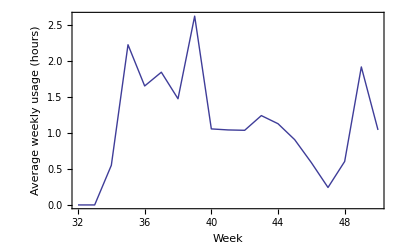

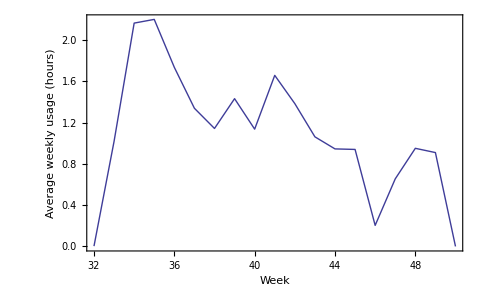

```mathematica
ListPlot[averageweekly,PlotJoined->True,Axes->False,Frame->True,FrameStyle->Directive[16],PlotRange->All,PlotStyle->{Thick,PointSize[Large]},FrameLabel->{"Week","Average weekly usage (hours)"}]
```

## Total actual usage for all Fall 2006 students.

Fix non-numeric entry for fall 2006

```mathematica
taker[x_,n_]:=If[Abs[n]>Length[x],Join[x,Table[0,{Abs[n]-Length[x]}]],Take[x,n]]
```

Highest 15 weeks corresponding to class usage graph above, estimate off by average of 0.6, R^2=0.002.
Get average agreement if we average highest 4 weeks of semester, R^2=0.002.
If we take last 5 weeks of the semester, we get an R^2=0.07. (Fall 2005)

```mathematica
reportedtime=Map[{Mean[taker[Map[Last,Sort[adjustedusage[#]]],-15]]/3600.0,Select[questions,Function[s,First[s]==#]][[1,hourscolumn]]}&,subjects]
```

{{2.0078,4},{1.34652,5},{1.4972,0},{1.94352,1},{0.50687,0.5},{1.50204,2},{1.38767,1},{1.58961,1},{0.862537,3.5},{1.45548,1},{1.7612,3},{0.888111,5},{0.989019,1.5},{0.856111,1},{1.36928,1.5},{1.74587,5},{0.998907,2},{1.36287,4},{1.26504,0},{1.21602,3},{1.53867,0},{0.985685,2.5},{1.56811,3},{1.46035,1},{1.29935,4},{1.14928,1},{1.613,1.5},{2.09126,6},{2.28839,5},{1.12178,1},{1.61322,1},{1.26989,2},{0.704556,4},{1.66504,7},{0.745944,2},{1.51535,3.5},{1.18874,4},{1.36111,3},{3.11167,2.5},{1.19191,5.5},{2.09309,5},{1.57683,3},{1.09987,1},{3.36665,3},{1.40841,4.5},{1.92481,3},{1.76826,5},{1.06276,5},{2.2688,4},{0.151519,1},{0.86237,2},{1.11954,4},{0.965037,5},{1.75487,2},{1.2283,4},{1.26346,5},{2.22802,4},{0.803704,5},{1.51424,5},{1.35569,3},{1.00148,3},{1.45985,3},{0.643537,1.5},{1.01944,0},{1.36767,4},{1.29546,5},{1.03239,0},{1.54554,4},{1.41935,8},{1.7258,5}}

```mathematica
Function[x,Append[x,x[[2]]/x[[1]]]][Map[Mean,Transpose[reportedtime]]]
```

{1.40517,3.02143,2.15023}

mean and st. dev. of each case, do a t - test to show they are different.  And to popluations with major.  Histogram of # weeks vs # hours.

```mathematica
<<LinearRegression`
```

```mathematica
Regress[reportedtime,{x},x,IncludeConstant->False]
```

DesignedRegress::tsos: Warning: the total sum of squares in the ANOVATable is uncorrected (not centered on the response mean) when there is no constant term in the model; it is designated U Total.

DesignedRegress::rsqr: Warning: the RSquared and AdjustedRSquared diagnostics are redefined when there is no constant term in the model.

{ParameterTable→ | Estimate | SE | TStat | PValue
x | 1.97897 | 0.15361 | 12.8831 | 0.,RSquared→0.706351,AdjustedRSquared→0.702095,EstimatedVariance→3.70998,ANOVATable→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 1 | 615.761 | 615.761 | 165.974 | 0.
Error | 69 | 255.989 | 3.70998 |  | 
U Total | 70 | 871.75 |  |  | }

```mathematica
Regress[reportedtime,{x},x]
```

{ParameterTable→ | Estimate | SE | TStat | PValue
1 | 1.98984 | 0.621657 | 3.20086 | 0.00208372
x | 0.734141 | 0.414794 | 1.76989 | 0.0812282,RSquared→0.0440377,AdjustedRSquared→0.0299795,EstimatedVariance→3.27161,ANOVATable→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 1 | 10.2484 | 10.2484 | 3.13251 | 0.0812282
Error | 68 | 222.469 | 3.27161 |  | 
Total | 69 | 232.718 |  |  | }

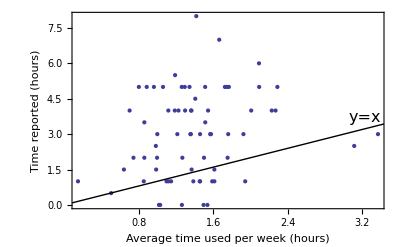

```mathematica
ListPlot[reportedtime,Axes->False,Frame->True,FrameLabel->{"Average time used per week (hours)","Time reported (hours)"},
Epilog->{Thick,Line[{{0,0},{10,10}}],Text[Style["y=x",16],{3.4,3.4},{1,-1}]},PlotRange->All,FrameStyle->Directive[16],PlotStyle->{Thick,PointSize[Large]}]
```

## Usage reported versus actual usage for Fall 2006 students.

## No corrolation seen: R^2 = 0.04 Students over-estimate their use by 75%.

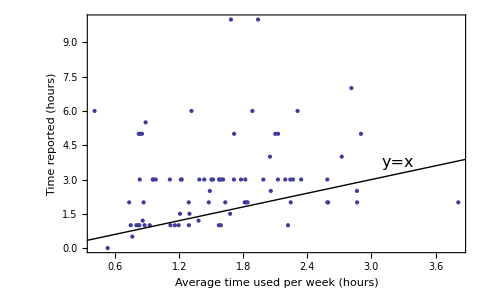

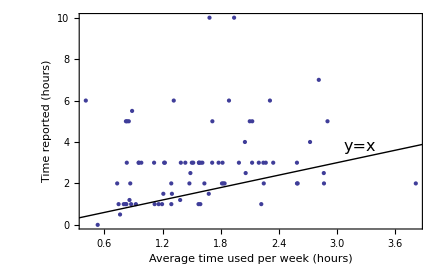

```mathematica
<<MultivariateStatistics`
```

```mathematica
TableForm[Round[Correlation[N[Select[Map[(#[[{q1column,q3column,q4column,hourscolumn,q28column,q30column}]])&,questions],MatchQ[#,{__?NumberQ}]&]]],0.001],TableHeadings->{#,#}&[{"Q1","Q3","Q4","Q20","Q28","Q30"}]]
```

Part::partw: Part {6, 8, 9, 39, 47, 49} of {"080744", "EAS", "6543", 4., "WINT", 2, 3, 2, 1, 2, « 38 »} does not exist.

Part::partw: Part {6, 8, 9, 39, 47, 49} of {"083036", "EAS", "6543", 3.82, "WINT", 4, 5, 2, 5, 2, « 38 »} does not exist.

Part::partw: Part {6, 8, 9, 39, 47, 49} of {"083756", "EAS", "3324", 4., "TREACY", 2, 2, 4, 2, 4, « 38 »} does not exist.

General::stop: Further output of Part :: "partw" will be suppressed during this calculation.

| Q1 | Q3 | Q4 | Q20 | Q28 | Q30
Q1 | 1. | 0.667 | -0.597 | 0.066 | 0.74 | 0.746
Q3 | 0.667 | 1. | -0.551 | 0.188 | 0.693 | 0.744
Q4 | -0.597 | -0.551 | 1. | 0.219 | -0.585 | -0.55
Q20 | 0.066 | 0.188 | 0.219 | 1. | 0.042 | 0.121
Q28 | 0.74 | 0.693 | -0.585 | 0.042 | 1. | 0.697
Q30 | 0.746 | 0.744 | -0.55 | 0.121 | 0.697 | 1.

## Corollation between questionnaire responses for Fall 2006 students

## Q1: Was Andes more effective for doing homework vice doing homework in a more traditional fashion and turning it in? Q3: Do you think you learned more or less using Andes than if you had done the same exercises with pencil and paper? Q4: Would you have done the same number of exercises correctly with pencil and paper? Q20: On the average how many hours/wk did you work on Andes? Q28: All SP211 students should be required to use Andes. Q30: Compare your experience with Andes with your knowledge of other learning tools used at USNA like WebAssign, Blackboard or the on-line Chemistry assignments. Please circle the tool used for comparison.

| Q1 | Q3 | Q4 | Q20 | Q28 | Q30
Q1 | 1. | 0.782 | -0.483 | 0.029 | 0.682 | 0.718
Q3 | 0.782 | 1. | -0.451 | -0.001 | 0.645 | 0.698
Q4 | -0.483 | -0.451 | 1. | -0.086 | -0.36 | -0.417
Q20 | 0.029 | -0.001 | -0.086 | 1. | 0.018 | 0.009
Q28 | 0.682 | 0.645 | -0.36 | 0.018 | 1. | 0.718
Q30 | 0.718 | 0.698 | -0.417 | 0.009 | 0.718 | 1.

## All responses are highly corrolated, except Q20.

## Conclusions:

### Survey results for time do not corrolate with actual usage.

### Need to remove redundant questions; can use log file analysis instead.

### Future: Embed survey questions in Andes tutor itself.

```mathematica
timeprediction=Select[Map[Function[s,Append[Select[questions,(First[#]==s)&][[1,{q1column,q3column,q4column,q28column,q30column,hourscolumn}]],Select[median,(First[#]==s)&][[1,2]]]],students],MatchQ[#,{__?NumberQ}]&]
```

{{1,2,5,2,2,2,2.13889},{2,2,5,2,2,3,2.35222},{2,2,4,2,1,1.5,1.06306},{1,1,5,1,1,3,1.79639},{4,3,3,5,4,2.5,1.21764},{1,1,4,1,1,10,1.9175},{2,1,5,2,1,2.5,2.4825},{5,4,4,5,3,2,1.13819},{3,4,4,3,2,1.2,0.877639},{2,3,4,2,1,3,1.05458},{3,3,2,5,5,1.5,0.880556},{2,2,4,1,1,1,0.709444},{4,4,2,5,4,5,1.86639},{4,4,2,3,3,1.5,1.50792},{1,3,5,2,1,1,0.968611},{1,2,5,5,1,5,2.36833},{2,2,3,3,1,2,2.82167},{1,2,4,3,1,1,0.578611},{4,4,5,3,1,2,2.61681},{3,2,4,5,3,3,0.9475},{1,4,4,2,1,3,1.26972},{2,2,3,2,1,3,1.00667},{3,2,3,3,3,10,1.24111},{5,4,2,5,3,6,1.33361},{5,5,5,5,5,2,0.781667},{3,4,2,4,3,1.2,1.37222},{2,2,4,2,1,2,1.65528},{2,2,3,3,2,1,0.855556},{3,3,5,5,5,1,0.951944},{1,2,4,5,2,2,1.44014},{5,5,1,5,3,5.5,0.818194},{3,2,5,2,2,3,1.40722},{2,4,5,4,2,3,1.37194},{5,5,1,5,2,7,2.94417},{3,4,2,5,4,1,0.448611},{4,4,3,3,4,3,1.51667},{2,2,4,3,1,3,2.29861},{2,2,2,3,2,1,1.78889},{2,2,4,2,2,6,2.11528},{4,4,4,5,5,3,1.33208},{5,5,2,3,2,5,1.82417},{3,4,3,5,2,1,1.39583},{3,3,2,3,2,1,0.815833},{4,4,1,5,5,3,0.736944},{4,5,2,5,3,3,0.5575},{3,5,3,5,5,6,0.408333},{1,1,5,5,1,6,1.20028},{5,5,3,5,5,0.5,0.896944},{4,4,3,5,4,3,1.24708},{5,5,3,5,4,2,1.08583},{1,3,5,3,1,3,1.105},{3,3,4,3,2,2.5,2.36069},{1,1,5,1,1,3,2.57139},{5,5,1,5,5,3,0.805556},{5,5,3,5,5,5,0.948889},{3,2,3,4,2,3,2.0725},{2,3,2,4,3,3,0.508611},{3,4,4,5,3,2,3.78375},{5,5,1,5,5,1,1.03667},{3,2,5,5,1,3,1.96333},{4,4,3,4,3,2,1.36944},{4,4,4,5,4,3,1.14181},{4,3,3,3,2,5,1.67667},{1,1,4,1,1,1,0.83},{1,1,5,1,1,4,1.6575},{4,2,3,5,4,3,1.39653},{1,1,4,1,1,3,1.82986},{4,4,2,5,4,1,0.776944},{3,5,5,4,5,4,2.54056},{4,2,4,4,2,1,1.54764},{4,4,1,5,4,3,1.46028},{2,1,4,3,2,2,2.52819},{1,1,4,2,1,3,0.8975},{5,4,4,5,3,0,0.595278},{2,3,5,3,2,2,1.63722}}

```mathematica
Regress[timeprediction,{x1,x2,x3,x4,x5,x6},{x1,x2,x3,x4,x5,x6}]
```

{ParameterTable→ | Estimate | SE | TStat | PValue
1 | 0.909944 | 0.455585 | 1.99731 | 0.0497948
x1 | 0.131175 | 0.097634 | 1.34354 | 0.183565
x2 | -0.05178 | 0.0939468 | -0.551163 | 0.583328
x3 | 0.13502 | 0.0728119 | 1.85437 | 0.0680235
x4 | 0.0147554 | 0.0799952 | 0.184454 | 0.854206
x5 | -0.166672 | 0.0846532 | -1.96888 | 0.0530439
x6 | 0.075143 | 0.0388604 | 1.93366 | 0.0573181,RSquared→0.202491,AdjustedRSquared→0.132122,EstimatedVariance→0.402202,ANOVATable→ | DF | SumOfSq | MeanSq | FRatio | PValue
Model | 6 | 6.9442 | 1.15737 | 2.87758 | 0.0147218
Error | 68 | 27.3497 | 0.402202 |  | 
Total | 74 | 34.2939 |  |  | }

```mathematica
TableForm[Correlation[timeprediction]]
```

1. | 0.775237 | -0.562915 | 0.672246 | 0.706436 | 0.00160604 | -0.178185
0.775237 | 1. | -0.498937 | 0.639275 | 0.685219 | -0.0434512 | -0.247611
-0.562915 | -0.498937 | 1. | -0.429871 | -0.468946 | -0.0680614 | 0.2844
0.672246 | 0.639275 | -0.429871 | 1. | 0.715651 | -0.0281883 | -0.217818
0.706436 | 0.685219 | -0.468946 | 0.715651 | 1. | -0.0395733 | -0.333443
0.00160604 | -0.0434512 | -0.0680614 | -0.0281883 | -0.0395733 | 1. | 0.211987
-0.178185 | -0.247611 | 0.2844 | -0.217818 | -0.333443 | 0.211987 | 1.

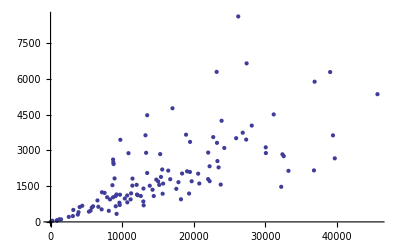

```mathematica
ListPlot[Map[(#[[{2,4}]])&,frustration]]
```

```mathematica
Map[D[Fit[#,{1,x},x],x]&,Map[#[[{1,4}]]&,Map[#[[2]]&,frustration],{2}]]
```

{4.02027,8.28606,-4.87927,-0.432722,22.6807,37.9746,3.38889,3.33779,6.11785,36.3025,0.0606061,-2.03466,-10.1978,1.07092,2.56635,-1.46296,-4.775,0.5,5.81569,-20.7118,-3.70492,3.82702,84.2601,27.0855,4.22384,1.60588,47.5,11.1468,-1.38653,-7.03889,0,-9.73333,-1.35841,11.8028,1.73661,30.842,-0.237697,-1.82857,15.5479,4.39444,-9.18962,16.5643,3.53317,7.93471,1.84579,-8.18529,44.6767,0.0558087,1.01981,-2.01201,6.19728,10.5476,3.70484,-1.5082,5.59169,-4.42382,3.17559,3.51958,1.72167,22.8055,34.3346,-0.667308,12.4173,17.7713,-2.8894,-7.42204,7.97576,-1.737,-0.853748,0.207,-3.74374,4.21142,-3.74622,-8.05698,-24.9363,11.6599,7.69212,-8.04146,-6.99419,5.68043,16.1642,16.4769,-1.13909,-2.98981,26.8883,20.7213,0.374046,-7.14643,-23.,11.3701,6.49048,0.237745,10.4423,-25.6652,1.91065,12.8478,6.14502,0.748894,34.2242,1.96786,-0.849372,19.8626,-3.79103,6.7819,4.28505,-14.8473,-3.97119,1.35507,11.4366,17.5434,10.005,-10.2444,15.5,-12.15,28.8513,-8.34977}

```mathematica
Map[#[[2]]&,frustration]
```